# CFD Boundary Optimization

## BYU GR Research Group

```mathematica
Clear["`*"]
SetDirectory[NotebookDirectory[]];
howBig[x_]:=Module[{},UnitConvert[Quantity[ByteCount[x],"Bytes"],"Gigabytes"]//N]
(*DumpSave["filename.mx","Global`varname"];*)
```

# P4 (A4) Scheme

## Initialization

This code for the P4 follows the procedure in Section 2.2 of Kim (2024).

The matrix system of equations we are solving for this scheme is:
	P=(1
γ_10
γ_20
0
0
0
0 γ_01
1
γ_21
β
0
0
0 γ_02
γ_12
1
α
γ_24
0
0 0
γ_13
γ_23
1
γ_23
γ_13
0 0
0
γ_24
α
1
γ_12
γ_02 0
0
0
β
γ_21
1
γ_01 0
0
0
0
γ_20
γ_10
1)
	Q=(a_00
a_10
a_20
-a_3
-a_26
-a_16
-a_06 a_01
a_11
a_21
-a_2
-a_25
-a_15
-a_05 a_02
a_12
a_22
-a_1
-a_24
-a_14
-a_04 a_03
a_13
a_23
0
-a_23
-a_13
-a_03 a_04
a_14
a_24
a_1
-a_22
-a_12
-a_02 a_05
a_15
a_25
a_2
-a_21
-a_11
-a_01 a_06
a_16
a_26
a_3
-a_20
-a_10
-a_00)

```mathematica
(*From KimInteriorOptimization.nb, one day to be merged with this one. Or I could DumpSave[] in that notebook and then Get[] here.*)
interiorCoeffsP4={α->0.5770460201292381,β->0.08900836845092142,a1->0.6517078440898839,a2->0.24815882627035918,a3->0.006009630649852392};

(*If you have the .mx files in the same directory as this notebook, these will let you skip the long computation of defining bdCoeffs under the "Solve for Boundary Coefficients" section*)
Get["P4_bdCoeffs0.mx"]
Get["P4_bdCoeffs1.mx"]
Get["P4_bdCoeffs2.mx"]
```

## General Extrapolation Polynomial

The only settings the user should have to change for a different (first derivative) scheme are:
	- LHSBandCount
	- n
	- freeInteriorPars
	- yDeriv
For the P4 (A4) scheme, we have:
	LHSBandCount = 5
	n = 4
	freeInteriorPars = 3
	yDeriv = 8

```mathematica
(*User chooses these parameters, the rest is calculated from these*)
LHSBandCount=5; (*3 for tridiagonal, 5 for pentadiagonal*)
n=4; (*order of the scheme*)
freeInteriorPars=3; (*number of free parameters used for Kim's optimization on the interior*)
yDeriv=8; (*(d^n P)/dx^n(ŷ)=0 from Kim 2024 Eq. 10, this is n in that equation*) (*provide constraints on what the user can choose for this. Upper bound should be polynomialorder to prevent the matrix from being singular, and lower bound should be order·2 I think.*)

LHSPars=Switch[LHSBandCount,3,{α},5,{α,β}];
RHSPars=Table[ToExpression[StringJoin["a",ToString[i]]],{i,1,Ceiling[n/2]-Length@LHSPars+freeInteriorPars}];
numBoundaryRows=Length@RHSPars;
fOrder=(2*Length@RHSPars)+1;
fpOrder=LHSBandCount+(numBoundaryRows-(LHSBandCount-1)/2);
PolynomialOrder=fOrder+fpOrder;


rowf1=Join[{1},Table[0,{i,1,PolynomialOrder}]];
rowf=Table[Table[i^j,{j,0,PolynomialOrder}],{i,1,fOrder-1}];
rowfp1=Join[{0,1},Table[0,{i,2,PolynomialOrder}]];
rowfp=Table[Table[j i^(j-1),{j,0,PolynomialOrder}],{i,1,fpOrder-1}];
rowyHat=Join[Table[0,{i,1,yDeriv}],Table[(i!)/((i-yDeriv)!) yHat^(i-yDeriv),{i,yDeriv,PolynomialOrder}]];

matf=PrependTo[rowf,rowf1];
matfp=PrependTo[rowfp,rowfp1];
matfCombined=Join[matf,matfp];
LMat=AppendTo[matfCombined,rowyHat];

pVec=Table[ToExpression[StringJoin["p",ToString[i]]],{i,0,PolynomialOrder}];
fVec=Join[Table[ToExpression[StringJoin["f",ToString[i]]],{i,0,fOrder-1}],Table[ToExpression[StringJoin["fp",ToString[i]]],{i,0,fpOrder-1}],{0}];

pCoeffs=Solve[LMat.pVec==fVec,pVec][[1]];

yHatSingularities=(Transpose@Solve[Det[LMat]==0,yHat])[[1]]//N;
P[x_]=Total[Table[pVec[[i+1]]*x^i,{i,0,PolynomialOrder}]]/.pCoeffs;

Print["System:\n",MatrixForm[LMat]," ",MatrixForm[pVec]," = ",MatrixForm[fVec]]
Print["Singularities:\n",MatrixForm[yHatSingularities]]
(*Print["Coefficients:\n",MatrixForm[pCoeffs]]*)
```

System:
(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 4 | 8 | 16 | 32 | 64 | 128 | 256 | 512 | 1024 | 2048 | 4096 | 8192
1 | 3 | 9 | 27 | 81 | 243 | 729 | 2187 | 6561 | 19683 | 59049 | 177147 | 531441 | 1594323
1 | 4 | 16 | 64 | 256 | 1024 | 4096 | 16384 | 65536 | 262144 | 1048576 | 4194304 | 16777216 | 67108864
1 | 5 | 25 | 125 | 625 | 3125 | 15625 | 78125 | 390625 | 1953125 | 9765625 | 48828125 | 244140625 | 1220703125
1 | 6 | 36 | 216 | 1296 | 7776 | 46656 | 279936 | 1679616 | 10077696 | 60466176 | 362797056 | 2176782336 | 13060694016
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
0 | 1 | 4 | 12 | 32 | 80 | 192 | 448 | 1024 | 2304 | 5120 | 11264 | 24576 | 53248
0 | 1 | 6 | 27 | 108 | 405 | 1458 | 5103 | 17496 | 59049 | 196830 | 649539 | 2125764 | 6908733
0 | 1 | 8 | 48 | 256 | 1280 | 6144 | 28672 | 131072 | 589824 | 2621440 | 11534336 | 50331648 | 218103808
0 | 1 | 10 | 75 | 500 | 3125 | 18750 | 109375 | 625000 | 3515625 | 19531250 | 107421875 | 585937500 | 3173828125
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 40320 | 362880 yHat | 1814400 yHat^2 | 6652800 yHat^3 | 19958400 yHat^4 | 51891840 yHat^5) (p0
p1
p2
p3
p4
p5
p6
p7
p8
p9
p10
p11
p12
p13) = (f0
f1
f2
f3
f4
f5
f6
fp0
fp1
fp2
fp3
fp4
fp5
0)

Singularities:
(yHat→1.23232
yHat→2.01136
yHat→2.75838
yHat→3.50832
yHat→4.33577)

## Solve for Boundary Coefficients

Goal:
	Solve a system of equations for bdCoeffsList2 in terms of the optimization free parameter ŷ
Variables:
	fVars2: List of f_i and f_i' variables that will appear in the shifted stencil for Node 2
	bdCoeffsList2: List of boundary coefficients that will appear in the shifted stencil for Node 2
	schemeShifted: The shifted scheme for Node 2 (Kim 2024 Eq. 13a)
	schemeCentered: The centered scheme for Node 2 in terms of the extrapolation polynomial P(x) (Kim 2024 Eq. 12a)
		NOTE: To make the Collect[] process easier, we write these schemes as LHS-RHS=0 rather than the usual LHS=RHS.
	schemeNode3: The scheme for Node 3, which only depends on interiorCoeffsP4
	SOLfp5: The solution to Node 3’s scheme equation for f_5' in terms of fVars2
	eq: Scheme equation where the coefficient terms from schemeCentered and schemeShifted are set equal to each other
	coeffEqs2: System of equations with each of the coefficient terms equal to each other
	bdCoeffs2: Solution to the system of equations for bdCoeffsList2 in terms of ŷ
Process:
	1. Initialize the necessary equations.
	2. We want schemeShifted and schemeCentered to both be in terms of fVars2 with some coefficients. Due to the presence of P(x) terms in schemeCentered, it is in terms of fVars2 as well as f_5'. We eliminate the dependence on f_5' by using Node 3’s scheme to solve for f_5' in terms of fVars2.
	3. Now that schemeShifted and schemeCentered are both in terms of fVars2, we construct a system of equations by equating the coefficient in front of each term of fVars2 in schemeCentered with the corresponding coefficient in front of the same term in schemeShifted.
	4. We solve this system of equations for bdCoeffsList2 in terms of interiorCoeffsP4 (which are substituted in) and the optimization free parameter ŷ.
		NOTE: In the standard scheme approach, we set γ_22=1 to ensure the main diagonal of the LHS matrix is all 1’s. When solving this system of equations, we must include γ_22 so that bdCoeffsList2 and fVars2 have the same length since this allows us to find a unique solution to the system of equations. We apply the normal condition later on.
	5. OPTIONAL: We may save the variable bdCoeffs2 to a binary file in the current directory. This is helpful to avoid having to run this process multiple times, as it can become computationally expensive.
Differences:
	For Node 1 and Node 0, the entire process translates directly with a few changes. fVars, bdCoeffsList, schemeShifted, and schemeCentered all change, as we are considering the scheme for a different row, but the equations have the same structure. The main notable difference is in Step 2; In addition to substituting in the solution from Node 3 for f_5' in terms of the other fVars, we must also do the same for f_4' (Nodes 1 and 0) and f_3' (Node 0) using Nodes 2 and 1, respectively.

### Node 2

```mathematica
(*----------STEP 1----------*)
fVars2={fp0,fp1,fp2,fp3,fp4,f0,f1,f2,f3,f4,f5,f6};
bdCoeffsList2={γ20,γ21,γ22,γ23,γ24,a20,a21,a22,a23,a24,a25,a26};
schemeShifted=γ20 fp0+γ21 fp1+γ22 fp2+γ23 fp3+γ24 fp4-(a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6); (*==0*)
schemeCentered=β fp0+α fp1+fp2+α fp3+β fp4-(-a3 P[-1]-a2 f0-a1 f1+a1 f3+a2 f4+a3 f5); (*==0*)

(*----------STEP 2----------*)
schemeNode3=β fp1+α fp2+fp3+α fp4+β fp5==-a3 f0-a2 f1-a1 f2+a1 f4+a2 f5+a3 f6;
SOLfp5=Solve[schemeNode3,fp5][[1,1]]/.interiorCoeffsP4;
schemeCentered=schemeCentered/.SOLfp5;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars2];

(*----------STEP 4----------*)
coeffEqs2=Table[Coefficient[eq,fVars2[[i]]]==0,{i,1,Length@fVars2}];
bdCoeffs2=(Solve[coeffEqs2,bdCoeffsList2][[1]])/.interiorCoeffsP4;

(*----------STEP 5----------*)
(*DumpSave["P4_bdCoeffs2.mx","Global`bdCoeffs2"]*)
```

### Node 1

```mathematica
(*----------STEP 1----------*)
fVars1={fp0,fp1,fp2,fp3,f0,f1,f2,f3,f4,f5,f6};
bdCoeffsList1={γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14,a15,a16};
schemeShifted=γ10 fp0+γ11 fp1+γ12 fp2+γ13 fp3-(a10 f0+a11 f1+a12 f2+a13 f3+a14 f4+a15 f5+a16 f6); (*==0*)
schemeCentered=β P'[-1]+α fp0+fp1+α fp2+β fp3-(-a3 P[-2]-a2 P[-1]-a1 f0+a1 f2+a2 f3+a3 f4); (*==0*)

(*----------STEP 2----------*)
schemeNode3=β fp1+α fp2+fp3+α fp4+β fp5==-a3 f0-a2 f1-a1 f2+a1 f4+a2 f5+a3 f6;
schemeNode2=γ20 fp0+γ21 fp1+γ22 fp2+γ23 fp3+γ24 fp4==a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6;

SOLfp5=Solve[schemeNode3,fp5][[1,1]]/.interiorCoeffsP4;
SOLfp4=Solve[schemeNode2,fp4][[1,1]]/.bdCoeffs2;
schemeCentered=schemeCentered/.SOLfp5/.SOLfp4;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars1];

(*----------STEP 4----------*)
coeffEqs1=Table[Coefficient[eq,fVars1[[i]]]==0,{i,1,Length@fVars1}];
bdCoeffs1=(Solve[coeffEqs1,bdCoeffsList1][[1]])/.interiorCoeffsP4;

(*----------STEP 5----------*)
(*DumpSave["P4_bdCoeffs1.mx","Global`bdCoeffs1"]*)
```

### Node 0

```mathematica
(*----------STEP 1----------*)
fVars0={fp0,fp1,fp2,f0,f1,f2,f3,f4,f5,f6};
bdCoeffsList0={γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06};
schemeShifted=γ00 fp0+γ01 fp1+γ02 fp2-(a00 f0+a01 f1+a02 f2+a03 f3+a04 f4+a05 f5+a06 f6); (*==0*)
schemeCentered=β P'[-2]+α P'[-1]+fp0+α fp1+β fp2-(-a3 P[-3]-a2 P[-2]-a1 P[-1]+a1 f1+a2 f2+a3 f3); (*==0*)

(*----------STEP 2----------*)
schemeNode3=β fp1+α fp2+fp3+α fp4+β fp5==-a3 f0-a2 f1-a1 f2+a1 f4+a2 f5+a3 f6;
schemeNode2=γ20 fp0+γ21 fp1+γ22 fp2+γ23 fp3+γ24 fp4==a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6;
schemeNode1=γ10 fp0+γ11 fp1+γ12 fp2+γ13 fp3==a10 f0+a11 f1+a12 f2+a13 f3+a14 f4+a15 f5+a16 f6;

SOLfp5=Solve[schemeNode3,fp5][[1,1]]/.interiorCoeffsP4;
SOLfp4=Solve[schemeNode2,fp4][[1,1]]/.bdCoeffs2;
SOLfp3=Solve[schemeNode1,fp3][[1,1]]/.bdCoeffs1;
schemeCentered=schemeCentered/.SOLfp5/.SOLfp4/.SOLfp3;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars0];

(*----------STEP 4----------*)
coeffEqs0=Table[Coefficient[eq,fVars0[[i]]]==0,{i,1,Length@fVars0}];
bdCoeffs0=(Solve[coeffEqs0,bdCoeffsList0][[1]])/.interiorCoeffsP4;

(*----------STEP 5----------*)
(*DumpSave["P4_bdCoeffs0.mx","Global`bdCoeffs0"]*)
```

## Optimize ŷ

### Set and Normalize Coefficients

We normalize the coefficients so that the main diagonal of the LHS matrix is all 1’s, but we leave the coefficients in terms of the optimization free parameter ŷ so that we can optimize over it.

```mathematica
Clear[γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26]
Clear[γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06]

{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}=1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2;
{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}=1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1;
{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}=1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0;
```

### Node 2

```mathematica
𝔸2[κ_]=γ20+γ21 Cos[κ]+Cos[2 κ]+γ23 Cos[3 κ]+γ24 Cos[4 κ];
𝔹2[κ_]=γ21 Sin[κ]+Sin[2 κ]+γ23 Sin[3 κ]+γ24 Sin[4 κ];
ℂ2[κ_]=a20+a21 Cos[κ]+a22 Cos[2 κ]+a23 Cos[3 κ]+a24 Cos[4 κ]+a25 Cos[5 κ]+a26 Cos[6 κ];
𝔻2[κ_]=a21 Sin[κ]+a22 Sin[2 κ]+a23 Sin[3 κ]+a24 Sin[4 κ]+a25 Sin[5 κ]+a26 Sin[6 κ];
κBar2Re[κ_]=(𝔸2[κ]*𝔻2[κ]-𝔹2[κ]*ℂ2[κ])/((𝔸2[κ])^2+(𝔹2[κ])^2);
κBar2Im[κ_]=(-𝔸2[κ]*ℂ2[κ]-𝔹2[κ]*𝔻2[κ])/((𝔸2[κ])^2+(𝔹2[κ])^2);
κBar2Norm[κ_]=Abs[κBar2Re[κ]+I*κBar2Im[κ]];
```

```mathematica
Δ2Re[κ_]=(κ*((𝔸2[κ])^2+(𝔹2[κ])^2)-(𝔸2[κ]*𝔻2[κ]-𝔹2[κ]*ℂ2[κ]))^2;
Δ2Im[κ_]=(0*((𝔸2[κ])^2+(𝔹2[κ])^2)-(-𝔸2[κ]*ℂ2[κ]-𝔹2[κ]*𝔻2[κ]))^2;
Δ2Norm[κ_]=(κ-κBar2Norm[κ])^2;
Δ2Norm2[κ_]=(Abs[(κ*((𝔸2[κ])^2+(𝔹2[κ])^2)-((𝔸2[κ]*𝔻2[κ]-𝔹2[κ]*ℂ2[κ])+I*(-𝔸2[κ]*ℂ2[κ]-𝔹2[κ]*𝔻2[κ])))])^2;
Δ2Norm2[κ_]=((κ*((𝔸2[κ])^2+(𝔹2[κ])^2)-Norm[((𝔸2[κ]*𝔻2[κ]-𝔹2[κ]*ℂ2[κ])+I*(-𝔸2[κ]*ℂ2[κ]-𝔹2[κ]*𝔻2[κ]))]))^2;
```

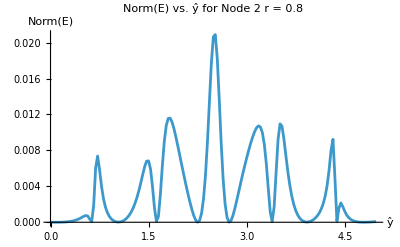

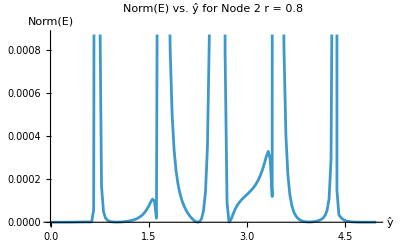

Evaluation time: 17.615949

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat2Array=Range[0,5,0.03];
Δ2NormArray=Table[Δ2Norm[κ]/.{yHat->yHat2Array[[i]]},{i,1,Length@yHat2Array}];
ENorm2Array=Table[NIntegrate[Δ2NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat2Array}];

ListPlot[Transpose@{yHat2Array,ENorm2Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 2\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

yHat22Array=Range[0,5,0.03];
Δ22NormArray=Table[Δ2Norm2[κ]/.{yHat->yHat22Array[[i]]},{i,1,Length@yHat22Array}];
ENorm22Array=Table[NIntegrate[Δ22NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat22Array}];

ListPlot[Transpose@{yHat22Array,ENorm22Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 2\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

### Node 1

```mathematica
𝔸1[κ_]=γ10+Cos[κ]+γ12 Cos[2 κ]+γ13 Cos[3 κ];
𝔹1[κ_]=Sin[κ]+γ12 Sin[2 κ]+γ13 Sin[3 κ];
ℂ1[κ_]=a10+a21 Cos[κ]+a12 Cos[2 κ]+a13 Cos[3 κ]+a14 Cos[4 κ]+a15 Cos[5 κ]+a16 Cos[6 κ];
𝔻1[κ_]=a11 Sin[κ]+a12 Sin[2 κ]+a13 Sin[3 κ]+a14 Sin[4 κ]+a15 Sin[5 κ]+a16 Sin[6 κ];
κBar1Re[κ_]=(𝔸1[κ]*𝔻1[κ]-𝔹1[κ]*ℂ1[κ])/((𝔸1[κ])^2+(𝔹1[κ])^2);
κBar1Im[κ_]=(-𝔸1[κ]*ℂ1[κ]-𝔹1[κ]*𝔻1[κ])/((𝔸1[κ])^2+(𝔹1[κ])^2);
κBar1Norm[κ_]=Abs[κBar1Re[κ]+I*κBar1Im[κ]];
```

```mathematica
Δ1Re[κ_]=(κ*((𝔸1[κ])^2+(𝔹1[κ])^2)-(𝔸1[κ]*𝔻1[κ]-𝔹1[κ]*ℂ1[κ]))^2;
Δ1Im[κ_]=(0*((𝔸1[κ])^2+(𝔹1[κ])^2)-(-𝔸1[κ]*ℂ1[κ]-𝔹1[κ]*𝔻1[κ]))^2;
Δ1Norm[κ_]=(κ-κBar1Norm[κ])^2;
```

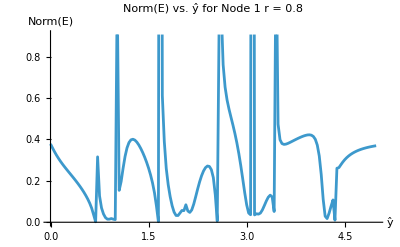

Evaluation time: 29.597653

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat1Array=Range[0,5,0.03];
Δ1NormArray=Table[Δ1Norm[κ]/.{yHat->yHat1Array[[i]]},{i,1,Length@yHat1Array}];
ENorm1Array=Table[NIntegrate[Δ1NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat1Array}];

ListPlot[Transpose@{yHat1Array,ENorm1Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 1\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

### Node 0

```mathematica
𝔸0[κ_]=1+γ01 Cos[κ]+γ02 Cos[2 κ];
𝔹0[κ_]=γ01 Sin[κ]+γ02 Sin[2 κ];
ℂ0[κ_]=a00+a01 Cos[κ]+a02 Cos[2 κ]+a03 Cos[3 κ]+a04 Cos[4 κ]+a05 Cos[5 κ]+a06 Cos[6 κ];
𝔻0[κ_]=a01 Sin[κ]+a02 Sin[2 κ]+a03 Sin[3 κ]+a04 Sin[4 κ]+a05 Sin[5 κ]+a06 Sin[6 κ];
κBar0Re[κ_]=(𝔸0[κ]*𝔻0[κ]-𝔹0[κ]*ℂ0[κ])/((𝔸0[κ])^2+(𝔹0[κ])^2);
κBar0Im[κ_]=(-𝔸0[κ]*ℂ0[κ]-𝔹0[κ]*𝔻0[κ])/((𝔸0[κ])^2+(𝔹0[κ])^2);
κBar0Norm[κ_]=Abs[κBar0Re[κ]+I*κBar0Im[κ]];
```

```mathematica
Δ0Re[κ_]=(κ*((𝔸0[κ])^2+(𝔹0[κ])^2)-(𝔸0[κ]*𝔻0[κ]-𝔹0[κ]*ℂ0[κ]))^2;
Δ0Im[κ_]=(0*((𝔸0[κ])^2+(𝔹0[κ])^2)-(-𝔸0[κ]*ℂ0[κ]-𝔹0[κ]*𝔻0[κ]))^2;
Δ0Norm[κ_]=(κ-κBar0Norm[κ])^2;
```

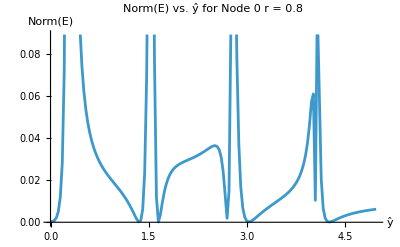

Evaluation time: 316.275076

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat0Array=Range[0,5,0.03];
Δ0NormArray=Table[Δ0Norm[κ]/.{yHat->yHat0Array[[i]]},{i,1,Length@yHat0Array}];
ENorm0Array=Table[NIntegrate[Δ0NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat0Array}];

ListPlot[Transpose@{yHat0Array,ENorm0Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 0\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

## Spectral Function

### Node 2

```mathematica
Clear[yHat]
SF2Re[κ_,yHat_]=κBar2Re[κ];
SF2Im[κ_,yHat_]=κBar2Im[κ];
SF2Norm[κ_,yHat_]=κBar2Norm[κ];
```

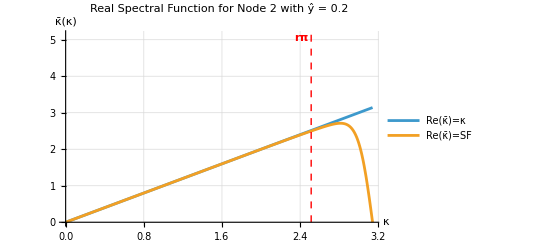

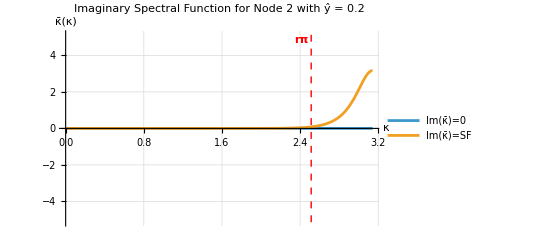

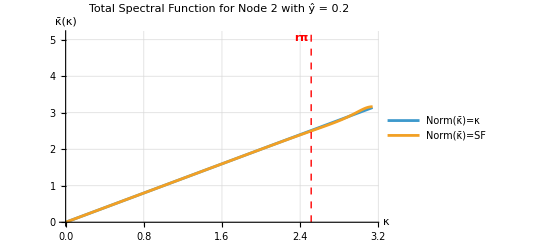

```mathematica
r=0.8;
yHat2List={(*1*)0.2,(*2*)0.63,(*3*)1.05,(*4*)1.14,(*5*)1.62,(*6*)2.25,(*7*)2.73,(*8*)3.39,(*9*)3.93,(*10*)4.38,(*11*)4.80};
yHat=yHat2List[[1]];
Plot[{κ,SF2Re[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
Plot[{0,SF2Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ,SF2Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
```

### Node 1

```mathematica
Clear[yHat]
SF1Re[κ_,yHat_]=κBar1Re[κ];
SF1Im[κ_,yHat_]=κBar1Im[κ];
SF1Norm[κ_,yHat_]=κBar1Norm[κ];
```

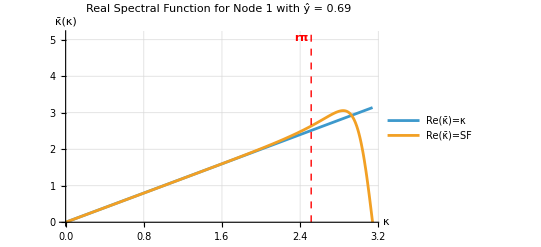

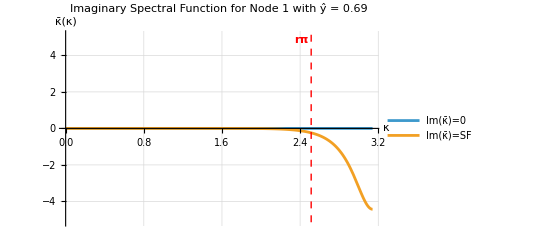

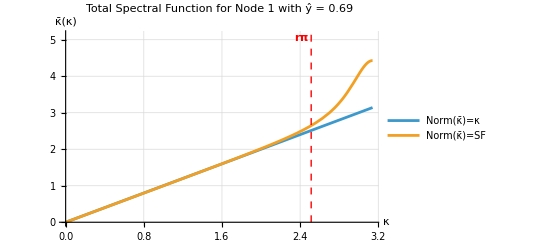

```mathematica
Clear[yHat]
r=0.8;
yHat1List={(*1*)0.69,(*2*)0.99,(*3*)1.65,(*4*)1.95,(*5*)2.13,(*6*)2.55,(*7*)3.06,(*8*)3.12,(*9*)3.42,(*10*)4.23,(*11*)4.35};
yHat=yHat1List[[1]];
Plot[{κ,SF1Re[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
Plot[{0,SF1Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ,SF1Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
```

### Node 0

```mathematica
Clear[yHat]
SF0Re[κ_,yHat_]=κBar0Re[κ];
SF0Im[κ_,yHat_]=κBar0Im[κ];
SF0Norm[κ_,yHat_]=κBar0Norm[κ];
```

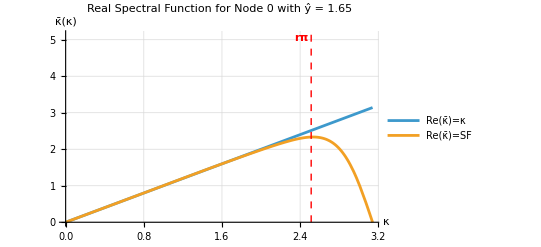

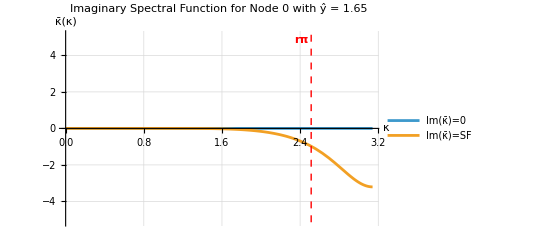

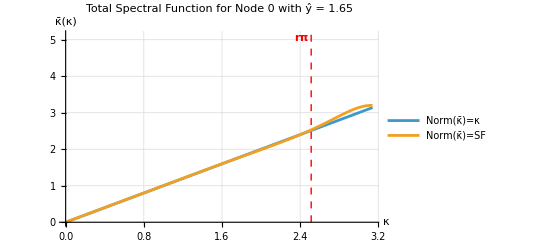

```mathematica
r=0.8;
yHat0List={(*1*)0.87,(*2*)1.89,(*3*)2.97,(*4*)4.17,(*5*)4.26}; (*old and wrong i think*)
yHat0List={(*1*)1.35,(*2*)1.65,(*3*)2.70,(*4*)3.03,(*5*)4.26}; (*new*)
yHat=yHat0List[[1]];
Plot[{κ,SF0Re[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
Plot[{0,SF0Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ,SF0Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
```

## Output Coefficients

### ŷ Definitions

```mathematica
Clear[yHat,yHat2,yHat1,yHat0]

yHat2List={(*1*)0.2,(*2*)0.63,(*3*)1.05,(*4*)1.14,(*5*)1.62,(*6*)2.25,(*7*)2.73,(*8*)3.39,(*9*)3.93,(*10*)4.38,(*11*)4.80};
yHat1List={(*1*)0.69,(*2*)0.99,(*3*)1.65,(*4*)1.95,(*5*)2.13,(*6*)2.55,(*7*)3.06,(*8*)3.12,(*9*)3.42,(*10*)4.23,(*11*)4.35};
yHat0List={(*1*)0.87,(*2*)1.89,(*3*)2.97,(*4*)4.17,(*5*)4.26};

yHat2=yHat2List[[9]];
yHat1=yHat1List[[4]];
yHat0=yHat0List[[1]];

yHat0=1.89;
yHat1=1.65;
yHat2=3.93;
```

### Define Coefficients

```mathematica
Clear[γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26]
Clear[γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06]

{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0)/.{yHat->yHat0};
```

### Luke Output

```mathematica
interiorLuke=interiorCoeffsP4/.{a1->a,a2->b,a3->c};
boundaryLuke={α12->γ01val,β12->γ02val,α21->γ10val,α22->γ12val,β22->γ13val,β31->γ20val,α31->γ21val,α32->γ23val,β32->γ24val,a1->a00val,b1->a01val,c1->a02val,d1->a03val,e1->a04val,f1->a05val,g1->a06val,a2->a10val,b2->a11val,c2->a12val,d2->a13val,e2->a14val,f2->a15val,g2->a16val,a3->a20val,b3->a21val,c3->a22val,d3->a23val,e3->a24val,f3->a25val,g3->a26val};
coeffLuke=Flatten[Join[interiorLuke,boundaryLuke]]
```

{α→0.577046,β→0.0890084,a→0.651708,b→0.248159,c→0.00600963,α12→9.8205,β12→10.2829,α21→0.0818506,α22→1.68906,β22→0.496148,β31→0.0108325,α31→0.238187,α32→1.12828,β32→0.28865,a1→-3.73445,b1→-10.7659,c1→11.1588,d1→3.89328,e1→-0.638984,f1→0.0958773,g1→-0.00859553,a2→-0.318509,b2→-1.39694,c2→0.536402,d2→1.12232,e2→0.0594506,f2→-0.00274384,g2→0.0000280668,a3→-0.0467869,b3→-0.510448,c3→-0.770033,d3→0.622893,e3→0.672713,f3→0.0330417,g3→-0.00137935}

### Nate Output

```mathematica
interiorNate=interiorCoeffsP4;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]]
```

{α→0.577046,β→0.0890084,a1→0.651708,a2→0.248159,a3→0.00600963,γ01→9.8205,γ02→10.2829,γ10→0.064325,γ12→2.25305,γ13→0.894736,γ20→0.0544813,γ21→0.576522,γ23→0.443764,γ24→0.0505936,a00→-3.73445,a01→-10.7659,a02→11.1588,a03→3.89328,a04→-0.638984,a05→0.0958773,a06→-0.00859553,a10→-0.263369,a11→-1.66816,a12→0.0404934,a13→1.75676,a14→0.142593,a15→-0.00853233,a16→0.000216697,a20→-0.201459,a21→-0.760192,a22→0.157076,a23→0.651002,a24→0.149045,a25→0.0049542,a26→-0.000425431}

### Other Results

```mathematica
Kim24={α->0.5862704032801503,β->0.0954953355017055,a->0.6431406736919156,b->0.2586011023495066,c->0.007140953479797375,α12->43.65980335321481,β12->92.40143116322876,α21->0.08351537442980239,α22->1.961483362670730,β22->0.8789761422182460,β31->0.008073091519768687,α31->0.2162434143850924,α32->1.052242062502679,β32->0.2116022463346598,a1->-6.658527037451025,b1->-86.92242000231872,c1->47.58661913475775,d1->57.30693626084370,e1->-13.71254216556246,f1->2.659826729790792,g1->-0.2598929200600359,a2->-0.3199960780333493,b2->-1.438068456255548,c2->0.07735499170041915,d2->1.496612372811008,e2->0.2046919801608821,f2->-0.02229717539815850,g2->0.001702365014746567,a3->-0.03644974757120792,b3->-0.4997030280694729,c3->-0.7861024376433451,d3->0.7439822445654316,e3->0.5629384925762924,f3->0.01563884275691290,g3->-0.0003043666146108995};
HAMR={α->0.5747612151,β->0.0879324249,a->1.3069171114/2,b->0.9828406281/4,c->0.0356295405/6,α12->9.4133049605,β12->10.7741034803,α21->0.1023343303,α22->1.8854940182,β22->0.8582327249,β31->0.0347468867,α31->0.4064246796,α32->0.7683583302,β32->0.1623349133,a1->-3.6882535854000005,b1->-10.3169611301,c1->9.6807767746,d1->5.4529053045,e1->-1.5191959829,f1->0.4834876759,g1->-0.0927590566,a2->-0.3586079596,b2->-1.3424668425,c2->0.0834751059,d2->1.4235697122,e2->0.2245783548,f2->-0.0358453729,g2->0.0052970021,a3->-0.1274311870,b3->-0.6299599564,c3->-0.3024922988999999,d3->0.6498856630,e3->0.3919470424,f3->0.0189402158,g3->-0.0008894789};
coeff=Kim24;
```

#### Kim 07 Modified Boundary Coefficients

Why is Kim 07 different than HAMR for modifying the coeffs for eigenvalue analysis? (eqs 41-45)

```mathematica
Kim07={α->0.5862704032801503,β->0.0954953355017055,a1->0.6431406736919156,a2->0.2586011023495066,a3->0.007140953479797375,γ01->5.912678614078549,γ02->3.775623951744012,γ10->0.08360703307833438,γ12->2.058102869495757,γ13->0.9704052014790193,γ20->0.03250008295108466,γ21->0.3998040493524358,γ23->0.7719261277615860,γ24->0.1626635931256900,a00->-3.240681563472493,a01->-3.456878182643609,a02->5.839043358834730,a03->1.015886726041007,a04->-0.2246526470654333,a05->0.08564940889936562,a06->-0.01836710059356763,a10->-0.3177447290722621,a11->-1.468827048894462,a12->-0.02807631929593225,a13->1.593461635747659,a14->0.2533027046976367,a15->-0.03619652460174756,a16->0.004080281419108407,a20->-0.1219006056449124,a21->-0.6301651351188667,a22->-0.3119603043096557,a23->0.6521195063966084,a24->0.3938843551210350,a25->0.01904944407973912,a26->-0.001027260523947668};
```

```mathematica
{γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.Kim07),
γ13Bar->(γ13/(1-γ10*γ01)/.Kim07),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.Kim07),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.Kim07),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.Kim07)};

Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,6}]/.Kim07;
Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,6}]/.Kim07;

barCoeffs=Join[%,%%,%%%]
```

{a21Bar→-0.296033,a22Bar→-1.50549,a23Bar→0.16354,a24Bar→1.47735,a25Bar→0.165628,a26Bar→-0.0130691,a11Bar→-2.33321,a12Bar→-1.02097,a13Bar→2.98329,a14Bar→0.538081,a15Bar→-0.0857445,a16Bar→0.0111061,γ12Bar→3.44587,γ13Bar→1.91909,γ21Bar→0.0554085,γ23Bar→1.97387,γ24Bar→0.813458}

```mathematica
Clear[LHS,RHS]
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i-2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}]

k=9; (*Size*)
MatrixForm@LHS[k]

MatrixForm@(LHS[k]/.Kim07)/.barCoeffs
```

(1 | γ12Bar | γ13Bar | 0 | 0 | 0 | 0 | 0 | 0
γ21Bar | 1 | γ23Bar | γ24Bar | 0 | 0 | 0 | 0 | 0
β | α | 1 | α | β | 0 | 0 | 0 | 0
0 | β | α | 1 | α | β | 0 | 0 | 0
0 | 0 | β | α | 1 | α | β | 0 | 0
0 | 0 | 0 | β | α | 1 | α | β | 0
0 | 0 | 0 | 0 | γ24 | γ23 | 1 | γ21 | γ20
0 | 0 | 0 | 0 | 0 | γ13 | γ12 | 1 | γ10
0 | 0 | 0 | 0 | 0 | 0 | γ02 | γ01 | 1)

(1 | 3.44587 | 1.91909 | 0 | 0 | 0 | 0 | 0 | 0
0.0554085 | 1 | 1.97387 | 0.813458 | 0 | 0 | 0 | 0 | 0
0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0
0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0
0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0
0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0
0 | 0 | 0 | 0 | 0.162664 | 0.771926 | 1 | 0.399804 | 0.0325001
0 | 0 | 0 | 0 | 0 | 0.970405 | 2.0581 | 1 | 0.083607
0 | 0 | 0 | 0 | 0 | 0 | 3.77562 | 5.91268 | 1)

```mathematica
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,
If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,

If[(i==k&&j==k),-a00,
If[(i==k&&j==k-1),-a01,
If[(i==k&&j==k-2),-a02,
If[(i==k&&j==k-3),-a03,
If[(i==k&&j==k-4),-a04,
If[(i==k&&j==k-5),-a05,
If[(i==k&&j==k-6),-a06,
If[(i==k-1&&j==k),-a10,
If[(i==k-1&&j==k-1),-a11,
If[(i==k-1&&j==k-2),-a12,
If[(i==k-1&&j==k-3),-a13,
If[(i==k-1&&j==k-4),-a14,
If[(i==k-1&&j==k-5),-a15,
If[(i==k-1&&j==k-6),-a16,
If[(i==k-2&&j==k),-a20,
If[(i==k-2&&j==k-1),-a21,
If[(i==k-2&&j==k-2),-a22,
If[(i==k-2&&j==k-3),-a23,
If[(i==k-2&&j==k-4),-a24,
If[(i==k-2&&j==k-5),-a25,
If[(i==k-2&&j==k-6),-a26,


If[i-3==j,-a3,
If[i-2==j,-a2,
If[i-1==j, -a1,
If[i==j, 0,
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}]

k=9; (*Size*)
MatrixForm@RHS[k]

MatrixForm@(RHS[k]/.Kim07)/.barCoeffs
```

(a11Bar | a12Bar | a13Bar | a14Bar | a15Bar | a16Bar | 0 | 0 | 0
a21Bar | a22Bar | a23Bar | a24Bar | a25Bar | a26Bar | 0 | 0 | 0
-a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0 | 0
-a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0
0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0
0 | 0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3
0 | 0 | -a26 | -a25 | -a24 | -a23 | -a22 | -a21 | -a20
0 | 0 | -a16 | -a15 | -a14 | -a13 | -a12 | -a11 | -a10
0 | 0 | -a06 | -a05 | -a04 | -a03 | -a02 | -a01 | -a00)

(-2.33321 | -1.02097 | 2.98329 | 0.538081 | -0.0857445 | 0.0111061 | 0 | 0 | 0
-0.296033 | -1.50549 | 0.16354 | 1.47735 | 0.165628 | -0.0130691 | 0 | 0 | 0
-0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0
-0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0
0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0
0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095
0 | 0 | 0.00102726 | -0.0190494 | -0.393884 | -0.65212 | 0.31196 | 0.630165 | 0.121901
0 | 0 | -0.00408028 | 0.0361965 | -0.253303 | -1.59346 | 0.0280763 | 1.46883 | 0.317745
0 | 0 | 0.0183671 | -0.0856494 | 0.224653 | -1.01589 | -5.83904 | 3.45688 | 3.24068)

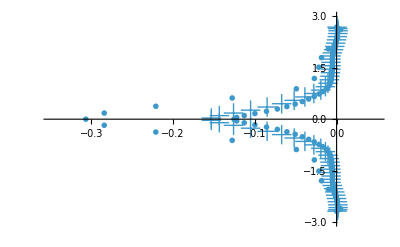

```mathematica
k=21;
LHSNum=(LHS[k]/.Kim07)/.barCoeffs;
RHSNum=(RHS[k]/.Kim07)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

n21=ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotMarkers->Style["◯",8]];

k=60;
LHSNum=(LHS[k]/.Kim07)/.barCoeffs;
RHSNum=(RHS[k]/.Kim07)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

n60=ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotMarkers->Style["+",20]];

k=81;
LHSNum=(LHS[k]/.Kim07)/.barCoeffs;
RHSNum=(RHS[k]/.Kim07)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

n81=ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotMarkers->Style["·",36]];

Show[n21,n60,n81,PlotRange->{{-0.35,0.05},{-3,3}}]
```

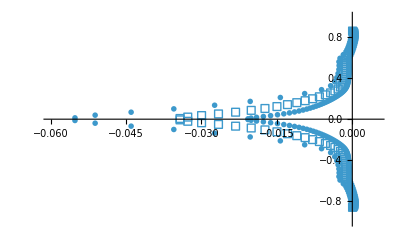

```mathematica
k=50;
LHSNum=(LHS[k]/.Kim07)/.barCoeffs;
RHSNum=(RHS[k]/.Kim07)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat]/π;

n50=ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotMarkers->Style["⊲",8]];

k=100;
LHSNum=(LHS[k]/.Kim07)/.barCoeffs;
RHSNum=(RHS[k]/.Kim07)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat]/π;

n100=ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotMarkers->Style["□",8]];

k=200;
LHSNum=(LHS[k]/.Kim07)/.barCoeffs;
RHSNum=(RHS[k]/.Kim07)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat]/π;

n200=ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotMarkers->Style["◯",6]];

Show[n50,n100,n200,PlotRange->{{-0.06,0.005},{-1,1}}]
```

#### Kim 24 Modified Boundary Coefficients

```mathematica
Kim24={α->0.5862704032801503,β->0.0954953355017055,a1->0.6431406736919156,a2->0.2586011023495066,a3->0.007140953479797375,γ01->43.65980335321481,γ02->92.40143116322876,γ10->0.08351537442980239,γ12->1.961483362670730,γ13->0.8789761422182460,γ20->0.008073091519768687,γ21->0.2162434143850924,γ23->1.052242062502679,γ24->0.2116022463346598,a00->-6.658527037451025,a01->-86.92242000231872,a02->47.58661913475775,a03->57.30693626084370,a04->-13.71254216556246,a05->2.659826729790792,a06->-0.2598929200600359,a10->-0.3199960780333493,a11->-1.438068456255548,a12->0.07735499170041915,a13->1.496612372811008,a14->0.2046919801608821,a15->-0.02229717539815850,a16->0.001702365014746567,a20->-0.03644974757120792,a21->-0.4997030280694729,a22->-0.7861024376433451,a23->0.7439822445654316,a24->0.5629384925762924,a25->0.01563884275691290,a26->-0.0003043666146108995};
```

```mathematica
{γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.Kim24),
γ13Bar->(γ13/(1-γ10*γ01)/.Kim24),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.Kim24),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.Kim24),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.Kim24)};

Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,6}]/.Kim24;
Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,6}]/.Kim24;

barCoeffs=Join[%,%%,%%%]
```

{a21Bar→-0.445082,a22Bar→-0.979255,a23Bar→0.739533,a24Bar→0.670234,a25Bar→0.0219576,a26Bar→-0.000578643,a11Bar→-2.19981,a12Bar→1.47259,a13Bar→1.24303,a14Bar→-0.510115,a15Bar→0.0923693,a16Bar→-0.00884546,γ12Bar→2.17494,γ13Bar→-0.332157,γ21Bar→0.147555,γ23Bar→1.19359,γ24Bar→0.261111}

```mathematica
Clear[LHS,RHS]
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i-2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}]

k=9; (*Size*)
MatrixForm@LHS[k]

MatrixForm@(LHS[k]/.Kim24)/.barCoeffs
```

(1 | γ12Bar | γ13Bar | 0 | 0 | 0 | 0 | 0 | 0
γ21Bar | 1 | γ23Bar | γ24Bar | 0 | 0 | 0 | 0 | 0
β | α | 1 | α | β | 0 | 0 | 0 | 0
0 | β | α | 1 | α | β | 0 | 0 | 0
0 | 0 | β | α | 1 | α | β | 0 | 0
0 | 0 | 0 | β | α | 1 | α | β | 0
0 | 0 | 0 | 0 | γ24 | γ23 | 1 | γ21 | γ20
0 | 0 | 0 | 0 | 0 | γ13 | γ12 | 1 | γ10
0 | 0 | 0 | 0 | 0 | 0 | γ02 | γ01 | 1)

(1 | 2.17494 | -0.332157 | 0 | 0 | 0 | 0 | 0 | 0
0.147555 | 1 | 1.19359 | 0.261111 | 0 | 0 | 0 | 0 | 0
0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0
0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0
0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0
0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0
0 | 0 | 0 | 0 | 0.211602 | 1.05224 | 1 | 0.216243 | 0.00807309
0 | 0 | 0 | 0 | 0 | 0.878976 | 1.96148 | 1 | 0.0835154
0 | 0 | 0 | 0 | 0 | 0 | 92.4014 | 43.6598 | 1)

```mathematica
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,
If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,

If[(i==k&&j==k),-a00,
If[(i==k&&j==k-1),-a01,
If[(i==k&&j==k-2),-a02,
If[(i==k&&j==k-3),-a03,
If[(i==k&&j==k-4),-a04,
If[(i==k&&j==k-5),-a05,
If[(i==k&&j==k-6),-a06,
If[(i==k-1&&j==k),-a10,
If[(i==k-1&&j==k-1),-a11,
If[(i==k-1&&j==k-2),-a12,
If[(i==k-1&&j==k-3),-a13,
If[(i==k-1&&j==k-4),-a14,
If[(i==k-1&&j==k-5),-a15,
If[(i==k-1&&j==k-6),-a16,
If[(i==k-2&&j==k),-a20,
If[(i==k-2&&j==k-1),-a21,
If[(i==k-2&&j==k-2),-a22,
If[(i==k-2&&j==k-3),-a23,
If[(i==k-2&&j==k-4),-a24,
If[(i==k-2&&j==k-5),-a25,
If[(i==k-2&&j==k-6),-a26,


If[i-3==j,-a3,
If[i-2==j,-a2,
If[i-1==j, -a1,
If[i==j, 0,
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}]

k=9; (*Size*)
MatrixForm@RHS[k]
```

(a11Bar | a12Bar | a13Bar | a14Bar | a15Bar | a16Bar | 0 | 0 | 0
a21Bar | a22Bar | a23Bar | a24Bar | a25Bar | a26Bar | 0 | 0 | 0
-a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0 | 0
-a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0
0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0
0 | 0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3
0 | 0 | -a26 | -a25 | -a24 | -a23 | -a22 | -a21 | -a20
0 | 0 | -a16 | -a15 | -a14 | -a13 | -a12 | -a11 | -a10
0 | 0 | -a06 | -a05 | -a04 | -a03 | -a02 | -a01 | -a00)

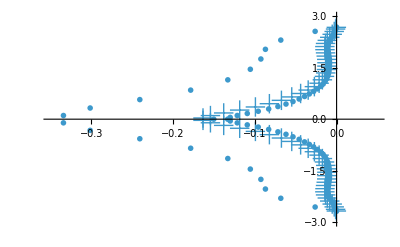

```mathematica
k=21;
LHSNum=(LHS[k]/.Kim24)/.barCoeffs;
RHSNum=(RHS[k]/.Kim24)/.barCoeffs;
RHSNum[[All,1]]=RHSNum[[All,1]]*(1-r)/.{r->0.7};

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

n21=ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{{-0.35,0.05},{-3,3}},PlotMarkers->Style["◯",8]];

k=60;
LHSNum=(LHS[k]/.Kim24)/.barCoeffs;
RHSNum=(RHS[k]/.Kim24)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

n60=ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{{-0.35,0.05},{-3,3}},PlotMarkers->Style["+",20]];

k=81;
LHSNum=(LHS[k]/.Kim24)/.barCoeffs;
RHSNum=(RHS[k]/.Kim24)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

n81=ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{{-0.35,0.05},{-3,3}},PlotMarkers->Style["·",36]];

Show[n21,n60,n81]
```

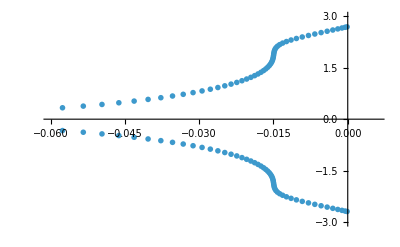

```mathematica
k=121;
LHSNum=(LHS[k]/.Kim24)/.barCoeffs;
RHSNum=(RHS[k]/.Kim24)/.barCoeffs;
RHSNum[[All,1]]=RHSNum[[All,1]]*(1-r)/.{r->0.7};

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{{-0.06,0.006},{-3,3}},PlotMarkers->Style["Δ",8]]
```

```mathematica
LHSBorders={
{1,α12,β12},
{α21,1,α22,β22},
{β31,α31,1,α32,β32}
};
RHSBorders={
{a1,b1,c1,d1,e1,f1,g1},
{a2,b2,c2,d2,e2,f2,g2},
{a3,b3,c3,d3,e3,f3,g3}
};

LHSMatrix[size_,borders_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{1,1}]->1,
Band[{2,1}]->α,
Band[{1,2}]->α,
Band[{3,1}]->β,
Band[{1,3}]->β
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[LHSBorders[[i]]],j++,
M[[i,j]]=LHSBorders[[i,j]]/.coeff;
M[[n-i+1,n-j+1]]=LHSBorders[[i,j]]/.coeff
]
];

M
]

RHSMatrix[size_,borders_,coeff_]:=Module[{M},
(*Fill Interior Matrix*)
M=SparseArray[{
Band[{2,1}]->-a,
Band[{3,1}]->-b,
Band[{4,1}]->-c,
Band[{1,2}]->a,
Band[{1,3}]->b,
Band[{1,4}]->c
}/.coeff,{size,size}];

(*Fill Borders*)
For[i=1,i<=borders,i++,
For[j=1,j<=Length[RHSBorders[[i]]],j++,
M[[i,j]]=RHSBorders[[i,j]]/.coeff;
M[[n-i+1,n-j+1]]=-RHSBorders[[i,j]]/.coeff
]
];

M
]
```

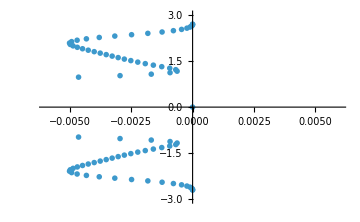

```mathematica
nList={21,60,81};
nList={121};
plotList={};
For[k=1,k<=Length@nList,k++,
n=nList[[k]];
LHS=LHSMatrix[n,3,coeff];
RHS=RHSMatrix[n,3,coeff];
(*Print[MatrixForm@Normal@RHS];*)
RHS[[All,1]]=RHS[[All,1]]*(1-0.7);
(*Print[MatrixForm@Normal@RHS];*)

(*For[j=1,j<=n,j++,LHS[[1,j]]=0];
For[j=1,j<=n,j++,LHS[[j,1]]=0];
For[j=1,j<=n,j++,RHS[[1,j]]=0];
For[j=1,j<=n,j++,RHS[[j,1]]=0];
LHS[[1,1]]=1;*)
(*For[j=1,j<=n,j++,RHS[[1,j]]=0];
For[j=1,j<=n,j++,RHS[[n,j]]=0];
For[j=1,j<=n,j++,RHS[[n-1,j]]=0];*)
LHS//MatrixForm;
RHS//MatrixForm;
(*Print[LHS//MatrixForm];
Print[RHS//MatrixForm];*)

mat=Inverse[LHS].RHS;
eigs=-Eigenvalues[mat];

AppendTo[plotList,ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotMarkers->Style["Δ",8],PlotRange->{{-0.006,0.006},{-3,3}},ImageSize->Medium]]
]
plotList
```

#### HAMR 08 Modified Boundary Coefficients

```mathematica
HAMR2={α->0.5747612151,β->0.0879324249,a1->1.3069171114/2,a2->0.9828406281/4,a3->0.0356295405/6,γ01->9.4133049605,γ02->10.7741034803,γ10->0.1023343303,γ12->1.8854940182,γ13->0.8582327249,γ20->0.0347468867,γ21->0.4064246796,γ23->0.7683583302,γ24->0.1623349133,a00->-3.6882535854000005,a01->-10.3169611301,a02->9.6807767746,a03->5.4529053045,a04->-1.5191959829,a05->0.4834876759,a06->-0.0927590566,a10->-0.3586079596,a11->-1.3424668425,a12->0.0834751059,a13->1.4235697122,a14->0.2245783548,a15->-0.0358453729,a16->0.0052970021,a20->-0.1274311870,a21->-0.6299599564,a22->-0.3024922988999999,a23->0.6498856630,a24->0.3919470424,a25->0.0189402158,a26->-0.0008894789};
γ03=0;
γ04=0;
```

```mathematica
{γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.HAMR2),
γ13Bar->((γ13-γ03*γ10)/(1-γ10*γ01)/.HAMR2),
γ21Bar->((γ21-γ01*γ20)/(1-γ20*γ02)/.HAMR2),
γ23Bar->((γ23-γ03*γ20)/(1-γ20*γ02)/.HAMR2),
γ24Bar->((γ24-γ04*γ20)/(1-γ20*γ02)/.HAMR2)};

Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,6}]/.HAMR2;
Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(1-γ20*γ02)*(ToExpression@StringJoin["a2",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ20),
{j,1,6}]/.HAMR2;

barCoeffs=Join[%,%%,%%%]
```

{a21Bar→-0.433924,a22Bar→-1.02116,a23Bar→0.735917,a24Bar→0.710855,a25Bar→0.00342137,a26Bar→0.00372999,a11Bar→-7.81256,a12Bar→-24.7222,a13Bar→23.5872,a14Bar→10.3566,a15Bar→-2.32514,a16Bar→0.403029,γ12Bar→21.3358,γ13Bar→23.3878,γ21Bar→0.126818,γ23Bar→1.22813,γ24Bar→0.259473}

```mathematica
Clear[LHS,RHS]
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i-2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}]

k=9; (*Size*)
MatrixForm@LHS[k]

MatrixForm@(LHS[k]/.HAMR2)/.barCoeffs
```

(1 | γ12Bar | γ13Bar | 0 | 0 | 0 | 0 | 0 | 0
γ21Bar | 1 | γ23Bar | γ24Bar | 0 | 0 | 0 | 0 | 0
β | α | 1 | α | β | 0 | 0 | 0 | 0
0 | β | α | 1 | α | β | 0 | 0 | 0
0 | 0 | β | α | 1 | α | β | 0 | 0
0 | 0 | 0 | β | α | 1 | α | β | 0
0 | 0 | 0 | 0 | γ24 | γ23 | 1 | γ21 | γ20
0 | 0 | 0 | 0 | 0 | γ13 | γ12 | 1 | γ10
0 | 0 | 0 | 0 | 0 | 0 | γ02 | γ01 | 1)

(1 | 21.3358 | 23.3878 | 0 | 0 | 0 | 0 | 0 | 0
0.126818 | 1 | 1.22813 | 0.259473 | 0 | 0 | 0 | 0 | 0
0.0879324 | 0.574761 | 1 | 0.574761 | 0.0879324 | 0 | 0 | 0 | 0
0 | 0.0879324 | 0.574761 | 1 | 0.574761 | 0.0879324 | 0 | 0 | 0
0 | 0 | 0.0879324 | 0.574761 | 1 | 0.574761 | 0.0879324 | 0 | 0
0 | 0 | 0 | 0.0879324 | 0.574761 | 1 | 0.574761 | 0.0879324 | 0
0 | 0 | 0 | 0 | 0.162335 | 0.768358 | 1 | 0.406425 | 0.0347469
0 | 0 | 0 | 0 | 0 | 0.858233 | 1.88549 | 1 | 0.102334
0 | 0 | 0 | 0 | 0 | 0 | 10.7741 | 9.4133 | 1)

```mathematica
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,
If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,

If[(i==k&&j==k),-a00,
If[(i==k&&j==k-1),-a01,
If[(i==k&&j==k-2),-a02,
If[(i==k&&j==k-3),-a03,
If[(i==k&&j==k-4),-a04,
If[(i==k&&j==k-5),-a05,
If[(i==k&&j==k-6),-a06,
If[(i==k-1&&j==k),-a10,
If[(i==k-1&&j==k-1),-a11,
If[(i==k-1&&j==k-2),-a12,
If[(i==k-1&&j==k-3),-a13,
If[(i==k-1&&j==k-4),-a14,
If[(i==k-1&&j==k-5),-a15,
If[(i==k-1&&j==k-6),-a16,
If[(i==k-2&&j==k),-a20,
If[(i==k-2&&j==k-1),-a21,
If[(i==k-2&&j==k-2),-a22,
If[(i==k-2&&j==k-3),-a23,
If[(i==k-2&&j==k-4),-a24,
If[(i==k-2&&j==k-5),-a25,
If[(i==k-2&&j==k-6),-a26,


If[i-3==j,-a3,
If[i-2==j,-a2,
If[i-1==j, -a1,
If[i==j, 0,
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}]

k=9; (*Size*)
MatrixForm@RHS[k]

MatrixForm@(RHS[k]/.HAMR2)/.barCoeffs
```

(a11Bar | a12Bar | a13Bar | a14Bar | a15Bar | a16Bar | 0 | 0 | 0
a21Bar | a22Bar | a23Bar | a24Bar | a25Bar | a26Bar | 0 | 0 | 0
-a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0 | 0
-a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0
0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0
0 | 0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3
0 | 0 | -a26 | -a25 | -a24 | -a23 | -a22 | -a21 | -a20
0 | 0 | -a16 | -a15 | -a14 | -a13 | -a12 | -a11 | -a10
0 | 0 | -a06 | -a05 | -a04 | -a03 | -a02 | -a01 | -a00)

(-7.81256 | -24.7222 | 23.5872 | 10.3566 | -2.32514 | 0.403029 | 0 | 0 | 0
-0.433924 | -1.02116 | 0.735917 | 0.710855 | 0.00342137 | 0.00372999 | 0 | 0 | 0
-0.24571 | -0.653459 | 0 | 0.653459 | 0.24571 | 0.00593826 | 0 | 0 | 0
-0.00593826 | -0.24571 | -0.653459 | 0 | 0.653459 | 0.24571 | 0.00593826 | 0 | 0
0 | -0.00593826 | -0.24571 | -0.653459 | 0 | 0.653459 | 0.24571 | 0.00593826 | 0
0 | 0 | -0.00593826 | -0.24571 | -0.653459 | 0 | 0.653459 | 0.24571 | 0.00593826
0 | 0 | 0.000889479 | -0.0189402 | -0.391947 | -0.649886 | 0.302492 | 0.62996 | 0.127431
0 | 0 | -0.005297 | 0.0358454 | -0.224578 | -1.42357 | -0.0834751 | 1.34247 | 0.358608
0 | 0 | 0.0927591 | -0.483488 | 1.5192 | -5.45291 | -9.68078 | 10.317 | 3.68825)

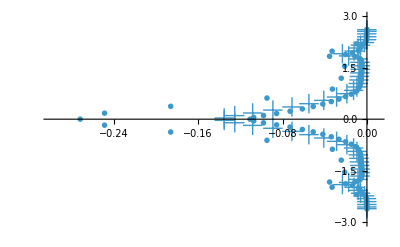

```mathematica
k=21;
LHSNum=(LHS[k]/.HAMR2)/.barCoeffs;
RHSNum=(RHS[k]/.HAMR2)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

n21=ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{{-0.3,0.01},{-3,3}},PlotMarkers->Style["◯",8]];

k=60;
LHSNum=(LHS[k]/.HAMR2)/.barCoeffs;
RHSNum=(RHS[k]/.HAMR2)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

n60=ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{{-0.3,0.01},{-3,3}},PlotMarkers->Style["+",20]];

k=81;
LHSNum=(LHS[k]/.HAMR2)/.barCoeffs;
RHSNum=(RHS[k]/.HAMR2)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

n81=ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{{-0.3,0.01},{-3,3}},PlotMarkers->Style["·",36]];

Show[n21,n60,n81]
```

## Eigenvalue Spectral Analysis

### Modified Boundary Coefficients for Eigenvalue Analysis

```mathematica
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,8}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,8}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2]
```

{γ12Bar→4.32153,γ13Bar→2.42939,γ21Bar→0.297763,γ23Bar→0.345769,γ24Bar→-0.0557037,a11Bar→-2.64907,a12Bar→-1.839,a13Bar→4.08998,a14Bar→0.498772,a15Bar→-0.0399126,a16Bar→0.00208964,a17Bar→2.71521 (-0.064325 a07+a17),a18Bar→2.71521 (-0.064325 a08+a18),a21Bar→-0.718611,a22Bar→-0.13518,a23Bar→0.921448,a24Bar→-0.0311284,a25Bar→-0.0134111,a26Bar→0.000670474,a27Bar→-17.1162 (-0.0544813 a17+0.064325 a27),a28Bar→-17.1162 (-0.0544813 a18+0.064325 a28)}

### Build Modified Matrices (needs cleaning badly)

```mathematica
Clear[LHS,RHS]
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],

If[(i-2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}]

k=9; (*Size*)
MatrixForm@LHS[k]

MatrixForm@(LHS[k]/.coeffNate)/.barCoeffs
```

(1 | γ12Bar | γ13Bar | 0 | 0 | 0 | 0 | 0 | 0
γ21Bar | 1 | γ23Bar | γ24Bar | 0 | 0 | 0 | 0 | 0
β | α | 1 | α | β | 0 | 0 | 0 | 0
0 | β | α | 1 | α | β | 0 | 0 | 0
0 | 0 | β | α | 1 | α | β | 0 | 0
0 | 0 | 0 | β | α | 1 | α | β | 0
0 | 0 | 0 | 0 | γ24 | γ23 | 1 | γ21 | γ20
0 | 0 | 0 | 0 | 0 | γ13 | γ12 | 1 | γ10
0 | 0 | 0 | 0 | 0 | 0 | γ02 | γ01 | 1)

(1 | 4.32153 | 2.42939 | 0 | 0 | 0 | 0 | 0 | 0
0.297763 | 1 | 0.345769 | -0.0557037 | 0 | 0 | 0 | 0 | 0
0.0890084 | 0.577046 | 1 | 0.577046 | 0.0890084 | 0 | 0 | 0 | 0
0 | 0.0890084 | 0.577046 | 1 | 0.577046 | 0.0890084 | 0 | 0 | 0
0 | 0 | 0.0890084 | 0.577046 | 1 | 0.577046 | 0.0890084 | 0 | 0
0 | 0 | 0 | 0.0890084 | 0.577046 | 1 | 0.577046 | 0.0890084 | 0
0 | 0 | 0 | 0 | 0.0505936 | 0.443764 | 1 | 0.576522 | 0.0544813
0 | 0 | 0 | 0 | 0 | 0.894736 | 2.25305 | 1 | 0.064325
0 | 0 | 0 | 0 | 0 | 0 | 10.2829 | 9.8205 | 1)

```mathematica
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,

If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,

If[(i==k&&j==k),-a00,
If[(i==k&&j==k-1),-a01,
If[(i==k&&j==k-2),-a02,
If[(i==k&&j==k-3),-a03,
If[(i==k&&j==k-4),-a04,
If[(i==k&&j==k-5),-a05,
If[(i==k&&j==k-6),-a06,
If[(i==k-1&&j==k),-a10,
If[(i==k-1&&j==k-1),-a11,
If[(i==k-1&&j==k-2),-a12,
If[(i==k-1&&j==k-3),-a13,
If[(i==k-1&&j==k-4),-a14,
If[(i==k-1&&j==k-5),-a15,
If[(i==k-1&&j==k-6),-a16,
If[(i==k-2&&j==k),-a20,
If[(i==k-2&&j==k-1),-a21,
If[(i==k-2&&j==k-2),-a22,
If[(i==k-2&&j==k-3),-a23,
If[(i==k-2&&j==k-4),-a24,
If[(i==k-2&&j==k-5),-a25,
If[(i==k-2&&j==k-6),-a26,


If[i-3==j,-a3,
If[i-2==j,-a2,
If[i-1==j, -a1,
If[i==j, 0,
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}]

k=11; (*Size*)
MatrixForm@RHS[k]

MatrixForm@(RHS[k]/.coeffNate)/.barCoeffs
```

(a11Bar | a12Bar | a13Bar | a14Bar | a15Bar | a16Bar | 0 | 0 | 0 | 0 | 0
a21Bar | a22Bar | a23Bar | a24Bar | a25Bar | a26Bar | 0 | 0 | 0 | 0 | 0
-a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0 | 0 | 0 | 0
-a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0 | 0 | 0
0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0 | 0
0 | 0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0
0 | 0 | 0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0
0 | 0 | 0 | 0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3
0 | 0 | 0 | 0 | -a26 | -a25 | -a24 | -a23 | -a22 | -a21 | -a20
0 | 0 | 0 | 0 | -a16 | -a15 | -a14 | -a13 | -a12 | -a11 | -a10
0 | 0 | 0 | 0 | -a06 | -a05 | -a04 | -a03 | -a02 | -a01 | -a00)

(-2.64907 | -1.839 | 4.08998 | 0.498772 | -0.0399126 | 0.00208964 | 0 | 0 | 0 | 0 | 0
-0.718611 | -0.13518 | 0.921448 | -0.0311284 | -0.0134111 | 0.000670474 | 0 | 0 | 0 | 0 | 0
-0.248159 | -0.651708 | 0 | 0.651708 | 0.248159 | 0.00600963 | 0 | 0 | 0 | 0 | 0
-0.00600963 | -0.248159 | -0.651708 | 0 | 0.651708 | 0.248159 | 0.00600963 | 0 | 0 | 0 | 0
0 | -0.00600963 | -0.248159 | -0.651708 | 0 | 0.651708 | 0.248159 | 0.00600963 | 0 | 0 | 0
0 | 0 | -0.00600963 | -0.248159 | -0.651708 | 0 | 0.651708 | 0.248159 | 0.00600963 | 0 | 0
0 | 0 | 0 | -0.00600963 | -0.248159 | -0.651708 | 0 | 0.651708 | 0.248159 | 0.00600963 | 0
0 | 0 | 0 | 0 | -0.00600963 | -0.248159 | -0.651708 | 0 | 0.651708 | 0.248159 | 0.00600963
0 | 0 | 0 | 0 | 0.000425431 | -0.0049542 | -0.149045 | -0.651002 | -0.157076 | 0.760192 | 0.201459
0 | 0 | 0 | 0 | -0.000216697 | 0.00853233 | -0.142593 | -1.75676 | -0.0404934 | 1.66816 | 0.263369
0 | 0 | 0 | 0 | 0.00859553 | -0.0958773 | 0.638984 | -3.89328 | -11.1588 | 10.7659 | 3.73445)

### Plot Eigenvalue Spectra

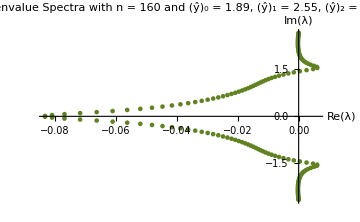

```mathematica
k=160;
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0/5,yHat1/5,yHat2/5]]
```

## Dendro Output

### Hide

```mathematica
derivativeOrder=1;
interiorOrder=n;
totalBoundRows=numBoundaryRows;
freeInteriorParameters={};
freeBoundaryParameters={};
RHSInteriorList=RHSPars;
interiorParametersValues=interiorCoeffsP4/.{α->alpha,β->beta};
boundaryParametersValues=boundaryLuke/.{α12->gamma01,β12->gamma02,α21->gamma10,α22->gamma12,β22->gamma13,β31->gamma20,α31->gamma21,α32->gamma23,β32->gamma24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};
LHSBoundaryList={gamma01,gamma02,gamma10,gamma12,gamma13,gamma20,gamma21,gamma23,gamma24};
RHSBoundaryList={a00,a01,a02,a03,a04,a05,a06,a10,a11,a12,a13,a14,a15,a16,a20,a21,a22,a23,a24,a25,a26};
(*Don't need to mess with these until we incorporate this procedure with James's filtering*)
filterIntCoeff;
filterBoundCoeff;
filterIntParam;
filterBoundParam;
filtering=False;
(*boundary={α12->γ01,β12->γ02,α21->γ10,α22->γ12,β22->γ13,β31->γ20,α31->γ21,α32->γ23,β32->γ24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};*)
```

```mathematica
(*****************Print coefficients in Dendro-GR Format*****************)
If[derivativeOrder==1,
LHSName="P1";
RHSName="Q1";
nth="1st";
coeffs="D_coeffs";
order="First",
If[derivativeOrder==2,
LHSName="P2";
RHSName="Q2";
nth="2nd";
coeffs="D_coeffs";
order="Second"]];
If[LHSBandCount==3,
LHSStructure="T",
If[LHSBandCount==5,
LHSStructure="P"]];

(*Convert Mathematica expression syntax to C/C++ expression syntax*)
convertToCCode[expr_]:=Module[{str},str=ToString[expr,InputForm];
(*Add ".0" to standalone integers but not to variables with numbers*)
(*Formatting adjustments to match C/C++ syntax*)str=StringReplace[str,{" "->"","*"->" * ","/"->" / ","+"->" + ","-"->" - ","^"->" ^ "}];
str]
(*Function to generate the line of C/C++ code to define the fixed variables*)
generateCAssignment[rule_]:=Module[{variable,expression,cCode,cAssignment},
variable=ToString[rule[[1]]];
expression=rule[[2]];
cCode=convertToCCode[expression];
cAssignment="double "<>variable<>" = "<>cCode<>";";
cAssignment
]






(*Initial Block*)
initialBlock=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order"}];
initialBlock2=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order","Filtered"}];

(*Free Parameters Block*)
freeParameters=Join[freeInteriorParameters,freeBoundaryParameters];
numFreePars=Length[freeParameters];
alphaPrint=StringReplace[generateCAssignment[Select[interiorParametersValues,#[[1]]===alpha&][[1]]],"alpha"->"alpha0"];
freeParPrints={};
If[numFreePars>0,
For[i=1,i<=numFreePars,i++,
AppendTo[freeParPrints,StringJoin[{"\n\t\tdouble ",ToString[freeParameters[[i]]]," = ",coeffs,"[",ToString[i],"];"}]]]]
freeParametersBlock=StringJoin[{"\t",alphaPrint,"\n\t\tdouble alpha = alpha0 + ",coeffs,"[0];",freeParPrints}];

(*Filter*)
freeParPrints2={};
freeParametersBlock2=StringJoin[{"\t","\n\t\tdouble alpha = ","F_coeffs","[0];",If[LHSBandCount==5,StringJoin["\n\t\tdouble beta = ","F_coeffs","[1];"],""]}];

(*Fixed Parameters Block*)
(*Create a list of the solved fixed parameters in C/C++ syntax*)
interiorParametersValues3=DeleteCases[interiorParametersValues,Rule[alpha,_]];
interiorParameterPrints=Table[
generateCAssignment[interiorParametersValues3[[i]]],
{i,1,Length[interiorParametersValues]-1}
];
boundaryParameterPrints=Table[
generateCAssignment[boundaryParametersValues[[i]]],
{i,1,Length[boundaryParametersValues]}
];
(*For filtered coefficients*)
interiorParameterPrints2=Table[
generateCAssignment[filterIntCoeff[[i]]],
{i,1,Length[filterIntCoeff]}
];
boundaryParameterPrints2=Table[
generateCAssignment[filterBoundCoeff[[i]]],
{i,1,Length[filterBoundCoeff]}
];
(*Print the coefficients in a single block of text rather than individual lines*)
fixedParametersBlockD=StringJoin["\t\t",Riffle[Join[interiorParameterPrints,boundaryParameterPrints],"\n\t\t"]];
fixedParametersBlockD2=StringJoin["\t\t",Riffle[Join[interiorParameterPrints2,boundaryParameterPrints2],"\n\t\t"]];

(*Structure Block*)
(*LHS Boundary*)
PDiagBoundary="";
LHSRowList=ToExpression[GatherBy[LHSBoundaryList,StringDrop[ToString[#],5]~StringTake~1&]];
For[i=1,i<=Length[LHSRowList],i++,
If[i==1,PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t","{1.0, ",StringDrop[ToString[LHSRowList[[i]]],1],","]];
If[i==2,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1}]],1],","]]];
If[i==3,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{","0.0, ",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t",StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
If[i>=4,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],StringDrop[StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
];
(*LHS Filter Boundary*)
RDiagBoundary="";
For[i=1,i<=Length@filterBoundParam,i++,
If[i==1,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha, beta},"]];
];
If[i==2,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha 1.0, alpha, beta},"]];
];
If[i>=3,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],"alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],"beta, alpha, 1.0, alpha, beta},"]];
];
];

(*LHS Interior*)
If[LHSBandCount==3,
PDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
PDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];
(*LHS Filter Interior*)
If[LHSBandCount==3,
RDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
RDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];

(*RHS Boundary*)
QDiagBoundary="";
RHSRowList=ToExpression[GatherBy[RHSBoundaryList,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList],i++,QDiagBoundary=StringJoin[QDiagBoundary,"\n\t\t\t",ToString[RHSRowList[[i]]],","]]
(*RHS Filter Boundary*)
SDiagBoundary="";
RHSRowList2=ToExpression[GatherBy[filterBoundParam,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList2],i++,SDiagBoundary=StringJoin[SDiagBoundary,"\n\t\t\t",ToString[RHSRowList2[[i]]]]]

(*RHS Interior*)
QDiagInterior={};
len=(2*Length[RHSInteriorList]+1);
If[derivativeOrder==1,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[-RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"0.0"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]
],
If[derivativeOrder==2,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[-RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"t1"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]]]]

(*RHS Filter Interior*)
SDiagInterior={};
newFilterIntParam=Drop[filterIntParam,1];
len=(2*Length[newFilterIntParam]+1);
For[i=1,i<=len,i++,
If[i<=Length[newFilterIntParam],PrependTo[SDiagInterior,ToString[newFilterIntParam[[i]]]<>"/"<>ToString[2]<>".0"]];
If[i==(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,"a0"]];
If[i>(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,ToString[newFilterIntParam[[i-Length[newFilterIntParam]-1]]]<>"/"<>ToString[2]<>".0"]]
]


PDiagBoundaryStr=StringDrop[StringDrop[PDiagBoundary,1],-1];
PDiagInteriorStr=StringDrop[StringDrop[PDiagInterior,1],-1];
RDiagBoundaryStr=StringDrop[StringDrop[RDiagBoundary,1],-1];
RDiagInteriorStr=StringDrop[StringDrop[RDiagInterior,1],-1];
QDiagBoundaryStr=StringDrop[StringDrop[QDiagBoundary,1],-1];
QDiagInteriorStr=StringDrop[StringDrop[ToString[QDiagInterior],1],-1];
SDiagBoundaryStr=StringDrop[SDiagBoundary,1];
SDiagInteriorStr=StringDrop[StringDrop[ToString[SDiagInterior],1],-1];

(*Subscript[t, 1] is the middle RHS Interior Coefficient for Second Derivatives*)
t1List={};
For[i=1,i<=Length[RHSInteriorList],i++,
AppendTo[t1List,ToString[RHSInteriorList[[i]]]<>"/"<>ToString[i^2]<>".0"]
];
If[derivativeOrder==1,
t1="",
If[derivativeOrder==2,
t1=StringJoin["-2.0 * ("<>StringDrop[StringDrop[ToString[t1List],1],-1]<>")"]]];


If[filtering,
filterFinalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock2,"(\n","\tconst std::vector<double>& ","F_coeffs",") {\n","\t",freeParametersBlock2,"\n\n",fixedParametersBlockD2,"\n\n","\t\t// boundary elements for R matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","R","DiagBoundary{\n",RDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for R matrix for ",nth," derivative\n","\t\tstd::vector<double> ","R","DiagInterior{\n","\t\t\t",RDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for S matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","S","DiagBoundary\n",SDiagBoundaryStr,"\n","\t\t;\n\n","\t\t// diagonal elements for S matrix for ",nth," derivative\n","\t\tstd::vector<double> ","S","DiagInterior{\n","\t\t\t",SDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t","R","DiagInterior, ","S","DiagInterior, ","S","DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}"}];
]

finalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock,"(\n","\tconst std::vector<double>& ",coeffs,") {\n","\t",freeParametersBlock,"\n\n",fixedParametersBlockD,"\n\n","\t\t// boundary elements for P matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",LHSName,"DiagBoundary{\n",PDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for P matrix for ",nth," derivative\n","\t\tstd::vector<double> ",LHSName,"DiagInterior{\n","\t\t\t",PDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",RHSName,"DiagBoundary{\n",QDiagBoundaryStr,"\n","\t\t};\n\n",If[derivativeOrder==1,t1,If[derivativeOrder==2,"\t\tdouble t1 = "<>t1<>";\n"]],"\t\t// diagonal elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<double> ",RHSName,"DiagInterior{\n","\t\t\t",QDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t",LHSName,"DiagInterior, ",LHSName,"DiagBoundary, ",RHSName,"DiagInterior, ",RHSName,"DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}",If[filtering,"\n\n"<>filterFinalBlock,""]}];
```

GatherBy::list: List expected at position 1 in GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&].

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Drop::drop: Cannot drop positions 1 through 1 in filterIntParam.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

StringDrop::drop: Cannot drop positions 1 through 1 in "".

### Show

```mathematica
outExt="h";
(*Print header*)
Print[Style["Dendro-Ready Coefficients (Copied to clipboard):",Bold,FontSize->24]];
Print[finalBlock];
(*Copy the block of text to the user's clipboard*)
CopyToClipboard[finalBlock];

(*Save to output file*)
fileName=StringJoin[{"BYU_P4","_yHat0_",ToString[yHat0],"_yHat1_",ToString[yHat1],"_yHat2_",ToString[yHat2],".",outExt}];
Export[fileName,finalBlock,"Text"];
Print[StringJoin[{"Saved to file: ",fileName}]]
```

Dendro-Ready Coefficients (Copied to clipboard):

MatrixDiagonalEntries* BYUDerivsP4R3DiagonalsFirstOrder(
	const std::vector<double>& D_coeffs) {
		double alpha0 = 0.5770460201292381;
		double alpha = alpha0 + D_coeffs[0];

		double beta = 0.08900836845092142;
		double a1 = 0.6517078440898839;
		double a2 = 0.24815882627035918;
		double a3 = 0.006009630649852392;
		double gamma01 = 9.82050086297005;
		double gamma02 = 10.282867809058313;
		double gamma10 = 0.06432504195032081;
		double gamma12 = 2.253048588922067;
		double gamma13 = 0.8947355749649457;
		double gamma20 = 0.054481322450841994;
		double gamma21 = 0.5765221339649635;
		double gamma23 = 0.44376439085350533;
		double gamma24 = 0.0505935788115157;
		double a00 =  - 3.73445251380582;
		double a01 =  - 10.765902315893966;
		double a02 = 11.158777481815811;
		double a03 = 3.8932795799881186;
		double a04 =  - 0.6389839738157034;
		double a05 = 0.09587727397420936;
		double a06 =  - 0.008595531676508965;
		double a10 =  - 0.2633689121814849;
		double a11 =  - 1.6681586712239223;
		double a12 = 0.040493403700274426;
		double a13 = 1.7567567175694963;
		double a14 = 0.14259309069789727;
		double a15 =  - 0.008532325517430831;
		double a16 = 0.00021669695996460306;
		double a20 =  - 0.2014589762066764;
		double a21 =  - 0.7601917184724901;
		double a22 = 0.1570757314505742;
		double a23 = 0.6510015139350865;
		double a24 = 0.14904467564349694;
		double a25 = 0.00495420462721734;
		double a26 =  - 0.00042543097718981916;

		// boundary elements for P matrix for 1st derivative
		std::vector<std::vector<double>> P1DiagBoundary{
			{1.0, gamma01, gamma02},
			{gamma10, 1.0, gamma12, gamma13},
			{gamma20, gamma21, 1.0, gamma23, gamma24}
		};

		// diagonal elements for P matrix for 1st derivative
		std::vector<double> P1DiagInterior{
			beta, alpha, 1.0, alpha, beta
		};

		// boundary elements for Q matrix for 1st derivative
		std::vector<std::vector<double>> Q1DiagBoundary{
			{a00, a01, a02, a03, a04, a05, a06},
			{a10, a11, a12, a13, a14, a15, a16},
			{a20, a21, a22, a23, a24, a25, a26}
		};

		// diagonal elements for Q matrix for 1st derivative
		std::vector<double> Q1DiagInterior{
			-a3, -a2, -a1, 0.0, a1, a2, a3
		};

		// store the entries for matrix creation
		MatrixDiagonalEntries* diagEntries = new
			MatrixDiagonalEntries{
				P1DiagInterior, P1DiagBoundary, Q1DiagInterior, Q1DiagBoundary
			};
		return diagEntries;
	}

Saved to file: BYU_P4_yHat0_1.89_yHat1_2.55_yHat2_0.63.h

# P4 (B4) Scheme

## Initialization

The matrix system of equations we are solving for this scheme is:
	P=(1
γ_10
γ_20
0
0
0
0
0
0 γ_01
1
γ_21
γ_31
0
0
0
0
0 γ_02
γ_12
1
γ_32
β
0
0
0
0 0
γ_13
γ_23
1
α
γ_35
0
0
0 0
0
γ_24
γ_34
1
γ_34
γ_24
0
0 0
0
0
γ_35
α
1
γ_23
γ_13
0 0
0
0
0
β
γ_32
1
γ_12
γ_02 0
0
0
0
0
γ_31
γ_21
1
γ_01 0
0
0
0
0
0
γ_20
γ_10
1)
	Q=(a_00
a_10
a_20
a_30
-a_4
-a_38
-a_28
-a_18
-a_08 a_01
a_11
a_21
a_31
-a_3
-a_37
-a_27
-a_17
-a_07 a_02
a_12
a_22
a_32
-a_2
-a_36
-a_26
-a_16
-a_06 a_03
a_13
a_23
a_33
-a_1
-a_35
-a_25
-a_15
-a_05 a_04
a_14
a_24
a_34
0
-a_34
-a_24
-a_14
-a_04 a_05
a_15
a_25
a_35
a_1
-a_33
-a_23
-a_13
-a_03 a_06
a_16
a_26
a_36
a_2
-a_32
-a_22
-a_12
-a_02 a_07
a_17
a_27
a_37
a_3
-a_31
-a_21
-a_11
-a_01 a_08
a_18
a_28
a_38
a_4
-a_30
-a_20
-a_10
-a_00 )

```mathematica
(*From KimInteriorOptimization.nb, one day to be merged with this one. Or I could DumpSave[] in that notebook and then Get[] here.*)
(*Note that these are found with the P6 Scheme NEW header in that notebook*)
interiorCoeffsB4={α->0.5942348163052151,β->0.10275748724572716,a1->0.6340472486307104,a2->0.26726592813302824,a3->0.01004721696654148,a4->-0.000432113061362272};
(*DumpSave["B4_interiorCoeffs.mx","Global`interiorCoeffsB4"];*)

(*If you have the .mx files in the same directory as this notebook, these will let you skip the long computation of defining bdCoeffs under the "Solve for Boundary Coefficients" section*)
Get["B4_interiorCoeffs.mx"];
Get["B4_bdCoeffs3.mx"];
Get["B4_bdCoeffs2.mx"];
Get["B4_bdCoeffs1.mx"];
Get["B4_bdCoeffs0.mx"];
```

## General Extrapolation Polynomial

For the P4 (B4) scheme, we have:
	LHSBandCount = 5
	n = 4
	freeInteriorPars = 4
	yDeriv = 14

```mathematica
(*User chooses these parameters, the rest is calculated from these*)
LHSBandCount=5; (*3 for tridiagonal, 5 for pentadiagonal*)
n=4; (*order of the scheme*)
freeInteriorPars=4; (*number of free parameters used for Kim's optimization on the interior*)
yDeriv=14; (*(d^n P)/dx^n(ŷ)=0 from Kim 2024 Eq. 10, this is n in that equation*) (*provide constraints on what the user can choose for this. Upper bound should be polynomialorder to prevent the matrix from being singular, and lower bound should be order·2 I think.*)

LHSPars=Switch[LHSBandCount,3,{α},5,{α,β}];
RHSPars=Table[ToExpression[StringJoin["a",ToString[i]]],{i,1,Ceiling[n/2]-Length@LHSPars+freeInteriorPars}];
numBoundaryRows=Length@RHSPars;
fOrder=(2*Length@RHSPars)+1;
fpOrder=LHSBandCount+(numBoundaryRows-(LHSBandCount-1)/2);
PolynomialOrder=fOrder+fpOrder;


rowf1=Join[{1},Table[0,{i,1,PolynomialOrder}]];
rowf=Table[Table[i^j,{j,0,PolynomialOrder}],{i,1,fOrder-1}];
rowfp1=Join[{0,1},Table[0,{i,2,PolynomialOrder}]];
rowfp=Table[Table[j i^(j-1),{j,0,PolynomialOrder}],{i,1,fpOrder-1}];
rowyHat=Join[Table[0,{i,1,yDeriv}],Table[(i!)/((i-yDeriv)!) yHat^(i-yDeriv),{i,yDeriv,PolynomialOrder}]];

matf=PrependTo[rowf,rowf1];
matfp=PrependTo[rowfp,rowfp1];
matfCombined=Join[matf,matfp];
LMat=AppendTo[matfCombined,rowyHat];

pVec=Table[ToExpression[StringJoin["p",ToString[i]]],{i,0,PolynomialOrder}];
fVec=Join[Table[ToExpression[StringJoin["f",ToString[i]]],{i,0,fOrder-1}],Table[ToExpression[StringJoin["fp",ToString[i]]],{i,0,fpOrder-1}],{0}];

pCoeffs=Solve[LMat.pVec==fVec,pVec][[1]];

yHatSingularities=(Transpose@Solve[Det[LMat]==0,yHat])[[1]]//N;
P[x_]=Total[Table[pVec[[i+1]]*x^i,{i,0,PolynomialOrder}]]/.pCoeffs;

Print["System:\n",MatrixForm[LMat]," ",MatrixForm[pVec]," = ",MatrixForm[fVec]]
Print["Singularities:\n",MatrixForm[yHatSingularities]]
(*Print["Coefficients:\n",MatrixForm[pCoeffs]]*)
```

System:
(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 4 | 8 | 16 | 32 | 64 | 128 | 256 | 512 | 1024 | 2048 | 4096 | 8192 | 16384 | 32768 | 65536
1 | 3 | 9 | 27 | 81 | 243 | 729 | 2187 | 6561 | 19683 | 59049 | 177147 | 531441 | 1594323 | 4782969 | 14348907 | 43046721
1 | 4 | 16 | 64 | 256 | 1024 | 4096 | 16384 | 65536 | 262144 | 1048576 | 4194304 | 16777216 | 67108864 | 268435456 | 1073741824 | 4294967296
1 | 5 | 25 | 125 | 625 | 3125 | 15625 | 78125 | 390625 | 1953125 | 9765625 | 48828125 | 244140625 | 1220703125 | 6103515625 | 30517578125 | 152587890625
1 | 6 | 36 | 216 | 1296 | 7776 | 46656 | 279936 | 1679616 | 10077696 | 60466176 | 362797056 | 2176782336 | 13060694016 | 78364164096 | 470184984576 | 2821109907456
1 | 7 | 49 | 343 | 2401 | 16807 | 117649 | 823543 | 5764801 | 40353607 | 282475249 | 1977326743 | 13841287201 | 96889010407 | 678223072849 | 4747561509943 | 33232930569601
1 | 8 | 64 | 512 | 4096 | 32768 | 262144 | 2097152 | 16777216 | 134217728 | 1073741824 | 8589934592 | 68719476736 | 549755813888 | 4398046511104 | 35184372088832 | 281474976710656
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
0 | 1 | 4 | 12 | 32 | 80 | 192 | 448 | 1024 | 2304 | 5120 | 11264 | 24576 | 53248 | 114688 | 245760 | 524288
0 | 1 | 6 | 27 | 108 | 405 | 1458 | 5103 | 17496 | 59049 | 196830 | 649539 | 2125764 | 6908733 | 22320522 | 71744535 | 229582512
0 | 1 | 8 | 48 | 256 | 1280 | 6144 | 28672 | 131072 | 589824 | 2621440 | 11534336 | 50331648 | 218103808 | 939524096 | 4026531840 | 17179869184
0 | 1 | 10 | 75 | 500 | 3125 | 18750 | 109375 | 625000 | 3515625 | 19531250 | 107421875 | 585937500 | 3173828125 | 17089843750 | 91552734375 | 488281250000
0 | 1 | 12 | 108 | 864 | 6480 | 46656 | 326592 | 2239488 | 15116544 | 100776960 | 665127936 | 4353564672 | 28298170368 | 182849716224 | 1175462461440 | 7522959753216
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 87178291200 | 1307674368000 yHat | 10461394944000 yHat^2) (p0
p1
p2
p3
p4
p5
p6
p7
p8
p9
p10
p11
p12
p13
p14
p15
p16) = (f0
f1
f2
f3
f4
f5
f6
f7
f8
fp0
fp1
fp2
fp3
fp4
fp5
fp6
0)

Singularities:
(yHat→2.94357
yHat→4.18143)

## Solve for Boundary Coefficients

Goal:
	Solve a system of equations for bdCoeffsList3 in terms of the optimization free parameter ŷ
Variables:
	fVars3: List of f_i and f_i' variables that will appear in the shifted stencil for Node 3
	bdCoeffsList3: List of boundary coefficients that will appear in the shifted stencil for Node 3
	schemeShifted: The shifted scheme for Node 3
	schemeCentered: The centered scheme for Node 3 in terms of the extrapolation polynomial P(x)
		NOTE: To make the Collect[] process easier, we write these schemes as LHS-RHS=0 rather than the usual LHS=RHS.
	schemeNode4: The scheme for Node 4, which only depends on interiorCoeffsP6
	SOLfp6: The solution to Node 4’s scheme equation for f_6' in terms of fVars3
	eq: Scheme equation where the coefficient terms from schemeCentered and schemeShifted are set equal to each other
	coeffEqs3: System of equations with each of the coefficient terms equal to each other
	bdCoeffs3: Solution to the system of equations for bdCoeffsList3 in terms of ŷ
Process:
	1. Initialize the necessary equations.
	2. We want schemeShifted and schemeCentered to both be in terms of fVars3 with some coefficients. Due to the presence of P(x) terms in schemeCentered, it is in terms of fVars3 as well as f_6'. We eliminate the dependence on f_6' by using Node 4’s scheme to solve for f_6' in terms of fVars3.
	3. Now that schemeShifted and schemeCentered are both in terms of fVars3, we construct a system of equations by equating the coefficient in front of each term of fVars3 in schemeCentered with the corresponding coefficient in front of the same term in schemeShifted.
	4. We solve this system of equations for bdCoeffsList3 in terms of interiorCoeffsP6 (which are substituted in) and the optimization free parameter ŷ.
		NOTE: In the standard scheme approach, we set γ_33=1 to ensure the main diagonal of the LHS matrix is all 1’s. When solving this system of equations, we must include γ_33 so that bdCoeffsList3 and fVars3 have the same length since this allows us to find a unique solution to the system of equations. We apply the normal condition later on.
	5. OPTIONAL: We may save the variable bdCoeffs3 to a binary file in the current directory. This is helpful to avoid having to run this process multiple times, as it can become computationally expensive.
Differences:
	For Nodes 2, 1, and 0, the entire process translates directly with a few changes. fVars, bdCoeffsList, schemeShifted, and schemeCentered all change, as we are considering the scheme for a different row, but the equations have the same structure. The main notable difference is in Step 2; In addition to substituting in the solution from Node 4 for f_6' in terms of the other fVars, we must also do the same for f_5' (Nodes 2, 1, and 0), f_4' (Nodes 1 and 0), and f_3' (Node 0) using Nodes 3, 2, and 1, respectively.

### Node 3

```mathematica
(*----------STEP 1----------*)
fVars3={fp1,fp2,fp3,fp4,fp5,f0,f1,f2,f3,f4,f5,f6,f7,f8};
bdCoeffsList3={γ31,γ32,γ33,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38};
schemeShifted=γ31 fp1+γ32 fp2+γ33 fp3+γ34 fp4+γ35 fp5-(a30 f0+a31 f1+a32 f2+a33 f3+a34 f4+a35 f5+a36 f6+a37 f7+a38 f8); (*==0*)
schemeCentered=β fp1+α fp2+fp3+α fp4+β fp5-(-a4 P[-1]-a3 f0-a2 f1-a1 f2+a1 f4+a2 f5+a3 f6+a4 f7); (*==0*)

(*----------STEP 2----------*)
schemeNode4=β fp2+α fp3+fp4+α fp5+β fp6==-a4 f0-a3 f1-a2 f2-a1 f3+a1 f5+a2 f6+a3 f7+a4 f8;
SOLfp6=Solve[schemeNode4,fp6][[1,1]]/.interiorCoeffsB4;
schemeCentered=schemeCentered/.SOLfp6;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars3];

(*----------STEP 4----------*)
coeffEqs3=Table[Coefficient[eq,fVars3[[i]]]==0,{i,1,Length@fVars3}];
bdCoeffs3=(Solve[coeffEqs3,bdCoeffsList3][[1]])/.interiorCoeffsB4;

(*----------STEP 5----------*)
DumpSave["B4_bdCoeffs3.mx","Global`bdCoeffs3"];
```

### Node 2

```mathematica
(*----------STEP 1----------*)
fVars2={fp0,fp1,fp2,fp3,fp4,f0,f1,f2,f3,f4,f5,f6,f7,f8};
bdCoeffsList2={γ20,γ21,γ22,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28};
schemeShifted=γ20 fp0+γ21 fp1+γ22 fp2+γ23 fp3+γ24 fp4-(a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6+a27 f7+a28 f8); (*==0*)
schemeCentered=β fp0+α fp1+fp2+α fp3+β fp4-(-a4 P[-2]-a3 P[-1]-a2 f0-a1 f1+a1 f3+a2 f4+a3 f5+a4 f6); (*==0*)

(*----------STEP 2----------*)
schemeNode4=β fp2+α fp3+fp4+α fp5+β fp6==-a4 f0-a3 f1-a2 f2-a1 f3+a1 f5+a2 f6+a3 f7+a4 f8;
schemeNode3=γ31 fp1+γ32 fp2+γ33 fp3+γ34 fp4+γ35 fp5==a30 f0+a31 f1+a32 f2+a33 f3+a34 f4+a35 f5+a36 f6+a37 f7+a38 f8;
SOLfp6=Solve[schemeNode4,fp6][[1,1]]/.interiorCoeffsB4;
SOLfp5=Solve[schemeNode3,fp5][[1,1]]/.bdCoeffs3;
schemeCentered=schemeCentered/.SOLfp6/.SOLfp5;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars2];

(*----------STEP 4----------*)
coeffEqs2=Table[Coefficient[eq,fVars2[[i]]]==0,{i,1,Length@fVars2}];
bdCoeffs2=(Solve[coeffEqs2,bdCoeffsList2][[1]])/.interiorCoeffsB4;

(*----------STEP 5----------*)
DumpSave["B4_bdCoeffs2.mx","Global`bdCoeffs2"];
```

### Node 1

```mathematica
(*----------STEP 1----------*)
fVars1={fp0,fp1,fp2,fp3,f0,f1,f2,f3,f4,f5,f6,f7,f8};
bdCoeffsList1={γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18};
schemeShifted=γ10 fp0+γ11 fp1+γ12 fp2+γ13 fp3-(a10 f0+a11 f1+a12 f2+a13 f3+a14 f4+a15 f5+a16 f6+a17 f7+a18 f8); (*==0*)
schemeCentered=β P'[-1]+α fp0+fp1+α fp2+β fp3-(-a4 P[-3]-a3 P[-2]-a2 P[-1]-a1 f0+a1 f2+a2 f3+a3 f4+a4 f5); (*==0*)

(*----------STEP 2----------*)
schemeNode4=β fp2+α fp3+fp4+α fp5+β fp6==-a4 f0-a3 f1-a2 f2-a1 f3+a1 f5+a2 f6+a3 f7+a4 f8;
schemeNode3=γ31 fp1+γ32 fp2+γ33 fp3+γ34 fp4+γ35 fp5==a30 f0+a31 f1+a32 f2+a33 f3+a34 f4+a35 f5+a36 f6+a37 f7+a38 f8;
schemeNode2=γ20 fp0+γ21 fp1+γ22 fp2+γ23 fp3+γ24 fp4==a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6+a27 f7+a28 f8;
SOLfp6=Solve[schemeNode4,fp6][[1,1]]/.interiorCoeffsB4;
SOLfp5=Solve[schemeNode3,fp5][[1,1]]/.bdCoeffs3;
SOLfp4=Solve[schemeNode2,fp4][[1,1]]/.bdCoeffs2;
schemeCentered=schemeCentered/.SOLfp6/.SOLfp5/.SOLfp4;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars1];

(*----------STEP 4----------*)
coeffEqs1=Table[Coefficient[eq,fVars1[[i]]]==0,{i,1,Length@fVars1}];
bdCoeffs1=(Solve[coeffEqs1,bdCoeffsList1][[1]])/.interiorCoeffsB4;

(*----------STEP 5----------*)
DumpSave["B4_bdCoeffs1.mx","Global`bdCoeffs1"];
```

### Node 0

```mathematica
(*----------STEP 1----------*)
fVars0={fp0,fp1,fp2,f0,f1,f2,f3,f4,f5,f6,f7,f8};
bdCoeffsList0={γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08};
schemeShifted=γ00 fp0+γ01 fp1+γ02 fp2-(a00 f0+a01 f1+a02 f2+a03 f3+a04 f4+a05 f5+a06 f6+a07 f7+a08 f8); (*==0*)
schemeCentered=β P'[-2]+α P'[-1]+fp0+α fp1+β fp2-(-a4 P[-4]-a3 P[-3]-a2 P[-2]-a1 P[-1]+a1 f1+a2 f2+a3 f3+a4 f4); (*==0*)

(*----------STEP 2----------*)
schemeNode4=β fp2+α fp3+fp4+α fp5+β fp6==-a4 f0-a3 f1-a2 f2-a1 f3+a1 f5+a2 f6+a3 f7+a4 f8;
schemeNode3=γ31 fp1+γ32 fp2+γ33 fp3+γ34 fp4+γ35 fp5==a30 f0+a31 f1+a32 f2+a33 f3+a34 f4+a35 f5+a36 f6+a37 f7+a38 f8;
schemeNode2=γ20 fp0+γ21 fp1+γ22 fp2+γ23 fp3+γ24 fp4==a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6+a27 f7+a28 f8;
schemeNode1=γ10 fp0+γ11 fp1+γ12 fp2+γ13 fp3==a10 f0+a11 f1+a12 f2+a13 f3+a14 f4+a15 f5+a16 f6+a17 f7+a18 f8;
SOLfp6=Solve[schemeNode4,fp6][[1,1]]/.interiorCoeffsB4;
SOLfp5=Solve[schemeNode3,fp5][[1,1]]/.bdCoeffs3;
SOLfp4=Solve[schemeNode2,fp4][[1,1]]/.bdCoeffs2;
SOLfp3=Solve[schemeNode1,fp3][[1,1]]/.bdCoeffs1;
schemeCentered=schemeCentered/.SOLfp6/.SOLfp5/.SOLfp4/.SOLfp3;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars0];

(*----------STEP 4----------*)
coeffEqs0=Table[Coefficient[eq,fVars0[[i]]]==0,{i,1,Length@fVars0}];
bdCoeffs0=(Solve[coeffEqs0,bdCoeffsList0][[1]])/.interiorCoeffsB4;

(*----------STEP 5----------*)
DumpSave["B4_bdCoeffs0.mx","Global`bdCoeffs0"];
```

## Optimize ŷ

### Set and Normalize Coefficients

We normalize the coefficients so that the main diagonal of the LHS matrix is all 1’s, but we leave the coefficients in terms of the optimization free parameter ŷ so that we can optimize over it.

```mathematica
Clear[γ33,γ31,γ32,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38]
Clear[γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28]
Clear[γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08]

{γ33,γ31,γ32,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38}=1/γ33*{γ33,γ31,γ32,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38}/.bdCoeffs3;
{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28}=1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28}/.bdCoeffs2;
{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18}=1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18}/.bdCoeffs1;
{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08}=1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08}/.bdCoeffs0;
```

### Node 3

```mathematica
𝔸3[κ_]=γ31 Cos[κ]+γ32 Cos[2 κ]+Cos[3 κ]+γ34 Cos[4 κ]+γ35 Cos[5 κ];
𝔹3[κ_]=γ31 Sin[κ]+γ32 Sin[2 κ]+Sin[3 κ]+γ34 Sin[4 κ]+γ35 Sin[5 κ];
ℂ3[κ_]=a30+a31 Cos[κ]+a32 Cos[2 κ]+a33 Cos[3 κ]+a34 Cos[4 κ]+a35 Cos[5 κ]+a36 Cos[6 κ]+a37 Cos[7 κ]+a38 Cos[8 κ];
𝔻3[κ_]=a31 Sin[κ]+a32 Sin[2 κ]+a33 Sin[3 κ]+a34 Sin[4 κ]+a35 Sin[5 κ]+a36 Sin[6 κ]+a37 Sin[7 κ]+a38 Sin[8 κ];
κBar3Re[κ_]=(𝔸3[κ]*𝔻3[κ]-𝔹3[κ]*ℂ3[κ])/((𝔸3[κ])^2+(𝔹3[κ])^2);
κBar3Im[κ_]=(-𝔸3[κ]*ℂ3[κ]-𝔹3[κ]*𝔻3[κ])/((𝔸3[κ])^2+(𝔹3[κ])^2);
κBar3Norm[κ_]=Abs[κBar3Re[κ]+I*κBar3Im[κ]];
```

```mathematica
Δ3Re[κ_]=(κ*((𝔸3[κ])^2+(𝔹3[κ])^2)-(𝔸3[κ]*𝔻3[κ]-𝔹3[κ]*ℂ3[κ]))^2;
Δ3Im[κ_]=(0*((𝔸3[κ])^2+(𝔹3[κ])^2)-(-𝔸3[κ]*ℂ3[κ]-𝔹3[κ]*𝔻3[κ]))^2;
Δ3Norm[κ_]=(κ-κBar3Norm[κ])^2;
```

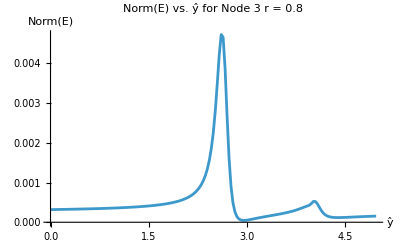

Evaluation time: 27.67134

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat3Array=Range[0,5,0.03];
Δ3NormArray=Table[Δ3Norm[κ]/.{yHat->yHat3Array[[i]]},{i,1,Length@yHat3Array}];
ENorm3Array=Table[NIntegrate[Δ3NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat3Array}];

ListPlot[Transpose@{yHat3Array,ENorm3Array},Joined->True,PlotRange->All,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 3\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

### Node 2

```mathematica
𝔸2[κ_]=γ20+γ21 Cos[κ]+Cos[2 κ]+γ23 Cos[3 κ]+γ24 Cos[4 κ];
𝔹2[κ_]=γ21 Sin[κ]+Sin[2 κ]+γ23 Sin[3 κ]+γ24 Sin[4 κ];
ℂ2[κ_]=a20+a21 Cos[κ]+a22 Cos[2 κ]+a23 Cos[3 κ]+a24 Cos[4 κ]+a25 Cos[5 κ]+a26 Cos[6 κ]+a27 Cos[7 κ]+a28 Cos[8 κ];
𝔻2[κ_]=a21 Sin[κ]+a22 Sin[2 κ]+a23 Sin[3 κ]+a24 Sin[4 κ]+a25 Sin[5 κ]+a26 Sin[6 κ]+a27 Sin[7 κ]+a28 Sin[8 κ];
κBar2Re[κ_]=(𝔸2[κ]*𝔻2[κ]-𝔹2[κ]*ℂ2[κ])/((𝔸2[κ])^2+(𝔹2[κ])^2);
κBar2Im[κ_]=(-𝔸2[κ]*ℂ2[κ]-𝔹2[κ]*𝔻2[κ])/((𝔸2[κ])^2+(𝔹2[κ])^2);
κBar2Norm[κ_]=Abs[κBar2Re[κ]+I*κBar2Im[κ]];
```

```mathematica
Δ2Re[κ_]=(κ*((𝔸2[κ])^2+(𝔹2[κ])^2)-(𝔸2[κ]*𝔻2[κ]-𝔹2[κ]*ℂ2[κ]))^2;
Δ2Im[κ_]=(0*((𝔸2[κ])^2+(𝔹2[κ])^2)-(-𝔸2[κ]*ℂ2[κ]-𝔹2[κ]*𝔻2[κ]))^2;
Δ2Norm[κ_]=(κ-κBar2Norm[κ])^2;
```

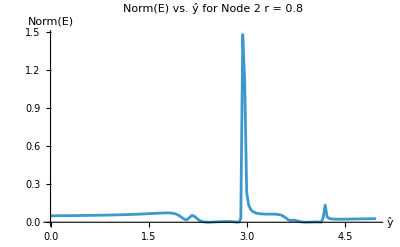

Evaluation time: 27.741012

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat2Array=Range[0,5,0.03];
Δ2NormArray=Table[Δ2Norm[κ]/.{yHat->yHat2Array[[i]]},{i,1,Length@yHat2Array}];
ENorm2Array=Table[NIntegrate[Δ2NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat2Array}];

ListPlot[Transpose@{yHat2Array,ENorm2Array},Joined->True,PlotRange->All,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 2\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

### Node 1

```mathematica
𝔸1[κ_]=γ10+Cos[κ]+γ12 Cos[2 κ]+γ13 Cos[3 κ];
𝔹1[κ_]=Sin[κ]+γ12 Sin[2 κ]+γ13 Sin[3 κ];
ℂ1[κ_]=a10+a11 Cos[κ]+a12 Cos[2 κ]+a13 Cos[3 κ]+a14 Cos[4 κ]+a15 Cos[5 κ]+a16 Cos[6 κ]+a17 Cos[7 κ]+a18 Cos[8 κ];
𝔻1[κ_]=a11 Sin[κ]+a12 Sin[2 κ]+a13 Sin[3 κ]+a14 Sin[4 κ]+a15 Sin[5 κ]+a16 Sin[6 κ]+a17 Sin[7 κ]+a18 Sin[8 κ];
κBar1Re[κ_]=(𝔸1[κ]*𝔻1[κ]-𝔹1[κ]*ℂ1[κ])/((𝔸1[κ])^2+(𝔹1[κ])^2);
κBar1Im[κ_]=(-𝔸1[κ]*ℂ1[κ]-𝔹1[κ]*𝔻1[κ])/((𝔸1[κ])^2+(𝔹1[κ])^2);
κBar1Norm[κ_]=Abs[κBar1Re[κ]+I*κBar1Im[κ]];
```

```mathematica
Δ1Re[κ_]=(κ*((𝔸1[κ])^2+(𝔹1[κ])^2)-(𝔸1[κ]*𝔻1[κ]-𝔹1[κ]*ℂ1[κ]))^2;
Δ1Im[κ_]=(0*((𝔸1[κ])^2+(𝔹1[κ])^2)-(-𝔸1[κ]*ℂ1[κ]-𝔹1[κ]*𝔻1[κ]))^2;
Δ1Norm[κ_]=(κ-κBar1Norm[κ])^2;
```

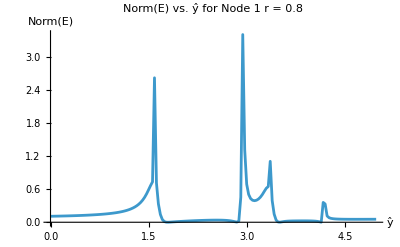

Evaluation time: 52.0023684

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat1Array=Range[0,5,0.03];
Δ1NormArray=Table[Δ1Norm[κ]/.{yHat->yHat1Array[[i]]},{i,1,Length@yHat1Array}];
ENorm1Array=Table[NIntegrate[Δ1NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat1Array}];

ListPlot[Transpose@{yHat1Array,ENorm1Array},Joined->True,PlotRange->All,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 1\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

### Node 0

```mathematica
𝔸0[κ_]=1+γ01 Cos[κ]+γ02 Cos[2 κ];
𝔹0[κ_]=γ01 Sin[κ]+γ02 Sin[2 κ];
ℂ0[κ_]=a00+a01 Cos[κ]+a02 Cos[2 κ]+a03 Cos[3 κ]+a04 Cos[4 κ]+a05 Cos[5 κ]+a06 Cos[6 κ]+a07 Cos[7 κ]+a08 Cos[8 κ];
𝔻0[κ_]=a01 Sin[κ]+a02 Sin[2 κ]+a03 Sin[3 κ]+a04 Sin[4 κ]+a05 Sin[5 κ]+a06 Sin[6 κ]+a07 Sin[7 κ]+a08 Sin[8 κ];
κBar0Re[κ_]=(𝔸0[κ]*𝔻0[κ]-𝔹0[κ]*ℂ0[κ])/((𝔸0[κ])^2+(𝔹0[κ])^2);
κBar0Im[κ_]=(-𝔸0[κ]*ℂ0[κ]-𝔹0[κ]*𝔻0[κ])/((𝔸0[κ])^2+(𝔹0[κ])^2);
κBar0Norm[κ_]=Abs[κBar0Re[κ]+I*κBar0Im[κ]];
```

```mathematica
Δ0Re[κ_]=(κ*((𝔸0[κ])^2+(𝔹0[κ])^2)-(𝔸0[κ]*𝔻0[κ]-𝔹0[κ]*ℂ0[κ]))^2;
Δ0Im[κ_]=(0*((𝔸0[κ])^2+(𝔹0[κ])^2)-(-𝔸0[κ]*ℂ0[κ]-𝔹0[κ]*𝔻0[κ]))^2;
Δ0Norm[κ_]=(κ-κBar0Norm[κ])^2;
```

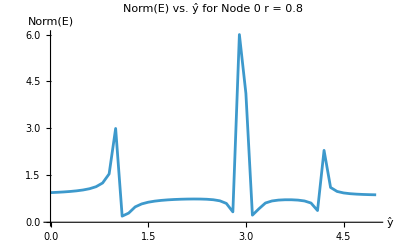

Evaluation time: 249.73884

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat0Array=Range[0,5,0.1];
Δ0NormArray=Table[Δ0Norm[κ]/.{yHat->yHat0Array[[i]]},{i,1,Length@yHat0Array}];
ENorm0Array=Table[NIntegrate[Δ0NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat0Array}];

ListPlot[Transpose@{yHat0Array,ENorm0Array},Joined->True,PlotRange->All,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 0\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

## Spectral Function

### Node 3

```mathematica
Clear[yHat]
SF3Re[κ_,yHat_]=κBar3Re[κ];
SF3Im[κ_,yHat_]=κBar3Im[κ];
SF3Norm[κ_,yHat_]=κBar3Norm[κ];
```

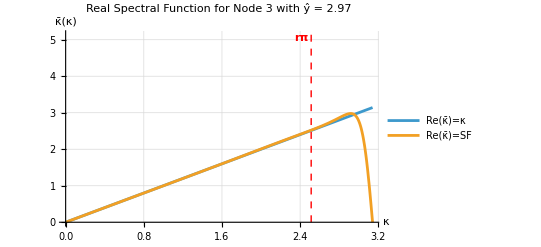

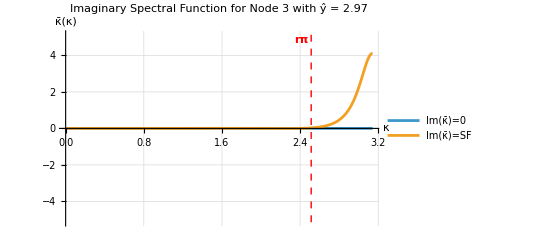

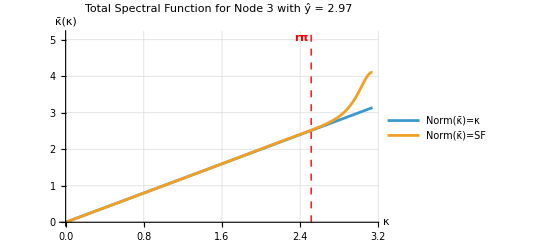

```mathematica
r=0.8;
yHat3List={(*1*)2.97,(*2*)4.38};
yHat=yHat3List[[1]];
Plot[{κ,SF3Re[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 3 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
Plot[{0,SF3Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 3 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ,SF3Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 3 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
```

### Node 2

```mathematica
Clear[yHat]
SF2Re[κ_,yHat_]=κBar2Re[κ];
SF2Im[κ_,yHat_]=κBar2Im[κ];
SF2Norm[κ_,yHat_]=κBar2Norm[κ];
```

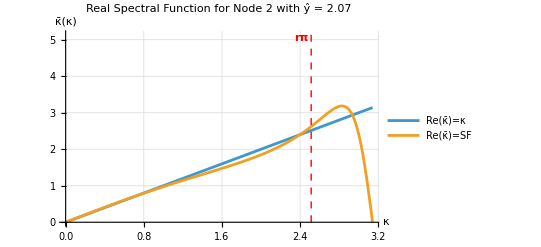

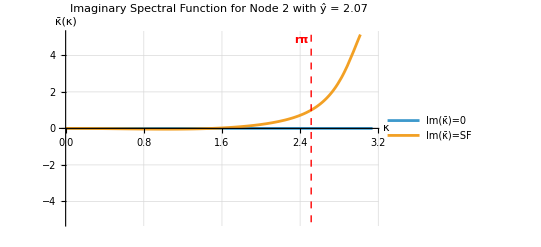

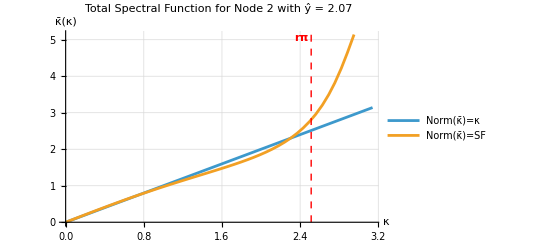

```mathematica
r=0.8;
yHat2List={(*1*)2.07,(*2*)2.40,(*3*)2.85,(*4*)3.90,(*5*)4.14,(*6*)4.41};
yHat=yHat2List[[1]];
Plot[{κ,SF2Re[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
Plot[{0,SF2Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ,SF2Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
```

### Node 1

```mathematica
Clear[yHat]
SF1Re[κ_,yHat_]=κBar1Re[κ];
SF1Im[κ_,yHat_]=κBar1Im[κ];
SF1Norm[κ_,yHat_]=κBar1Norm[κ];
```

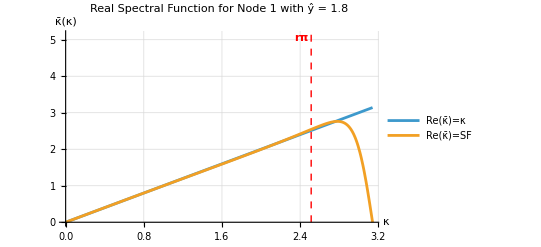

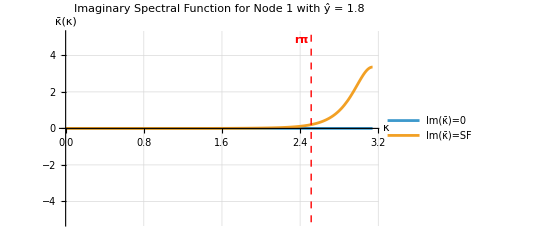

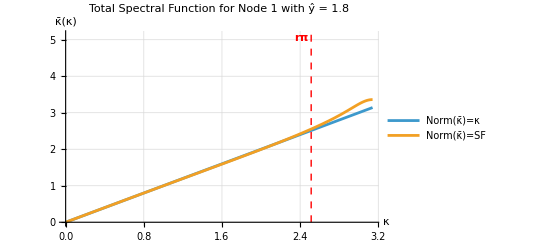

```mathematica
r=0.8;
yHat1List={(*1*)1.80,(*2*)2.85,(*3*)3.12,(*4*)3.51,(*5*)4.14,(*6*)4.71};
yHat=yHat1List[[1]];
Plot[{κ,SF1Re[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
Plot[{0,SF1Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ,SF1Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
```

### Node 0

```mathematica
Clear[yHat]
SF0Re[κ_,yHat_]=κBar0Re[κ];
SF0Im[κ_,yHat_]=κBar0Im[κ];
SF0Norm[κ_,yHat_]=κBar0Norm[κ];
```

```mathematica
r=0.8;
yHat0List={(*1*)1.10,(*2*)2.80,(*3*)3.10,(*4*)4.10};
yHat=yHat0List[[1]];
Plot[{κ,SF0Re[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
Plot[{0,SF0Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ,SF0Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
```

$Aborted

$Aborted

$Aborted

## Output Coefficients

### ŷ Definitions

```mathematica
Clear[yHat,yHat3,yHat2,yHat1,yHat0]

yHat3List={(*1*)2.97,(*2*)4.38};
yHat2List={(*1*)2.07,(*2*)2.40,(*3*)2.85,(*4*)3.90,(*5*)4.14,(*6*)4.41};
yHat1List={(*1*)1.80,(*2*)2.85,(*3*)3.12,(*4*)3.51,(*5*)4.14,(*6*)4.71};
yHat0List={(*1*)1.10,(*2*)2.80,(*3*)3.10,(*4*)4.10};

yHat0=yHat0List[[1]];
yHat2=yHat2List[[1]];
yHat1=yHat1List[[1]];
yHat3=yHat3List[[1]];

yHat0=4.1;
yHat1=1.8;
yHat2=4.14;
yHat3=4.38;
```

### Define Coefficients

```mathematica
Clear[γ33,γ31,γ32,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38]
Clear[γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28]
Clear[γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08]

{γ33val,γ31val,γ32val,γ34val,γ35val,a30val,a31val,a32val,a33val,a34val,a35val,a36val,a37val,a38val}=(1/γ33*{γ33,γ31,γ32,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38}/.bdCoeffs3)/.{yHat->yHat3};
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val,a27val,a28val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val,a17val,a18val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val,a07val,a08val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08}/.bdCoeffs0)/.{yHat->yHat0};
```

### Luke Output

```mathematica
interiorLuke=interiorCoeffsB4/.{a1->a,a2->b,a3->c,a4->d};
boundaryLuke={α12->γ01val,β12->γ02val,α21->γ10val,α22->γ12val,β22->γ13val,β31->γ20val,α31->γ21val,α32->γ23val,β32->γ24val,β41->γ31val,α41->γ32val,α42->γ34val,β42->γ35val,a1->a00val,b1->a01val,c1->a02val,d1->a03val,e1->a04val,f1->a05val,g1->a06val,h1->a07val,i1->a08val,a2->a10val,b2->a11val,c2->a12val,d2->a13val,e2->a14val,f2->a15val,g2->a16val,h2->a17val,i2->a18val,a3->a20val,b3->a21val,c3->a22val,d3->a23val,e3->a24val,f3->a25val,g3->a26val,h3->a27val,i3->a28val,a4->a30val,b4->a31val,c4->a32val,d4->a33val,e4->a34val,f4->a35val,g4->a36val,h4->a37val,i4->a38val};
coeffLuke=Flatten[Join[interiorLuke,boundaryLuke]]
```

{α→0.594235,β→0.102757,a→0.634047,b→0.267266,c→0.0100472,d→-0.000432113,α12→-2.75084,β12→-3.46348,α21→0.0454776,α22→2.70492,β22→1.49359,β31→0.00884999,α31→0.243692,α32→1.19943,β32→0.381558,β41→0.0681779,α41→0.456577,α42→0.766955,β42→0.167388,a1→1.0118,b1→3.27878,c1→-2.79089,d1→-1.93027,e1→0.592692,f1→-0.222586,g1→0.0792287,h1→-0.022063,i1→0.00331363,a2→-0.242463,b2→-1.79968,c2→-0.614678,d2→2.2962,e2→0.414536,f2→-0.0635389,g2→0.0110501,h2→-0.00154435,i2→0.000118508,a3→-0.0494786,b3→-0.511927,c3→-0.777921,d3→0.510757,e3→0.765103,f3→0.0703498,g3→-0.00780823,h3→0.00101663,i3→-0.0000920743,a4→-0.00979903,b4→-0.174337,c4→-0.598448,d4→-0.267127,e4→0.633339,f4→0.396486,g4→0.0213008,h4→-0.00150878,i4→0.0000934119}

### Nate Output

```mathematica
interiorNate=interiorCoeffsB4;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,γ31->γ31val,γ32->γ32val,γ34->γ34val,γ35->γ35val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a07->a07val,a08->a08val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a17->a17val,a18->a18val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val,a27->a27val,a28->a28val,a30->a30val,a31->a31val,a32->a32val,a33->a33val,a34->a34val,a35->a35val,a36->a36val,a37->a37val,a38->a38val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]]
```

{α→0.594235,β→0.102757,a1→0.634047,a2→0.267266,a3→0.0100472,a4→-0.000432113,γ01→-2.75084,γ02→-3.46348,γ10→0.0454776,γ12→2.70492,γ13→1.49359,γ20→0.00884999,γ21→0.243692,γ23→1.19943,γ24→0.381558,γ31→0.0681779,γ32→0.456577,γ34→0.766955,γ35→0.167388,a00→1.0118,a01→3.27878,a02→-2.79089,a03→-1.93027,a04→0.592692,a05→-0.222586,a06→0.0792287,a07→-0.022063,a08→0.00331363,a10→-0.242463,a11→-1.79968,a12→-0.614678,a13→2.2962,a14→0.414536,a15→-0.0635389,a16→0.0110501,a17→-0.00154435,a18→0.000118508,a20→-0.0494786,a21→-0.511927,a22→-0.777921,a23→0.510757,a24→0.765103,a25→0.0703498,a26→-0.00780823,a27→0.00101663,a28→-0.0000920743,a30→-0.00979903,a31→-0.174337,a32→-0.598448,a33→-0.267127,a34→0.633339,a35→0.396486,a36→0.0213008,a37→-0.00150878,a38→0.0000934119}

## Eigenvalue Spectral Analysis

### Modified Boundary Coefficients for Eigenvalue Analysis

```mathematica
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate),
γ31Bar->(γ31/.coeffNate),
γ32Bar->(γ32/.coeffNate),
γ34Bar->(γ34/.coeffNate),
γ35Bar->(γ35/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,8}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,8}]/.coeffNate;
RHSBars3=Table[
ToExpression@StringJoin["a3",ToString@j,"Bar"]->(ToExpression@StringJoin["a3",ToString@j]),
{j,1,8}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2,RHSBars3]
```

{γ12Bar→2.54416,γ13Bar→1.32752,γ21Bar→0.10365,γ23Bar→1.91879,γ24Bar→0.805622,γ31Bar→0.0681779,γ32Bar→0.456577,γ34Bar→0.766955,γ35Bar→0.167388,a11Bar→-1.73211,a12Bar→-0.433521,a13Bar→2.11891,a14Bar→0.344486,a15Bar→-0.0474768,a16Bar→0.00661894,a17Bar→-0.000480826,a18Bar→-0.0000286093,a21Bar→-0.341427,a22Bar→-1.38994,a23Bar→0.134947,a24Bar→1.44512,a25Bar→0.174644,a26Bar→-0.0210266,a27Bar→0.00278105,a28Bar→-0.000243098,a31Bar→-0.174337,a32Bar→-0.598448,a33Bar→-0.267127,a34Bar→0.633339,a35Bar→0.396486,a36Bar→0.0213008,a37Bar→-0.00150878,a38Bar→0.0000934119}

### Build Modified Matrices (needs cleaning badly)

```mathematica
Clear[LHS,RHS]
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=4;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],

If[(i==3&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==3&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==3&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==3&&j==5),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i-2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}]

k=9; (*Size*)
MatrixForm@LHS[k]

MatrixForm@(LHS[k]/.coeffNate)/.barCoeffs
```

(1 | γ12Bar | γ13Bar | 0 | 0 | 0 | 0 | 0 | 0
γ21Bar | 1 | γ23Bar | γ24Bar | 0 | 0 | 0 | 0 | 0
γ31Bar | γ32Bar | 1 | γ34Bar | γ35Bar | 0 | 0 | 0 | 0
0 | β | α | 1 | α | β | 0 | 0 | 0
0 | 0 | β | α | 1 | α | β | 0 | 0
0 | 0 | 0 | γ35 | γ34 | 1 | γ32 | γ31 | 0
0 | 0 | 0 | 0 | γ24 | γ23 | 1 | γ21 | γ20
0 | 0 | 0 | 0 | 0 | γ13 | γ12 | 1 | γ10
0 | 0 | 0 | 0 | 0 | 0 | γ02 | γ01 | 1)

(1 | 2.54416 | 1.32752 | 0 | 0 | 0 | 0 | 0 | 0
0.10365 | 1 | 1.91879 | 0.805622 | 0 | 0 | 0 | 0 | 0
0.0681779 | 0.456577 | 1 | 0.766955 | 0.167388 | 0 | 0 | 0 | 0
0 | 0.102757 | 0.594235 | 1 | 0.594235 | 0.102757 | 0 | 0 | 0
0 | 0 | 0.102757 | 0.594235 | 1 | 0.594235 | 0.102757 | 0 | 0
0 | 0 | 0 | 0.167388 | 0.766955 | 1 | 0.456577 | 0.0681779 | 0
0 | 0 | 0 | 0 | 0.381558 | 1.19943 | 1 | 0.243692 | 0.00884999
0 | 0 | 0 | 0 | 0 | 1.49359 | 2.70492 | 1 | 0.0454776
0 | 0 | 0 | 0 | 0 | 0 | -3.46348 | -2.75084 | 1)

```mathematica
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,
If[(i==1&&j==7),a17Bar,
If[(i==1&&j==8),a18Bar,

If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,
If[(i==2&&j==7),a27Bar,
If[(i==2&&j==8),a28Bar,

If[(i==3&&j==1),a31Bar,
If[(i==3&&j==2),a32Bar,
If[(i==3&&j==3),a33Bar,
If[(i==3&&j==4),a34Bar,
If[(i==3&&j==5),a35Bar,
If[(i==3&&j==6),a36Bar,
If[(i==3&&j==7),a37Bar,
If[(i==3&&j==8),a38Bar,

If[(i==k&&j==k),-a00,
If[(i==k&&j==k-1),-a01,
If[(i==k&&j==k-2),-a02,
If[(i==k&&j==k-3),-a03,
If[(i==k&&j==k-4),-a04,
If[(i==k&&j==k-5),-a05,
If[(i==k&&j==k-6),-a06,
If[(i==k&&j==k-7),-a07,
If[(i==k&&j==k-8),-a08,
If[(i==k-1&&j==k),-a10,
If[(i==k-1&&j==k-1),-a11,
If[(i==k-1&&j==k-2),-a12,
If[(i==k-1&&j==k-3),-a13,
If[(i==k-1&&j==k-4),-a14,
If[(i==k-1&&j==k-5),-a15,
If[(i==k-1&&j==k-6),-a16,
If[(i==k-1&&j==k-7),-a17,
If[(i==k-1&&j==k-8),-a18,
If[(i==k-2&&j==k),-a20,
If[(i==k-2&&j==k-1),-a21,
If[(i==k-2&&j==k-2),-a22,
If[(i==k-2&&j==k-3),-a23,
If[(i==k-2&&j==k-4),-a24,
If[(i==k-2&&j==k-5),-a25,
If[(i==k-2&&j==k-6),-a26,
If[(i==k-2&&j==k-7),-a27,
If[(i==k-2&&j==k-8),-a28,
If[(i==k-3&&j==k),-a30,
If[(i==k-3&&j==k-1),-a31,
If[(i==k-3&&j==k-2),-a32,
If[(i==k-3&&j==k-3),-a33,
If[(i==k-3&&j==k-4),-a34,
If[(i==k-3&&j==k-5),-a35,
If[(i==k-3&&j==k-6),-a36,
If[(i==k-3&&j==k-7),-a37,
If[(i==k-3&&j==k-8),-a38,


If[i-4==j,-a4,
If[i-3==j,-a3,
If[i-2==j,-a2,
If[i-1==j, -a1,
If[i==j, 0,
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
If[i+4==j,a4,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}]

k=11; (*Size*)
MatrixForm@RHS[k]

MatrixForm@(RHS[k]/.coeffNate)/.barCoeffs
```

(a11Bar | a12Bar | a13Bar | a14Bar | a15Bar | a16Bar | a17Bar | a18Bar | 0 | 0 | 0
a21Bar | a22Bar | a23Bar | a24Bar | a25Bar | a26Bar | a27Bar | a28Bar | 0 | 0 | 0
a31Bar | a32Bar | a33Bar | a34Bar | a35Bar | a36Bar | a37Bar | a38Bar | 0 | 0 | 0
-a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | a4 | 0 | 0 | 0
-a4 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | a4 | 0 | 0
0 | -a4 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | a4 | 0
0 | 0 | -a4 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | a4
0 | 0 | -a38 | -a37 | -a36 | -a35 | -a34 | -a33 | -a32 | -a31 | -a30
0 | 0 | -a28 | -a27 | -a26 | -a25 | -a24 | -a23 | -a22 | -a21 | -a20
0 | 0 | -a18 | -a17 | -a16 | -a15 | -a14 | -a13 | -a12 | -a11 | -a10
0 | 0 | -a08 | -a07 | -a06 | -a05 | -a04 | -a03 | -a02 | -a01 | -a00)

(-1.73211 | -0.433521 | 2.11891 | 0.344486 | -0.0474768 | 0.00661894 | -0.000480826 | -0.0000286093 | 0 | 0 | 0
-0.341427 | -1.38994 | 0.134947 | 1.44512 | 0.174644 | -0.0210266 | 0.00278105 | -0.000243098 | 0 | 0 | 0
-0.174337 | -0.598448 | -0.267127 | 0.633339 | 0.396486 | 0.0213008 | -0.00150878 | 0.0000934119 | 0 | 0 | 0
-0.0100472 | -0.267266 | -0.634047 | 0 | 0.634047 | 0.267266 | 0.0100472 | -0.000432113 | 0 | 0 | 0
0.000432113 | -0.0100472 | -0.267266 | -0.634047 | 0 | 0.634047 | 0.267266 | 0.0100472 | -0.000432113 | 0 | 0
0 | 0.000432113 | -0.0100472 | -0.267266 | -0.634047 | 0 | 0.634047 | 0.267266 | 0.0100472 | -0.000432113 | 0
0 | 0 | 0.000432113 | -0.0100472 | -0.267266 | -0.634047 | 0 | 0.634047 | 0.267266 | 0.0100472 | -0.000432113
0 | 0 | -0.0000934119 | 0.00150878 | -0.0213008 | -0.396486 | -0.633339 | 0.267127 | 0.598448 | 0.174337 | 0.00979903
0 | 0 | 0.0000920743 | -0.00101663 | 0.00780823 | -0.0703498 | -0.765103 | -0.510757 | 0.777921 | 0.511927 | 0.0494786
0 | 0 | -0.000118508 | 0.00154435 | -0.0110501 | 0.0635389 | -0.414536 | -2.2962 | 0.614678 | 1.79968 | 0.242463
0 | 0 | -0.00331363 | 0.022063 | -0.0792287 | 0.222586 | -0.592692 | 1.93027 | 2.79089 | -3.27878 | -1.0118)

### Plot Eigenvalue Spectra

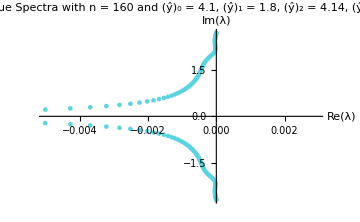

```mathematica
k=160;
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2],", (ŷ)_3 = ",ToString[yHat3]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat1/5,yHat2/5,yHat3/5]]
```

## Dendro Output

### Hide

```mathematica
derivativeOrder=1;
interiorOrder=n;
totalBoundRows=numBoundaryRows;
freeInteriorParameters={};
freeBoundaryParameters={};
RHSInteriorList=RHSPars;
interiorParametersValues=interiorCoeffsB4/.{α->alpha,β->beta};
boundaryParametersValues=boundaryLuke/.{α12->gamma01,β12->gamma02,α21->gamma10,α22->gamma12,β22->gamma13,β31->gamma20,α31->gamma21,α32->gamma23,β32->gamma24,β41->gamma31,α41->gamma32,α42->gamma34,β42->gamma35,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,h1->a07,i1->a08,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,h2->a17,i2->a18,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26,h3->a27,i3->a28,a4->a30,b4->a31,c4->a32,d4->a33,e4->a34,f4->a35,g4->a36,h4->a37,i4->a38};
LHSBoundaryList={gamma01,gamma02,gamma10,gamma12,gamma13,gamma20,gamma21,gamma23,gamma24,gamma31,gamma32,gamma34,gamma35};
RHSBoundaryList={a00,a01,a02,a03,a04,a05,a06,a07,a08,a10,a11,a12,a13,a14,a15,a16,a17,a18,a20,a21,a22,a23,a24,a25,a26,a27,a28,a30,a31,a32,a33,a34,a35,a36,a37,a38};
(*Don't need to mess with these until we incorporate this procedure with James's filtering*)
filterIntCoeff;
filterBoundCoeff;
filterIntParam;
filterBoundParam;
filtering=False;
(*boundary={α12->γ01,β12->γ02,α21->γ10,α22->γ12,β22->γ13,β31->γ20,α31->γ21,α32->γ23,β32->γ24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};*)
```

```mathematica
(*****************Print coefficients in Dendro-GR Format*****************)
If[derivativeOrder==1,
LHSName="P1";
RHSName="Q1";
nth="1st";
coeffs="D_coeffs";
order="First",
If[derivativeOrder==2,
LHSName="P2";
RHSName="Q2";
nth="2nd";
coeffs="D_coeffs";
order="Second"]];
If[LHSBandCount==3,
LHSStructure="T",
If[LHSBandCount==5,
LHSStructure="P"]];

(*Convert Mathematica expression syntax to C/C++ expression syntax*)
convertToCCode[expr_]:=Module[{str},str=ToString[expr,InputForm];
(*Add ".0" to standalone integers but not to variables with numbers*)
(*Formatting adjustments to match C/C++ syntax*)str=StringReplace[str,{" "->"","*"->" * ","/"->" / ","+"->" + ","-"->" - ","^"->" ^ "}];
str]
(*Function to generate the line of C/C++ code to define the fixed variables*)
generateCAssignment[rule_]:=Module[{variable,expression,cCode,cAssignment},
variable=ToString[rule[[1]]];
expression=rule[[2]];
cCode=convertToCCode[expression];
cAssignment="double "<>variable<>" = "<>cCode<>";";
cAssignment
]






(*Initial Block*)
initialBlock=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order"}];
initialBlock2=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order","Filtered"}];

(*Free Parameters Block*)
freeParameters=Join[freeInteriorParameters,freeBoundaryParameters];
numFreePars=Length[freeParameters];
alphaPrint=StringReplace[generateCAssignment[Select[interiorParametersValues,#[[1]]===alpha&][[1]]],"alpha"->"alpha0"];
freeParPrints={};
If[numFreePars>0,
For[i=1,i<=numFreePars,i++,
AppendTo[freeParPrints,StringJoin[{"\n\t\tdouble ",ToString[freeParameters[[i]]]," = ",coeffs,"[",ToString[i],"];"}]]]]
freeParametersBlock=StringJoin[{"\t",alphaPrint,"\n\t\tdouble alpha = alpha0 + ",coeffs,"[0];",freeParPrints}];

(*Filter*)
freeParPrints2={};
freeParametersBlock2=StringJoin[{"\t","\n\t\tdouble alpha = ","F_coeffs","[0];",If[LHSBandCount==5,StringJoin["\n\t\tdouble beta = ","F_coeffs","[1];"],""]}];

(*Fixed Parameters Block*)
(*Create a list of the solved fixed parameters in C/C++ syntax*)
interiorParametersValues3=DeleteCases[interiorParametersValues,Rule[alpha,_]];
interiorParameterPrints=Table[
generateCAssignment[interiorParametersValues3[[i]]],
{i,1,Length[interiorParametersValues]-1}
];
boundaryParameterPrints=Table[
generateCAssignment[boundaryParametersValues[[i]]],
{i,1,Length[boundaryParametersValues]}
];
(*For filtered coefficients*)
interiorParameterPrints2=Table[
generateCAssignment[filterIntCoeff[[i]]],
{i,1,Length[filterIntCoeff]}
];
boundaryParameterPrints2=Table[
generateCAssignment[filterBoundCoeff[[i]]],
{i,1,Length[filterBoundCoeff]}
];
(*Print the coefficients in a single block of text rather than individual lines*)
fixedParametersBlockD=StringJoin["\t\t",Riffle[Join[interiorParameterPrints,boundaryParameterPrints],"\n\t\t"]];
fixedParametersBlockD2=StringJoin["\t\t",Riffle[Join[interiorParameterPrints2,boundaryParameterPrints2],"\n\t\t"]];

(*Structure Block*)
(*LHS Boundary*)
PDiagBoundary="";
LHSRowList=ToExpression[GatherBy[LHSBoundaryList,StringDrop[ToString[#],5]~StringTake~1&]];
For[i=1,i<=Length[LHSRowList],i++,
If[i==1,PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t","{1.0, ",StringDrop[ToString[LHSRowList[[i]]],1],","]];
If[i==2,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1}]],1],","]]];
If[i==3,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{","0.0, ",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t",StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
If[i>=4,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],StringDrop[StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
];
(*LHS Filter Boundary*)
RDiagBoundary="";
For[i=1,i<=Length@filterBoundParam,i++,
If[i==1,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha, beta},"]];
];
If[i==2,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha 1.0, alpha, beta},"]];
];
If[i>=3,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],"alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],"beta, alpha, 1.0, alpha, beta},"]];
];
];

(*LHS Interior*)
If[LHSBandCount==3,
PDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
PDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];
(*LHS Filter Interior*)
If[LHSBandCount==3,
RDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
RDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];

(*RHS Boundary*)
QDiagBoundary="";
RHSRowList=ToExpression[GatherBy[RHSBoundaryList,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList],i++,QDiagBoundary=StringJoin[QDiagBoundary,"\n\t\t\t",ToString[RHSRowList[[i]]],","]]
(*RHS Filter Boundary*)
SDiagBoundary="";
RHSRowList2=ToExpression[GatherBy[filterBoundParam,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList2],i++,SDiagBoundary=StringJoin[SDiagBoundary,"\n\t\t\t",ToString[RHSRowList2[[i]]]]]

(*RHS Interior*)
QDiagInterior={};
len=(2*Length[RHSInteriorList]+1);
If[derivativeOrder==1,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[-RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"0.0"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]
],
If[derivativeOrder==2,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[-RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"t1"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]]]]

(*RHS Filter Interior*)
SDiagInterior={};
newFilterIntParam=Drop[filterIntParam,1];
len=(2*Length[newFilterIntParam]+1);
For[i=1,i<=len,i++,
If[i<=Length[newFilterIntParam],PrependTo[SDiagInterior,ToString[newFilterIntParam[[i]]]<>"/"<>ToString[2]<>".0"]];
If[i==(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,"a0"]];
If[i>(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,ToString[newFilterIntParam[[i-Length[newFilterIntParam]-1]]]<>"/"<>ToString[2]<>".0"]]
]


PDiagBoundaryStr=StringDrop[StringDrop[PDiagBoundary,1],-1];
PDiagInteriorStr=StringDrop[StringDrop[PDiagInterior,1],-1];
RDiagBoundaryStr=StringDrop[StringDrop[RDiagBoundary,1],-1];
RDiagInteriorStr=StringDrop[StringDrop[RDiagInterior,1],-1];
QDiagBoundaryStr=StringDrop[StringDrop[QDiagBoundary,1],-1];
QDiagInteriorStr=StringDrop[StringDrop[ToString[QDiagInterior],1],-1];
SDiagBoundaryStr=StringDrop[SDiagBoundary,1];
SDiagInteriorStr=StringDrop[StringDrop[ToString[SDiagInterior],1],-1];

(*Subscript[t, 1] is the middle RHS Interior Coefficient for Second Derivatives*)
t1List={};
For[i=1,i<=Length[RHSInteriorList],i++,
AppendTo[t1List,ToString[RHSInteriorList[[i]]]<>"/"<>ToString[i^2]<>".0"]
];
If[derivativeOrder==1,
t1="",
If[derivativeOrder==2,
t1=StringJoin["-2.0 * ("<>StringDrop[StringDrop[ToString[t1List],1],-1]<>")"]]];


If[filtering,
filterFinalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock2,"(\n","\tconst std::vector<double>& ","F_coeffs",") {\n","\t",freeParametersBlock2,"\n\n",fixedParametersBlockD2,"\n\n","\t\t// boundary elements for R matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","R","DiagBoundary{\n",RDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for R matrix for ",nth," derivative\n","\t\tstd::vector<double> ","R","DiagInterior{\n","\t\t\t",RDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for S matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","S","DiagBoundary\n",SDiagBoundaryStr,"\n","\t\t;\n\n","\t\t// diagonal elements for S matrix for ",nth," derivative\n","\t\tstd::vector<double> ","S","DiagInterior{\n","\t\t\t",SDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t","R","DiagInterior, ","S","DiagInterior, ","S","DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}"}];
]

finalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock,"(\n","\tconst std::vector<double>& ",coeffs,") {\n","\t",freeParametersBlock,"\n\n",fixedParametersBlockD,"\n\n","\t\t// boundary elements for P matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",LHSName,"DiagBoundary{\n",PDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for P matrix for ",nth," derivative\n","\t\tstd::vector<double> ",LHSName,"DiagInterior{\n","\t\t\t",PDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",RHSName,"DiagBoundary{\n",QDiagBoundaryStr,"\n","\t\t};\n\n",If[derivativeOrder==1,t1,If[derivativeOrder==2,"\t\tdouble t1 = "<>t1<>";\n"]],"\t\t// diagonal elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<double> ",RHSName,"DiagInterior{\n","\t\t\t",QDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t",LHSName,"DiagInterior, ",LHSName,"DiagBoundary, ",RHSName,"DiagInterior, ",RHSName,"DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}",If[filtering,"\n\n"<>filterFinalBlock,""]}];
```

GatherBy::list: List expected at position 1 in GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&].

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Drop::drop: Cannot drop positions 1 through 1 in filterIntParam.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

StringDrop::drop: Cannot drop positions 1 through 1 in "".

### Show

```mathematica
outExt="h";
(*Print header*)
Print[Style["Dendro-Ready Coefficients (Copied to clipboard):",Bold,FontSize->24]];
Print[finalBlock];
(*Copy the block of text to the user's clipboard*)
CopyToClipboard[finalBlock];

(*Save to output file*)
fileName=StringJoin[{"BYU_B4","_yHat0_",ToString[yHat0],"_yHat1_",ToString[yHat1],"_yHat2_",ToString[yHat2],"_yHat3_",ToString[yHat3],".",outExt}];
Export[fileName,finalBlock,"Text"];
Print[StringJoin[{"Saved to file: ",fileName}]]
```

Dendro-Ready Coefficients (Copied to clipboard):

MatrixDiagonalEntries* BYUDerivsP6R4DiagonalsFirstOrder(
	const std::vector<double>& D_coeffs) {
		double alpha0 = 0.59067138684056;
		double alpha = alpha0 + D_coeffs[0];

		double beta = 0.10005088370852962;
		double a1 = 0.6375976953896195;
		double a2 = 0.26328410014665704;
		double a3 = 0.009340368066539819;
		double a4 =  - 0.0003661823333658686;
		double gamma01 = 1.9429265968126401;
		double gamma02 = 2.4621754563022478;
		double gamma10 =  - 0.11667782650556546;
		double gamma12 =  - 17.193865340181674;
		double gamma13 =  - 9.39872085284378;
		double gamma20 = 0.20719757825417595;
		double gamma21 = 5.509156946224238;
		double gamma23 = 32.9663351127424;
		double gamma24 = 10.370454614959954;
		double gamma31 =  - 1.412205637381021;
		double gamma32 =  - 12.179494791248999;
		double gamma34 =  - 22.605979156927333;
		double gamma35 =  - 4.717823329386192;
		double a00 =  - 0.6711965370977566;
		double a01 =  - 2.421779258314018;
		double a02 = 2.0859266290726737;
		double a03 = 1.2543682073520586;
		double a04 =  - 0.31862314280448345;
		double a05 = 0.08998417189866359;
		double a06 =  - 0.022661156448407382;
		double a07 = 0.004487199819524612;
		double a08 =  - 0.0005061136154759227;
		double a10 = 1.53741941875424;
		double a11 = 11.47953998576969;
		double a12 = 3.8008470975778437;
		double a13 =  - 14.58490089913063;
		double a14 =  - 2.5556001658142122;
		double a15 = 0.37604524502211234;
		double a16 =  - 0.059969678023698236;
		double a17 = 0.0069917829624128736;
		double a18 =  - 0.0003727870949550155;
		double a20 =  - 0.9347303475345967;
		double a21 =  - 12.627080075062452;
		double a22 =  - 22.679232689047012;
		double a23 = 13.400628101848667;
		double a24 = 21.211257893886796;
		double a25 = 1.7860848769078075;
		double a26 =  - 0.17403439487614847;
		double a27 = 0.018333978323435862;
		double a28 =  - 0.0012273444489978337;
		double a30 = 0.13359381233000178;
		double a31 = 4.138924951595243;
		double a32 = 17.88103301327942;
		double a33 = 9.05327613445678;
		double a34 =  - 19.2179998786429;
		double a35 =  - 11.464399787180412;
		double a36 =  - 0.5586519666134571;
		double a37 = 0.036240008477330776;
		double a38 =  - 0.002016287701435117;

		// boundary elements for P matrix for 1st derivative
		std::vector<std::vector<double>> P1DiagBoundary{
			{1.0, gamma01, gamma02},
			{gamma10, 1.0, gamma12, gamma13},
			{gamma20, gamma21, 1.0, gamma23, gamma24},
			{0.0, gamma31, gamma32, 1.0, gamma34, gamma35}
		};

		// diagonal elements for P matrix for 1st derivative
		std::vector<double> P1DiagInterior{
			beta, alpha, 1.0, alpha, beta
		};

		// boundary elements for Q matrix for 1st derivative
		std::vector<std::vector<double>> Q1DiagBoundary{
			{a00, a01, a02, a03, a04, a05, a06, a07, a08},
			{a10, a11, a12, a13, a14, a15, a16, a17, a18},
			{a20, a21, a22, a23, a24, a25, a26, a27, a28},
			{a30, a31, a32, a33, a34, a35, a36, a37, a38}
		};

		// diagonal elements for Q matrix for 1st derivative
		std::vector<double> Q1DiagInterior{
			-a4, -a3, -a2, -a1, 0.0, a1, a2, a3, a4
		};

		// store the entries for matrix creation
		MatrixDiagonalEntries* diagEntries = new
			MatrixDiagonalEntries{
				P1DiagInterior, P1DiagBoundary, Q1DiagInterior, Q1DiagBoundary
			};
		return diagEntries;
	}

Saved to file: BYU_P6_yHat0_1.1_yHat1_1.8_yHat2_2.4_yHat3_2.9.h

# P4 (C4) Scheme

## Initialization

The matrix system of equations we are solving for this scheme is:
	P=(1
γ_10
β
0
0 γ_01
1
α
γ_13
0 γ_02
γ_12
1
γ_12
γ_02 0
γ_13
α
1
γ_01 0
0
β
γ_10
1)
	Q=(a_00
a_10
-a_2
-a_14
-a_04 a_01
a_11
-a_1
-a_13
-a_03 a_02
a_12
0
-a_12
-a_02 a_03
a_13
a_1
-a_11
-a_01 a_04
a_14
a_2
-a_10
-a_00)

```mathematica
(*From KimInteriorOptimization.nb, one day to be merged with this one. Or I could DumpSave[] in that notebook and then Get[] here.*)
interiorCoeffsC4={α->0.5362930888943283,β->0.05831696520179083,a1->0.6899191224266673,a2->0.20234546583472587};
(*DumpSave["C4_interiorCoeffs.mx","Global`interiorCoeffsC4"];*)

(*If you have the .mx files in the same directory as this notebook, these will let you skip the long computation of defining bdCoeffs under the "Solve for Boundary Coefficients" section*)
Get["C4_interiorCoeffs.mx"]
Get["C4_bdCoeffs1.mx"];
Get["C4_bdCoeffs0.mx"];
```

## General Extrapolation Polynomial

For the P4 (C4) scheme, we have:
	LHSBandCount = 5
	n = 4
	freeInteriorPars = 2
	yDeriv = 6

```mathematica
(*User chooses these parameters, the rest is calculated from these*)
LHSBandCount=5; (*3 for tridiagonal, 5 for pentadiagonal*)
n=4; (*order of the scheme*)
freeInteriorPars=2; (*number of free parameters used for Kim's optimization on the interior*)
yDeriv=6; (*(d^n P)/dx^n(ŷ)=0 from Kim 2024 Eq. 10, this is n in that equation*) (*provide constraints on what the user can choose for this. Upper bound should be polynomialorder to prevent the matrix from being singular, and lower bound should be order·2 I think.*)

LHSPars=Switch[LHSBandCount,3,{α},5,{α,β}];
RHSPars=Table[ToExpression[StringJoin["a",ToString[i]]],{i,1,Ceiling[n/2]-Length@LHSPars+freeInteriorPars}];
numBoundaryRows=Length@RHSPars;
fOrder=(2*Length@RHSPars)+1;
fpOrder=LHSBandCount+(numBoundaryRows-(LHSBandCount-1)/2);
PolynomialOrder=fOrder+fpOrder;


rowf1=Join[{1},Table[0,{i,1,PolynomialOrder}]];
rowf=Table[Table[i^j,{j,0,PolynomialOrder}],{i,1,fOrder-1}];
rowfp1=Join[{0,1},Table[0,{i,2,PolynomialOrder}]];
rowfp=Table[Table[j i^(j-1),{j,0,PolynomialOrder}],{i,1,fpOrder-1}];
rowyHat=Join[Table[0,{i,1,yDeriv}],Table[(i!)/((i-yDeriv)!) yHat^(i-yDeriv),{i,yDeriv,PolynomialOrder}]];

matf=PrependTo[rowf,rowf1];
matfp=PrependTo[rowfp,rowfp1];
matfCombined=Join[matf,matfp];
LMat=AppendTo[matfCombined,rowyHat];

pVec=Table[ToExpression[StringJoin["p",ToString[i]]],{i,0,PolynomialOrder}];
fVec=Join[Table[ToExpression[StringJoin["f",ToString[i]]],{i,0,fOrder-1}],Table[ToExpression[StringJoin["fp",ToString[i]]],{i,0,fpOrder-1}],{0}];

pCoeffs=Solve[LMat.pVec==fVec,pVec][[1]];

yHatSingularities=(Transpose@Solve[Det[LMat]==0,yHat])[[1]]//N;
P[x_]=Total[Table[pVec[[i+1]]*x^i,{i,0,PolynomialOrder}]]/.pCoeffs;

Print["System:\n",MatrixForm[LMat]," ",MatrixForm[pVec]," = ",MatrixForm[fVec]]
Print["Singularities:\n",MatrixForm[yHatSingularities]]
(*Print["Coefficients:\n",MatrixForm[pCoeffs]]*)
```

System:
(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 4 | 8 | 16 | 32 | 64 | 128 | 256 | 512 | 1024
1 | 3 | 9 | 27 | 81 | 243 | 729 | 2187 | 6561 | 19683 | 59049
1 | 4 | 16 | 64 | 256 | 1024 | 4096 | 16384 | 65536 | 262144 | 1048576
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
0 | 1 | 4 | 12 | 32 | 80 | 192 | 448 | 1024 | 2304 | 5120
0 | 1 | 6 | 27 | 108 | 405 | 1458 | 5103 | 17496 | 59049 | 196830
0 | 1 | 8 | 48 | 256 | 1280 | 6144 | 28672 | 131072 | 589824 | 2621440
0 | 0 | 0 | 0 | 0 | 0 | 720 | 5040 yHat | 20160 yHat^2 | 60480 yHat^3 | 151200 yHat^4) (p0
p1
p2
p3
p4
p5
p6
p7
p8
p9
p10) = (f0
f1
f2
f3
f4
fp0
fp1
fp2
fp3
fp4
0)

Singularities:
(yHat→1.63853
yHat→2.36147
yHat→0.903336
yHat→3.09666)

## Solve for Boundary Coefficients

Goal:
	Solve a system of equations for bdCoeffsList1 in terms of the optimization free parameter ŷ
Variables:
	fVars1: List of f_i and f_i' variables that will appear in the shifted stencil for Node 1
	bdCoeffsList1: List of boundary coefficients that will appear in the shifted stencil for Node 1
	schemeShifted: The shifted scheme for Node 1
	schemeCentered: The centered scheme for Node 1 in terms of the extrapolation polynomial P(x)
		NOTE: To make the Collect[] process easier, we write these schemes as LHS-RHS=0 rather than the usual LHS=RHS.
	schemeNode2: The scheme for Node 2, which only depends on interiorCoeffsC6
	SOLfp4: The solution to Node 2’s scheme equation for f_4' in terms of fVars1
	eq: Scheme equation where the coefficient terms from schemeCentered and schemeShifted are set equal to each other
	coeffEqs1: System of equations with each of the coefficient terms equal to each other
	bdCoeffs1: Solution to the system of equations for bdCoeffsList1 in terms of ŷ
Process:
	1. Initialize the necessary equations.
	2. We want schemeShifted and schemeCentered to both be in terms of fVars1 with some coefficients. Due to the presence of P(x) terms in schemeCentered, it is in terms of fVars1 as well as f_4'. We eliminate the dependence on f_4' by using Node 2’s scheme to solve for f_4' in terms of fVars1.
	3. Now that schemeShifted and schemeCentered are both in terms of fVars1, we construct a system of equations by equating the coefficient in front of each term of fVars1 in schemeCentered with the corresponding coefficient in front of the same term in schemeShifted.
	4. We solve this system of equations for bdCoeffsList1 in terms of interiorCoeffsC6 (which are substituted in) and the optimization free parameter ŷ.
		NOTE: In the standard scheme approach, we set γ_11=1 to ensure the main diagonal of the LHS matrix is all 1’s. When solving this system of equations, we must include γ_11 so that bdCoeffsList1 and fVars1 have the same length since this allows us to find a unique solution to the system of equations. We apply the normal condition later on.
	5. OPTIONAL: We may save the variable bdCoeffs1 to a binary file in the current directory. This is helpful to avoid having to run this process multiple times, as it can become computationally expensive.
Differences:
	For Node 0, the entire process translates directly with a few changes. fVars, bdCoeffsList, schemeShifted, and schemeCentered all change, as we are considering the scheme for a different row, but the equations have the same structure. The main notable difference is in Step 2; In addition to substituting in the solution from Node 2 for f_4' in terms of the other fVars, we must also do the same for f_3' using Node 1.

### Node 1

```mathematica
(*----------STEP 1----------*)
fVars1={fp0,fp1,fp2,fp3,f0,f1,f2,f3,f4};
bdCoeffsList1={γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14};
schemeShifted=γ10 fp0+γ11 fp1+γ12 fp2+γ13 fp3-(a10 f0+a11 f1+a12 f2+a13 f3+a14 f4); (*==0*)
schemeCentered=β P'[-1]+α fp0+fp1+α fp2+β fp3-(-a2 P[-1]-a1 f0+a1 f2+a2 f3); (*==0*)

(*----------STEP 2----------*)
schemeNode2=β fp0+α fp1+fp2+α fp3+β fp4==-a2 f0-a1 f1+a1 f3+a2 f4;

SOLfp4=Solve[schemeNode2,fp4][[1,1]]/.interiorCoeffsC4;
schemeCentered=schemeCentered/.SOLfp4;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars1];

(*----------STEP 4----------*)
coeffEqs1=Table[Coefficient[eq,fVars1[[i]]]==0,{i,1,Length@fVars1}];
bdCoeffs1=(Solve[coeffEqs1,bdCoeffsList1][[1]])/.interiorCoeffsC4;

(*----------STEP 5----------*)
DumpSave["C4_bdCoeffs1.mx","Global`bdCoeffs1"]
```

{Global`bdCoeffs1}

### Node 0

```mathematica
(*----------STEP 1----------*)
fVars0={fp0,fp1,fp2,f0,f1,f2,f3,f4};
bdCoeffsList0={γ00,γ01,γ02,a00,a01,a02,a03,a04};
schemeShifted=γ00 fp0+γ01 fp1+γ02 fp2-(a00 f0+a01 f1+a02 f2+a03 f3+a04 f4); (*==0*)
schemeCentered=β P'[-2]+α P'[-1]+fp0+α fp1+β fp2-(-a2 P[-2]-a1 P[-1]+a1 f1+a2 f2); (*==0*)

(*----------STEP 2----------*)
schemeNode2=β fp0+α fp1+fp2+α fp3+β fp4==-a2 f0-a1 f1+a1 f3+a2 f4;
schemeNode1=γ10 fp0+γ11 fp1+γ12 fp2+γ13 fp3==a10 f0+a11 f1+a12 f2+a13 f3+a14 f4;

SOLfp4=Solve[schemeNode2,fp4][[1,1]]/.interiorCoeffsC4;
SOLfp3=Solve[schemeNode1,fp3][[1,1]]/.bdCoeffs1;
schemeCentered=schemeCentered/.SOLfp4/.SOLfp3;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars0];

(*----------STEP 4----------*)
coeffEqs0=Table[Coefficient[eq,fVars0[[i]]]==0,{i,1,Length@fVars0}];
bdCoeffs0=(Solve[coeffEqs0,bdCoeffsList0][[1]])/.interiorCoeffsC4;

(*----------STEP 5----------*)
DumpSave["C4_bdCoeffs0.mx","Global`bdCoeffs0"]
```

{Global`bdCoeffs0}

## Optimize ŷ

### Set and Normalize Coefficients

We normalize the coefficients so that the main diagonal of the LHS matrix is all 1’s, but we leave the coefficients in terms of the optimization free parameter ŷ so that we can optimize over it.

```mathematica
Clear[γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04]

{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14}=1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14}/.bdCoeffs1;
{γ00,γ01,γ02,a00,a01,a02,a03,a04}=1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04}/.bdCoeffs0;
```

### Node 1

```mathematica
𝔸1[κ_]=γ10+Cos[κ]+γ12 Cos[2 κ]+γ13 Cos[3 κ];
𝔹1[κ_]=Sin[κ]+γ12 Sin[2 κ]+γ13 Sin[3 κ];
ℂ1[κ_]=a10+a11 Cos[κ]+a12 Cos[2 κ]+a13 Cos[3 κ]+a14 Cos[4 κ];
𝔻1[κ_]=a11 Sin[κ]+a12 Sin[2 κ]+a13 Sin[3 κ]+a14 Sin[4 κ];
κBar1Re[κ_]=(𝔸1[κ]*𝔻1[κ]-𝔹1[κ]*ℂ1[κ])/((𝔸1[κ])^2+(𝔹1[κ])^2);
κBar1Im[κ_]=(-𝔸1[κ]*ℂ1[κ]-𝔹1[κ]*𝔻1[κ])/((𝔸1[κ])^2+(𝔹1[κ])^2);
κBar1Norm[κ_]=Abs[κBar1Re[κ]+I*κBar1Im[κ]];
```

```mathematica
Δ1Re[κ_]=(κ*((𝔸1[κ])^2+(𝔹1[κ])^2)-(𝔸1[κ]*𝔻1[κ]-𝔹1[κ]*ℂ1[κ]))^2;
Δ1Im[κ_]=(0*((𝔸1[κ])^2+(𝔹1[κ])^2)-(-𝔸1[κ]*ℂ1[κ]-𝔹1[κ]*𝔻1[κ]))^2;
Δ1Norm[κ_]=(κ-κBar1Norm[κ])^2;
```

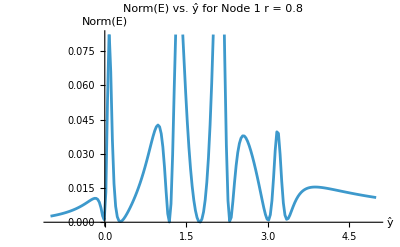

Evaluation time: 18.57671

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat1Array=Range[-1,5,0.03];
Δ1NormArray=Table[Δ1Norm[κ]/.{yHat->yHat1Array[[i]]},{i,1,Length@yHat1Array}];
ENorm1Array=Table[NIntegrate[Δ1NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat1Array}];

ListPlot[Transpose@{yHat1Array,ENorm1Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 1\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

### Node 0

```mathematica
𝔸0[κ_]=1+γ01 Cos[κ]+γ02 Cos[2 κ];
𝔹0[κ_]=γ01 Sin[κ]+γ02 Sin[2 κ];
ℂ0[κ_]=a00+a01 Cos[κ]+a02 Cos[2 κ]+a03 Cos[3 κ]+a04 Cos[4 κ];
𝔻0[κ_]=a01 Sin[κ]+a02 Sin[2 κ]+a03 Sin[3 κ]+a04 Sin[4 κ];
κBar0Re[κ_]=(𝔸0[κ]*𝔻0[κ]-𝔹0[κ]*ℂ0[κ])/((𝔸0[κ])^2+(𝔹0[κ])^2);
κBar0Im[κ_]=(-𝔸0[κ]*ℂ0[κ]-𝔹0[κ]*𝔻0[κ])/((𝔸0[κ])^2+(𝔹0[κ])^2);
κBar0Norm[κ_]=Abs[κBar0Re[κ]+I*κBar0Im[κ]];
```

```mathematica
Δ0Re[κ_]=(κ*((𝔸0[κ])^2+(𝔹0[κ])^2)-(𝔸0[κ]*𝔻0[κ]-𝔹0[κ]*ℂ0[κ]))^2;
Δ0Im[κ_]=(0*((𝔸0[κ])^2+(𝔹0[κ])^2)-(-𝔸0[κ]*ℂ0[κ]-𝔹0[κ]*𝔻0[κ]))^2;
Δ0Norm[κ_]=(κ-κBar0Norm[κ])^2;
```

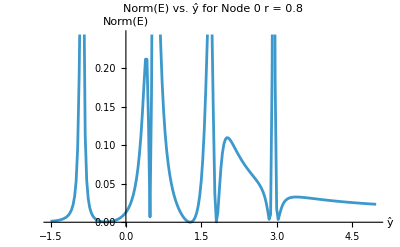

Evaluation time: 30.183909

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat0Array=Range[-1.5,5,0.03];
Δ0NormArray=Table[Δ0Norm[κ]/.{yHat->yHat0Array[[i]]},{i,1,Length@yHat0Array}];
ENorm0Array=Table[NIntegrate[Δ0NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat0Array}];

ListPlot[Transpose@{yHat0Array,ENorm0Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 0\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

## Spectral Function

### Node 1

```mathematica
Clear[yHat]
SF1Re[κ_,yHat_]=κBar1Re[κ];
SF1Im[κ_,yHat_]=κBar1Im[κ];
SF1Norm[κ_,yHat_]=κBar1Norm[κ];
```

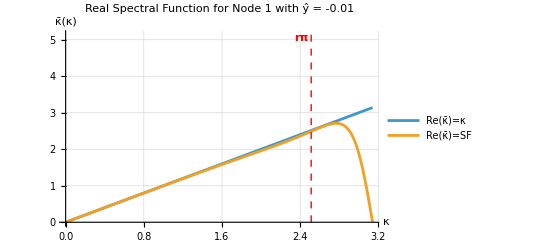

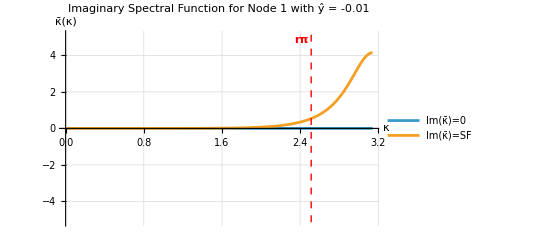

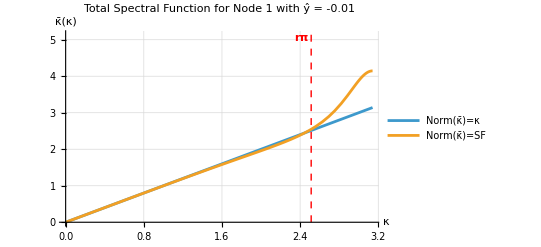

```mathematica
Clear[yHat]
r=0.8;
yHat1List={(*1*)-0.01,(*2*)0.29,(*3*)1.19,(*4*)1.76,(*5*)2.30,(*6*)3.02,(*7*)3.35};
yHat=yHat1List[[1]];
Plot[{κ,SF1Re[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
Plot[{0,SF1Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ,SF1Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
```

### Node 0

```mathematica
Clear[yHat]
SF0Re[κ_,yHat_]=κBar0Re[κ];
SF0Im[κ_,yHat_]=κBar0Im[κ];
SF0Norm[κ_,yHat_]=κBar0Norm[κ];
```

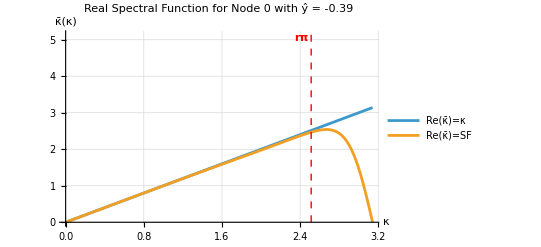

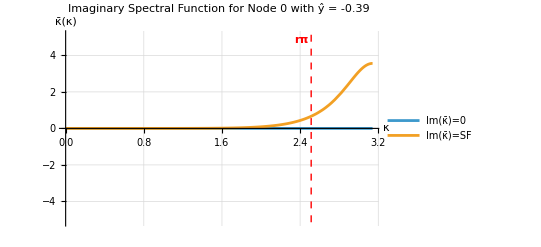

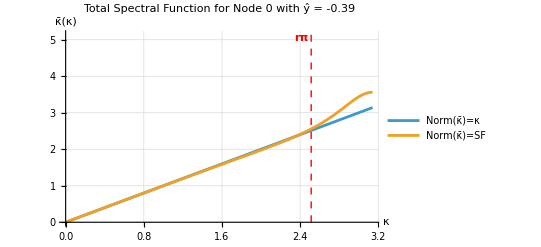

```mathematica
r=0.8;
yHat0List={(*1*)-0.39,(*2*)0.48,(*3*)1.29,(*4*)1.80,(*5*)2.85,(*6*)3.03};
yHat=yHat0List[[1]];
Plot[{κ,SF0Re[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
Plot[{0,SF0Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ,SF0Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
```

## Output Coefficients

### ŷ Definitions

```mathematica
Clear[yHat,yHat1,yHat0]

yHat1List={(*1*)-0.01,(*2*)0.29,(*3*)1.19,(*4*)1.76,(*5*)2.30,(*6*)3.02,(*7*)3.35};
yHat0List={(*1*)-0.39,(*2*)0.48,(*3*)1.29,(*4*)1.80,(*5*)2.85,(*6*)3.03};

yHat1=yHat1List[[1]];
yHat0=yHat0List[[1]];
```

### Define Coefficients

```mathematica
Clear[γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04]

{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04}/.bdCoeffs0)/.{yHat->yHat0};
```

### Luke Output

```mathematica
interiorLuke=interiorCoeffsC4/.{a1->a,a2->b};
boundaryLuke={α12->γ01val,β12->γ02val,α21->γ10val,α22->γ12val,β22->γ13val,a1->a00val,b1->a01val,c1->a02val,d1->a03val,e1->a04val,a2->a10val,b2->a11val,c2->a12val,d2->a13val,e2->a14val};
coeffLuke=Flatten[Join[interiorLuke,boundaryLuke]]
```

{α→0.536293,β→0.058317,a→0.689919,b→0.202345,α12→5.88725,β12→3.47404,α21→0.166413,α22→0.742201,β22→0.0752476,a1→-3.26564,b1→-3.22206,c1→5.83087,d1→0.705737,e1→-0.0488995,a2→-0.541114,b2→-0.624858,c2→0.88789,d2→0.279391,e2→-0.00130816}

### Nate Output

```mathematica
interiorNate=interiorCoeffsC4;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]]
```

{α→0.536293,β→0.058317,a1→0.689919,a2→0.202345,γ01→5.88725,γ02→3.47404,γ10→0.166413,γ12→0.742201,γ13→0.0752476,a00→-3.26564,a01→-3.22206,a02→5.83087,a03→0.705737,a04→-0.0488995,a10→-0.541114,a11→-0.624858,a12→0.88789,a13→0.279391,a14→-0.00130816}

## Eigenvalue Spectral Analysis

### Modified Boundary Coefficients for Eigenvalue Analysis

```mathematica
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,4}]/.coeffNate;
intBars={α21Bar->((α-β*γ01)/(1-β*γ02)/.coeffNate),α23Bar->(α/(1-β*γ02)/.coeffNate),β24Bar->(β/(1-β*γ02)/.coeffNate),
a1Bar->((-a1-β*a01)/(1-β*γ02)/.coeffNate),a2Bar->((-β*a02)/(1-β*γ02)/.coeffNate),a3Bar->((a1-β*a03)/(1-β*γ02)/.coeffNate),a4Bar->((a2-β*a04)/(1-β*γ02)/.coeffNate)};

barCoeffs=Join[LHSBars,RHSBars1,intBars]
```

{γ12Bar→8.08828,γ13Bar→3.7094,a11Bar→-4.37082,a12Bar→-4.0641,a13Bar→7.98335,a14Bar→0.33666}

### Build Modified Matrices (needs cleaning badly)

```mathematica
Clear[LHS,RHS]
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=2;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["α"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["α"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["β"<>ToString[i]<>ToString[j]<>"Bar"],

If[(i-2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}]

k=9; (*Size*)
MatrixForm@LHS[k]

MatrixForm@(LHS[k]/.coeffNate)/.barCoeffs
```

(1 | γ12Bar | γ13Bar | 0 | 0 | 0 | 0 | 0 | 0
α | 1 | α | β | 0 | 0 | 0 | 0 | 0
β | α | 1 | α | β | 0 | 0 | 0 | 0
0 | β | α | 1 | α | β | 0 | 0 | 0
0 | 0 | β | α | 1 | α | β | 0 | 0
0 | 0 | 0 | β | α | 1 | α | β | 0
0 | 0 | 0 | 0 | β | α | 1 | α | β
0 | 0 | 0 | 0 | 0 | γ13 | γ12 | 1 | γ10
0 | 0 | 0 | 0 | 0 | 0 | γ02 | γ01 | 1)

(1 | 8.08828 | 3.7094 | 0 | 0 | 0 | 0 | 0 | 0
0.536293 | 1 | 0.536293 | 0.058317 | 0 | 0 | 0 | 0 | 0
0.058317 | 0.536293 | 1 | 0.536293 | 0.058317 | 0 | 0 | 0 | 0
0 | 0.058317 | 0.536293 | 1 | 0.536293 | 0.058317 | 0 | 0 | 0
0 | 0 | 0.058317 | 0.536293 | 1 | 0.536293 | 0.058317 | 0 | 0
0 | 0 | 0 | 0.058317 | 0.536293 | 1 | 0.536293 | 0.058317 | 0
0 | 0 | 0 | 0 | 0.058317 | 0.536293 | 1 | 0.536293 | 0.058317
0 | 0 | 0 | 0 | 0 | 0.0752476 | 0.742201 | 1 | 0.166413
0 | 0 | 0 | 0 | 0 | 0 | 3.47404 | 5.88725 | 1)

```mathematica
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=2;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,

If[(i==2&&j==1),a1Bar,
If[(i==2&&j==2),a2Bar,
If[(i==2&&j==3),a3Bar,
If[(i==2&&j==4),a4Bar,

If[(i==k&&j==k),-a00,
If[(i==k&&j==k-1),-a01,
If[(i==k&&j==k-2),-a02,
If[(i==k&&j==k-3),-a03,
If[(i==k&&j==k-4),-a04,
If[(i==k-1&&j==k),-a10,
If[(i==k-1&&j==k-1),-a11,
If[(i==k-1&&j==k-2),-a12,
If[(i==k-1&&j==k-3),-a13,
If[(i==k-1&&j==k-4),-a14,


If[i-2==j,-a2,
If[i-1==j, -a1,
If[i==j, 0,
If[i+1==j, a1,
If[i+2==j,a2,
0]]]]]]]]]]]]]]]]]]]]]]]]
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}]

k=11; (*Size*)
MatrixForm@RHS[k]

MatrixForm@(RHS[k]/.coeffNate)/.barCoeffs
```

(a11Bar | a12Bar | a13Bar | a14Bar | 0 | 0 | 0 | 0 | 0 | 0 | 0
-a1 | 0 | a1 | a2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-a2 | -a1 | 0 | a1 | a2 | 0 | 0 | 0 | 0 | 0 | 0
0 | -a2 | -a1 | 0 | a1 | a2 | 0 | 0 | 0 | 0 | 0
0 | 0 | -a2 | -a1 | 0 | a1 | a2 | 0 | 0 | 0 | 0
0 | 0 | 0 | -a2 | -a1 | 0 | a1 | a2 | 0 | 0 | 0
0 | 0 | 0 | 0 | -a2 | -a1 | 0 | a1 | a2 | 0 | 0
0 | 0 | 0 | 0 | 0 | -a2 | -a1 | 0 | a1 | a2 | 0
0 | 0 | 0 | 0 | 0 | 0 | -a2 | -a1 | 0 | a1 | a2
0 | 0 | 0 | 0 | 0 | 0 | -a14 | -a13 | -a12 | -a11 | -a10
0 | 0 | 0 | 0 | 0 | 0 | -a04 | -a03 | -a02 | -a01 | -a00)

(-4.37082 | -4.0641 | 7.98335 | 0.33666 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.689919 | 0 | 0.689919 | 0.202345 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.202345 | -0.689919 | 0 | 0.689919 | 0.202345 | 0 | 0 | 0 | 0 | 0 | 0
0 | -0.202345 | -0.689919 | 0 | 0.689919 | 0.202345 | 0 | 0 | 0 | 0 | 0
0 | 0 | -0.202345 | -0.689919 | 0 | 0.689919 | 0.202345 | 0 | 0 | 0 | 0
0 | 0 | 0 | -0.202345 | -0.689919 | 0 | 0.689919 | 0.202345 | 0 | 0 | 0
0 | 0 | 0 | 0 | -0.202345 | -0.689919 | 0 | 0.689919 | 0.202345 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.202345 | -0.689919 | 0 | 0.689919 | 0.202345 | 0
0 | 0 | 0 | 0 | 0 | 0 | -0.202345 | -0.689919 | 0 | 0.689919 | 0.202345
0 | 0 | 0 | 0 | 0 | 0 | 0.00130816 | -0.279391 | -0.88789 | 0.624858 | 0.541114
0 | 0 | 0 | 0 | 0 | 0 | 0.0488995 | -0.705737 | -5.83087 | 3.22206 | 3.26564)

### Plot Eigenvalue Spectra

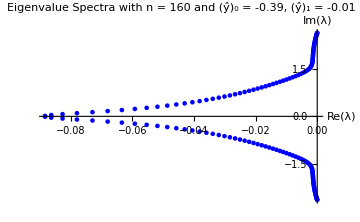

```mathematica
k=160;
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0/5,yHat1/5,1]]
```

## Dendro Output

### Hide

```mathematica
derivativeOrder=1;
interiorOrder=n;
totalBoundRows=numBoundaryRows;
freeInteriorParameters={};
freeBoundaryParameters={};
RHSInteriorList=RHSPars;
interiorParametersValues=interiorCoeffsC6/.{α->alpha,β->beta};
boundaryParametersValues=boundaryLuke/.{α12->gamma01,β12->gamma02,α21->gamma10,α22->gamma12,β22->gamma13,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14};
LHSBoundaryList={gamma01,gamma02,gamma10,gamma12,gamma13};
RHSBoundaryList={a00,a01,a02,a03,a04,a10,a11,a12,a13,a14};
(*Don't need to mess with these until we incorporate this procedure with James's filtering*)
filterIntCoeff;
filterBoundCoeff;
filterIntParam;
filterBoundParam;
filtering=False;
(*boundary={α12->γ01,β12->γ02,α21->γ10,α22->γ12,β22->γ13,β31->γ20,α31->γ21,α32->γ23,β32->γ24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};*)
```

```mathematica
(*****************Print coefficients in Dendro-GR Format*****************)
If[derivativeOrder==1,
LHSName="P1";
RHSName="Q1";
nth="1st";
coeffs="D_coeffs";
order="First",
If[derivativeOrder==2,
LHSName="P2";
RHSName="Q2";
nth="2nd";
coeffs="D_coeffs";
order="Second"]];
If[LHSBandCount==3,
LHSStructure="T",
If[LHSBandCount==5,
LHSStructure="P"]];

(*Convert Mathematica expression syntax to C/C++ expression syntax*)
convertToCCode[expr_]:=Module[{str},str=ToString[expr,InputForm];
(*Add ".0" to standalone integers but not to variables with numbers*)
(*Formatting adjustments to match C/C++ syntax*)str=StringReplace[str,{" "->"","*"->" * ","/"->" / ","+"->" + ","-"->" - ","^"->" ^ "}];
str]
(*Function to generate the line of C/C++ code to define the fixed variables*)
generateCAssignment[rule_]:=Module[{variable,expression,cCode,cAssignment},
variable=ToString[rule[[1]]];
expression=rule[[2]];
cCode=convertToCCode[expression];
cAssignment="double "<>variable<>" = "<>cCode<>";";
cAssignment
]






(*Initial Block*)
initialBlock=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order"}];
initialBlock2=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order","Filtered"}];

(*Free Parameters Block*)
freeParameters=Join[freeInteriorParameters,freeBoundaryParameters];
numFreePars=Length[freeParameters];
alphaPrint=StringReplace[generateCAssignment[Select[interiorParametersValues,#[[1]]===alpha&][[1]]],"alpha"->"alpha0"];
freeParPrints={};
If[numFreePars>0,
For[i=1,i<=numFreePars,i++,
AppendTo[freeParPrints,StringJoin[{"\n\t\tdouble ",ToString[freeParameters[[i]]]," = ",coeffs,"[",ToString[i],"];"}]]]]
freeParametersBlock=StringJoin[{"\t",alphaPrint,"\n\t\tdouble alpha = alpha0 + ",coeffs,"[0];",freeParPrints}];

(*Filter*)
freeParPrints2={};
freeParametersBlock2=StringJoin[{"\t","\n\t\tdouble alpha = ","F_coeffs","[0];",If[LHSBandCount==5,StringJoin["\n\t\tdouble beta = ","F_coeffs","[1];"],""]}];

(*Fixed Parameters Block*)
(*Create a list of the solved fixed parameters in C/C++ syntax*)
interiorParametersValues3=DeleteCases[interiorParametersValues,Rule[alpha,_]];
interiorParameterPrints=Table[
generateCAssignment[interiorParametersValues3[[i]]],
{i,1,Length[interiorParametersValues]-1}
];
boundaryParameterPrints=Table[
generateCAssignment[boundaryParametersValues[[i]]],
{i,1,Length[boundaryParametersValues]}
];
(*For filtered coefficients*)
interiorParameterPrints2=Table[
generateCAssignment[filterIntCoeff[[i]]],
{i,1,Length[filterIntCoeff]}
];
boundaryParameterPrints2=Table[
generateCAssignment[filterBoundCoeff[[i]]],
{i,1,Length[filterBoundCoeff]}
];
(*Print the coefficients in a single block of text rather than individual lines*)
fixedParametersBlockD=StringJoin["\t\t",Riffle[Join[interiorParameterPrints,boundaryParameterPrints],"\n\t\t"]];
fixedParametersBlockD2=StringJoin["\t\t",Riffle[Join[interiorParameterPrints2,boundaryParameterPrints2],"\n\t\t"]];

(*Structure Block*)
(*LHS Boundary*)
PDiagBoundary="";
LHSRowList=ToExpression[GatherBy[LHSBoundaryList,StringDrop[ToString[#],5]~StringTake~1&]];
For[i=1,i<=Length[LHSRowList],i++,
If[i==1,PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t","{1.0, ",StringDrop[ToString[LHSRowList[[i]]],1],","]];
If[i==2,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1}]],1],","]]];
If[i==3,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{","0.0, ",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t",StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
If[i>=4,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],StringDrop[StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
];
(*LHS Filter Boundary*)
RDiagBoundary="";
For[i=1,i<=Length@filterBoundParam,i++,
If[i==1,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha, beta},"]];
];
If[i==2,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha 1.0, alpha, beta},"]];
];
If[i>=3,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],"alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],"beta, alpha, 1.0, alpha, beta},"]];
];
];

(*LHS Interior*)
If[LHSBandCount==3,
PDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
PDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];
(*LHS Filter Interior*)
If[LHSBandCount==3,
RDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
RDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];

(*RHS Boundary*)
QDiagBoundary="";
RHSRowList=ToExpression[GatherBy[RHSBoundaryList,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList],i++,QDiagBoundary=StringJoin[QDiagBoundary,"\n\t\t\t",ToString[RHSRowList[[i]]],","]]
(*RHS Filter Boundary*)
SDiagBoundary="";
RHSRowList2=ToExpression[GatherBy[filterBoundParam,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList2],i++,SDiagBoundary=StringJoin[SDiagBoundary,"\n\t\t\t",ToString[RHSRowList2[[i]]]]]

(*RHS Interior*)
QDiagInterior={};
len=(2*Length[RHSInteriorList]+1);
If[derivativeOrder==1,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[-RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"0.0"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]
],
If[derivativeOrder==2,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[-RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"t1"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]]]]

(*RHS Filter Interior*)
SDiagInterior={};
newFilterIntParam=Drop[filterIntParam,1];
len=(2*Length[newFilterIntParam]+1);
For[i=1,i<=len,i++,
If[i<=Length[newFilterIntParam],PrependTo[SDiagInterior,ToString[newFilterIntParam[[i]]]<>"/"<>ToString[2]<>".0"]];
If[i==(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,"a0"]];
If[i>(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,ToString[newFilterIntParam[[i-Length[newFilterIntParam]-1]]]<>"/"<>ToString[2]<>".0"]]
]


PDiagBoundaryStr=StringDrop[StringDrop[PDiagBoundary,1],-1];
PDiagInteriorStr=StringDrop[StringDrop[PDiagInterior,1],-1];
RDiagBoundaryStr=StringDrop[StringDrop[RDiagBoundary,1],-1];
RDiagInteriorStr=StringDrop[StringDrop[RDiagInterior,1],-1];
QDiagBoundaryStr=StringDrop[StringDrop[QDiagBoundary,1],-1];
QDiagInteriorStr=StringDrop[StringDrop[ToString[QDiagInterior],1],-1];
SDiagBoundaryStr=StringDrop[SDiagBoundary,1];
SDiagInteriorStr=StringDrop[StringDrop[ToString[SDiagInterior],1],-1];

(*Subscript[t, 1] is the middle RHS Interior Coefficient for Second Derivatives*)
t1List={};
For[i=1,i<=Length[RHSInteriorList],i++,
AppendTo[t1List,ToString[RHSInteriorList[[i]]]<>"/"<>ToString[i^2]<>".0"]
];
If[derivativeOrder==1,
t1="",
If[derivativeOrder==2,
t1=StringJoin["-2.0 * ("<>StringDrop[StringDrop[ToString[t1List],1],-1]<>")"]]];


If[filtering,
filterFinalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock2,"(\n","\tconst std::vector<double>& ","F_coeffs",") {\n","\t",freeParametersBlock2,"\n\n",fixedParametersBlockD2,"\n\n","\t\t// boundary elements for R matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","R","DiagBoundary{\n",RDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for R matrix for ",nth," derivative\n","\t\tstd::vector<double> ","R","DiagInterior{\n","\t\t\t",RDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for S matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","S","DiagBoundary\n",SDiagBoundaryStr,"\n","\t\t;\n\n","\t\t// diagonal elements for S matrix for ",nth," derivative\n","\t\tstd::vector<double> ","S","DiagInterior{\n","\t\t\t",SDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t","R","DiagInterior, ","S","DiagInterior, ","S","DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}"}];
]

finalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock,"(\n","\tconst std::vector<double>& ",coeffs,") {\n","\t",freeParametersBlock,"\n\n",fixedParametersBlockD,"\n\n","\t\t// boundary elements for P matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",LHSName,"DiagBoundary{\n",PDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for P matrix for ",nth," derivative\n","\t\tstd::vector<double> ",LHSName,"DiagInterior{\n","\t\t\t",PDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",RHSName,"DiagBoundary{\n",QDiagBoundaryStr,"\n","\t\t};\n\n",If[derivativeOrder==1,t1,If[derivativeOrder==2,"\t\tdouble t1 = "<>t1<>";\n"]],"\t\t// diagonal elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<double> ",RHSName,"DiagInterior{\n","\t\t\t",QDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t",LHSName,"DiagInterior, ",LHSName,"DiagBoundary, ",RHSName,"DiagInterior, ",RHSName,"DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}",If[filtering,"\n\n"<>filterFinalBlock,""]}];
```

GatherBy::list: List expected at position 1 in GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&].

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Drop::drop: Cannot drop positions 1 through 1 in filterIntParam.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

StringDrop::drop: Cannot drop positions 1 through 1 in "".

### Show

```mathematica
outExt="h";
(*Print header*)
Print[Style["Dendro-Ready Coefficients (Copied to clipboard):",Bold,FontSize->24]];
Print[finalBlock];
(*Copy the block of text to the user's clipboard*)
CopyToClipboard[finalBlock];

(*Save to output file*)
fileName=StringJoin[{"BYU_C6","_yHat0_",ToString[yHat0],"_yHat1_",ToString[yHat1],".",outExt}];
Export[fileName,finalBlock,"Text"];
Print[StringJoin[{"Saved to file: ",fileName}]]
```

Dendro-Ready Coefficients (Copied to clipboard):

MatrixDiagonalEntries* BYUDerivsP6R2DiagonalsFirstOrder(
	const std::vector<double>& D_coeffs) {
		double alpha0 = 0.4963477370017426;
		double alpha = alpha0 + D_coeffs[0];

		double beta = 0.04075360091710232;
		double a1 = 0.723439643221641;
		double a2 = 0.15683084734860173;
		double gamma01 =  - 3.531337876522152;
		double gamma02 =  - 11.2970068147929;
		double gamma10 = 0.16123050668544858;
		double gamma12 = 0.4741493035858441;
		double gamma13 =  - 0.038978437534430796;
		double a00 =  - 2.1419160987708987;
		double a01 = 14.474119440299228;
		double a02 =  - 8.297006814789217;
		double a03 =  - 4.4323356049301275;
		double a04 = 0.397139078188711;
		double a10 =  - 0.5431362438346228;
		double a11 =  - 0.5240000610825333;
		double a12 = 1.0747761362453676;
		double a13 =  - 0.0014084866408688862;
		double a14 =  - 0.006231344687109832;

		// boundary elements for P matrix for 1st derivative
		std::vector<std::vector<double>> P1DiagBoundary{
			{1.0, gamma01, gamma02},
			{gamma10, 1.0, gamma12, gamma13}
		};

		// diagonal elements for P matrix for 1st derivative
		std::vector<double> P1DiagInterior{
			beta, alpha, 1.0, alpha, beta
		};

		// boundary elements for Q matrix for 1st derivative
		std::vector<std::vector<double>> Q1DiagBoundary{
			{a00, a01, a02, a03, a04},
			{a10, a11, a12, a13, a14}
		};

		// diagonal elements for Q matrix for 1st derivative
		std::vector<double> Q1DiagInterior{
			-a2, -a1, 0.0, a1, a2
		};

		// store the entries for matrix creation
		MatrixDiagonalEntries* diagEntries = new
			MatrixDiagonalEntries{
				P1DiagInterior, P1DiagBoundary, Q1DiagInterior, Q1DiagBoundary
			};
		return diagEntries;
	}

Saved to file: BYU_C6_yHat0_0.21_yHat1_1.17.h

# P6 (A6) Scheme

## Initialization

The matrix system of equations we are solving for this scheme is:
	P=(1
γ_10
γ_20
0
0
0
0 γ_01
1
γ_21
β
0
0
0 γ_02
γ_12
1
α
γ_24
0
0 0
γ_13
γ_23
1
γ_23
γ_13
0 0
0
γ_24
α
1
γ_12
γ_02 0
0
0
β
γ_21
1
γ_01 0
0
0
0
γ_20
γ_10
1)
	Q=(a_00
a_10
a_20
-a_3
-a_26
-a_16
-a_06 a_01
a_11
a_21
-a_2
-a_25
-a_15
-a_05 a_02
a_12
a_22
-a_1
-a_24
-a_14
-a_04 a_03
a_13
a_23
0
-a_23
-a_13
-a_03 a_04
a_14
a_24
a_1
-a_22
-a_12
-a_02 a_05
a_15
a_25
a_2
-a_21
-a_11
-a_01 a_06
a_16
a_26
a_3
-a_20
-a_10
-a_00)

```mathematica
(*From KimInteriorOptimization.nb, one day to be merged with this one. Or I could DumpSave[] in that notebook and then Get[] here.*)
(*Note that these are found with the P6 Scheme NEW header in that notebook*)
interiorCoeffsA6={α->0.5573223518365282,β->0.076203478481807,a1->0.6694377318500324,a2->0.22598218207734894,a3->0.0040412447712016904};

(*If you have the .mx files in the same directory as this notebook, these will let you skip the long computation of defining bdCoeffs under the "Solve for Boundary Coefficients" section*)
Get["A6_interiorCoeffs.mx"];
Get["A6_bdCoeffs2.mx"];
Get["A6_bdCoeffs1.mx"];
Get["A6_bdCoeffs0.mx"];
```

## General Extrapolation Polynomial

For the P6 (A6) scheme, we have:
	LHSBandCount = 5
	n = 6
	freeInteriorPars = 2
	yDeriv = 10

```mathematica
(*User chooses these parameters, the rest is calculated from these*)
LHSBandCount=5; (*3 for tridiagonal, 5 for pentadiagonal*)
n=6; (*order of the scheme*)
freeInteriorPars=2; (*number of free parameters used for Kim's optimization on the interior*)
yDeriv=8; (*(d^n P)/dx^n(ŷ)=0 from Kim 2024 Eq. 10, this is n in that equation*) (*provide constraints on what the user can choose for this. Upper bound should be polynomialorder to prevent the matrix from being singular, and lower bound should be order·2 I think.*)

LHSPars=Switch[LHSBandCount,3,{α},5,{α,β}];
RHSPars=Table[ToExpression[StringJoin["a",ToString[i]]],{i,1,Ceiling[n/2]-Length@LHSPars+freeInteriorPars}];
numBoundaryRows=Length@RHSPars;
fOrder=(2*Length@RHSPars)+1;
fpOrder=LHSBandCount+(numBoundaryRows-(LHSBandCount-1)/2);
PolynomialOrder=fOrder+fpOrder;


rowf1=Join[{1},Table[0,{i,1,PolynomialOrder}]];
rowf=Table[Table[i^j,{j,0,PolynomialOrder}],{i,1,fOrder-1}];
rowfp1=Join[{0,1},Table[0,{i,2,PolynomialOrder}]];
rowfp=Table[Table[j i^(j-1),{j,0,PolynomialOrder}],{i,1,fpOrder-1}];
rowyHat=Join[Table[0,{i,1,yDeriv}],Table[(i!)/((i-yDeriv)!) yHat^(i-yDeriv),{i,yDeriv,PolynomialOrder}]];

matf=PrependTo[rowf,rowf1];
matfp=PrependTo[rowfp,rowfp1];
matfCombined=Join[matf,matfp];
LMat=AppendTo[matfCombined,rowyHat];

pVec=Table[ToExpression[StringJoin["p",ToString[i]]],{i,0,PolynomialOrder}];
fVec=Join[Table[ToExpression[StringJoin["f",ToString[i]]],{i,0,fOrder-1}],Table[ToExpression[StringJoin["fp",ToString[i]]],{i,0,fpOrder-1}],{0}];

pCoeffs=Solve[LMat.pVec==fVec,pVec][[1]];

yHatSingularities=(Transpose@Solve[Det[LMat]==0,yHat])[[1]]//N;
P[x_]=Total[Table[pVec[[i+1]]*x^i,{i,0,PolynomialOrder}]]/.pCoeffs;

Print["System:\n",MatrixForm[LMat]," ",MatrixForm[pVec]," = ",MatrixForm[fVec]]
Print["Singularities:\n",MatrixForm[yHatSingularities]]
(*Print["Coefficients:\n",MatrixForm[pCoeffs]]*)
```

System:
(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 4 | 8 | 16 | 32 | 64 | 128 | 256 | 512 | 1024 | 2048 | 4096 | 8192
1 | 3 | 9 | 27 | 81 | 243 | 729 | 2187 | 6561 | 19683 | 59049 | 177147 | 531441 | 1594323
1 | 4 | 16 | 64 | 256 | 1024 | 4096 | 16384 | 65536 | 262144 | 1048576 | 4194304 | 16777216 | 67108864
1 | 5 | 25 | 125 | 625 | 3125 | 15625 | 78125 | 390625 | 1953125 | 9765625 | 48828125 | 244140625 | 1220703125
1 | 6 | 36 | 216 | 1296 | 7776 | 46656 | 279936 | 1679616 | 10077696 | 60466176 | 362797056 | 2176782336 | 13060694016
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
0 | 1 | 4 | 12 | 32 | 80 | 192 | 448 | 1024 | 2304 | 5120 | 11264 | 24576 | 53248
0 | 1 | 6 | 27 | 108 | 405 | 1458 | 5103 | 17496 | 59049 | 196830 | 649539 | 2125764 | 6908733
0 | 1 | 8 | 48 | 256 | 1280 | 6144 | 28672 | 131072 | 589824 | 2621440 | 11534336 | 50331648 | 218103808
0 | 1 | 10 | 75 | 500 | 3125 | 18750 | 109375 | 625000 | 3515625 | 19531250 | 107421875 | 585937500 | 3173828125
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 40320 | 362880 yHat | 1814400 yHat^2 | 6652800 yHat^3 | 19958400 yHat^4 | 51891840 yHat^5) (p0
p1
p2
p3
p4
p5
p6
p7
p8
p9
p10
p11
p12
p13) = (f0
f1
f2
f3
f4
f5
f6
fp0
fp1
fp2
fp3
fp4
fp5
0)

Singularities:
(yHat→1.23232
yHat→2.01136
yHat→2.75838
yHat→3.50832
yHat→4.33577)

## Solve for Boundary Coefficients

Goal:
	Solve a system of equations for bdCoeffsList2 in terms of the optimization free parameter ŷ
Variables:
	fVars2: List of f_i and f_i' variables that will appear in the shifted stencil for Node 2
	bdCoeffsList2: List of boundary coefficients that will appear in the shifted stencil for Node 2
	schemeShifted: The shifted scheme for Node 2
	schemeCentered: The centered scheme for Node 2 in terms of the extrapolation polynomial P(x)
		NOTE: To make the Collect[] process easier, we write these schemes as LHS-RHS=0 rather than the usual LHS=RHS.
	schemeNode3: The scheme for Node 3, which only depends on interiorCoeffsP6
	SOLfp5: The solution to Node 3’s scheme equation for f_5' in terms of fVars2
	eq: Scheme equation where the coefficient terms from schemeCentered and schemeShifted are set equal to each other
	coeffEqs2: System of equations with each of the coefficient terms equal to each other
	bdCoeffs2: Solution to the system of equations for bdCoeffsList2 in terms of ŷ
Process:
	1. Initialize the necessary equations.
	2. We want schemeShifted and schemeCentered to both be in terms of fVars2 with some coefficients. Due to the presence of P(x) terms in schemeCentered, it is in terms of fVars2 as well as f_5'. We eliminate the dependence on f_5' by using Node 3’s scheme to solve for f_5' in terms of fVars2.
	3. Now that schemeShifted and schemeCentered are both in terms of fVars2, we construct a system of equations by equating the coefficient in front of each term of fVars2 in schemeCentered with the corresponding coefficient in front of the same term in schemeShifted.
	4. We solve this system of equations for bdCoeffsList2 in terms of interiorCoeffsP4 (which are substituted in) and the optimization free parameter ŷ.
		NOTE: In the standard scheme approach, we set γ_22=1 to ensure the main diagonal of the LHS matrix is all 1’s. When solving this system of equations, we must include γ_22 so that bdCoeffsList2 and fVars2 have the same length since this allows us to find a unique solution to the system of equations. We apply the normal condition later on.
	5. OPTIONAL: We may save the variable bdCoeffs2 to a binary file in the current directory. This is helpful to avoid having to run this process multiple times, as it can become computationally expensive.
Differences:
	For Node 1 and Node 0, the entire process translates directly with a few changes. fVars, bdCoeffsList, schemeShifted, and schemeCentered all change, as we are considering the scheme for a different row, but the equations have the same structure. The main notable difference is in Step 2; In addition to substituting in the solution from Node 3 for f_5' in terms of the other fVars, we must also do the same for f_4' (Nodes 1 and 0) and f_3' (Node 0) using Nodes 2 and 1, respectively.

### Node 2

```mathematica
(*----------STEP 1----------*)
fVars2={fp0,fp1,fp2,fp3,fp4,f0,f1,f2,f3,f4,f5,f6};
bdCoeffsList2={γ20,γ21,γ22,γ23,γ24,a20,a21,a22,a23,a24,a25,a26};
schemeShifted=γ20 fp0+γ21 fp1+γ22 fp2+γ23 fp3+γ24 fp4-(a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6); (*==0*)
schemeCentered=β fp0+α fp1+fp2+α fp3+β fp4-(-a3 P[-1]-a2 f0-a1 f1+a1 f3+a2 f4+a3 f5); (*==0*)

(*----------STEP 2----------*)
schemeNode3=β fp1+α fp2+fp3+α fp4+β fp5==-a3 f0-a2 f1-a1 f2+a1 f4+a2 f5+a3 f6;
SOLfp5=Solve[schemeNode3,fp5][[1,1]]/.interiorCoeffsA6;
schemeCentered=schemeCentered/.SOLfp5;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars2];

(*----------STEP 4----------*)
coeffEqs2=Table[Coefficient[eq,fVars2[[i]]]==0,{i,1,Length@fVars2}];
bdCoeffs2=(Solve[coeffEqs2,bdCoeffsList2][[1]])/.interiorCoeffsA6;

(*----------STEP 5----------*)
DumpSave["A6_bdCoeffs2.mx","Global`bdCoeffs2"]
```

{Global`bdCoeffs2}

### Node 1

```mathematica
(*----------STEP 1----------*)
fVars1={fp0,fp1,fp2,fp3,f0,f1,f2,f3,f4,f5,f6};
bdCoeffsList1={γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14,a15,a16};
schemeShifted=γ10 fp0+γ11 fp1+γ12 fp2+γ13 fp3-(a10 f0+a11 f1+a12 f2+a13 f3+a14 f4+a15 f5+a16 f6); (*==0*)
schemeCentered=β P'[-1]+α fp0+fp1+α fp2+β fp3-(-a3 P[-2]-a2 P[-1]-a1 f0+a1 f2+a2 f3+a3 f4); (*==0*)

(*----------STEP 2----------*)
schemeNode3=β fp1+α fp2+fp3+α fp4+β fp5==-a3 f0-a2 f1-a1 f2+a1 f4+a2 f5+a3 f6;
schemeNode2=γ20 fp0+γ21 fp1+γ22 fp2+γ23 fp3+γ24 fp4==a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6;

SOLfp5=Solve[schemeNode3,fp5][[1,1]]/.interiorCoeffsA6;
SOLfp4=Solve[schemeNode2,fp4][[1,1]]/.bdCoeffs2;
schemeCentered=schemeCentered/.SOLfp5/.SOLfp4;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars1];

(*----------STEP 4----------*)
coeffEqs1=Table[Coefficient[eq,fVars1[[i]]]==0,{i,1,Length@fVars1}];
bdCoeffs1=(Solve[coeffEqs1,bdCoeffsList1][[1]])/.interiorCoeffsA6;

(*----------STEP 5----------*)
DumpSave["A6_bdCoeffs1.mx","Global`bdCoeffs1"]
```

{Global`bdCoeffs1}

### Node 0

```mathematica
(*----------STEP 1----------*)
fVars0={fp0,fp1,fp2,f0,f1,f2,f3,f4,f5,f6};
bdCoeffsList0={γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06};
schemeShifted=γ00 fp0+γ01 fp1+γ02 fp2-(a00 f0+a01 f1+a02 f2+a03 f3+a04 f4+a05 f5+a06 f6); (*==0*)
schemeCentered=β P'[-2]+α P'[-1]+fp0+α fp1+β fp2-(-a3 P[-3]-a2 P[-2]-a1 P[-1]+a1 f1+a2 f2+a3 f3); (*==0*)

(*----------STEP 2----------*)
schemeNode3=β fp1+α fp2+fp3+α fp4+β fp5==-a3 f0-a2 f1-a1 f2+a1 f4+a2 f5+a3 f6;
schemeNode2=γ20 fp0+γ21 fp1+γ22 fp2+γ23 fp3+γ24 fp4==a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6;
schemeNode1=γ10 fp0+γ11 fp1+γ12 fp2+γ13 fp3==a10 f0+a11 f1+a12 f2+a13 f3+a14 f4+a15 f5+a16 f6;

SOLfp5=Solve[schemeNode3,fp5][[1,1]]/.interiorCoeffsA6;
SOLfp4=Solve[schemeNode2,fp4][[1,1]]/.bdCoeffs2;
SOLfp3=Solve[schemeNode1,fp3][[1,1]]/.bdCoeffs1;
schemeCentered=schemeCentered/.SOLfp5/.SOLfp4/.SOLfp3;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars0];

(*----------STEP 4----------*)
coeffEqs0=Table[Coefficient[eq,fVars0[[i]]]==0,{i,1,Length@fVars0}];
bdCoeffs0=(Solve[coeffEqs0,bdCoeffsList0][[1]])/.interiorCoeffsA6;

(*----------STEP 5----------*)
DumpSave["A6_bdCoeffs0.mx","Global`bdCoeffs0"]
```

{Global`bdCoeffs0}

## Optimize ŷ

### Set and Normalize Coefficients

We normalize the coefficients so that the main diagonal of the LHS matrix is all 1’s, but we leave the coefficients in terms of the optimization free parameter ŷ so that we can optimize over it.

```mathematica
Clear[γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26]
Clear[γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06]

{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}=1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2;
{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}=1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1;
{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}=1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0;
```

### Node 2

```mathematica
𝔸2[κ_]=γ20+γ21 Cos[κ]+Cos[2 κ]+γ23 Cos[3 κ]+γ24 Cos[4 κ];
𝔹2[κ_]=γ21 Sin[κ]+Sin[2 κ]+γ23 Sin[3 κ]+γ24 Sin[4 κ];
ℂ2[κ_]=a20+a21 Cos[κ]+a22 Cos[2 κ]+a23 Cos[3 κ]+a24 Cos[4 κ]+a25 Cos[5 κ]+a26 Cos[6 κ];
𝔻2[κ_]=a21 Sin[κ]+a22 Sin[2 κ]+a23 Sin[3 κ]+a24 Sin[4 κ]+a25 Sin[5 κ]+a26 Sin[6 κ];
κBar2Re[κ_]=(𝔸2[κ]*𝔻2[κ]-𝔹2[κ]*ℂ2[κ])/((𝔸2[κ])^2+(𝔹2[κ])^2);
κBar2Im[κ_]=(-𝔸2[κ]*ℂ2[κ]-𝔹2[κ]*𝔻2[κ])/((𝔸2[κ])^2+(𝔹2[κ])^2);
κBar2Norm[κ_]=Abs[κBar2Re[κ]+I*κBar2Im[κ]];
```

```mathematica
Δ2Re[κ_]=(κ*((𝔸2[κ])^2+(𝔹2[κ])^2)-(𝔸2[κ]*𝔻2[κ]-𝔹2[κ]*ℂ2[κ]))^2;
Δ2Im[κ_]=(0*((𝔸2[κ])^2+(𝔹2[κ])^2)-(-𝔸2[κ]*ℂ2[κ]-𝔹2[κ]*𝔻2[κ]))^2;
Δ2Norm[κ_]=(κ-κBar2Norm[κ])^2;
```

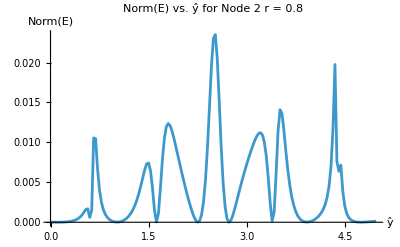

Evaluation time: 12.590658

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat2Array=Range[0,5,0.03];
Δ2NormArray=Table[Δ2Norm[κ]/.{yHat->yHat2Array[[i]]},{i,1,Length@yHat2Array}];
ENorm2Array=Table[NIntegrate[Δ2NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat2Array}];

ListPlot[Transpose@{yHat2Array,ENorm2Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 2\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

### Node 1

```mathematica
𝔸1[κ_]=γ10+Cos[κ]+γ12 Cos[2 κ]+γ13 Cos[3 κ];
𝔹1[κ_]=Sin[κ]+γ12 Sin[2 κ]+γ13 Sin[3 κ];
ℂ1[κ_]=a10+a11 Cos[κ]+a12 Cos[2 κ]+a13 Cos[3 κ]+a14 Cos[4 κ]+a15 Cos[5 κ]+a16 Cos[6 κ];
𝔻1[κ_]=a11 Sin[κ]+a12 Sin[2 κ]+a13 Sin[3 κ]+a14 Sin[4 κ]+a15 Sin[5 κ]+a16 Sin[6 κ];
κBar1Re[κ_]=(𝔸1[κ]*𝔻1[κ]-𝔹1[κ]*ℂ1[κ])/((𝔸1[κ])^2+(𝔹1[κ])^2);
κBar1Im[κ_]=(-𝔸1[κ]*ℂ1[κ]-𝔹1[κ]*𝔻1[κ])/((𝔸1[κ])^2+(𝔹1[κ])^2);
κBar1Norm[κ_]=Abs[κBar1Re[κ]+I*κBar1Im[κ]];
```

```mathematica
Δ1Re[κ_]=(κ*((𝔸1[κ])^2+(𝔹1[κ])^2)-(𝔸1[κ]*𝔻1[κ]-𝔹1[κ]*ℂ1[κ]))^2;
Δ1Im[κ_]=(0*((𝔸1[κ])^2+(𝔹1[κ])^2)-(-𝔸1[κ]*ℂ1[κ]-𝔹1[κ]*𝔻1[κ]))^2;
Δ1Norm[κ_]=(κ-κBar1Norm[κ])^2;
```

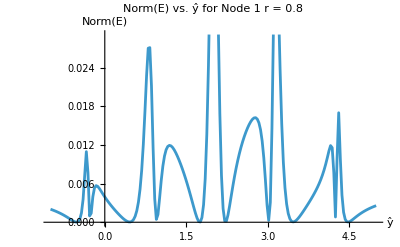

Evaluation time: 30.940869

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat1Array=Range[-1,5,0.03];
Δ1NormArray=Table[Δ1Norm[κ]/.{yHat->yHat1Array[[i]]},{i,1,Length@yHat1Array}];
ENorm1Array=Table[NIntegrate[Δ1NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat1Array}];

ListPlot[Transpose@{yHat1Array,ENorm1Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 1\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

### Node 0

```mathematica
𝔸0[κ_]=1+γ01 Cos[κ]+γ02 Cos[2 κ];
𝔹0[κ_]=γ01 Sin[κ]+γ02 Sin[2 κ];
ℂ0[κ_]=a00+a01 Cos[κ]+a02 Cos[2 κ]+a03 Cos[3 κ]+a04 Cos[4 κ]+a05 Cos[5 κ]+a06 Cos[6 κ];
𝔻0[κ_]=a01 Sin[κ]+a02 Sin[2 κ]+a03 Sin[3 κ]+a04 Sin[4 κ]+a05 Sin[5 κ]+a06 Sin[6 κ];
κBar0Re[κ_]=(𝔸0[κ]*𝔻0[κ]-𝔹0[κ]*ℂ0[κ])/((𝔸0[κ])^2+(𝔹0[κ])^2);
κBar0Im[κ_]=(-𝔸0[κ]*ℂ0[κ]-𝔹0[κ]*𝔻0[κ])/((𝔸0[κ])^2+(𝔹0[κ])^2);
κBar0Norm[κ_]=Abs[κBar0Re[κ]+I*κBar0Im[κ]];
```

```mathematica
Δ0Re[κ_]=(κ*((𝔸0[κ])^2+(𝔹0[κ])^2)-(𝔸0[κ]*𝔻0[κ]-𝔹0[κ]*ℂ0[κ]))^2;
Δ0Im[κ_]=(0*((𝔸0[κ])^2+(𝔹0[κ])^2)-(-𝔸0[κ]*ℂ0[κ]-𝔹0[κ]*𝔻0[κ]))^2;
Δ0Norm[κ_]=(κ-κBar0Norm[κ])^2;
```

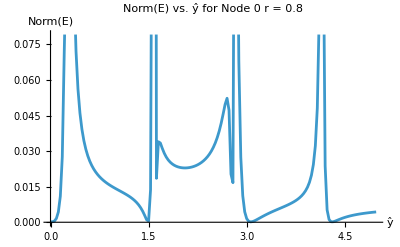

Evaluation time: 318.306116

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat0Array=Range[0,5,0.03];
Δ0NormArray=Table[Δ0Norm[κ]/.{yHat->yHat0Array[[i]]},{i,1,Length@yHat0Array}];
ENorm0Array=Table[NIntegrate[Δ0NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat0Array}];

ListPlot[Transpose@{yHat0Array,ENorm0Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 0\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

## Spectral Function

### Node 2

```mathematica
Clear[yHat]
SF2Re[κ_,yHat_]=κBar2Re[κ];
SF2Im[κ_,yHat_]=κBar2Im[κ];
SF2Norm[κ_,yHat_]=κBar2Norm[κ];
```

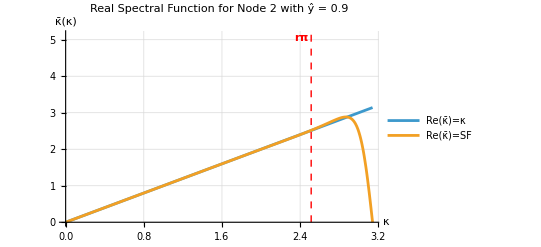

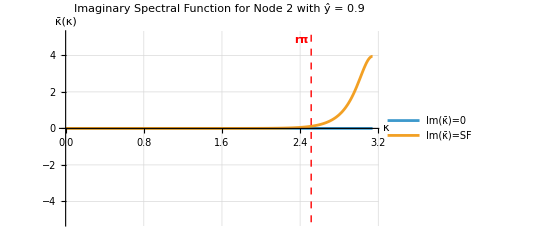

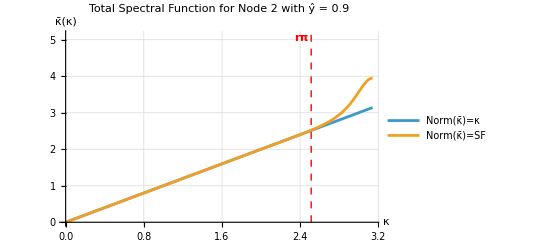

```mathematica
r=0.8;
yHat2List={(*1*)0.90,(*2*)1.41,(*3*)2.25,(*4*)2.73,(*5*)3.60,(*6*)3.99};
yHat2List={(*1*)0.45,(*2*)0.99,(*3*)1.59,(*4*)2.13,(*5*)2.88,(*6*)3.36,(*7*)4.02,(*8*)4.41};
yHat2List={(*1*)0.12,(*2*)0.60,(*3*)1.02,(*4*)1.62,(*5*)2.25,(*6*)2.73,(*7*)3.39,(*8*)3.93,(*9*)4.74};
yHat=yHat2List[[1]];
Plot[{κ,SF2Re[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
Plot[{0,SF2Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ,SF2Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
```

### Node 1

```mathematica
Clear[yHat]
SF1Re[κ_,yHat_]=κBar1Re[κ];
SF1Im[κ_,yHat_]=κBar1Im[κ];
SF1Norm[κ_,yHat_]=κBar1Norm[κ];
```

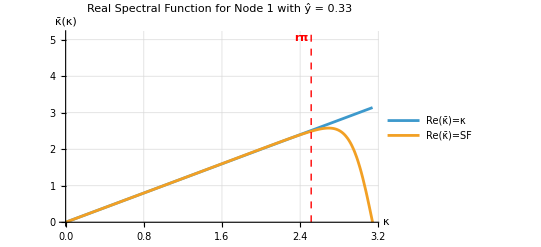

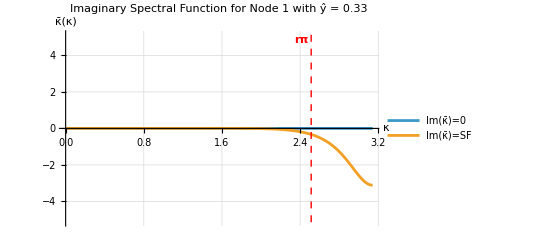

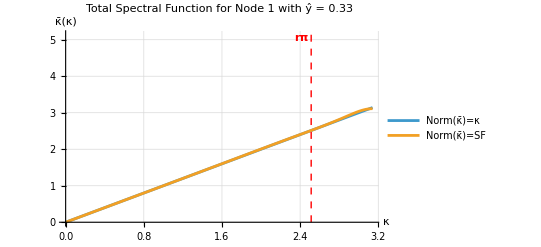

```mathematica
Clear[yHat]
r=0.8;
yHat1List={(*1*)0.33,(*2*)0.69,(*3*)1.77,(*4*)2.19,(*5*)3.30,(*6*)3.63};
yHat1List={(*1*)-0.16,(*2*)0.17,(*3*)1.07,(*4*)1.52,(*5*)2.45,(*6*)2.87,(*7*)3.80,(*8*)4.10};
yHat1List={(*1*)-0.52,(*2*)-0.28,(*3*)0.47,(*4*)0.95,(*5*)1.76,(*6*)2.21,(*7*)3.02,(*8*)3.47,(*9*)4.25,(*10*)4.49};
yHat=yHat1List[[1]];
Plot[{κ,SF1Re[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
Plot[{0,SF1Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ,SF1Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
```

### Node 0

```mathematica
Clear[yHat]
SF0Re[κ_,yHat_]=κBar0Re[κ];
SF0Im[κ_,yHat_]=κBar0Im[κ];
SF0Norm[κ_,yHat_]=κBar0Norm[κ];
```

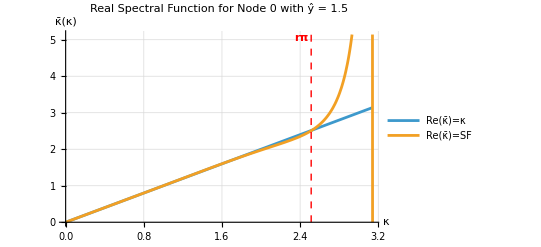

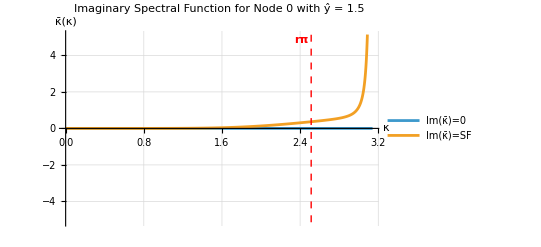

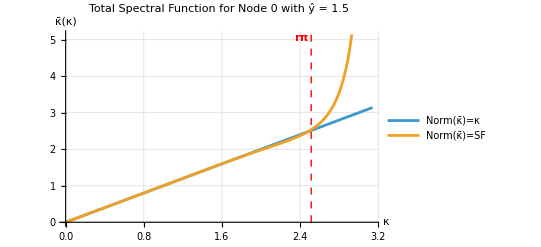

```mathematica
r=0.8;
yHat0List={(*1*)1.50,(*2*)1.59,(*3*)3.12,(*4*)3.27};
yHat0List={(*1*)0.72,(*2*)2.19,(*3*)2.37,(*4*)3.84};
yHat0List={(*1*)0.03,(*2*)1.50,(*3*)3.06,(*4*)4.32};
yHat=yHat0List[[1]];
Plot[{κ,SF0Re[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
Plot[{0,SF0Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ,SF0Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
```

## Output Coefficients

### ŷ Definitions

```mathematica
Clear[yHat,yHat2,yHat1,yHat0]

yHat2List={(*1*)0.90,(*2*)1.41,(*3*)2.25,(*4*)2.73,(*5*)3.60,(*6*)3.99};
yHat1List={(*1*)0.33,(*2*)0.69,(*3*)1.77,(*4*)2.19,(*5*)3.30,(*6*)3.63};
yHat0List={(*1*)1.50,(*2*)1.59,(*3*)3.12,(*4*)3.27};

yHat2List={(*1*)0.45,(*2*)0.99,(*3*)1.59,(*4*)2.13,(*5*)2.88,(*6*)3.36,(*7*)4.02,(*8*)4.41};
yHat1List={(*1*)-0.16,(*2*)0.17,(*3*)1.07,(*4*)1.52,(*5*)2.45,(*6*)2.87,(*7*)3.80,(*8*)4.10};
yHat0List={(*1*)0.72,(*2*)2.19,(*3*)2.37,(*4*)3.84};

yHat2List={(*1*)0.12,(*2*)0.60,(*3*)1.02,(*4*)1.62,(*5*)2.25,(*6*)2.73,(*7*)3.39,(*8*)3.93,(*9*)4.74};
yHat1List={(*1*)-0.52,(*2*)-0.28,(*3*)0.47,(*4*)0.95,(*5*)1.76,(*6*)2.21,(*7*)3.02,(*8*)3.47,(*9*)4.25,(*10*)4.49};
yHat0List={(*1*)0.03,(*2*)1.50,(*3*)3.06,(*4*)4.32};

yHat2=yHat2List[[1]];
yHat1=yHat1List[[1]];
yHat0=yHat0List[[1]];
```

### Define Coefficients

```mathematica
Clear[γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26]
Clear[γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06]

{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0)/.{yHat->yHat0};
```

### Luke Output

```mathematica
interiorLuke=interiorCoeffsA6/.{a1->a,a2->b,a3->c};
boundaryLuke={α12->γ01val,β12->γ02val,α21->γ10val,α22->γ12val,β22->γ13val,β31->γ20val,α31->γ21val,α32->γ23val,β32->γ24val,a1->a00val,b1->a01val,c1->a02val,d1->a03val,e1->a04val,f1->a05val,g1->a06val,a2->a10val,b2->a11val,c2->a12val,d2->a13val,e2->a14val,f2->a15val,g2->a16val,a3->a20val,b3->a21val,c3->a22val,d3->a23val,e3->a24val,f3->a25val,g3->a26val};
coeffLuke=Flatten[Join[interiorLuke,boundaryLuke]]
```

{α→0.557322,β→0.0762035,a→0.669438,b→0.225982,c→0.00404124,α12→9.28856,β12→10.4241,α21→0.0934377,α22→1.43766,β22→0.299802,β31→0.0207117,α31→0.345722,α32→0.779131,β32→0.148732,a1→-3.65062,b1→-10.09,c1→9.64069,d1→5.0845,e1→-1.22157,f1→0.267737,g1→-0.0307826,a2→-0.352664,b2→-1.2528,c2→0.735729,d2→0.873136,e2→-0.0110383,f2→0.0088434,g2→-0.00120397,a3→-0.0855374,b3→-0.622368,c3→-0.384348,d3→0.696898,e3→0.381542,f3→0.01438,g3→-0.000566758}

### Nate Output

```mathematica
interiorNate=interiorCoeffsA6;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]]
```

{α→0.557322,β→0.0762035,a1→0.669438,a2→0.225982,a3→0.00404124,γ01→9.28856,γ02→10.4241,γ10→0.0934377,γ12→1.43766,γ13→0.299802,γ20→0.0207117,γ21→0.345722,γ23→0.779131,γ24→0.148732,a00→-3.65062,a01→-10.09,a02→9.64069,a03→5.0845,a04→-1.22157,a05→0.267737,a06→-0.0307826,a10→-0.352664,a11→-1.2528,a12→0.735729,a13→0.873136,a14→-0.0110383,a15→0.0088434,a16→-0.00120397,a20→-0.0855374,a21→-0.622368,a22→-0.384348,a23→0.696898,a24→0.381542,a25→0.01438,a26→-0.000566758}

## Eigenvalue Spectral Analysis

### Modified Boundary Coefficients for Eigenvalue Analysis

```mathematica
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,8}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,8}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2]
```

{γ12Bar→3.50998,γ13Bar→2.26955,γ21Bar→0.182085,γ23Bar→1.04602,γ24Bar→0.218299,a11Bar→-2.34689,a12Bar→-1.24965,a13Bar→3.01331,a14Bar→0.780503,a15Bar→-0.122435,a16Bar→0.0126594,a17Bar→7.57016 (-0.0934377 a07+a17),a18Bar→7.57016 (-0.0934377 a08+a18),a21Bar→-0.50588,a22Bar→-0.803484,a23Bar→0.738793,a24Bar→0.563592,a25Bar→0.0182288,a26Bar→-0.000440146,a27Bar→15.7081 (-0.0207117 a17+0.0934377 a27),a28Bar→15.7081 (-0.0207117 a18+0.0934377 a28)}

### Build Modified Matrices (needs cleaning badly)

```mathematica
Clear[LHS,RHS]
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],

If[(i-2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}]

k=9; (*Size*)
MatrixForm@LHS[k]

MatrixForm@(LHS[k]/.coeffNate)/.barCoeffs
```

(1 | γ12Bar | γ13Bar | 0 | 0 | 0 | 0 | 0 | 0
γ21Bar | 1 | γ23Bar | γ24Bar | 0 | 0 | 0 | 0 | 0
β | α | 1 | α | β | 0 | 0 | 0 | 0
0 | β | α | 1 | α | β | 0 | 0 | 0
0 | 0 | β | α | 1 | α | β | 0 | 0
0 | 0 | 0 | β | α | 1 | α | β | 0
0 | 0 | 0 | 0 | γ24 | γ23 | 1 | γ21 | γ20
0 | 0 | 0 | 0 | 0 | γ13 | γ12 | 1 | γ10
0 | 0 | 0 | 0 | 0 | 0 | γ02 | γ01 | 1)

(1 | 3.50998 | 2.26955 | 0 | 0 | 0 | 0 | 0 | 0
0.182085 | 1 | 1.04602 | 0.218299 | 0 | 0 | 0 | 0 | 0
0.0762035 | 0.557322 | 1 | 0.557322 | 0.0762035 | 0 | 0 | 0 | 0
0 | 0.0762035 | 0.557322 | 1 | 0.557322 | 0.0762035 | 0 | 0 | 0
0 | 0 | 0.0762035 | 0.557322 | 1 | 0.557322 | 0.0762035 | 0 | 0
0 | 0 | 0 | 0.0762035 | 0.557322 | 1 | 0.557322 | 0.0762035 | 0
0 | 0 | 0 | 0 | 0.148732 | 0.779131 | 1 | 0.345722 | 0.0207117
0 | 0 | 0 | 0 | 0 | 0.299802 | 1.43766 | 1 | 0.0934377
0 | 0 | 0 | 0 | 0 | 0 | 10.4241 | 9.28856 | 1)

```mathematica
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,

If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,

If[(i==k&&j==k),-a00,
If[(i==k&&j==k-1),-a01,
If[(i==k&&j==k-2),-a02,
If[(i==k&&j==k-3),-a03,
If[(i==k&&j==k-4),-a04,
If[(i==k&&j==k-5),-a05,
If[(i==k&&j==k-6),-a06,
If[(i==k-1&&j==k),-a10,
If[(i==k-1&&j==k-1),-a11,
If[(i==k-1&&j==k-2),-a12,
If[(i==k-1&&j==k-3),-a13,
If[(i==k-1&&j==k-4),-a14,
If[(i==k-1&&j==k-5),-a15,
If[(i==k-1&&j==k-6),-a16,
If[(i==k-2&&j==k),-a20,
If[(i==k-2&&j==k-1),-a21,
If[(i==k-2&&j==k-2),-a22,
If[(i==k-2&&j==k-3),-a23,
If[(i==k-2&&j==k-4),-a24,
If[(i==k-2&&j==k-5),-a25,
If[(i==k-2&&j==k-6),-a26,


If[i-3==j,-a3,
If[i-2==j,-a2,
If[i-1==j, -a1,
If[i==j, 0,
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}]

k=11; (*Size*)
MatrixForm@RHS[k]

MatrixForm@(RHS[k]/.coeffNate)/.barCoeffs
```

(a11Bar | a12Bar | a13Bar | a14Bar | a15Bar | a16Bar | 0 | 0 | 0 | 0 | 0
a21Bar | a22Bar | a23Bar | a24Bar | a25Bar | a26Bar | 0 | 0 | 0 | 0 | 0
-a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0 | 0 | 0 | 0
-a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0 | 0 | 0
0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0 | 0
0 | 0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0
0 | 0 | 0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0
0 | 0 | 0 | 0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3
0 | 0 | 0 | 0 | -a26 | -a25 | -a24 | -a23 | -a22 | -a21 | -a20
0 | 0 | 0 | 0 | -a16 | -a15 | -a14 | -a13 | -a12 | -a11 | -a10
0 | 0 | 0 | 0 | -a06 | -a05 | -a04 | -a03 | -a02 | -a01 | -a00)

(-2.34689 | -1.24965 | 3.01331 | 0.780503 | -0.122435 | 0.0126594 | 0 | 0 | 0 | 0 | 0
-0.50588 | -0.803484 | 0.738793 | 0.563592 | 0.0182288 | -0.000440146 | 0 | 0 | 0 | 0 | 0
-0.225982 | -0.669438 | 0 | 0.669438 | 0.225982 | 0.00404124 | 0 | 0 | 0 | 0 | 0
-0.00404124 | -0.225982 | -0.669438 | 0 | 0.669438 | 0.225982 | 0.00404124 | 0 | 0 | 0 | 0
0 | -0.00404124 | -0.225982 | -0.669438 | 0 | 0.669438 | 0.225982 | 0.00404124 | 0 | 0 | 0
0 | 0 | -0.00404124 | -0.225982 | -0.669438 | 0 | 0.669438 | 0.225982 | 0.00404124 | 0 | 0
0 | 0 | 0 | -0.00404124 | -0.225982 | -0.669438 | 0 | 0.669438 | 0.225982 | 0.00404124 | 0
0 | 0 | 0 | 0 | -0.00404124 | -0.225982 | -0.669438 | 0 | 0.669438 | 0.225982 | 0.00404124
0 | 0 | 0 | 0 | 0.000566758 | -0.01438 | -0.381542 | -0.696898 | 0.384348 | 0.622368 | 0.0855374
0 | 0 | 0 | 0 | 0.00120397 | -0.0088434 | 0.0110383 | -0.873136 | -0.735729 | 1.2528 | 0.352664
0 | 0 | 0 | 0 | 0.0307826 | -0.267737 | 1.22157 | -5.0845 | -9.64069 | 10.09 | 3.65062)

### Plot Eigenvalue Spectra

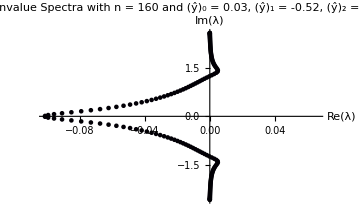

```mathematica
k=160;
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0/5,yHat1/5,yHat2/5]]
```

## Dendro Output

### Hide

```mathematica
derivativeOrder=1;
interiorOrder=n;
totalBoundRows=numBoundaryRows;
freeInteriorParameters={};
freeBoundaryParameters={};
RHSInteriorList=RHSPars;
interiorParametersValues=interiorCoeffsA6/.{α->alpha,β->beta};
boundaryParametersValues=boundaryLuke/.{α12->gamma01,β12->gamma02,α21->gamma10,α22->gamma12,β22->gamma13,β31->gamma20,α31->gamma21,α32->gamma23,β32->gamma24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};
LHSBoundaryList={gamma01,gamma02,gamma10,gamma12,gamma13,gamma20,gamma21,gamma23,gamma24};
RHSBoundaryList={a00,a01,a02,a03,a04,a05,a06,a10,a11,a12,a13,a14,a15,a16,a20,a21,a22,a23,a24,a25,a26};
(*Don't need to mess with these until we incorporate this procedure with James's filtering*)
filterIntCoeff;
filterBoundCoeff;
filterIntParam;
filterBoundParam;
filtering=False;
(*boundary={α12->γ01,β12->γ02,α21->γ10,α22->γ12,β22->γ13,β31->γ20,α31->γ21,α32->γ23,β32->γ24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};*)
```

```mathematica
(*****************Print coefficients in Dendro-GR Format*****************)
If[derivativeOrder==1,
LHSName="P1";
RHSName="Q1";
nth="1st";
coeffs="D_coeffs";
order="First",
If[derivativeOrder==2,
LHSName="P2";
RHSName="Q2";
nth="2nd";
coeffs="D_coeffs";
order="Second"]];
If[LHSBandCount==3,
LHSStructure="T",
If[LHSBandCount==5,
LHSStructure="P"]];

(*Convert Mathematica expression syntax to C/C++ expression syntax*)
convertToCCode[expr_]:=Module[{str},str=ToString[expr,InputForm];
(*Add ".0" to standalone integers but not to variables with numbers*)
(*Formatting adjustments to match C/C++ syntax*)str=StringReplace[str,{" "->"","*"->" * ","/"->" / ","+"->" + ","-"->" - ","^"->" ^ "}];
str]
(*Function to generate the line of C/C++ code to define the fixed variables*)
generateCAssignment[rule_]:=Module[{variable,expression,cCode,cAssignment},
variable=ToString[rule[[1]]];
expression=rule[[2]];
cCode=convertToCCode[expression];
cAssignment="double "<>variable<>" = "<>cCode<>";";
cAssignment
]






(*Initial Block*)
initialBlock=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order"}];
initialBlock2=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order","Filtered"}];

(*Free Parameters Block*)
freeParameters=Join[freeInteriorParameters,freeBoundaryParameters];
numFreePars=Length[freeParameters];
alphaPrint=StringReplace[generateCAssignment[Select[interiorParametersValues,#[[1]]===alpha&][[1]]],"alpha"->"alpha0"];
freeParPrints={};
If[numFreePars>0,
For[i=1,i<=numFreePars,i++,
AppendTo[freeParPrints,StringJoin[{"\n\t\tdouble ",ToString[freeParameters[[i]]]," = ",coeffs,"[",ToString[i],"];"}]]]]
freeParametersBlock=StringJoin[{"\t",alphaPrint,"\n\t\tdouble alpha = alpha0 + ",coeffs,"[0];",freeParPrints}];

(*Filter*)
freeParPrints2={};
freeParametersBlock2=StringJoin[{"\t","\n\t\tdouble alpha = ","F_coeffs","[0];",If[LHSBandCount==5,StringJoin["\n\t\tdouble beta = ","F_coeffs","[1];"],""]}];

(*Fixed Parameters Block*)
(*Create a list of the solved fixed parameters in C/C++ syntax*)
interiorParametersValues3=DeleteCases[interiorParametersValues,Rule[alpha,_]];
interiorParameterPrints=Table[
generateCAssignment[interiorParametersValues3[[i]]],
{i,1,Length[interiorParametersValues]-1}
];
boundaryParameterPrints=Table[
generateCAssignment[boundaryParametersValues[[i]]],
{i,1,Length[boundaryParametersValues]}
];
(*For filtered coefficients*)
interiorParameterPrints2=Table[
generateCAssignment[filterIntCoeff[[i]]],
{i,1,Length[filterIntCoeff]}
];
boundaryParameterPrints2=Table[
generateCAssignment[filterBoundCoeff[[i]]],
{i,1,Length[filterBoundCoeff]}
];
(*Print the coefficients in a single block of text rather than individual lines*)
fixedParametersBlockD=StringJoin["\t\t",Riffle[Join[interiorParameterPrints,boundaryParameterPrints],"\n\t\t"]];
fixedParametersBlockD2=StringJoin["\t\t",Riffle[Join[interiorParameterPrints2,boundaryParameterPrints2],"\n\t\t"]];

(*Structure Block*)
(*LHS Boundary*)
PDiagBoundary="";
LHSRowList=ToExpression[GatherBy[LHSBoundaryList,StringDrop[ToString[#],5]~StringTake~1&]];
For[i=1,i<=Length[LHSRowList],i++,
If[i==1,PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t","{1.0, ",StringDrop[ToString[LHSRowList[[i]]],1],","]];
If[i==2,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1}]],1],","]]];
If[i==3,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{","0.0, ",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t",StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
If[i>=4,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],StringDrop[StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
];
(*LHS Filter Boundary*)
RDiagBoundary="";
For[i=1,i<=Length@filterBoundParam,i++,
If[i==1,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha, beta},"]];
];
If[i==2,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha 1.0, alpha, beta},"]];
];
If[i>=3,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],"alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],"beta, alpha, 1.0, alpha, beta},"]];
];
];

(*LHS Interior*)
If[LHSBandCount==3,
PDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
PDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];
(*LHS Filter Interior*)
If[LHSBandCount==3,
RDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
RDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];

(*RHS Boundary*)
QDiagBoundary="";
RHSRowList=ToExpression[GatherBy[RHSBoundaryList,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList],i++,QDiagBoundary=StringJoin[QDiagBoundary,"\n\t\t\t",ToString[RHSRowList[[i]]],","]]
(*RHS Filter Boundary*)
SDiagBoundary="";
RHSRowList2=ToExpression[GatherBy[filterBoundParam,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList2],i++,SDiagBoundary=StringJoin[SDiagBoundary,"\n\t\t\t",ToString[RHSRowList2[[i]]]]]

(*RHS Interior*)
QDiagInterior={};
len=(2*Length[RHSInteriorList]+1);
If[derivativeOrder==1,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[-RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"0.0"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]
],
If[derivativeOrder==2,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[-RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"t1"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]]]]

(*RHS Filter Interior*)
SDiagInterior={};
newFilterIntParam=Drop[filterIntParam,1];
len=(2*Length[newFilterIntParam]+1);
For[i=1,i<=len,i++,
If[i<=Length[newFilterIntParam],PrependTo[SDiagInterior,ToString[newFilterIntParam[[i]]]<>"/"<>ToString[2]<>".0"]];
If[i==(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,"a0"]];
If[i>(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,ToString[newFilterIntParam[[i-Length[newFilterIntParam]-1]]]<>"/"<>ToString[2]<>".0"]]
]


PDiagBoundaryStr=StringDrop[StringDrop[PDiagBoundary,1],-1];
PDiagInteriorStr=StringDrop[StringDrop[PDiagInterior,1],-1];
RDiagBoundaryStr=StringDrop[StringDrop[RDiagBoundary,1],-1];
RDiagInteriorStr=StringDrop[StringDrop[RDiagInterior,1],-1];
QDiagBoundaryStr=StringDrop[StringDrop[QDiagBoundary,1],-1];
QDiagInteriorStr=StringDrop[StringDrop[ToString[QDiagInterior],1],-1];
SDiagBoundaryStr=StringDrop[SDiagBoundary,1];
SDiagInteriorStr=StringDrop[StringDrop[ToString[SDiagInterior],1],-1];

(*Subscript[t, 1] is the middle RHS Interior Coefficient for Second Derivatives*)
t1List={};
For[i=1,i<=Length[RHSInteriorList],i++,
AppendTo[t1List,ToString[RHSInteriorList[[i]]]<>"/"<>ToString[i^2]<>".0"]
];
If[derivativeOrder==1,
t1="",
If[derivativeOrder==2,
t1=StringJoin["-2.0 * ("<>StringDrop[StringDrop[ToString[t1List],1],-1]<>")"]]];


If[filtering,
filterFinalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock2,"(\n","\tconst std::vector<double>& ","F_coeffs",") {\n","\t",freeParametersBlock2,"\n\n",fixedParametersBlockD2,"\n\n","\t\t// boundary elements for R matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","R","DiagBoundary{\n",RDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for R matrix for ",nth," derivative\n","\t\tstd::vector<double> ","R","DiagInterior{\n","\t\t\t",RDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for S matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","S","DiagBoundary\n",SDiagBoundaryStr,"\n","\t\t;\n\n","\t\t// diagonal elements for S matrix for ",nth," derivative\n","\t\tstd::vector<double> ","S","DiagInterior{\n","\t\t\t",SDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t","R","DiagInterior, ","S","DiagInterior, ","S","DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}"}];
]

finalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock,"(\n","\tconst std::vector<double>& ",coeffs,") {\n","\t",freeParametersBlock,"\n\n",fixedParametersBlockD,"\n\n","\t\t// boundary elements for P matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",LHSName,"DiagBoundary{\n",PDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for P matrix for ",nth," derivative\n","\t\tstd::vector<double> ",LHSName,"DiagInterior{\n","\t\t\t",PDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",RHSName,"DiagBoundary{\n",QDiagBoundaryStr,"\n","\t\t};\n\n",If[derivativeOrder==1,t1,If[derivativeOrder==2,"\t\tdouble t1 = "<>t1<>";\n"]],"\t\t// diagonal elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<double> ",RHSName,"DiagInterior{\n","\t\t\t",QDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t",LHSName,"DiagInterior, ",LHSName,"DiagBoundary, ",RHSName,"DiagInterior, ",RHSName,"DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}",If[filtering,"\n\n"<>filterFinalBlock,""]}];
```

GatherBy::list: List expected at position 1 in GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&].

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Drop::drop: Cannot drop positions 1 through 1 in filterIntParam.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

StringDrop::drop: Cannot drop positions 1 through 1 in "".

### Show

```mathematica
outExt="h";
(*Print header*)
Print[Style["Dendro-Ready Coefficients (Copied to clipboard):",Bold,FontSize->24]];
Print[finalBlock];
(*Copy the block of text to the user's clipboard*)
CopyToClipboard[finalBlock];

(*Save to output file*)
fileName=StringJoin[{"BYU_A6","_yHat0_",ToString[yHat0],"_yHat1_",ToString[yHat1],"_yHat2_",ToString[yHat2],".",outExt}];
Export[fileName,finalBlock,"Text"];
Print[StringJoin[{"Saved to file: ",fileName}]]
```

Dendro-Ready Coefficients (Copied to clipboard):

MatrixDiagonalEntries* BYUDerivsP121R3DiagonalsFirstOrder(
	const std::vector<double>& D_coeffs) {
		double alpha0 = 0.5770460201292381;
		double alpha = alpha0 + D_coeffs[0];

		double beta = 0.08900836845092142;
		double a1 = 0.6517078440898839;
		double a2 = 0.24815882627035918;
		double a3 = 0.006009630649852392;
		double gamma01 = 9.82050086297005;
		double gamma02 = 10.282867809058313;
		double gamma10 = 0.08185064221829087;
		double gamma12 = 1.6890627481714804;
		double gamma13 = 0.4961478931388701;
		double gamma20 = 0.017918887158094664;
		double gamma21 = 0.33500390219730425;
		double gamma23 = 0.7548768581531722;
		double gamma24 = 0.13667343083285768;
		double a00 =  - 3.73445251380582;
		double a01 =  - 10.765902315893966;
		double a02 = 11.158777481815811;
		double a03 = 3.8932795799881186;
		double a04 =  - 0.6389839738157034;
		double a05 = 0.09587727397420936;
		double a06 =  - 0.008595531676508965;
		double a10 =  - 0.31850909623427476;
		double a11 =  - 1.396944235854646;
		double a12 = 0.5364016058704685;
		double a13 = 1.1223168928950014;
		double a14 = 0.059450604503400145;
		double a15 =  - 0.0027438380250710795;
		double a16 = 0.00002806684476978311;
		double a20 =  - 0.07670359108573083;
		double a21 =  - 0.6273443641711278;
		double a22 =  - 0.37833992259630045;
		double a23 = 0.7128462614236629;
		double a24 = 0.3572245284141374;
		double a25 = 0.012842138314361781;
		double a26 =  - 0.0005250502990408262;

		// boundary elements for P matrix for 1st derivative
		std::vector<std::vector<double>> P1DiagBoundary{
			{1.0, gamma01, gamma02},
			{gamma10, 1.0, gamma12, gamma13},
			{gamma20, gamma21, 1.0, gamma23, gamma24}
		};

		// diagonal elements for P matrix for 1st derivative
		std::vector<double> P1DiagInterior{
			beta, alpha, 1.0, alpha, beta
		};

		// boundary elements for Q matrix for 1st derivative
		std::vector<std::vector<double>> Q1DiagBoundary{
			{a00, a01, a02, a03, a04, a05, a06},
			{a10, a11, a12, a13, a14, a15, a16},
			{a20, a21, a22, a23, a24, a25, a26}
		};

		// diagonal elements for Q matrix for 1st derivative
		std::vector<double> Q1DiagInterior{
			-a3, -a2, -a1, 0.0, a1, a2, a3
		};

		// store the entries for matrix creation
		MatrixDiagonalEntries* diagEntries = new
			MatrixDiagonalEntries{
				P1DiagInterior, P1DiagBoundary, Q1DiagInterior, Q1DiagBoundary
			};
		return diagEntries;
	}

Saved to file: BYU_P4_yHat0_1.89_yHat1_1.65_yHat2_1.14.h

# P6 (B6) Scheme

## Initialization

The matrix system of equations we are solving for this scheme is:
	P=(1
γ_10
γ_20
0
0
0
0
0
0 γ_01
1
γ_21
γ_31
0
0
0
0
0 γ_02
γ_12
1
γ_32
β
0
0
0
0 0
γ_13
γ_23
1
α
γ_35
0
0
0 0
0
γ_24
γ_34
1
γ_34
γ_24
0
0 0
0
0
γ_35
α
1
γ_23
γ_13
0 0
0
0
0
β
γ_32
1
γ_12
γ_02 0
0
0
0
0
γ_31
γ_21
1
γ_01 0
0
0
0
0
0
γ_20
γ_10
1)
	Q=(a_00
a_10
a_20
a_30
-a_4
-a_38
-a_28
-a_18
-a_08 a_01
a_11
a_21
a_31
-a_3
-a_37
-a_27
-a_17
-a_07 a_02
a_12
a_22
a_32
-a_2
-a_36
-a_26
-a_16
-a_06 a_03
a_13
a_23
a_33
-a_1
-a_35
-a_25
-a_15
-a_05 a_04
a_14
a_24
a_34
0
-a_34
-a_24
-a_14
-a_04 a_05
a_15
a_25
a_35
a_1
-a_33
-a_23
-a_13
-a_03 a_06
a_16
a_26
a_36
a_2
-a_32
-a_22
-a_12
-a_02 a_07
a_17
a_27
a_37
a_3
-a_31
-a_21
-a_11
-a_01 a_08
a_18
a_28
a_38
a_4
-a_30
-a_20
-a_10
-a_00 )

```mathematica
(*From KimInteriorOptimization.nb, one day to be merged with this one. Or I could DumpSave[] in that notebook and then Get[] here.*)
(*Note that these are found with the P6 Scheme NEW header in that notebook*)
interiorCoeffsB6={α->0.59067138684056,β->0.10005088370852962,a1->0.6375976953896195,a2->0.26328410014665704,a3->0.009340368066539819,a4->-0.0003661823333658686};

(*If you have the .mx files in the same directory as this notebook, these will let you skip the long computation of defining bdCoeffs under the "Solve for Boundary Coefficients" section*)
(*Get["B6_bdCoeffs3.mx"];
Get["B6_bdCoeffs2.mx"];
Get["B6_bdCoeffs1.mx"];
Get["B6_bdCoeffs0.mx"];*)
```

## General Extrapolation Polynomial

For the P6 (B6) scheme, we have:
	LHSBandCount = 5
	n = 6
	freeInteriorPars = 3
	yDeriv = 14

```mathematica
(*User chooses these parameters, the rest is calculated from these*)
LHSBandCount=5; (*3 for tridiagonal, 5 for pentadiagonal*)
n=6; (*order of the scheme*)
freeInteriorPars=3; (*number of free parameters used for Kim's optimization on the interior*)
yDeriv=14; (*(d^n P)/dx^n(ŷ)=0 from Kim 2024 Eq. 10, this is n in that equation*) (*provide constraints on what the user can choose for this. Upper bound should be polynomialorder to prevent the matrix from being singular, and lower bound should be order·2 I think.*)

LHSPars=Switch[LHSBandCount,3,{α},5,{α,β}];
RHSPars=Table[ToExpression[StringJoin["a",ToString[i]]],{i,1,Ceiling[n/2]-Length@LHSPars+freeInteriorPars}];
numBoundaryRows=Length@RHSPars;
fOrder=(2*Length@RHSPars)+1;
fpOrder=LHSBandCount+(numBoundaryRows-(LHSBandCount-1)/2);
PolynomialOrder=fOrder+fpOrder;


rowf1=Join[{1},Table[0,{i,1,PolynomialOrder}]];
rowf=Table[Table[i^j,{j,0,PolynomialOrder}],{i,1,fOrder-1}];
rowfp1=Join[{0,1},Table[0,{i,2,PolynomialOrder}]];
rowfp=Table[Table[j i^(j-1),{j,0,PolynomialOrder}],{i,1,fpOrder-1}];
rowyHat=Join[Table[0,{i,1,yDeriv}],Table[(i!)/((i-yDeriv)!) yHat^(i-yDeriv),{i,yDeriv,PolynomialOrder}]];

matf=PrependTo[rowf,rowf1];
matfp=PrependTo[rowfp,rowfp1];
matfCombined=Join[matf,matfp];
LMat=AppendTo[matfCombined,rowyHat];

pVec=Table[ToExpression[StringJoin["p",ToString[i]]],{i,0,PolynomialOrder}];
fVec=Join[Table[ToExpression[StringJoin["f",ToString[i]]],{i,0,fOrder-1}],Table[ToExpression[StringJoin["fp",ToString[i]]],{i,0,fpOrder-1}],{0}];

pCoeffs=Solve[LMat.pVec==fVec,pVec][[1]];

yHatSingularities=(Transpose@Solve[Det[LMat]==0,yHat])[[1]]//N;
P[x_]=Total[Table[pVec[[i+1]]*x^i,{i,0,PolynomialOrder}]]/.pCoeffs;

Print["System:\n",MatrixForm[LMat]," ",MatrixForm[pVec]," = ",MatrixForm[fVec]]
Print["Singularities:\n",MatrixForm[yHatSingularities]]
(*Print["Coefficients:\n",MatrixForm[pCoeffs]]*)
```

System:
(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 4 | 8 | 16 | 32 | 64 | 128 | 256 | 512 | 1024 | 2048 | 4096 | 8192 | 16384 | 32768 | 65536
1 | 3 | 9 | 27 | 81 | 243 | 729 | 2187 | 6561 | 19683 | 59049 | 177147 | 531441 | 1594323 | 4782969 | 14348907 | 43046721
1 | 4 | 16 | 64 | 256 | 1024 | 4096 | 16384 | 65536 | 262144 | 1048576 | 4194304 | 16777216 | 67108864 | 268435456 | 1073741824 | 4294967296
1 | 5 | 25 | 125 | 625 | 3125 | 15625 | 78125 | 390625 | 1953125 | 9765625 | 48828125 | 244140625 | 1220703125 | 6103515625 | 30517578125 | 152587890625
1 | 6 | 36 | 216 | 1296 | 7776 | 46656 | 279936 | 1679616 | 10077696 | 60466176 | 362797056 | 2176782336 | 13060694016 | 78364164096 | 470184984576 | 2821109907456
1 | 7 | 49 | 343 | 2401 | 16807 | 117649 | 823543 | 5764801 | 40353607 | 282475249 | 1977326743 | 13841287201 | 96889010407 | 678223072849 | 4747561509943 | 33232930569601
1 | 8 | 64 | 512 | 4096 | 32768 | 262144 | 2097152 | 16777216 | 134217728 | 1073741824 | 8589934592 | 68719476736 | 549755813888 | 4398046511104 | 35184372088832 | 281474976710656
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16
0 | 1 | 4 | 12 | 32 | 80 | 192 | 448 | 1024 | 2304 | 5120 | 11264 | 24576 | 53248 | 114688 | 245760 | 524288
0 | 1 | 6 | 27 | 108 | 405 | 1458 | 5103 | 17496 | 59049 | 196830 | 649539 | 2125764 | 6908733 | 22320522 | 71744535 | 229582512
0 | 1 | 8 | 48 | 256 | 1280 | 6144 | 28672 | 131072 | 589824 | 2621440 | 11534336 | 50331648 | 218103808 | 939524096 | 4026531840 | 17179869184
0 | 1 | 10 | 75 | 500 | 3125 | 18750 | 109375 | 625000 | 3515625 | 19531250 | 107421875 | 585937500 | 3173828125 | 17089843750 | 91552734375 | 488281250000
0 | 1 | 12 | 108 | 864 | 6480 | 46656 | 326592 | 2239488 | 15116544 | 100776960 | 665127936 | 4353564672 | 28298170368 | 182849716224 | 1175462461440 | 7522959753216
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 87178291200 | 1307674368000 yHat | 10461394944000 yHat^2) (p0
p1
p2
p3
p4
p5
p6
p7
p8
p9
p10
p11
p12
p13
p14
p15
p16) = (f0
f1
f2
f3
f4
f5
f6
f7
f8
fp0
fp1
fp2
fp3
fp4
fp5
fp6
0)

Singularities:
(yHat→2.94357
yHat→4.18143)

## Solve for Boundary Coefficients

Goal:
	Solve a system of equations for bdCoeffsList3 in terms of the optimization free parameter ŷ
Variables:
	fVars3: List of f_i and f_i' variables that will appear in the shifted stencil for Node 3
	bdCoeffsList3: List of boundary coefficients that will appear in the shifted stencil for Node 3
	schemeShifted: The shifted scheme for Node 3
	schemeCentered: The centered scheme for Node 3 in terms of the extrapolation polynomial P(x)
		NOTE: To make the Collect[] process easier, we write these schemes as LHS-RHS=0 rather than the usual LHS=RHS.
	schemeNode4: The scheme for Node 4, which only depends on interiorCoeffsP6
	SOLfp6: The solution to Node 4’s scheme equation for f_6' in terms of fVars3
	eq: Scheme equation where the coefficient terms from schemeCentered and schemeShifted are set equal to each other
	coeffEqs3: System of equations with each of the coefficient terms equal to each other
	bdCoeffs3: Solution to the system of equations for bdCoeffsList3 in terms of ŷ
Process:
	1. Initialize the necessary equations.
	2. We want schemeShifted and schemeCentered to both be in terms of fVars3 with some coefficients. Due to the presence of P(x) terms in schemeCentered, it is in terms of fVars3 as well as f_6'. We eliminate the dependence on f_6' by using Node 4’s scheme to solve for f_6' in terms of fVars3.
	3. Now that schemeShifted and schemeCentered are both in terms of fVars3, we construct a system of equations by equating the coefficient in front of each term of fVars3 in schemeCentered with the corresponding coefficient in front of the same term in schemeShifted.
	4. We solve this system of equations for bdCoeffsList3 in terms of interiorCoeffsP6 (which are substituted in) and the optimization free parameter ŷ.
		NOTE: In the standard scheme approach, we set γ_33=1 to ensure the main diagonal of the LHS matrix is all 1’s. When solving this system of equations, we must include γ_33 so that bdCoeffsList3 and fVars3 have the same length since this allows us to find a unique solution to the system of equations. We apply the normal condition later on.
	5. OPTIONAL: We may save the variable bdCoeffs3 to a binary file in the current directory. This is helpful to avoid having to run this process multiple times, as it can become computationally expensive.
Differences:
	For Nodes 2, 1, and 0, the entire process translates directly with a few changes. fVars, bdCoeffsList, schemeShifted, and schemeCentered all change, as we are considering the scheme for a different row, but the equations have the same structure. The main notable difference is in Step 2; In addition to substituting in the solution from Node 4 for f_6' in terms of the other fVars, we must also do the same for f_5' (Nodes 2, 1, and 0), f_4' (Nodes 1 and 0), and f_3' (Node 0) using Nodes 3, 2, and 1, respectively.

### Node 3

```mathematica
(*----------STEP 1----------*)
fVars3={fp1,fp2,fp3,fp4,fp5,f0,f1,f2,f3,f4,f5,f6,f7,f8};
bdCoeffsList3={γ31,γ32,γ33,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38};
schemeShifted=γ31 fp1+γ32 fp2+γ33 fp3+γ34 fp4+γ35 fp5-(a30 f0+a31 f1+a32 f2+a33 f3+a34 f4+a35 f5+a36 f6+a37 f7+a38 f8); (*==0*)
schemeCentered=β fp1+α fp2+fp3+α fp4+β fp5-(-a4 P[-1]-a3 f0-a2 f1-a1 f2+a1 f4+a2 f5+a3 f6+a4 f7); (*==0*)

(*----------STEP 2----------*)
schemeNode4=β fp2+α fp3+fp4+α fp5+β fp6==-a4 f0-a3 f1-a2 f2-a1 f3+a1 f5+a2 f6+a3 f7+a4 f8;
SOLfp6=Solve[schemeNode4,fp6][[1,1]]/.interiorCoeffsB6;
schemeCentered=schemeCentered/.SOLfp6;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars3];

(*----------STEP 4----------*)
coeffEqs3=Table[Coefficient[eq,fVars3[[i]]]==0,{i,1,Length@fVars3}];
bdCoeffs3=(Solve[coeffEqs3,bdCoeffsList3][[1]])/.interiorCoeffsB6;

(*----------STEP 5----------*)
DumpSave["B6_bdCoeffs3.mx","Global`bdCoeffs3"];
```

### Node 2

```mathematica
(*----------STEP 1----------*)
fVars2={fp0,fp1,fp2,fp3,fp4,f0,f1,f2,f3,f4,f5,f6,f7,f8};
bdCoeffsList2={γ20,γ21,γ22,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28};
schemeShifted=γ20 fp0+γ21 fp1+γ22 fp2+γ23 fp3+γ24 fp4-(a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6+a27 f7+a28 f8); (*==0*)
schemeCentered=β fp0+α fp1+fp2+α fp3+β fp4-(-a4 P[-2]-a3 P[-1]-a2 f0-a1 f1+a1 f3+a2 f4+a3 f5+a4 f6); (*==0*)

(*----------STEP 2----------*)
schemeNode4=β fp2+α fp3+fp4+α fp5+β fp6==-a4 f0-a3 f1-a2 f2-a1 f3+a1 f5+a2 f6+a3 f7+a4 f8;
schemeNode3=γ31 fp1+γ32 fp2+γ33 fp3+γ34 fp4+γ35 fp5==a30 f0+a31 f1+a32 f2+a33 f3+a34 f4+a35 f5+a36 f6+a37 f7+a38 f8;
SOLfp6=Solve[schemeNode4,fp6][[1,1]]/.interiorCoeffsB6;
SOLfp5=Solve[schemeNode3,fp5][[1,1]]/.bdCoeffs3;
schemeCentered=schemeCentered/.SOLfp6/.SOLfp5;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars2];

(*----------STEP 4----------*)
coeffEqs2=Table[Coefficient[eq,fVars2[[i]]]==0,{i,1,Length@fVars2}];
bdCoeffs2=(Solve[coeffEqs2,bdCoeffsList2][[1]])/.interiorCoeffsB6;

(*----------STEP 5----------*)
DumpSave["B6_bdCoeffs2.mx","Global`bdCoeffs2"];
```

### Node 1

```mathematica
(*----------STEP 1----------*)
fVars1={fp0,fp1,fp2,fp3,f0,f1,f2,f3,f4,f5,f6,f7,f8};
bdCoeffsList1={γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18};
schemeShifted=γ10 fp0+γ11 fp1+γ12 fp2+γ13 fp3-(a10 f0+a11 f1+a12 f2+a13 f3+a14 f4+a15 f5+a16 f6+a17 f7+a18 f8); (*==0*)
schemeCentered=β P'[-1]+α fp0+fp1+α fp2+β fp3-(-a4 P[-3]-a3 P[-2]-a2 P[-1]-a1 f0+a1 f2+a2 f3+a3 f4+a4 f5); (*==0*)

(*----------STEP 2----------*)
schemeNode4=β fp2+α fp3+fp4+α fp5+β fp6==-a4 f0-a3 f1-a2 f2-a1 f3+a1 f5+a2 f6+a3 f7+a4 f8;
schemeNode3=γ31 fp1+γ32 fp2+γ33 fp3+γ34 fp4+γ35 fp5==a30 f0+a31 f1+a32 f2+a33 f3+a34 f4+a35 f5+a36 f6+a37 f7+a38 f8;
schemeNode2=γ20 fp0+γ21 fp1+γ22 fp2+γ23 fp3+γ24 fp4==a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6+a27 f7+a28 f8;
SOLfp6=Solve[schemeNode4,fp6][[1,1]]/.interiorCoeffsB6;
SOLfp5=Solve[schemeNode3,fp5][[1,1]]/.bdCoeffs3;
SOLfp4=Solve[schemeNode2,fp4][[1,1]]/.bdCoeffs2;
schemeCentered=schemeCentered/.SOLfp6/.SOLfp5/.SOLfp4;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars1];

(*----------STEP 4----------*)
coeffEqs1=Table[Coefficient[eq,fVars1[[i]]]==0,{i,1,Length@fVars1}];
bdCoeffs1=(Solve[coeffEqs1,bdCoeffsList1][[1]])/.interiorCoeffsB6;

(*----------STEP 5----------*)
DumpSave["B6_bdCoeffs1.mx","Global`bdCoeffs1"];
```

### Node 0

```mathematica
(*----------STEP 1----------*)
fVars0={fp0,fp1,fp2,f0,f1,f2,f3,f4,f5,f6,f7,f8};
bdCoeffsList0={γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08};
schemeShifted=γ00 fp0+γ01 fp1+γ02 fp2-(a00 f0+a01 f1+a02 f2+a03 f3+a04 f4+a05 f5+a06 f6+a07 f7+a08 f8); (*==0*)
schemeCentered=β P'[-2]+α P'[-1]+fp0+α fp1+β fp2-(-a4 P[-4]-a3 P[-3]-a2 P[-2]-a1 P[-1]+a1 f1+a2 f2+a3 f3+a4 f4); (*==0*)

(*----------STEP 2----------*)
schemeNode4=β fp2+α fp3+fp4+α fp5+β fp6==-a4 f0-a3 f1-a2 f2-a1 f3+a1 f5+a2 f6+a3 f7+a4 f8;
schemeNode3=γ31 fp1+γ32 fp2+γ33 fp3+γ34 fp4+γ35 fp5==a30 f0+a31 f1+a32 f2+a33 f3+a34 f4+a35 f5+a36 f6+a37 f7+a38 f8;
schemeNode2=γ20 fp0+γ21 fp1+γ22 fp2+γ23 fp3+γ24 fp4==a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6+a27 f7+a28 f8;
schemeNode1=γ10 fp0+γ11 fp1+γ12 fp2+γ13 fp3==a10 f0+a11 f1+a12 f2+a13 f3+a14 f4+a15 f5+a16 f6+a17 f7+a18 f8;
SOLfp6=Solve[schemeNode4,fp6][[1,1]]/.interiorCoeffsB6;
SOLfp5=Solve[schemeNode3,fp5][[1,1]]/.bdCoeffs3;
SOLfp4=Solve[schemeNode2,fp4][[1,1]]/.bdCoeffs2;
SOLfp3=Solve[schemeNode1,fp3][[1,1]]/.bdCoeffs1;
schemeCentered=schemeCentered/.SOLfp6/.SOLfp5/.SOLfp4/.SOLfp3;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars0];

(*----------STEP 4----------*)
coeffEqs0=Table[Coefficient[eq,fVars0[[i]]]==0,{i,1,Length@fVars0}];
bdCoeffs0=(Solve[coeffEqs0,bdCoeffsList0][[1]])/.interiorCoeffsB6;

(*----------STEP 5----------*)
DumpSave["B6_bdCoeffs0.mx","Global`bdCoeffs0"];
```

## Optimize ŷ

### Set and Normalize Coefficients

We normalize the coefficients so that the main diagonal of the LHS matrix is all 1’s, but we leave the coefficients in terms of the optimization free parameter ŷ so that we can optimize over it.

```mathematica
Clear[γ33,γ31,γ32,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38]
Clear[γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28]
Clear[γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08]

{γ33,γ31,γ32,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38}=1/γ33*{γ33,γ31,γ32,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38}/.bdCoeffs3;
{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28}=1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28}/.bdCoeffs2;
{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18}=1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18}/.bdCoeffs1;
{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08}=1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08}/.bdCoeffs0;
```

### Node 3

```mathematica
𝔸3[κ_]=γ31 Cos[κ]+γ32 Cos[2 κ]+Cos[3 κ]+γ34 Cos[4 κ]+γ35 Cos[5 κ];
𝔹3[κ_]=γ31 Sin[κ]+γ32 Sin[2 κ]+Sin[3 κ]+γ34 Sin[4 κ]+γ35 Sin[5 κ];
ℂ3[κ_]=a30+a31 Cos[κ]+a32 Cos[2 κ]+a33 Cos[3 κ]+a34 Cos[4 κ]+a35 Cos[5 κ]+a36 Cos[6 κ]+a37 Cos[7 κ]+a38 Cos[8 κ];
𝔻3[κ_]=a31 Sin[κ]+a32 Sin[2 κ]+a33 Sin[3 κ]+a34 Sin[4 κ]+a35 Sin[5 κ]+a36 Sin[6 κ]+a37 Sin[7 κ]+a38 Sin[8 κ];
κBar3Re[κ_]=(𝔸3[κ]*𝔻3[κ]-𝔹3[κ]*ℂ3[κ])/((𝔸3[κ])^2+(𝔹3[κ])^2);
κBar3Im[κ_]=(-𝔸3[κ]*ℂ3[κ]-𝔹3[κ]*𝔻3[κ])/((𝔸3[κ])^2+(𝔹3[κ])^2);
κBar3Norm[κ_]=Abs[κBar3Re[κ]+I*κBar3Im[κ]];
```

```mathematica
Δ3Re[κ_]=(κ*((𝔸3[κ])^2+(𝔹3[κ])^2)-(𝔸3[κ]*𝔻3[κ]-𝔹3[κ]*ℂ3[κ]))^2;
Δ3Im[κ_]=(0*((𝔸3[κ])^2+(𝔹3[κ])^2)-(-𝔸3[κ]*ℂ3[κ]-𝔹3[κ]*𝔻3[κ]))^2;
Δ3Norm[κ_]=(κ-κBar3Norm[κ])^2;
```

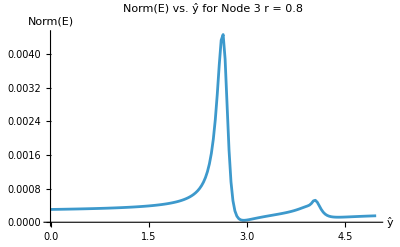

Evaluation time: 18.067083

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat3Array=Range[0,5,0.03];
Δ3NormArray=Table[Δ3Norm[κ]/.{yHat->yHat3Array[[i]]},{i,1,Length@yHat3Array}];
ENorm3Array=Table[NIntegrate[Δ3NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat3Array}];

ListPlot[Transpose@{yHat3Array,ENorm3Array},Joined->True,PlotRange->All,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 3\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

### Node 2

```mathematica
𝔸2[κ_]=γ20+γ21 Cos[κ]+Cos[2 κ]+γ23 Cos[3 κ]+γ24 Cos[4 κ];
𝔹2[κ_]=γ21 Sin[κ]+Sin[2 κ]+γ23 Sin[3 κ]+γ24 Sin[4 κ];
ℂ2[κ_]=a20+a21 Cos[κ]+a22 Cos[2 κ]+a23 Cos[3 κ]+a24 Cos[4 κ]+a25 Cos[5 κ]+a26 Cos[6 κ]+a27 Cos[7 κ]+a28 Cos[8 κ];
𝔻2[κ_]=a21 Sin[κ]+a22 Sin[2 κ]+a23 Sin[3 κ]+a24 Sin[4 κ]+a25 Sin[5 κ]+a26 Sin[6 κ]+a27 Sin[7 κ]+a28 Sin[8 κ];
κBar2Re[κ_]=(𝔸2[κ]*𝔻2[κ]-𝔹2[κ]*ℂ2[κ])/((𝔸2[κ])^2+(𝔹2[κ])^2);
κBar2Im[κ_]=(-𝔸2[κ]*ℂ2[κ]-𝔹2[κ]*𝔻2[κ])/((𝔸2[κ])^2+(𝔹2[κ])^2);
κBar2Norm[κ_]=Abs[κBar2Re[κ]+I*κBar2Im[κ]];
```

```mathematica
Δ2Re[κ_]=(κ*((𝔸2[κ])^2+(𝔹2[κ])^2)-(𝔸2[κ]*𝔻2[κ]-𝔹2[κ]*ℂ2[κ]))^2;
Δ2Im[κ_]=(0*((𝔸2[κ])^2+(𝔹2[κ])^2)-(-𝔸2[κ]*ℂ2[κ]-𝔹2[κ]*𝔻2[κ]))^2;
Δ2Norm[κ_]=(κ-κBar2Norm[κ])^2;
```

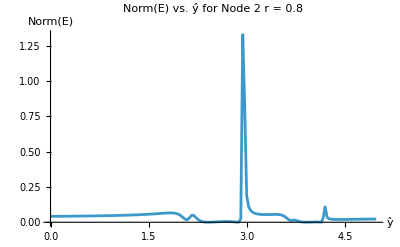

Evaluation time: 18.089397

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat2Array=Range[0,5,0.03];
Δ2NormArray=Table[Δ2Norm[κ]/.{yHat->yHat2Array[[i]]},{i,1,Length@yHat2Array}];
ENorm2Array=Table[NIntegrate[Δ2NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat2Array}];

ListPlot[Transpose@{yHat2Array,ENorm2Array},Joined->True,PlotRange->All,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 2\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

### Node 1

```mathematica
𝔸1[κ_]=γ10+Cos[κ]+γ12 Cos[2 κ]+γ13 Cos[3 κ];
𝔹1[κ_]=Sin[κ]+γ12 Sin[2 κ]+γ13 Sin[3 κ];
ℂ1[κ_]=a10+a11 Cos[κ]+a12 Cos[2 κ]+a13 Cos[3 κ]+a14 Cos[4 κ]+a15 Cos[5 κ]+a16 Cos[6 κ]+a17 Cos[7 κ]+a18 Cos[8 κ];
𝔻1[κ_]=a11 Sin[κ]+a12 Sin[2 κ]+a13 Sin[3 κ]+a14 Sin[4 κ]+a15 Sin[5 κ]+a16 Sin[6 κ]+a17 Sin[7 κ]+a18 Sin[8 κ];
κBar1Re[κ_]=(𝔸1[κ]*𝔻1[κ]-𝔹1[κ]*ℂ1[κ])/((𝔸1[κ])^2+(𝔹1[κ])^2);
κBar1Im[κ_]=(-𝔸1[κ]*ℂ1[κ]-𝔹1[κ]*𝔻1[κ])/((𝔸1[κ])^2+(𝔹1[κ])^2);
κBar1Norm[κ_]=Abs[κBar1Re[κ]+I*κBar1Im[κ]];
```

```mathematica
Δ1Re[κ_]=(κ*((𝔸1[κ])^2+(𝔹1[κ])^2)-(𝔸1[κ]*𝔻1[κ]-𝔹1[κ]*ℂ1[κ]))^2;
Δ1Im[κ_]=(0*((𝔸1[κ])^2+(𝔹1[κ])^2)-(-𝔸1[κ]*ℂ1[κ]-𝔹1[κ]*𝔻1[κ]))^2;
Δ1Norm[κ_]=(κ-κBar1Norm[κ])^2;
```

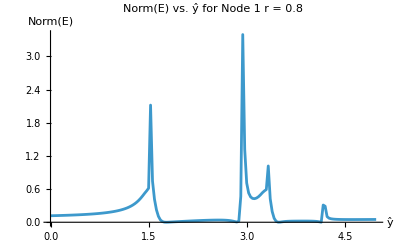

Evaluation time: 35.066831

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat1Array=Range[0,5,0.03];
Δ1NormArray=Table[Δ1Norm[κ]/.{yHat->yHat1Array[[i]]},{i,1,Length@yHat1Array}];
ENorm1Array=Table[NIntegrate[Δ1NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat1Array}];

ListPlot[Transpose@{yHat1Array,ENorm1Array},Joined->True,PlotRange->All,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 1\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

### Node 0

```mathematica
𝔸0[κ_]=1+γ01 Cos[κ]+γ02 Cos[2 κ];
𝔹0[κ_]=γ01 Sin[κ]+γ02 Sin[2 κ];
ℂ0[κ_]=a00+a01 Cos[κ]+a02 Cos[2 κ]+a03 Cos[3 κ]+a04 Cos[4 κ]+a05 Cos[5 κ]+a06 Cos[6 κ]+a07 Cos[7 κ]+a08 Cos[8 κ];
𝔻0[κ_]=a01 Sin[κ]+a02 Sin[2 κ]+a03 Sin[3 κ]+a04 Sin[4 κ]+a05 Sin[5 κ]+a06 Sin[6 κ]+a07 Sin[7 κ]+a08 Sin[8 κ];
κBar0Re[κ_]=(𝔸0[κ]*𝔻0[κ]-𝔹0[κ]*ℂ0[κ])/((𝔸0[κ])^2+(𝔹0[κ])^2);
κBar0Im[κ_]=(-𝔸0[κ]*ℂ0[κ]-𝔹0[κ]*𝔻0[κ])/((𝔸0[κ])^2+(𝔹0[κ])^2);
κBar0Norm[κ_]=Abs[κBar0Re[κ]+I*κBar0Im[κ]];
```

```mathematica
Δ0Re[κ_]=(κ*((𝔸0[κ])^2+(𝔹0[κ])^2)-(𝔸0[κ]*𝔻0[κ]-𝔹0[κ]*ℂ0[κ]))^2;
Δ0Im[κ_]=(0*((𝔸0[κ])^2+(𝔹0[κ])^2)-(-𝔸0[κ]*ℂ0[κ]-𝔹0[κ]*𝔻0[κ]))^2;
Δ0Norm[κ_]=(κ-κBar0Norm[κ])^2;
```

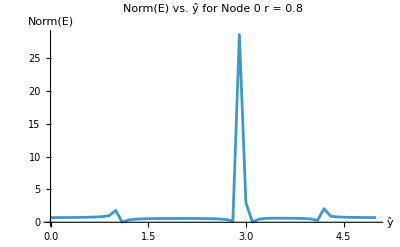

Evaluation time: 138.323874

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat0Array=Range[0,5,0.1];
Δ0NormArray=Table[Δ0Norm[κ]/.{yHat->yHat0Array[[i]]},{i,1,Length@yHat0Array}];
ENorm0Array=Table[NIntegrate[Δ0NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat0Array}];

ListPlot[Transpose@{yHat0Array,ENorm0Array},Joined->True,PlotRange->All,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 0\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

## Spectral Function

### Node 3

```mathematica
Clear[yHat]
SF3Re[κ_,yHat_]=κBar3Re[κ];
SF3Im[κ_,yHat_]=κBar3Im[κ];
SF3Norm[κ_,yHat_]=κBar3Norm[κ];
```

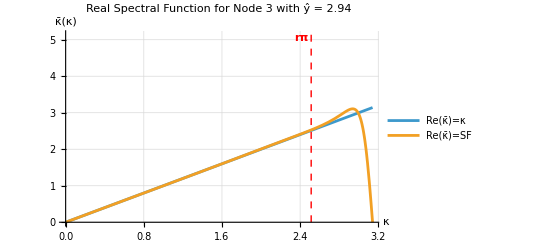

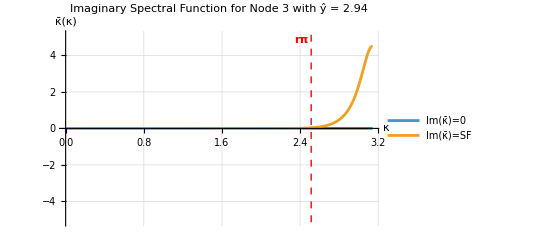

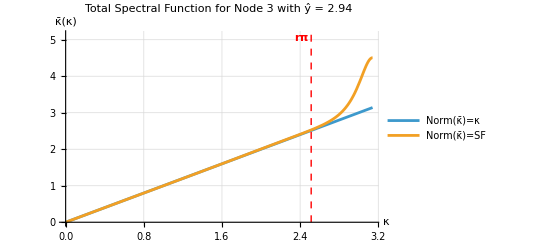

```mathematica
r=0.8;
yHat3List={(*1*)2.94,(*2*)4.41};
yHat=yHat3List[[1]];
Plot[{κ,SF3Re[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 3 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
Plot[{0,SF3Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 3 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ,SF3Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 3 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
```

### Node 2

```mathematica
Clear[yHat]
SF2Re[κ_,yHat_]=κBar2Re[κ];
SF2Im[κ_,yHat_]=κBar2Im[κ];
SF2Norm[κ_,yHat_]=κBar2Norm[κ];
```

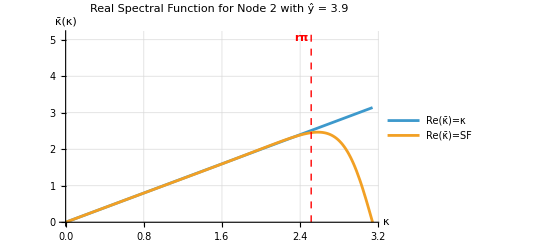

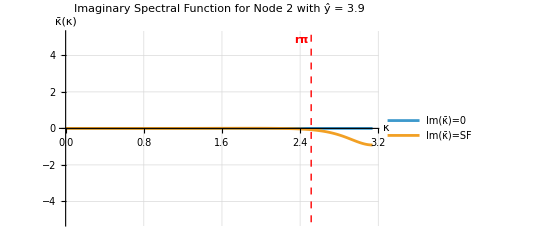

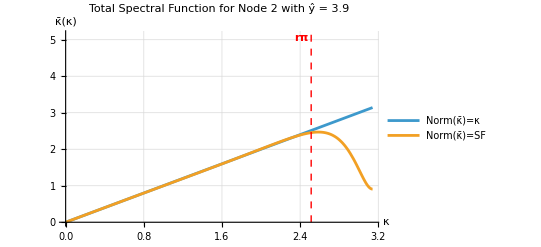

```mathematica
r=0.8;
yHat2List={(*1*)2.07,(*2*)2.85,(*3*)3.90,(*4*)4.14};
yHat=yHat2List[[3]];
Plot[{κ,SF2Re[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
Plot[{0,SF2Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ,SF2Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
```

### Node 1

```mathematica
Clear[yHat]
SF1Re[κ_,yHat_]=κBar1Re[κ];
SF1Im[κ_,yHat_]=κBar1Im[κ];
SF1Norm[κ_,yHat_]=κBar1Norm[κ];
```

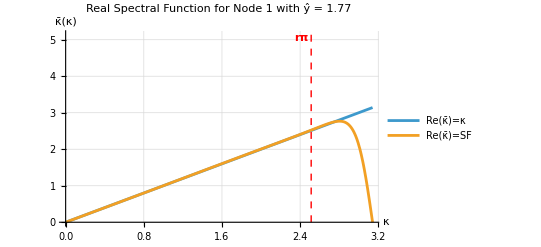

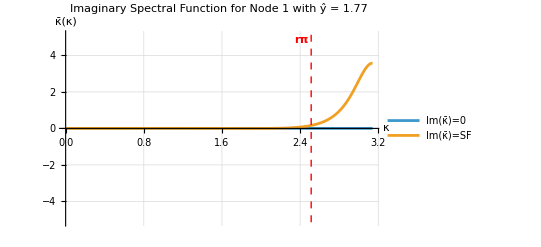

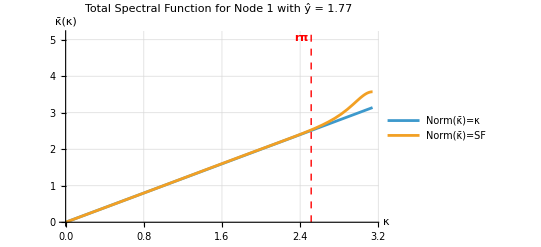

```mathematica
r=0.8;
yHat1List={(*1*)1.77,(*2*)2.85,(*3*)3.48,(*4*)4.14};
yHat=yHat1List[[1]];
Plot[{κ,SF1Re[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
Plot[{0,SF1Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ,SF1Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
```

### Node 0

```mathematica
Clear[yHat]
SF0Re[κ_,yHat_]=κBar0Re[κ];
SF0Im[κ_,yHat_]=κBar0Im[κ];
SF0Norm[κ_,yHat_]=κBar0Norm[κ];
```

```mathematica
r=0.8;
yHat0List={(*1*)1.1,(*2*)2.8,(*3*)3.1,(*4*)4.1};
yHat=yHat0List[[1]];
Plot[{κ,SF0Re[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
Plot[{0,SF0Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ,SF0Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
```

$Aborted

$Aborted

$Aborted

## Output Coefficients

### ŷ Definitions

```mathematica
Clear[yHat,yHat3,yHat2,yHat1,yHat0]

yHat3List={(*1*)2.94,(*2*)4.41};
yHat2List={(*1*)2.07,(*2*)2.85,(*3*)3.90,(*4*)4.14};
yHat1List={(*1*)1.77,(*2*)2.85,(*3*)3.48,(*4*)4.14};
yHat0List={(*1*)1.1,(*2*)2.8,(*3*)3.1,(*4*)4.1};

yHat0=yHat0List[[2]];
yHat2=yHat2List[[3]];
yHat1=yHat1List[[1]];
yHat3=yHat3List[[2]];
```

### Define Coefficients

```mathematica
Clear[γ33,γ31,γ32,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38]
Clear[γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28]
Clear[γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08]

{γ33val,γ31val,γ32val,γ34val,γ35val,a30val,a31val,a32val,a33val,a34val,a35val,a36val,a37val,a38val}=(1/γ33*{γ33,γ31,γ32,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38}/.bdCoeffs3)/.{yHat->yHat3};
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val,a27val,a28val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val,a17val,a18val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val,a07val,a08val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08}/.bdCoeffs0)/.{yHat->yHat0};
```

### Luke Output

```mathematica
interiorLuke=interiorCoeffsB6/.{a1->a,a2->b,a3->c,a4->d};
boundaryLuke={α12->γ01val,β12->γ02val,α21->γ10val,α22->γ12val,β22->γ13val,β31->γ20val,α31->γ21val,α32->γ23val,β32->γ24val,β41->γ31val,α41->γ32val,α42->γ34val,β42->γ35val,a1->a00val,b1->a01val,c1->a02val,d1->a03val,e1->a04val,f1->a05val,g1->a06val,h1->a07val,i1->a08val,a2->a10val,b2->a11val,c2->a12val,d2->a13val,e2->a14val,f2->a15val,g2->a16val,h2->a17val,i2->a18val,a3->a20val,b3->a21val,c3->a22val,d3->a23val,e3->a24val,f3->a25val,g3->a26val,h3->a27val,i3->a28val,a4->a30val,b4->a31val,c4->a32val,d4->a33val,e4->a34val,f4->a35val,g4->a36val,h4->a37val,i4->a38val};
coeffLuke=Flatten[Join[interiorLuke,boundaryLuke]]
```

{α→0.590671,β→0.100051,a→0.637598,b→0.263284,c→0.00934037,d→-0.000366182,α12→-4.32211,β12→-5.57556,α21→0.0635983,α22→2.82014,β22→1.60377,β31→0.00255969,α31→0.196928,α32→1.41087,β32→0.502926,β41→0.0702506,α41→0.464554,α42→0.752869,β42→0.160931,a1→1.55106,b1→5.26786,c1→-4.34804,d1→-3.20761,e1→1.02947,f1→-0.407478,g1→0.149107,h1→-0.039574,i1→0.00520379,a2→-0.231725,b2→-1.85059,c2→-0.737401,d2→2.42428,e2→0.455903,f2→-0.0715549,g2→0.0127828,h2→-0.00184243,i2→0.00014704,a3→-0.0328893,b3→-0.460451,c3→-0.965597,d3→0.40664,e3→0.96315,f3→0.0989628,g3→-0.0110416,h3→0.0013252,i3→-0.0000995358,a4→-0.010119,b4→-0.179084,c4→-0.601477,d4→-0.249031,e4→0.636135,f4→0.38494,g4→0.0199015,h4→-0.001341,i4→0.0000757937}

### Nate Output

```mathematica
interiorNate=interiorCoeffsB6;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,γ31->γ31val,γ32->γ32val,γ34->γ34val,γ35->γ35val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a07->a07val,a08->a08val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a17->a17val,a18->a18val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val,a27->a27val,a28->a28val,a30->a30val,a31->a31val,a32->a32val,a33->a33val,a34->a34val,a35->a35val,a36->a36val,a37->a37val,a38->a38val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]]
```

{α→0.590671,β→0.100051,a1→0.637598,a2→0.263284,a3→0.00934037,a4→-0.000366182,γ01→-4.32211,γ02→-5.57556,γ10→0.0635983,γ12→2.82014,γ13→1.60377,γ20→0.00255969,γ21→0.196928,γ23→1.41087,γ24→0.502926,γ31→0.0702506,γ32→0.464554,γ34→0.752869,γ35→0.160931,a00→1.55106,a01→5.26786,a02→-4.34804,a03→-3.20761,a04→1.02947,a05→-0.407478,a06→0.149107,a07→-0.039574,a08→0.00520379,a10→-0.231725,a11→-1.85059,a12→-0.737401,a13→2.42428,a14→0.455903,a15→-0.0715549,a16→0.0127828,a17→-0.00184243,a18→0.00014704,a20→-0.0328893,a21→-0.460451,a22→-0.965597,a23→0.40664,a24→0.96315,a25→0.0989628,a26→-0.0110416,a27→0.0013252,a28→-0.0000995358,a30→-0.010119,a31→-0.179084,a32→-0.601477,a33→-0.249031,a34→0.636135,a35→0.38494,a36→0.0199015,a37→-0.001341,a38→0.0000757937}

## Eigenvalue Spectral Analysis

### Modified Boundary Coefficients for Eigenvalue Analysis

```mathematica
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate),
γ31Bar->(γ31/.coeffNate),
γ32Bar->(γ32/.coeffNate),
γ34Bar->(γ34/.coeffNate),
γ35Bar->(γ35/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,8}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,8}]/.coeffNate;
RHSBars3=Table[
ToExpression@StringJoin["a3",ToString@j,"Bar"]->(ToExpression@StringJoin["a3",ToString@j]),
{j,1,8}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2,RHSBars3]
```

{γ12Bar→2.49023,γ13Bar→1.25798,γ21Bar→0.176741,γ23Bar→1.5187,γ24Bar→0.567319,γ31Bar→0.0702506,γ32Bar→0.464554,γ34Bar→0.752869,γ35Bar→0.160931,a11Bar→-1.71437,a12Bar→-0.361503,a13Bar→2.06159,a14Bar→0.306249,a15Bar→-0.0357995,a16Bar→0.00258836,a17Bar→0.000528996,a18Bar→-0.000144259,a21Bar→-0.435387,a22Bar→-1.05575,a23Bar→0.34864,a24Bar→1.06577,a25Bar→0.114882,a26Bar→-0.0130357,a27Bar→0.00157853,a28Bar→-0.000118956,a31Bar→-0.179084,a32Bar→-0.601477,a33Bar→-0.249031,a34Bar→0.636135,a35Bar→0.38494,a36Bar→0.0199015,a37Bar→-0.001341,a38Bar→0.0000757937}

### Build Modified Matrices (needs cleaning badly)

```mathematica
Clear[LHS,RHS]
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=4;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],

If[(i==3&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==3&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==3&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==3&&j==5),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i-2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}]

k=9; (*Size*)
MatrixForm@LHS[k]

MatrixForm@(LHS[k]/.coeffNate)/.barCoeffs
```

(1 | γ12Bar | γ13Bar | 0 | 0 | 0 | 0 | 0 | 0
γ21Bar | 1 | γ23Bar | γ24Bar | 0 | 0 | 0 | 0 | 0
γ31Bar | γ32Bar | 1 | γ34Bar | γ35Bar | 0 | 0 | 0 | 0
0 | β | α | 1 | α | β | 0 | 0 | 0
0 | 0 | β | α | 1 | α | β | 0 | 0
0 | 0 | 0 | γ35 | γ34 | 1 | γ32 | γ31 | 0
0 | 0 | 0 | 0 | γ24 | γ23 | 1 | γ21 | γ20
0 | 0 | 0 | 0 | 0 | γ13 | γ12 | 1 | γ10
0 | 0 | 0 | 0 | 0 | 0 | γ02 | γ01 | 1)

(1 | 2.49023 | 1.25798 | 0 | 0 | 0 | 0 | 0 | 0
0.176741 | 1 | 1.5187 | 0.567319 | 0 | 0 | 0 | 0 | 0
0.0702506 | 0.464554 | 1 | 0.752869 | 0.160931 | 0 | 0 | 0 | 0
0 | 0.100051 | 0.590671 | 1 | 0.590671 | 0.100051 | 0 | 0 | 0
0 | 0 | 0.100051 | 0.590671 | 1 | 0.590671 | 0.100051 | 0 | 0
0 | 0 | 0 | 0.160931 | 0.752869 | 1 | 0.464554 | 0.0702506 | 0
0 | 0 | 0 | 0 | 0.502926 | 1.41087 | 1 | 0.196928 | 0.00255969
0 | 0 | 0 | 0 | 0 | 1.60377 | 2.82014 | 1 | 0.0635983
0 | 0 | 0 | 0 | 0 | 0 | -5.57556 | -4.32211 | 1)

```mathematica
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,
If[(i==1&&j==7),a17Bar,
If[(i==1&&j==8),a18Bar,

If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,
If[(i==2&&j==7),a27Bar,
If[(i==2&&j==8),a28Bar,

If[(i==3&&j==1),a31Bar,
If[(i==3&&j==2),a32Bar,
If[(i==3&&j==3),a33Bar,
If[(i==3&&j==4),a34Bar,
If[(i==3&&j==5),a35Bar,
If[(i==3&&j==6),a36Bar,
If[(i==3&&j==7),a37Bar,
If[(i==3&&j==8),a38Bar,

If[(i==k&&j==k),-a00,
If[(i==k&&j==k-1),-a01,
If[(i==k&&j==k-2),-a02,
If[(i==k&&j==k-3),-a03,
If[(i==k&&j==k-4),-a04,
If[(i==k&&j==k-5),-a05,
If[(i==k&&j==k-6),-a06,
If[(i==k&&j==k-7),-a07,
If[(i==k&&j==k-8),-a08,
If[(i==k-1&&j==k),-a10,
If[(i==k-1&&j==k-1),-a11,
If[(i==k-1&&j==k-2),-a12,
If[(i==k-1&&j==k-3),-a13,
If[(i==k-1&&j==k-4),-a14,
If[(i==k-1&&j==k-5),-a15,
If[(i==k-1&&j==k-6),-a16,
If[(i==k-1&&j==k-7),-a17,
If[(i==k-1&&j==k-8),-a18,
If[(i==k-2&&j==k),-a20,
If[(i==k-2&&j==k-1),-a21,
If[(i==k-2&&j==k-2),-a22,
If[(i==k-2&&j==k-3),-a23,
If[(i==k-2&&j==k-4),-a24,
If[(i==k-2&&j==k-5),-a25,
If[(i==k-2&&j==k-6),-a26,
If[(i==k-2&&j==k-7),-a27,
If[(i==k-2&&j==k-8),-a28,
If[(i==k-3&&j==k),-a30,
If[(i==k-3&&j==k-1),-a31,
If[(i==k-3&&j==k-2),-a32,
If[(i==k-3&&j==k-3),-a33,
If[(i==k-3&&j==k-4),-a34,
If[(i==k-3&&j==k-5),-a35,
If[(i==k-3&&j==k-6),-a36,
If[(i==k-3&&j==k-7),-a37,
If[(i==k-3&&j==k-8),-a38,


If[i-4==j,-a4,
If[i-3==j,-a3,
If[i-2==j,-a2,
If[i-1==j, -a1,
If[i==j, 0,
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
If[i+4==j,a4,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}]

k=11; (*Size*)
MatrixForm@RHS[k]

MatrixForm@(RHS[k]/.coeffNate)/.barCoeffs
```

(a11Bar | a12Bar | a13Bar | a14Bar | a15Bar | a16Bar | a17Bar | a18Bar | 0 | 0 | 0
a21Bar | a22Bar | a23Bar | a24Bar | a25Bar | a26Bar | a27Bar | a28Bar | 0 | 0 | 0
a31Bar | a32Bar | a33Bar | a34Bar | a35Bar | a36Bar | a37Bar | a38Bar | 0 | 0 | 0
-a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | a4 | 0 | 0 | 0
-a4 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | a4 | 0 | 0
0 | -a4 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | a4 | 0
0 | 0 | -a4 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | a4
0 | 0 | -a38 | -a37 | -a36 | -a35 | -a34 | -a33 | -a32 | -a31 | -a30
0 | 0 | -a28 | -a27 | -a26 | -a25 | -a24 | -a23 | -a22 | -a21 | -a20
0 | 0 | -a18 | -a17 | -a16 | -a15 | -a14 | -a13 | -a12 | -a11 | -a10
0 | 0 | -a08 | -a07 | -a06 | -a05 | -a04 | -a03 | -a02 | -a01 | -a00)

(-1.71437 | -0.361503 | 2.06159 | 0.306249 | -0.0357995 | 0.00258836 | 0.000528996 | -0.000144259 | 0 | 0 | 0
-0.435387 | -1.05575 | 0.34864 | 1.06577 | 0.114882 | -0.0130357 | 0.00157853 | -0.000118956 | 0 | 0 | 0
-0.179084 | -0.601477 | -0.249031 | 0.636135 | 0.38494 | 0.0199015 | -0.001341 | 0.0000757937 | 0 | 0 | 0
-0.00934037 | -0.263284 | -0.637598 | 0 | 0.637598 | 0.263284 | 0.00934037 | -0.000366182 | 0 | 0 | 0
0.000366182 | -0.00934037 | -0.263284 | -0.637598 | 0 | 0.637598 | 0.263284 | 0.00934037 | -0.000366182 | 0 | 0
0 | 0.000366182 | -0.00934037 | -0.263284 | -0.637598 | 0 | 0.637598 | 0.263284 | 0.00934037 | -0.000366182 | 0
0 | 0 | 0.000366182 | -0.00934037 | -0.263284 | -0.637598 | 0 | 0.637598 | 0.263284 | 0.00934037 | -0.000366182
0 | 0 | -0.0000757937 | 0.001341 | -0.0199015 | -0.38494 | -0.636135 | 0.249031 | 0.601477 | 0.179084 | 0.010119
0 | 0 | 0.0000995358 | -0.0013252 | 0.0110416 | -0.0989628 | -0.96315 | -0.40664 | 0.965597 | 0.460451 | 0.0328893
0 | 0 | -0.00014704 | 0.00184243 | -0.0127828 | 0.0715549 | -0.455903 | -2.42428 | 0.737401 | 1.85059 | 0.231725
0 | 0 | -0.00520379 | 0.039574 | -0.149107 | 0.407478 | -1.02947 | 3.20761 | 4.34804 | -5.26786 | -1.55106)

### Plot Eigenvalue Spectra

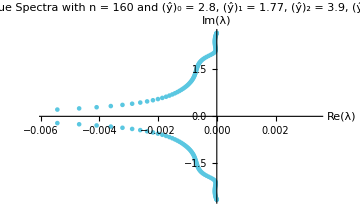

```mathematica
k=160;
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2],", (ŷ)_3 = ",ToString[yHat3]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat1/5,yHat2/5,yHat3/5]]
```

## Dendro Output

### Hide

```mathematica
derivativeOrder=1;
interiorOrder=n;
totalBoundRows=numBoundaryRows;
freeInteriorParameters={};
freeBoundaryParameters={};
RHSInteriorList=RHSPars;
interiorParametersValues=interiorCoeffsB6/.{α->alpha,β->beta};
boundaryParametersValues=boundaryLuke/.{α12->gamma01,β12->gamma02,α21->gamma10,α22->gamma12,β22->gamma13,β31->gamma20,α31->gamma21,α32->gamma23,β32->gamma24,β41->gamma31,α41->gamma32,α42->gamma34,β42->gamma35,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,h1->a07,i1->a08,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,h2->a17,i2->a18,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26,h3->a27,i3->a28,a4->a30,b4->a31,c4->a32,d4->a33,e4->a34,f4->a35,g4->a36,h4->a37,i4->a38};
LHSBoundaryList={gamma01,gamma02,gamma10,gamma12,gamma13,gamma20,gamma21,gamma23,gamma24,gamma31,gamma32,gamma34,gamma35};
RHSBoundaryList={a00,a01,a02,a03,a04,a05,a06,a07,a08,a10,a11,a12,a13,a14,a15,a16,a17,a18,a20,a21,a22,a23,a24,a25,a26,a27,a28,a30,a31,a32,a33,a34,a35,a36,a37,a38};
(*Don't need to mess with these until we incorporate this procedure with James's filtering*)
filterIntCoeff;
filterBoundCoeff;
filterIntParam;
filterBoundParam;
filtering=False;
(*boundary={α12->γ01,β12->γ02,α21->γ10,α22->γ12,β22->γ13,β31->γ20,α31->γ21,α32->γ23,β32->γ24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};*)
```

```mathematica
(*****************Print coefficients in Dendro-GR Format*****************)
If[derivativeOrder==1,
LHSName="P1";
RHSName="Q1";
nth="1st";
coeffs="D_coeffs";
order="First",
If[derivativeOrder==2,
LHSName="P2";
RHSName="Q2";
nth="2nd";
coeffs="D_coeffs";
order="Second"]];
If[LHSBandCount==3,
LHSStructure="T",
If[LHSBandCount==5,
LHSStructure="P"]];

(*Convert Mathematica expression syntax to C/C++ expression syntax*)
convertToCCode[expr_]:=Module[{str},str=ToString[expr,InputForm];
(*Add ".0" to standalone integers but not to variables with numbers*)
(*Formatting adjustments to match C/C++ syntax*)str=StringReplace[str,{" "->"","*"->" * ","/"->" / ","+"->" + ","-"->" - ","^"->" ^ "}];
str]
(*Function to generate the line of C/C++ code to define the fixed variables*)
generateCAssignment[rule_]:=Module[{variable,expression,cCode,cAssignment},
variable=ToString[rule[[1]]];
expression=rule[[2]];
cCode=convertToCCode[expression];
cAssignment="double "<>variable<>" = "<>cCode<>";";
cAssignment
]






(*Initial Block*)
initialBlock=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order"}];
initialBlock2=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order","Filtered"}];

(*Free Parameters Block*)
freeParameters=Join[freeInteriorParameters,freeBoundaryParameters];
numFreePars=Length[freeParameters];
alphaPrint=StringReplace[generateCAssignment[Select[interiorParametersValues,#[[1]]===alpha&][[1]]],"alpha"->"alpha0"];
freeParPrints={};
If[numFreePars>0,
For[i=1,i<=numFreePars,i++,
AppendTo[freeParPrints,StringJoin[{"\n\t\tdouble ",ToString[freeParameters[[i]]]," = ",coeffs,"[",ToString[i],"];"}]]]]
freeParametersBlock=StringJoin[{"\t",alphaPrint,"\n\t\tdouble alpha = alpha0 + ",coeffs,"[0];",freeParPrints}];

(*Filter*)
freeParPrints2={};
freeParametersBlock2=StringJoin[{"\t","\n\t\tdouble alpha = ","F_coeffs","[0];",If[LHSBandCount==5,StringJoin["\n\t\tdouble beta = ","F_coeffs","[1];"],""]}];

(*Fixed Parameters Block*)
(*Create a list of the solved fixed parameters in C/C++ syntax*)
interiorParametersValues3=DeleteCases[interiorParametersValues,Rule[alpha,_]];
interiorParameterPrints=Table[
generateCAssignment[interiorParametersValues3[[i]]],
{i,1,Length[interiorParametersValues]-1}
];
boundaryParameterPrints=Table[
generateCAssignment[boundaryParametersValues[[i]]],
{i,1,Length[boundaryParametersValues]}
];
(*For filtered coefficients*)
interiorParameterPrints2=Table[
generateCAssignment[filterIntCoeff[[i]]],
{i,1,Length[filterIntCoeff]}
];
boundaryParameterPrints2=Table[
generateCAssignment[filterBoundCoeff[[i]]],
{i,1,Length[filterBoundCoeff]}
];
(*Print the coefficients in a single block of text rather than individual lines*)
fixedParametersBlockD=StringJoin["\t\t",Riffle[Join[interiorParameterPrints,boundaryParameterPrints],"\n\t\t"]];
fixedParametersBlockD2=StringJoin["\t\t",Riffle[Join[interiorParameterPrints2,boundaryParameterPrints2],"\n\t\t"]];

(*Structure Block*)
(*LHS Boundary*)
PDiagBoundary="";
LHSRowList=ToExpression[GatherBy[LHSBoundaryList,StringDrop[ToString[#],5]~StringTake~1&]];
For[i=1,i<=Length[LHSRowList],i++,
If[i==1,PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t","{1.0, ",StringDrop[ToString[LHSRowList[[i]]],1],","]];
If[i==2,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1}]],1],","]]];
If[i==3,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{","0.0, ",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t",StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
If[i>=4,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],StringDrop[StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
];
(*LHS Filter Boundary*)
RDiagBoundary="";
For[i=1,i<=Length@filterBoundParam,i++,
If[i==1,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha, beta},"]];
];
If[i==2,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha 1.0, alpha, beta},"]];
];
If[i>=3,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],"alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],"beta, alpha, 1.0, alpha, beta},"]];
];
];

(*LHS Interior*)
If[LHSBandCount==3,
PDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
PDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];
(*LHS Filter Interior*)
If[LHSBandCount==3,
RDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
RDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];

(*RHS Boundary*)
QDiagBoundary="";
RHSRowList=ToExpression[GatherBy[RHSBoundaryList,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList],i++,QDiagBoundary=StringJoin[QDiagBoundary,"\n\t\t\t",ToString[RHSRowList[[i]]],","]]
(*RHS Filter Boundary*)
SDiagBoundary="";
RHSRowList2=ToExpression[GatherBy[filterBoundParam,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList2],i++,SDiagBoundary=StringJoin[SDiagBoundary,"\n\t\t\t",ToString[RHSRowList2[[i]]]]]

(*RHS Interior*)
QDiagInterior={};
len=(2*Length[RHSInteriorList]+1);
If[derivativeOrder==1,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[-RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"0.0"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]
],
If[derivativeOrder==2,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[-RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"t1"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]]]]

(*RHS Filter Interior*)
SDiagInterior={};
newFilterIntParam=Drop[filterIntParam,1];
len=(2*Length[newFilterIntParam]+1);
For[i=1,i<=len,i++,
If[i<=Length[newFilterIntParam],PrependTo[SDiagInterior,ToString[newFilterIntParam[[i]]]<>"/"<>ToString[2]<>".0"]];
If[i==(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,"a0"]];
If[i>(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,ToString[newFilterIntParam[[i-Length[newFilterIntParam]-1]]]<>"/"<>ToString[2]<>".0"]]
]


PDiagBoundaryStr=StringDrop[StringDrop[PDiagBoundary,1],-1];
PDiagInteriorStr=StringDrop[StringDrop[PDiagInterior,1],-1];
RDiagBoundaryStr=StringDrop[StringDrop[RDiagBoundary,1],-1];
RDiagInteriorStr=StringDrop[StringDrop[RDiagInterior,1],-1];
QDiagBoundaryStr=StringDrop[StringDrop[QDiagBoundary,1],-1];
QDiagInteriorStr=StringDrop[StringDrop[ToString[QDiagInterior],1],-1];
SDiagBoundaryStr=StringDrop[SDiagBoundary,1];
SDiagInteriorStr=StringDrop[StringDrop[ToString[SDiagInterior],1],-1];

(*Subscript[t, 1] is the middle RHS Interior Coefficient for Second Derivatives*)
t1List={};
For[i=1,i<=Length[RHSInteriorList],i++,
AppendTo[t1List,ToString[RHSInteriorList[[i]]]<>"/"<>ToString[i^2]<>".0"]
];
If[derivativeOrder==1,
t1="",
If[derivativeOrder==2,
t1=StringJoin["-2.0 * ("<>StringDrop[StringDrop[ToString[t1List],1],-1]<>")"]]];


If[filtering,
filterFinalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock2,"(\n","\tconst std::vector<double>& ","F_coeffs",") {\n","\t",freeParametersBlock2,"\n\n",fixedParametersBlockD2,"\n\n","\t\t// boundary elements for R matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","R","DiagBoundary{\n",RDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for R matrix for ",nth," derivative\n","\t\tstd::vector<double> ","R","DiagInterior{\n","\t\t\t",RDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for S matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","S","DiagBoundary\n",SDiagBoundaryStr,"\n","\t\t;\n\n","\t\t// diagonal elements for S matrix for ",nth," derivative\n","\t\tstd::vector<double> ","S","DiagInterior{\n","\t\t\t",SDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t","R","DiagInterior, ","S","DiagInterior, ","S","DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}"}];
]

finalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock,"(\n","\tconst std::vector<double>& ",coeffs,") {\n","\t",freeParametersBlock,"\n\n",fixedParametersBlockD,"\n\n","\t\t// boundary elements for P matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",LHSName,"DiagBoundary{\n",PDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for P matrix for ",nth," derivative\n","\t\tstd::vector<double> ",LHSName,"DiagInterior{\n","\t\t\t",PDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",RHSName,"DiagBoundary{\n",QDiagBoundaryStr,"\n","\t\t};\n\n",If[derivativeOrder==1,t1,If[derivativeOrder==2,"\t\tdouble t1 = "<>t1<>";\n"]],"\t\t// diagonal elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<double> ",RHSName,"DiagInterior{\n","\t\t\t",QDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t",LHSName,"DiagInterior, ",LHSName,"DiagBoundary, ",RHSName,"DiagInterior, ",RHSName,"DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}",If[filtering,"\n\n"<>filterFinalBlock,""]}];
```

GatherBy::list: List expected at position 1 in GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&].

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Drop::drop: Cannot drop positions 1 through 1 in filterIntParam.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

StringDrop::drop: Cannot drop positions 1 through 1 in "".

### Show

```mathematica
outExt="h";
(*Print header*)
Print[Style["Dendro-Ready Coefficients (Copied to clipboard):",Bold,FontSize->24]];
Print[finalBlock];
(*Copy the block of text to the user's clipboard*)
CopyToClipboard[finalBlock];

(*Save to output file*)
fileName=StringJoin[{"BYU_B6","_yHat0_",ToString[yHat0],"_yHat1_",ToString[yHat1],"_yHat2_",ToString[yHat2],"_yHat3_",ToString[yHat3],".",outExt}];
Export[fileName,finalBlock,"Text"];
Print[StringJoin[{"Saved to file: ",fileName}]]
```

Dendro-Ready Coefficients (Copied to clipboard):

MatrixDiagonalEntries* BYUDerivsP6R4DiagonalsFirstOrder(
	const std::vector<double>& D_coeffs) {
		double alpha0 = 0.59067138684056;
		double alpha = alpha0 + D_coeffs[0];

		double beta = 0.10005088370852962;
		double a1 = 0.6375976953896195;
		double a2 = 0.26328410014665704;
		double a3 = 0.009340368066539819;
		double a4 =  - 0.0003661823333658686;
		double gamma01 =  - 4.322109393261724;
		double gamma02 =  - 5.5755623032462704;
		double gamma10 = 0.06359831196568691;
		double gamma12 = 2.82014372172214;
		double gamma13 = 1.6037741239491015;
		double gamma20 = 0.0025596862116305068;
		double gamma21 = 0.1969279489688115;
		double gamma23 = 1.4108678913225454;
		double gamma24 = 0.5029255290717922;
		double gamma31 = 0.07025062110344835;
		double gamma32 = 0.4645542135800324;
		double gamma34 = 0.7528690671365358;
		double gamma35 = 0.16093114285035592;
		double a00 = 1.5510642647107615;
		double a01 = 5.267857680340051;
		double a02 =  - 4.3480411989430605;
		double a03 =  - 3.207606006110041;
		double a04 = 1.0294658110203272;
		double a05 =  - 0.4074778190995032;
		double a06 = 0.149107468088866;
		double a07 =  - 0.039573994455802515;
		double a08 = 0.005203791878398847;
		double a10 =  - 0.23172503179038403;
		double a11 =  - 1.8505901778365845;
		double a12 =  - 0.7374009503732573;
		double a13 = 2.4242807371606974;
		double a14 = 0.4559028729033105;
		double a15 =  - 0.07155488500604189;
		double a16 = 0.012782828649694758;
		double a17 =  - 0.0018424333531757526;
		double a18 = 0.00014703964154050378;
		double a20 =  - 0.032889268707092356;
		double a21 =  - 0.4604509459271151;
		double a22 =  - 0.9655972458152848;
		double a23 = 0.40664002183204895;
		double a24 = 0.9631504961022612;
		double a25 = 0.09896284470196014;
		double a26 =  - 0.01104156925989071;
		double a27 = 0.0013252028908141461;
		double a28 =  - 0.0000995358176917796;
		double a30 =  - 0.010119046760075301;
		double a31 =  - 0.1790843523615154;
		double a32 =  - 0.6014769664170929;
		double a33 =  - 0.24903064817934578;
		double a34 = 0.6361348280702476;
		double a35 = 0.38493991244461156;
		double a36 = 0.019901479948727003;
		double a37 =  - 0.0013410004725808492;
		double a38 = 0.00007579372703160374;

		// boundary elements for P matrix for 1st derivative
		std::vector<std::vector<double>> P1DiagBoundary{
			{1.0, gamma01, gamma02},
			{gamma10, 1.0, gamma12, gamma13},
			{gamma20, gamma21, 1.0, gamma23, gamma24},
			{0.0, gamma31, gamma32, 1.0, gamma34, gamma35}
		};

		// diagonal elements for P matrix for 1st derivative
		std::vector<double> P1DiagInterior{
			beta, alpha, 1.0, alpha, beta
		};

		// boundary elements for Q matrix for 1st derivative
		std::vector<std::vector<double>> Q1DiagBoundary{
			{a00, a01, a02, a03, a04, a05, a06, a07, a08},
			{a10, a11, a12, a13, a14, a15, a16, a17, a18},
			{a20, a21, a22, a23, a24, a25, a26, a27, a28},
			{a30, a31, a32, a33, a34, a35, a36, a37, a38}
		};

		// diagonal elements for Q matrix for 1st derivative
		std::vector<double> Q1DiagInterior{
			-a4, -a3, -a2, -a1, 0.0, a1, a2, a3, a4
		};

		// store the entries for matrix creation
		MatrixDiagonalEntries* diagEntries = new
			MatrixDiagonalEntries{
				P1DiagInterior, P1DiagBoundary, Q1DiagInterior, Q1DiagBoundary
			};
		return diagEntries;
	}

Saved to file: BYU_B6_yHat0_2.8_yHat1_1.77_yHat2_3.9_yHat3_4.41.h

# P6 (C6) Scheme

## Initialization

The matrix system of equations we are solving for this scheme is:
	P=(1
γ_10
β
0
0 γ_01
1
α
γ_13
0 γ_02
γ_12
1
γ_12
γ_02 0
γ_13
α
1
γ_01 0
0
β
γ_10
1)
	Q=(a_00
a_10
-a_2
-a_14
-a_04 a_01
a_11
-a_1
-a_13
-a_03 a_02
a_12
0
-a_12
-a_02 a_03
a_13
a_1
-a_11
-a_01 a_04
a_14
a_2
-a_10
-a_00)

```mathematica
(*From KimInteriorOptimization.nb, one day to be merged with this one. Or I could DumpSave[] in that notebook and then Get[] here.*)
(*interiorCoeffsC6={α->0.4963477370017426,β->0.04075360091710232,a1->0.723439643221641,a2->0.15683084734860173};*)
Get["C6_interiorCoeffs.mx"]

(*If you have the .mx files in the same directory as this notebook, these will let you skip the long computation of defining bdCoeffs under the "Solve for Boundary Coefficients" section*)
Get["C6_bdCoeffs1.mx"];
Get["C6_bdCoeffs0.mx"];
```

## General Extrapolation Polynomial

For the P6 (C6) scheme, we have:
	LHSBandCount = 5
	n = 6
	freeInteriorPars = 1
	yDeriv = 6

```mathematica
(*User chooses these parameters, the rest is calculated from these*)
LHSBandCount=5; (*3 for tridiagonal, 5 for pentadiagonal*)
n=6; (*order of the scheme*)
freeInteriorPars=1; (*number of free parameters used for Kim's optimization on the interior*)
yDeriv=6; (*(d^n P)/dx^n(ŷ)=0 from Kim 2024 Eq. 10, this is n in that equation*) (*provide constraints on what the user can choose for this. Upper bound should be polynomialorder to prevent the matrix from being singular, and lower bound should be order·2 I think.*)

LHSPars=Switch[LHSBandCount,3,{α},5,{α,β}];
RHSPars=Table[ToExpression[StringJoin["a",ToString[i]]],{i,1,Ceiling[n/2]-Length@LHSPars+freeInteriorPars}];
numBoundaryRows=Length@RHSPars;
fOrder=(2*Length@RHSPars)+1;
fpOrder=LHSBandCount+(numBoundaryRows-(LHSBandCount-1)/2);
PolynomialOrder=fOrder+fpOrder;


rowf1=Join[{1},Table[0,{i,1,PolynomialOrder}]];
rowf=Table[Table[i^j,{j,0,PolynomialOrder}],{i,1,fOrder-1}];
rowfp1=Join[{0,1},Table[0,{i,2,PolynomialOrder}]];
rowfp=Table[Table[j i^(j-1),{j,0,PolynomialOrder}],{i,1,fpOrder-1}];
rowyHat=Join[Table[0,{i,1,yDeriv}],Table[(i!)/((i-yDeriv)!) yHat^(i-yDeriv),{i,yDeriv,PolynomialOrder}]];

matf=PrependTo[rowf,rowf1];
matfp=PrependTo[rowfp,rowfp1];
matfCombined=Join[matf,matfp];
LMat=AppendTo[matfCombined,rowyHat];

pVec=Table[ToExpression[StringJoin["p",ToString[i]]],{i,0,PolynomialOrder}];
fVec=Join[Table[ToExpression[StringJoin["f",ToString[i]]],{i,0,fOrder-1}],Table[ToExpression[StringJoin["fp",ToString[i]]],{i,0,fpOrder-1}],{0}];

pCoeffs=Solve[LMat.pVec==fVec,pVec][[1]];

yHatSingularities=(Transpose@Solve[Det[LMat]==0,yHat])[[1]]//N;
P[x_]=Total[Table[pVec[[i+1]]*x^i,{i,0,PolynomialOrder}]]/.pCoeffs;

Print["System:\n",MatrixForm[LMat]," ",MatrixForm[pVec]," = ",MatrixForm[fVec]]
Print["Singularities:\n",MatrixForm[yHatSingularities]]
(*Print["Coefficients:\n",MatrixForm[pCoeffs]]*)
```

System:
(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 4 | 8 | 16 | 32 | 64 | 128 | 256 | 512 | 1024
1 | 3 | 9 | 27 | 81 | 243 | 729 | 2187 | 6561 | 19683 | 59049
1 | 4 | 16 | 64 | 256 | 1024 | 4096 | 16384 | 65536 | 262144 | 1048576
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
0 | 1 | 4 | 12 | 32 | 80 | 192 | 448 | 1024 | 2304 | 5120
0 | 1 | 6 | 27 | 108 | 405 | 1458 | 5103 | 17496 | 59049 | 196830
0 | 1 | 8 | 48 | 256 | 1280 | 6144 | 28672 | 131072 | 589824 | 2621440
0 | 0 | 0 | 0 | 0 | 0 | 720 | 5040 yHat | 20160 yHat^2 | 60480 yHat^3 | 151200 yHat^4) (p0
p1
p2
p3
p4
p5
p6
p7
p8
p9
p10) = (f0
f1
f2
f3
f4
fp0
fp1
fp2
fp3
fp4
0)

Singularities:
(yHat→1.63853
yHat→2.36147
yHat→0.903336
yHat→3.09666)

## Solve for Boundary Coefficients

Goal:
	Solve a system of equations for bdCoeffsList1 in terms of the optimization free parameter ŷ
Variables:
	fVars1: List of f_i and f_i' variables that will appear in the shifted stencil for Node 1
	bdCoeffsList1: List of boundary coefficients that will appear in the shifted stencil for Node 1
	schemeShifted: The shifted scheme for Node 1
	schemeCentered: The centered scheme for Node 1 in terms of the extrapolation polynomial P(x)
		NOTE: To make the Collect[] process easier, we write these schemes as LHS-RHS=0 rather than the usual LHS=RHS.
	schemeNode2: The scheme for Node 2, which only depends on interiorCoeffsC6
	SOLfp4: The solution to Node 2’s scheme equation for f_4' in terms of fVars1
	eq: Scheme equation where the coefficient terms from schemeCentered and schemeShifted are set equal to each other
	coeffEqs1: System of equations with each of the coefficient terms equal to each other
	bdCoeffs1: Solution to the system of equations for bdCoeffsList1 in terms of ŷ
Process:
	1. Initialize the necessary equations.
	2. We want schemeShifted and schemeCentered to both be in terms of fVars1 with some coefficients. Due to the presence of P(x) terms in schemeCentered, it is in terms of fVars1 as well as f_4'. We eliminate the dependence on f_4' by using Node 2’s scheme to solve for f_4' in terms of fVars1.
	3. Now that schemeShifted and schemeCentered are both in terms of fVars1, we construct a system of equations by equating the coefficient in front of each term of fVars1 in schemeCentered with the corresponding coefficient in front of the same term in schemeShifted.
	4. We solve this system of equations for bdCoeffsList1 in terms of interiorCoeffsC6 (which are substituted in) and the optimization free parameter ŷ.
		NOTE: In the standard scheme approach, we set γ_11=1 to ensure the main diagonal of the LHS matrix is all 1’s. When solving this system of equations, we must include γ_11 so that bdCoeffsList1 and fVars1 have the same length since this allows us to find a unique solution to the system of equations. We apply the normal condition later on.
	5. OPTIONAL: We may save the variable bdCoeffs1 to a binary file in the current directory. This is helpful to avoid having to run this process multiple times, as it can become computationally expensive.
Differences:
	For Node 0, the entire process translates directly with a few changes. fVars, bdCoeffsList, schemeShifted, and schemeCentered all change, as we are considering the scheme for a different row, but the equations have the same structure. The main notable difference is in Step 2; In addition to substituting in the solution from Node 2 for f_4' in terms of the other fVars, we must also do the same for f_3' using Node 1.

### Node 1

```mathematica
(*----------STEP 1----------*)
fVars1={fp0,fp1,fp2,fp3,f0,f1,f2,f3,f4};
bdCoeffsList1={γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14};
schemeShifted=γ10 fp0+γ11 fp1+γ12 fp2+γ13 fp3-(a10 f0+a11 f1+a12 f2+a13 f3+a14 f4); (*==0*)
schemeCentered=β P'[-1]+α fp0+fp1+α fp2+β fp3-(-a2 P[-1]-a1 f0+a1 f2+a2 f3); (*==0*)

(*----------STEP 2----------*)
schemeNode2=β fp0+α fp1+fp2+α fp3+β fp4==-a2 f0-a1 f1+a1 f3+a2 f4;

SOLfp4=Solve[schemeNode2,fp4][[1,1]]/.interiorCoeffsC6;
schemeCentered=schemeCentered/.SOLfp4;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars1];

(*----------STEP 4----------*)
coeffEqs1=Table[Coefficient[eq,fVars1[[i]]]==0,{i,1,Length@fVars1}];
bdCoeffs1=(Solve[coeffEqs1,bdCoeffsList1][[1]])/.interiorCoeffsC6;

(*----------STEP 5----------*)
DumpSave["C6_bdCoeffs1.mx","Global`bdCoeffs1"]
```

{Global`bdCoeffs1}

### Node 0

```mathematica
(*----------STEP 1----------*)
fVars0={fp0,fp1,fp2,f0,f1,f2,f3,f4};
bdCoeffsList0={γ00,γ01,γ02,a00,a01,a02,a03,a04};
schemeShifted=γ00 fp0+γ01 fp1+γ02 fp2-(a00 f0+a01 f1+a02 f2+a03 f3+a04 f4); (*==0*)
schemeCentered=β P'[-2]+α P'[-1]+fp0+α fp1+β fp2-(-a2 P[-2]-a1 P[-1]+a1 f1+a2 f2); (*==0*)

(*----------STEP 2----------*)
schemeNode2=β fp0+α fp1+fp2+α fp3+β fp4==-a2 f0-a1 f1+a1 f3+a2 f4;
schemeNode1=γ10 fp0+γ11 fp1+γ12 fp2+γ13 fp3==a10 f0+a11 f1+a12 f2+a13 f3+a14 f4;

SOLfp4=Solve[schemeNode2,fp4][[1,1]]/.interiorCoeffsC6;
SOLfp3=Solve[schemeNode1,fp3][[1,1]]/.bdCoeffs1;
schemeCentered=schemeCentered/.SOLfp4/.SOLfp3;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars0];

(*----------STEP 4----------*)
coeffEqs0=Table[Coefficient[eq,fVars0[[i]]]==0,{i,1,Length@fVars0}];
bdCoeffs0=(Solve[coeffEqs0,bdCoeffsList0][[1]])/.interiorCoeffsC6;

(*----------STEP 5----------*)
DumpSave["C6_bdCoeffs0.mx","Global`bdCoeffs0"]
```

{Global`bdCoeffs0}

## Optimize ŷ

### Set and Normalize Coefficients

We normalize the coefficients so that the main diagonal of the LHS matrix is all 1’s, but we leave the coefficients in terms of the optimization free parameter ŷ so that we can optimize over it.

```mathematica
Clear[γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04]

{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14}=1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14}/.bdCoeffs1;
{γ00,γ01,γ02,a00,a01,a02,a03,a04}=1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04}/.bdCoeffs0;
```

### Node 1

```mathematica
𝔸1[κ_]=γ10+Cos[κ]+γ12 Cos[2 κ]+γ13 Cos[3 κ];
𝔹1[κ_]=Sin[κ]+γ12 Sin[2 κ]+γ13 Sin[3 κ];
ℂ1[κ_]=a10+a11 Cos[κ]+a12 Cos[2 κ]+a13 Cos[3 κ]+a14 Cos[4 κ];
𝔻1[κ_]=a11 Sin[κ]+a12 Sin[2 κ]+a13 Sin[3 κ]+a14 Sin[4 κ];
κBar1Re[κ_]=(𝔸1[κ]*𝔻1[κ]-𝔹1[κ]*ℂ1[κ])/((𝔸1[κ])^2+(𝔹1[κ])^2);
κBar1Im[κ_]=(-𝔸1[κ]*ℂ1[κ]-𝔹1[κ]*𝔻1[κ])/((𝔸1[κ])^2+(𝔹1[κ])^2);
κBar1Norm[κ_]=Abs[κBar1Re[κ]+I*κBar1Im[κ]];
```

```mathematica
Δ1Re[κ_]=(κ*((𝔸1[κ])^2+(𝔹1[κ])^2)-(𝔸1[κ]*𝔻1[κ]-𝔹1[κ]*ℂ1[κ]))^2;
Δ1Im[κ_]=(0*((𝔸1[κ])^2+(𝔹1[κ])^2)-(-𝔸1[κ]*ℂ1[κ]-𝔹1[κ]*𝔻1[κ]))^2;
Δ1Norm[κ_]=(κ-κBar1Norm[κ])^2;
```

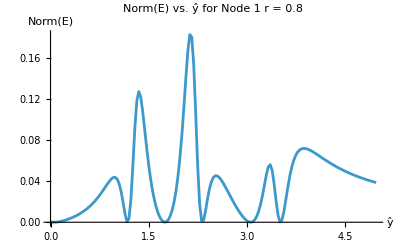

Evaluation time: 13.874044

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat1Array=Range[0,5,0.03];
Δ1NormArray=Table[Δ1Norm[κ]/.{yHat->yHat1Array[[i]]},{i,1,Length@yHat1Array}];
ENorm1Array=Table[NIntegrate[Δ1NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat1Array}];

ListPlot[Transpose@{yHat1Array,ENorm1Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 1\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

### Node 0

```mathematica
𝔸0[κ_]=1+γ01 Cos[κ]+γ02 Cos[2 κ];
𝔹0[κ_]=γ01 Sin[κ]+γ02 Sin[2 κ];
ℂ0[κ_]=a00+a01 Cos[κ]+a02 Cos[2 κ]+a03 Cos[3 κ]+a04 Cos[4 κ];
𝔻0[κ_]=a01 Sin[κ]+a02 Sin[2 κ]+a03 Sin[3 κ]+a04 Sin[4 κ];
κBar0Re[κ_]=(𝔸0[κ]*𝔻0[κ]-𝔹0[κ]*ℂ0[κ])/((𝔸0[κ])^2+(𝔹0[κ])^2);
κBar0Im[κ_]=(-𝔸0[κ]*ℂ0[κ]-𝔹0[κ]*𝔻0[κ])/((𝔸0[κ])^2+(𝔹0[κ])^2);
κBar0Norm[κ_]=Abs[κBar0Re[κ]+I*κBar0Im[κ]];
```

```mathematica
Δ0Re[κ_]=(κ*((𝔸0[κ])^2+(𝔹0[κ])^2)-(𝔸0[κ]*𝔻0[κ]-𝔹0[κ]*ℂ0[κ]))^2;
Δ0Im[κ_]=(0*((𝔸0[κ])^2+(𝔹0[κ])^2)-(-𝔸0[κ]*ℂ0[κ]-𝔹0[κ]*𝔻0[κ]))^2;
Δ0Norm[κ_]=(κ-κBar0Norm[κ])^2;
```

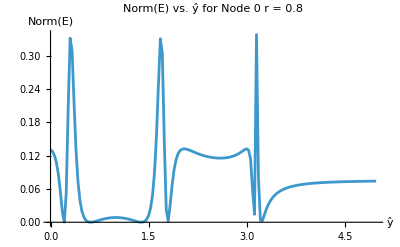

Evaluation time: 20.721425

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat0Array=Range[0,5,0.03];
Δ0NormArray=Table[Δ0Norm[κ]/.{yHat->yHat0Array[[i]]},{i,1,Length@yHat0Array}];
ENorm0Array=Table[NIntegrate[Δ0NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat0Array}];

ListPlot[Transpose@{yHat0Array,ENorm0Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 0\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

## Spectral Function

### Node 1

```mathematica
Clear[yHat]
SF1Re[κ_,yHat_]=κBar1Re[κ];
SF1Im[κ_,yHat_]=κBar1Im[κ];
SF1Norm[κ_,yHat_]=κBar1Norm[κ];
```

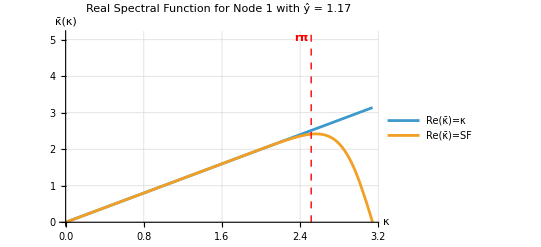

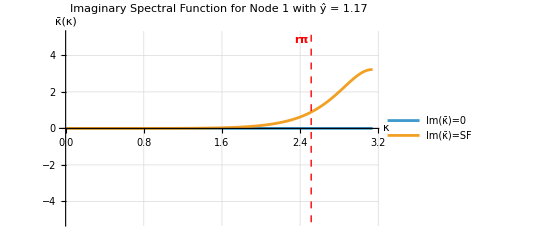

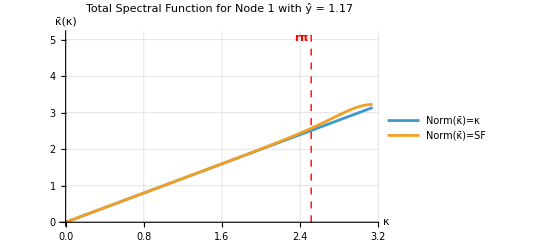

```mathematica
Clear[yHat]
r=0.8;
yHat1List={(*1*)1.17,(*2*)1.74,(*3*)2.31,(*4*)3.06,(*5*)3.51};
yHat=yHat1List[[1]];
Plot[{κ,SF1Re[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
Plot[{0,SF1Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ,SF1Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
```

### Node 0

```mathematica
Clear[yHat]
SF0Re[κ_,yHat_]=κBar0Re[κ];
SF0Im[κ_,yHat_]=κBar0Im[κ];
SF0Norm[κ_,yHat_]=κBar0Norm[κ];
```

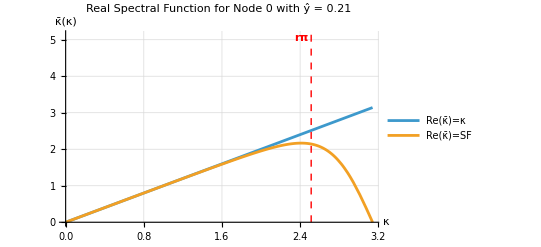

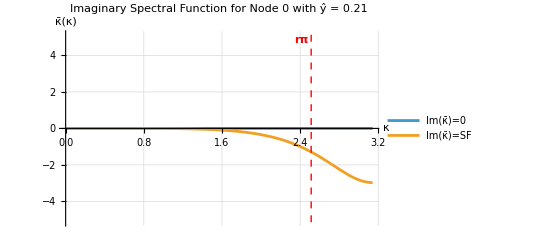

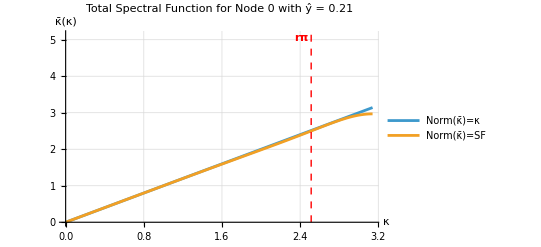

```mathematica
r=0.8;
yHat0List={(*1*)0.21,(*2*)0.60,(*3*)1.38,(*4*)1.80,(*5*)3.12,(*6*)3.24};
yHat=yHat0List[[1]];
Plot[{κ,SF0Re[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
Plot[{0,SF0Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ,SF0Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
```

## Output Coefficients

### ŷ Definitions

```mathematica
Clear[yHat,yHat1,yHat0]

yHat1List={(*1*)1.17,(*2*)1.74,(*3*)2.31,(*4*)3.06,(*5*)3.51};
yHat0List={(*1*)0.21,(*2*)0.60,(*3*)1.38,(*4*)1.80,(*5*)3.12,(*6*)3.24};

yHat1=yHat1List[[1]];
yHat0=yHat0List[[1]];
```

### Define Coefficients

```mathematica
Clear[γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04]

{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04}/.bdCoeffs0)/.{yHat->yHat0};
```

### Luke Output

```mathematica
interiorLuke=interiorCoeffsC6/.{a1->a,a2->b};
boundaryLuke={α12->γ01val,β12->γ02val,α21->γ10val,α22->γ12val,β22->γ13val,a1->a00val,b1->a01val,c1->a02val,d1->a03val,e1->a04val,a2->a10val,b2->a11val,c2->a12val,d2->a13val,e2->a14val};
coeffLuke=Flatten[Join[interiorLuke,boundaryLuke]]
```

{α→0.496348,β→0.0407536,a→0.72344,b→0.156831,α12→-3.53134,β12→-11.297,α21→0.161231,α22→0.474149,β22→-0.0389784,a1→-2.14192,b1→14.4741,c1→-8.29701,d1→-4.43234,e1→0.397139,a2→-0.543136,b2→-0.524,c2→1.07478,d2→-0.00140849,e2→-0.00623134}

### Nate Output

```mathematica
interiorNate=interiorCoeffsC6;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]]
```

{α→0.496348,β→0.0407536,a1→0.72344,a2→0.156831,γ01→-3.53134,γ02→-11.297,γ10→0.161231,γ12→0.474149,γ13→-0.0389784,a00→-2.14192,a01→14.4741,a02→-8.29701,a03→-4.43234,a04→0.397139,a10→-0.543136,a11→-0.524,a12→1.07478,a13→-0.00140849,a14→-0.00623134}

## Eigenvalue Spectral Analysis

### Modified Boundary Coefficients for Eigenvalue Analysis

```mathematica
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,4}]/.coeffNate;
intBars={α21Bar->((α-β*γ01)/(1-β*γ02)/.coeffNate),α23Bar->(α/(1-β*γ02)/.coeffNate),β24Bar->(β/(1-β*γ02)/.coeffNate),
a1Bar->((-a1-β*a01)/(1-β*γ02)/.coeffNate),a2Bar->((-β*a02)/(1-β*γ02)/.coeffNate),a3Bar->((a1-β*a03)/(1-β*γ02)/.coeffNate),a4Bar->((a2-β*a04)/(1-β*γ02)/.coeffNate)};

barCoeffs=Join[LHSBars,RHSBars1,intBars]
```

{γ12Bar→1.46274,γ13Bar→-0.0248372,a11Bar→-1.82091,a12Bar→1.53726,a13Bar→0.454465,a14Bar→-0.0447713,α21Bar→0.438418,α23Bar→0.339873,β24Bar→0.0279059,a1Bar→-0.899286,a2Bar→0.231535,a3Bar→0.619061,a4Bar→0.0963069}

### Build Modified Matrices (needs cleaning badly)

```mathematica
Clear[LHS,RHS]
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=2;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["α"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["α"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["β"<>ToString[i]<>ToString[j]<>"Bar"],

If[(i-2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}]

k=9; (*Size*)
MatrixForm@LHS[k]

MatrixForm@(LHS[k]/.coeffNate)/.barCoeffs
```

(1 | γ12Bar | γ13Bar | 0 | 0 | 0 | 0 | 0 | 0
α21Bar | 1 | α23Bar | β24Bar | 0 | 0 | 0 | 0 | 0
β | α | 1 | α | β | 0 | 0 | 0 | 0
0 | β | α | 1 | α | β | 0 | 0 | 0
0 | 0 | β | α | 1 | α | β | 0 | 0
0 | 0 | 0 | β | α | 1 | α | β | 0
0 | 0 | 0 | 0 | β | α | 1 | α | β
0 | 0 | 0 | 0 | 0 | γ13 | γ12 | 1 | γ10
0 | 0 | 0 | 0 | 0 | 0 | γ02 | γ01 | 1)

(1 | 1.46274 | -0.0248372 | 0 | 0 | 0 | 0 | 0 | 0
0.438418 | 1 | 0.339873 | 0.0279059 | 0 | 0 | 0 | 0 | 0
0.0407536 | 0.496348 | 1 | 0.496348 | 0.0407536 | 0 | 0 | 0 | 0
0 | 0.0407536 | 0.496348 | 1 | 0.496348 | 0.0407536 | 0 | 0 | 0
0 | 0 | 0.0407536 | 0.496348 | 1 | 0.496348 | 0.0407536 | 0 | 0
0 | 0 | 0 | 0.0407536 | 0.496348 | 1 | 0.496348 | 0.0407536 | 0
0 | 0 | 0 | 0 | 0.0407536 | 0.496348 | 1 | 0.496348 | 0.0407536
0 | 0 | 0 | 0 | 0 | -0.0389784 | 0.474149 | 1 | 0.161231
0 | 0 | 0 | 0 | 0 | 0 | -11.297 | -3.53134 | 1)

```mathematica
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=2;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,

If[(i==2&&j==1),a1Bar,
If[(i==2&&j==2),a2Bar,
If[(i==2&&j==3),a3Bar,
If[(i==2&&j==4),a4Bar,

If[(i==k&&j==k),-a00,
If[(i==k&&j==k-1),-a01,
If[(i==k&&j==k-2),-a02,
If[(i==k&&j==k-3),-a03,
If[(i==k&&j==k-4),-a04,
If[(i==k-1&&j==k),-a10,
If[(i==k-1&&j==k-1),-a11,
If[(i==k-1&&j==k-2),-a12,
If[(i==k-1&&j==k-3),-a13,
If[(i==k-1&&j==k-4),-a14,


If[i-2==j,-a2,
If[i-1==j, -a1,
If[i==j, 0,
If[i+1==j, a1,
If[i+2==j,a2,
0]]]]]]]]]]]]]]]]]]]]]]]]
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}]

k=11; (*Size*)
MatrixForm@RHS[k]

MatrixForm@(RHS[k]/.coeffNate)/.barCoeffs
```

(a11Bar | a12Bar | a13Bar | a14Bar | 0 | 0 | 0 | 0 | 0 | 0 | 0
a1Bar | a2Bar | a3Bar | a4Bar | 0 | 0 | 0 | 0 | 0 | 0 | 0
-a2 | -a1 | 0 | a1 | a2 | 0 | 0 | 0 | 0 | 0 | 0
0 | -a2 | -a1 | 0 | a1 | a2 | 0 | 0 | 0 | 0 | 0
0 | 0 | -a2 | -a1 | 0 | a1 | a2 | 0 | 0 | 0 | 0
0 | 0 | 0 | -a2 | -a1 | 0 | a1 | a2 | 0 | 0 | 0
0 | 0 | 0 | 0 | -a2 | -a1 | 0 | a1 | a2 | 0 | 0
0 | 0 | 0 | 0 | 0 | -a2 | -a1 | 0 | a1 | a2 | 0
0 | 0 | 0 | 0 | 0 | 0 | -a2 | -a1 | 0 | a1 | a2
0 | 0 | 0 | 0 | 0 | 0 | -a14 | -a13 | -a12 | -a11 | -a10
0 | 0 | 0 | 0 | 0 | 0 | -a04 | -a03 | -a02 | -a01 | -a00)

(-1.82091 | 1.53726 | 0.454465 | -0.0447713 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.899286 | 0.231535 | 0.619061 | 0.0963069 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.156831 | -0.72344 | 0 | 0.72344 | 0.156831 | 0 | 0 | 0 | 0 | 0 | 0
0 | -0.156831 | -0.72344 | 0 | 0.72344 | 0.156831 | 0 | 0 | 0 | 0 | 0
0 | 0 | -0.156831 | -0.72344 | 0 | 0.72344 | 0.156831 | 0 | 0 | 0 | 0
0 | 0 | 0 | -0.156831 | -0.72344 | 0 | 0.72344 | 0.156831 | 0 | 0 | 0
0 | 0 | 0 | 0 | -0.156831 | -0.72344 | 0 | 0.72344 | 0.156831 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.156831 | -0.72344 | 0 | 0.72344 | 0.156831 | 0
0 | 0 | 0 | 0 | 0 | 0 | -0.156831 | -0.72344 | 0 | 0.72344 | 0.156831
0 | 0 | 0 | 0 | 0 | 0 | 0.00623134 | 0.00140849 | -1.07478 | 0.524 | 0.543136
0 | 0 | 0 | 0 | 0 | 0 | -0.397139 | 4.43234 | 8.29701 | -14.4741 | 2.14192)

### Plot Eigenvalue Spectra

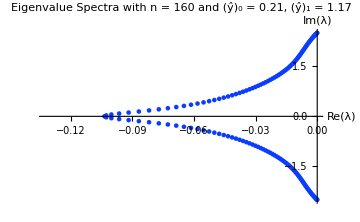

```mathematica
k=160;
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0/5,yHat1/5,1]]
```

## Dendro Output

### Hide

```mathematica
derivativeOrder=1;
interiorOrder=n;
totalBoundRows=numBoundaryRows;
freeInteriorParameters={};
freeBoundaryParameters={};
RHSInteriorList=RHSPars;
interiorParametersValues=interiorCoeffsC6/.{α->alpha,β->beta};
boundaryParametersValues=boundaryLuke/.{α12->gamma01,β12->gamma02,α21->gamma10,α22->gamma12,β22->gamma13,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14};
LHSBoundaryList={gamma01,gamma02,gamma10,gamma12,gamma13};
RHSBoundaryList={a00,a01,a02,a03,a04,a10,a11,a12,a13,a14};
(*Don't need to mess with these until we incorporate this procedure with James's filtering*)
filterIntCoeff;
filterBoundCoeff;
filterIntParam;
filterBoundParam;
filtering=False;
(*boundary={α12->γ01,β12->γ02,α21->γ10,α22->γ12,β22->γ13,β31->γ20,α31->γ21,α32->γ23,β32->γ24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};*)
```

```mathematica
(*****************Print coefficients in Dendro-GR Format*****************)
If[derivativeOrder==1,
LHSName="P1";
RHSName="Q1";
nth="1st";
coeffs="D_coeffs";
order="First",
If[derivativeOrder==2,
LHSName="P2";
RHSName="Q2";
nth="2nd";
coeffs="D_coeffs";
order="Second"]];
If[LHSBandCount==3,
LHSStructure="T",
If[LHSBandCount==5,
LHSStructure="P"]];

(*Convert Mathematica expression syntax to C/C++ expression syntax*)
convertToCCode[expr_]:=Module[{str},str=ToString[expr,InputForm];
(*Add ".0" to standalone integers but not to variables with numbers*)
(*Formatting adjustments to match C/C++ syntax*)str=StringReplace[str,{" "->"","*"->" * ","/"->" / ","+"->" + ","-"->" - ","^"->" ^ "}];
str]
(*Function to generate the line of C/C++ code to define the fixed variables*)
generateCAssignment[rule_]:=Module[{variable,expression,cCode,cAssignment},
variable=ToString[rule[[1]]];
expression=rule[[2]];
cCode=convertToCCode[expression];
cAssignment="double "<>variable<>" = "<>cCode<>";";
cAssignment
]






(*Initial Block*)
initialBlock=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order"}];
initialBlock2=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order","Filtered"}];

(*Free Parameters Block*)
freeParameters=Join[freeInteriorParameters,freeBoundaryParameters];
numFreePars=Length[freeParameters];
alphaPrint=StringReplace[generateCAssignment[Select[interiorParametersValues,#[[1]]===alpha&][[1]]],"alpha"->"alpha0"];
freeParPrints={};
If[numFreePars>0,
For[i=1,i<=numFreePars,i++,
AppendTo[freeParPrints,StringJoin[{"\n\t\tdouble ",ToString[freeParameters[[i]]]," = ",coeffs,"[",ToString[i],"];"}]]]]
freeParametersBlock=StringJoin[{"\t",alphaPrint,"\n\t\tdouble alpha = alpha0 + ",coeffs,"[0];",freeParPrints}];

(*Filter*)
freeParPrints2={};
freeParametersBlock2=StringJoin[{"\t","\n\t\tdouble alpha = ","F_coeffs","[0];",If[LHSBandCount==5,StringJoin["\n\t\tdouble beta = ","F_coeffs","[1];"],""]}];

(*Fixed Parameters Block*)
(*Create a list of the solved fixed parameters in C/C++ syntax*)
interiorParametersValues3=DeleteCases[interiorParametersValues,Rule[alpha,_]];
interiorParameterPrints=Table[
generateCAssignment[interiorParametersValues3[[i]]],
{i,1,Length[interiorParametersValues]-1}
];
boundaryParameterPrints=Table[
generateCAssignment[boundaryParametersValues[[i]]],
{i,1,Length[boundaryParametersValues]}
];
(*For filtered coefficients*)
interiorParameterPrints2=Table[
generateCAssignment[filterIntCoeff[[i]]],
{i,1,Length[filterIntCoeff]}
];
boundaryParameterPrints2=Table[
generateCAssignment[filterBoundCoeff[[i]]],
{i,1,Length[filterBoundCoeff]}
];
(*Print the coefficients in a single block of text rather than individual lines*)
fixedParametersBlockD=StringJoin["\t\t",Riffle[Join[interiorParameterPrints,boundaryParameterPrints],"\n\t\t"]];
fixedParametersBlockD2=StringJoin["\t\t",Riffle[Join[interiorParameterPrints2,boundaryParameterPrints2],"\n\t\t"]];

(*Structure Block*)
(*LHS Boundary*)
PDiagBoundary="";
LHSRowList=ToExpression[GatherBy[LHSBoundaryList,StringDrop[ToString[#],5]~StringTake~1&]];
For[i=1,i<=Length[LHSRowList],i++,
If[i==1,PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t","{1.0, ",StringDrop[ToString[LHSRowList[[i]]],1],","]];
If[i==2,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1}]],1],","]]];
If[i==3,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{","0.0, ",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t",StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
If[i>=4,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],StringDrop[StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
];
(*LHS Filter Boundary*)
RDiagBoundary="";
For[i=1,i<=Length@filterBoundParam,i++,
If[i==1,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha, beta},"]];
];
If[i==2,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha 1.0, alpha, beta},"]];
];
If[i>=3,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],"alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],"beta, alpha, 1.0, alpha, beta},"]];
];
];

(*LHS Interior*)
If[LHSBandCount==3,
PDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
PDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];
(*LHS Filter Interior*)
If[LHSBandCount==3,
RDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
RDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];

(*RHS Boundary*)
QDiagBoundary="";
RHSRowList=ToExpression[GatherBy[RHSBoundaryList,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList],i++,QDiagBoundary=StringJoin[QDiagBoundary,"\n\t\t\t",ToString[RHSRowList[[i]]],","]]
(*RHS Filter Boundary*)
SDiagBoundary="";
RHSRowList2=ToExpression[GatherBy[filterBoundParam,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList2],i++,SDiagBoundary=StringJoin[SDiagBoundary,"\n\t\t\t",ToString[RHSRowList2[[i]]]]]

(*RHS Interior*)
QDiagInterior={};
len=(2*Length[RHSInteriorList]+1);
If[derivativeOrder==1,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[-RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"0.0"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]
],
If[derivativeOrder==2,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[-RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"t1"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]]]]

(*RHS Filter Interior*)
SDiagInterior={};
newFilterIntParam=Drop[filterIntParam,1];
len=(2*Length[newFilterIntParam]+1);
For[i=1,i<=len,i++,
If[i<=Length[newFilterIntParam],PrependTo[SDiagInterior,ToString[newFilterIntParam[[i]]]<>"/"<>ToString[2]<>".0"]];
If[i==(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,"a0"]];
If[i>(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,ToString[newFilterIntParam[[i-Length[newFilterIntParam]-1]]]<>"/"<>ToString[2]<>".0"]]
]


PDiagBoundaryStr=StringDrop[StringDrop[PDiagBoundary,1],-1];
PDiagInteriorStr=StringDrop[StringDrop[PDiagInterior,1],-1];
RDiagBoundaryStr=StringDrop[StringDrop[RDiagBoundary,1],-1];
RDiagInteriorStr=StringDrop[StringDrop[RDiagInterior,1],-1];
QDiagBoundaryStr=StringDrop[StringDrop[QDiagBoundary,1],-1];
QDiagInteriorStr=StringDrop[StringDrop[ToString[QDiagInterior],1],-1];
SDiagBoundaryStr=StringDrop[SDiagBoundary,1];
SDiagInteriorStr=StringDrop[StringDrop[ToString[SDiagInterior],1],-1];

(*Subscript[t, 1] is the middle RHS Interior Coefficient for Second Derivatives*)
t1List={};
For[i=1,i<=Length[RHSInteriorList],i++,
AppendTo[t1List,ToString[RHSInteriorList[[i]]]<>"/"<>ToString[i^2]<>".0"]
];
If[derivativeOrder==1,
t1="",
If[derivativeOrder==2,
t1=StringJoin["-2.0 * ("<>StringDrop[StringDrop[ToString[t1List],1],-1]<>")"]]];


If[filtering,
filterFinalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock2,"(\n","\tconst std::vector<double>& ","F_coeffs",") {\n","\t",freeParametersBlock2,"\n\n",fixedParametersBlockD2,"\n\n","\t\t// boundary elements for R matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","R","DiagBoundary{\n",RDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for R matrix for ",nth," derivative\n","\t\tstd::vector<double> ","R","DiagInterior{\n","\t\t\t",RDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for S matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","S","DiagBoundary\n",SDiagBoundaryStr,"\n","\t\t;\n\n","\t\t// diagonal elements for S matrix for ",nth," derivative\n","\t\tstd::vector<double> ","S","DiagInterior{\n","\t\t\t",SDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t","R","DiagInterior, ","S","DiagInterior, ","S","DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}"}];
]

finalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock,"(\n","\tconst std::vector<double>& ",coeffs,") {\n","\t",freeParametersBlock,"\n\n",fixedParametersBlockD,"\n\n","\t\t// boundary elements for P matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",LHSName,"DiagBoundary{\n",PDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for P matrix for ",nth," derivative\n","\t\tstd::vector<double> ",LHSName,"DiagInterior{\n","\t\t\t",PDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",RHSName,"DiagBoundary{\n",QDiagBoundaryStr,"\n","\t\t};\n\n",If[derivativeOrder==1,t1,If[derivativeOrder==2,"\t\tdouble t1 = "<>t1<>";\n"]],"\t\t// diagonal elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<double> ",RHSName,"DiagInterior{\n","\t\t\t",QDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t",LHSName,"DiagInterior, ",LHSName,"DiagBoundary, ",RHSName,"DiagInterior, ",RHSName,"DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}",If[filtering,"\n\n"<>filterFinalBlock,""]}];
```

GatherBy::list: List expected at position 1 in GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&].

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Drop::drop: Cannot drop positions 1 through 1 in filterIntParam.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

StringDrop::drop: Cannot drop positions 1 through 1 in "".

### Show

```mathematica
outExt="h";
(*Print header*)
Print[Style["Dendro-Ready Coefficients (Copied to clipboard):",Bold,FontSize->24]];
Print[finalBlock];
(*Copy the block of text to the user's clipboard*)
CopyToClipboard[finalBlock];

(*Save to output file*)
fileName=StringJoin[{"BYU_C6","_yHat0_",ToString[yHat0],"_yHat1_",ToString[yHat1],".",outExt}];
Export[fileName,finalBlock,"Text"];
Print[StringJoin[{"Saved to file: ",fileName}]]
```

Dendro-Ready Coefficients (Copied to clipboard):

MatrixDiagonalEntries* BYUDerivsP6R2DiagonalsFirstOrder(
	const std::vector<double>& D_coeffs) {
		double alpha0 = 0.4963477370017426;
		double alpha = alpha0 + D_coeffs[0];

		double beta = 0.04075360091710232;
		double a1 = 0.723439643221641;
		double a2 = 0.15683084734860173;
		double gamma01 = 6.41607857818298;
		double gamma02 = 3.624117867379136;
		double gamma10 = 0.09002789833038638;
		double gamma12 = 1.5039345617386584;
		double gamma13 = 0.3627346344803884;
		double a00 =  - 3.3853431556471;
		double a01 =  - 3.762810726379067;
		double a02 = 6.624117866996977;
		double a03 = 0.541372622221082;
		double a04 =  - 0.0173366074130172;
		double a10 =  - 0.3424581275834023;
		double a11 =  - 1.2944774639303913;
		double a12 = 0.6858143532884321;
		double a13 = 0.9249391009999962;
		double a14 = 0.026182137225974816;

		// boundary elements for P matrix for 1st derivative
		std::vector<std::vector<double>> P1DiagBoundary{
			{1.0, gamma01, gamma02},
			{gamma10, 1.0, gamma12, gamma13}
		};

		// diagonal elements for P matrix for 1st derivative
		std::vector<double> P1DiagInterior{
			beta, alpha, 1.0, alpha, beta
		};

		// boundary elements for Q matrix for 1st derivative
		std::vector<std::vector<double>> Q1DiagBoundary{
			{a00, a01, a02, a03, a04},
			{a10, a11, a12, a13, a14}
		};

		// diagonal elements for Q matrix for 1st derivative
		std::vector<double> Q1DiagInterior{
			-a2, -a1, 0.0, a1, a2
		};

		// store the entries for matrix creation
		MatrixDiagonalEntries* diagEntries = new
			MatrixDiagonalEntries{
				P1DiagInterior, P1DiagBoundary, Q1DiagInterior, Q1DiagBoundary
			};
		return diagEntries;
	}

Saved to file: BYU_C6_yHat0_3.24_yHat1_3.06.h

# S6 Scheme - ALMOST DONE, JUST STUCK ON THE EIGENVALUES

## Initialization

The matrix system of equations we are solving for this scheme is:
	P=(1
γ_10
γ_20
γ
0
0
0 γ_01
1
γ_21
β
γ_25
0
0 γ_02
γ_12
1
α
γ_24
γ_14
0 γ_03
γ_13
γ_23
1
γ_23
γ_13
γ_03 0
γ_14
γ_24
α
1
γ_12
γ_02 0
0
γ_25
β
γ_21
1
γ_01 0
0
0
γ
γ_20
γ_10
1)
	Q=(a_00
a_10
a_20
-a_3
-a_26
-a_16
-a_06 a_01
a_11
a_21
-a_2
-a_25
-a_15
-a_05 a_02
a_12
a_22
-a_1
-a_24
-a_14
-a_04 a_03
a_13
a_23
0
-a_23
-a_13
-a_03 a_04
a_14
a_24
a_1
-a_22
-a_12
-a_02 a_05
a_15
a_25
a_2
-a_21
-a_11
-a_01 a_06
a_16
a_26
a_3
-a_20
-a_10
-a_00)

```mathematica
(*From KimInteriorOptimization.nb, one day to be merged with this one. Or I could DumpSave[] in that notebook and then Get[] here.*)
(*Note that these are found with the P6 Scheme NEW header in that notebook*)
interiorCoeffsS6={α->0.6285289069343067,β->0.14004161726411965,γ->0.006643294882238897,a1->0.5938870692793884,a2->0.29803727276980746,a3->0.02841740142055403};

(*If you have the .mx files in the same directory as this notebook, these will let you skip the long computation of defining bdCoeffs under the "Solve for Boundary Coefficients" section*)
Get["S6_interiorCoeffs.mx"]
Get["S6_bdCoeffs2.mx"];
Get["S6_bdCoeffs1.mx"];
Get["S6_bdCoeffs0.mx"];
```

## General Extrapolation Polynomial

For the S6 scheme, we have:
	LHSBandCount = 7
	n = 6
	freeInteriorPars = 3
	yDeriv = 10

NOTE: I NEEDED TO ADD A CASE TO THE SWITCH IN LHSPARS

```mathematica
(*User chooses these parameters, the rest is calculated from these*)
LHSBandCount=7; (*3 for tridiagonal, 5 for pentadiagonal*)
n=6; (*order of the scheme*)
freeInteriorPars=3; (*number of free parameters used for Kim's optimization on the interior*)
yDeriv=10; (*(d^n P)/dx^n(ŷ)=0 from Kim 2024 Eq. 10, this is n in that equation*) (*provide constraints on what the user can choose for this. Upper bound should be polynomialorder to prevent the matrix from being singular, and lower bound should be order·2 I think.*)

LHSPars=Switch[LHSBandCount,3,{α},5,{α,β},7,{α,β,γ}];
RHSPars=Table[ToExpression[StringJoin["a",ToString[i]]],{i,1,Ceiling[n/2]-Length@LHSPars+freeInteriorPars}];
numBoundaryRows=Length@RHSPars;
fOrder=(2*Length@RHSPars)+1;
fpOrder=LHSBandCount+(numBoundaryRows-(LHSBandCount-1)/2);
PolynomialOrder=fOrder+fpOrder;


rowf1=Join[{1},Table[0,{i,1,PolynomialOrder}]];
rowf=Table[Table[i^j,{j,0,PolynomialOrder}],{i,1,fOrder-1}];
rowfp1=Join[{0,1},Table[0,{i,2,PolynomialOrder}]];
rowfp=Table[Table[j i^(j-1),{j,0,PolynomialOrder}],{i,1,fpOrder-1}];
rowyHat=Join[Table[0,{i,1,yDeriv}],Table[(i!)/((i-yDeriv)!) yHat^(i-yDeriv),{i,yDeriv,PolynomialOrder}]];

matf=PrependTo[rowf,rowf1];
matfp=PrependTo[rowfp,rowfp1];
matfCombined=Join[matf,matfp];
LMat=AppendTo[matfCombined,rowyHat];

pVec=Table[ToExpression[StringJoin["p",ToString[i]]],{i,0,PolynomialOrder}];
fVec=Join[Table[ToExpression[StringJoin["f",ToString[i]]],{i,0,fOrder-1}],Table[ToExpression[StringJoin["fp",ToString[i]]],{i,0,fpOrder-1}],{0}];

pCoeffs=Solve[LMat.pVec==fVec,pVec][[1]];

yHatSingularities=(Transpose@Solve[Det[LMat]==0,yHat])[[1]]//N;
P[x_]=Total[Table[pVec[[i+1]]*x^i,{i,0,PolynomialOrder}]]/.pCoeffs;

Print["System:\n",MatrixForm[LMat]," ",MatrixForm[pVec]," = ",MatrixForm[fVec]]
Print["Singularities:\n",MatrixForm[yHatSingularities]]
(*Print["Coefficients:\n",MatrixForm[pCoeffs]]*)
```

System:
(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 4 | 8 | 16 | 32 | 64 | 128 | 256 | 512 | 1024 | 2048 | 4096 | 8192 | 16384
1 | 3 | 9 | 27 | 81 | 243 | 729 | 2187 | 6561 | 19683 | 59049 | 177147 | 531441 | 1594323 | 4782969
1 | 4 | 16 | 64 | 256 | 1024 | 4096 | 16384 | 65536 | 262144 | 1048576 | 4194304 | 16777216 | 67108864 | 268435456
1 | 5 | 25 | 125 | 625 | 3125 | 15625 | 78125 | 390625 | 1953125 | 9765625 | 48828125 | 244140625 | 1220703125 | 6103515625
1 | 6 | 36 | 216 | 1296 | 7776 | 46656 | 279936 | 1679616 | 10077696 | 60466176 | 362797056 | 2176782336 | 13060694016 | 78364164096
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14
0 | 1 | 4 | 12 | 32 | 80 | 192 | 448 | 1024 | 2304 | 5120 | 11264 | 24576 | 53248 | 114688
0 | 1 | 6 | 27 | 108 | 405 | 1458 | 5103 | 17496 | 59049 | 196830 | 649539 | 2125764 | 6908733 | 22320522
0 | 1 | 8 | 48 | 256 | 1280 | 6144 | 28672 | 131072 | 589824 | 2621440 | 11534336 | 50331648 | 218103808 | 939524096
0 | 1 | 10 | 75 | 500 | 3125 | 18750 | 109375 | 625000 | 3515625 | 19531250 | 107421875 | 585937500 | 3173828125 | 17089843750
0 | 1 | 12 | 108 | 864 | 6480 | 46656 | 326592 | 2239488 | 15116544 | 100776960 | 665127936 | 4353564672 | 28298170368 | 182849716224
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3628800 | 39916800 yHat | 239500800 yHat^2 | 1037836800 yHat^3 | 3632428800 yHat^4) (p0
p1
p2
p3
p4
p5
p6
p7
p8
p9
p10
p11
p12
p13
p14) = (f0
f1
f2
f3
f4
f5
f6
fp0
fp1
fp2
fp3
fp4
fp5
fp6
0)

Singularities:
(yHat→2.58067
yHat→3.41933
yHat→1.70759
yHat→4.29241)

## Solve for Boundary Coefficients

### Node 2

```mathematica
(*----------STEP 1----------*)
fVars2={fp0,fp1,fp2,fp3,fp4,fp5,f0,f1,f2,f3,f4,f5,f6};
bdCoeffsList2={γ20,γ21,γ22,γ23,γ24,γ25,a20,a21,a22,a23,a24,a25,a26};
schemeShifted=γ20 fp0+γ21 fp1+γ22 fp2+γ23 fp3+γ24 fp4+γ25 fp5-(a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6); (*==0*)
schemeCentered=γ P'[-1]+β fp0+α fp1+fp2+α fp3+β fp4+γ fp5-(-a3 P[-1]-a2 f0-a1 f1+a1 f3+a2 f4+a3 f5); (*==0*)

(*----------STEP 2----------*)
schemeNode3=γ fp0+β fp1+α fp2+fp3+α fp4+β fp5+γ fp6==-a3 f0-a2 f1-a1 f2+a1 f4+a2 f5+a3 f6;
SOLfp6=Solve[schemeNode3,fp6][[1,1]]/.interiorCoeffsS6;
schemeCentered=schemeCentered/.SOLfp6;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars2];

(*----------STEP 4----------*)
coeffEqs2=Table[Coefficient[eq,fVars2[[i]]]==0,{i,1,Length@fVars2}];
bdCoeffs2=(Solve[coeffEqs2,bdCoeffsList2][[1]])/.interiorCoeffsS6;

(*----------STEP 5----------*)
DumpSave["S6_bdCoeffs2.mx","Global`bdCoeffs2"]
```

{Global`bdCoeffs2}

### Node 1

```mathematica
(*----------STEP 1----------*)
fVars1={fp0,fp1,fp2,fp3,fp4,f0,f1,f2,f3,f4,f5,f6};
bdCoeffsList1={γ10,γ11,γ12,γ13,γ14,a10,a11,a12,a13,a14,a15,a16};
schemeShifted=γ10 fp0+γ11 fp1+γ12 fp2+γ13 fp3+γ14 fp4-(a10 f0+a11 f1+a12 f2+a13 f3+a14 f4+a15 f5+a16 f6); (*==0*)
schemeCentered=γ P'[-2]+β P'[-1]+α fp0+fp1+α fp2+β fp3+γ fp4-(-a3 P[-2]-a2 P[-1]-a1 f0+a1 f2+a2 f3+a3 f4); (*==0*)

(*----------STEP 2----------*)
schemeNode3=γ fp0+β fp1+α fp2+fp3+α fp4+β fp5+γ fp6==-a3 f0-a2 f1-a1 f2+a1 f4+a2 f5+a3 f6;
schemeNode2=γ20 fp0+γ21 fp1+γ22 fp2+γ23 fp3+γ24 fp4+γ25 fp5==a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6;

SOLfp6=Solve[schemeNode3,fp6][[1,1]]/.interiorCoeffsS6;
SOLfp5=Solve[schemeNode2,fp5][[1,1]]/.bdCoeffs2;
schemeCentered=schemeCentered/.SOLfp6/.SOLfp5;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars1];

(*----------STEP 4----------*)
coeffEqs1=Table[Coefficient[eq,fVars1[[i]]]==0,{i,1,Length@fVars1}];
bdCoeffs1=(Solve[coeffEqs1,bdCoeffsList1][[1]])/.interiorCoeffsS6;

(*----------STEP 5----------*)
DumpSave["S6_bdCoeffs1.mx","Global`bdCoeffs1"]
```

{Global`bdCoeffs1}

### Node 0

```mathematica
(*----------STEP 1----------*)
fVars0={fp0,fp1,fp2,fp3,f0,f1,f2,f3,f4,f5,f6};
bdCoeffsList0={γ00,γ01,γ02,γ03,a00,a01,a02,a03,a04,a05,a06};
schemeShifted=γ00 fp0+γ01 fp1+γ02 fp2+γ03 fp3-(a00 f0+a01 f1+a02 f2+a03 f3+a04 f4+a05 f5+a06 f6); (*==0*)
schemeCentered=γ P'[-3]+β P'[-2]+α P'[-1]+fp0+α fp1+β fp2+γ fp3-(-a3 P[-3]-a2 P[-2]-a1 P[-1]+a1 f1+a2 f2+a3 f3); (*==0*)

(*----------STEP 2----------*)
schemeNode3=γ fp0+β fp1+α fp2+fp3+α fp4+β fp5+γ fp6==-a3 f0-a2 f1-a1 f2+a1 f4+a2 f5+a3 f6;
schemeNode2=γ20 fp0+γ21 fp1+γ22 fp2+γ23 fp3+γ24 fp4+γ25 fp5==a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6;
schemeNode1=γ10 fp0+γ11 fp1+γ12 fp2+γ13 fp3+γ14 fp4==a10 f0+a11 f1+a12 f2+a13 f3+a14 f4+a15 f5+a16 f6;

SOLfp6=Solve[schemeNode3,fp6][[1,1]]/.interiorCoeffsS6;
SOLfp5=Solve[schemeNode2,fp5][[1,1]]/.bdCoeffs2;
SOLfp4=Solve[schemeNode1,fp4][[1,1]]/.bdCoeffs1;
schemeCentered=schemeCentered/.SOLfp6/.SOLfp5/.SOLfp4;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars0];

(*----------STEP 4----------*)
coeffEqs0=Table[Coefficient[eq,fVars0[[i]]]==0,{i,1,Length@fVars0}];
bdCoeffs0=(Solve[coeffEqs0,bdCoeffsList0][[1]])/.interiorCoeffsS6;

(*----------STEP 5----------*)
DumpSave["S6_bdCoeffs0.mx","Global`bdCoeffs0"]
```

{Global`bdCoeffs0}

## Optimize ŷ

### Set and Normalize Coefficients

We normalize the coefficients so that the main diagonal of the LHS matrix is all 1’s, but we leave the coefficients in terms of the optimization free parameter ŷ so that we can optimize over it.

```mathematica
Clear[γ22,γ20,γ21,γ23,γ24,γ25,a20,a21,a22,a23,a24,a25,a26]
Clear[γ11,γ10,γ12,γ13,γ14,a10,a11,a12,a13,a14,a15,a16]
Clear[γ00,γ01,γ02,γ03,a00,a01,a02,a03,a04,a05,a06]

{γ22,γ20,γ21,γ23,γ24,γ25,a20,a21,a22,a23,a24,a25,a26}=1/γ22*{γ22,γ20,γ21,γ23,γ24,γ25,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2;
{γ11,γ10,γ12,γ13,γ14,a10,a11,a12,a13,a14,a15,a16}=1/γ11*{γ11,γ10,γ12,γ13,γ14,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1;
{γ00,γ01,γ02,γ03,a00,a01,a02,a03,a04,a05,a06}=1/γ00*{γ00,γ01,γ02,γ03,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0;
```

### Node 2

```mathematica
𝔸2[κ_]=γ20+γ21 Cos[κ]+Cos[2 κ]+γ23 Cos[3 κ]+γ24 Cos[4 κ]+γ25 Cos[5 κ];
𝔹2[κ_]=γ21 Sin[κ]+Sin[2 κ]+γ23 Sin[3 κ]+γ24 Sin[4 κ]+γ25 Sin[5 κ];
ℂ2[κ_]=a20+a21 Cos[κ]+a22 Cos[2 κ]+a23 Cos[3 κ]+a24 Cos[4 κ]+a25 Cos[5 κ]+a26 Cos[6 κ];
𝔻2[κ_]=a21 Sin[κ]+a22 Sin[2 κ]+a23 Sin[3 κ]+a24 Sin[4 κ]+a25 Sin[5 κ]+a26 Sin[6 κ];
κBar2Re[κ_]=(𝔸2[κ]*𝔻2[κ]-𝔹2[κ]*ℂ2[κ])/((𝔸2[κ])^2+(𝔹2[κ])^2);
κBar2Im[κ_]=(-𝔸2[κ]*ℂ2[κ]-𝔹2[κ]*𝔻2[κ])/((𝔸2[κ])^2+(𝔹2[κ])^2);
κBar2Norm[κ_]=Abs[κBar2Re[κ]+I*κBar2Im[κ]];
```

```mathematica
Δ2Re[κ_]=(κ*((𝔸2[κ])^2+(𝔹2[κ])^2)-(𝔸2[κ]*𝔻2[κ]-𝔹2[κ]*ℂ2[κ]))^2;
Δ2Im[κ_]=(0*((𝔸2[κ])^2+(𝔹2[κ])^2)-(-𝔸2[κ]*ℂ2[κ]-𝔹2[κ]*𝔻2[κ]))^2;
Δ2Norm[κ_]=(κ-κBar2Norm[κ])^2;
```

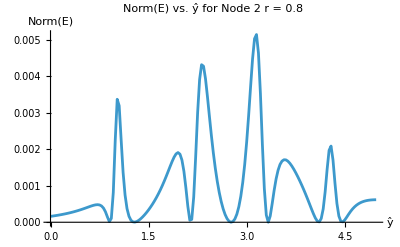

Evaluation time: 16.73749

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat2Array=Range[0,5,0.03];
Δ2NormArray=Table[Δ2Norm[κ]/.{yHat->yHat2Array[[i]]},{i,1,Length@yHat2Array}];
ENorm2Array=Table[NIntegrate[Δ2NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat2Array}];

ListPlot[Transpose@{yHat2Array,ENorm2Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 2\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

### Node 1

```mathematica
𝔸1[κ_]=γ10+Cos[κ]+γ12 Cos[2 κ]+γ13 Cos[3 κ]+γ14 Cos[4 κ];
𝔹1[κ_]=Sin[κ]+γ12 Sin[2 κ]+γ13 Sin[3 κ]+γ14 Sin[4 κ];
ℂ1[κ_]=a10+a11 Cos[κ]+a12 Cos[2 κ]+a13 Cos[3 κ]+a14 Cos[4 κ]+a15 Cos[5 κ]+a16 Cos[6 κ];
𝔻1[κ_]=a11 Sin[κ]+a12 Sin[2 κ]+a13 Sin[3 κ]+a14 Sin[4 κ]+a15 Sin[5 κ]+a16 Sin[6 κ];
κBar1Re[κ_]=(𝔸1[κ]*𝔻1[κ]-𝔹1[κ]*ℂ1[κ])/((𝔸1[κ])^2+(𝔹1[κ])^2);
κBar1Im[κ_]=(-𝔸1[κ]*ℂ1[κ]-𝔹1[κ]*𝔻1[κ])/((𝔸1[κ])^2+(𝔹1[κ])^2);
κBar1Norm[κ_]=Abs[κBar1Re[κ]+I*κBar1Im[κ]];
```

```mathematica
Δ1Re[κ_]=(κ*((𝔸1[κ])^2+(𝔹1[κ])^2)-(𝔸1[κ]*𝔻1[κ]-𝔹1[κ]*ℂ1[κ]))^2;
Δ1Im[κ_]=(0*((𝔸1[κ])^2+(𝔹1[κ])^2)-(-𝔸1[κ]*ℂ1[κ]-𝔹1[κ]*𝔻1[κ]))^2;
Δ1Norm[κ_]=(κ-κBar1Norm[κ])^2;
```

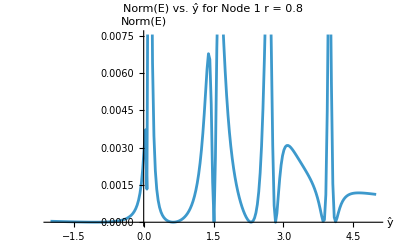

Evaluation time: 37.9122029

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat1Array=Range[-2,5,0.03];
Δ1NormArray=Table[Δ1Norm[κ]/.{yHat->yHat1Array[[i]]},{i,1,Length@yHat1Array}];
ENorm1Array=Table[NIntegrate[Δ1NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat1Array}];

ListPlot[Transpose@{yHat1Array,ENorm1Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 1\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

### Node 0

```mathematica
𝔸0[κ_]=1+γ01 Cos[κ]+γ02 Cos[2 κ]+γ03 Cos[3 κ];
𝔹0[κ_]=γ01 Sin[κ]+γ02 Sin[2 κ]+γ03 Sin[3 κ];
ℂ0[κ_]=a00+a01 Cos[κ]+a02 Cos[2 κ]+a03 Cos[3 κ]+a04 Cos[4 κ]+a05 Cos[5 κ]+a06 Cos[6 κ];
𝔻0[κ_]=a01 Sin[κ]+a02 Sin[2 κ]+a03 Sin[3 κ]+a04 Sin[4 κ]+a05 Sin[5 κ]+a06 Sin[6 κ];
κBar0Re[κ_]=(𝔸0[κ]*𝔻0[κ]-𝔹0[κ]*ℂ0[κ])/((𝔸0[κ])^2+(𝔹0[κ])^2);
κBar0Im[κ_]=(-𝔸0[κ]*ℂ0[κ]-𝔹0[κ]*𝔻0[κ])/((𝔸0[κ])^2+(𝔹0[κ])^2);
κBar0Norm[κ_]=Abs[κBar0Re[κ]+I*κBar0Im[κ]];
```

```mathematica
Δ0Re[κ_]=(κ*((𝔸0[κ])^2+(𝔹0[κ])^2)-(𝔸0[κ]*𝔻0[κ]-𝔹0[κ]*ℂ0[κ]))^2;
Δ0Im[κ_]=(0*((𝔸0[κ])^2+(𝔹0[κ])^2)-(-𝔸0[κ]*ℂ0[κ]-𝔹0[κ]*𝔻0[κ]))^2;
Δ0Norm[κ_]=(κ-κBar0Norm[κ])^2;
```

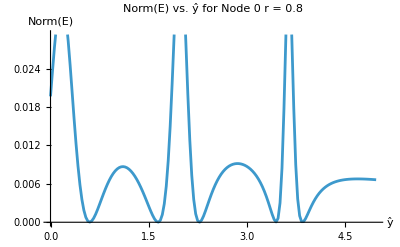

Evaluation time: 146.328868

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat0Array=Range[0,5,0.03];
Δ0NormArray=Table[Δ0Norm[κ]/.{yHat->yHat0Array[[i]]},{i,1,Length@yHat0Array}];
ENorm0Array=Table[NIntegrate[Δ0NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat0Array}];

ListPlot[Transpose@{yHat0Array,ENorm0Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 0\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

## Spectral Function

### Node 2

```mathematica
Clear[yHat]
SF2Re[κ_,yHat_]=κBar2Re[κ];
SF2Im[κ_,yHat_]=κBar2Im[κ];
SF2Norm[κ_,yHat_]=κBar2Norm[κ];
```

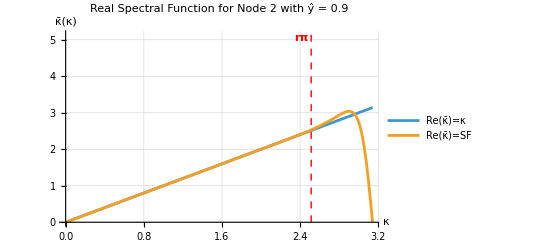

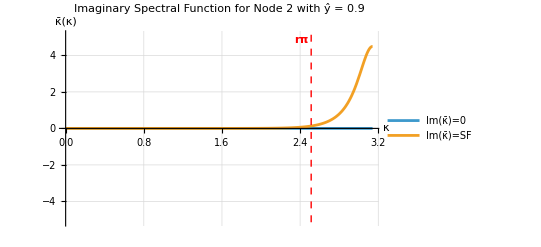

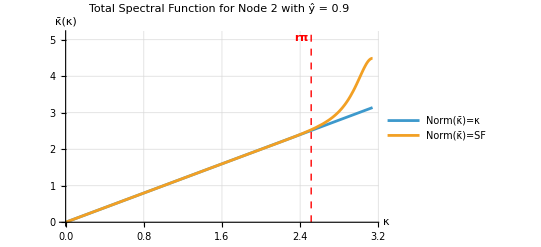

```mathematica
r=0.8;
yHat2List={(*1*)0.90,(*2*)1.29,(*3*)2.13,(*4*)2.76,(*5*)3.33,(*6*)4.11,(*7*)4.47};
yHat=yHat2List[[1]];
Plot[{κ,SF2Re[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
Plot[{0,SF2Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ,SF2Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
```

### Node 1

```mathematica
Clear[yHat]
SF1Re[κ_,yHat_]=κBar1Re[κ];
SF1Im[κ_,yHat_]=κBar1Im[κ];
SF1Norm[κ_,yHat_]=κBar1Norm[κ];
```

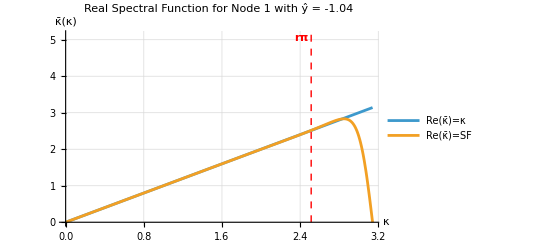

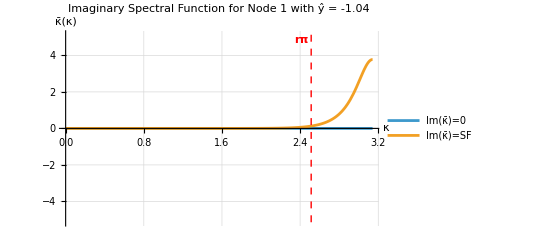

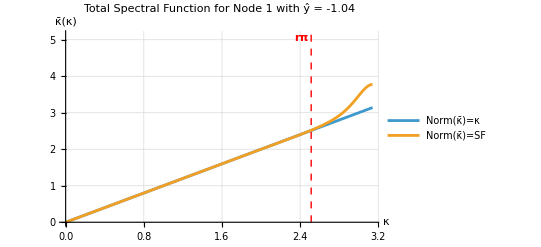

```mathematica
Clear[yHat]
r=0.8;
yHat1List={(*1*)-1.04,(*2*)0.06,(*3*)0.63,(*4*)1.50,(*5*)2.31,(*6*)2.82,(*7*)3.87,(*8*)4.11};
yHat=yHat1List[[1]];
Plot[{κ,SF1Re[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
Plot[{0,SF1Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ,SF1Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
```

### Node 0

```mathematica
Clear[yHat]
SF0Re[κ_,yHat_]=κBar0Re[κ];
SF0Im[κ_,yHat_]=κBar0Im[κ];
SF0Norm[κ_,yHat_]=κBar0Norm[κ];
```

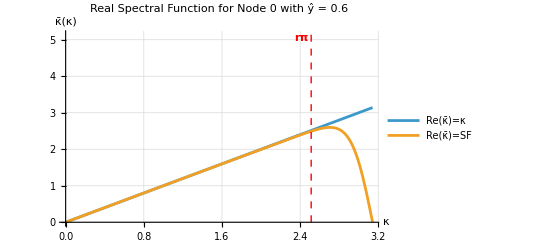

$Aborted

$Aborted

```mathematica
r=0.8;
yHat0List={(*1*)0.60,(*2*)1.65,(*3*)2.28,(*4*)3.45,(*5*)3.84};
yHat=yHat0List[[1]];
Plot[{κ,SF0Re[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
Plot[{0,SF0Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ,SF0Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
```

## Output Coefficients

### ŷ Definitions

```mathematica
Clear[yHat,yHat2,yHat1,yHat0]

yHat2List={(*1*)0.90,(*2*)1.29,(*3*)2.13,(*4*)2.76,(*5*)3.33,(*6*)4.11,(*7*)4.47};
yHat1List={(*1*)-1.04,(*2*)0.06,(*3*)0.63,(*4*)1.50,(*5*)2.31,(*6*)2.82,(*7*)3.87,(*8*)4.11};
yHat0List={(*1*)0.60,(*2*)1.65,(*3*)2.28,(*4*)3.45,(*5*)3.84};

yHat2=yHat2List[[4]];
yHat1=yHat1List[[6]];
yHat0=yHat0List[[3]];
```

### Define Coefficients

```mathematica
Clear[γ22,γ20,γ21,γ23,γ24,γ25,a20,a21,a22,a23,a24,a25,a26]
Clear[γ11,γ10,γ12,γ13,γ14,a10,a11,a12,a13,a14,a15,a16]
Clear[γ00,γ01,γ02,γ03,a00,a01,a02,a03,a04,a05,a06]

{γ22val,γ20val,γ21val,γ23val,γ24val,γ25val,a20val,a21val,a22val,a23val,a24val,a25val,a26val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,γ25,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,γ14val,a10val,a11val,a12val,a13val,a14val,a15val,a16val}=(1/γ11*{γ11,γ10,γ12,γ13,γ14,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,γ03val,a00val,a01val,a02val,a03val,a04val,a05val,a06val}=(1/γ00*{γ00,γ01,γ02,γ03,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0)/.{yHat->yHat0};
```

### Luke Output

```mathematica
interiorLuke=interiorCoeffsS6/.{a1->a,a2->b,a3->c};
boundaryLuke={α12->γ01val,β12->γ02val,δ12->γ03val,α21->γ10val,α22->γ12val,β22->γ13val,δ22->γ14val,β31->γ20val,α31->γ21val,α32->γ23val,β32->γ24val,δ32->γ25val,a1->a00val,b1->a01val,c1->a02val,d1->a03val,e1->a04val,f1->a05val,g1->a06val,a2->a10val,b2->a11val,c2->a12val,d2->a13val,e2->a14val,f2->a15val,g2->a16val,a3->a20val,b3->a21val,c3->a22val,d3->a23val,e3->a24val,f3->a25val,g3->a26val};
coeffLuke=Flatten[Join[interiorLuke,boundaryLuke]]
```

{α→0.628529,β→0.140042,γ→0.00664329,a→0.593887,b→0.298037,c→0.0284174,α12→35.4313,β12→121.666,δ12→66.9528,α21→1.3508,α22→-102.24,β22→-180.449,δ22→-50.7388,β31→0.00500389,α31→0.181215,α32→1.38902,β32→0.520244,δ32→0.0404566,a1→-5.41557,b1→-78.0935,c1→-40.108,d1→109.836,e1→15.1578,f1→-1.47864,g1→0.102493,a2→-4.7223,b2→27.4154,c2→161.976,d2→-61.3298,e2→-118.046,f2→-5.48926,g2→0.196016,a3→-0.0249568,b3→-0.453434,c3→-0.983183,d3→0.438437,e3→0.876348,f3→0.145698,g3→0.00109149}

### Nate Output

```mathematica
interiorNate=interiorCoeffsS6;
boundaryNate={γ01->γ01val,γ02->γ02val,γ03->γ03val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ14->γ14val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,γ25->γ25val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]]
```

{α→0.628529,β→0.140042,γ→0.00664329,a1→0.593887,a2→0.298037,a3→0.0284174,γ01→35.4313,γ02→121.666,γ03→66.9528,γ10→1.3508,γ12→-102.24,γ13→-180.449,γ14→-50.7388,γ20→0.00500389,γ21→0.181215,γ23→1.38902,γ24→0.520244,γ25→0.0404566,a00→-5.41557,a01→-78.0935,a02→-40.108,a03→109.836,a04→15.1578,a05→-1.47864,a06→0.102493,a10→-4.7223,a11→27.4154,a12→161.976,a13→-61.3298,a14→-118.046,a15→-5.48926,a16→0.196016,a20→-0.0249568,a21→-0.453434,a22→-0.983183,a23→0.438437,a24→0.876348,a25→0.145698,a26→0.00109149}

## Eigenvalue Spectral Analysis

### Modified Boundary Coefficients for Eigenvalue Analysis

```mathematica
LHSBars={γ12Bar->((γ12-γ10*γ02)/(1-γ10*γ01)/.coeffNate),
γ13Bar->((γ13-γ10*γ03)/(1-γ10*γ01)/.coeffNate),
γ14Bar->(γ14/(1-γ10*γ01)/.coeffNate),

γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ20*γ13)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24-γ20*γ14)/(γ10-γ20*γ12)/.coeffNate),
γ25Bar->((γ10*γ25)/(γ10-γ20*γ12)/.coeffNate),

β31Bar->((γ20*β-γ*γ21)/(γ20-γ*γ23)/.coeffNate),
α32Bar->((γ20*α-γ)/(γ20-γ*γ23)/.coeffNate),
α34Bar->((γ20*α-γ*γ24)/(γ20-γ*γ23)/.coeffNate),
β35Bar->((γ20*β-γ*γ25)/(γ20-γ*γ23)/.coeffNate),
γ36Bar->((γ20*γ)/(γ20-γ*γ23)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,6}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,6}]/.coeffNate;
RHSBars3={
a31Bar->(-γ20*a2-γ*a21/.coeffNate),
a32Bar->(-γ20*a1-γ*a22/.coeffNate),
a33Bar->(-γ*a23/.coeffNate),
a34Bar->(γ20*a1-γ*a24/.coeffNate),
a35Bar->(γ20*a2-γ*a25/.coeffNate),
a36Bar->(γ20*a3-γ*a26/.coeffNate)
};

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2,RHSBars3]
```

{γ12Bar→5.68893,γ13Bar→5.78074,γ14Bar→1.08276,γ21Bar→0.128748,γ23Bar→1.49229,γ24Bar→0.513659,γ25Bar→0.0293432,β31Bar→0.119113,α32Bar→0.828216,α34Bar→0.0736409,β35Bar→-0.102275,γ36Bar→-0.00787027,a11Bar→-2.83616,a12Bar→-4.61271,a13Bar→4.47488,a14Bar→2.95604,a15Bar→0.0745173,a16Bar→-0.00122849,a21Bar→-0.402536,a22Bar→-1.1483,a23Bar→0.48278,a24Bar→0.952783,a25Bar→0.120423,a26Bar→0.000265003,a31Bar→0.00152095,a32Bar→0.00355983,a33Bar→-0.00291267,a34Bar→-0.00285009,a35Bar→0.000523431,a36Bar→0.000134947}

### Build Modified Matrices (needs cleaning badly)

```mathematica
Clear[LHS,RHS]
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],

If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==5),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],

If[(i==3&&j==1),ToExpression["β"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==3&&j==2),ToExpression["α"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==3&&j==4),ToExpression["α"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==3&&j==5),ToExpression["β"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==3&&j==6),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],

If[(i-3==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+3==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],

If[i-3==j,γ,
If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
If[i+3==j,γ,
0]]]]]]]]]]]]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}]

k=9; (*Size*)
MatrixForm@LHS[k]

MatrixForm@(LHS[k]/.coeffNate)/.barCoeffs
```

(1 | γ12Bar | γ13Bar | γ14Bar | 0 | 0 | 0 | 0 | 0
γ21Bar | 1 | γ23Bar | γ24Bar | γ25Bar | 0 | 0 | 0 | 0
β31Bar | α32Bar | 1 | α34Bar | β35Bar | γ36Bar | 0 | 0 | 0
γ | β | α | 1 | α | β | γ | 0 | 0
0 | γ | β | α | 1 | α | β | γ | 0
0 | 0 | γ | β | α | 1 | α | β | γ
0 | 0 | 0 | γ25 | γ24 | γ23 | 1 | γ21 | γ20
0 | 0 | 0 | 0 | γ14 | γ13 | γ12 | 1 | γ10
0 | 0 | 0 | 0 | 0 | γ03 | γ02 | γ01 | 1)

(1 | 5.68893 | 5.78074 | 1.08276 | 0 | 0 | 0 | 0 | 0
0.128748 | 1 | 1.49229 | 0.513659 | 0.0293432 | 0 | 0 | 0 | 0
0.119113 | 0.828216 | 1 | 0.0736409 | -0.102275 | -0.00787027 | 0 | 0 | 0
0.00664329 | 0.140042 | 0.628529 | 1 | 0.628529 | 0.140042 | 0.00664329 | 0 | 0
0 | 0.00664329 | 0.140042 | 0.628529 | 1 | 0.628529 | 0.140042 | 0.00664329 | 0
0 | 0 | 0.00664329 | 0.140042 | 0.628529 | 1 | 0.628529 | 0.140042 | 0.00664329
0 | 0 | 0 | 0.0404566 | 0.520244 | 1.38902 | 1 | 0.181215 | 0.00500389
0 | 0 | 0 | 0 | -50.7388 | -180.449 | -102.24 | 1 | 1.3508
0 | 0 | 0 | 0 | 0 | 66.9528 | 121.666 | 35.4313 | 1)

```mathematica
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,

If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,

If[(i==3&&j==1),a31Bar,
If[(i==3&&j==2),a32Bar,
If[(i==3&&j==3),a33Bar,
If[(i==3&&j==4),a34Bar,
If[(i==3&&j==5),a35Bar,
If[(i==3&&j==6),a36Bar,

If[(i==k&&j==k),-a00,
If[(i==k&&j==k-1),-a01,
If[(i==k&&j==k-2),-a02,
If[(i==k&&j==k-3),-a03,
If[(i==k&&j==k-4),-a04,
If[(i==k&&j==k-5),-a05,
If[(i==k&&j==k-6),-a06,
If[(i==k-1&&j==k),-a10,
If[(i==k-1&&j==k-1),-a11,
If[(i==k-1&&j==k-2),-a12,
If[(i==k-1&&j==k-3),-a13,
If[(i==k-1&&j==k-4),-a14,
If[(i==k-1&&j==k-5),-a15,
If[(i==k-1&&j==k-6),-a16,
If[(i==k-2&&j==k),-a20,
If[(i==k-2&&j==k-1),-a21,
If[(i==k-2&&j==k-2),-a22,
If[(i==k-2&&j==k-3),-a23,
If[(i==k-2&&j==k-4),-a24,
If[(i==k-2&&j==k-5),-a25,
If[(i==k-2&&j==k-6),-a26,


If[i-3==j,-a3,
If[i-2==j,-a2,
If[i-1==j, -a1,
If[i==j, 0,
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}]

k=11; (*Size*)
MatrixForm@RHS[k]

MatrixForm@(RHS[k]/.coeffNate)/.barCoeffs
```

(a11Bar | a12Bar | a13Bar | a14Bar | a15Bar | a16Bar | 0 | 0 | 0 | 0 | 0
a21Bar | a22Bar | a23Bar | a24Bar | a25Bar | a26Bar | 0 | 0 | 0 | 0 | 0
a31Bar | a32Bar | a33Bar | a34Bar | a35Bar | a36Bar | 0 | 0 | 0 | 0 | 0
-a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0 | 0 | 0
0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0 | 0
0 | 0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0
0 | 0 | 0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0
0 | 0 | 0 | 0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3
0 | 0 | 0 | 0 | -a26 | -a25 | -a24 | -a23 | -a22 | -a21 | -a20
0 | 0 | 0 | 0 | -a16 | -a15 | -a14 | -a13 | -a12 | -a11 | -a10
0 | 0 | 0 | 0 | -a06 | -a05 | -a04 | -a03 | -a02 | -a01 | -a00)

(-2.83616 | -4.61271 | 4.47488 | 2.95604 | 0.0745173 | -0.00122849 | 0 | 0 | 0 | 0 | 0
-0.402536 | -1.1483 | 0.48278 | 0.952783 | 0.120423 | 0.000265003 | 0 | 0 | 0 | 0 | 0
0.00152095 | 0.00355983 | -0.00291267 | -0.00285009 | 0.000523431 | 0.000134947 | 0 | 0 | 0 | 0 | 0
-0.0284174 | -0.298037 | -0.593887 | 0 | 0.593887 | 0.298037 | 0.0284174 | 0 | 0 | 0 | 0
0 | -0.0284174 | -0.298037 | -0.593887 | 0 | 0.593887 | 0.298037 | 0.0284174 | 0 | 0 | 0
0 | 0 | -0.0284174 | -0.298037 | -0.593887 | 0 | 0.593887 | 0.298037 | 0.0284174 | 0 | 0
0 | 0 | 0 | -0.0284174 | -0.298037 | -0.593887 | 0 | 0.593887 | 0.298037 | 0.0284174 | 0
0 | 0 | 0 | 0 | -0.0284174 | -0.298037 | -0.593887 | 0 | 0.593887 | 0.298037 | 0.0284174
0 | 0 | 0 | 0 | -0.00109149 | -0.145698 | -0.876348 | -0.438437 | 0.983183 | 0.453434 | 0.0249568
0 | 0 | 0 | 0 | -0.196016 | 5.48926 | 118.046 | 61.3298 | -161.976 | -27.4154 | 4.7223
0 | 0 | 0 | 0 | -0.102493 | 1.47864 | -15.1578 | -109.836 | 40.108 | 78.0935 | 5.41557)

### Plot Eigenvalue Spectra

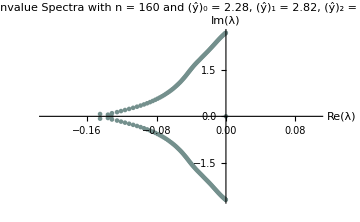

```mathematica
k=160;
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0/5,yHat1/5,yHat2/5]]
```

## Dendro Output - WILL NEED SIGNIFICANT UPDATING FOR SEPTADIAGONAL

### Hide

```mathematica
derivativeOrder=1;
interiorOrder=n;
totalBoundRows=numBoundaryRows;
freeInteriorParameters={};
freeBoundaryParameters={};
RHSInteriorList=RHSPars;
interiorParametersValues=interiorCoeffsS6/.{α->alpha,β->beta,γ->gamma};
boundaryParametersValues=boundaryNate/.{γ01->gamma01,γ02->gamma02,γ03->gamma03,γ10->gamma10,γ12->gamma12,γ13->gamma13,γ14->gamma14,γ20->gamma20,γ21->gamma21,γ23->gamma23,γ24->gamma24,γ25->gamma25};
LHSBoundaryList={gamma01,gamma02,gamma03,gamma10,gamma12,gamma13,gamma14,gamma20,gamma21,gamma23,gamma24,gamma25};
RHSBoundaryList={a00,a01,a02,a03,a04,a05,a06,a10,a11,a12,a13,a14,a15,a16,a20,a21,a22,a23,a24,a25,a26};
(*Don't need to mess with these until we incorporate this procedure with James's filtering*)
filterIntCoeff;
filterBoundCoeff;
filterIntParam;
filterBoundParam;
filtering=False;
(*boundary={α12->γ01,β12->γ02,α21->γ10,α22->γ12,β22->γ13,β31->γ20,α31->γ21,α32->γ23,β32->γ24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};*)
```

```mathematica
(*****************Print coefficients in Dendro-GR Format*****************)
If[derivativeOrder==1,
LHSName="P1";
RHSName="Q1";
nth="1st";
coeffs="D_coeffs";
order="First",
If[derivativeOrder==2,
LHSName="P2";
RHSName="Q2";
nth="2nd";
coeffs="D_coeffs";
order="Second"]];
If[LHSBandCount==3,
LHSStructure="T",
If[LHSBandCount==5,
LHSStructure="P",
If[LHSBandCount==7,
LHSStructure="S"]]];

(*Convert Mathematica expression syntax to C/C++ expression syntax*)
convertToCCode[expr_]:=Module[{str},str=ToString[expr,InputForm];
(*Add ".0" to standalone integers but not to variables with numbers*)
(*Formatting adjustments to match C/C++ syntax*)str=StringReplace[str,{" "->"","*"->" * ","/"->" / ","+"->" + ","-"->" - ","^"->" ^ "}];
str]
(*Function to generate the line of C/C++ code to define the fixed variables*)
generateCAssignment[rule_]:=Module[{variable,expression,cCode,cAssignment},
variable=ToString[rule[[1]]];
expression=rule[[2]];
cCode=convertToCCode[expression];
cAssignment="double "<>variable<>" = "<>cCode<>";";
cAssignment
]






(*Initial Block*)
initialBlock=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order"}];
initialBlock2=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order","Filtered"}];

(*Free Parameters Block*)
freeParameters=Join[freeInteriorParameters,freeBoundaryParameters];
numFreePars=Length[freeParameters];
alphaPrint=StringReplace[generateCAssignment[Select[interiorParametersValues,#[[1]]===alpha&][[1]]],"alpha"->"alpha0"];
freeParPrints={};
If[numFreePars>0,
For[i=1,i<=numFreePars,i++,
AppendTo[freeParPrints,StringJoin[{"\n\t\tdouble ",ToString[freeParameters[[i]]]," = ",coeffs,"[",ToString[i],"];"}]]]]
freeParametersBlock=StringJoin[{"\t",alphaPrint,"\n\t\tdouble alpha = alpha0 + ",coeffs,"[0];",freeParPrints}];

(*Filter*)
freeParPrints2={};
freeParametersBlock2=StringJoin[{"\t","\n\t\tdouble alpha = ","F_coeffs","[0];",If[LHSBandCount==5,StringJoin["\n\t\tdouble beta = ","F_coeffs","[1];"],""]}];

(*Fixed Parameters Block*)
(*Create a list of the solved fixed parameters in C/C++ syntax*)
interiorParametersValues3=DeleteCases[interiorParametersValues,Rule[alpha,_]];
interiorParameterPrints=Table[
generateCAssignment[interiorParametersValues3[[i]]],
{i,1,Length[interiorParametersValues]-1}
];
boundaryParameterPrints=Table[
generateCAssignment[boundaryParametersValues[[i]]],
{i,1,Length[boundaryParametersValues]}
];
(*For filtered coefficients*)
interiorParameterPrints2=Table[
generateCAssignment[filterIntCoeff[[i]]],
{i,1,Length[filterIntCoeff]}
];
boundaryParameterPrints2=Table[
generateCAssignment[filterBoundCoeff[[i]]],
{i,1,Length[filterBoundCoeff]}
];
(*Print the coefficients in a single block of text rather than individual lines*)
fixedParametersBlockD=StringJoin["\t\t",Riffle[Join[interiorParameterPrints,boundaryParameterPrints],"\n\t\t"]];
fixedParametersBlockD2=StringJoin["\t\t",Riffle[Join[interiorParameterPrints2,boundaryParameterPrints2],"\n\t\t"]];

(*Structure Block*)
(*THIS IS GONNA BE THE HARD PART TO UPDATE FOR SEPTADIAGONAL*)

(*LHS Boundary*)
PDiagBoundary="";
LHSRowList=ToExpression[GatherBy[LHSBoundaryList,StringDrop[ToString[#],5]~StringTake~1&]];
For[i=1,i<=Length[LHSRowList],i++,
If[i==1,PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t","{1.0, ",StringDrop[ToString[LHSRowList[[i]]],1],","]];
If[i==2,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1}]],1],","]]];
If[i==3,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{","0.0, ",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t",StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
If[i>=4,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],StringDrop[StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
];
(*LHS Filter Boundary*)
RDiagBoundary="";
For[i=1,i<=Length@filterBoundParam,i++,
If[i==1,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha, beta},"]];
];
If[i==2,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha 1.0, alpha, beta},"]];
];
If[i>=3,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],"alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],"beta, alpha, 1.0, alpha, beta},"]];
];
];

(*LHS Interior*)
If[LHSBandCount==3,
PDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
PDiagInterior="{beta, alpha, 1.0, alpha, beta}",
If[LHSBandCount==7,
PDiagInterior="{gamma, beta, alpha, 1.0, alpha, beta, gamma}"
]]];
(*LHS Filter Interior*)
If[LHSBandCount==3,
RDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
RDiagInterior="{beta, alpha, 1.0, alpha, beta}",
If[LHSBandCount==7,
RDiagInterior="{gamma, beta, alpha, 1.0, alpha, beta, gamma}"
]]];

(*RHS Boundary*)
QDiagBoundary="";
RHSRowList=ToExpression[GatherBy[RHSBoundaryList,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList],i++,QDiagBoundary=StringJoin[QDiagBoundary,"\n\t\t\t",ToString[RHSRowList[[i]]],","]]
(*RHS Filter Boundary*)
SDiagBoundary="";
RHSRowList2=ToExpression[GatherBy[filterBoundParam,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList2],i++,SDiagBoundary=StringJoin[SDiagBoundary,"\n\t\t\t",ToString[RHSRowList2[[i]]]]]

(*RHS Interior*)
QDiagInterior={};
len=(2*Length[RHSInteriorList]+1);
If[derivativeOrder==1,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[-RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"0.0"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]
],
If[derivativeOrder==2,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[-RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"t1"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]]]]

(*RHS Filter Interior*)
SDiagInterior={};
newFilterIntParam=Drop[filterIntParam,1];
len=(2*Length[newFilterIntParam]+1);
For[i=1,i<=len,i++,
If[i<=Length[newFilterIntParam],PrependTo[SDiagInterior,ToString[newFilterIntParam[[i]]]<>"/"<>ToString[2]<>".0"]];
If[i==(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,"a0"]];
If[i>(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,ToString[newFilterIntParam[[i-Length[newFilterIntParam]-1]]]<>"/"<>ToString[2]<>".0"]]
]


PDiagBoundaryStr=StringDrop[StringDrop[PDiagBoundary,1],-1];
PDiagInteriorStr=StringDrop[StringDrop[PDiagInterior,1],-1];
RDiagBoundaryStr=StringDrop[StringDrop[RDiagBoundary,1],-1];
RDiagInteriorStr=StringDrop[StringDrop[RDiagInterior,1],-1];
QDiagBoundaryStr=StringDrop[StringDrop[QDiagBoundary,1],-1];
QDiagInteriorStr=StringDrop[StringDrop[ToString[QDiagInterior],1],-1];
SDiagBoundaryStr=StringDrop[SDiagBoundary,1];
SDiagInteriorStr=StringDrop[StringDrop[ToString[SDiagInterior],1],-1];

(*Subscript[t, 1] is the middle RHS Interior Coefficient for Second Derivatives*)
t1List={};
For[i=1,i<=Length[RHSInteriorList],i++,
AppendTo[t1List,ToString[RHSInteriorList[[i]]]<>"/"<>ToString[i^2]<>".0"]
];
If[derivativeOrder==1,
t1="",
If[derivativeOrder==2,
t1=StringJoin["-2.0 * ("<>StringDrop[StringDrop[ToString[t1List],1],-1]<>")"]]];


If[filtering,
filterFinalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock2,"(\n","\tconst std::vector<double>& ","F_coeffs",") {\n","\t",freeParametersBlock2,"\n\n",fixedParametersBlockD2,"\n\n","\t\t// boundary elements for R matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","R","DiagBoundary{\n",RDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for R matrix for ",nth," derivative\n","\t\tstd::vector<double> ","R","DiagInterior{\n","\t\t\t",RDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for S matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","S","DiagBoundary\n",SDiagBoundaryStr,"\n","\t\t;\n\n","\t\t// diagonal elements for S matrix for ",nth," derivative\n","\t\tstd::vector<double> ","S","DiagInterior{\n","\t\t\t",SDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t","R","DiagInterior, ","S","DiagInterior, ","S","DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}"}];
]

finalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock,"(\n","\tconst std::vector<double>& ",coeffs,") {\n","\t",freeParametersBlock,"\n\n",fixedParametersBlockD,"\n\n","\t\t// boundary elements for P matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",LHSName,"DiagBoundary{\n",PDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for P matrix for ",nth," derivative\n","\t\tstd::vector<double> ",LHSName,"DiagInterior{\n","\t\t\t",PDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",RHSName,"DiagBoundary{\n",QDiagBoundaryStr,"\n","\t\t};\n\n",If[derivativeOrder==1,t1,If[derivativeOrder==2,"\t\tdouble t1 = "<>t1<>";\n"]],"\t\t// diagonal elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<double> ",RHSName,"DiagInterior{\n","\t\t\t",QDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t",LHSName,"DiagInterior, ",LHSName,"DiagBoundary, ",RHSName,"DiagInterior, ",RHSName,"DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}",If[filtering,"\n\n"<>filterFinalBlock,""]}];
```

GatherBy::list: List expected at position 1 in GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&].

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Drop::drop: Cannot drop positions 1 through 1 in filterIntParam.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

StringDrop::drop: Cannot drop positions 1 through 1 in "".

### Show

```mathematica
outExt="h";
(*Print header*)
Print[Style["Dendro-Ready Coefficients (Copied to clipboard):",Bold,FontSize->24]];
Print[finalBlock];
(*Copy the block of text to the user's clipboard*)
CopyToClipboard[finalBlock];

(*Save to output file*)
fileName=StringJoin[{"BYU_S6","_yHat0_",ToString[yHat0],"_yHat1_",ToString[yHat1],"_yHat2_",ToString[yHat2],".",outExt}];
Export[fileName,finalBlock,"Text"];
Print[StringJoin[{"Saved to file: ",fileName}]]
```

Dendro-Ready Coefficients (Copied to clipboard):

MatrixDiagonalEntries* BYUDerivsP121R3DiagonalsFirstOrder(
	const std::vector<double>& D_coeffs) {
		double alpha0 = 0.5770460201292381;
		double alpha = alpha0 + D_coeffs[0];

		double beta = 0.08900836845092142;
		double a1 = 0.6517078440898839;
		double a2 = 0.24815882627035918;
		double a3 = 0.006009630649852392;
		double gamma01 = 9.82050086297005;
		double gamma02 = 10.282867809058313;
		double gamma10 = 0.08185064221829087;
		double gamma12 = 1.6890627481714804;
		double gamma13 = 0.4961478931388701;
		double gamma20 = 0.017918887158094664;
		double gamma21 = 0.33500390219730425;
		double gamma23 = 0.7548768581531722;
		double gamma24 = 0.13667343083285768;
		double a00 =  - 3.73445251380582;
		double a01 =  - 10.765902315893966;
		double a02 = 11.158777481815811;
		double a03 = 3.8932795799881186;
		double a04 =  - 0.6389839738157034;
		double a05 = 0.09587727397420936;
		double a06 =  - 0.008595531676508965;
		double a10 =  - 0.31850909623427476;
		double a11 =  - 1.396944235854646;
		double a12 = 0.5364016058704685;
		double a13 = 1.1223168928950014;
		double a14 = 0.059450604503400145;
		double a15 =  - 0.0027438380250710795;
		double a16 = 0.00002806684476978311;
		double a20 =  - 0.07670359108573083;
		double a21 =  - 0.6273443641711278;
		double a22 =  - 0.37833992259630045;
		double a23 = 0.7128462614236629;
		double a24 = 0.3572245284141374;
		double a25 = 0.012842138314361781;
		double a26 =  - 0.0005250502990408262;

		// boundary elements for P matrix for 1st derivative
		std::vector<std::vector<double>> P1DiagBoundary{
			{1.0, gamma01, gamma02},
			{gamma10, 1.0, gamma12, gamma13},
			{gamma20, gamma21, 1.0, gamma23, gamma24}
		};

		// diagonal elements for P matrix for 1st derivative
		std::vector<double> P1DiagInterior{
			beta, alpha, 1.0, alpha, beta
		};

		// boundary elements for Q matrix for 1st derivative
		std::vector<std::vector<double>> Q1DiagBoundary{
			{a00, a01, a02, a03, a04, a05, a06},
			{a10, a11, a12, a13, a14, a15, a16},
			{a20, a21, a22, a23, a24, a25, a26}
		};

		// diagonal elements for Q matrix for 1st derivative
		std::vector<double> Q1DiagInterior{
			-a3, -a2, -a1, 0.0, a1, a2, a3
		};

		// store the entries for matrix creation
		MatrixDiagonalEntries* diagEntries = new
			MatrixDiagonalEntries{
				P1DiagInterior, P1DiagBoundary, Q1DiagInterior, Q1DiagBoundary
			};
		return diagEntries;
	}

Saved to file: BYU_P4_yHat0_1.89_yHat1_1.65_yHat2_1.14.h

# P8 (A8) Scheme

## Initialization

The matrix system of equations we are solving for this scheme is:
	P=(1
γ_10
γ_20
0
0
0
0 γ_01
1
γ_21
β
0
0
0 γ_02
γ_12
1
α
γ_24
0
0 0
γ_13
γ_23
1
γ_23
γ_13
0 0
0
γ_24
α
1
γ_12
γ_02 0
0
0
β
γ_21
1
γ_01 0
0
0
0
γ_20
γ_10
1)
	Q=(a_00
a_10
a_20
-a_3
-a_26
-a_16
-a_06 a_01
a_11
a_21
-a_2
-a_25
-a_15
-a_05 a_02
a_12
a_22
-a_1
-a_24
-a_14
-a_04 a_03
a_13
a_23
0
-a_23
-a_13
-a_03 a_04
a_14
a_24
a_1
-a_22
-a_12
-a_02 a_05
a_15
a_25
a_2
-a_21
-a_11
-a_01 a_06
a_16
a_26
a_3
-a_20
-a_10
-a_00)

```mathematica
(*From KimInteriorOptimization.nb, one day to be merged with this one. Or I could DumpSave[] in that notebook and then Get[] here.*)
(*interiorCoeffsA8={α->0.5412694553784496,β->0.06650778215138003,a1->0.6842594843625707,a2->0.2074017510915993,a3->0.0029047503280201794};*)

(*If you have the .mx files in the same directory as this notebook, these will let you skip the long computation of defining bdCoeffs under the "Solve for Boundary Coefficients" section*)
Get["A8_interiorCoeffs.mx"];
Get["A8_bdCoeffs2.mx"];
Get["A8_bdCoeffs1.mx"];
Get["A8_bdCoeffs0.mx"];
```

## General Extrapolation Polynomial

For the P8 (A8) scheme, we have:
	LHSBandCount = 5
	n = 8
	freeInteriorPars = 1
	yDeriv = 9

```mathematica
(*User chooses these parameters, the rest is calculated from these*)
LHSBandCount=5; (*3 for tridiagonal, 5 for pentadiagonal*)
n=8; (*order of the scheme*)
freeInteriorPars=1; (*number of free parameters used for Kim's optimization on the interior*)
yDeriv=9; (*(d^n P)/dx^n(ŷ)=0 from Kim 2024 Eq. 10, this is n in that equation*) (*provide constraints on what the user can choose for this. Upper bound should be polynomialorder to prevent the matrix from being singular, and lower bound should be order·2 I think.*)

LHSPars=Switch[LHSBandCount,3,{α},5,{α,β}];
RHSPars=Table[ToExpression[StringJoin["a",ToString[i]]],{i,1,Ceiling[n/2]-Length@LHSPars+freeInteriorPars}];
numBoundaryRows=Length@RHSPars;
fOrder=(2*Length@RHSPars)+1;
fpOrder=LHSBandCount+(numBoundaryRows-(LHSBandCount-1)/2);
PolynomialOrder=fOrder+fpOrder;


rowf1=Join[{1},Table[0,{i,1,PolynomialOrder}]];
rowf=Table[Table[i^j,{j,0,PolynomialOrder}],{i,1,fOrder-1}];
rowfp1=Join[{0,1},Table[0,{i,2,PolynomialOrder}]];
rowfp=Table[Table[j i^(j-1),{j,0,PolynomialOrder}],{i,1,fpOrder-1}];
rowyHat=Join[Table[0,{i,1,yDeriv}],Table[(i!)/((i-yDeriv)!) yHat^(i-yDeriv),{i,yDeriv,PolynomialOrder}]];

matf=PrependTo[rowf,rowf1];
matfp=PrependTo[rowfp,rowfp1];
matfCombined=Join[matf,matfp];
LMat=AppendTo[matfCombined,rowyHat];

pVec=Table[ToExpression[StringJoin["p",ToString[i]]],{i,0,PolynomialOrder}];
fVec=Join[Table[ToExpression[StringJoin["f",ToString[i]]],{i,0,fOrder-1}],Table[ToExpression[StringJoin["fp",ToString[i]]],{i,0,fpOrder-1}],{0}];

pCoeffs=Solve[LMat.pVec==fVec,pVec][[1]];

yHatSingularities=(Transpose@Solve[Det[LMat]==0,yHat])[[1]]//N;
P[x_]=Total[Table[pVec[[i+1]]*x^i,{i,0,PolynomialOrder}]]/.pCoeffs;

Print["System:\n",MatrixForm[LMat]," ",MatrixForm[pVec]," = ",MatrixForm[fVec]]
Print["Singularities:\n",MatrixForm[yHatSingularities]]
(*Print["Coefficients:\n",MatrixForm[pCoeffs]]*)
```

System:
(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 4 | 8 | 16 | 32 | 64 | 128 | 256 | 512 | 1024 | 2048 | 4096 | 8192
1 | 3 | 9 | 27 | 81 | 243 | 729 | 2187 | 6561 | 19683 | 59049 | 177147 | 531441 | 1594323
1 | 4 | 16 | 64 | 256 | 1024 | 4096 | 16384 | 65536 | 262144 | 1048576 | 4194304 | 16777216 | 67108864
1 | 5 | 25 | 125 | 625 | 3125 | 15625 | 78125 | 390625 | 1953125 | 9765625 | 48828125 | 244140625 | 1220703125
1 | 6 | 36 | 216 | 1296 | 7776 | 46656 | 279936 | 1679616 | 10077696 | 60466176 | 362797056 | 2176782336 | 13060694016
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
0 | 1 | 4 | 12 | 32 | 80 | 192 | 448 | 1024 | 2304 | 5120 | 11264 | 24576 | 53248
0 | 1 | 6 | 27 | 108 | 405 | 1458 | 5103 | 17496 | 59049 | 196830 | 649539 | 2125764 | 6908733
0 | 1 | 8 | 48 | 256 | 1280 | 6144 | 28672 | 131072 | 589824 | 2621440 | 11534336 | 50331648 | 218103808
0 | 1 | 10 | 75 | 500 | 3125 | 18750 | 109375 | 625000 | 3515625 | 19531250 | 107421875 | 585937500 | 3173828125
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 362880 | 3628800 yHat | 19958400 yHat^2 | 79833600 yHat^3 | 259459200 yHat^4) (p0
p1
p2
p3
p4
p5
p6
p7
p8
p9
p10
p11
p12
p13) = (f0
f1
f2
f3
f4
f5
f6
fp0
fp1
fp2
fp3
fp4
fp5
0)

Singularities:
(yHat→1.50731
yHat→2.35195
yHat→3.16969
yHat→4.04797)

## Solve for Boundary Coefficients

Goal:
	Solve a system of equations for bdCoeffsList2 in terms of the optimization free parameter ŷ
Variables:
	fVars2: List of f_i and f_i' variables that will appear in the shifted stencil for Node 2
	bdCoeffsList2: List of boundary coefficients that will appear in the shifted stencil for Node 2
	schemeShifted: The shifted scheme for Node 2
	schemeCentered: The centered scheme for Node 2 in terms of the extrapolation polynomial P(x)
		NOTE: To make the Collect[] process easier, we write these schemes as LHS-RHS=0 rather than the usual LHS=RHS.
	schemeNode3: The scheme for Node 3, which only depends on interiorCoeffsP6
	SOLfp5: The solution to Node 3’s scheme equation for f_5' in terms of fVars2
	eq: Scheme equation where the coefficient terms from schemeCentered and schemeShifted are set equal to each other
	coeffEqs2: System of equations with each of the coefficient terms equal to each other
	bdCoeffs2: Solution to the system of equations for bdCoeffsList2 in terms of ŷ
Process:
	1. Initialize the necessary equations.
	2. We want schemeShifted and schemeCentered to both be in terms of fVars2 with some coefficients. Due to the presence of P(x) terms in schemeCentered, it is in terms of fVars2 as well as f_5'. We eliminate the dependence on f_5' by using Node 3’s scheme to solve for f_5' in terms of fVars2.
	3. Now that schemeShifted and schemeCentered are both in terms of fVars2, we construct a system of equations by equating the coefficient in front of each term of fVars2 in schemeCentered with the corresponding coefficient in front of the same term in schemeShifted.
	4. We solve this system of equations for bdCoeffsList2 in terms of interiorCoeffsP4 (which are substituted in) and the optimization free parameter ŷ.
		NOTE: In the standard scheme approach, we set γ_22=1 to ensure the main diagonal of the LHS matrix is all 1’s. When solving this system of equations, we must include γ_22 so that bdCoeffsList2 and fVars2 have the same length since this allows us to find a unique solution to the system of equations. We apply the normal condition later on.
	5. OPTIONAL: We may save the variable bdCoeffs2 to a binary file in the current directory. This is helpful to avoid having to run this process multiple times, as it can become computationally expensive.
Differences:
	For Node 1 and Node 0, the entire process translates directly with a few changes. fVars, bdCoeffsList, schemeShifted, and schemeCentered all change, as we are considering the scheme for a different row, but the equations have the same structure. The main notable difference is in Step 2; In addition to substituting in the solution from Node 3 for f_5' in terms of the other fVars, we must also do the same for f_4' (Nodes 1 and 0) and f_3' (Node 0) using Nodes 2 and 1, respectively.

### Node 2

```mathematica
(*----------STEP 1----------*)
fVars2={fp0,fp1,fp2,fp3,fp4,f0,f1,f2,f3,f4,f5,f6};
bdCoeffsList2={γ20,γ21,γ22,γ23,γ24,a20,a21,a22,a23,a24,a25,a26};
schemeShifted=γ20 fp0+γ21 fp1+γ22 fp2+γ23 fp3+γ24 fp4-(a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6); (*==0*)
schemeCentered=β fp0+α fp1+fp2+α fp3+β fp4-(-a3 P[-1]-a2 f0-a1 f1+a1 f3+a2 f4+a3 f5); (*==0*)

(*----------STEP 2----------*)
schemeNode3=β fp1+α fp2+fp3+α fp4+β fp5==-a3 f0-a2 f1-a1 f2+a1 f4+a2 f5+a3 f6;
SOLfp5=Solve[schemeNode3,fp5][[1,1]]/.interiorCoeffsA8;
schemeCentered=schemeCentered/.SOLfp5;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars2];

(*----------STEP 4----------*)
coeffEqs2=Table[Coefficient[eq,fVars2[[i]]]==0,{i,1,Length@fVars2}];
bdCoeffs2=(Solve[coeffEqs2,bdCoeffsList2][[1]])/.interiorCoeffsA8;

(*----------STEP 5----------*)
DumpSave["A8_bdCoeffs2.mx","Global`bdCoeffs2"]
```

{Global`bdCoeffs2}

### Node 1

```mathematica
(*----------STEP 1----------*)
fVars1={fp0,fp1,fp2,fp3,f0,f1,f2,f3,f4,f5,f6};
bdCoeffsList1={γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14,a15,a16};
schemeShifted=γ10 fp0+γ11 fp1+γ12 fp2+γ13 fp3-(a10 f0+a11 f1+a12 f2+a13 f3+a14 f4+a15 f5+a16 f6); (*==0*)
schemeCentered=β P'[-1]+α fp0+fp1+α fp2+β fp3-(-a3 P[-2]-a2 P[-1]-a1 f0+a1 f2+a2 f3+a3 f4); (*==0*)

(*----------STEP 2----------*)
schemeNode3=β fp1+α fp2+fp3+α fp4+β fp5==-a3 f0-a2 f1-a1 f2+a1 f4+a2 f5+a3 f6;
schemeNode2=γ20 fp0+γ21 fp1+γ22 fp2+γ23 fp3+γ24 fp4==a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6;

SOLfp5=Solve[schemeNode3,fp5][[1,1]]/.interiorCoeffsA8;
SOLfp4=Solve[schemeNode2,fp4][[1,1]]/.bdCoeffs2;
schemeCentered=schemeCentered/.SOLfp5/.SOLfp4;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars1];

(*----------STEP 4----------*)
coeffEqs1=Table[Coefficient[eq,fVars1[[i]]]==0,{i,1,Length@fVars1}];
bdCoeffs1=(Solve[coeffEqs1,bdCoeffsList1][[1]])/.interiorCoeffsA8;

(*----------STEP 5----------*)
DumpSave["A8_bdCoeffs1.mx","Global`bdCoeffs1"]
```

{Global`bdCoeffs1}

### Node 0

```mathematica
(*----------STEP 1----------*)
fVars0={fp0,fp1,fp2,f0,f1,f2,f3,f4,f5,f6};
bdCoeffsList0={γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06};
schemeShifted=γ00 fp0+γ01 fp1+γ02 fp2-(a00 f0+a01 f1+a02 f2+a03 f3+a04 f4+a05 f5+a06 f6); (*==0*)
schemeCentered=β P'[-2]+α P'[-1]+fp0+α fp1+β fp2-(-a3 P[-3]-a2 P[-2]-a1 P[-1]+a1 f1+a2 f2+a3 f3); (*==0*)

(*----------STEP 2----------*)
schemeNode3=β fp1+α fp2+fp3+α fp4+β fp5==-a3 f0-a2 f1-a1 f2+a1 f4+a2 f5+a3 f6;
schemeNode2=γ20 fp0+γ21 fp1+γ22 fp2+γ23 fp3+γ24 fp4==a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6;
schemeNode1=γ10 fp0+γ11 fp1+γ12 fp2+γ13 fp3==a10 f0+a11 f1+a12 f2+a13 f3+a14 f4+a15 f5+a16 f6;

SOLfp5=Solve[schemeNode3,fp5][[1,1]]/.interiorCoeffsA8;
SOLfp4=Solve[schemeNode2,fp4][[1,1]]/.bdCoeffs2;
SOLfp3=Solve[schemeNode1,fp3][[1,1]]/.bdCoeffs1;
schemeCentered=schemeCentered/.SOLfp5/.SOLfp4/.SOLfp3;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars0];

(*----------STEP 4----------*)
coeffEqs0=Table[Coefficient[eq,fVars0[[i]]]==0,{i,1,Length@fVars0}];
bdCoeffs0=(Solve[coeffEqs0,bdCoeffsList0][[1]])/.interiorCoeffsA8;

(*----------STEP 5----------*)
DumpSave["A8_bdCoeffs0.mx","Global`bdCoeffs0"]
```

{Global`bdCoeffs0}

## Optimize ŷ

### Set and Normalize Coefficients

We normalize the coefficients so that the main diagonal of the LHS matrix is all 1’s, but we leave the coefficients in terms of the optimization free parameter ŷ so that we can optimize over it.

```mathematica
Clear[γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26]
Clear[γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06]

{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}=1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2;
{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}=1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1;
{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}=1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0;
```

### Node 2

```mathematica
𝔸2[κ_]=γ20+γ21 Cos[κ]+Cos[2 κ]+γ23 Cos[3 κ]+γ24 Cos[4 κ];
𝔹2[κ_]=γ21 Sin[κ]+Sin[2 κ]+γ23 Sin[3 κ]+γ24 Sin[4 κ];
ℂ2[κ_]=a20+a21 Cos[κ]+a22 Cos[2 κ]+a23 Cos[3 κ]+a24 Cos[4 κ]+a25 Cos[5 κ]+a26 Cos[6 κ];
𝔻2[κ_]=a21 Sin[κ]+a22 Sin[2 κ]+a23 Sin[3 κ]+a24 Sin[4 κ]+a25 Sin[5 κ]+a26 Sin[6 κ];
κBar2Re[κ_]=(𝔸2[κ]*𝔻2[κ]-𝔹2[κ]*ℂ2[κ])/((𝔸2[κ])^2+(𝔹2[κ])^2);
κBar2Im[κ_]=(-𝔸2[κ]*ℂ2[κ]-𝔹2[κ]*𝔻2[κ])/((𝔸2[κ])^2+(𝔹2[κ])^2);
κBar2Norm[κ_]=Abs[κBar2Re[κ]+I*κBar2Im[κ]];
```

```mathematica
Δ2Re[κ_]=(κ*((𝔸2[κ])^2+(𝔹2[κ])^2)-(𝔸2[κ]*𝔻2[κ]-𝔹2[κ]*ℂ2[κ]))^2;
Δ2Im[κ_]=(0*((𝔸2[κ])^2+(𝔹2[κ])^2)-(-𝔸2[κ]*ℂ2[κ]-𝔹2[κ]*𝔻2[κ]))^2;
Δ2Norm[κ_]=(κ-κBar2Norm[κ])^2;
```

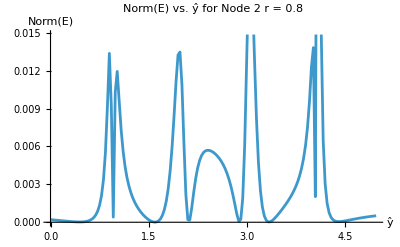

Evaluation time: 18.247597

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat2Array=Range[0,5,0.03];
Δ2NormArray=Table[Δ2Norm[κ]/.{yHat->yHat2Array[[i]]},{i,1,Length@yHat2Array}];
ENorm2Array=Table[NIntegrate[Δ2NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat2Array}];

ListPlot[Transpose@{yHat2Array,ENorm2Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 2\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

### Node 1

```mathematica
𝔸1[κ_]=γ10+Cos[κ]+γ12 Cos[2 κ]+γ13 Cos[3 κ];
𝔹1[κ_]=Sin[κ]+γ12 Sin[2 κ]+γ13 Sin[3 κ];
ℂ1[κ_]=a10+a11 Cos[κ]+a12 Cos[2 κ]+a13 Cos[3 κ]+a14 Cos[4 κ]+a15 Cos[5 κ]+a16 Cos[6 κ];
𝔻1[κ_]=a11 Sin[κ]+a12 Sin[2 κ]+a13 Sin[3 κ]+a14 Sin[4 κ]+a15 Sin[5 κ]+a16 Sin[6 κ];
κBar1Re[κ_]=(𝔸1[κ]*𝔻1[κ]-𝔹1[κ]*ℂ1[κ])/((𝔸1[κ])^2+(𝔹1[κ])^2);
κBar1Im[κ_]=(-𝔸1[κ]*ℂ1[κ]-𝔹1[κ]*𝔻1[κ])/((𝔸1[κ])^2+(𝔹1[κ])^2);
κBar1Norm[κ_]=Abs[κBar1Re[κ]+I*κBar1Im[κ]];
```

```mathematica
Δ1Re[κ_]=(κ*((𝔸1[κ])^2+(𝔹1[κ])^2)-(𝔸1[κ]*𝔻1[κ]-𝔹1[κ]*ℂ1[κ]))^2;
Δ1Im[κ_]=(0*((𝔸1[κ])^2+(𝔹1[κ])^2)-(-𝔸1[κ]*ℂ1[κ]-𝔹1[κ]*𝔻1[κ]))^2;
Δ1Norm[κ_]=(κ-κBar1Norm[κ])^2;
```

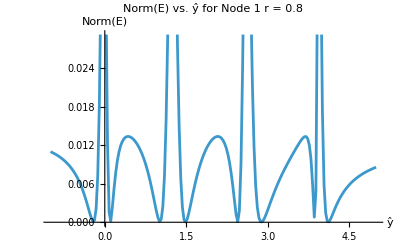

Evaluation time: 24.578653

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat1Array=Range[-1,5,0.03];
Δ1NormArray=Table[Δ1Norm[κ]/.{yHat->yHat1Array[[i]]},{i,1,Length@yHat1Array}];
ENorm1Array=Table[NIntegrate[Δ1NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat1Array}];

ListPlot[Transpose@{yHat1Array,ENorm1Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 1\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

### Node 0

```mathematica
𝔸0[κ_]=1+γ01 Cos[κ]+γ02 Cos[2 κ];
𝔹0[κ_]=γ01 Sin[κ]+γ02 Sin[2 κ];
ℂ0[κ_]=a00+a01 Cos[κ]+a02 Cos[2 κ]+a03 Cos[3 κ]+a04 Cos[4 κ]+a05 Cos[5 κ]+a06 Cos[6 κ];
𝔻0[κ_]=a01 Sin[κ]+a02 Sin[2 κ]+a03 Sin[3 κ]+a04 Sin[4 κ]+a05 Sin[5 κ]+a06 Sin[6 κ];
κBar0Re[κ_]=(𝔸0[κ]*𝔻0[κ]-𝔹0[κ]*ℂ0[κ])/((𝔸0[κ])^2+(𝔹0[κ])^2);
κBar0Im[κ_]=(-𝔸0[κ]*ℂ0[κ]-𝔹0[κ]*𝔻0[κ])/((𝔸0[κ])^2+(𝔹0[κ])^2);
κBar0Norm[κ_]=Abs[κBar0Re[κ]+I*κBar0Im[κ]];
```

```mathematica
Δ0Re[κ_]=(κ*((𝔸0[κ])^2+(𝔹0[κ])^2)-(𝔸0[κ]*𝔻0[κ]-𝔹0[κ]*ℂ0[κ]))^2;
Δ0Im[κ_]=(0*((𝔸0[κ])^2+(𝔹0[κ])^2)-(-𝔸0[κ]*ℂ0[κ]-𝔹0[κ]*𝔻0[κ]))^2;
Δ0Norm[κ_]=(κ-κBar0Norm[κ])^2;
```

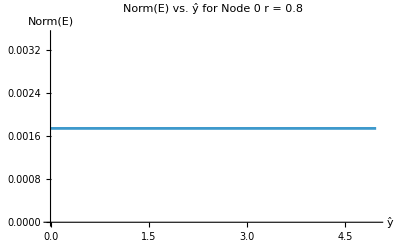

Evaluation time: 147.01748

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat0Array=Range[0,5,0.03];
Δ0NormArray=Table[Δ0Norm[κ]/.{yHat->yHat0Array[[i]]},{i,1,Length@yHat0Array}];
ENorm0Array=Table[NIntegrate[Δ0NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat0Array}];

ListPlot[Transpose@{yHat0Array,ENorm0Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 0\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

## Spectral Function

### Node 2

```mathematica
Clear[yHat]
SF2Re[κ_,yHat_]=κBar2Re[κ];
SF2Im[κ_,yHat_]=κBar2Im[κ];
SF2Norm[κ_,yHat_]=κBar2Norm[κ];
```

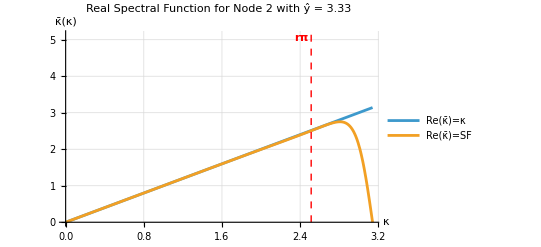

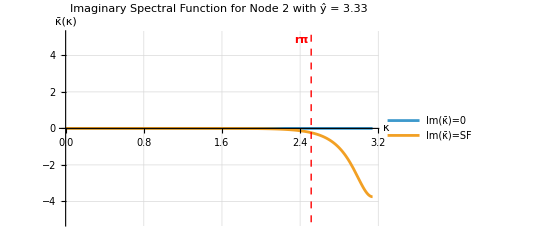

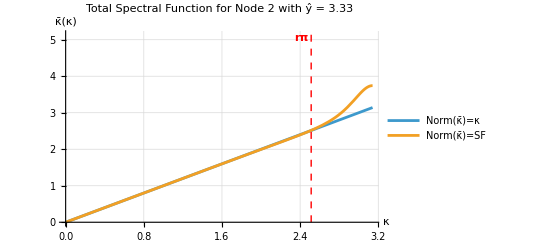

```mathematica
r=0.8;
yHat2List={(*1*)0.45,(*2*)0.96,(*3*)1.59,(*4*)2.13,(*5*)2.88,(*6*)3.33,(*7*)4.05,(*8*)4.41};
yHat=yHat2List[[6]];
Plot[{κ,SF2Re[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
Plot[{0,SF2Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ,SF2Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
```

### Node 1

```mathematica
Clear[yHat]
SF1Re[κ_,yHat_]=κBar1Re[κ];
SF1Im[κ_,yHat_]=κBar1Im[κ];
SF1Norm[κ_,yHat_]=κBar1Norm[κ];
```

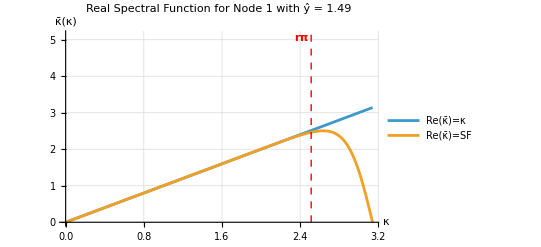

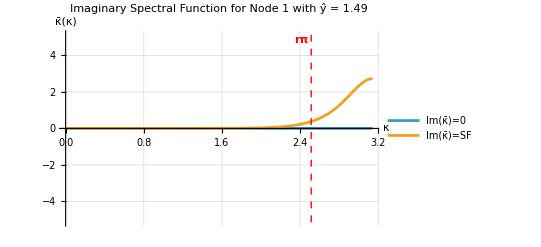

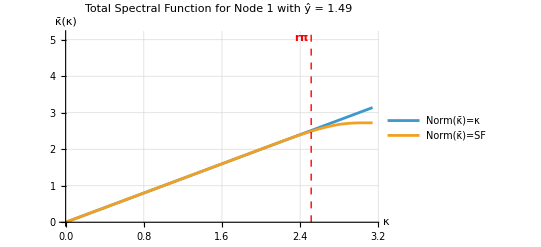

```mathematica
Clear[yHat]
r=0.8;
yHat1List={(*1*)-0.22,(*2*)0.11,(*3*)1.01,(*4*)1.49,(*5*)2.45,(*6*)2.90,(*7*)3.86,(*8*)4.13};
yHat=yHat1List[[4]];
Plot[{κ,SF1Re[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
Plot[{0,SF1Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ,SF1Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
```

### Node 0

```mathematica
Clear[yHat]
SF0Re[κ_,yHat_]=κBar0Re[κ];
SF0Im[κ_,yHat_]=κBar0Im[κ];
SF0Norm[κ_,yHat_]=κBar0Norm[κ];
```

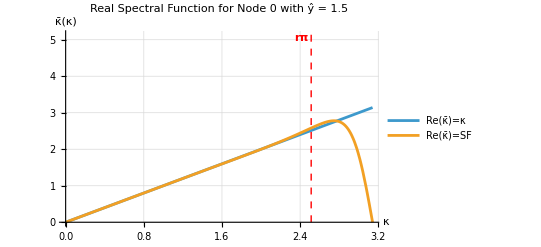

$Aborted

$Aborted

```mathematica
r=0.8;
yHat0List={(*1*)1.50,(*2*)1.59,(*3*)3.12,(*4*)3.27};
yHat=yHat0List[[1]];
Plot[{κ,SF0Re[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Real Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
Plot[{0,SF0Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ,SF0Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π+2},PlotLabel->StringJoin["Total Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.9}]}]
```

## Output Coefficients

### ŷ Definitions

```mathematica
Clear[yHat,yHat2,yHat1,yHat0]

yHat2List={(*1*)0.45,(*2*)0.96,(*3*)1.59,(*4*)2.13,(*5*)2.88,(*6*)3.33,(*7*)4.05,(*8*)4.41};
yHat1List={(*1*)-0.22,(*2*)0.11,(*3*)1.01,(*4*)1.49,(*5*)2.45,(*6*)2.90,(*7*)3.86,(*8*)4.13};
yHat0List={(*1*)1.50,(*2*)1.59,(*3*)3.12,(*4*)3.27}; (*NOT VERIFIED*)

yHat2=yHat2List[[1]];
yHat1=yHat1List[[1]];
yHat0=yHat0List[[1]];
```

### Define Coefficients

```mathematica
Clear[γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26]
Clear[γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06]

{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0)/.{yHat->yHat0};
```

### Luke Output

```mathematica
interiorLuke=interiorCoeffsA8/.{a1->a,a2->b,a3->c};
boundaryLuke={α12->γ01val,β12->γ02val,α21->γ10val,α22->γ12val,β22->γ13val,β31->γ20val,α31->γ21val,α32->γ23val,β32->γ24val,a1->a00val,b1->a01val,c1->a02val,d1->a03val,e1->a04val,f1->a05val,g1->a06val,a2->a10val,b2->a11val,c2->a12val,d2->a13val,e2->a14val,f2->a15val,g2->a16val,a3->a20val,b3->a21val,c3->a22val,d3->a23val,e3->a24val,f3->a25val,g3->a26val};
coeffLuke=Flatten[Join[interiorLuke,boundaryLuke]]
```

{α→0.541269,β→0.0665078,a→0.684259,b→0.207402,c→0.00290475,α12→12.,β12→15.,α21→0.0797504,α22→1.41123,β22→0.143317,β31→0.0168597,α31→0.321393,α32→0.80151,β32→0.15172,a1→-3.95,b1→-15.4,c1→13.75,d1→6.66667,e1→-1.25,f1→0.2,g1→-0.0166667,a2→-0.317403,b2→-1.34783,c2→0.971165,d2→0.746645,e2→-0.0638587,f2→0.0123671,g2→-0.00109031,a3→-0.0723681,b3→-0.611299,c3→-0.431571,d3→0.707783,e3→0.394239,f3→0.0136781,g3→-0.000462342}

### Nate Output

```mathematica
interiorNate=interiorCoeffsA8;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]]
```

{α→0.541269,β→0.0665078,a1→0.684259,a2→0.207402,a3→0.00290475,γ01→12.,γ02→15.,γ10→0.0797504,γ12→1.41123,γ13→0.143317,γ20→0.0168597,γ21→0.321393,γ23→0.80151,γ24→0.15172,a00→-3.95,a01→-15.4,a02→13.75,a03→6.66667,a04→-1.25,a05→0.2,a06→-0.0166667,a10→-0.317403,a11→-1.34783,a12→0.971165,a13→0.746645,a14→-0.0638587,a15→0.0123671,a16→-0.00109031,a20→-0.0723681,a21→-0.611299,a22→-0.431571,a23→0.707783,a24→0.394239,a25→0.0136781,a26→-0.000462342}

## Eigenvalue Spectral Analysis

### Modified Boundary Coefficients for Eigenvalue Analysis

```mathematica
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,8}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,8}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2]
```

{γ12Bar→5.,γ13Bar→3.33333,γ21Bar→0.156754,γ23Bar→1.09913,γ24Bar→0.21623,a11Bar→-2.78333,a12Bar→-2.91667,a13Bar→5.,a14Bar→0.833333,a15Bar→-0.0833333,a16Bar→0.00555556,a17Bar→23.2584 (-0.0797504 a07+a17),a18Bar→23.2584 (-0.0797504 a08+a18),a21Bar→-0.465129,a22Bar→-0.907679,a23Bar→0.78377,a24Bar→0.581108,a25Bar→0.0157679,a26Bar→-0.000330424,a27Bar→17.8707 (-0.0168597 a17+0.0797504 a27),a28Bar→17.8707 (-0.0168597 a18+0.0797504 a28)}

### Build Modified Matrices (needs cleaning badly)

```mathematica
Clear[LHS,RHS]
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],

If[(i-2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i-1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+2==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],
If[(i+1==j)&&(k-i<numBoundaryRows),ToExpression["γ"<>ToString[k-i]<>ToString[k-j]],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}]

k=9; (*Size*)
MatrixForm@LHS[k]

MatrixForm@(LHS[k]/.coeffNate)/.barCoeffs
```

(1 | γ12Bar | γ13Bar | 0 | 0 | 0 | 0 | 0 | 0
γ21Bar | 1 | γ23Bar | γ24Bar | 0 | 0 | 0 | 0 | 0
β | α | 1 | α | β | 0 | 0 | 0 | 0
0 | β | α | 1 | α | β | 0 | 0 | 0
0 | 0 | β | α | 1 | α | β | 0 | 0
0 | 0 | 0 | β | α | 1 | α | β | 0
0 | 0 | 0 | 0 | γ24 | γ23 | 1 | γ21 | γ20
0 | 0 | 0 | 0 | 0 | γ13 | γ12 | 1 | γ10
0 | 0 | 0 | 0 | 0 | 0 | γ02 | γ01 | 1)

(1 | 5. | 3.33333 | 0 | 0 | 0 | 0 | 0 | 0
0.156754 | 1 | 1.09913 | 0.21623 | 0 | 0 | 0 | 0 | 0
0.0665078 | 0.541269 | 1 | 0.541269 | 0.0665078 | 0 | 0 | 0 | 0
0 | 0.0665078 | 0.541269 | 1 | 0.541269 | 0.0665078 | 0 | 0 | 0
0 | 0 | 0.0665078 | 0.541269 | 1 | 0.541269 | 0.0665078 | 0 | 0
0 | 0 | 0 | 0.0665078 | 0.541269 | 1 | 0.541269 | 0.0665078 | 0
0 | 0 | 0 | 0 | 0.15172 | 0.80151 | 1 | 0.321393 | 0.0168597
0 | 0 | 0 | 0 | 0 | 0.143317 | 1.41123 | 1 | 0.0797504
0 | 0 | 0 | 0 | 0 | 0 | 15. | 12. | 1)

```mathematica
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,

If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,

If[(i==k&&j==k),-a00,
If[(i==k&&j==k-1),-a01,
If[(i==k&&j==k-2),-a02,
If[(i==k&&j==k-3),-a03,
If[(i==k&&j==k-4),-a04,
If[(i==k&&j==k-5),-a05,
If[(i==k&&j==k-6),-a06,
If[(i==k-1&&j==k),-a10,
If[(i==k-1&&j==k-1),-a11,
If[(i==k-1&&j==k-2),-a12,
If[(i==k-1&&j==k-3),-a13,
If[(i==k-1&&j==k-4),-a14,
If[(i==k-1&&j==k-5),-a15,
If[(i==k-1&&j==k-6),-a16,
If[(i==k-2&&j==k),-a20,
If[(i==k-2&&j==k-1),-a21,
If[(i==k-2&&j==k-2),-a22,
If[(i==k-2&&j==k-3),-a23,
If[(i==k-2&&j==k-4),-a24,
If[(i==k-2&&j==k-5),-a25,
If[(i==k-2&&j==k-6),-a26,


If[i-3==j,-a3,
If[i-2==j,-a2,
If[i-1==j, -a1,
If[i==j, 0,
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}]

k=11; (*Size*)
MatrixForm@RHS[k]

MatrixForm@(RHS[k]/.coeffNate)/.barCoeffs
```

(a11Bar | a12Bar | a13Bar | a14Bar | a15Bar | a16Bar | 0 | 0 | 0 | 0 | 0
a21Bar | a22Bar | a23Bar | a24Bar | a25Bar | a26Bar | 0 | 0 | 0 | 0 | 0
-a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0 | 0 | 0 | 0
-a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0 | 0 | 0
0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0 | 0
0 | 0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0 | 0
0 | 0 | 0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3 | 0
0 | 0 | 0 | 0 | -a3 | -a2 | -a1 | 0 | a1 | a2 | a3
0 | 0 | 0 | 0 | -a26 | -a25 | -a24 | -a23 | -a22 | -a21 | -a20
0 | 0 | 0 | 0 | -a16 | -a15 | -a14 | -a13 | -a12 | -a11 | -a10
0 | 0 | 0 | 0 | -a06 | -a05 | -a04 | -a03 | -a02 | -a01 | -a00)

(-2.78333 | -2.91667 | 5. | 0.833333 | -0.0833333 | 0.00555556 | 0 | 0 | 0 | 0 | 0
-0.465129 | -0.907679 | 0.78377 | 0.581108 | 0.0157679 | -0.000330424 | 0 | 0 | 0 | 0 | 0
-0.207402 | -0.684259 | 0 | 0.684259 | 0.207402 | 0.00290475 | 0 | 0 | 0 | 0 | 0
-0.00290475 | -0.207402 | -0.684259 | 0 | 0.684259 | 0.207402 | 0.00290475 | 0 | 0 | 0 | 0
0 | -0.00290475 | -0.207402 | -0.684259 | 0 | 0.684259 | 0.207402 | 0.00290475 | 0 | 0 | 0
0 | 0 | -0.00290475 | -0.207402 | -0.684259 | 0 | 0.684259 | 0.207402 | 0.00290475 | 0 | 0
0 | 0 | 0 | -0.00290475 | -0.207402 | -0.684259 | 0 | 0.684259 | 0.207402 | 0.00290475 | 0
0 | 0 | 0 | 0 | -0.00290475 | -0.207402 | -0.684259 | 0 | 0.684259 | 0.207402 | 0.00290475
0 | 0 | 0 | 0 | 0.000462342 | -0.0136781 | -0.394239 | -0.707783 | 0.431571 | 0.611299 | 0.0723681
0 | 0 | 0 | 0 | 0.00109031 | -0.0123671 | 0.0638587 | -0.746645 | -0.971165 | 1.34783 | 0.317403
0 | 0 | 0 | 0 | 0.0166667 | -0.2 | 1.25 | -6.66667 | -13.75 | 15.4 | 3.95)

### Plot Eigenvalue Spectra

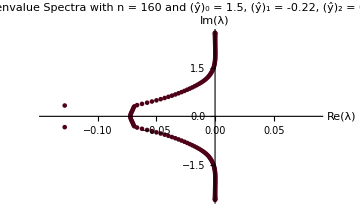

```mathematica
k=160;
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=-Eigenvalues[mat];

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->{All,All},PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0/5,yHat1/5,yHat2/5]]
```

## Dendro Output

### Hide

```mathematica
derivativeOrder=1;
interiorOrder=n;
totalBoundRows=numBoundaryRows;
freeInteriorParameters={};
freeBoundaryParameters={};
RHSInteriorList=RHSPars;
interiorParametersValues=interiorCoeffsA6/.{α->alpha,β->beta};
boundaryParametersValues=boundaryLuke/.{α12->gamma01,β12->gamma02,α21->gamma10,α22->gamma12,β22->gamma13,β31->gamma20,α31->gamma21,α32->gamma23,β32->gamma24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};
LHSBoundaryList={gamma01,gamma02,gamma10,gamma12,gamma13,gamma20,gamma21,gamma23,gamma24};
RHSBoundaryList={a00,a01,a02,a03,a04,a05,a06,a10,a11,a12,a13,a14,a15,a16,a20,a21,a22,a23,a24,a25,a26};
(*Don't need to mess with these until we incorporate this procedure with James's filtering*)
filterIntCoeff;
filterBoundCoeff;
filterIntParam;
filterBoundParam;
filtering=False;
(*boundary={α12->γ01,β12->γ02,α21->γ10,α22->γ12,β22->γ13,β31->γ20,α31->γ21,α32->γ23,β32->γ24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};*)
```

```mathematica
(*****************Print coefficients in Dendro-GR Format*****************)
If[derivativeOrder==1,
LHSName="P1";
RHSName="Q1";
nth="1st";
coeffs="D_coeffs";
order="First",
If[derivativeOrder==2,
LHSName="P2";
RHSName="Q2";
nth="2nd";
coeffs="D_coeffs";
order="Second"]];
If[LHSBandCount==3,
LHSStructure="T",
If[LHSBandCount==5,
LHSStructure="P"]];

(*Convert Mathematica expression syntax to C/C++ expression syntax*)
convertToCCode[expr_]:=Module[{str},str=ToString[expr,InputForm];
(*Add ".0" to standalone integers but not to variables with numbers*)
(*Formatting adjustments to match C/C++ syntax*)str=StringReplace[str,{" "->"","*"->" * ","/"->" / ","+"->" + ","-"->" - ","^"->" ^ "}];
str]
(*Function to generate the line of C/C++ code to define the fixed variables*)
generateCAssignment[rule_]:=Module[{variable,expression,cCode,cAssignment},
variable=ToString[rule[[1]]];
expression=rule[[2]];
cCode=convertToCCode[expression];
cAssignment="double "<>variable<>" = "<>cCode<>";";
cAssignment
]






(*Initial Block*)
initialBlock=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order"}];
initialBlock2=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order","Filtered"}];

(*Free Parameters Block*)
freeParameters=Join[freeInteriorParameters,freeBoundaryParameters];
numFreePars=Length[freeParameters];
alphaPrint=StringReplace[generateCAssignment[Select[interiorParametersValues,#[[1]]===alpha&][[1]]],"alpha"->"alpha0"];
freeParPrints={};
If[numFreePars>0,
For[i=1,i<=numFreePars,i++,
AppendTo[freeParPrints,StringJoin[{"\n\t\tdouble ",ToString[freeParameters[[i]]]," = ",coeffs,"[",ToString[i],"];"}]]]]
freeParametersBlock=StringJoin[{"\t",alphaPrint,"\n\t\tdouble alpha = alpha0 + ",coeffs,"[0];",freeParPrints}];

(*Filter*)
freeParPrints2={};
freeParametersBlock2=StringJoin[{"\t","\n\t\tdouble alpha = ","F_coeffs","[0];",If[LHSBandCount==5,StringJoin["\n\t\tdouble beta = ","F_coeffs","[1];"],""]}];

(*Fixed Parameters Block*)
(*Create a list of the solved fixed parameters in C/C++ syntax*)
interiorParametersValues3=DeleteCases[interiorParametersValues,Rule[alpha,_]];
interiorParameterPrints=Table[
generateCAssignment[interiorParametersValues3[[i]]],
{i,1,Length[interiorParametersValues]-1}
];
boundaryParameterPrints=Table[
generateCAssignment[boundaryParametersValues[[i]]],
{i,1,Length[boundaryParametersValues]}
];
(*For filtered coefficients*)
interiorParameterPrints2=Table[
generateCAssignment[filterIntCoeff[[i]]],
{i,1,Length[filterIntCoeff]}
];
boundaryParameterPrints2=Table[
generateCAssignment[filterBoundCoeff[[i]]],
{i,1,Length[filterBoundCoeff]}
];
(*Print the coefficients in a single block of text rather than individual lines*)
fixedParametersBlockD=StringJoin["\t\t",Riffle[Join[interiorParameterPrints,boundaryParameterPrints],"\n\t\t"]];
fixedParametersBlockD2=StringJoin["\t\t",Riffle[Join[interiorParameterPrints2,boundaryParameterPrints2],"\n\t\t"]];

(*Structure Block*)
(*LHS Boundary*)
PDiagBoundary="";
LHSRowList=ToExpression[GatherBy[LHSBoundaryList,StringDrop[ToString[#],5]~StringTake~1&]];
For[i=1,i<=Length[LHSRowList],i++,
If[i==1,PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t","{1.0, ",StringDrop[ToString[LHSRowList[[i]]],1],","]];
If[i==2,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1}]],1],","]]];
If[i==3,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{","0.0, ",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t",StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
If[i>=4,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],StringDrop[StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
];
(*LHS Filter Boundary*)
RDiagBoundary="";
For[i=1,i<=Length@filterBoundParam,i++,
If[i==1,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha, beta},"]];
];
If[i==2,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha 1.0, alpha, beta},"]];
];
If[i>=3,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],"alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],"beta, alpha, 1.0, alpha, beta},"]];
];
];

(*LHS Interior*)
If[LHSBandCount==3,
PDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
PDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];
(*LHS Filter Interior*)
If[LHSBandCount==3,
RDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
RDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];

(*RHS Boundary*)
QDiagBoundary="";
RHSRowList=ToExpression[GatherBy[RHSBoundaryList,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList],i++,QDiagBoundary=StringJoin[QDiagBoundary,"\n\t\t\t",ToString[RHSRowList[[i]]],","]]
(*RHS Filter Boundary*)
SDiagBoundary="";
RHSRowList2=ToExpression[GatherBy[filterBoundParam,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList2],i++,SDiagBoundary=StringJoin[SDiagBoundary,"\n\t\t\t",ToString[RHSRowList2[[i]]]]]

(*RHS Interior*)
QDiagInterior={};
len=(2*Length[RHSInteriorList]+1);
If[derivativeOrder==1,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[-RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"0.0"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]
],
If[derivativeOrder==2,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[-RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"t1"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]]]]

(*RHS Filter Interior*)
SDiagInterior={};
newFilterIntParam=Drop[filterIntParam,1];
len=(2*Length[newFilterIntParam]+1);
For[i=1,i<=len,i++,
If[i<=Length[newFilterIntParam],PrependTo[SDiagInterior,ToString[newFilterIntParam[[i]]]<>"/"<>ToString[2]<>".0"]];
If[i==(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,"a0"]];
If[i>(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,ToString[newFilterIntParam[[i-Length[newFilterIntParam]-1]]]<>"/"<>ToString[2]<>".0"]]
]


PDiagBoundaryStr=StringDrop[StringDrop[PDiagBoundary,1],-1];
PDiagInteriorStr=StringDrop[StringDrop[PDiagInterior,1],-1];
RDiagBoundaryStr=StringDrop[StringDrop[RDiagBoundary,1],-1];
RDiagInteriorStr=StringDrop[StringDrop[RDiagInterior,1],-1];
QDiagBoundaryStr=StringDrop[StringDrop[QDiagBoundary,1],-1];
QDiagInteriorStr=StringDrop[StringDrop[ToString[QDiagInterior],1],-1];
SDiagBoundaryStr=StringDrop[SDiagBoundary,1];
SDiagInteriorStr=StringDrop[StringDrop[ToString[SDiagInterior],1],-1];

(*Subscript[t, 1] is the middle RHS Interior Coefficient for Second Derivatives*)
t1List={};
For[i=1,i<=Length[RHSInteriorList],i++,
AppendTo[t1List,ToString[RHSInteriorList[[i]]]<>"/"<>ToString[i^2]<>".0"]
];
If[derivativeOrder==1,
t1="",
If[derivativeOrder==2,
t1=StringJoin["-2.0 * ("<>StringDrop[StringDrop[ToString[t1List],1],-1]<>")"]]];


If[filtering,
filterFinalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock2,"(\n","\tconst std::vector<double>& ","F_coeffs",") {\n","\t",freeParametersBlock2,"\n\n",fixedParametersBlockD2,"\n\n","\t\t// boundary elements for R matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","R","DiagBoundary{\n",RDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for R matrix for ",nth," derivative\n","\t\tstd::vector<double> ","R","DiagInterior{\n","\t\t\t",RDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for S matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","S","DiagBoundary\n",SDiagBoundaryStr,"\n","\t\t;\n\n","\t\t// diagonal elements for S matrix for ",nth," derivative\n","\t\tstd::vector<double> ","S","DiagInterior{\n","\t\t\t",SDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t","R","DiagInterior, ","S","DiagInterior, ","S","DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}"}];
]

finalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock,"(\n","\tconst std::vector<double>& ",coeffs,") {\n","\t",freeParametersBlock,"\n\n",fixedParametersBlockD,"\n\n","\t\t// boundary elements for P matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",LHSName,"DiagBoundary{\n",PDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for P matrix for ",nth," derivative\n","\t\tstd::vector<double> ",LHSName,"DiagInterior{\n","\t\t\t",PDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",RHSName,"DiagBoundary{\n",QDiagBoundaryStr,"\n","\t\t};\n\n",If[derivativeOrder==1,t1,If[derivativeOrder==2,"\t\tdouble t1 = "<>t1<>";\n"]],"\t\t// diagonal elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<double> ",RHSName,"DiagInterior{\n","\t\t\t",QDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t",LHSName,"DiagInterior, ",LHSName,"DiagBoundary, ",RHSName,"DiagInterior, ",RHSName,"DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}",If[filtering,"\n\n"<>filterFinalBlock,""]}];
```

GatherBy::list: List expected at position 1 in GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&].

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Drop::drop: Cannot drop positions 1 through 1 in filterIntParam.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

StringDrop::drop: Cannot drop positions 1 through 1 in "".

### Show

```mathematica
outExt="h";
(*Print header*)
Print[Style["Dendro-Ready Coefficients (Copied to clipboard):",Bold,FontSize->24]];
Print[finalBlock];
(*Copy the block of text to the user's clipboard*)
CopyToClipboard[finalBlock];

(*Save to output file*)
fileName=StringJoin[{"BYU_A6","_yHat0_",ToString[yHat0],"_yHat1_",ToString[yHat1],"_yHat2_",ToString[yHat2],".",outExt}];
Export[fileName,finalBlock,"Text"];
Print[StringJoin[{"Saved to file: ",fileName}]]
```

Dendro-Ready Coefficients (Copied to clipboard):

MatrixDiagonalEntries* BYUDerivsP121R3DiagonalsFirstOrder(
	const std::vector<double>& D_coeffs) {
		double alpha0 = 0.5770460201292381;
		double alpha = alpha0 + D_coeffs[0];

		double beta = 0.08900836845092142;
		double a1 = 0.6517078440898839;
		double a2 = 0.24815882627035918;
		double a3 = 0.006009630649852392;
		double gamma01 = 9.82050086297005;
		double gamma02 = 10.282867809058313;
		double gamma10 = 0.08185064221829087;
		double gamma12 = 1.6890627481714804;
		double gamma13 = 0.4961478931388701;
		double gamma20 = 0.017918887158094664;
		double gamma21 = 0.33500390219730425;
		double gamma23 = 0.7548768581531722;
		double gamma24 = 0.13667343083285768;
		double a00 =  - 3.73445251380582;
		double a01 =  - 10.765902315893966;
		double a02 = 11.158777481815811;
		double a03 = 3.8932795799881186;
		double a04 =  - 0.6389839738157034;
		double a05 = 0.09587727397420936;
		double a06 =  - 0.008595531676508965;
		double a10 =  - 0.31850909623427476;
		double a11 =  - 1.396944235854646;
		double a12 = 0.5364016058704685;
		double a13 = 1.1223168928950014;
		double a14 = 0.059450604503400145;
		double a15 =  - 0.0027438380250710795;
		double a16 = 0.00002806684476978311;
		double a20 =  - 0.07670359108573083;
		double a21 =  - 0.6273443641711278;
		double a22 =  - 0.37833992259630045;
		double a23 = 0.7128462614236629;
		double a24 = 0.3572245284141374;
		double a25 = 0.012842138314361781;
		double a26 =  - 0.0005250502990408262;

		// boundary elements for P matrix for 1st derivative
		std::vector<std::vector<double>> P1DiagBoundary{
			{1.0, gamma01, gamma02},
			{gamma10, 1.0, gamma12, gamma13},
			{gamma20, gamma21, 1.0, gamma23, gamma24}
		};

		// diagonal elements for P matrix for 1st derivative
		std::vector<double> P1DiagInterior{
			beta, alpha, 1.0, alpha, beta
		};

		// boundary elements for Q matrix for 1st derivative
		std::vector<std::vector<double>> Q1DiagBoundary{
			{a00, a01, a02, a03, a04, a05, a06},
			{a10, a11, a12, a13, a14, a15, a16},
			{a20, a21, a22, a23, a24, a25, a26}
		};

		// diagonal elements for Q matrix for 1st derivative
		std::vector<double> Q1DiagInterior{
			-a3, -a2, -a1, 0.0, a1, a2, a3
		};

		// store the entries for matrix creation
		MatrixDiagonalEntries* diagEntries = new
			MatrixDiagonalEntries{
				P1DiagInterior, P1DiagBoundary, Q1DiagInterior, Q1DiagBoundary
			};
		return diagEntries;
	}

Saved to file: BYU_P4_yHat0_1.89_yHat1_1.65_yHat2_1.14.h

# Second Derivative

# P4 (A4) Scheme

## Initialization

The matrix system of equations we are solving for this scheme is:
	P=(1
γ_10
γ_20
0
0
0
0 γ_01
1
γ_21
β
0
0
0 γ_02
γ_12
1
α
γ_24
0
0 0
γ_13
γ_23
1
γ_23
γ_13
0 0
0
γ_24
α
1
γ_12
γ_02 0
0
0
β
γ_21
1
γ_01 0
0
0
0
γ_20
γ_10
1)
	Q=(a_00
a_10
a_20
a_3
a_26
a_16
a_06 a_01
a_11
a_21
a_2
a_25
a_15
a_05 a_02
a_12
a_22
a_1
a_24
a_14
a_04 a_03
a_13
a_23
-2s
a_23
a_13
a_03 a_04
a_14
a_24
a_1
a_22
a_12
a_02 a_05
a_15
a_25
a_2
a_21
a_11
a_01 a_06
a_16
a_26
a_3
a_20
a_10
a_00)
Note that:
	s=a_1+a_2+a_3

```mathematica
(*From KimInteriorOptimization.nb, one day to be merged with this one. Or I could DumpSave[] in that notebook and then Get[] here.*)
interiorCoeffsA42nd={α->0.4917593294116515,β->0.052107304747970096,a1->0.2456096922476715,a2->0.42112296480247163,a3->0.017514635206853885};

(*If you have the .mx files in the same directory as this notebook, these will let you skip the long computation of defining bdCoeffs under the "Solve for Boundary Coefficients" section*)
Get["A4_2nd_interiorCoeffs.mx"]
Get["A4_2nd_bdCoeffs0.mx"]
Get["A4_2nd_bdCoeffs1.mx"]
Get["A4_2nd_bdCoeffs2.mx"]
```

## General Extrapolation Polynomial

The only settings the user should have to change for a different (second derivative) scheme are:
	- LHSBandCount
	- n
	- freeInteriorPars
	- yDeriv
For the P4 (A4) scheme, we have:
	LHSBandCount = 5
	n = 4
	freeInteriorPars = 3
	yDeriv = 9

```mathematica
(*User chooses these parameters, the rest is calculated from these*)
LHSBandCount=5; (*3 for tridiagonal, 5 for pentadiagonal*)
n=4; (*order of the scheme*)
freeInteriorPars=3; (*number of free parameters used for Kim's optimization on the interior*)
yDeriv=9; (*(d^n P)/dx^n(ŷ)=0 from Kim 2024 Eq. 10, this is n in that equation*) (*provide constraints on what the user can choose for this. Upper bound should be polynomialorder to prevent the matrix from being singular, and lower bound should be order·2 I think.*)

LHSPars=Switch[LHSBandCount,3,{α},5,{α,β}];
RHSPars=Table[ToExpression[StringJoin["a",ToString[i]]],{i,1,Ceiling[n/2]-Length@LHSPars+freeInteriorPars}];
numBoundaryRows=Length@RHSPars;
fOrder=(2*Length@RHSPars)+1;
fppOrder=LHSBandCount+(numBoundaryRows-(LHSBandCount-1)/2);
PolynomialOrder=fOrder+fppOrder;


rowf1=Join[{1},Table[0,{i,1,PolynomialOrder}]];
rowf=Table[Table[i^j,{j,0,PolynomialOrder}],{i,1,fOrder-1}];
rowfpp1=Join[{0,0,2},Table[0,{i,3,PolynomialOrder}]];
rowfpp=Table[Table[j (j-1) i^(j-2),{j,0,PolynomialOrder}],{i,1,fppOrder-1}];
rowyHat=Join[Table[0,{i,1,yDeriv}],Table[(i!)/((i-yDeriv)!) yHat^(i-yDeriv),{i,yDeriv,PolynomialOrder}]];

matf=PrependTo[rowf,rowf1];
matfpp=PrependTo[rowfpp,rowfpp1];
matfCombined=Join[matf,matfpp];
LMat=AppendTo[matfCombined,rowyHat];

pVec=Table[ToExpression[StringJoin["p",ToString[i]]],{i,0,PolynomialOrder}];
fVec=Join[Table[ToExpression[StringJoin["f",ToString[i]]],{i,0,fOrder-1}],Table[ToExpression[StringJoin["fpp",ToString[i]]],{i,0,fppOrder-1}],{0}];

pCoeffs=Solve[LMat.pVec==fVec,pVec][[1]];

yHatSingularities=(Transpose@Solve[Det[LMat]==0,yHat])[[1]]//N;
P[x_]=Total[Table[pVec[[i+1]]*x^i,{i,0,PolynomialOrder}]]/.pCoeffs;

Print["System:\n",MatrixForm[LMat]," ",MatrixForm[pVec]," = ",MatrixForm[fVec]]
Print["Singularities:\n",MatrixForm[yHatSingularities]]
(*Print["Coefficients:\n",MatrixForm[pCoeffs]]*)
```

System:
(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 4 | 8 | 16 | 32 | 64 | 128 | 256 | 512 | 1024 | 2048 | 4096 | 8192
1 | 3 | 9 | 27 | 81 | 243 | 729 | 2187 | 6561 | 19683 | 59049 | 177147 | 531441 | 1594323
1 | 4 | 16 | 64 | 256 | 1024 | 4096 | 16384 | 65536 | 262144 | 1048576 | 4194304 | 16777216 | 67108864
1 | 5 | 25 | 125 | 625 | 3125 | 15625 | 78125 | 390625 | 1953125 | 9765625 | 48828125 | 244140625 | 1220703125
1 | 6 | 36 | 216 | 1296 | 7776 | 46656 | 279936 | 1679616 | 10077696 | 60466176 | 362797056 | 2176782336 | 13060694016
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 6 | 12 | 20 | 30 | 42 | 56 | 72 | 90 | 110 | 132 | 156
0 | 0 | 2 | 12 | 48 | 160 | 480 | 1344 | 3584 | 9216 | 23040 | 56320 | 135168 | 319488
0 | 0 | 2 | 18 | 108 | 540 | 2430 | 10206 | 40824 | 157464 | 590490 | 2165130 | 7794468 | 27634932
0 | 0 | 2 | 24 | 192 | 1280 | 7680 | 43008 | 229376 | 1179648 | 5898240 | 28835840 | 138412032 | 654311424
0 | 0 | 2 | 30 | 300 | 2500 | 18750 | 131250 | 875000 | 5625000 | 35156250 | 214843750 | 1289062500 | 7617187500
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 362880 | 3628800 yHat | 19958400 yHat^2 | 79833600 yHat^3 | 259459200 yHat^4) (p0
p1
p2
p3
p4
p5
p6
p7
p8
p9
p10
p11
p12
p13) = (f0
f1
f2
f3
f4
f5
f6
fpp0
fpp1
fpp2
fpp3
fpp4
fpp5
0)

Singularities:
(yHat→2.42303
yHat→3.57697
yHat→1.35669
yHat→4.64331)

## Solve for Boundary Coefficients

Goal:
	Solve a system of equations for bdCoeffsList2 in terms of the optimization free parameter ŷ
Variables:
	fVars2: List of f_i and f_i' variables that will appear in the shifted stencil for Node 2
	bdCoeffsList2: List of boundary coefficients that will appear in the shifted stencil for Node 2
	schemeShifted: The shifted scheme for Node 2 (Kim 2024 Eq. 13a)
	schemeCentered: The centered scheme for Node 2 in terms of the extrapolation polynomial P(x) (Kim 2024 Eq. 12a)
		NOTE: To make the Collect[] process easier, we write these schemes as LHS-RHS=0 rather than the usual LHS=RHS.
	schemeNode3: The scheme for Node 3, which only depends on interiorCoeffsP4
	SOLfp5: The solution to Node 3’s scheme equation for f_5' in terms of fVars2
	eq: Scheme equation where the coefficient terms from schemeCentered and schemeShifted are set equal to each other
	coeffEqs2: System of equations with each of the coefficient terms equal to each other
	bdCoeffs2: Solution to the system of equations for bdCoeffsList2 in terms of ŷ
Process:
	1. Initialize the necessary equations.
	2. We want schemeShifted and schemeCentered to both be in terms of fVars2 with some coefficients. Due to the presence of P(x) terms in schemeCentered, it is in terms of fVars2 as well as f_5'. We eliminate the dependence on f_5' by using Node 3’s scheme to solve for f_5' in terms of fVars2.
	3. Now that schemeShifted and schemeCentered are both in terms of fVars2, we construct a system of equations by equating the coefficient in front of each term of fVars2 in schemeCentered with the corresponding coefficient in front of the same term in schemeShifted.
	4. We solve this system of equations for bdCoeffsList2 in terms of interiorCoeffsP4 (which are substituted in) and the optimization free parameter ŷ.
		NOTE: In the standard scheme approach, we set γ_22=1 to ensure the main diagonal of the LHS matrix is all 1’s. When solving this system of equations, we must include γ_22 so that bdCoeffsList2 and fVars2 have the same length since this allows us to find a unique solution to the system of equations. We apply the normal condition later on.
	5. OPTIONAL: We may save the variable bdCoeffs2 to a binary file in the current directory. This is helpful to avoid having to run this process multiple times, as it can become computationally expensive.
Differences:
	For Node 1 and Node 0, the entire process translates directly with a few changes. fVars, bdCoeffsList, schemeShifted, and schemeCentered all change, as we are considering the scheme for a different row, but the equations have the same structure. The main notable difference is in Step 2; In addition to substituting in the solution from Node 3 for f_5' in terms of the other fVars, we must also do the same for f_4' (Nodes 1 and 0) and f_3' (Node 0) using Nodes 2 and 1, respectively.

### Node 2

```mathematica
(*----------STEP 1----------*)
a0=-2 (a1+a2+a3);
fVars2={fpp0,fpp1,fpp2,fpp3,fpp4,f0,f1,f2,f3,f4,f5,f6};
bdCoeffsList2={γ20,γ21,γ22,γ23,γ24,a20,a21,a22,a23,a24,a25,a26};
schemeShifted=γ20 fpp0+γ21 fpp1+γ22 fpp2+γ23 fpp3+γ24 fpp4-(a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6); (*==0*)
schemeCentered=β fpp0+α fpp1+fpp2+α fpp3+β fpp4-(a3 P[-1]+a2 f0+a1 f1+a0 f2+a1 f3+a2 f4+a3 f5); (*==0*)

(*----------STEP 2----------*)
schemeNode3=β fpp1+α fpp2+fpp3+α fpp4+β fpp5==a3 f0+a2 f1+a1 f2+a0 f3+a1 f4+a2 f5+a3 f6;
SOLfpp5=Solve[schemeNode3,fpp5][[1,1]]/.interiorCoeffsA42nd;
schemeCentered=schemeCentered/.SOLfpp5;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars2];

(*----------STEP 4----------*)
coeffEqs2=Table[Coefficient[eq,fVars2[[i]]]==0,{i,1,Length@fVars2}];
bdCoeffs2=(Solve[coeffEqs2,bdCoeffsList2][[1]])/.interiorCoeffsA42nd;

(*----------STEP 5----------*)
DumpSave["A4_2nd_bdCoeffs2.mx","Global`bdCoeffs2"]
```

{Global`bdCoeffs2}

### Node 1

```mathematica
(*----------STEP 1----------*)
a0=-2 (a1+a2+a3);
fVars1={fpp0,fpp1,fpp2,fpp3,f0,f1,f2,f3,f4,f5,f6};
bdCoeffsList1={γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14,a15,a16};
schemeShifted=γ10 fpp0+γ11 fpp1+γ12 fpp2+γ13 fpp3-(a10 f0+a11 f1+a12 f2+a13 f3+a14 f4+a15 f5+a16 f6); (*==0*)
schemeCentered=β P''[-1]+α fpp0+fpp1+α fpp2+β fpp3-(a3 P[-2]+a2 P[-1]+a1 f0+a0 f1+a1 f2+a2 f3+a3 f4); (*==0*)

(*----------STEP 2----------*)
schemeNode3=β fpp1+α fpp2+fpp3+α fpp4+β fpp5==a3 f0+a2 f1+a1 f2+a0 f3+a1 f4+a2 f5+a3 f6;
schemeNode2=γ20 fpp0+γ21 fpp1+γ22 fpp2+γ23 fpp3+γ24 fpp4==a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6;

SOLfpp5=Solve[schemeNode3,fpp5][[1,1]]/.interiorCoeffsA42nd;
SOLfpp4=Solve[schemeNode2,fpp4][[1,1]]/.bdCoeffs2;
schemeCentered=schemeCentered/.SOLfpp5/.SOLfpp4;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars1];

(*----------STEP 4----------*)
coeffEqs1=Table[Coefficient[eq,fVars1[[i]]]==0,{i,1,Length@fVars1}];
bdCoeffs1=(Solve[coeffEqs1,bdCoeffsList1][[1]])/.interiorCoeffsA42nd;

(*----------STEP 5----------*)
DumpSave["A4_2nd_bdCoeffs1.mx","Global`bdCoeffs1"]
```

{Global`bdCoeffs1}

### Node 0

```mathematica
(*----------STEP 1----------*)
a0=-2 (a1+a2+a3);
fVars0={fpp0,fpp1,fpp2,f0,f1,f2,f3,f4,f5,f6};
bdCoeffsList0={γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06};
schemeShifted=γ00 fpp0+γ01 fpp1+γ02 fpp2-(a00 f0+a01 f1+a02 f2+a03 f3+a04 f4+a05 f5+a06 f6); (*==0*)
schemeCentered=β P''[-2]+α P''[-1]+fpp0+α fpp1+β fpp2-(a3 P[-3]+a2 P[-2]+a1 P[-1]+a0 f0+a1 f1+a2 f2+a3 f3); (*==0*)

(*----------STEP 2----------*)
schemeNode3=β fpp1+α fpp2+fpp3+α fpp4+β fpp5==a3 f0+a2 f1+a1 f2+a0 f3+a1 f4+a2 f5+a3 f6;
schemeNode2=γ20 fpp0+γ21 fpp1+γ22 fpp2+γ23 fpp3+γ24 fpp4==a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6;
schemeNode1=γ10 fpp0+γ11 fpp1+γ12 fpp2+γ13 fpp3==a10 f0+a11 f1+a12 f2+a13 f3+a14 f4+a15 f5+a16 f6;

SOLfpp5=Solve[schemeNode3,fpp5][[1,1]]/.interiorCoeffsA42nd;
SOLfpp4=Solve[schemeNode2,fpp4][[1,1]]/.bdCoeffs2;
SOLfpp3=Solve[schemeNode1,fpp3][[1,1]]/.bdCoeffs1;
schemeCentered=schemeCentered/.SOLfpp5/.SOLfpp4/.SOLfpp3;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars0];

(*----------STEP 4----------*)
coeffEqs0=Table[Coefficient[eq,fVars0[[i]]]==0,{i,1,Length@fVars0}];
bdCoeffs0=(Solve[coeffEqs0,bdCoeffsList0][[1]])/.interiorCoeffsA42nd;

(*----------STEP 5----------*)
DumpSave["A4_2nd_bdCoeffs0.mx","Global`bdCoeffs0"]
```

{Global`bdCoeffs0}

## Optimize ŷ

### Set and Normalize Coefficients

We normalize the coefficients so that the main diagonal of the LHS matrix is all 1’s, but we leave the coefficients in terms of the optimization free parameter ŷ so that we can optimize over it.

```mathematica
Clear[γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26]
Clear[γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06]

{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}=1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2;
{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}=1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1;
{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}=1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0;
```

### Node 2

```mathematica
𝔸2[κ_]=γ20+γ21 Cos[κ]+Cos[2 κ]+γ23 Cos[3 κ]+γ24 Cos[4 κ];
𝔹2[κ_]=γ21 Sin[κ]+Sin[2 κ]+γ23 Sin[3 κ]+γ24 Sin[4 κ];
ℂ2[κ_]=a20+a21 Cos[κ]+a22 Cos[2 κ]+a23 Cos[3 κ]+a24 Cos[4 κ]+a25 Cos[5 κ]+a26 Cos[6 κ];
𝔻2[κ_]=a21 Sin[κ]+a22 Sin[2 κ]+a23 Sin[3 κ]+a24 Sin[4 κ]+a25 Sin[5 κ]+a26 Sin[6 κ];
κBar2Re[κ_]=(-𝔸2[κ]*ℂ2[κ]-𝔹2[κ]*𝔻2[κ])/((𝔸2[κ])^2+(𝔹2[κ])^2);
κBar2Im[κ_]=(𝔹2[κ]*ℂ2[κ]-𝔸2[κ]*𝔻2[κ])/((𝔸2[κ])^2+(𝔹2[κ])^2);
κBar2Norm[κ_]=Abs[κBar2Re[κ]+I*κBar2Im[κ]];
```

```mathematica
Δ2Re[κ_]=(κ^2*((𝔸2[κ])^2+(𝔹2[κ])^2)-(-𝔸2[κ]*ℂ2[κ]-𝔹2[κ]*𝔻2[κ]))^2;
Δ2Im[κ_]=(0*((𝔸2[κ])^2+(𝔹2[κ])^2)-(𝔹2[κ]*ℂ2[κ]-𝔸2[κ]*𝔻2[κ]))^2;
Δ2Norm[κ_]=(κ^2-κBar2Norm[κ])^2;
```

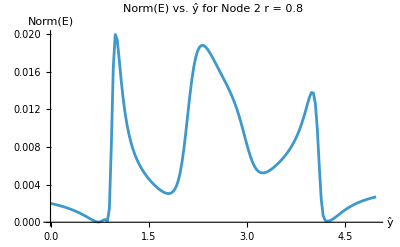

Evaluation time: 11.917406

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat2Array=Range[0,5,0.03];
Δ2NormArray=Table[Δ2Norm[κ]/.{yHat->yHat2Array[[i]]},{i,1,Length@yHat2Array}];
ENorm2Array=Table[NIntegrate[Δ2NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat2Array}];

ListPlot[Transpose@{yHat2Array,ENorm2Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 2\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

### Node 1

```mathematica
𝔸1[κ_]=γ10+Cos[κ]+γ12 Cos[2 κ]+γ13 Cos[3 κ];
𝔹1[κ_]=Sin[κ]+γ12 Sin[2 κ]+γ13 Sin[3 κ];
ℂ1[κ_]=a10+a11 Cos[κ]+a12 Cos[2 κ]+a13 Cos[3 κ]+a14 Cos[4 κ]+a15 Cos[5 κ]+a16 Cos[6 κ];
𝔻1[κ_]=a11 Sin[κ]+a12 Sin[2 κ]+a13 Sin[3 κ]+a14 Sin[4 κ]+a15 Sin[5 κ]+a16 Sin[6 κ];
κBar1Re[κ_]=(-𝔸1[κ]*ℂ1[κ]-𝔹1[κ]*𝔻1[κ])/((𝔸1[κ])^2+(𝔹1[κ])^2);
κBar1Im[κ_]=(𝔹1[κ]*ℂ1[κ]-𝔸1[κ]*𝔻1[κ])/((𝔸1[κ])^2+(𝔹1[κ])^2);
κBar1Norm[κ_]=Abs[κBar1Re[κ]+I*κBar1Im[κ]];
```

```mathematica
Δ1Re[κ_]=(κ^2*((𝔸1[κ])^2+(𝔹1[κ])^2)-(-𝔸1[κ]*ℂ1[κ]-𝔹1[κ]*𝔻1[κ]))^2;
Δ1Im[κ_]=(0*((𝔸1[κ])^2+(𝔹1[κ])^2)-(𝔹1[κ]*ℂ1[κ]-𝔸1[κ]*𝔻1[κ]))^2;
Δ1Norm[κ_]=(κ^2-κBar1Norm[κ])^2;
```

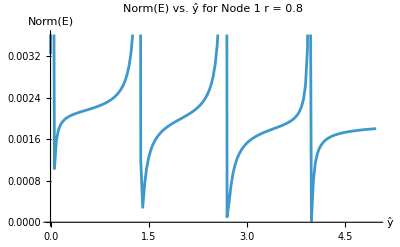

Evaluation time: 14.803836

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat1Array=Range[0,5,0.03];
Δ1NormArray=Table[Δ1Norm[κ]/.{yHat->yHat1Array[[i]]},{i,1,Length@yHat1Array}];
ENorm1Array=Table[NIntegrate[Δ1NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat1Array}];

ListPlot[Transpose@{yHat1Array,ENorm1Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 1\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

### Node 0

```mathematica
𝔸0[κ_]=1+γ01 Cos[κ]+γ02 Cos[2 κ];
𝔹0[κ_]=γ01 Sin[κ]+γ02 Sin[2 κ];
ℂ0[κ_]=a00+a01 Cos[κ]+a02 Cos[2 κ]+a03 Cos[3 κ]+a04 Cos[4 κ]+a05 Cos[5 κ]+a06 Cos[6 κ];
𝔻0[κ_]=a01 Sin[κ]+a02 Sin[2 κ]+a03 Sin[3 κ]+a04 Sin[4 κ]+a05 Sin[5 κ]+a06 Sin[6 κ];
κBar0Re[κ_]=(-𝔸0[κ]*ℂ0[κ]-𝔹0[κ]*𝔻0[κ])/((𝔸0[κ])^2+(𝔹0[κ])^2);
κBar0Im[κ_]=(𝔹0[κ]*ℂ0[κ]-𝔸0[κ]*𝔻0[κ])/((𝔸0[κ])^2+(𝔹0[κ])^2);
κBar0Norm[κ_]=Abs[κBar0Re[κ]+I*κBar0Im[κ]];
```

```mathematica
Δ0Re[κ_]=(κ^2*((𝔸0[κ])^2+(𝔹0[κ])^2)-(-𝔸0[κ]*ℂ0[κ]-𝔹0[κ]*𝔻0[κ]))^2;
Δ0Im[κ_]=(0*((𝔸0[κ])^2+(𝔹0[κ])^2)-(𝔹0[κ]*ℂ0[κ]-𝔸0[κ]*𝔻0[κ]))^2;
Δ0Norm[κ_]=(κ^2-κBar0Norm[κ])^2;
```

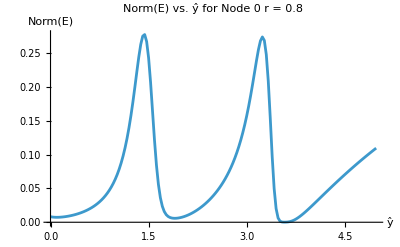

Evaluation time: 146.369393

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat0Array=Range[0,5,0.03];
Δ0NormArray=Table[Δ0Norm[κ]/.{yHat->yHat0Array[[i]]},{i,1,Length@yHat0Array}];
ENorm0Array=Table[NIntegrate[Δ0NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat0Array}];

ListPlot[Transpose@{yHat0Array,ENorm0Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 0\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

## Spectral Function

### Node 2

```mathematica
Clear[yHat]
SF2Re[κ_,yHat_]=κBar2Re[κ];
SF2Im[κ_,yHat_]=κBar2Im[κ];
SF2Norm[κ_,yHat_]=κBar2Norm[κ];
```

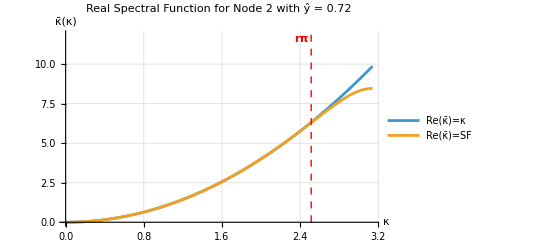

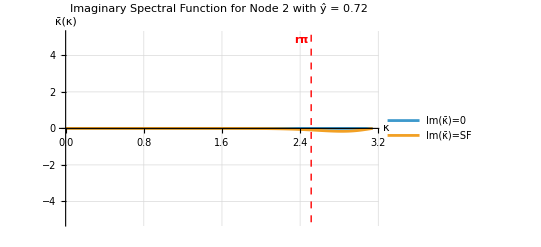

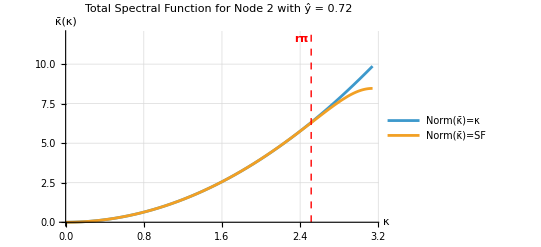

```mathematica
r=0.8;
yHat2List={(*1*)0.72,(*2*)0.87,(*3*)1.80,(*4*)3.24,(*5*)4.23};
yHat=yHat2List[[1]];
Plot[{κ^2,SF2Re[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Real Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
Plot[{0,SF2Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ^2,SF2Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Total Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
```

### Node 1

```mathematica
Clear[yHat]
SF1Re[κ_,yHat_]=κBar1Re[κ];
SF1Im[κ_,yHat_]=κBar1Im[κ];
SF1Norm[κ_,yHat_]=κBar1Norm[κ];
```

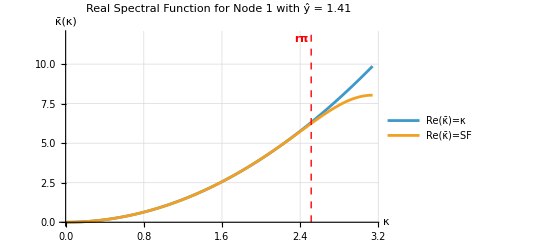

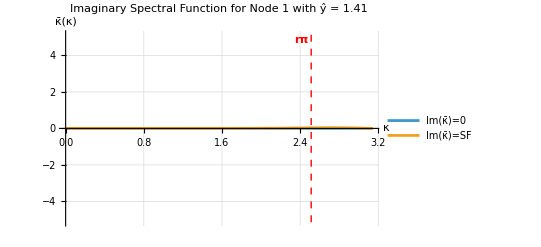

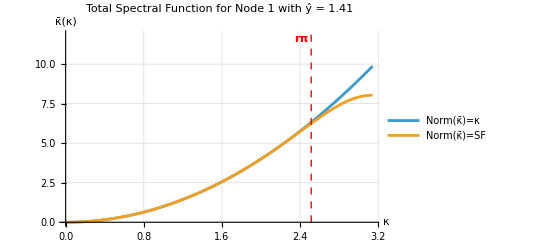

```mathematica
Clear[yHat]
r=0.8;
yHat1List={(*1*)0.06,(*2*)1.41,(*3*)2.70,(*7*)3.99};
yHat=yHat1List[[2]];
Plot[{κ^2,SF1Re[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Real Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
Plot[{0,SF1Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ^2,SF1Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Total Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
```

### Node 0

```mathematica
Clear[yHat]
SF0Re[κ_,yHat_]=κBar0Re[κ];
SF0Im[κ_,yHat_]=κBar0Im[κ];
SF0Norm[κ_,yHat_]=κBar0Norm[κ];
```

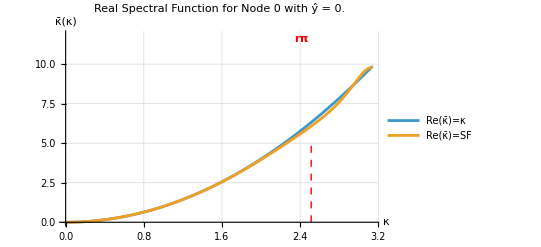

$Aborted

$Aborted

```mathematica
r=0.8;
yHat0List={(*1*)0.00,(*2*)1.89,(*3*)3.57};
yHat=yHat0List[[1]];
Plot[{κ^2,SF0Re[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Real Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
Plot[{0,SF0Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ^2,SF0Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Total Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
```

## Output Coefficients

### ŷ Definitions

```mathematica
Clear[yHat,yHat2,yHat1,yHat0]

yHat2List={(*1*)0.72,(*2*)0.87,(*3*)1.80,(*4*)3.24,(*5*)4.23};
yHat1List={(*1*)0.06,(*2*)1.41,(*3*)2.70,(*7*)3.99};
yHat0List={(*1*)0.00,(*2*)1.89,(*3*)3.57};

yHat2=yHat2List[[3]];
yHat1=yHat1List[[5]];
yHat0=yHat0List[[1]];

yHat0=3.57;
yHat1=2.70;
yHat2=3.24;
```

Part::partw: Part 5 of {0.06,1.41,2.7,3.99} does not exist.

### Define Coefficients

```mathematica
Clear[γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26]
Clear[γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06]

{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0)/.{yHat->yHat0};
```

### Luke Output

```mathematica
interiorLuke=interiorCoeffsA42nd/.{a1->a,a2->b,a3->c};
boundaryLuke={α12->γ01val,β12->γ02val,α21->γ10val,α22->γ12val,β22->γ13val,β31->γ20val,α31->γ21val,α32->γ23val,β32->γ24val,a1->a00val,b1->a01val,c1->a02val,d1->a03val,e1->a04val,f1->a05val,g1->a06val,a2->a10val,b2->a11val,c2->a12val,d2->a13val,e2->a14val,f2->a15val,g2->a16val,a3->a20val,b3->a21val,c3->a22val,d3->a23val,e3->a24val,f3->a25val,g3->a26val};
coeffLuke=Flatten[Join[interiorLuke,boundaryLuke]]
```

{α→0.491759,β→0.0521073,a→0.24561,b→0.421123,c→0.0175146,α12→13.2196,β12→16.3267,α21→0.0457767,α22→2.72939,β22→0.886428,β31→0.00752359,α31→0.216563,α32→1.23415,β32→0.275688,a1→13.2778,b1→-6.82136,c1→-29.3086,d1→26.7499,e1→-4.80561,f1→1.03574,g1→-0.127907,a2→0.779215,b2→1.71784,c2→-5.13353,d2→1.96132,e2→0.712182,f2→-0.0386948,g2→0.00166864,a3→0.142915,b3→0.757836,c3→-0.551974,d3→-1.58092,e3→1.06643,f3→0.17112,g3→-0.00540812}

### Nate Output

```mathematica
interiorNate=interiorCoeffsA42nd;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]]
```

{α→0.491759,β→0.0521073,a1→0.24561,a2→0.421123,a3→0.0175146,γ01→13.2196,γ02→16.3267,γ10→0.0457767,γ12→2.72939,γ13→0.886428,γ20→0.00752359,γ21→0.216563,γ23→1.23415,γ24→0.275688,a00→13.2778,a01→-6.82136,a02→-29.3086,a03→26.7499,a04→-4.80561,a05→1.03574,a06→-0.127907,a10→0.779215,a11→1.71784,a12→-5.13353,a13→1.96132,a14→0.712182,a15→-0.0386948,a16→0.00166864,a20→0.142915,a21→0.757836,a22→-0.551974,a23→-1.58092,a24→1.06643,a25→0.17112,a26→-0.00540812}

## Eigenvalue Spectral Analysis

### Modified Boundary Coefficients for Eigenvalue Analysis

```mathematica
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,6}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,6}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2]
```

{γ12Bar→5.01962,γ13Bar→2.24496,γ21Bar→0.094682,γ23Bar→1.97395,γ24Bar→0.499967,a11Bar→5.14142,a12Bar→-9.60329,a13Bar→1.866,a14Bar→2.3608,a15Bar→-0.218075,a16Bar→0.0190547,a21Bar→0.862333,a22Bar→0.529086,a23Bar→-3.45162,a24Bar→1.72172,a25Bar→0.321864,a26Bar→-0.0103051}

### Build Modified Matrices (needs cleaning badly)

```mathematica
Clear[LHS,RHS]
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],

If[(i==k&&j==k-1),ToExpression["γ"<>ToString[1]<>ToString[2]<>"Bar"],
If[(i==k&&j==k-2),ToExpression["γ"<>ToString[1]<>ToString[3]<>"Bar"],
If[(i==k-1&&j==k),ToExpression["γ"<>ToString[2]<>ToString[1]<>"Bar"],
If[(i==k-1&&j==k-2),ToExpression["γ"<>ToString[2]<>ToString[3]<>"Bar"],
If[(i==k-1&&j==k-3),ToExpression["γ"<>ToString[2]<>ToString[4]<>"Bar"],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}]

k=9; (*Size*)
MatrixForm@LHS[k]

MatrixForm@(LHS[k]/.coeffNate)/.barCoeffs
```

(1 | γ12Bar | γ13Bar | 0 | 0 | 0 | 0 | 0 | 0
γ21Bar | 1 | γ23Bar | γ24Bar | 0 | 0 | 0 | 0 | 0
β | α | 1 | α | β | 0 | 0 | 0 | 0
0 | β | α | 1 | α | β | 0 | 0 | 0
0 | 0 | β | α | 1 | α | β | 0 | 0
0 | 0 | 0 | β | α | 1 | α | β | 0
0 | 0 | 0 | 0 | β | α | 1 | α | β
0 | 0 | 0 | 0 | 0 | γ24Bar | γ23Bar | 1 | γ21Bar
0 | 0 | 0 | 0 | 0 | 0 | γ13Bar | γ12Bar | 1)

(1 | 5.01962 | 2.24496 | 0 | 0 | 0 | 0 | 0 | 0
0.094682 | 1 | 1.97395 | 0.499967 | 0 | 0 | 0 | 0 | 0
0.0521073 | 0.491759 | 1 | 0.491759 | 0.0521073 | 0 | 0 | 0 | 0
0 | 0.0521073 | 0.491759 | 1 | 0.491759 | 0.0521073 | 0 | 0 | 0
0 | 0 | 0.0521073 | 0.491759 | 1 | 0.491759 | 0.0521073 | 0 | 0
0 | 0 | 0 | 0.0521073 | 0.491759 | 1 | 0.491759 | 0.0521073 | 0
0 | 0 | 0 | 0 | 0.0521073 | 0.491759 | 1 | 0.491759 | 0.0521073
0 | 0 | 0 | 0 | 0 | 0.499967 | 1.97395 | 1 | 0.094682
0 | 0 | 0 | 0 | 0 | 0 | 2.24496 | 5.01962 | 1)

```mathematica
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,

If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,

If[(i==k&&j==k),a11Bar,
If[(i==k&&j==k-1),a12Bar,
If[(i==k&&j==k-2),a13Bar,
If[(i==k&&j==k-3),a14Bar,
If[(i==k&&j==k-4),a15Bar,
If[(i==k&&j==k-5),a16Bar,
If[(i==k-1&&j==k),a21Bar,
If[(i==k-1&&j==k-1),a22Bar,
If[(i==k-1&&j==k-2),a23Bar,
If[(i==k-1&&j==k-3),a24Bar,
If[(i==k-1&&j==k-4),a25Bar,
If[(i==k-1&&j==k-5),a26Bar,


If[i-3==j,a3,
If[i-2==j,a2,
If[i-1==j,a1,
If[i==j,-2*(a1+a2+a3),
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}]

k=11; (*Size*)
MatrixForm@RHS[k]

MatrixForm@(RHS[k]/.coeffNate)/.barCoeffs
```

(a11Bar | a12Bar | a13Bar | a14Bar | a15Bar | a16Bar | 0 | 0 | 0 | 0 | 0
a21Bar | a22Bar | a23Bar | a24Bar | a25Bar | a26Bar | 0 | 0 | 0 | 0 | 0
a2 | a1 | -2 (a1+a2+a3) | a1 | a2 | a3 | 0 | 0 | 0 | 0 | 0
a3 | a2 | a1 | -2 (a1+a2+a3) | a1 | a2 | a3 | 0 | 0 | 0 | 0
0 | a3 | a2 | a1 | -2 (a1+a2+a3) | a1 | a2 | a3 | 0 | 0 | 0
0 | 0 | a3 | a2 | a1 | -2 (a1+a2+a3) | a1 | a2 | a3 | 0 | 0
0 | 0 | 0 | a3 | a2 | a1 | -2 (a1+a2+a3) | a1 | a2 | a3 | 0
0 | 0 | 0 | 0 | a3 | a2 | a1 | -2 (a1+a2+a3) | a1 | a2 | a3
0 | 0 | 0 | 0 | 0 | a3 | a2 | a1 | -2 (a1+a2+a3) | a1 | a2
0 | 0 | 0 | 0 | 0 | a26Bar | a25Bar | a24Bar | a23Bar | a22Bar | a21Bar
0 | 0 | 0 | 0 | 0 | a16Bar | a15Bar | a14Bar | a13Bar | a12Bar | a11Bar)

(5.14142 | -9.60329 | 1.866 | 2.3608 | -0.218075 | 0.0190547 | 0 | 0 | 0 | 0 | 0
0.862333 | 0.529086 | -3.45162 | 1.72172 | 0.321864 | -0.0103051 | 0 | 0 | 0 | 0 | 0
0.421123 | 0.24561 | -1.36849 | 0.24561 | 0.421123 | 0.0175146 | 0 | 0 | 0 | 0 | 0
0.0175146 | 0.421123 | 0.24561 | -1.36849 | 0.24561 | 0.421123 | 0.0175146 | 0 | 0 | 0 | 0
0 | 0.0175146 | 0.421123 | 0.24561 | -1.36849 | 0.24561 | 0.421123 | 0.0175146 | 0 | 0 | 0
0 | 0 | 0.0175146 | 0.421123 | 0.24561 | -1.36849 | 0.24561 | 0.421123 | 0.0175146 | 0 | 0
0 | 0 | 0 | 0.0175146 | 0.421123 | 0.24561 | -1.36849 | 0.24561 | 0.421123 | 0.0175146 | 0
0 | 0 | 0 | 0 | 0.0175146 | 0.421123 | 0.24561 | -1.36849 | 0.24561 | 0.421123 | 0.0175146
0 | 0 | 0 | 0 | 0 | 0.0175146 | 0.421123 | 0.24561 | -1.36849 | 0.24561 | 0.421123
0 | 0 | 0 | 0 | 0 | -0.0103051 | 0.321864 | 1.72172 | -3.45162 | 0.529086 | 0.862333
0 | 0 | 0 | 0 | 0 | 0.0190547 | -0.218075 | 2.3608 | 1.866 | -9.60329 | 5.14142)

### Plot Eigenvalue Spectra

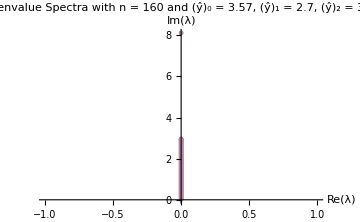

```mathematica
k=160;
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
(*eigs=(Eigenvalues[mat])^1/π;*)
eigs=(Eigenvalues[mat])^(1/2);

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->All,PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0/5,yHat1/5,yHat2/5]]
```

## Dendro Output

### Hide

```mathematica
derivativeOrder=2;
interiorOrder=n;
totalBoundRows=numBoundaryRows;
freeInteriorParameters={};
freeBoundaryParameters={};
RHSInteriorList=RHSPars;
interiorParametersValues=interiorCoeffsA42nd/.{α->alpha,β->beta};
boundaryParametersValues=boundaryLuke/.{α12->gamma01,β12->gamma02,α21->gamma10,α22->gamma12,β22->gamma13,β31->gamma20,α31->gamma21,α32->gamma23,β32->gamma24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};
LHSBoundaryList={gamma01,gamma02,gamma10,gamma12,gamma13,gamma20,gamma21,gamma23,gamma24};
RHSBoundaryList={a00,a01,a02,a03,a04,a05,a06,a10,a11,a12,a13,a14,a15,a16,a20,a21,a22,a23,a24,a25,a26};
(*Don't need to mess with these until we incorporate this procedure with James's filtering*)
filterIntCoeff;
filterBoundCoeff;
filterIntParam;
filterBoundParam;
filtering=False;
(*boundary={α12->γ01,β12->γ02,α21->γ10,α22->γ12,β22->γ13,β31->γ20,α31->γ21,α32->γ23,β32->γ24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};*)
```

```mathematica
(*****************Print coefficients in Dendro-GR Format*****************)
If[derivativeOrder==1,
LHSName="P1";
RHSName="Q1";
nth="1st";
coeffs="D_coeffs";
order="First",
If[derivativeOrder==2,
LHSName="P2";
RHSName="Q2";
nth="2nd";
coeffs="D_coeffs";
order="Second"]];
If[LHSBandCount==3,
LHSStructure="T",
If[LHSBandCount==5,
LHSStructure="P"]];

(*Convert Mathematica expression syntax to C/C++ expression syntax*)
convertToCCode[expr_]:=Module[{str},str=ToString[expr,InputForm];
(*Add ".0" to standalone integers but not to variables with numbers*)
(*Formatting adjustments to match C/C++ syntax*)str=StringReplace[str,{" "->"","*"->" * ","/"->" / ","+"->" + ","-"->" - ","^"->" ^ "}];
str]
(*Function to generate the line of C/C++ code to define the fixed variables*)
generateCAssignment[rule_]:=Module[{variable,expression,cCode,cAssignment},
variable=ToString[rule[[1]]];
expression=rule[[2]];
cCode=convertToCCode[expression];
cAssignment="double "<>variable<>" = "<>cCode<>";";
cAssignment
]






(*Initial Block*)
initialBlock=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order"}];
initialBlock2=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order","Filtered"}];

(*Free Parameters Block*)
freeParameters=Join[freeInteriorParameters,freeBoundaryParameters];
numFreePars=Length[freeParameters];
alphaPrint=StringReplace[generateCAssignment[Select[interiorParametersValues,#[[1]]===alpha&][[1]]],"alpha"->"alpha0"];
freeParPrints={};
If[numFreePars>0,
For[i=1,i<=numFreePars,i++,
AppendTo[freeParPrints,StringJoin[{"\n\t\tdouble ",ToString[freeParameters[[i]]]," = ",coeffs,"[",ToString[i],"];"}]]]]
freeParametersBlock=StringJoin[{"\t",alphaPrint,"\n\t\tdouble alpha = alpha0 + ",coeffs,"[0];",freeParPrints}];

(*Filter*)
freeParPrints2={};
freeParametersBlock2=StringJoin[{"\t","\n\t\tdouble alpha = ","F_coeffs","[0];",If[LHSBandCount==5,StringJoin["\n\t\tdouble beta = ","F_coeffs","[1];"],""]}];

(*Fixed Parameters Block*)
(*Create a list of the solved fixed parameters in C/C++ syntax*)
interiorParametersValues3=DeleteCases[interiorParametersValues,Rule[alpha,_]];
interiorParameterPrints=Table[
generateCAssignment[interiorParametersValues3[[i]]],
{i,1,Length[interiorParametersValues]-1}
];
boundaryParameterPrints=Table[
generateCAssignment[boundaryParametersValues[[i]]],
{i,1,Length[boundaryParametersValues]}
];
(*For filtered coefficients*)
interiorParameterPrints2=Table[
generateCAssignment[filterIntCoeff[[i]]],
{i,1,Length[filterIntCoeff]}
];
boundaryParameterPrints2=Table[
generateCAssignment[filterBoundCoeff[[i]]],
{i,1,Length[filterBoundCoeff]}
];
(*Print the coefficients in a single block of text rather than individual lines*)
fixedParametersBlockD=StringJoin["\t\t",Riffle[Join[interiorParameterPrints,boundaryParameterPrints],"\n\t\t"]];
fixedParametersBlockD2=StringJoin["\t\t",Riffle[Join[interiorParameterPrints2,boundaryParameterPrints2],"\n\t\t"]];

(*Structure Block*)
(*LHS Boundary*)
PDiagBoundary="";
LHSRowList=ToExpression[GatherBy[LHSBoundaryList,StringDrop[ToString[#],5]~StringTake~1&]];
For[i=1,i<=Length[LHSRowList],i++,
If[i==1,PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t","{1.0, ",StringDrop[ToString[LHSRowList[[i]]],1],","]];
If[i==2,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1}]],1],","]]];
If[i==3,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{","0.0, ",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t",StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
If[i>=4,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],StringDrop[StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
];
(*LHS Filter Boundary*)
RDiagBoundary="";
For[i=1,i<=Length@filterBoundParam,i++,
If[i==1,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha, beta},"]];
];
If[i==2,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha 1.0, alpha, beta},"]];
];
If[i>=3,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],"alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],"beta, alpha, 1.0, alpha, beta},"]];
];
];

(*LHS Interior*)
If[LHSBandCount==3,
PDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
PDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];
(*LHS Filter Interior*)
If[LHSBandCount==3,
RDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
RDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];

(*RHS Boundary*)
QDiagBoundary="";
RHSRowList=ToExpression[GatherBy[RHSBoundaryList,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList],i++,QDiagBoundary=StringJoin[QDiagBoundary,"\n\t\t\t",ToString[RHSRowList[[i]]],","]]
(*RHS Filter Boundary*)
SDiagBoundary="";
RHSRowList2=ToExpression[GatherBy[filterBoundParam,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList2],i++,SDiagBoundary=StringJoin[SDiagBoundary,"\n\t\t\t",ToString[RHSRowList2[[i]]]]]

(*RHS Interior*)
QDiagInterior={};
len=(2*Length[RHSInteriorList]+1);
If[derivativeOrder==1,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[-RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"0.0"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]
],
If[derivativeOrder==2,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"t1"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]]]]

(*RHS Filter Interior*)
SDiagInterior={};
newFilterIntParam=Drop[filterIntParam,1];
len=(2*Length[newFilterIntParam]+1);
For[i=1,i<=len,i++,
If[i<=Length[newFilterIntParam],PrependTo[SDiagInterior,ToString[newFilterIntParam[[i]]]<>"/"<>ToString[2]<>".0"]];
If[i==(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,"a0"]];
If[i>(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,ToString[newFilterIntParam[[i-Length[newFilterIntParam]-1]]]<>"/"<>ToString[2]<>".0"]]
]


PDiagBoundaryStr=StringDrop[StringDrop[PDiagBoundary,1],-1];
PDiagInteriorStr=StringDrop[StringDrop[PDiagInterior,1],-1];
RDiagBoundaryStr=StringDrop[StringDrop[RDiagBoundary,1],-1];
RDiagInteriorStr=StringDrop[StringDrop[RDiagInterior,1],-1];
QDiagBoundaryStr=StringDrop[StringDrop[QDiagBoundary,1],-1];
QDiagInteriorStr=StringDrop[StringDrop[ToString[QDiagInterior],1],-1];
SDiagBoundaryStr=StringDrop[SDiagBoundary,1];
SDiagInteriorStr=StringDrop[StringDrop[ToString[SDiagInterior],1],-1];

(*Subscript[t, 1] is the middle RHS Interior Coefficient for Second Derivatives*)
t1List={};
For[i=1,i<=Length[RHSInteriorList],i++,
AppendTo[t1List,ToString[RHSInteriorList[[i]]]]
];
If[derivativeOrder==1,
t1="",
If[derivativeOrder==2,
t1=StringJoin["-2.0 * ("<>ToString[Total[t1List]]<>")"]]];


If[filtering,
filterFinalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock2,"(\n","\tconst std::vector<double>& ","F_coeffs",") {\n","\t",freeParametersBlock2,"\n\n",fixedParametersBlockD2,"\n\n","\t\t// boundary elements for R matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","R","DiagBoundary{\n",RDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for R matrix for ",nth," derivative\n","\t\tstd::vector<double> ","R","DiagInterior{\n","\t\t\t",RDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for S matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","S","DiagBoundary\n",SDiagBoundaryStr,"\n","\t\t;\n\n","\t\t// diagonal elements for S matrix for ",nth," derivative\n","\t\tstd::vector<double> ","S","DiagInterior{\n","\t\t\t",SDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t","R","DiagInterior, ","S","DiagInterior, ","S","DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}"}];
]

finalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock,"(\n","\tconst std::vector<double>& ",coeffs,") {\n","\t",freeParametersBlock,"\n\n",fixedParametersBlockD,"\n\n","\t\t// boundary elements for P matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",LHSName,"DiagBoundary{\n",PDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for P matrix for ",nth," derivative\n","\t\tstd::vector<double> ",LHSName,"DiagInterior{\n","\t\t\t",PDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",RHSName,"DiagBoundary{\n",QDiagBoundaryStr,"\n","\t\t};\n\n",If[derivativeOrder==1,t1,If[derivativeOrder==2,"\t\tdouble t1 = "<>t1<>";\n"]],"\t\t// diagonal elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<double> ",RHSName,"DiagInterior{\n","\t\t\t",QDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t",LHSName,"DiagInterior, ",LHSName,"DiagBoundary, ",RHSName,"DiagInterior, ",RHSName,"DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}",If[filtering,"\n\n"<>filterFinalBlock,""]}];
```

GatherBy::list: List expected at position 1 in GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&].

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Drop::drop: Cannot drop positions 1 through 1 in filterIntParam.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

StringDrop::drop: Cannot drop positions 1 through 1 in "".

### Show

```mathematica
outExt="h";
(*Print header*)
Print[Style["Dendro-Ready Coefficients (Copied to clipboard):",Bold,FontSize->24]];
Print[finalBlock];
(*Copy the block of text to the user's clipboard*)
CopyToClipboard[finalBlock];

(*Save to output file*)
fileName=StringJoin[{"BYU_A4_2nd","_yHat0_",ToString[yHat0],"_yHat1_",ToString[yHat1],"_yHat2_",ToString[yHat2],".",outExt}];
Export[fileName,finalBlock,"Text"];
Print[StringJoin[{"Saved to file: ",fileName}]]
```

Dendro-Ready Coefficients (Copied to clipboard):

MatrixDiagonalEntries* BYUDerivsP4R3DiagonalsSecondOrder(
	const std::vector<double>& D_coeffs) {
		double alpha0 = 0.4917593294116515;
		double alpha = alpha0 + D_coeffs[0];

		double beta = 0.052107304747970096;
		double a1 = 0.2456096922476715;
		double a2 = 0.42112296480247163;
		double a3 = 0.017514635206853885;
		double gamma01 = 12.591315362048217;
		double gamma02 = 15.084784378502926;
		double gamma10 = 0.04577667520869812;
		double gamma12 = 2.729394168475708;
		double gamma13 = 0.8864282136850647;
		double gamma20 = 0.010921427140866557;
		double gamma21 = 0.2834351283963115;
		double gamma23 = 0.7199728999288171;
		double gamma24 = 0.11937767266180463;
		double a00 = 12.874331545332872;
		double a01 =  - 7.791236348900909;
		double a02 =  - 25.746221106082196;
		double a03 = 24.030231590355;
		double a04 =  - 4.139878085038264;
		double a05 = 0.8841382958263313;
		double a06 =  - 0.11136589149817189;
		double a10 = 0.7792149930252243;
		double a11 = 1.717844024789377;
		double a12 =  - 5.133534136228278;
		double a13 = 1.9613187453898757;
		double a14 = 0.7121824953413769;
		double a15 =  - 0.038694764010443694;
		double a16 = 0.0016686416993604049;
		double a20 = 0.20186732531628773;
		double a21 = 0.7305871669560142;
		double a22 =  - 1.3289567001530833;
		double a23 =  - 0.27972025346441187;
		double a24 = 0.6127265401353884;
		double a25 = 0.06539469405721846;
		double a26 =  - 0.0018987728473575086;

		// boundary elements for P matrix for 2nd derivative
		std::vector<std::vector<double>> P2DiagBoundary{
			{1.0, gamma01, gamma02},
			{gamma10, 1.0, gamma12, gamma13},
			{gamma20, gamma21, 1.0, gamma23, gamma24}
		};

		// diagonal elements for P matrix for 2nd derivative
		std::vector<double> P2DiagInterior{
			beta, alpha, 1.0, alpha, beta
		};

		// boundary elements for Q matrix for 2nd derivative
		std::vector<std::vector<double>> Q2DiagBoundary{
			{a00, a01, a02, a03, a04, a05, a06},
			{a10, a11, a12, a13, a14, a15, a16},
			{a20, a21, a22, a23, a24, a25, a26}
		};

		double t1 = -2.0 * (a1 + a2 + a3);
		// diagonal elements for Q matrix for 2nd derivative
		std::vector<double> Q2DiagInterior{
			a3, a2, a1, t1, a1, a2, a3
		};

		// store the entries for matrix creation
		MatrixDiagonalEntries* diagEntries = new
			MatrixDiagonalEntries{
				P2DiagInterior, P2DiagBoundary, Q2DiagInterior, Q2DiagBoundary
			};
		return diagEntries;
	}

Saved to file: BYU_A4_2nd_yHat0_0._yHat1_2.7_yHat2_1.8.h

# P4 (B4) Scheme

## Initialization

The matrix system of equations we are solving for this scheme is:
	P=(1
γ_10
γ_20
0
0
0
0
0
0 γ_01
1
γ_21
γ_31
0
0
0
0
0 γ_02
γ_12
1
γ_32
β
0
0
0
0 0
γ_13
γ_23
1
α
γ_35
0
0
0 0
0
γ_24
γ_34
1
γ_34
γ_24
0
0 0
0
0
γ_35
α
1
γ_23
γ_13
0 0
0
0
0
β
γ_32
1
γ_12
γ_02 0
0
0
0
0
γ_31
γ_21
1
γ_01 0
0
0
0
0
0
γ_20
γ_10
1)
	Q=(a_00
a_10
a_20
a_30
a_4
a_38
a_28
a_18
a_08 a_01
a_11
a_21
a_31
a_3
a_37
a_27
a_17
a_07 a_02
a_12
a_22
a_32
a_2
a_36
a_26
a_16
a_06 a_03
a_13
a_23
a_33
a_1
a_35
a_25
a_15
a_05 a_04
a_14
a_24
a_34
-2s
a_34
a_24
a_14
a_04 a_05
a_15
a_25
a_35
a_1
a_33
a_23
a_13
a_03 a_06
a_16
a_26
a_36
a_2
a_32
a_22
a_12
a_02 a_07
a_17
a_27
a_37
a_3
a_31
a_21
a_11
a_01 a_08
a_18
a_28
a_38
a_4
a_30
a_20
a_10
a_00 )
Note that:
	s=a_1+a_2+a_3+a_4

```mathematica
(*From KimInteriorOptimization.nb, one day to be merged with this one. Or I could DumpSave[] in that notebook and then Get[] here.*)
interiorCoeffsB42nd={α->0.5443196687355368,β->0.07728851013567789,a1->0.10624114531946292,a2->0.44820542026997306,a3->0.040353966028400544,a4->-0.0011895101820331873};

(*If you have the .mx files in the same directory as this notebook, these will let you skip the long computation of defining bdCoeffs under the "Solve for Boundary Coefficients" section*)
Get["B4_2nd_interiorCoeffs.mx"]
Get["B4_2nd_bdCoeffs0.mx"]
Get["B4_2nd_bdCoeffs1.mx"]
Get["B4_2nd_bdCoeffs2.mx"]
Get["B4_2nd_bdCoeffs3.mx"]
```

## General Extrapolation Polynomial

The only settings the user should have to change for a different (second derivative) scheme are:
	- LHSBandCount
	- n
	- freeInteriorPars
	- yDeriv
For the P4 (A4) scheme, we have:
	LHSBandCount = 5
	n = 4
	freeInteriorPars = 4
	yDeriv = 13

```mathematica
(*User chooses these parameters, the rest is calculated from these*)
LHSBandCount=5; (*3 for tridiagonal, 5 for pentadiagonal*)
n=4; (*order of the scheme*)
freeInteriorPars=4; (*number of free parameters used for Kim's optimization on the interior*)
yDeriv=13; (*(d^n P)/dx^n(ŷ)=0 from Kim 2024 Eq. 10, this is n in that equation*) (*provide constraints on what the user can choose for this. Upper bound should be polynomialorder to prevent the matrix from being singular, and lower bound should be order·2 I think.*)

LHSPars=Switch[LHSBandCount,3,{α},5,{α,β}];
RHSPars=Table[ToExpression[StringJoin["a",ToString[i]]],{i,1,Ceiling[n/2]-Length@LHSPars+freeInteriorPars}];
numBoundaryRows=Length@RHSPars;
fOrder=(2*Length@RHSPars)+1;
fppOrder=LHSBandCount+(numBoundaryRows-(LHSBandCount-1)/2);
PolynomialOrder=fOrder+fppOrder;


rowf1=Join[{1},Table[0,{i,1,PolynomialOrder}]];
rowf=Table[Table[i^j,{j,0,PolynomialOrder}],{i,1,fOrder-1}];
rowfpp1=Join[{0,0,2},Table[0,{i,3,PolynomialOrder}]];
rowfpp=Table[Table[j (j-1) i^(j-2),{j,0,PolynomialOrder}],{i,1,fppOrder-1}];
rowyHat=Join[Table[0,{i,1,yDeriv}],Table[(i!)/((i-yDeriv)!) yHat^(i-yDeriv),{i,yDeriv,PolynomialOrder}]];

matf=PrependTo[rowf,rowf1];
matfpp=PrependTo[rowfpp,rowfpp1];
matfCombined=Join[matf,matfpp];
LMat=AppendTo[matfCombined,rowyHat];

pVec=Table[ToExpression[StringJoin["p",ToString[i]]],{i,0,PolynomialOrder}];
fVec=Join[Table[ToExpression[StringJoin["f",ToString[i]]],{i,0,fOrder-1}],Table[ToExpression[StringJoin["fpp",ToString[i]]],{i,0,fppOrder-1}],{0}];

pCoeffs=Solve[LMat.pVec==fVec,pVec][[1]];

yHatSingularities=(Transpose@Solve[Det[LMat]==0,yHat])[[1]]//N;
P[x_]=Total[Table[pVec[[i+1]]*x^i,{i,0,PolynomialOrder}]]/.pCoeffs;

Print["System:\n",MatrixForm[LMat]," ",MatrixForm[pVec]," = ",MatrixForm[fVec]]
Print["Singularities:\n",MatrixForm[yHatSingularities]]
(*Print["Coefficients:\n",MatrixForm[pCoeffs]]*)
```

System:
(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 4 | 8 | 16 | 32 | 64 | 128 | 256 | 512 | 1024 | 2048 | 4096 | 8192 | 16384 | 32768 | 65536
1 | 3 | 9 | 27 | 81 | 243 | 729 | 2187 | 6561 | 19683 | 59049 | 177147 | 531441 | 1594323 | 4782969 | 14348907 | 43046721
1 | 4 | 16 | 64 | 256 | 1024 | 4096 | 16384 | 65536 | 262144 | 1048576 | 4194304 | 16777216 | 67108864 | 268435456 | 1073741824 | 4294967296
1 | 5 | 25 | 125 | 625 | 3125 | 15625 | 78125 | 390625 | 1953125 | 9765625 | 48828125 | 244140625 | 1220703125 | 6103515625 | 30517578125 | 152587890625
1 | 6 | 36 | 216 | 1296 | 7776 | 46656 | 279936 | 1679616 | 10077696 | 60466176 | 362797056 | 2176782336 | 13060694016 | 78364164096 | 470184984576 | 2821109907456
1 | 7 | 49 | 343 | 2401 | 16807 | 117649 | 823543 | 5764801 | 40353607 | 282475249 | 1977326743 | 13841287201 | 96889010407 | 678223072849 | 4747561509943 | 33232930569601
1 | 8 | 64 | 512 | 4096 | 32768 | 262144 | 2097152 | 16777216 | 134217728 | 1073741824 | 8589934592 | 68719476736 | 549755813888 | 4398046511104 | 35184372088832 | 281474976710656
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 6 | 12 | 20 | 30 | 42 | 56 | 72 | 90 | 110 | 132 | 156 | 182 | 210 | 240
0 | 0 | 2 | 12 | 48 | 160 | 480 | 1344 | 3584 | 9216 | 23040 | 56320 | 135168 | 319488 | 745472 | 1720320 | 3932160
0 | 0 | 2 | 18 | 108 | 540 | 2430 | 10206 | 40824 | 157464 | 590490 | 2165130 | 7794468 | 27634932 | 96722262 | 334807830 | 1147912560
0 | 0 | 2 | 24 | 192 | 1280 | 7680 | 43008 | 229376 | 1179648 | 5898240 | 28835840 | 138412032 | 654311424 | 3053453312 | 14092861440 | 64424509440
0 | 0 | 2 | 30 | 300 | 2500 | 18750 | 131250 | 875000 | 5625000 | 35156250 | 214843750 | 1289062500 | 7617187500 | 44433593750 | 256347656250 | 1464843750000
0 | 0 | 2 | 36 | 432 | 4320 | 38880 | 326592 | 2612736 | 20155392 | 151165440 | 1108546560 | 7981535232 | 56596340736 | 396174385152 | 2742745743360 | 18807399383040
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6227020800 | 87178291200 yHat | 653837184000 yHat^2 | 3487131648000 yHat^3) (p0
p1
p2
p3
p4
p5
p6
p7
p8
p9
p10
p11
p12
p13
p14
p15
p16) = (f0
f1
f2
f3
f4
f5
f6
f7
f8
fpp0
fpp1
fpp2
fpp3
fpp4
fpp5
fpp6
0)

Singularities:
(yHat→2.26688
yHat→3.51422
yHat→4.79222)

## Solve for Boundary Coefficients

Goal:
	Solve a system of equations for bdCoeffsList2 in terms of the optimization free parameter ŷ
Variables:
	fVars2: List of f_i and f_i' variables that will appear in the shifted stencil for Node 2
	bdCoeffsList2: List of boundary coefficients that will appear in the shifted stencil for Node 2
	schemeShifted: The shifted scheme for Node 2 (Kim 2024 Eq. 13a)
	schemeCentered: The centered scheme for Node 2 in terms of the extrapolation polynomial P(x) (Kim 2024 Eq. 12a)
		NOTE: To make the Collect[] process easier, we write these schemes as LHS-RHS=0 rather than the usual LHS=RHS.
	schemeNode3: The scheme for Node 3, which only depends on interiorCoeffsP4
	SOLfp5: The solution to Node 3’s scheme equation for f_5' in terms of fVars2
	eq: Scheme equation where the coefficient terms from schemeCentered and schemeShifted are set equal to each other
	coeffEqs2: System of equations with each of the coefficient terms equal to each other
	bdCoeffs2: Solution to the system of equations for bdCoeffsList2 in terms of ŷ
Process:
	1. Initialize the necessary equations.
	2. We want schemeShifted and schemeCentered to both be in terms of fVars2 with some coefficients. Due to the presence of P(x) terms in schemeCentered, it is in terms of fVars2 as well as f_5'. We eliminate the dependence on f_5' by using Node 3’s scheme to solve for f_5' in terms of fVars2.
	3. Now that schemeShifted and schemeCentered are both in terms of fVars2, we construct a system of equations by equating the coefficient in front of each term of fVars2 in schemeCentered with the corresponding coefficient in front of the same term in schemeShifted.
	4. We solve this system of equations for bdCoeffsList2 in terms of interiorCoeffsP4 (which are substituted in) and the optimization free parameter ŷ.
		NOTE: In the standard scheme approach, we set γ_22=1 to ensure the main diagonal of the LHS matrix is all 1’s. When solving this system of equations, we must include γ_22 so that bdCoeffsList2 and fVars2 have the same length since this allows us to find a unique solution to the system of equations. We apply the normal condition later on.
	5. OPTIONAL: We may save the variable bdCoeffs2 to a binary file in the current directory. This is helpful to avoid having to run this process multiple times, as it can become computationally expensive.
Differences:
	For Node 1 and Node 0, the entire process translates directly with a few changes. fVars, bdCoeffsList, schemeShifted, and schemeCentered all change, as we are considering the scheme for a different row, but the equations have the same structure. The main notable difference is in Step 2; In addition to substituting in the solution from Node 3 for f_5' in terms of the other fVars, we must also do the same for f_4' (Nodes 1 and 0) and f_3' (Node 0) using Nodes 2 and 1, respectively.

### Node 3

```mathematica
(*----------STEP 1----------*)
a0=-2 (a1+a2+a3+a4);
fVars3={fpp1,fpp2,fpp3,fpp4,fpp5,f0,f1,f2,f3,f4,f5,f6,f7,f8};
bdCoeffsList3={γ31,γ32,γ33,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38};
schemeShifted=γ31 fpp1+γ32 fpp2+γ33 fpp3+γ34 fpp4+γ35 fpp5-(a30 f0+a31 f1+a32 f2+a33 f3+a34 f4+a35 f5+a36 f6+a37 f7+a38 f8); (*==0*)
schemeCentered=β fpp1+α fpp2+fpp3+α fpp4+β fpp5-(a4 P[-1]+a3 f0+a2 f1+a1 f2+a0 f3+a1 f4+a2 f5+a3 f6+a4 f7); (*==0*)

(*----------STEP 2----------*)
schemeNode4=β fpp2+α fpp3+fpp4+α fpp5+β fpp6==a4 f0+a3 f1+a2 f2+a1 f3+a0 f4+a1 f5+a2 f6+a3 f7+a4 f8;
SOLfpp6=Solve[schemeNode4,fpp6][[1,1]]/.interiorCoeffsB42nd;
schemeCentered=schemeCentered/.SOLfpp6;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars3];

(*----------STEP 4----------*)
coeffEqs3=Table[Coefficient[eq,fVars3[[i]]]==0,{i,1,Length@fVars3}];
bdCoeffs3=(Solve[coeffEqs3,bdCoeffsList3][[1]])/.interiorCoeffsB42nd;

(*----------STEP 5----------*)
DumpSave["B4_2nd_bdCoeffs3.mx","Global`bdCoeffs3"]
```

{Global`bdCoeffs3}

### Node 2

```mathematica
(*----------STEP 1----------*)
a0=-2 (a1+a2+a3+a4);
fVars2={fpp0,fpp1,fpp2,fpp3,fpp4,f0,f1,f2,f3,f4,f5,f6,f7,f8};
bdCoeffsList2={γ20,γ21,γ22,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28};
schemeShifted=γ20 fpp0+γ21 fpp1+γ22 fpp2+γ23 fpp3+γ24 fpp4-(a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6+a27 f7+a28 f8); (*==0*)
schemeCentered=β fpp0+α fpp1+fpp2+α fpp3+β fpp4-(a4 P[-2]+a3 P[-1]+a2 f0+a1 f1+a0 f2+a1 f3+a2 f4+a3 f5+a4 f6); (*==0*)

(*----------STEP 2----------*)
schemeNode4=β fpp2+α fpp3+fpp4+α fpp5+β fpp6==a4 f0+a3 f1+a2 f2+a1 f3+a0 f4+a1 f5+a2 f6+a3 f7+a4 f8;
schemeNode3=γ31 fpp1+γ32 fpp2+γ33 fpp3+γ34 fpp4+γ35 fpp5==a30 f0+a31 f1+a32 f2+a33 f3+a34 f4+a35 f5+a36 f6+a37 f7+a38 f8;
SOLfpp6=Solve[schemeNode4,fpp6][[1,1]]/.interiorCoeffsB42nd;
SOLfpp5=Solve[schemeNode3,fpp5][[1,1]]/.bdCoeffs3;
schemeCentered=schemeCentered/.SOLfpp6/.SOLfpp5;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars2];

(*----------STEP 4----------*)
coeffEqs2=Table[Coefficient[eq,fVars2[[i]]]==0,{i,1,Length@fVars2}];
bdCoeffs2=(Solve[coeffEqs2,bdCoeffsList2][[1]])/.interiorCoeffsB42nd;

(*----------STEP 5----------*)
DumpSave["B4_2nd_bdCoeffs2.mx","Global`bdCoeffs2"]
```

{Global`bdCoeffs2}

### Node 1

```mathematica
(*----------STEP 1----------*)
a0=-2 (a1+a2+a3+a4);
fVars1={fpp0,fpp1,fpp2,fpp3,f0,f1,f2,f3,f4,f5,f6,f7,f8};
bdCoeffsList1={γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18};
schemeShifted=γ10 fpp0+γ11 fpp1+γ12 fpp2+γ13 fpp3-(a10 f0+a11 f1+a12 f2+a13 f3+a14 f4+a15 f5+a16 f6+a17 f7+a18 f8); (*==0*)
schemeCentered=β P''[-1]+α fpp0+fpp1+α fpp2+β fpp3-(a4 P[-3]+a3 P[-2]+a2 P[-1]+a1 f0+a0 f1+a1 f2+a2 f3+a3 f4+a4 f5); (*==0*)

(*----------STEP 2----------*)
schemeNode4=β fpp2+α fpp3+fpp4+α fpp5+β fpp6==a4 f0+a3 f1+a2 f2+a1 f3+a0 f4+a1 f5+a2 f6+a3 f7+a4 f8;
schemeNode3=γ31 fpp1+γ32 fpp2+γ33 fpp3+γ34 fpp4+γ35 fpp5==a30 f0+a31 f1+a32 f2+a33 f3+a34 f4+a35 f5+a36 f6+a37 f7+a38 f8;
schemeNode2=γ20 fpp0+γ21 fpp1+γ22 fpp2+γ23 fpp3+γ24 fpp4==a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6+a27 f7+a28 f8;
SOLfpp6=Solve[schemeNode4,fpp6][[1,1]]/.interiorCoeffsB42nd;
SOLfpp5=Solve[schemeNode3,fpp5][[1,1]]/.bdCoeffs3;
SOLfpp4=Solve[schemeNode2,fpp4][[1,1]]/.bdCoeffs2;
schemeCentered=schemeCentered/.SOLfpp6/.SOLfpp5/.SOLfpp4;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars1];

(*----------STEP 4----------*)
coeffEqs1=Table[Coefficient[eq,fVars1[[i]]]==0,{i,1,Length@fVars1}];
bdCoeffs1=(Solve[coeffEqs1,bdCoeffsList1][[1]])/.interiorCoeffsB42nd;

(*----------STEP 5----------*)
DumpSave["B4_2nd_bdCoeffs1.mx","Global`bdCoeffs1"]
```

{Global`bdCoeffs1}

### Node 0

```mathematica
(*----------STEP 1----------*)
a0=-2 (a1+a2+a3+a4);
fVars0={fpp0,fpp1,fpp2,f0,f1,f2,f3,f4,f5,f6,f7,f8};
bdCoeffsList0={γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08};
schemeShifted=γ00 fpp0+γ01 fpp1+γ02 fpp2-(a00 f0+a01 f1+a02 f2+a03 f3+a04 f4+a05 f5+a06 f6+a07 f7+a08 f8); (*==0*)
schemeCentered=β P''[-2]+α P''[-1]+fpp0+α fpp1+β fpp2-(a4 P[-4]+a3 P[-3]+a2 P[-2]+a1 P[-1]+a0 f0+a1 f1+a2 f2+a3 f3+a4 f4); (*==0*)

(*----------STEP 2----------*)
schemeNode4=β fpp2+α fpp3+fpp4+α fpp5+β fpp6==a4 f0+a3 f1+a2 f2+a1 f3+a0 f4+a1 f5+a2 f6+a3 f7+a4 f8;
schemeNode3=γ31 fpp1+γ32 fpp2+γ33 fpp3+γ34 fpp4+γ35 fpp5==a30 f0+a31 f1+a32 f2+a33 f3+a34 f4+a35 f5+a36 f6+a37 f7+a38 f8;
schemeNode2=γ20 fpp0+γ21 fpp1+γ22 fpp2+γ23 fpp3+γ24 fpp4==a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6+a27 f7+a28 f8;
schemeNode1=γ10 fpp0+γ11 fpp1+γ12 fpp2+γ13 fpp3==a10 f0+a11 f1+a12 f2+a13 f3+a14 f4+a15 f5+a16 f6+a17 f7+a18 f8;
SOLfpp6=Solve[schemeNode4,fpp6][[1,1]]/.interiorCoeffsB42nd;
SOLfpp5=Solve[schemeNode3,fpp5][[1,1]]/.bdCoeffs3;
SOLfpp4=Solve[schemeNode2,fpp4][[1,1]]/.bdCoeffs2;
SOLfpp3=Solve[schemeNode1,fpp3][[1,1]]/.bdCoeffs1;
schemeCentered=schemeCentered/.SOLfpp6/.SOLfpp5/.SOLfpp4/.SOLfpp3;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars0];

(*----------STEP 4----------*)
coeffEqs0=Table[Coefficient[eq,fVars0[[i]]]==0,{i,1,Length@fVars0}];
bdCoeffs0=(Solve[coeffEqs0,bdCoeffsList0][[1]])/.interiorCoeffsB42nd;

(*----------STEP 5----------*)
DumpSave["B4_2nd_bdCoeffs0.mx","Global`bdCoeffs0"]
```

{Global`bdCoeffs0}

## Optimize ŷ

### Set and Normalize Coefficients

We normalize the coefficients so that the main diagonal of the LHS matrix is all 1’s, but we leave the coefficients in terms of the optimization free parameter ŷ so that we can optimize over it.

```mathematica
Clear[γ33,γ31,γ32,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38]
Clear[γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28]
Clear[γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08]

{γ33,γ31,γ32,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38}=1/γ33*{γ33,γ31,γ32,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38}/.bdCoeffs3;
{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28}=1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28}/.bdCoeffs2;
{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18}=1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18}/.bdCoeffs1;
{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08}=1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08}/.bdCoeffs0;
```

### Node 3

```mathematica
𝔸3[κ_]=γ31 Cos[κ]+γ32 Cos[2 κ]+Cos[3 κ]+γ34 Cos[4 κ]+γ35 Cos[5 κ];
𝔹3[κ_]=γ31 Sin[κ]+γ32 Sin[2 κ]+Sin[3 κ]+γ34 Sin[4 κ]+γ35 Sin[5 κ];
ℂ3[κ_]=a30+a31 Cos[κ]+a32 Cos[2 κ]+a33 Cos[3 κ]+a34 Cos[4 κ]+a35 Cos[5 κ]+a36 Cos[6 κ]+a37 Cos[7 κ]+a38 Cos[8 κ];
𝔻3[κ_]=a31 Sin[κ]+a32 Sin[2 κ]+a33 Sin[3 κ]+a34 Sin[4 κ]+a35 Sin[5 κ]+a36 Sin[6 κ]+a37 Sin[7 κ];
κBar3Re[κ_]=(-𝔸3[κ]*ℂ3[κ]-𝔹3[κ]*𝔻3[κ])/((𝔸3[κ])^2+(𝔹3[κ])^2);
κBar3Im[κ_]=(𝔹3[κ]*ℂ3[κ]-𝔸3[κ]*𝔻3[κ])/((𝔸3[κ])^2+(𝔹3[κ])^2);
κBar3Norm[κ_]=Abs[κBar3Re[κ]+I*κBar3Im[κ]];
```

```mathematica
Δ3Re[κ_]=(κ^2*((𝔸3[κ])^2+(𝔹3[κ])^2)-(-𝔸3[κ]*ℂ3[κ]-𝔹3[κ]*𝔻3[κ]))^2;
Δ3Im[κ_]=(0*((𝔸3[κ])^2+(𝔹3[κ])^2)-(𝔹3[κ]*ℂ3[κ]-𝔸3[κ]*𝔻3[κ]))^2;
Δ3Norm[κ_]=(κ^2-κBar3Norm[κ])^2;
```

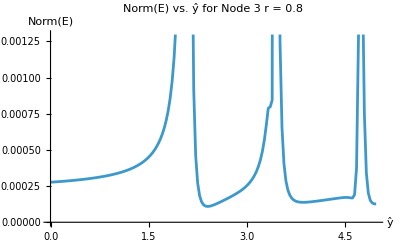

Evaluation time: 15.40249

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat3Array=Range[0,5,0.03];
Δ3NormArray=Table[Δ3Norm[κ]/.{yHat->yHat3Array[[i]]},{i,1,Length@yHat3Array}];
ENorm3Array=Table[NIntegrate[Δ3NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat3Array}];

ListPlot[Transpose@{yHat3Array,ENorm3Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 3\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

### Node 2

```mathematica
𝔸2[κ_]=γ20+γ21 Cos[κ]+Cos[2 κ]+γ23 Cos[3 κ]+γ24 Cos[4 κ];
𝔹2[κ_]=γ21 Sin[κ]+Sin[2 κ]+γ23 Sin[3 κ]+γ24 Sin[4 κ];
ℂ2[κ_]=a20+a21 Cos[κ]+a22 Cos[2 κ]+a23 Cos[3 κ]+a24 Cos[4 κ]+a25 Cos[5 κ]+a26 Cos[6 κ]+a27 Cos[7 κ]+a28 Cos[8 κ];
𝔻2[κ_]=a21 Sin[κ]+a22 Sin[2 κ]+a23 Sin[3 κ]+a24 Sin[4 κ]+a25 Sin[5 κ]+a26 Sin[6 κ]+a27 Sin[7 κ]+a28 Sin[8 κ];
κBar2Re[κ_]=(-𝔸2[κ]*ℂ2[κ]-𝔹2[κ]*𝔻2[κ])/((𝔸2[κ])^2+(𝔹2[κ])^2);
κBar2Im[κ_]=(𝔹2[κ]*ℂ2[κ]-𝔸2[κ]*𝔻2[κ])/((𝔸2[κ])^2+(𝔹2[κ])^2);
κBar2Norm[κ_]=Abs[κBar2Re[κ]+I*κBar2Im[κ]];
```

```mathematica
Δ2Re[κ_]=(κ^2*((𝔸2[κ])^2+(𝔹2[κ])^2)-(-𝔸2[κ]*ℂ2[κ]-𝔹2[κ]*𝔻2[κ]))^2;
Δ2Im[κ_]=(0*((𝔸2[κ])^2+(𝔹2[κ])^2)-(𝔹2[κ]*ℂ2[κ]-𝔸2[κ]*𝔻2[κ]))^2;
Δ2Norm[κ_]=(κ^2-κBar2Norm[κ])^2;
```

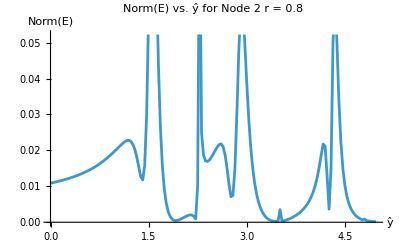

Evaluation time: 20.107526

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat2Array=Range[0,5,0.03];
Δ2NormArray=Table[Δ2Norm[κ]/.{yHat->yHat2Array[[i]]},{i,1,Length@yHat2Array}];
ENorm2Array=Table[NIntegrate[Δ2NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat2Array}];

ListPlot[Transpose@{yHat2Array,ENorm2Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 2\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

### Node 1

```mathematica
𝔸1[κ_]=γ10+Cos[κ]+γ12 Cos[2 κ]+γ13 Cos[3 κ];
𝔹1[κ_]=Sin[κ]+γ12 Sin[2 κ]+γ13 Sin[3 κ];
ℂ1[κ_]=a10+a21 Cos[κ]+a12 Cos[2 κ]+a13 Cos[3 κ]+a14 Cos[4 κ]+a15 Cos[5 κ]+a16 Cos[6 κ]+a17 Cos[7 κ]+a18 Cos[8 κ];
𝔻1[κ_]=a11 Sin[κ]+a12 Sin[2 κ]+a13 Sin[3 κ]+a14 Sin[4 κ]+a15 Sin[5 κ]+a16 Sin[6 κ]+a17 Sin[7 κ]+a18 Sin[8 κ];
κBar1Re[κ_]=(-𝔸1[κ]*ℂ1[κ]-𝔹1[κ]*𝔻1[κ])/((𝔸1[κ])^2+(𝔹1[κ])^2);
κBar1Im[κ_]=(𝔹1[κ]*ℂ1[κ]-𝔸1[κ]*𝔻1[κ])/((𝔸1[κ])^2+(𝔹1[κ])^2);
κBar1Norm[κ_]=Abs[κBar1Re[κ]+I*κBar1Im[κ]];
```

```mathematica
Δ1Re[κ_]=(κ^2*((𝔸1[κ])^2+(𝔹1[κ])^2)-(-𝔸1[κ]*ℂ1[κ]-𝔹1[κ]*𝔻1[κ]))^2;
Δ1Im[κ_]=(0*((𝔸1[κ])^2+(𝔹1[κ])^2)-(𝔹1[κ]*ℂ1[κ]-𝔸1[κ]*𝔻1[κ]))^2;
Δ1Norm[κ_]=(κ^2-κBar1Norm[κ])^2;
```

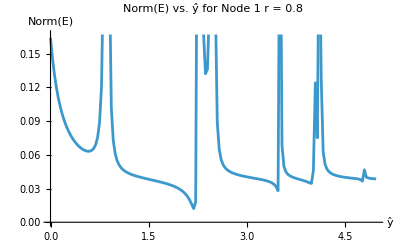

Evaluation time: 92.617467

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat1Array=Range[0,5,0.03];
Δ1NormArray=Table[Δ1Norm[κ]/.{yHat->yHat1Array[[i]]},{i,1,Length@yHat1Array}];
ENorm1Array=Table[NIntegrate[Δ1NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat1Array}];

ListPlot[Transpose@{yHat1Array,ENorm1Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 1\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

### Node 0

```mathematica
𝔸0[κ_]=1+γ01 Cos[κ]+γ02 Cos[2 κ];
𝔹0[κ_]=γ01 Sin[κ]+γ02 Sin[2 κ];
ℂ0[κ_]=a00+a01 Cos[κ]+a02 Cos[2 κ]+a03 Cos[3 κ]+a04 Cos[4 κ]+a05 Cos[5 κ]+a06 Cos[6 κ]+a07 Cos[7 κ]+a08 Cos[8 κ];
𝔻0[κ_]=a01 Sin[κ]+a02 Sin[2 κ]+a03 Sin[3 κ]+a04 Sin[4 κ]+a05 Sin[5 κ]+a06 Sin[6 κ]+a07 Sin[7 κ]+a08 Sin[8 κ];
κBar0Re[κ_]=(-𝔸0[κ]*ℂ0[κ]-𝔹0[κ]*𝔻0[κ])/((𝔸0[κ])^2+(𝔹0[κ])^2);
κBar0Im[κ_]=(𝔹0[κ]*ℂ0[κ]-𝔸0[κ]*𝔻0[κ])/((𝔸0[κ])^2+(𝔹0[κ])^2);
κBar0Norm[κ_]=Abs[κBar0Re[κ]+I*κBar0Im[κ]];
```

```mathematica
Δ0Re[κ_]=(κ^2*((𝔸0[κ])^2+(𝔹0[κ])^2)-(-𝔸0[κ]*ℂ0[κ]-𝔹0[κ]*𝔻0[κ]))^2;
Δ0Im[κ_]=(0*((𝔸0[κ])^2+(𝔹0[κ])^2)-(𝔹0[κ]*ℂ0[κ]-𝔸0[κ]*𝔻0[κ]))^2;
Δ0Norm[κ_]=(κ^2-κBar0Norm[κ])^2;
```

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat0Array=Range[0,5,0.1];
Δ0NormArray=ParallelTable[Δ0Norm[κ]/.{yHat->yHat0Array[[i]]},{i,1,Length@yHat0Array}];
ENorm0Array=ParallelTable[NIntegrate[Δ0NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat0Array}];

ListPlot[Transpose@{yHat0Array,ENorm0Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 0\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

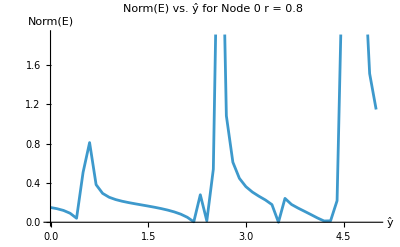

## Spectral Function

### Node 3

```mathematica
Clear[yHat]
SF3Re[κ_,yHat_]=κBar3Re[κ];
SF3Im[κ_,yHat_]=κBar3Im[κ];
SF3Norm[κ_,yHat_]=κBar3Norm[κ];
```

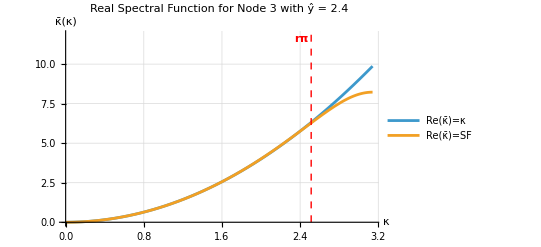

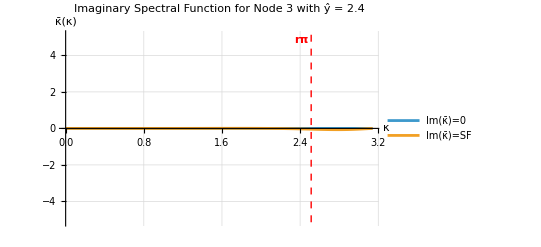

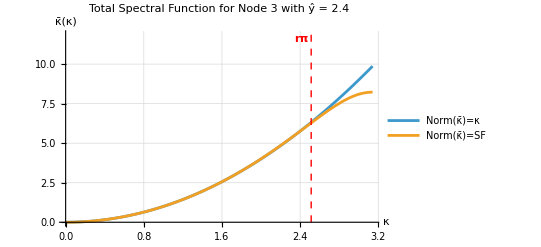

```mathematica
r=0.8;
yHat3List={(*1*)2.40,(*2*)3.87,(*3*)4.62,(*4*)4.98};
yHat=yHat3List[[1]];
Plot[{κ^2,SF3Re[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Real Spectral Function for Node 3 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
Plot[{0,SF3Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 3 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ^2,SF3Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Total Spectral Function for Node 3 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
```

### Node 2

```mathematica
Clear[yHat]
SF2Re[κ_,yHat_]=κBar2Re[κ];
SF2Im[κ_,yHat_]=κBar2Im[κ];
SF2Norm[κ_,yHat_]=κBar2Norm[κ];
```

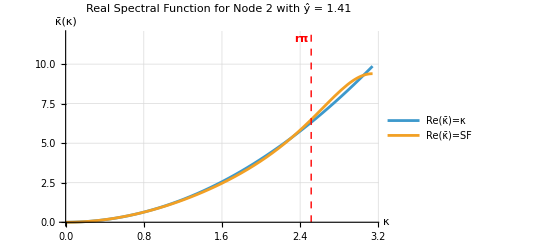

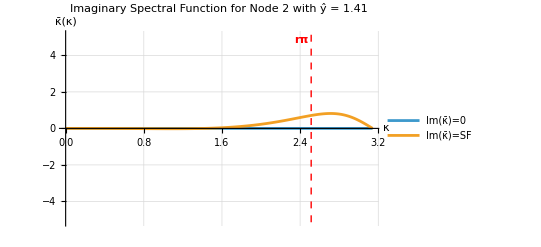

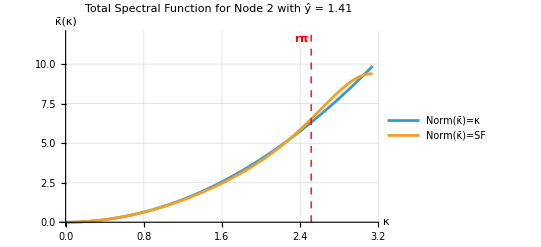

```mathematica
r=0.8;
yHat2List={(*1*)1.41,(*2*)1.92,(*3*)2.22,(*4*)2.40,(*5*)2.76,(*6*)3.48,(*7*)3.54,(*8*)4.26,(*9*)4.98};
yHat=yHat2List[[1]];
Plot[{κ^2,SF2Re[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Real Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
Plot[{0,SF2Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ^2,SF2Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Total Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
```

### Node 1

```mathematica
Clear[yHat]
SF1Re[κ_,yHat_]=κBar1Re[κ];
SF1Im[κ_,yHat_]=κBar1Im[κ];
SF1Norm[κ_,yHat_]=κBar1Norm[κ];
```

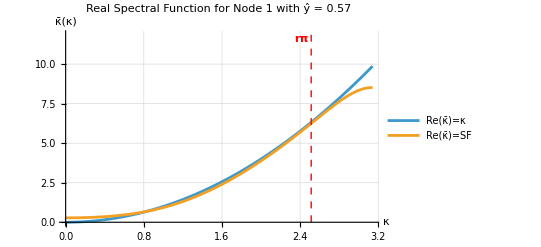

$Aborted

$Aborted

```mathematica
Clear[yHat]
r=0.8;
yHat1List={(*1*)0.57,(*2*)2.19,(*3*)3.48,(*4*)3.99,(*5*)4.77};
yHat=yHat1List[[1]];
Plot[{κ^2,SF1Re[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Real Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
Plot[{0,SF1Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ^2,SF1Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Total Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
```

### Node 0

```mathematica
Clear[yHat]
SF0Re[κ_,yHat_]=κBar0Re[κ];
SF0Im[κ_,yHat_]=κBar0Im[κ];
SF0Norm[κ_,yHat_]=κBar0Norm[κ];
```

```mathematica
r=0.8;
yHat0List={(*1*)0.4,(*2*)2.2,(*3*)2.4,(*4*)3.5,(*5*)4.2,(*6*)4.3};
yHat=yHat0List[[1]];
Plot[{κ^2,SF0Re[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Real Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
Plot[{0,SF0Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ^2,SF0Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Total Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
```

-Graphics-

$Aborted

$Aborted

## Output Coefficients

### ŷ Definitions

```mathematica
Clear[yHat,yHat2,yHat1,yHat0]

yHat3List={(*1*)2.40,(*2*)3.87,(*3*)4.62,(*4*)4.98};
yHat2List={(*1*)1.41,(*2*)1.92,(*3*)2.22,(*4*)2.40,(*5*)2.76,(*6*)3.48,(*7*)3.54,(*8*)4.26,(*9*)4.98};
yHat1List={(*1*)0.57,(*2*)2.19,(*3*)3.48,(*4*)3.99,(*5*)4.77};
yHat0List={(*1*)0.4,(*2*)2.2,(*3*)2.4,(*4*)3.5,(*5*)4.2,(*6*)4.3};

yHat3=yHat3List[[1]];
yHat2=yHat2List[[3]];
yHat1=yHat1List[[5]];
yHat0=yHat0List[[1]];

yHat0=0.4;
yHat1=0.57;
yHat2=1.41;
yHat3=2.4;
```

### Define Coefficients

```mathematica
Clear[γ33,γ31,γ32,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38]
Clear[γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28]
Clear[γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08]

{γ33val,γ31val,γ32val,γ34val,γ35val,a30val,a31val,a32val,a33val,a34val,a35val,a36val,a37val,a38val}=(1/γ33*{γ33,γ31,γ32,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38}/.bdCoeffs3)/.{yHat->yHat3};
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val,a27val,a28val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val,a17val,a18val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val,a07val,a08val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08}/.bdCoeffs0)/.{yHat->yHat0};
```

### Luke Output

```mathematica
interiorLuke=interiorCoeffsB42nd/.{a1->a,a2->b,a3->c,a4->d};
boundaryLuke={α12->γ01val,β12->γ02val,α21->γ10val,α22->γ12val,β22->γ13val,β31->γ20val,α31->γ21val,α32->γ23val,β32->γ24val,β41->γ31val,α41->γ32val,α42->γ34val,β42->γ35val,a1->a00val,b1->a01val,c1->a02val,d1->a03val,e1->a04val,f1->a05val,g1->a06val,h1->a07val,i1->a08val,a2->a10val,b2->a11val,c2->a12val,d2->a13val,e2->a14val,f2->a15val,g2->a16val,h2->a17val,i2->a18val,a3->a20val,b3->a21val,c3->a22val,d3->a23val,e3->a24val,f3->a25val,g3->a26val,h3->a27val,i3->a28val,a4->a30val,b4->a31val,c4->a32val,d4->a33val,e4->a34val,f4->a35val,g4->a36val,h4->a37val,i4->a38val};
coeffLuke=Flatten[Join[interiorLuke,boundaryLuke]]
```

{α→0.54432,β→0.0772885,a→0.106241,b→0.448205,c→0.040354,d→-0.00118951,α12→-9.0846,β12→-25.7136,α21→-0.133984,α22→2.4951,β22→0.412345,β31→-0.0215192,α31→0.320985,α32→0.597881,β32→0.133639,β41→0.0654447,α41→0.489633,α42→0.511688,β42→0.0670414,a1→-6.67058,b1→-19.0528,c1→62.9735,d1→-43.3289,e1→7.63935,f1→-1.98551,g1→0.526596,h1→-0.116186,i1→0.0145538,a2→0.802894,b2→1.45513,c2→-5.26124,d2→2.99659,e2→-0.0663866,f2→0.102577,g2→-0.038797,h2→0.010824,i2→-0.0015927,a3→0.242846,b3→0.667997,c3→-1.49017,d3→0.109473,e3→0.354899,f3→0.127499,g3→-0.0150076,h3→0.0028261,i3→-0.000363218,a4→0.0340064,b4→0.385025,c4→0.264267,d4→-1.33873,e4→0.206672,f4→0.415459,g4→0.0345253,h4→-0.00126846,i4→0.0000486133}

### Nate Output

```mathematica
interiorNate=interiorCoeffsB42nd;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,γ31->γ31val,γ32->γ32val,γ34->γ34val,γ35->γ35val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a07->a07val,a08->a08val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a17->a17val,a18->a18val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val,a27->a27val,a28->a28val,a30->a30val,a31->a31val,a32->a32val,a33->a33val,a34->a34val,a35->a35val,a36->a36val,a37->a37val,a38->a38val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]]
```

{α→0.54432,β→0.0772885,a1→0.106241,a2→0.448205,a3→0.040354,a4→-0.00118951,γ01→-9.0846,γ02→-25.7136,γ10→-0.133984,γ12→2.4951,γ13→0.412345,γ20→-0.0215192,γ21→0.320985,γ23→0.597881,γ24→0.133639,γ31→0.0654447,γ32→0.489633,γ34→0.511688,γ35→0.0670414,a00→-6.67058,a01→-19.0528,a02→62.9735,a03→-43.3289,a04→7.63935,a05→-1.98551,a06→0.526596,a07→-0.116186,a08→0.0145538,a10→0.802894,a11→1.45513,a12→-5.26124,a13→2.99659,a14→-0.0663866,a15→0.102577,a16→-0.038797,a17→0.010824,a18→-0.0015927,a20→0.242846,a21→0.667997,a22→-1.49017,a23→0.109473,a24→0.354899,a25→0.127499,a26→-0.0150076,a27→0.0028261,a28→-0.000363218,a30→0.0340064,a31→0.385025,a32→0.264267,a33→-1.33873,a34→0.206672,a35→0.415459,a36→0.0345253,a37→-0.00126846,a38→0.0000486133}

## Eigenvalue Spectral Analysis

### Modified Boundary Coefficients for Eigenvalue Analysis

```mathematica
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate),
γ31Bar->(γ31/.coeffNate),
γ32Bar->(γ32/.coeffNate),
γ34Bar->(γ34/.coeffNate),
γ35Bar->(γ35/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,8}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,8}]/.coeffNate;
RHSBars3=Table[
ToExpression@StringJoin["a3",ToString@j,"Bar"]->(ToExpression@StringJoin["a3",ToString@j]),
{j,1,8}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2,RHSBars3]
```

{γ12Bar→4.37455,γ13Bar→-1.89854,γ21Bar→0.267621,γ23Bar→0.887183,γ24Bar→0.223007,γ31Bar→0.0654447,γ32Bar→0.489633,γ34Bar→0.511688,γ35Bar→0.0670414,a11Bar→5.0538,a12Bar→-14.624,a13Bar→12.9324,a14Bar→-4.40702,a15Bar→0.75256,a16Bar→-0.146223,a17Bar→0.0218383,a18Bar→-0.00164496,a21Bar→0.724707,a22Bar→-1.0766,a23Bar→-0.620444,a24Bar→0.61002,a25Bar→0.185269,a26Bar→-0.0146453,a27Bar→0.00181499,a28Bar→-0.000179245,a31Bar→0.385025,a32Bar→0.264267,a33Bar→-1.33873,a34Bar→0.206672,a35Bar→0.415459,a36Bar→0.0345253,a37Bar→-0.00126846,a38Bar→0.0000486133}

### Build Modified Matrices (needs cleaning badly)

```mathematica
Clear[LHS,RHS]
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=4;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==3&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==3&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==3&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==3&&j==5),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],

If[(i==k&&j==k-1),ToExpression["γ"<>ToString[1]<>ToString[2]<>"Bar"],
If[(i==k&&j==k-2),ToExpression["γ"<>ToString[1]<>ToString[3]<>"Bar"],
If[(i==k-1&&j==k),ToExpression["γ"<>ToString[2]<>ToString[1]<>"Bar"],
If[(i==k-1&&j==k-2),ToExpression["γ"<>ToString[2]<>ToString[3]<>"Bar"],
If[(i==k-1&&j==k-3),ToExpression["γ"<>ToString[2]<>ToString[4]<>"Bar"],
If[(i==k-2&&j==k),ToExpression["γ"<>ToString[3]<>ToString[1]<>"Bar"],
If[(i==k-2&&j==k-1),ToExpression["γ"<>ToString[3]<>ToString[2]<>"Bar"],
If[(i==k-2&&j==k-3),ToExpression["γ"<>ToString[3]<>ToString[4]<>"Bar"],
If[(i==k-2&&j==k-4),ToExpression["γ"<>ToString[3]<>ToString[5]<>"Bar"],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}]

k=9; (*Size*)
MatrixForm@LHS[k]

MatrixForm@(LHS[k]/.coeffNate)/.barCoeffs
```

(1 | γ12Bar | γ13Bar | 0 | 0 | 0 | 0 | 0 | 0
γ21Bar | 1 | γ23Bar | γ24Bar | 0 | 0 | 0 | 0 | 0
γ31Bar | γ32Bar | 1 | γ34Bar | γ35Bar | 0 | 0 | 0 | 0
0 | β | α | 1 | α | β | 0 | 0 | 0
0 | 0 | β | α | 1 | α | β | 0 | 0
0 | 0 | 0 | β | α | 1 | α | β | 0
0 | 0 | 0 | 0 | γ35Bar | γ34Bar | 1 | γ32Bar | γ31Bar
0 | 0 | 0 | 0 | 0 | γ24Bar | γ23Bar | 1 | γ21Bar
0 | 0 | 0 | 0 | 0 | 0 | γ13Bar | γ12Bar | 1)

(1 | 4.37455 | -1.89854 | 0 | 0 | 0 | 0 | 0 | 0
0.267621 | 1 | 0.887183 | 0.223007 | 0 | 0 | 0 | 0 | 0
0.0654447 | 0.489633 | 1 | 0.511688 | 0.0670414 | 0 | 0 | 0 | 0
0 | 0.0772885 | 0.54432 | 1 | 0.54432 | 0.0772885 | 0 | 0 | 0
0 | 0 | 0.0772885 | 0.54432 | 1 | 0.54432 | 0.0772885 | 0 | 0
0 | 0 | 0 | 0.0772885 | 0.54432 | 1 | 0.54432 | 0.0772885 | 0
0 | 0 | 0 | 0 | 0.0670414 | 0.511688 | 1 | 0.489633 | 0.0654447
0 | 0 | 0 | 0 | 0 | 0.223007 | 0.887183 | 1 | 0.267621
0 | 0 | 0 | 0 | 0 | 0 | -1.89854 | 4.37455 | 1)

```mathematica
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,
If[(i==1&&j==7),a17Bar,
If[(i==1&&j==8),a18Bar,

If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,
If[(i==2&&j==7),a27Bar,
If[(i==2&&j==8),a28Bar,

If[(i==3&&j==1),a31Bar,
If[(i==3&&j==2),a32Bar,
If[(i==3&&j==3),a33Bar,
If[(i==3&&j==4),a34Bar,
If[(i==3&&j==5),a35Bar,
If[(i==3&&j==6),a36Bar,
If[(i==3&&j==7),a37Bar,
If[(i==3&&j==8),a38Bar,


If[(i==k&&j==k),a11Bar,
If[(i==k&&j==k-1),a12Bar,
If[(i==k&&j==k-2),a13Bar,
If[(i==k&&j==k-3),a14Bar,
If[(i==k&&j==k-4),a15Bar,
If[(i==k&&j==k-5),a16Bar,
If[(i==k&&j==k-6),a17Bar,
If[(i==k&&j==k-7),a18Bar,

If[(i==k-1&&j==k),a21Bar,
If[(i==k-1&&j==k-1),a22Bar,
If[(i==k-1&&j==k-2),a23Bar,
If[(i==k-1&&j==k-3),a24Bar,
If[(i==k-1&&j==k-4),a25Bar,
If[(i==k-1&&j==k-5),a26Bar,
If[(i==k-1&&j==k-6),a27Bar,
If[(i==k-1&&j==k-7),a28Bar,

If[(i==k-2&&j==k),a31Bar,
If[(i==k-2&&j==k-1),a32Bar,
If[(i==k-2&&j==k-2),a33Bar,
If[(i==k-2&&j==k-3),a34Bar,
If[(i==k-2&&j==k-4),a35Bar,
If[(i==k-2&&j==k-5),a36Bar,
If[(i==k-2&&j==k-6),a37Bar,
If[(i==k-2&&j==k-7),a38Bar,


If[i-4==j,a4,
If[i-3==j,a3,
If[i-2==j,a2,
If[i-1==j,a1,
If[i==j,-2*(a1+a2+a3+a4),
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
If[i+4==j,a4,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}]

k=11; (*Size*)
MatrixForm@RHS[k]

MatrixForm@(RHS[k]/.coeffNate)/.barCoeffs
```

(a11Bar | a12Bar | a13Bar | a14Bar | a15Bar | a16Bar | a17Bar | a18Bar | 0 | 0 | 0
a21Bar | a22Bar | a23Bar | a24Bar | a25Bar | a26Bar | a27Bar | a28Bar | 0 | 0 | 0
a31Bar | a32Bar | a33Bar | a34Bar | a35Bar | a36Bar | a37Bar | a38Bar | 0 | 0 | 0
a3 | a2 | a1 | -2 (a1+a2+a3+a4) | a1 | a2 | a3 | a4 | 0 | 0 | 0
a4 | a3 | a2 | a1 | -2 (a1+a2+a3+a4) | a1 | a2 | a3 | a4 | 0 | 0
0 | a4 | a3 | a2 | a1 | -2 (a1+a2+a3+a4) | a1 | a2 | a3 | a4 | 0
0 | 0 | a4 | a3 | a2 | a1 | -2 (a1+a2+a3+a4) | a1 | a2 | a3 | a4
0 | 0 | 0 | a4 | a3 | a2 | a1 | -2 (a1+a2+a3+a4) | a1 | a2 | a3
0 | 0 | 0 | a38Bar | a37Bar | a36Bar | a35Bar | a34Bar | a33Bar | a32Bar | a31Bar
0 | 0 | 0 | a28Bar | a27Bar | a26Bar | a25Bar | a24Bar | a23Bar | a22Bar | a21Bar
0 | 0 | 0 | a18Bar | a17Bar | a16Bar | a15Bar | a14Bar | a13Bar | a12Bar | a11Bar)

(5.0538 | -14.624 | 12.9324 | -4.40702 | 0.75256 | -0.146223 | 0.0218383 | -0.00164496 | 0 | 0 | 0
0.724707 | -1.0766 | -0.620444 | 0.61002 | 0.185269 | -0.0146453 | 0.00181499 | -0.000179245 | 0 | 0 | 0
0.385025 | 0.264267 | -1.33873 | 0.206672 | 0.415459 | 0.0345253 | -0.00126846 | 0.0000486133 | 0 | 0 | 0
0.040354 | 0.448205 | 0.106241 | -1.18722 | 0.106241 | 0.448205 | 0.040354 | -0.00118951 | 0 | 0 | 0
-0.00118951 | 0.040354 | 0.448205 | 0.106241 | -1.18722 | 0.106241 | 0.448205 | 0.040354 | -0.00118951 | 0 | 0
0 | -0.00118951 | 0.040354 | 0.448205 | 0.106241 | -1.18722 | 0.106241 | 0.448205 | 0.040354 | -0.00118951 | 0
0 | 0 | -0.00118951 | 0.040354 | 0.448205 | 0.106241 | -1.18722 | 0.106241 | 0.448205 | 0.040354 | -0.00118951
0 | 0 | 0 | -0.00118951 | 0.040354 | 0.448205 | 0.106241 | -1.18722 | 0.106241 | 0.448205 | 0.040354
0 | 0 | 0 | 0.0000486133 | -0.00126846 | 0.0345253 | 0.415459 | 0.206672 | -1.33873 | 0.264267 | 0.385025
0 | 0 | 0 | -0.000179245 | 0.00181499 | -0.0146453 | 0.185269 | 0.61002 | -0.620444 | -1.0766 | 0.724707
0 | 0 | 0 | -0.00164496 | 0.0218383 | -0.146223 | 0.75256 | -4.40702 | 12.9324 | -14.624 | 5.0538)

### Plot Eigenvalue Spectra

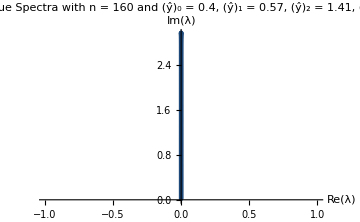

```mathematica
k=160;
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
(*eigs=(Eigenvalues[mat])^1/π;*)
eigs=(Eigenvalues[mat])^(1/2);

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->All,PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2],", (ŷ)_3 = ",ToString[yHat3]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat1/5,yHat2/5,yHat3/5]]
```

## Dendro Output

### Hide

```mathematica
derivativeOrder=2;
interiorOrder=n;
totalBoundRows=numBoundaryRows;
freeInteriorParameters={};
freeBoundaryParameters={};
RHSInteriorList=RHSPars;
interiorParametersValues=interiorCoeffsB42nd/.{α->alpha,β->beta};
boundaryParametersValues=boundaryLuke/.{α12->gamma01,β12->gamma02,α21->gamma10,α22->gamma12,β22->gamma13,β31->gamma20,α31->gamma21,α32->gamma23,β32->gamma24,β41->gamma31,α41->gamma32,α42->gamma34,β42->gamma35,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,h1->a07,i1->a08,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,h2->a17,i2->a18,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26,h3->a27,i3->a28,a4->a30,b4->a31,c4->a32,d4->a33,e4->a34,f4->a35,g4->a36,h4->a37,i4->a38};
LHSBoundaryList={gamma01,gamma02,gamma10,gamma12,gamma13,gamma20,gamma21,gamma23,gamma24,gamma31,gamma32,gamma34,gamma35};
RHSBoundaryList={a00,a01,a02,a03,a04,a05,a06,a07,a08,a10,a11,a12,a13,a14,a15,a16,a17,a18,a20,a21,a22,a23,a24,a25,a26,a27,a28,a30,a31,a32,a33,a34,a35,a36,a37,a38};
(*Don't need to mess with these until we incorporate this procedure with James's filtering*)
filterIntCoeff;
filterBoundCoeff;
filterIntParam;
filterBoundParam;
filtering=False;
(*boundary={α12->γ01,β12->γ02,α21->γ10,α22->γ12,β22->γ13,β31->γ20,α31->γ21,α32->γ23,β32->γ24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};*)
```

```mathematica
(*****************Print coefficients in Dendro-GR Format*****************)
If[derivativeOrder==1,
LHSName="P1";
RHSName="Q1";
nth="1st";
coeffs="D_coeffs";
order="First",
If[derivativeOrder==2,
LHSName="P2";
RHSName="Q2";
nth="2nd";
coeffs="D_coeffs";
order="Second"]];
If[LHSBandCount==3,
LHSStructure="T",
If[LHSBandCount==5,
LHSStructure="P"]];

(*Convert Mathematica expression syntax to C/C++ expression syntax*)
convertToCCode[expr_]:=Module[{str},str=ToString[expr,InputForm];
(*Add ".0" to standalone integers but not to variables with numbers*)
(*Formatting adjustments to match C/C++ syntax*)str=StringReplace[str,{" "->"","*"->" * ","/"->" / ","+"->" + ","-"->" - ","^"->" ^ "}];
str]
(*Function to generate the line of C/C++ code to define the fixed variables*)
generateCAssignment[rule_]:=Module[{variable,expression,cCode,cAssignment},
variable=ToString[rule[[1]]];
expression=rule[[2]];
cCode=convertToCCode[expression];
cAssignment="double "<>variable<>" = "<>cCode<>";";
cAssignment
]






(*Initial Block*)
initialBlock=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order"}];
initialBlock2=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order","Filtered"}];

(*Free Parameters Block*)
freeParameters=Join[freeInteriorParameters,freeBoundaryParameters];
numFreePars=Length[freeParameters];
alphaPrint=StringReplace[generateCAssignment[Select[interiorParametersValues,#[[1]]===alpha&][[1]]],"alpha"->"alpha0"];
freeParPrints={};
If[numFreePars>0,
For[i=1,i<=numFreePars,i++,
AppendTo[freeParPrints,StringJoin[{"\n\t\tdouble ",ToString[freeParameters[[i]]]," = ",coeffs,"[",ToString[i],"];"}]]]]
freeParametersBlock=StringJoin[{"\t",alphaPrint,"\n\t\tdouble alpha = alpha0 + ",coeffs,"[0];",freeParPrints}];

(*Filter*)
freeParPrints2={};
freeParametersBlock2=StringJoin[{"\t","\n\t\tdouble alpha = ","F_coeffs","[0];",If[LHSBandCount==5,StringJoin["\n\t\tdouble beta = ","F_coeffs","[1];"],""]}];

(*Fixed Parameters Block*)
(*Create a list of the solved fixed parameters in C/C++ syntax*)
interiorParametersValues3=DeleteCases[interiorParametersValues,Rule[alpha,_]];
interiorParameterPrints=Table[
generateCAssignment[interiorParametersValues3[[i]]],
{i,1,Length[interiorParametersValues]-1}
];
boundaryParameterPrints=Table[
generateCAssignment[boundaryParametersValues[[i]]],
{i,1,Length[boundaryParametersValues]}
];
(*For filtered coefficients*)
interiorParameterPrints2=Table[
generateCAssignment[filterIntCoeff[[i]]],
{i,1,Length[filterIntCoeff]}
];
boundaryParameterPrints2=Table[
generateCAssignment[filterBoundCoeff[[i]]],
{i,1,Length[filterBoundCoeff]}
];
(*Print the coefficients in a single block of text rather than individual lines*)
fixedParametersBlockD=StringJoin["\t\t",Riffle[Join[interiorParameterPrints,boundaryParameterPrints],"\n\t\t"]];
fixedParametersBlockD2=StringJoin["\t\t",Riffle[Join[interiorParameterPrints2,boundaryParameterPrints2],"\n\t\t"]];

(*Structure Block*)
(*LHS Boundary*)
PDiagBoundary="";
LHSRowList=ToExpression[GatherBy[LHSBoundaryList,StringDrop[ToString[#],5]~StringTake~1&]];
For[i=1,i<=Length[LHSRowList],i++,
If[i==1,PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t","{1.0, ",StringDrop[ToString[LHSRowList[[i]]],1],","]];
If[i==2,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1}]],1],","]]];
If[i==3,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{","0.0, ",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t",StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
If[i>=4,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],StringDrop[StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
];
(*LHS Filter Boundary*)
RDiagBoundary="";
For[i=1,i<=Length@filterBoundParam,i++,
If[i==1,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha, beta},"]];
];
If[i==2,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha 1.0, alpha, beta},"]];
];
If[i>=3,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],"alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],"beta, alpha, 1.0, alpha, beta},"]];
];
];

(*LHS Interior*)
If[LHSBandCount==3,
PDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
PDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];
(*LHS Filter Interior*)
If[LHSBandCount==3,
RDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
RDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];

(*RHS Boundary*)
QDiagBoundary="";
RHSRowList=ToExpression[GatherBy[RHSBoundaryList,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList],i++,QDiagBoundary=StringJoin[QDiagBoundary,"\n\t\t\t",ToString[RHSRowList[[i]]],","]]
(*RHS Filter Boundary*)
SDiagBoundary="";
RHSRowList2=ToExpression[GatherBy[filterBoundParam,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList2],i++,SDiagBoundary=StringJoin[SDiagBoundary,"\n\t\t\t",ToString[RHSRowList2[[i]]]]]

(*RHS Interior*)
QDiagInterior={};
len=(2*Length[RHSInteriorList]+1);
If[derivativeOrder==1,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[-RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"0.0"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]
],
If[derivativeOrder==2,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"t1"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]]]]

(*RHS Filter Interior*)
SDiagInterior={};
newFilterIntParam=Drop[filterIntParam,1];
len=(2*Length[newFilterIntParam]+1);
For[i=1,i<=len,i++,
If[i<=Length[newFilterIntParam],PrependTo[SDiagInterior,ToString[newFilterIntParam[[i]]]<>"/"<>ToString[2]<>".0"]];
If[i==(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,"a0"]];
If[i>(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,ToString[newFilterIntParam[[i-Length[newFilterIntParam]-1]]]<>"/"<>ToString[2]<>".0"]]
]


PDiagBoundaryStr=StringDrop[StringDrop[PDiagBoundary,1],-1];
PDiagInteriorStr=StringDrop[StringDrop[PDiagInterior,1],-1];
RDiagBoundaryStr=StringDrop[StringDrop[RDiagBoundary,1],-1];
RDiagInteriorStr=StringDrop[StringDrop[RDiagInterior,1],-1];
QDiagBoundaryStr=StringDrop[StringDrop[QDiagBoundary,1],-1];
QDiagInteriorStr=StringDrop[StringDrop[ToString[QDiagInterior],1],-1];
SDiagBoundaryStr=StringDrop[SDiagBoundary,1];
SDiagInteriorStr=StringDrop[StringDrop[ToString[SDiagInterior],1],-1];

(*Subscript[t, 1] is the middle RHS Interior Coefficient for Second Derivatives*)
t1List={};
For[i=1,i<=Length[RHSInteriorList],i++,
AppendTo[t1List,ToString[RHSInteriorList[[i]]]]
];
If[derivativeOrder==1,
t1="",
If[derivativeOrder==2,
t1=StringJoin["-2.0 * ("<>ToString[Total[t1List]]<>")"]]];


If[filtering,
filterFinalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock2,"(\n","\tconst std::vector<double>& ","F_coeffs",") {\n","\t",freeParametersBlock2,"\n\n",fixedParametersBlockD2,"\n\n","\t\t// boundary elements for R matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","R","DiagBoundary{\n",RDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for R matrix for ",nth," derivative\n","\t\tstd::vector<double> ","R","DiagInterior{\n","\t\t\t",RDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for S matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","S","DiagBoundary\n",SDiagBoundaryStr,"\n","\t\t;\n\n","\t\t// diagonal elements for S matrix for ",nth," derivative\n","\t\tstd::vector<double> ","S","DiagInterior{\n","\t\t\t",SDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t","R","DiagInterior, ","S","DiagInterior, ","S","DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}"}];
]

finalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock,"(\n","\tconst std::vector<double>& ",coeffs,") {\n","\t",freeParametersBlock,"\n\n",fixedParametersBlockD,"\n\n","\t\t// boundary elements for P matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",LHSName,"DiagBoundary{\n",PDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for P matrix for ",nth," derivative\n","\t\tstd::vector<double> ",LHSName,"DiagInterior{\n","\t\t\t",PDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",RHSName,"DiagBoundary{\n",QDiagBoundaryStr,"\n","\t\t};\n\n",If[derivativeOrder==1,t1,If[derivativeOrder==2,"\t\tdouble t1 = "<>t1<>";\n"]],"\t\t// diagonal elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<double> ",RHSName,"DiagInterior{\n","\t\t\t",QDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t",LHSName,"DiagInterior, ",LHSName,"DiagBoundary, ",RHSName,"DiagInterior, ",RHSName,"DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}",If[filtering,"\n\n"<>filterFinalBlock,""]}];
```

GatherBy::list: List expected at position 1 in GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&].

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Drop::drop: Cannot drop positions 1 through 1 in filterIntParam.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

StringDrop::drop: Cannot drop positions 1 through 1 in "".

### Show

```mathematica
outExt="h";
(*Print header*)
Print[Style["Dendro-Ready Coefficients (Copied to clipboard):",Bold,FontSize->24]];
Print[finalBlock];
(*Copy the block of text to the user's clipboard*)
CopyToClipboard[finalBlock];

(*Save to output file*)
fileName=StringJoin[{"BYU_B4_2nd","_yHat0_",ToString[yHat0],"_yHat1_",ToString[yHat1],"_yHat2_",ToString[yHat2],"_yHat3_",ToString[yHat3],".",outExt}];
Export[fileName,finalBlock,"Text"];
Print[StringJoin[{"Saved to file: ",fileName}]]
```

Dendro-Ready Coefficients (Copied to clipboard):

MatrixDiagonalEntries* BYUDerivsP4R4DiagonalsSecondOrder(
	const std::vector<double>& D_coeffs) {
		double alpha0 = 0.5443196687355368;
		double alpha = alpha0 + D_coeffs[0];

		double beta = 0.07728851013567789;
		double a1 = 0.10624114531946292;
		double a2 = 0.44820542026997306;
		double a3 = 0.040353966028400544;
		double a4 =  - 0.0011895101820331873;
		double gamma01 =  - 9.08459826478248;
		double gamma02 =  - 25.71363251024003;
		double gamma10 =  - 0.133984019279111;
		double gamma12 = 2.4951036451754596;
		double gamma13 = 0.4123449516198014;
		double gamma20 =  - 0.02151917117828344;
		double gamma21 = 0.32098475801942616;
		double gamma23 = 0.5978810174357946;
		double gamma24 = 0.13363937320515867;
		double gamma31 = 0.06544469559131794;
		double gamma32 = 0.48963264996225114;
		double gamma34 = 0.5116877293377498;
		double gamma35 = 0.06704135028368141;
		double a00 =  - 6.6705826312289105;
		double a01 =  - 19.0528028978955;
		double a02 = 62.97350601697924;
		double a03 =  - 43.32893064487769;
		double a04 = 7.63935311361443;
		double a05 =  - 1.985506734444297;
		double a06 = 0.5265961795964231;
		double a07 =  - 0.11618615404780643;
		double a08 = 0.014553751968020763;
		double a10 = 0.8028940456973566;
		double a11 = 1.4551309417195069;
		double a12 =  - 5.261235243878468;
		double a13 = 2.9965856154362647;
		double a14 =  - 0.0663866171518484;
		double a15 = 0.10257699309312651;
		double a16 =  - 0.03879704736258897;
		double a17 = 0.010824012532857464;
		double a18 =  - 0.0015927000849847654;
		double a20 = 0.2428464429656088;
		double a21 = 0.6679974422958201;
		double a22 =  - 1.4901708753503622;
		double a23 = 0.10947313538836716;
		double a24 = 0.35489933574508953;
		double a25 = 0.12749921423072738;
		double a26 =  - 0.015007572943870444;
		double a27 = 0.0028260955807972513;
		double a28 =  - 0.0003632179120144587;
		double a30 = 0.034006449362369115;
		double a31 = 0.3850247295575769;
		double a32 = 0.2642667881567995;
		double a33 =  - 1.3387347356082686;
		double a34 = 0.20667213978114238;
		double a35 = 0.41545919420331817;
		double a36 = 0.034525284360193025;
		double a37 =  - 0.0012684631565034407;
		double a38 = 0.00004861334334597006;

		// boundary elements for P matrix for 2nd derivative
		std::vector<std::vector<double>> P2DiagBoundary{
			{1.0, gamma01, gamma02},
			{gamma10, 1.0, gamma12, gamma13},
			{gamma20, gamma21, 1.0, gamma23, gamma24},
			{0.0, gamma31, gamma32, 1.0, gamma34, gamma35}
		};

		// diagonal elements for P matrix for 2nd derivative
		std::vector<double> P2DiagInterior{
			beta, alpha, 1.0, alpha, beta
		};

		// boundary elements for Q matrix for 2nd derivative
		std::vector<std::vector<double>> Q2DiagBoundary{
			{a00, a01, a02, a03, a04, a05, a06, a07, a08},
			{a10, a11, a12, a13, a14, a15, a16, a17, a18},
			{a20, a21, a22, a23, a24, a25, a26, a27, a28},
			{a30, a31, a32, a33, a34, a35, a36, a37, a38}
		};

		double t1 = -2.0 * (a1 + a2 + a3 + a4);
		// diagonal elements for Q matrix for 2nd derivative
		std::vector<double> Q2DiagInterior{
			a4, a3, a2, a1, t1, a1, a2, a3, a4
		};

		// store the entries for matrix creation
		MatrixDiagonalEntries* diagEntries = new
			MatrixDiagonalEntries{
				P2DiagInterior, P2DiagBoundary, Q2DiagInterior, Q2DiagBoundary
			};
		return diagEntries;
	}

Saved to file: BYU_B4_2nd_yHat0_0.4_yHat1_0.57_yHat2_1.41_yHat3_2.4.h

# P4 (C4) Scheme

## Initialization

The matrix system of equations we are solving for this scheme is:
	P=(1
γ_10
β
0
0 γ_01
1
α
γ_13
0 γ_02
γ_12
1
γ_12
γ_02 0
γ_13
α
1
γ_01 0
0
β
γ_10
1)
	Q=(a_00
a_10
a_2
a_14
a_04 a_01
a_11
a_1
a_13
a_03 a_02
a_12
-2s
a_12
a_02 a_03
a_13
a_1
a_11
a_01 a_04
a_14
a_2
a_10
a_00)
Note that:
	s=a_1+a_2

```mathematica
(*From KimInteriorOptimization.nb, one day to be merged with this one. Or I could DumpSave[] in that notebook and then Get[] here.*)
interiorCoeffsC42nd={α->0.39755582066409934,β->0.021185375111255712,a1->0.5207872376311244,a2->0.32917378847989637};

(*If you have the .mx files in the same directory as this notebook, these will let you skip the long computation of defining bdCoeffs under the "Solve for Boundary Coefficients" section*)
Get["C4_2nd_interiorCoeffs.mx"]
Get["C4_2nd_bdCoeffs0.mx"]
Get["C4_2nd_bdCoeffs1.mx"]
```

## General Extrapolation Polynomial

The only settings the user should have to change for a different (second derivative) scheme are:
	- LHSBandCount
	- n
	- freeInteriorPars
	- yDeriv
For the P6 (A6) scheme, we have:
	LHSBandCount = 5
	n = 4
	freeInteriorPars = 2
	yDeriv = 5

```mathematica
(*User chooses these parameters, the rest is calculated from these*)
LHSBandCount=5; (*3 for tridiagonal, 5 for pentadiagonal*)
n=4; (*order of the scheme*)
freeInteriorPars=2; (*number of free parameters used for Kim's optimization on the interior*)
yDeriv=5; (*(d^n P)/dx^n(ŷ)=0 from Kim 2024 Eq. 10, this is n in that equation*) (*provide constraints on what the user can choose for this. Upper bound should be polynomialorder to prevent the matrix from being singular, and lower bound should be order·2 I think.*)

LHSPars=Switch[LHSBandCount,3,{α},5,{α,β}];
RHSPars=Table[ToExpression[StringJoin["a",ToString[i]]],{i,1,Ceiling[n/2]-Length@LHSPars+freeInteriorPars}];
numBoundaryRows=Length@RHSPars;
fOrder=(2*Length@RHSPars)+1;
fppOrder=LHSBandCount+(numBoundaryRows-(LHSBandCount-1)/2);
PolynomialOrder=fOrder+fppOrder;


rowf1=Join[{1},Table[0,{i,1,PolynomialOrder}]];
rowf=Table[Table[i^j,{j,0,PolynomialOrder}],{i,1,fOrder-1}];
rowfpp1=Join[{0,0,2},Table[0,{i,3,PolynomialOrder}]];
rowfpp=Table[Table[j (j-1) i^(j-2),{j,0,PolynomialOrder}],{i,1,fppOrder-1}];
rowyHat=Join[Table[0,{i,1,yDeriv}],Table[(i!)/((i-yDeriv)!) yHat^(i-yDeriv),{i,yDeriv,PolynomialOrder}]];

matf=PrependTo[rowf,rowf1];
matfpp=PrependTo[rowfpp,rowfpp1];
matfCombined=Join[matf,matfpp];
LMat=AppendTo[matfCombined,rowyHat];

pVec=Table[ToExpression[StringJoin["p",ToString[i]]],{i,0,PolynomialOrder}];
fVec=Join[Table[ToExpression[StringJoin["f",ToString[i]]],{i,0,fOrder-1}],Table[ToExpression[StringJoin["fpp",ToString[i]]],{i,0,fppOrder-1}],{0}];

pCoeffs=Solve[LMat.pVec==fVec,pVec][[1]];

yHatSingularities=(Transpose@Solve[Det[LMat]==0,yHat])[[1]]//N;
P[x_]=Total[Table[pVec[[i+1]]*x^i,{i,0,PolynomialOrder}]]/.pCoeffs;

Print["System:\n",MatrixForm[LMat]," ",MatrixForm[pVec]," = ",MatrixForm[fVec]]
Print["Singularities:\n",MatrixForm[yHatSingularities]]
(*Print["Coefficients:\n",MatrixForm[pCoeffs]]*)
```

System:
(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 4 | 8 | 16 | 32 | 64 | 128 | 256 | 512 | 1024
1 | 3 | 9 | 27 | 81 | 243 | 729 | 2187 | 6561 | 19683 | 59049
1 | 4 | 16 | 64 | 256 | 1024 | 4096 | 16384 | 65536 | 262144 | 1048576
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 6 | 12 | 20 | 30 | 42 | 56 | 72 | 90
0 | 0 | 2 | 12 | 48 | 160 | 480 | 1344 | 3584 | 9216 | 23040
0 | 0 | 2 | 18 | 108 | 540 | 2430 | 10206 | 40824 | 157464 | 590490
0 | 0 | 2 | 24 | 192 | 1280 | 7680 | 43008 | 229376 | 1179648 | 5898240
0 | 0 | 0 | 0 | 0 | 120 | 720 yHat | 2520 yHat^2 | 6720 yHat^3 | 15120 yHat^4 | 30240 yHat^5) (p0
p1
p2
p3
p4
p5
p6
p7
p8
p9
p10) = (f0
f1
f2
f3
f4
fpp0
fpp1
fpp2
fpp3
fpp4
0)

Singularities:
(yHat→1.45477
yHat→2.54523
yHat→0.507844
yHat→3.49216)

## Solve for Boundary Coefficients

Goal:
	Solve a system of equations for bdCoeffsList1 in terms of the optimization free parameter ŷ
Variables:
	fVars1: List of f_i and f_i' variables that will appear in the shifted stencil for Node 1
	bdCoeffsList1: List of boundary coefficients that will appear in the shifted stencil for Node 1
	schemeShifted: The shifted scheme for Node 1
	schemeCentered: The centered scheme for Node 1 in terms of the extrapolation polynomial P(x)
		NOTE: To make the Collect[] process easier, we write these schemes as LHS-RHS=0 rather than the usual LHS=RHS.
	schemeNode2: The scheme for Node 2, which only depends on interiorCoeffsC62nd
	SOLfp4: The solution to Node 2’s scheme equation for f_4' in terms of fVars1
	eq: Scheme equation where the coefficient terms from schemeCentered and schemeShifted are set equal to each other
	coeffEqs1: System of equations with each of the coefficient terms equal to each other
	bdCoeffs1: Solution to the system of equations for bdCoeffsList1 in terms of ŷ
Process:
	1. Initialize the necessary equations.
	2. We want schemeShifted and schemeCentered to both be in terms of fVars1 with some coefficients. Due to the presence of P(x) terms in schemeCentered, it is in terms of fVars1 as well as f_4'. We eliminate the dependence on f_4' by using Node 2’s scheme to solve for f_4' in terms of fVars1.
	3. Now that schemeShifted and schemeCentered are both in terms of fVars1, we construct a system of equations by equating the coefficient in front of each term of fVars1 in schemeCentered with the corresponding coefficient in front of the same term in schemeShifted.
	4. We solve this system of equations for bdCoeffsList1 in terms of interiorCoeffsC62nd (which are substituted in) and the optimization free parameter ŷ.
		NOTE: In the standard scheme approach, we set γ_11=1 to ensure the main diagonal of the LHS matrix is all 1’s. When solving this system of equations, we must include γ_11 so that bdCoeffsList1 and fVars1 have the same length since this allows us to find a unique solution to the system of equations. We apply the normal condition later on.
	5. OPTIONAL: We may save the variable bdCoeffs1 to a binary file in the current directory. This is helpful to avoid having to run this process multiple times, as it can become computationally expensive.
Differences:
	For Node 0, the entire process translates directly with a few changes. fVars, bdCoeffsList, schemeShifted, and schemeCentered all change, as we are considering the scheme for a different row, but the equations have the same structure. The main notable difference is in Step 2; In addition to substituting in the solution from Node 2 for f_4' in terms of the other fVars, we must also do the same for f_3' using Node 1.

### Node 1

```mathematica
(*----------STEP 1----------*)
a0=-2 (a1+a2);
fVars1={fpp0,fpp1,fpp2,fpp3,f0,f1,f2,f3,f4};
bdCoeffsList1={γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14};
schemeShifted=γ10 fpp0+γ11 fpp1+γ12 fpp2+γ13 fpp3-(a10 f0+a11 f1+a12 f2+a13 f3+a14 f4); (*==0*)
schemeCentered=β P''[-1]+α fpp0+fpp1+α fpp2+β fpp3-(a2 P[-1]+a1 f0+a0 f1+a1 f2+a2 f3); (*==0*)

(*----------STEP 2----------*)
schemeNode2=β fpp0+α fpp1+fpp2+α fpp3+β fpp4==a2 f0+a1 f1+a0 f2+a1 f3+a2 f4;

SOLfpp4=Solve[schemeNode2,fpp4][[1,1]]/.interiorCoeffsC42nd;
schemeCentered=schemeCentered/.SOLfpp4;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars1];

(*----------STEP 4----------*)
coeffEqs1=Table[Coefficient[eq,fVars1[[i]]]==0,{i,1,Length@fVars1}];
bdCoeffs1=(Solve[coeffEqs1,bdCoeffsList1][[1]])/.interiorCoeffsC42nd;

(*----------STEP 5----------*)
DumpSave["C4_2nd_bdCoeffs1.mx","Global`bdCoeffs1"]
```

{Global`bdCoeffs1}

### Node 0

```mathematica
(*----------STEP 1----------*)
a0=-2 (a1+a2);
fVars0={fpp0,fpp1,fpp2,f0,f1,f2,f3,f4};
bdCoeffsList0={γ00,γ01,γ02,a00,a01,a02,a03,a04};
schemeShifted=γ00 fpp0+γ01 fpp1+γ02 fpp2-(a00 f0+a01 f1+a02 f2+a03 f3+a04 f4); (*==0*)
schemeCentered=β P''[-2]+α P''[-1]+fpp0+α fpp1+β fpp2-(a2 P[-2]+a1 P[-1]+a0 f0+a1 f1+a2 f2); (*==0*)

(*----------STEP 2----------*)
schemeNode2=β fpp0+α fpp1+fpp2+α fpp3+β fpp4==a2 f0+a1 f1+a0 f2+a1 f3+a2 f4;
schemeNode1=γ10 fpp0+γ11 fpp1+γ12 fpp2+γ13 fpp3==a10 f0+a11 f1+a12 f2+a13 f3+a14 f4;

SOLfpp4=Solve[schemeNode2,fpp4][[1,1]]/.interiorCoeffsC42nd;
SOLfpp3=Solve[schemeNode1,fpp3][[1,1]]/.bdCoeffs1;
schemeCentered=schemeCentered/.SOLfpp4/.SOLfpp3;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars0];

(*----------STEP 4----------*)
coeffEqs0=Table[Coefficient[eq,fVars0[[i]]]==0,{i,1,Length@fVars0}];
bdCoeffs0=(Solve[coeffEqs0,bdCoeffsList0][[1]])/.interiorCoeffsC42nd;

(*----------STEP 5----------*)
DumpSave["C4_2nd_bdCoeffs0.mx","Global`bdCoeffs0"]
```

{Global`bdCoeffs0}

## Optimize ŷ

### Set and Normalize Coefficients

We normalize the coefficients so that the main diagonal of the LHS matrix is all 1’s, but we leave the coefficients in terms of the optimization free parameter ŷ so that we can optimize over it.

```mathematica
Clear[γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04]

{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14}=1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14}/.bdCoeffs1;
{γ00,γ01,γ02,a00,a01,a02,a03,a04}=1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04}/.bdCoeffs0;
```

### Node 1

```mathematica
𝔸1[κ_]=γ10+Cos[κ]+γ12 Cos[2 κ]+γ13 Cos[3 κ];
𝔹1[κ_]=Sin[κ]+γ12 Sin[2 κ]+γ13 Sin[3 κ];
ℂ1[κ_]=a10+a11 Cos[κ]+a12 Cos[2 κ]+a13 Cos[3 κ]+a14 Cos[4 κ];
𝔻1[κ_]=a11 Sin[κ]+a12 Sin[2 κ]+a13 Sin[3 κ]+a14 Sin[4 κ];
κBar1Re[κ_]=(-𝔸1[κ]*ℂ1[κ]-𝔹1[κ]*𝔻1[κ])/((𝔸1[κ])^2+(𝔹1[κ])^2);
κBar1Im[κ_]=(𝔹1[κ]*ℂ1[κ]-𝔸1[κ]*𝔻1[κ])/((𝔸1[κ])^2+(𝔹1[κ])^2);
κBar1Norm[κ_]=Abs[κBar1Re[κ]+I*κBar1Im[κ]];
```

```mathematica
Δ1Re[κ_]=(κ^2*((𝔸1[κ])^2+(𝔹1[κ])^2)-(-𝔸1[κ]*ℂ1[κ]-𝔹1[κ]*𝔻1[κ]))^2;
Δ1Im[κ_]=(0*((𝔸1[κ])^2+(𝔹1[κ])^2)-(𝔹1[κ]*ℂ1[κ]-𝔸1[κ]*𝔻1[κ]))^2;
Δ1Norm[κ_]=(κ^2-κBar1Norm[κ])^2;
```

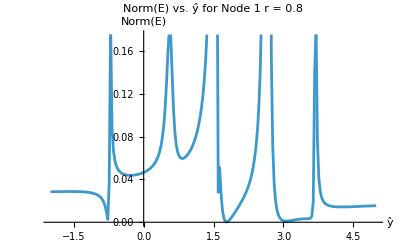

Evaluation time: 15.285375

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat1Array=Range[-2,5,0.03];
Δ1NormArray=Table[Δ1Norm[κ]/.{yHat->yHat1Array[[i]]},{i,1,Length@yHat1Array}];
ENorm1Array=Table[NIntegrate[Δ1NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat1Array}];

ListPlot[Transpose@{yHat1Array,ENorm1Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 1\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

### Node 0

```mathematica
𝔸0[κ_]=1+γ01 Cos[κ]+γ02 Cos[2 κ];
𝔹0[κ_]=γ01 Sin[κ]+γ02 Sin[2 κ];
ℂ0[κ_]=a00+a01 Cos[κ]+a02 Cos[2 κ]+a03 Cos[3 κ]+a04 Cos[4 κ];
𝔻0[κ_]=a01 Sin[κ]+a02 Sin[2 κ]+a03 Sin[3 κ]+a04 Sin[4 κ];
κBar0Re[κ_]=(-𝔸0[κ]*ℂ0[κ]-𝔹0[κ]*𝔻0[κ])/((𝔸0[κ])^2+(𝔹0[κ])^2);
κBar0Im[κ_]=(𝔹0[κ]*ℂ0[κ]-𝔸0[κ]*𝔻0[κ])/((𝔸0[κ])^2+(𝔹0[κ])^2);
κBar0Norm[κ_]=Abs[κBar0Re[κ]+I*κBar0Im[κ]];
```

```mathematica
Δ0Re[κ_]=(κ^2*((𝔸0[κ])^2+(𝔹0[κ])^2)-(-𝔸0[κ]*ℂ0[κ]-𝔹0[κ]*𝔻0[κ]))^2;
Δ0Im[κ_]=(0*((𝔸0[κ])^2+(𝔹0[κ])^2)-(𝔹0[κ]*ℂ0[κ]-𝔸0[κ]*𝔻0[κ]))^2;
Δ0Norm[κ_]=(κ^2-κBar0Norm[κ])^2;
```

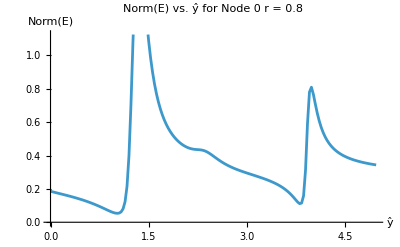

Evaluation time: 26.139979

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat0Array=Range[0,5,0.03];
Δ0NormArray=Table[Δ0Norm[κ]/.{yHat->yHat0Array[[i]]},{i,1,Length@yHat0Array}];
ENorm0Array=Table[NIntegrate[Δ0NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat0Array}];

ListPlot[Transpose@{yHat0Array,ENorm0Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 0\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

## Spectral Function

### Node 1

```mathematica
Clear[yHat]
SF1Re[κ_,yHat_]=κBar1Re[κ];
SF1Im[κ_,yHat_]=κBar1Im[κ];
SF1Norm[κ_,yHat_]=κBar1Norm[κ];
```

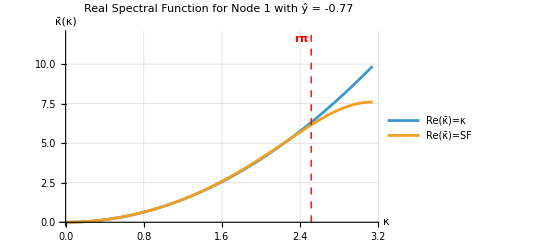

-Graphics-

-Graphics-

```mathematica
Clear[yHat]
r=0.8;
yHat1List={(*1*)-0.77,(*2*)-0.32,(*3*)0.82,(*4*)1.60,(*5*)1.75,(*6*)3.04,(*7*)3.58,(*8*)4.27};
yHat=yHat1List[[1]];
Plot[{κ^2,SF1Re[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Real Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
Plot[{0,SF1Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ^2,SF1Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Total Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
```

### Node 0

```mathematica
Clear[yHat]
SF0Re[κ_,yHat_]=κBar0Re[κ];
SF0Im[κ_,yHat_]=κBar0Im[κ];
SF0Norm[κ_,yHat_]=κBar0Norm[κ];
```

```mathematica
r=0.8;
yHat0List={(*1*)1.02,(*2*)3.81};
yHat=yHat0List[[1]];
Plot[{κ^2,SF0Re[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Real Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
Plot[{0,SF0Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ^2,SF0Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Total Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
```

-Graphics-

-Graphics-

-Graphics-

## Output Coefficients

### ŷ Definitions

```mathematica
Clear[yHat,yHat2,yHat1,yHat0]

yHat1List={(*1*)-0.77,(*2*)-0.32,(*3*)0.82,(*4*)1.60,(*5*)1.75,(*6*)3.04,(*7*)3.58,(*8*)4.27};
yHat0List={(*1*)1.02,(*2*)3.81};

yHat1=yHat1List[[5]];
yHat0=yHat0List[[1]];
```

### Define Coefficients

```mathematica
Clear[γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04]

{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04}/.bdCoeffs0)/.{yHat->yHat0};
```

### Luke Output

```mathematica
interiorLuke=interiorCoeffsC42nd/.{a1->a,a2->b,a3->c};
boundaryLuke={α12->γ01val,β12->γ02val,α21->γ10val,α22->γ12val,β22->γ13val,a1->a00val,b1->a01val,c1->a02val,d1->a03val,e1->a04val,a2->a10val,b2->a11val,c2->a12val,d2->a13val,e2->a14val};
coeffLuke=Flatten[Join[interiorLuke,boundaryLuke]]
```

{α→0.397556,β→0.0211854,a→0.520787,b→0.329174,α12→8.68447,β12→5.23345,α21→0.0452427,α22→2.1507,β22→0.423192,a1→10.4413,b1→-16.1628,c1→0.75861,d1→5.20609,e1→-0.24316,a2→0.834133,b2→0.949898,c2→-4.23536,d2→2.28448,e2→0.16684}

### Nate Output

```mathematica
interiorNate=interiorCoeffsC42nd;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]]
```

{α→0.397556,β→0.0211854,a1→0.520787,a2→0.329174,γ01→8.68447,γ02→5.23345,γ10→0.0452427,γ12→2.1507,γ13→0.423192,a00→10.4413,a01→-16.1628,a02→0.75861,a03→5.20609,a04→-0.24316,a10→0.834133,a11→0.949898,a12→-4.23536,a13→2.28448,a14→0.16684}

## Eigenvalue Spectral Analysis

### Modified Boundary Coefficients for Eigenvalue Analysis

```mathematica
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,4}]/.coeffNate;
intBars={α21Bar->((α-β*γ01)/(1-β*γ02)/.coeffNate),α23Bar->(α/(1-β*γ02)/.coeffNate),β24Bar->(β/(1-β*γ02)/.coeffNate),
a1Bar->((-a1-β*a01)/(1-β*γ02)/.coeffNate),a2Bar->((-β*a02)/(1-β*γ02)/.coeffNate),a3Bar->((a1-β*a03)/(1-β*γ02)/.coeffNate),a4Bar->((a2-β*a04)/(1-β*γ02)/.coeffNate)};

barCoeffs=Join[LHSBars,RHSBars1,intBars]
```

{γ12Bar→3.15262,γ13Bar→0.697082,a11Bar→2.76919,a12Bar→-7.03301,a13Bar→3.37502,a14Bar→0.29294,α21Bar→0.240204,α23Bar→0.44713,β24Bar→0.0238272,a1Bar→-0.200614,a2Bar→-0.0180755,a3Bar→0.461682,a4Bar→0.376015}

### Build Modified Matrices (needs cleaning badly)

```mathematica
Clear[LHS,RHS]
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=2;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["α"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["α"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["β"<>ToString[i]<>ToString[j]<>"Bar"],

If[(i==k&&j==k-1),ToExpression["γ"<>ToString[1]<>ToString[2]<>"Bar"],
If[(i==k&&j==k-2),ToExpression["γ"<>ToString[1]<>ToString[3]<>"Bar"],
If[(i==k-1&&j==k),ToExpression["α"<>ToString[2]<>ToString[1]<>"Bar"],
If[(i==k-1&&j==k-2),ToExpression["α"<>ToString[2]<>ToString[3]<>"Bar"],
If[(i==k-1&&j==k-3),ToExpression["β"<>ToString[2]<>ToString[4]<>"Bar"],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}]

k=9; (*Size*)
MatrixForm@LHS[k]

MatrixForm@(LHS[k]/.coeffNate)/.barCoeffs
```

(1 | γ12Bar | γ13Bar | 0 | 0 | 0 | 0 | 0 | 0
α21Bar | 1 | α23Bar | β24Bar | 0 | 0 | 0 | 0 | 0
β | α | 1 | α | β | 0 | 0 | 0 | 0
0 | β | α | 1 | α | β | 0 | 0 | 0
0 | 0 | β | α | 1 | α | β | 0 | 0
0 | 0 | 0 | β | α | 1 | α | β | 0
0 | 0 | 0 | 0 | β | α | 1 | α | β
0 | 0 | 0 | 0 | 0 | β24Bar | α23Bar | 1 | α21Bar
0 | 0 | 0 | 0 | 0 | 0 | γ13Bar | γ12Bar | 1)

(1 | 3.15262 | 0.697082 | 0 | 0 | 0 | 0 | 0 | 0
0.240204 | 1 | 0.44713 | 0.0238272 | 0 | 0 | 0 | 0 | 0
0.0211854 | 0.397556 | 1 | 0.397556 | 0.0211854 | 0 | 0 | 0 | 0
0 | 0.0211854 | 0.397556 | 1 | 0.397556 | 0.0211854 | 0 | 0 | 0
0 | 0 | 0.0211854 | 0.397556 | 1 | 0.397556 | 0.0211854 | 0 | 0
0 | 0 | 0 | 0.0211854 | 0.397556 | 1 | 0.397556 | 0.0211854 | 0
0 | 0 | 0 | 0 | 0.0211854 | 0.397556 | 1 | 0.397556 | 0.0211854
0 | 0 | 0 | 0 | 0 | 0.0238272 | 0.44713 | 1 | 0.240204
0 | 0 | 0 | 0 | 0 | 0 | 0.697082 | 3.15262 | 1)

```mathematica
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,

If[(i==2&&j==1),a1Bar,
If[(i==2&&j==2),a2Bar,
If[(i==2&&j==3),a3Bar,
If[(i==2&&j==4),a4Bar,

If[(i==k&&j==k),a11Bar,
If[(i==k&&j==k-1),a12Bar,
If[(i==k&&j==k-2),a13Bar,
If[(i==k&&j==k-3),a14Bar,

If[(i==k-1&&j==k),a1Bar,
If[(i==k-1&&j==k-1),a2Bar,
If[(i==k-1&&j==k-2),a3Bar,
If[(i==k-1&&j==k-3),a4Bar,


If[i-2==j,a2,
If[i-1==j,a1,
If[i==j,-2*(a1+a2),
If[i+1==j, a1,
If[i+2==j,a2,
0]]]]]]]]]]]]]]]]]]]]]]
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}]

k=11; (*Size*)
MatrixForm@RHS[k]

MatrixForm@(RHS[k]/.coeffNate)/.barCoeffs
```

(a11Bar | a12Bar | a13Bar | a14Bar | 0 | 0 | 0 | 0 | 0 | 0 | 0
a1Bar | a2Bar | a3Bar | a4Bar | 0 | 0 | 0 | 0 | 0 | 0 | 0
a2 | a1 | -2 (a1+a2) | a1 | a2 | 0 | 0 | 0 | 0 | 0 | 0
0 | a2 | a1 | -2 (a1+a2) | a1 | a2 | 0 | 0 | 0 | 0 | 0
0 | 0 | a2 | a1 | -2 (a1+a2) | a1 | a2 | 0 | 0 | 0 | 0
0 | 0 | 0 | a2 | a1 | -2 (a1+a2) | a1 | a2 | 0 | 0 | 0
0 | 0 | 0 | 0 | a2 | a1 | -2 (a1+a2) | a1 | a2 | 0 | 0
0 | 0 | 0 | 0 | 0 | a2 | a1 | -2 (a1+a2) | a1 | a2 | 0
0 | 0 | 0 | 0 | 0 | 0 | a2 | a1 | -2 (a1+a2) | a1 | a2
0 | 0 | 0 | 0 | 0 | 0 | 0 | a4Bar | a3Bar | a2Bar | a1Bar
0 | 0 | 0 | 0 | 0 | 0 | 0 | a14Bar | a13Bar | a12Bar | a11Bar)

(2.76919 | -7.03301 | 3.37502 | 0.29294 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.200614 | -0.0180755 | 0.461682 | 0.376015 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.329174 | 0.520787 | -1.69992 | 0.520787 | 0.329174 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.329174 | 0.520787 | -1.69992 | 0.520787 | 0.329174 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.329174 | 0.520787 | -1.69992 | 0.520787 | 0.329174 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.329174 | 0.520787 | -1.69992 | 0.520787 | 0.329174 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.329174 | 0.520787 | -1.69992 | 0.520787 | 0.329174 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.329174 | 0.520787 | -1.69992 | 0.520787 | 0.329174 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.329174 | 0.520787 | -1.69992 | 0.520787 | 0.329174
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.376015 | 0.461682 | -0.0180755 | -0.200614
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.29294 | 3.37502 | -7.03301 | 2.76919)

### Plot Eigenvalue Spectra

```mathematica
k=160;
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=(Eigenvalues[mat])^(1/2);

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->All,PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0/5,yHat1/5,1]]
```

-Graphics-

## Dendro Output

### Hide

```mathematica
derivativeOrder=2;
interiorOrder=n;
totalBoundRows=numBoundaryRows;
freeInteriorParameters={};
freeBoundaryParameters={};
RHSInteriorList=RHSPars;
interiorParametersValues=interiorCoeffsC42nd/.{α->alpha,β->beta};
boundaryParametersValues=boundaryLuke/.{α12->gamma01,β12->gamma02,α21->gamma10,α22->gamma12,β22->gamma13,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14};
LHSBoundaryList={gamma01,gamma02,gamma10,gamma12,gamma13};
RHSBoundaryList={a00,a01,a02,a03,a04,a10,a11,a12,a13,a14};
(*Don't need to mess with these until we incorporate this procedure with James's filtering*)
filterIntCoeff;
filterBoundCoeff;
filterIntParam;
filterBoundParam;
filtering=False;
(*boundary={α12->γ01,β12->γ02,α21->γ10,α22->γ12,β22->γ13,β31->γ20,α31->γ21,α32->γ23,β32->γ24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};*)
```

```mathematica
(*****************Print coefficients in Dendro-GR Format*****************)
If[derivativeOrder==1,
LHSName="P1";
RHSName="Q1";
nth="1st";
coeffs="D_coeffs";
order="First",
If[derivativeOrder==2,
LHSName="P2";
RHSName="Q2";
nth="2nd";
coeffs="D_coeffs";
order="Second"]];
If[LHSBandCount==3,
LHSStructure="T",
If[LHSBandCount==5,
LHSStructure="P"]];

(*Convert Mathematica expression syntax to C/C++ expression syntax*)
convertToCCode[expr_]:=Module[{str},str=ToString[expr,InputForm];
(*Add ".0" to standalone integers but not to variables with numbers*)
(*Formatting adjustments to match C/C++ syntax*)str=StringReplace[str,{" "->"","*"->" * ","/"->" / ","+"->" + ","-"->" - ","^"->" ^ "}];
str]
(*Function to generate the line of C/C++ code to define the fixed variables*)
generateCAssignment[rule_]:=Module[{variable,expression,cCode,cAssignment},
variable=ToString[rule[[1]]];
expression=rule[[2]];
cCode=convertToCCode[expression];
cAssignment="double "<>variable<>" = "<>cCode<>";";
cAssignment
]






(*Initial Block*)
initialBlock=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order"}];
initialBlock2=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order","Filtered"}];

(*Free Parameters Block*)
freeParameters=Join[freeInteriorParameters,freeBoundaryParameters];
numFreePars=Length[freeParameters];
alphaPrint=StringReplace[generateCAssignment[Select[interiorParametersValues,#[[1]]===alpha&][[1]]],"alpha"->"alpha0"];
freeParPrints={};
If[numFreePars>0,
For[i=1,i<=numFreePars,i++,
AppendTo[freeParPrints,StringJoin[{"\n\t\tdouble ",ToString[freeParameters[[i]]]," = ",coeffs,"[",ToString[i],"];"}]]]]
freeParametersBlock=StringJoin[{"\t",alphaPrint,"\n\t\tdouble alpha = alpha0 + ",coeffs,"[0];",freeParPrints}];

(*Filter*)
freeParPrints2={};
freeParametersBlock2=StringJoin[{"\t","\n\t\tdouble alpha = ","F_coeffs","[0];",If[LHSBandCount==5,StringJoin["\n\t\tdouble beta = ","F_coeffs","[1];"],""]}];

(*Fixed Parameters Block*)
(*Create a list of the solved fixed parameters in C/C++ syntax*)
interiorParametersValues3=DeleteCases[interiorParametersValues,Rule[alpha,_]];
interiorParameterPrints=Table[
generateCAssignment[interiorParametersValues3[[i]]],
{i,1,Length[interiorParametersValues]-1}
];
boundaryParameterPrints=Table[
generateCAssignment[boundaryParametersValues[[i]]],
{i,1,Length[boundaryParametersValues]}
];
(*For filtered coefficients*)
interiorParameterPrints2=Table[
generateCAssignment[filterIntCoeff[[i]]],
{i,1,Length[filterIntCoeff]}
];
boundaryParameterPrints2=Table[
generateCAssignment[filterBoundCoeff[[i]]],
{i,1,Length[filterBoundCoeff]}
];
(*Print the coefficients in a single block of text rather than individual lines*)
fixedParametersBlockD=StringJoin["\t\t",Riffle[Join[interiorParameterPrints,boundaryParameterPrints],"\n\t\t"]];
fixedParametersBlockD2=StringJoin["\t\t",Riffle[Join[interiorParameterPrints2,boundaryParameterPrints2],"\n\t\t"]];

(*Structure Block*)
(*LHS Boundary*)
PDiagBoundary="";
LHSRowList=ToExpression[GatherBy[LHSBoundaryList,StringDrop[ToString[#],5]~StringTake~1&]];
For[i=1,i<=Length[LHSRowList],i++,
If[i==1,PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t","{1.0, ",StringDrop[ToString[LHSRowList[[i]]],1],","]];
If[i==2,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1}]],1],","]]];
If[i==3,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{","0.0, ",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t",StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
If[i>=4,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],StringDrop[StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
];
(*LHS Filter Boundary*)
RDiagBoundary="";
For[i=1,i<=Length@filterBoundParam,i++,
If[i==1,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha, beta},"]];
];
If[i==2,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha 1.0, alpha, beta},"]];
];
If[i>=3,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],"alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],"beta, alpha, 1.0, alpha, beta},"]];
];
];

(*LHS Interior*)
If[LHSBandCount==3,
PDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
PDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];
(*LHS Filter Interior*)
If[LHSBandCount==3,
RDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
RDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];

(*RHS Boundary*)
QDiagBoundary="";
RHSRowList=ToExpression[GatherBy[RHSBoundaryList,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList],i++,QDiagBoundary=StringJoin[QDiagBoundary,"\n\t\t\t",ToString[RHSRowList[[i]]],","]]
(*RHS Filter Boundary*)
SDiagBoundary="";
RHSRowList2=ToExpression[GatherBy[filterBoundParam,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList2],i++,SDiagBoundary=StringJoin[SDiagBoundary,"\n\t\t\t",ToString[RHSRowList2[[i]]]]]

(*RHS Interior*)
QDiagInterior={};
len=(2*Length[RHSInteriorList]+1);
If[derivativeOrder==1,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[-RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"0.0"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]
],
If[derivativeOrder==2,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"t1"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]]]]

(*RHS Filter Interior*)
SDiagInterior={};
newFilterIntParam=Drop[filterIntParam,1];
len=(2*Length[newFilterIntParam]+1);
For[i=1,i<=len,i++,
If[i<=Length[newFilterIntParam],PrependTo[SDiagInterior,ToString[newFilterIntParam[[i]]]<>"/"<>ToString[2]<>".0"]];
If[i==(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,"a0"]];
If[i>(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,ToString[newFilterIntParam[[i-Length[newFilterIntParam]-1]]]<>"/"<>ToString[2]<>".0"]]
]


PDiagBoundaryStr=StringDrop[StringDrop[PDiagBoundary,1],-1];
PDiagInteriorStr=StringDrop[StringDrop[PDiagInterior,1],-1];
RDiagBoundaryStr=StringDrop[StringDrop[RDiagBoundary,1],-1];
RDiagInteriorStr=StringDrop[StringDrop[RDiagInterior,1],-1];
QDiagBoundaryStr=StringDrop[StringDrop[QDiagBoundary,1],-1];
QDiagInteriorStr=StringDrop[StringDrop[ToString[QDiagInterior],1],-1];
SDiagBoundaryStr=StringDrop[SDiagBoundary,1];
SDiagInteriorStr=StringDrop[StringDrop[ToString[SDiagInterior],1],-1];

(*Subscript[t, 1] is the middle RHS Interior Coefficient for Second Derivatives*)
t1List={};
For[i=1,i<=Length[RHSInteriorList],i++,
AppendTo[t1List,ToString[RHSInteriorList[[i]]]]
];
If[derivativeOrder==1,
t1="",
If[derivativeOrder==2,
t1=StringJoin["-2.0 * ("<>ToString[Total[t1List]]<>")"]]];


If[filtering,
filterFinalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock2,"(\n","\tconst std::vector<double>& ","F_coeffs",") {\n","\t",freeParametersBlock2,"\n\n",fixedParametersBlockD2,"\n\n","\t\t// boundary elements for R matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","R","DiagBoundary{\n",RDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for R matrix for ",nth," derivative\n","\t\tstd::vector<double> ","R","DiagInterior{\n","\t\t\t",RDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for S matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","S","DiagBoundary\n",SDiagBoundaryStr,"\n","\t\t;\n\n","\t\t// diagonal elements for S matrix for ",nth," derivative\n","\t\tstd::vector<double> ","S","DiagInterior{\n","\t\t\t",SDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t","R","DiagInterior, ","S","DiagInterior, ","S","DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}"}];
]

finalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock,"(\n","\tconst std::vector<double>& ",coeffs,") {\n","\t",freeParametersBlock,"\n\n",fixedParametersBlockD,"\n\n","\t\t// boundary elements for P matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",LHSName,"DiagBoundary{\n",PDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for P matrix for ",nth," derivative\n","\t\tstd::vector<double> ",LHSName,"DiagInterior{\n","\t\t\t",PDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",RHSName,"DiagBoundary{\n",QDiagBoundaryStr,"\n","\t\t};\n\n",If[derivativeOrder==1,t1,If[derivativeOrder==2,"\t\tdouble t1 = "<>t1<>";\n"]],"\t\t// diagonal elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<double> ",RHSName,"DiagInterior{\n","\t\t\t",QDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t",LHSName,"DiagInterior, ",LHSName,"DiagBoundary, ",RHSName,"DiagInterior, ",RHSName,"DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}",If[filtering,"\n\n"<>filterFinalBlock,""]}];
```

GatherBy::list: List expected at position 1 in GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&].

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Drop::drop: Cannot drop positions 1 through 1 in filterIntParam.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

StringDrop::drop: Cannot drop positions 1 through 1 in "".

### Show

```mathematica
outExt="h";
(*Print header*)
Print[Style["Dendro-Ready Coefficients (Copied to clipboard):",Bold,FontSize->24]];
Print[finalBlock];
(*Copy the block of text to the user's clipboard*)
CopyToClipboard[finalBlock];

(*Save to output file*)
fileName=StringJoin[{"BYU_C4_2nd","_yHat0_",ToString[yHat0],"_yHat1_",ToString[yHat1],".",outExt}];
Export[fileName,finalBlock,"Text"];
Print[StringJoin[{"Saved to file: ",fileName}]]
```

Dendro-Ready Coefficients (Copied to clipboard):

MatrixDiagonalEntries* BYUDerivsP4R3DiagonalsSecondOrder(
	const std::vector<double>& D_coeffs) {
		double alpha0 = 0.4917593294116515;
		double alpha = alpha0 + D_coeffs[0];

		double beta = 0.052107304747970096;
		double a1 = 0.2456096922476715;
		double a2 = 0.42112296480247163;
		double a3 = 0.017514635206853885;
		double gamma01 = 12.591315362048217;
		double gamma02 = 15.084784378502926;
		double gamma10 = 0.04577667520869812;
		double gamma12 = 2.729394168475708;
		double gamma13 = 0.8864282136850647;
		double gamma20 = 0.010921427140866557;
		double gamma21 = 0.2834351283963115;
		double gamma23 = 0.7199728999288171;
		double gamma24 = 0.11937767266180463;
		double a00 = 12.874331545332872;
		double a01 =  - 7.791236348900909;
		double a02 =  - 25.746221106082196;
		double a03 = 24.030231590355;
		double a04 =  - 4.139878085038264;
		double a05 = 0.8841382958263313;
		double a06 =  - 0.11136589149817189;
		double a10 = 0.7792149930252243;
		double a11 = 1.717844024789377;
		double a12 =  - 5.133534136228278;
		double a13 = 1.9613187453898757;
		double a14 = 0.7121824953413769;
		double a15 =  - 0.038694764010443694;
		double a16 = 0.0016686416993604049;
		double a20 = 0.20186732531628773;
		double a21 = 0.7305871669560142;
		double a22 =  - 1.3289567001530833;
		double a23 =  - 0.27972025346441187;
		double a24 = 0.6127265401353884;
		double a25 = 0.06539469405721846;
		double a26 =  - 0.0018987728473575086;

		// boundary elements for P matrix for 2nd derivative
		std::vector<std::vector<double>> P2DiagBoundary{
			{1.0, gamma01, gamma02},
			{gamma10, 1.0, gamma12, gamma13},
			{gamma20, gamma21, 1.0, gamma23, gamma24}
		};

		// diagonal elements for P matrix for 2nd derivative
		std::vector<double> P2DiagInterior{
			beta, alpha, 1.0, alpha, beta
		};

		// boundary elements for Q matrix for 2nd derivative
		std::vector<std::vector<double>> Q2DiagBoundary{
			{a00, a01, a02, a03, a04, a05, a06},
			{a10, a11, a12, a13, a14, a15, a16},
			{a20, a21, a22, a23, a24, a25, a26}
		};

		double t1 = -2.0 * (a1 + a2 + a3);
		// diagonal elements for Q matrix for 2nd derivative
		std::vector<double> Q2DiagInterior{
			a3, a2, a1, t1, a1, a2, a3
		};

		// store the entries for matrix creation
		MatrixDiagonalEntries* diagEntries = new
			MatrixDiagonalEntries{
				P2DiagInterior, P2DiagBoundary, Q2DiagInterior, Q2DiagBoundary
			};
		return diagEntries;
	}

Saved to file: BYU_A4_2nd_yHat0_0._yHat1_2.7_yHat2_1.8.h

# P6 (A6) Scheme

## Initialization

The matrix system of equations we are solving for this scheme is:
	P=(1
γ_10
γ_20
0
0
0
0 γ_01
1
γ_21
β
0
0
0 γ_02
γ_12
1
α
γ_24
0
0 0
γ_13
γ_23
1
γ_23
γ_13
0 0
0
γ_24
α
1
γ_12
γ_02 0
0
0
β
γ_21
1
γ_01 0
0
0
0
γ_20
γ_10
1)
	Q=(a_00
a_10
a_20
a_3
a_26
a_16
a_06 a_01
a_11
a_21
a_2
a_25
a_15
a_05 a_02
a_12
a_22
a_1
a_24
a_14
a_04 a_03
a_13
a_23
-2s
a_23
a_13
a_03 a_04
a_14
a_24
a_1
a_22
a_12
a_02 a_05
a_15
a_25
a_2
a_21
a_11
a_01 a_06
a_16
a_26
a_3
a_20
a_10
a_00)
Note that:
	s=a_1+a_2+a_3

```mathematica
(*From KimInteriorOptimization.nb, one day to be merged with this one. Or I could DumpSave[] in that notebook and then Get[] here.*)
interiorCoeffsA62nd={α->0.4631165969478096,β->0.0428502505546325,a1->0.32943690520352964,a2->0.39288484117098216,a3->0.012328602790825066};

(*If you have the .mx files in the same directory as this notebook, these will let you skip the long computation of defining bdCoeffs under the "Solve for Boundary Coefficients" section*)
Get["A6_2nd_interiorCoeffs.mx"]
Get["A6_2nd_bdCoeffs0.mx"]
Get["A6_2nd_bdCoeffs1.mx"]
Get["A6_2nd_bdCoeffs2.mx"]
```

## General Extrapolation Polynomial

The only settings the user should have to change for a different (second derivative) scheme are:
	- LHSBandCount
	- n
	- freeInteriorPars
	- yDeriv
For the P6 (A6) scheme, we have:
	LHSBandCount = 5
	n = 6
	freeInteriorPars = 2
	yDeriv = 9

```mathematica
(*User chooses these parameters, the rest is calculated from these*)
LHSBandCount=5; (*3 for tridiagonal, 5 for pentadiagonal*)
n=6; (*order of the scheme*)
freeInteriorPars=2; (*number of free parameters used for Kim's optimization on the interior*)
yDeriv=9; (*(d^n P)/dx^n(ŷ)=0 from Kim 2024 Eq. 10, this is n in that equation*) (*provide constraints on what the user can choose for this. Upper bound should be polynomialorder to prevent the matrix from being singular, and lower bound should be order·2 I think.*)

LHSPars=Switch[LHSBandCount,3,{α},5,{α,β}];
RHSPars=Table[ToExpression[StringJoin["a",ToString[i]]],{i,1,Ceiling[n/2]-Length@LHSPars+freeInteriorPars}];
numBoundaryRows=Length@RHSPars;
fOrder=(2*Length@RHSPars)+1;
fppOrder=LHSBandCount+(numBoundaryRows-(LHSBandCount-1)/2);
PolynomialOrder=fOrder+fppOrder;


rowf1=Join[{1},Table[0,{i,1,PolynomialOrder}]];
rowf=Table[Table[i^j,{j,0,PolynomialOrder}],{i,1,fOrder-1}];
rowfpp1=Join[{0,0,2},Table[0,{i,3,PolynomialOrder}]];
rowfpp=Table[Table[j (j-1) i^(j-2),{j,0,PolynomialOrder}],{i,1,fppOrder-1}];
rowyHat=Join[Table[0,{i,1,yDeriv}],Table[(i!)/((i-yDeriv)!) yHat^(i-yDeriv),{i,yDeriv,PolynomialOrder}]];

matf=PrependTo[rowf,rowf1];
matfpp=PrependTo[rowfpp,rowfpp1];
matfCombined=Join[matf,matfpp];
LMat=AppendTo[matfCombined,rowyHat];

pVec=Table[ToExpression[StringJoin["p",ToString[i]]],{i,0,PolynomialOrder}];
fVec=Join[Table[ToExpression[StringJoin["f",ToString[i]]],{i,0,fOrder-1}],Table[ToExpression[StringJoin["fpp",ToString[i]]],{i,0,fppOrder-1}],{0}];

pCoeffs=Solve[LMat.pVec==fVec,pVec][[1]];

yHatSingularities=(Transpose@Solve[Det[LMat]==0,yHat])[[1]]//N;
P[x_]=Total[Table[pVec[[i+1]]*x^i,{i,0,PolynomialOrder}]]/.pCoeffs;

Print["System:\n",MatrixForm[LMat]," ",MatrixForm[pVec]," = ",MatrixForm[fVec]]
Print["Singularities:\n",MatrixForm[yHatSingularities]]
(*Print["Coefficients:\n",MatrixForm[pCoeffs]]*)
```

System:
(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 4 | 8 | 16 | 32 | 64 | 128 | 256 | 512 | 1024 | 2048 | 4096 | 8192
1 | 3 | 9 | 27 | 81 | 243 | 729 | 2187 | 6561 | 19683 | 59049 | 177147 | 531441 | 1594323
1 | 4 | 16 | 64 | 256 | 1024 | 4096 | 16384 | 65536 | 262144 | 1048576 | 4194304 | 16777216 | 67108864
1 | 5 | 25 | 125 | 625 | 3125 | 15625 | 78125 | 390625 | 1953125 | 9765625 | 48828125 | 244140625 | 1220703125
1 | 6 | 36 | 216 | 1296 | 7776 | 46656 | 279936 | 1679616 | 10077696 | 60466176 | 362797056 | 2176782336 | 13060694016
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 6 | 12 | 20 | 30 | 42 | 56 | 72 | 90 | 110 | 132 | 156
0 | 0 | 2 | 12 | 48 | 160 | 480 | 1344 | 3584 | 9216 | 23040 | 56320 | 135168 | 319488
0 | 0 | 2 | 18 | 108 | 540 | 2430 | 10206 | 40824 | 157464 | 590490 | 2165130 | 7794468 | 27634932
0 | 0 | 2 | 24 | 192 | 1280 | 7680 | 43008 | 229376 | 1179648 | 5898240 | 28835840 | 138412032 | 654311424
0 | 0 | 2 | 30 | 300 | 2500 | 18750 | 131250 | 875000 | 5625000 | 35156250 | 214843750 | 1289062500 | 7617187500
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 362880 | 3628800 yHat | 19958400 yHat^2 | 79833600 yHat^3 | 259459200 yHat^4) (p0
p1
p2
p3
p4
p5
p6
p7
p8
p9
p10
p11
p12
p13) = (f0
f1
f2
f3
f4
f5
f6
fpp0
fpp1
fpp2
fpp3
fpp4
fpp5
0)

Singularities:
(yHat→2.42303
yHat→3.57697
yHat→1.35669
yHat→4.64331)

## Solve for Boundary Coefficients

Goal:
	Solve a system of equations for bdCoeffsList2 in terms of the optimization free parameter ŷ
Variables:
	fVars2: List of f_i and f_i' variables that will appear in the shifted stencil for Node 2
	bdCoeffsList2: List of boundary coefficients that will appear in the shifted stencil for Node 2
	schemeShifted: The shifted scheme for Node 2 (Kim 2024 Eq. 13a)
	schemeCentered: The centered scheme for Node 2 in terms of the extrapolation polynomial P(x) (Kim 2024 Eq. 12a)
		NOTE: To make the Collect[] process easier, we write these schemes as LHS-RHS=0 rather than the usual LHS=RHS.
	schemeNode3: The scheme for Node 3, which only depends on interiorCoeffsP4
	SOLfp5: The solution to Node 3’s scheme equation for f_5' in terms of fVars2
	eq: Scheme equation where the coefficient terms from schemeCentered and schemeShifted are set equal to each other
	coeffEqs2: System of equations with each of the coefficient terms equal to each other
	bdCoeffs2: Solution to the system of equations for bdCoeffsList2 in terms of ŷ
Process:
	1. Initialize the necessary equations.
	2. We want schemeShifted and schemeCentered to both be in terms of fVars2 with some coefficients. Due to the presence of P(x) terms in schemeCentered, it is in terms of fVars2 as well as f_5'. We eliminate the dependence on f_5' by using Node 3’s scheme to solve for f_5' in terms of fVars2.
	3. Now that schemeShifted and schemeCentered are both in terms of fVars2, we construct a system of equations by equating the coefficient in front of each term of fVars2 in schemeCentered with the corresponding coefficient in front of the same term in schemeShifted.
	4. We solve this system of equations for bdCoeffsList2 in terms of interiorCoeffsP4 (which are substituted in) and the optimization free parameter ŷ.
		NOTE: In the standard scheme approach, we set γ_22=1 to ensure the main diagonal of the LHS matrix is all 1’s. When solving this system of equations, we must include γ_22 so that bdCoeffsList2 and fVars2 have the same length since this allows us to find a unique solution to the system of equations. We apply the normal condition later on.
	5. OPTIONAL: We may save the variable bdCoeffs2 to a binary file in the current directory. This is helpful to avoid having to run this process multiple times, as it can become computationally expensive.
Differences:
	For Node 1 and Node 0, the entire process translates directly with a few changes. fVars, bdCoeffsList, schemeShifted, and schemeCentered all change, as we are considering the scheme for a different row, but the equations have the same structure. The main notable difference is in Step 2; In addition to substituting in the solution from Node 3 for f_5' in terms of the other fVars, we must also do the same for f_4' (Nodes 1 and 0) and f_3' (Node 0) using Nodes 2 and 1, respectively.

### Node 2

```mathematica
(*----------STEP 1----------*)
a0=-2 (a1+a2+a3);
fVars2={fpp0,fpp1,fpp2,fpp3,fpp4,f0,f1,f2,f3,f4,f5,f6};
bdCoeffsList2={γ20,γ21,γ22,γ23,γ24,a20,a21,a22,a23,a24,a25,a26};
schemeShifted=γ20 fpp0+γ21 fpp1+γ22 fpp2+γ23 fpp3+γ24 fpp4-(a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6); (*==0*)
schemeCentered=β fpp0+α fpp1+fpp2+α fpp3+β fpp4-(a3 P[-1]+a2 f0+a1 f1+a0 f2+a1 f3+a2 f4+a3 f5); (*==0*)

(*----------STEP 2----------*)
schemeNode3=β fpp1+α fpp2+fpp3+α fpp4+β fpp5==a3 f0+a2 f1+a1 f2+a0 f3+a1 f4+a2 f5+a3 f6;
SOLfpp5=Solve[schemeNode3,fpp5][[1,1]]/.interiorCoeffsA62nd;
schemeCentered=schemeCentered/.SOLfpp5;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars2];

(*----------STEP 4----------*)
coeffEqs2=Table[Coefficient[eq,fVars2[[i]]]==0,{i,1,Length@fVars2}];
bdCoeffs2=(Solve[coeffEqs2,bdCoeffsList2][[1]])/.interiorCoeffsA62nd;

(*----------STEP 5----------*)
DumpSave["A6_2nd_bdCoeffs2.mx","Global`bdCoeffs2"]
```

{Global`bdCoeffs2}

### Node 1

```mathematica
(*----------STEP 1----------*)
a0=-2 (a1+a2+a3);
fVars1={fpp0,fpp1,fpp2,fpp3,f0,f1,f2,f3,f4,f5,f6};
bdCoeffsList1={γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14,a15,a16};
schemeShifted=γ10 fpp0+γ11 fpp1+γ12 fpp2+γ13 fpp3-(a10 f0+a11 f1+a12 f2+a13 f3+a14 f4+a15 f5+a16 f6); (*==0*)
schemeCentered=β P''[-1]+α fpp0+fpp1+α fpp2+β fpp3-(a3 P[-2]+a2 P[-1]+a1 f0+a0 f1+a1 f2+a2 f3+a3 f4); (*==0*)

(*----------STEP 2----------*)
schemeNode3=β fpp1+α fpp2+fpp3+α fpp4+β fpp5==a3 f0+a2 f1+a1 f2+a0 f3+a1 f4+a2 f5+a3 f6;
schemeNode2=γ20 fpp0+γ21 fpp1+γ22 fpp2+γ23 fpp3+γ24 fpp4==a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6;

SOLfpp5=Solve[schemeNode3,fpp5][[1,1]]/.interiorCoeffsA62nd;
SOLfpp4=Solve[schemeNode2,fpp4][[1,1]]/.bdCoeffs2;
schemeCentered=schemeCentered/.SOLfpp5/.SOLfpp4;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars1];

(*----------STEP 4----------*)
coeffEqs1=Table[Coefficient[eq,fVars1[[i]]]==0,{i,1,Length@fVars1}];
bdCoeffs1=(Solve[coeffEqs1,bdCoeffsList1][[1]])/.interiorCoeffsA62nd;

(*----------STEP 5----------*)
DumpSave["A6_2nd_bdCoeffs1.mx","Global`bdCoeffs1"]
```

{Global`bdCoeffs1}

### Node 0

```mathematica
(*----------STEP 1----------*)
a0=-2 (a1+a2+a3);
fVars0={fpp0,fpp1,fpp2,f0,f1,f2,f3,f4,f5,f6};
bdCoeffsList0={γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06};
schemeShifted=γ00 fpp0+γ01 fpp1+γ02 fpp2-(a00 f0+a01 f1+a02 f2+a03 f3+a04 f4+a05 f5+a06 f6); (*==0*)
schemeCentered=β P''[-2]+α P''[-1]+fpp0+α fpp1+β fpp2-(a3 P[-3]+a2 P[-2]+a1 P[-1]+a0 f0+a1 f1+a2 f2+a3 f3); (*==0*)

(*----------STEP 2----------*)
schemeNode3=β fpp1+α fpp2+fpp3+α fpp4+β fpp5==a3 f0+a2 f1+a1 f2+a0 f3+a1 f4+a2 f5+a3 f6;
schemeNode2=γ20 fpp0+γ21 fpp1+γ22 fpp2+γ23 fpp3+γ24 fpp4==a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6;
schemeNode1=γ10 fpp0+γ11 fpp1+γ12 fpp2+γ13 fpp3==a10 f0+a11 f1+a12 f2+a13 f3+a14 f4+a15 f5+a16 f6;

SOLfpp5=Solve[schemeNode3,fpp5][[1,1]]/.interiorCoeffsA62nd;
SOLfpp4=Solve[schemeNode2,fpp4][[1,1]]/.bdCoeffs2;
SOLfpp3=Solve[schemeNode1,fpp3][[1,1]]/.bdCoeffs1;
schemeCentered=schemeCentered/.SOLfpp5/.SOLfpp4/.SOLfpp3;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars0];

(*----------STEP 4----------*)
coeffEqs0=Table[Coefficient[eq,fVars0[[i]]]==0,{i,1,Length@fVars0}];
bdCoeffs0=(Solve[coeffEqs0,bdCoeffsList0][[1]])/.interiorCoeffsA62nd;

(*----------STEP 5----------*)
DumpSave["A6_2nd_bdCoeffs0.mx","Global`bdCoeffs0"]
```

{Global`bdCoeffs0}

## Optimize ŷ

### Set and Normalize Coefficients

We normalize the coefficients so that the main diagonal of the LHS matrix is all 1’s, but we leave the coefficients in terms of the optimization free parameter ŷ so that we can optimize over it.

```mathematica
Clear[γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26]
Clear[γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06]

{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}=1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2;
{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}=1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1;
{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}=1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0;
```

### Node 2

```mathematica
𝔸2[κ_]=γ20+γ21 Cos[κ]+Cos[2 κ]+γ23 Cos[3 κ]+γ24 Cos[4 κ];
𝔹2[κ_]=γ21 Sin[κ]+Sin[2 κ]+γ23 Sin[3 κ]+γ24 Sin[4 κ];
ℂ2[κ_]=a20+a21 Cos[κ]+a22 Cos[2 κ]+a23 Cos[3 κ]+a24 Cos[4 κ]+a25 Cos[5 κ]+a26 Cos[6 κ];
𝔻2[κ_]=a21 Sin[κ]+a22 Sin[2 κ]+a23 Sin[3 κ]+a24 Sin[4 κ]+a25 Sin[5 κ]+a26 Sin[6 κ];
κBar2Re[κ_]=(-𝔸2[κ]*ℂ2[κ]-𝔹2[κ]*𝔻2[κ])/((𝔸2[κ])^2+(𝔹2[κ])^2);
κBar2Im[κ_]=(𝔹2[κ]*ℂ2[κ]-𝔸2[κ]*𝔻2[κ])/((𝔸2[κ])^2+(𝔹2[κ])^2);
κBar2Norm[κ_]=Abs[κBar2Re[κ]+I*κBar2Im[κ]];
```

```mathematica
Δ2Re[κ_]=(κ^2*((𝔸2[κ])^2+(𝔹2[κ])^2)-(-𝔸2[κ]*ℂ2[κ]-𝔹2[κ]*𝔻2[κ]))^2;
Δ2Im[κ_]=(0*((𝔸2[κ])^2+(𝔹2[κ])^2)-(𝔹2[κ]*ℂ2[κ]-𝔸2[κ]*𝔻2[κ]))^2;
Δ2Norm[κ_]=(κ^2-κBar2Norm[κ])^2;
```

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat2Array=Range[0,5,0.03];
Δ2NormArray=Table[Δ2Norm[κ]/.{yHat->yHat2Array[[i]]},{i,1,Length@yHat2Array}];
ENorm2Array=Table[NIntegrate[Δ2NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat2Array}];

ListPlot[Transpose@{yHat2Array,ENorm2Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 2\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

-Graphics-

Evaluation time: 13.892292

### Node 1

```mathematica
𝔸1[κ_]=γ10+Cos[κ]+γ12 Cos[2 κ]+γ13 Cos[3 κ];
𝔹1[κ_]=Sin[κ]+γ12 Sin[2 κ]+γ13 Sin[3 κ];
ℂ1[κ_]=a10+a11 Cos[κ]+a12 Cos[2 κ]+a13 Cos[3 κ]+a14 Cos[4 κ]+a15 Cos[5 κ]+a16 Cos[6 κ];
𝔻1[κ_]=a11 Sin[κ]+a12 Sin[2 κ]+a13 Sin[3 κ]+a14 Sin[4 κ]+a15 Sin[5 κ]+a16 Sin[6 κ];
κBar1Re[κ_]=(-𝔸1[κ]*ℂ1[κ]-𝔹1[κ]*𝔻1[κ])/((𝔸1[κ])^2+(𝔹1[κ])^2);
κBar1Im[κ_]=(𝔹1[κ]*ℂ1[κ]-𝔸1[κ]*𝔻1[κ])/((𝔸1[κ])^2+(𝔹1[κ])^2);
κBar1Norm[κ_]=Abs[κBar1Re[κ]+I*κBar1Im[κ]];
```

```mathematica
Δ1Re[κ_]=(κ^2*((𝔸1[κ])^2+(𝔹1[κ])^2)-(-𝔸1[κ]*ℂ1[κ]-𝔹1[κ]*𝔻1[κ]))^2;
Δ1Im[κ_]=(0*((𝔸1[κ])^2+(𝔹1[κ])^2)-(𝔹1[κ]*ℂ1[κ]-𝔸1[κ]*𝔻1[κ]))^2;
Δ1Norm[κ_]=(κ^2-κBar1Norm[κ])^2;
```

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat1Array=Range[0,5,0.03];
Δ1NormArray=Table[Δ1Norm[κ]/.{yHat->yHat1Array[[i]]},{i,1,Length@yHat1Array}];
ENorm1Array=Table[NIntegrate[Δ1NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat1Array}];

ListPlot[Transpose@{yHat1Array,ENorm1Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 1\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

-Graphics-

Evaluation time: 17.302509

### Node 0

```mathematica
𝔸0[κ_]=1+γ01 Cos[κ]+γ02 Cos[2 κ];
𝔹0[κ_]=γ01 Sin[κ]+γ02 Sin[2 κ];
ℂ0[κ_]=a00+a01 Cos[κ]+a02 Cos[2 κ]+a03 Cos[3 κ]+a04 Cos[4 κ]+a05 Cos[5 κ]+a06 Cos[6 κ];
𝔻0[κ_]=a01 Sin[κ]+a02 Sin[2 κ]+a03 Sin[3 κ]+a04 Sin[4 κ]+a05 Sin[5 κ]+a06 Sin[6 κ];
κBar0Re[κ_]=(-𝔸0[κ]*ℂ0[κ]-𝔹0[κ]*𝔻0[κ])/((𝔸0[κ])^2+(𝔹0[κ])^2);
κBar0Im[κ_]=(𝔹0[κ]*ℂ0[κ]-𝔸0[κ]*𝔻0[κ])/((𝔸0[κ])^2+(𝔹0[κ])^2);
κBar0Norm[κ_]=Abs[κBar0Re[κ]+I*κBar0Im[κ]];
```

```mathematica
Δ0Re[κ_]=(κ^2*((𝔸0[κ])^2+(𝔹0[κ])^2)-(-𝔸0[κ]*ℂ0[κ]-𝔹0[κ]*𝔻0[κ]))^2;
Δ0Im[κ_]=(0*((𝔸0[κ])^2+(𝔹0[κ])^2)-(𝔹0[κ]*ℂ0[κ]-𝔸0[κ]*𝔻0[κ]))^2;
Δ0Norm[κ_]=(κ^2-κBar0Norm[κ])^2;
```

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat0Array=Range[0,5,0.03];
Δ0NormArray=Table[Δ0Norm[κ]/.{yHat->yHat0Array[[i]]},{i,1,Length@yHat0Array}];
ENorm0Array=Table[NIntegrate[Δ0NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat0Array}];

ListPlot[Transpose@{yHat0Array,ENorm0Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 0\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

-Graphics-

Evaluation time: 158.004289

## Spectral Function

### Node 2

```mathematica
Clear[yHat]
SF2Re[κ_,yHat_]=κBar2Re[κ];
SF2Im[κ_,yHat_]=κBar2Im[κ];
SF2Norm[κ_,yHat_]=κBar2Norm[κ];
```

```mathematica
r=0.8;
yHat2List={(*1*)0.75,(*2*)1.80,(*3*)3.27,(*4*)4.29};
yHat=yHat2List[[1]];
Plot[{κ^2,SF2Re[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Real Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
Plot[{0,SF2Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ^2,SF2Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Total Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
```

-Graphics-

-Graphics-

-Graphics-

### Node 1

```mathematica
Clear[yHat]
SF1Re[κ_,yHat_]=κBar1Re[κ];
SF1Im[κ_,yHat_]=κBar1Im[κ];
SF1Norm[κ_,yHat_]=κBar1Norm[κ];
```

```mathematica
Clear[yHat]
r=0.8;
yHat1List={(*1*)1.38,(*2*)2.70,(*3*)4.05};
yHat=yHat1List[[1]];
Plot[{κ^2,SF1Re[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Real Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
Plot[{0,SF1Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ^2,SF1Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Total Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
```

-Graphics-

-Graphics-

-Graphics-

### Node 0

```mathematica
Clear[yHat]
SF0Re[κ_,yHat_]=κBar0Re[κ];
SF0Im[κ_,yHat_]=κBar0Im[κ];
SF0Norm[κ_,yHat_]=κBar0Norm[κ];
```

```mathematica
r=0.8;
yHat0List={(*1*)-0.41,(*2*)1.44,(*3*)1.65,(*4*)3.51,(*5*)3.66};
yHat=yHat0List[[1]];
Plot[{κ^2,SF0Re[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Real Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
Plot[{0,SF0Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ^2,SF0Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Total Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
```

-Graphics-

$Aborted

$Aborted

## Output Coefficients

### ŷ Definitions

```mathematica
Clear[yHat,yHat2,yHat1,yHat0]

yHat2List={(*1*)0.75,(*2*)1.80,(*3*)3.27,(*4*)4.29};
yHat1List={(*1*)1.38,(*2*)2.70,(*3*)4.05};
yHat0List={(*1*)-0.41,(*2*)1.44,(*3*)1.65,(*4*)3.51,(*5*)3.66};

yHat2=yHat2List[[3]];
yHat1=yHat1List[[5]];
yHat0=yHat0List[[1]];
```

### Define Coefficients

```mathematica
Clear[γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26]
Clear[γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06]

{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0)/.{yHat->yHat0};
```

### Luke Output

```mathematica
interiorLuke=interiorCoeffsA62nd/.{a1->a,a2->b,a3->c};
boundaryLuke={α12->γ01val,β12->γ02val,α21->γ10val,α22->γ12val,β22->γ13val,β31->γ20val,α31->γ21val,α32->γ23val,β32->γ24val,a1->a00val,b1->a01val,c1->a02val,d1->a03val,e1->a04val,f1->a05val,g1->a06val,a2->a10val,b2->a11val,c2->a12val,d2->a13val,e2->a14val,f2->a15val,g2->a16val,a3->a20val,b3->a21val,c3->a22val,d3->a23val,e3->a24val,f3->a25val,g3->a26val};
coeffLuke=Flatten[Join[interiorLuke,boundaryLuke]]
```

{α→0.463117,β→0.0428503,a→0.329437,b→0.392885,c→0.0123286,α12→16.3567,β12→26.962,α21→0.0381356,α22→3.09746,β22→0.841185,β31→0.00678328,α31→0.209602,α32→1.26578,β32→0.274534,a1→15.0131,b1→3.39393,c1→-56.8335,d1→44.4449,e1→-7.15133,f1→1.25351,g1→-0.12063,a2→0.718786,b2→2.31705,c2→-6.26683,d2→2.68657,e2→0.565803,f2→-0.0219404,g2→0.000565896,a3→0.135023,b3→0.769294,c3→-0.510316,d3→-1.67372,e3→1.12147,f3→0.162875,g3→-0.0046273}

### Nate Output

```mathematica
interiorNate=interiorCoeffsA62nd;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]]
```

{α→0.463117,β→0.0428503,a1→0.329437,a2→0.392885,a3→0.0123286,γ01→16.3567,γ02→26.962,γ10→0.0381356,γ12→3.09746,γ13→0.841185,γ20→0.00678328,γ21→0.209602,γ23→1.26578,γ24→0.274534,a00→15.0131,a01→3.39393,a02→-56.8335,a03→44.4449,a04→-7.15133,a05→1.25351,a06→-0.12063,a10→0.718786,a11→2.31705,a12→-6.26683,a13→2.68657,a14→0.565803,a15→-0.0219404,a16→0.000565896,a20→0.135023,a21→0.769294,a22→-0.510316,a23→-1.67372,a24→1.12147,a25→0.162875,a26→-0.0046273}

## Eigenvalue Spectral Analysis

### Modified Boundary Coefficients for Eigenvalue Analysis

```mathematica
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,6}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,6}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2]
```

{γ12Bar→5.5,γ13Bar→2.23585,γ21Bar→0.0706594,γ23Bar→2.48561,γ24Bar→0.611373,a11Bar→5.81462,a12Bar→-10.8962,a13Bar→2.63575,a14Bar→2.22877,a15Bar→-0.185377,a16Bar→0.0137316,a21Bar→0.795362,a22Bar→1.34593,a23Bar→-4.79147,a24Bar→2.27333,a25Bar→0.371405,a26Bar→-0.0105289}

### Build Modified Matrices (needs cleaning badly)

```mathematica
Clear[LHS,RHS]
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],

If[(i==k&&j==k-1),ToExpression["γ"<>ToString[1]<>ToString[2]<>"Bar"],
If[(i==k&&j==k-2),ToExpression["γ"<>ToString[1]<>ToString[3]<>"Bar"],
If[(i==k-1&&j==k),ToExpression["γ"<>ToString[2]<>ToString[1]<>"Bar"],
If[(i==k-1&&j==k-2),ToExpression["γ"<>ToString[2]<>ToString[3]<>"Bar"],
If[(i==k-1&&j==k-3),ToExpression["γ"<>ToString[2]<>ToString[4]<>"Bar"],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}]

k=9; (*Size*)
MatrixForm@LHS[k]

MatrixForm@(LHS[k]/.coeffNate)/.barCoeffs
```

(1 | γ12Bar | γ13Bar | 0 | 0 | 0 | 0 | 0 | 0
γ21Bar | 1 | γ23Bar | γ24Bar | 0 | 0 | 0 | 0 | 0
β | α | 1 | α | β | 0 | 0 | 0 | 0
0 | β | α | 1 | α | β | 0 | 0 | 0
0 | 0 | β | α | 1 | α | β | 0 | 0
0 | 0 | 0 | β | α | 1 | α | β | 0
0 | 0 | 0 | 0 | β | α | 1 | α | β
0 | 0 | 0 | 0 | 0 | γ24Bar | γ23Bar | 1 | γ21Bar
0 | 0 | 0 | 0 | 0 | 0 | γ13Bar | γ12Bar | 1)

(1 | 5.5 | 2.23585 | 0 | 0 | 0 | 0 | 0 | 0
0.0706594 | 1 | 2.48561 | 0.611373 | 0 | 0 | 0 | 0 | 0
0.0428503 | 0.463117 | 1 | 0.463117 | 0.0428503 | 0 | 0 | 0 | 0
0 | 0.0428503 | 0.463117 | 1 | 0.463117 | 0.0428503 | 0 | 0 | 0
0 | 0 | 0.0428503 | 0.463117 | 1 | 0.463117 | 0.0428503 | 0 | 0
0 | 0 | 0 | 0.0428503 | 0.463117 | 1 | 0.463117 | 0.0428503 | 0
0 | 0 | 0 | 0 | 0.0428503 | 0.463117 | 1 | 0.463117 | 0.0428503
0 | 0 | 0 | 0 | 0 | 0.611373 | 2.48561 | 1 | 0.0706594
0 | 0 | 0 | 0 | 0 | 0 | 2.23585 | 5.5 | 1)

```mathematica
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,

If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,

If[(i==k&&j==k),a11Bar,
If[(i==k&&j==k-1),a12Bar,
If[(i==k&&j==k-2),a13Bar,
If[(i==k&&j==k-3),a14Bar,
If[(i==k&&j==k-4),a15Bar,
If[(i==k&&j==k-5),a16Bar,
If[(i==k-1&&j==k),a21Bar,
If[(i==k-1&&j==k-1),a22Bar,
If[(i==k-1&&j==k-2),a23Bar,
If[(i==k-1&&j==k-3),a24Bar,
If[(i==k-1&&j==k-4),a25Bar,
If[(i==k-1&&j==k-5),a26Bar,


If[i-3==j,a3,
If[i-2==j,a2,
If[i-1==j,a1,
If[i==j,-2*(a1+a2+a3),
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}]

k=11; (*Size*)
MatrixForm@RHS[k]

MatrixForm@(RHS[k]/.coeffNate)/.barCoeffs
```

(a11Bar | a12Bar | a13Bar | a14Bar | a15Bar | a16Bar | 0 | 0 | 0 | 0 | 0
a21Bar | a22Bar | a23Bar | a24Bar | a25Bar | a26Bar | 0 | 0 | 0 | 0 | 0
a2 | a1 | -2 (a1+a2+a3) | a1 | a2 | a3 | 0 | 0 | 0 | 0 | 0
a3 | a2 | a1 | -2 (a1+a2+a3) | a1 | a2 | a3 | 0 | 0 | 0 | 0
0 | a3 | a2 | a1 | -2 (a1+a2+a3) | a1 | a2 | a3 | 0 | 0 | 0
0 | 0 | a3 | a2 | a1 | -2 (a1+a2+a3) | a1 | a2 | a3 | 0 | 0
0 | 0 | 0 | a3 | a2 | a1 | -2 (a1+a2+a3) | a1 | a2 | a3 | 0
0 | 0 | 0 | 0 | a3 | a2 | a1 | -2 (a1+a2+a3) | a1 | a2 | a3
0 | 0 | 0 | 0 | 0 | a3 | a2 | a1 | -2 (a1+a2+a3) | a1 | a2
0 | 0 | 0 | 0 | 0 | a26Bar | a25Bar | a24Bar | a23Bar | a22Bar | a21Bar
0 | 0 | 0 | 0 | 0 | a16Bar | a15Bar | a14Bar | a13Bar | a12Bar | a11Bar)

(5.81462 | -10.8962 | 2.63575 | 2.22877 | -0.185377 | 0.0137316 | 0 | 0 | 0 | 0 | 0
0.795362 | 1.34593 | -4.79147 | 2.27333 | 0.371405 | -0.0105289 | 0 | 0 | 0 | 0 | 0
0.392885 | 0.329437 | -1.4693 | 0.329437 | 0.392885 | 0.0123286 | 0 | 0 | 0 | 0 | 0
0.0123286 | 0.392885 | 0.329437 | -1.4693 | 0.329437 | 0.392885 | 0.0123286 | 0 | 0 | 0 | 0
0 | 0.0123286 | 0.392885 | 0.329437 | -1.4693 | 0.329437 | 0.392885 | 0.0123286 | 0 | 0 | 0
0 | 0 | 0.0123286 | 0.392885 | 0.329437 | -1.4693 | 0.329437 | 0.392885 | 0.0123286 | 0 | 0
0 | 0 | 0 | 0.0123286 | 0.392885 | 0.329437 | -1.4693 | 0.329437 | 0.392885 | 0.0123286 | 0
0 | 0 | 0 | 0 | 0.0123286 | 0.392885 | 0.329437 | -1.4693 | 0.329437 | 0.392885 | 0.0123286
0 | 0 | 0 | 0 | 0 | 0.0123286 | 0.392885 | 0.329437 | -1.4693 | 0.329437 | 0.392885
0 | 0 | 0 | 0 | 0 | -0.0105289 | 0.371405 | 2.27333 | -4.79147 | 1.34593 | 0.795362
0 | 0 | 0 | 0 | 0 | 0.0137316 | -0.185377 | 2.22877 | 2.63575 | -10.8962 | 5.81462)

### Plot Eigenvalue Spectra

```mathematica
k=160;
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=(Eigenvalues[mat])^(1/2);

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->All,PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0/5,yHat1/5,yHat2/5]]
```

-Graphics-

## Dendro Output

### Hide

```mathematica
derivativeOrder=2;
interiorOrder=n;
totalBoundRows=numBoundaryRows;
freeInteriorParameters={};
freeBoundaryParameters={};
RHSInteriorList=RHSPars;
interiorParametersValues=interiorCoeffsA62nd/.{α->alpha,β->beta};
boundaryParametersValues=boundaryLuke/.{α12->gamma01,β12->gamma02,α21->gamma10,α22->gamma12,β22->gamma13,β31->gamma20,α31->gamma21,α32->gamma23,β32->gamma24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};
LHSBoundaryList={gamma01,gamma02,gamma10,gamma12,gamma13,gamma20,gamma21,gamma23,gamma24};
RHSBoundaryList={a00,a01,a02,a03,a04,a05,a06,a10,a11,a12,a13,a14,a15,a16,a20,a21,a22,a23,a24,a25,a26};
(*Don't need to mess with these until we incorporate this procedure with James's filtering*)
filterIntCoeff;
filterBoundCoeff;
filterIntParam;
filterBoundParam;
filtering=False;
(*boundary={α12->γ01,β12->γ02,α21->γ10,α22->γ12,β22->γ13,β31->γ20,α31->γ21,α32->γ23,β32->γ24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};*)
```

```mathematica
(*****************Print coefficients in Dendro-GR Format*****************)
If[derivativeOrder==1,
LHSName="P1";
RHSName="Q1";
nth="1st";
coeffs="D_coeffs";
order="First",
If[derivativeOrder==2,
LHSName="P2";
RHSName="Q2";
nth="2nd";
coeffs="D_coeffs";
order="Second"]];
If[LHSBandCount==3,
LHSStructure="T",
If[LHSBandCount==5,
LHSStructure="P"]];

(*Convert Mathematica expression syntax to C/C++ expression syntax*)
convertToCCode[expr_]:=Module[{str},str=ToString[expr,InputForm];
(*Add ".0" to standalone integers but not to variables with numbers*)
(*Formatting adjustments to match C/C++ syntax*)str=StringReplace[str,{" "->"","*"->" * ","/"->" / ","+"->" + ","-"->" - ","^"->" ^ "}];
str]
(*Function to generate the line of C/C++ code to define the fixed variables*)
generateCAssignment[rule_]:=Module[{variable,expression,cCode,cAssignment},
variable=ToString[rule[[1]]];
expression=rule[[2]];
cCode=convertToCCode[expression];
cAssignment="double "<>variable<>" = "<>cCode<>";";
cAssignment
]






(*Initial Block*)
initialBlock=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order"}];
initialBlock2=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order","Filtered"}];

(*Free Parameters Block*)
freeParameters=Join[freeInteriorParameters,freeBoundaryParameters];
numFreePars=Length[freeParameters];
alphaPrint=StringReplace[generateCAssignment[Select[interiorParametersValues,#[[1]]===alpha&][[1]]],"alpha"->"alpha0"];
freeParPrints={};
If[numFreePars>0,
For[i=1,i<=numFreePars,i++,
AppendTo[freeParPrints,StringJoin[{"\n\t\tdouble ",ToString[freeParameters[[i]]]," = ",coeffs,"[",ToString[i],"];"}]]]]
freeParametersBlock=StringJoin[{"\t",alphaPrint,"\n\t\tdouble alpha = alpha0 + ",coeffs,"[0];",freeParPrints}];

(*Filter*)
freeParPrints2={};
freeParametersBlock2=StringJoin[{"\t","\n\t\tdouble alpha = ","F_coeffs","[0];",If[LHSBandCount==5,StringJoin["\n\t\tdouble beta = ","F_coeffs","[1];"],""]}];

(*Fixed Parameters Block*)
(*Create a list of the solved fixed parameters in C/C++ syntax*)
interiorParametersValues3=DeleteCases[interiorParametersValues,Rule[alpha,_]];
interiorParameterPrints=Table[
generateCAssignment[interiorParametersValues3[[i]]],
{i,1,Length[interiorParametersValues]-1}
];
boundaryParameterPrints=Table[
generateCAssignment[boundaryParametersValues[[i]]],
{i,1,Length[boundaryParametersValues]}
];
(*For filtered coefficients*)
interiorParameterPrints2=Table[
generateCAssignment[filterIntCoeff[[i]]],
{i,1,Length[filterIntCoeff]}
];
boundaryParameterPrints2=Table[
generateCAssignment[filterBoundCoeff[[i]]],
{i,1,Length[filterBoundCoeff]}
];
(*Print the coefficients in a single block of text rather than individual lines*)
fixedParametersBlockD=StringJoin["\t\t",Riffle[Join[interiorParameterPrints,boundaryParameterPrints],"\n\t\t"]];
fixedParametersBlockD2=StringJoin["\t\t",Riffle[Join[interiorParameterPrints2,boundaryParameterPrints2],"\n\t\t"]];

(*Structure Block*)
(*LHS Boundary*)
PDiagBoundary="";
LHSRowList=ToExpression[GatherBy[LHSBoundaryList,StringDrop[ToString[#],5]~StringTake~1&]];
For[i=1,i<=Length[LHSRowList],i++,
If[i==1,PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t","{1.0, ",StringDrop[ToString[LHSRowList[[i]]],1],","]];
If[i==2,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1}]],1],","]]];
If[i==3,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{","0.0, ",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t",StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
If[i>=4,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],StringDrop[StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
];
(*LHS Filter Boundary*)
RDiagBoundary="";
For[i=1,i<=Length@filterBoundParam,i++,
If[i==1,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha, beta},"]];
];
If[i==2,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha 1.0, alpha, beta},"]];
];
If[i>=3,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],"alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],"beta, alpha, 1.0, alpha, beta},"]];
];
];

(*LHS Interior*)
If[LHSBandCount==3,
PDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
PDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];
(*LHS Filter Interior*)
If[LHSBandCount==3,
RDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
RDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];

(*RHS Boundary*)
QDiagBoundary="";
RHSRowList=ToExpression[GatherBy[RHSBoundaryList,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList],i++,QDiagBoundary=StringJoin[QDiagBoundary,"\n\t\t\t",ToString[RHSRowList[[i]]],","]]
(*RHS Filter Boundary*)
SDiagBoundary="";
RHSRowList2=ToExpression[GatherBy[filterBoundParam,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList2],i++,SDiagBoundary=StringJoin[SDiagBoundary,"\n\t\t\t",ToString[RHSRowList2[[i]]]]]

(*RHS Interior*)
QDiagInterior={};
len=(2*Length[RHSInteriorList]+1);
If[derivativeOrder==1,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[-RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"0.0"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]
],
If[derivativeOrder==2,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"t1"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]]]]

(*RHS Filter Interior*)
SDiagInterior={};
newFilterIntParam=Drop[filterIntParam,1];
len=(2*Length[newFilterIntParam]+1);
For[i=1,i<=len,i++,
If[i<=Length[newFilterIntParam],PrependTo[SDiagInterior,ToString[newFilterIntParam[[i]]]<>"/"<>ToString[2]<>".0"]];
If[i==(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,"a0"]];
If[i>(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,ToString[newFilterIntParam[[i-Length[newFilterIntParam]-1]]]<>"/"<>ToString[2]<>".0"]]
]


PDiagBoundaryStr=StringDrop[StringDrop[PDiagBoundary,1],-1];
PDiagInteriorStr=StringDrop[StringDrop[PDiagInterior,1],-1];
RDiagBoundaryStr=StringDrop[StringDrop[RDiagBoundary,1],-1];
RDiagInteriorStr=StringDrop[StringDrop[RDiagInterior,1],-1];
QDiagBoundaryStr=StringDrop[StringDrop[QDiagBoundary,1],-1];
QDiagInteriorStr=StringDrop[StringDrop[ToString[QDiagInterior],1],-1];
SDiagBoundaryStr=StringDrop[SDiagBoundary,1];
SDiagInteriorStr=StringDrop[StringDrop[ToString[SDiagInterior],1],-1];

(*Subscript[t, 1] is the middle RHS Interior Coefficient for Second Derivatives*)
t1List={};
For[i=1,i<=Length[RHSInteriorList],i++,
AppendTo[t1List,ToString[RHSInteriorList[[i]]]]
];
If[derivativeOrder==1,
t1="",
If[derivativeOrder==2,
t1=StringJoin["-2.0 * ("<>ToString[Total[t1List]]<>")"]]];


If[filtering,
filterFinalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock2,"(\n","\tconst std::vector<double>& ","F_coeffs",") {\n","\t",freeParametersBlock2,"\n\n",fixedParametersBlockD2,"\n\n","\t\t// boundary elements for R matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","R","DiagBoundary{\n",RDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for R matrix for ",nth," derivative\n","\t\tstd::vector<double> ","R","DiagInterior{\n","\t\t\t",RDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for S matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","S","DiagBoundary\n",SDiagBoundaryStr,"\n","\t\t;\n\n","\t\t// diagonal elements for S matrix for ",nth," derivative\n","\t\tstd::vector<double> ","S","DiagInterior{\n","\t\t\t",SDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t","R","DiagInterior, ","S","DiagInterior, ","S","DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}"}];
]

finalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock,"(\n","\tconst std::vector<double>& ",coeffs,") {\n","\t",freeParametersBlock,"\n\n",fixedParametersBlockD,"\n\n","\t\t// boundary elements for P matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",LHSName,"DiagBoundary{\n",PDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for P matrix for ",nth," derivative\n","\t\tstd::vector<double> ",LHSName,"DiagInterior{\n","\t\t\t",PDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",RHSName,"DiagBoundary{\n",QDiagBoundaryStr,"\n","\t\t};\n\n",If[derivativeOrder==1,t1,If[derivativeOrder==2,"\t\tdouble t1 = "<>t1<>";\n"]],"\t\t// diagonal elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<double> ",RHSName,"DiagInterior{\n","\t\t\t",QDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t",LHSName,"DiagInterior, ",LHSName,"DiagBoundary, ",RHSName,"DiagInterior, ",RHSName,"DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}",If[filtering,"\n\n"<>filterFinalBlock,""]}];
```

GatherBy::list: List expected at position 1 in GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&].

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Drop::drop: Cannot drop positions 1 through 1 in filterIntParam.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

StringDrop::drop: Cannot drop positions 1 through 1 in "".

### Show

```mathematica
outExt="h";
(*Print header*)
Print[Style["Dendro-Ready Coefficients (Copied to clipboard):",Bold,FontSize->24]];
Print[finalBlock];
(*Copy the block of text to the user's clipboard*)
CopyToClipboard[finalBlock];

(*Save to output file*)
fileName=StringJoin[{"BYU_A6_2nd","_yHat0_",ToString[yHat0],"_yHat1_",ToString[yHat1],"_yHat2_",ToString[yHat2],".",outExt}];
Export[fileName,finalBlock,"Text"];
Print[StringJoin[{"Saved to file: ",fileName}]]
```

Dendro-Ready Coefficients (Copied to clipboard):

MatrixDiagonalEntries* BYUDerivsP4R3DiagonalsSecondOrder(
	const std::vector<double>& D_coeffs) {
		double alpha0 = 0.4917593294116515;
		double alpha = alpha0 + D_coeffs[0];

		double beta = 0.052107304747970096;
		double a1 = 0.2456096922476715;
		double a2 = 0.42112296480247163;
		double a3 = 0.017514635206853885;
		double gamma01 = 12.591315362048217;
		double gamma02 = 15.084784378502926;
		double gamma10 = 0.04577667520869812;
		double gamma12 = 2.729394168475708;
		double gamma13 = 0.8864282136850647;
		double gamma20 = 0.010921427140866557;
		double gamma21 = 0.2834351283963115;
		double gamma23 = 0.7199728999288171;
		double gamma24 = 0.11937767266180463;
		double a00 = 12.874331545332872;
		double a01 =  - 7.791236348900909;
		double a02 =  - 25.746221106082196;
		double a03 = 24.030231590355;
		double a04 =  - 4.139878085038264;
		double a05 = 0.8841382958263313;
		double a06 =  - 0.11136589149817189;
		double a10 = 0.7792149930252243;
		double a11 = 1.717844024789377;
		double a12 =  - 5.133534136228278;
		double a13 = 1.9613187453898757;
		double a14 = 0.7121824953413769;
		double a15 =  - 0.038694764010443694;
		double a16 = 0.0016686416993604049;
		double a20 = 0.20186732531628773;
		double a21 = 0.7305871669560142;
		double a22 =  - 1.3289567001530833;
		double a23 =  - 0.27972025346441187;
		double a24 = 0.6127265401353884;
		double a25 = 0.06539469405721846;
		double a26 =  - 0.0018987728473575086;

		// boundary elements for P matrix for 2nd derivative
		std::vector<std::vector<double>> P2DiagBoundary{
			{1.0, gamma01, gamma02},
			{gamma10, 1.0, gamma12, gamma13},
			{gamma20, gamma21, 1.0, gamma23, gamma24}
		};

		// diagonal elements for P matrix for 2nd derivative
		std::vector<double> P2DiagInterior{
			beta, alpha, 1.0, alpha, beta
		};

		// boundary elements for Q matrix for 2nd derivative
		std::vector<std::vector<double>> Q2DiagBoundary{
			{a00, a01, a02, a03, a04, a05, a06},
			{a10, a11, a12, a13, a14, a15, a16},
			{a20, a21, a22, a23, a24, a25, a26}
		};

		double t1 = -2.0 * (a1 + a2 + a3);
		// diagonal elements for Q matrix for 2nd derivative
		std::vector<double> Q2DiagInterior{
			a3, a2, a1, t1, a1, a2, a3
		};

		// store the entries for matrix creation
		MatrixDiagonalEntries* diagEntries = new
			MatrixDiagonalEntries{
				P2DiagInterior, P2DiagBoundary, Q2DiagInterior, Q2DiagBoundary
			};
		return diagEntries;
	}

Saved to file: BYU_A4_2nd_yHat0_0._yHat1_2.7_yHat2_1.8.h

# P6 (B6) Scheme

## Initialization

The matrix system of equations we are solving for this scheme is:
	P=(1
γ_10
γ_20
0
0
0
0
0
0 γ_01
1
γ_21
γ_31
0
0
0
0
0 γ_02
γ_12
1
γ_32
β
0
0
0
0 0
γ_13
γ_23
1
α
γ_35
0
0
0 0
0
γ_24
γ_34
1
γ_34
γ_24
0
0 0
0
0
γ_35
α
1
γ_23
γ_13
0 0
0
0
0
β
γ_32
1
γ_12
γ_02 0
0
0
0
0
γ_31
γ_21
1
γ_01 0
0
0
0
0
0
γ_20
γ_10
1)
	Q=(a_00
a_10
a_20
a_30
a_4
a_38
a_28
a_18
a_08 a_01
a_11
a_21
a_31
a_3
a_37
a_27
a_17
a_07 a_02
a_12
a_22
a_32
a_2
a_36
a_26
a_16
a_06 a_03
a_13
a_23
a_33
a_1
a_35
a_25
a_15
a_05 a_04
a_14
a_24
a_34
-2s
a_34
a_24
a_14
a_04 a_05
a_15
a_25
a_35
a_1
a_33
a_23
a_13
a_03 a_06
a_16
a_26
a_36
a_2
a_32
a_22
a_12
a_02 a_07
a_17
a_27
a_37
a_3
a_31
a_21
a_11
a_01 a_08
a_18
a_28
a_38
a_4
a_30
a_20
a_10
a_00 )
Note that:
	s=a_1+a_2+a_3+a_4

```mathematica
(*From KimInteriorOptimization.nb, one day to be merged with this one. Or I could DumpSave[] in that notebook and then Get[] here.*)
interiorCoeffsB62nd={α->0.5303539471149911,β->0.07046082051827662,a1->0.14302426313188774,a2->0.4414349375347824,a3->0.03405499786284953,a4->-0.0008518411731330032};

(*If you have the .mx files in the same directory as this notebook, these will let you skip the long computation of defining bdCoeffs under the "Solve for Boundary Coefficients" section*)
Get["B6_2nd_interiorCoeffs.mx"]
Get["B6_2nd_bdCoeffs0.mx"]
Get["B6_2nd_bdCoeffs1.mx"]
Get["B6_2nd_bdCoeffs2.mx"]
Get["B6_2nd_bdCoeffs3.mx"]
```

## General Extrapolation Polynomial

The only settings the user should have to change for a different (second derivative) scheme are:
	- LHSBandCount
	- n
	- freeInteriorPars
	- yDeriv
For the P4 (A4) scheme, we have:
	LHSBandCount = 5
	n = 6
	freeInteriorPars = 3
	yDeriv = 13

```mathematica
(*User chooses these parameters, the rest is calculated from these*)
LHSBandCount=5; (*3 for tridiagonal, 5 for pentadiagonal*)
n=6; (*order of the scheme*)
freeInteriorPars=3; (*number of free parameters used for Kim's optimization on the interior*)
yDeriv=13; (*(d^n P)/dx^n(ŷ)=0 from Kim 2024 Eq. 10, this is n in that equation*) (*provide constraints on what the user can choose for this. Upper bound should be polynomialorder to prevent the matrix from being singular, and lower bound should be order·2 I think.*)

LHSPars=Switch[LHSBandCount,3,{α},5,{α,β}];
RHSPars=Table[ToExpression[StringJoin["a",ToString[i]]],{i,1,Ceiling[n/2]-Length@LHSPars+freeInteriorPars}];
numBoundaryRows=Length@RHSPars;
fOrder=(2*Length@RHSPars)+1;
fppOrder=LHSBandCount+(numBoundaryRows-(LHSBandCount-1)/2);
PolynomialOrder=fOrder+fppOrder;


rowf1=Join[{1},Table[0,{i,1,PolynomialOrder}]];
rowf=Table[Table[i^j,{j,0,PolynomialOrder}],{i,1,fOrder-1}];
rowfpp1=Join[{0,0,2},Table[0,{i,3,PolynomialOrder}]];
rowfpp=Table[Table[j (j-1) i^(j-2),{j,0,PolynomialOrder}],{i,1,fppOrder-1}];
rowyHat=Join[Table[0,{i,1,yDeriv}],Table[(i!)/((i-yDeriv)!) yHat^(i-yDeriv),{i,yDeriv,PolynomialOrder}]];

matf=PrependTo[rowf,rowf1];
matfpp=PrependTo[rowfpp,rowfpp1];
matfCombined=Join[matf,matfpp];
LMat=AppendTo[matfCombined,rowyHat];

pVec=Table[ToExpression[StringJoin["p",ToString[i]]],{i,0,PolynomialOrder}];
fVec=Join[Table[ToExpression[StringJoin["f",ToString[i]]],{i,0,fOrder-1}],Table[ToExpression[StringJoin["fpp",ToString[i]]],{i,0,fppOrder-1}],{0}];

pCoeffs=Solve[LMat.pVec==fVec,pVec][[1]];

yHatSingularities=(Transpose@Solve[Det[LMat]==0,yHat])[[1]]//N;
P[x_]=Total[Table[pVec[[i+1]]*x^i,{i,0,PolynomialOrder}]]/.pCoeffs;

Print["System:\n",MatrixForm[LMat]," ",MatrixForm[pVec]," = ",MatrixForm[fVec]]
Print["Singularities:\n",MatrixForm[yHatSingularities]]
(*Print["Coefficients:\n",MatrixForm[pCoeffs]]*)
```

System:
(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 4 | 8 | 16 | 32 | 64 | 128 | 256 | 512 | 1024 | 2048 | 4096 | 8192 | 16384 | 32768 | 65536
1 | 3 | 9 | 27 | 81 | 243 | 729 | 2187 | 6561 | 19683 | 59049 | 177147 | 531441 | 1594323 | 4782969 | 14348907 | 43046721
1 | 4 | 16 | 64 | 256 | 1024 | 4096 | 16384 | 65536 | 262144 | 1048576 | 4194304 | 16777216 | 67108864 | 268435456 | 1073741824 | 4294967296
1 | 5 | 25 | 125 | 625 | 3125 | 15625 | 78125 | 390625 | 1953125 | 9765625 | 48828125 | 244140625 | 1220703125 | 6103515625 | 30517578125 | 152587890625
1 | 6 | 36 | 216 | 1296 | 7776 | 46656 | 279936 | 1679616 | 10077696 | 60466176 | 362797056 | 2176782336 | 13060694016 | 78364164096 | 470184984576 | 2821109907456
1 | 7 | 49 | 343 | 2401 | 16807 | 117649 | 823543 | 5764801 | 40353607 | 282475249 | 1977326743 | 13841287201 | 96889010407 | 678223072849 | 4747561509943 | 33232930569601
1 | 8 | 64 | 512 | 4096 | 32768 | 262144 | 2097152 | 16777216 | 134217728 | 1073741824 | 8589934592 | 68719476736 | 549755813888 | 4398046511104 | 35184372088832 | 281474976710656
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 6 | 12 | 20 | 30 | 42 | 56 | 72 | 90 | 110 | 132 | 156 | 182 | 210 | 240
0 | 0 | 2 | 12 | 48 | 160 | 480 | 1344 | 3584 | 9216 | 23040 | 56320 | 135168 | 319488 | 745472 | 1720320 | 3932160
0 | 0 | 2 | 18 | 108 | 540 | 2430 | 10206 | 40824 | 157464 | 590490 | 2165130 | 7794468 | 27634932 | 96722262 | 334807830 | 1147912560
0 | 0 | 2 | 24 | 192 | 1280 | 7680 | 43008 | 229376 | 1179648 | 5898240 | 28835840 | 138412032 | 654311424 | 3053453312 | 14092861440 | 64424509440
0 | 0 | 2 | 30 | 300 | 2500 | 18750 | 131250 | 875000 | 5625000 | 35156250 | 214843750 | 1289062500 | 7617187500 | 44433593750 | 256347656250 | 1464843750000
0 | 0 | 2 | 36 | 432 | 4320 | 38880 | 326592 | 2612736 | 20155392 | 151165440 | 1108546560 | 7981535232 | 56596340736 | 396174385152 | 2742745743360 | 18807399383040
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6227020800 | 87178291200 yHat | 653837184000 yHat^2 | 3487131648000 yHat^3) (p0
p1
p2
p3
p4
p5
p6
p7
p8
p9
p10
p11
p12
p13
p14
p15
p16) = (f0
f1
f2
f3
f4
f5
f6
f7
f8
fpp0
fpp1
fpp2
fpp3
fpp4
fpp5
fpp6
0)

Singularities:
(yHat→2.26688
yHat→3.51422
yHat→4.79222)

## Solve for Boundary Coefficients

Goal:
	Solve a system of equations for bdCoeffsList2 in terms of the optimization free parameter ŷ
Variables:
	fVars2: List of f_i and f_i' variables that will appear in the shifted stencil for Node 2
	bdCoeffsList2: List of boundary coefficients that will appear in the shifted stencil for Node 2
	schemeShifted: The shifted scheme for Node 2 (Kim 2024 Eq. 13a)
	schemeCentered: The centered scheme for Node 2 in terms of the extrapolation polynomial P(x) (Kim 2024 Eq. 12a)
		NOTE: To make the Collect[] process easier, we write these schemes as LHS-RHS=0 rather than the usual LHS=RHS.
	schemeNode3: The scheme for Node 3, which only depends on interiorCoeffsP4
	SOLfp5: The solution to Node 3’s scheme equation for f_5' in terms of fVars2
	eq: Scheme equation where the coefficient terms from schemeCentered and schemeShifted are set equal to each other
	coeffEqs2: System of equations with each of the coefficient terms equal to each other
	bdCoeffs2: Solution to the system of equations for bdCoeffsList2 in terms of ŷ
Process:
	1. Initialize the necessary equations.
	2. We want schemeShifted and schemeCentered to both be in terms of fVars2 with some coefficients. Due to the presence of P(x) terms in schemeCentered, it is in terms of fVars2 as well as f_5'. We eliminate the dependence on f_5' by using Node 3’s scheme to solve for f_5' in terms of fVars2.
	3. Now that schemeShifted and schemeCentered are both in terms of fVars2, we construct a system of equations by equating the coefficient in front of each term of fVars2 in schemeCentered with the corresponding coefficient in front of the same term in schemeShifted.
	4. We solve this system of equations for bdCoeffsList2 in terms of interiorCoeffsP4 (which are substituted in) and the optimization free parameter ŷ.
		NOTE: In the standard scheme approach, we set γ_22=1 to ensure the main diagonal of the LHS matrix is all 1’s. When solving this system of equations, we must include γ_22 so that bdCoeffsList2 and fVars2 have the same length since this allows us to find a unique solution to the system of equations. We apply the normal condition later on.
	5. OPTIONAL: We may save the variable bdCoeffs2 to a binary file in the current directory. This is helpful to avoid having to run this process multiple times, as it can become computationally expensive.
Differences:
	For Node 1 and Node 0, the entire process translates directly with a few changes. fVars, bdCoeffsList, schemeShifted, and schemeCentered all change, as we are considering the scheme for a different row, but the equations have the same structure. The main notable difference is in Step 2; In addition to substituting in the solution from Node 3 for f_5' in terms of the other fVars, we must also do the same for f_4' (Nodes 1 and 0) and f_3' (Node 0) using Nodes 2 and 1, respectively.

### Node 3

```mathematica
(*----------STEP 1----------*)
a0=-2 (a1+a2+a3+a4);
fVars3={fpp1,fpp2,fpp3,fpp4,fpp5,f0,f1,f2,f3,f4,f5,f6,f7,f8};
bdCoeffsList3={γ31,γ32,γ33,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38};
schemeShifted=γ31 fpp1+γ32 fpp2+γ33 fpp3+γ34 fpp4+γ35 fpp5-(a30 f0+a31 f1+a32 f2+a33 f3+a34 f4+a35 f5+a36 f6+a37 f7+a38 f8); (*==0*)
schemeCentered=β fpp1+α fpp2+fpp3+α fpp4+β fpp5-(a4 P[-1]+a3 f0+a2 f1+a1 f2+a0 f3+a1 f4+a2 f5+a3 f6+a4 f7); (*==0*)

(*----------STEP 2----------*)
schemeNode4=β fpp2+α fpp3+fpp4+α fpp5+β fpp6==a4 f0+a3 f1+a2 f2+a1 f3+a0 f4+a1 f5+a2 f6+a3 f7+a4 f8;
SOLfpp6=Solve[schemeNode4,fpp6][[1,1]]/.interiorCoeffsB62nd;
schemeCentered=schemeCentered/.SOLfpp6;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars3];

(*----------STEP 4----------*)
coeffEqs3=Table[Coefficient[eq,fVars3[[i]]]==0,{i,1,Length@fVars3}];
bdCoeffs3=(Solve[coeffEqs3,bdCoeffsList3][[1]])/.interiorCoeffsB62nd;

(*----------STEP 5----------*)
DumpSave["B6_2nd_bdCoeffs3.mx","Global`bdCoeffs3"]
```

{Global`bdCoeffs3}

### Node 2

```mathematica
(*----------STEP 1----------*)
a0=-2 (a1+a2+a3+a4);
fVars2={fpp0,fpp1,fpp2,fpp3,fpp4,f0,f1,f2,f3,f4,f5,f6,f7,f8};
bdCoeffsList2={γ20,γ21,γ22,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28};
schemeShifted=γ20 fpp0+γ21 fpp1+γ22 fpp2+γ23 fpp3+γ24 fpp4-(a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6+a27 f7+a28 f8); (*==0*)
schemeCentered=β fpp0+α fpp1+fpp2+α fpp3+β fpp4-(a4 P[-2]+a3 P[-1]+a2 f0+a1 f1+a0 f2+a1 f3+a2 f4+a3 f5+a4 f6); (*==0*)

(*----------STEP 2----------*)
schemeNode4=β fpp2+α fpp3+fpp4+α fpp5+β fpp6==a4 f0+a3 f1+a2 f2+a1 f3+a0 f4+a1 f5+a2 f6+a3 f7+a4 f8;
schemeNode3=γ31 fpp1+γ32 fpp2+γ33 fpp3+γ34 fpp4+γ35 fpp5==a30 f0+a31 f1+a32 f2+a33 f3+a34 f4+a35 f5+a36 f6+a37 f7+a38 f8;
SOLfpp6=Solve[schemeNode4,fpp6][[1,1]]/.interiorCoeffsB62nd;
SOLfpp5=Solve[schemeNode3,fpp5][[1,1]]/.bdCoeffs3;
schemeCentered=schemeCentered/.SOLfpp6/.SOLfpp5;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars2];

(*----------STEP 4----------*)
coeffEqs2=Table[Coefficient[eq,fVars2[[i]]]==0,{i,1,Length@fVars2}];
bdCoeffs2=(Solve[coeffEqs2,bdCoeffsList2][[1]])/.interiorCoeffsB62nd;

(*----------STEP 5----------*)
DumpSave["B6_2nd_bdCoeffs2.mx","Global`bdCoeffs2"]
```

{Global`bdCoeffs2}

### Node 1

```mathematica
(*----------STEP 1----------*)
a0=-2 (a1+a2+a3+a4);
fVars1={fpp0,fpp1,fpp2,fpp3,f0,f1,f2,f3,f4,f5,f6,f7,f8};
bdCoeffsList1={γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18};
schemeShifted=γ10 fpp0+γ11 fpp1+γ12 fpp2+γ13 fpp3-(a10 f0+a11 f1+a12 f2+a13 f3+a14 f4+a15 f5+a16 f6+a17 f7+a18 f8); (*==0*)
schemeCentered=β P''[-1]+α fpp0+fpp1+α fpp2+β fpp3-(a4 P[-3]+a3 P[-2]+a2 P[-1]+a1 f0+a0 f1+a1 f2+a2 f3+a3 f4+a4 f5); (*==0*)

(*----------STEP 2----------*)
schemeNode4=β fpp2+α fpp3+fpp4+α fpp5+β fpp6==a4 f0+a3 f1+a2 f2+a1 f3+a0 f4+a1 f5+a2 f6+a3 f7+a4 f8;
schemeNode3=γ31 fpp1+γ32 fpp2+γ33 fpp3+γ34 fpp4+γ35 fpp5==a30 f0+a31 f1+a32 f2+a33 f3+a34 f4+a35 f5+a36 f6+a37 f7+a38 f8;
schemeNode2=γ20 fpp0+γ21 fpp1+γ22 fpp2+γ23 fpp3+γ24 fpp4==a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6+a27 f7+a28 f8;
SOLfpp6=Solve[schemeNode4,fpp6][[1,1]]/.interiorCoeffsB62nd;
SOLfpp5=Solve[schemeNode3,fpp5][[1,1]]/.bdCoeffs3;
SOLfpp4=Solve[schemeNode2,fpp4][[1,1]]/.bdCoeffs2;
schemeCentered=schemeCentered/.SOLfpp6/.SOLfpp5/.SOLfpp4;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars1];

(*----------STEP 4----------*)
coeffEqs1=Table[Coefficient[eq,fVars1[[i]]]==0,{i,1,Length@fVars1}];
bdCoeffs1=(Solve[coeffEqs1,bdCoeffsList1][[1]])/.interiorCoeffsB62nd;

(*----------STEP 5----------*)
DumpSave["B6_2nd_bdCoeffs1.mx","Global`bdCoeffs1"]
```

{Global`bdCoeffs1}

### Node 0

```mathematica
(*----------STEP 1----------*)
a0=-2 (a1+a2+a3+a4);
fVars0={fpp0,fpp1,fpp2,f0,f1,f2,f3,f4,f5,f6,f7,f8};
bdCoeffsList0={γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08};
schemeShifted=γ00 fpp0+γ01 fpp1+γ02 fpp2-(a00 f0+a01 f1+a02 f2+a03 f3+a04 f4+a05 f5+a06 f6+a07 f7+a08 f8); (*==0*)
schemeCentered=β P''[-2]+α P''[-1]+fpp0+α fpp1+β fpp2-(a4 P[-4]+a3 P[-3]+a2 P[-2]+a1 P[-1]+a0 f0+a1 f1+a2 f2+a3 f3+a4 f4); (*==0*)

(*----------STEP 2----------*)
schemeNode4=β fpp2+α fpp3+fpp4+α fpp5+β fpp6==a4 f0+a3 f1+a2 f2+a1 f3+a0 f4+a1 f5+a2 f6+a3 f7+a4 f8;
schemeNode3=γ31 fpp1+γ32 fpp2+γ33 fpp3+γ34 fpp4+γ35 fpp5==a30 f0+a31 f1+a32 f2+a33 f3+a34 f4+a35 f5+a36 f6+a37 f7+a38 f8;
schemeNode2=γ20 fpp0+γ21 fpp1+γ22 fpp2+γ23 fpp3+γ24 fpp4==a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6+a27 f7+a28 f8;
schemeNode1=γ10 fpp0+γ11 fpp1+γ12 fpp2+γ13 fpp3==a10 f0+a11 f1+a12 f2+a13 f3+a14 f4+a15 f5+a16 f6+a17 f7+a18 f8;
SOLfpp6=Solve[schemeNode4,fpp6][[1,1]]/.interiorCoeffsB62nd;
SOLfpp5=Solve[schemeNode3,fpp5][[1,1]]/.bdCoeffs3;
SOLfpp4=Solve[schemeNode2,fpp4][[1,1]]/.bdCoeffs2;
SOLfpp3=Solve[schemeNode1,fpp3][[1,1]]/.bdCoeffs1;
schemeCentered=schemeCentered/.SOLfpp6/.SOLfpp5/.SOLfpp4/.SOLfpp3;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars0];

(*----------STEP 4----------*)
coeffEqs0=Table[Coefficient[eq,fVars0[[i]]]==0,{i,1,Length@fVars0}];
bdCoeffs0=(Solve[coeffEqs0,bdCoeffsList0][[1]])/.interiorCoeffsB62nd;

(*----------STEP 5----------*)
DumpSave["B6_2nd_bdCoeffs0.mx","Global`bdCoeffs0"]
```

{Global`bdCoeffs0}

## Optimize ŷ

### Set and Normalize Coefficients

We normalize the coefficients so that the main diagonal of the LHS matrix is all 1’s, but we leave the coefficients in terms of the optimization free parameter ŷ so that we can optimize over it.

```mathematica
Clear[γ33,γ31,γ32,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38]
Clear[γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28]
Clear[γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08]

{γ33,γ31,γ32,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38}=1/γ33*{γ33,γ31,γ32,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38}/.bdCoeffs3;
{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28}=1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28}/.bdCoeffs2;
{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18}=1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18}/.bdCoeffs1;
{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08}=1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08}/.bdCoeffs0;
```

### Node 3

```mathematica
𝔸3[κ_]=γ31 Cos[κ]+γ32 Cos[2 κ]+Cos[3 κ]+γ34 Cos[4 κ]+γ35 Cos[5 κ];
𝔹3[κ_]=γ31 Sin[κ]+γ32 Sin[2 κ]+Sin[3 κ]+γ34 Sin[4 κ]+γ35 Sin[5 κ];
ℂ3[κ_]=a30+a31 Cos[κ]+a32 Cos[2 κ]+a33 Cos[3 κ]+a34 Cos[4 κ]+a35 Cos[5 κ]+a36 Cos[6 κ]+a37 Cos[7 κ]+a38 Cos[8 κ];
𝔻3[κ_]=a31 Sin[κ]+a32 Sin[2 κ]+a33 Sin[3 κ]+a34 Sin[4 κ]+a35 Sin[5 κ]+a36 Sin[6 κ]+a37 Sin[7 κ];
κBar3Re[κ_]=(-𝔸3[κ]*ℂ3[κ]-𝔹3[κ]*𝔻3[κ])/((𝔸3[κ])^2+(𝔹3[κ])^2);
κBar3Im[κ_]=(𝔹3[κ]*ℂ3[κ]-𝔸3[κ]*𝔻3[κ])/((𝔸3[κ])^2+(𝔹3[κ])^2);
κBar3Norm[κ_]=Abs[κBar3Re[κ]+I*κBar3Im[κ]];
```

```mathematica
Δ3Re[κ_]=(κ^2*((𝔸3[κ])^2+(𝔹3[κ])^2)-(-𝔸3[κ]*ℂ3[κ]-𝔹3[κ]*𝔻3[κ]))^2;
Δ3Im[κ_]=(0*((𝔸3[κ])^2+(𝔹3[κ])^2)-(𝔹3[κ]*ℂ3[κ]-𝔸3[κ]*𝔻3[κ]))^2;
Δ3Norm[κ_]=(κ^2-κBar3Norm[κ])^2;
```

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat3Array=Range[0,5,0.03];
Δ3NormArray=Table[Δ3Norm[κ]/.{yHat->yHat3Array[[i]]},{i,1,Length@yHat3Array}];
ENorm3Array=Table[NIntegrate[Δ3NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat3Array}];

ListPlot[Transpose@{yHat3Array,ENorm3Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 3\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

-Graphics-

Evaluation time: 10.890431

### Node 2

```mathematica
𝔸2[κ_]=γ20+γ21 Cos[κ]+Cos[2 κ]+γ23 Cos[3 κ]+γ24 Cos[4 κ];
𝔹2[κ_]=γ21 Sin[κ]+Sin[2 κ]+γ23 Sin[3 κ]+γ24 Sin[4 κ];
ℂ2[κ_]=a20+a21 Cos[κ]+a22 Cos[2 κ]+a23 Cos[3 κ]+a24 Cos[4 κ]+a25 Cos[5 κ]+a26 Cos[6 κ]+a27 Cos[7 κ]+a28 Cos[8 κ];
𝔻2[κ_]=a21 Sin[κ]+a22 Sin[2 κ]+a23 Sin[3 κ]+a24 Sin[4 κ]+a25 Sin[5 κ]+a26 Sin[6 κ]+a27 Sin[7 κ]+a28 Sin[8 κ];
κBar2Re[κ_]=(-𝔸2[κ]*ℂ2[κ]-𝔹2[κ]*𝔻2[κ])/((𝔸2[κ])^2+(𝔹2[κ])^2);
κBar2Im[κ_]=(𝔹2[κ]*ℂ2[κ]-𝔸2[κ]*𝔻2[κ])/((𝔸2[κ])^2+(𝔹2[κ])^2);
κBar2Norm[κ_]=Abs[κBar2Re[κ]+I*κBar2Im[κ]];
```

```mathematica
Δ2Re[κ_]=(κ^2*((𝔸2[κ])^2+(𝔹2[κ])^2)-(-𝔸2[κ]*ℂ2[κ]-𝔹2[κ]*𝔻2[κ]))^2;
Δ2Im[κ_]=(0*((𝔸2[κ])^2+(𝔹2[κ])^2)-(𝔹2[κ]*ℂ2[κ]-𝔸2[κ]*𝔻2[κ]))^2;
Δ2Norm[κ_]=(κ^2-κBar2Norm[κ])^2;
```

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat2Array=Range[0,5,0.03];
Δ2NormArray=Table[Δ2Norm[κ]/.{yHat->yHat2Array[[i]]},{i,1,Length@yHat2Array}];
ENorm2Array=Table[NIntegrate[Δ2NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat2Array}];

ListPlot[Transpose@{yHat2Array,ENorm2Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 2\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

-Graphics-

Evaluation time: 13.999922

### Node 1

```mathematica
𝔸1[κ_]=γ10+Cos[κ]+γ12 Cos[2 κ]+γ13 Cos[3 κ];
𝔹1[κ_]=Sin[κ]+γ12 Sin[2 κ]+γ13 Sin[3 κ];
ℂ1[κ_]=a10+a21 Cos[κ]+a12 Cos[2 κ]+a13 Cos[3 κ]+a14 Cos[4 κ]+a15 Cos[5 κ]+a16 Cos[6 κ]+a17 Cos[7 κ]+a18 Cos[8 κ];
𝔻1[κ_]=a11 Sin[κ]+a12 Sin[2 κ]+a13 Sin[3 κ]+a14 Sin[4 κ]+a15 Sin[5 κ]+a16 Sin[6 κ]+a17 Sin[7 κ]+a18 Sin[8 κ];
κBar1Re[κ_]=(-𝔸1[κ]*ℂ1[κ]-𝔹1[κ]*𝔻1[κ])/((𝔸1[κ])^2+(𝔹1[κ])^2);
κBar1Im[κ_]=(𝔹1[κ]*ℂ1[κ]-𝔸1[κ]*𝔻1[κ])/((𝔸1[κ])^2+(𝔹1[κ])^2);
κBar1Norm[κ_]=Abs[κBar1Re[κ]+I*κBar1Im[κ]];
```

```mathematica
Δ1Re[κ_]=(κ^2*((𝔸1[κ])^2+(𝔹1[κ])^2)-(-𝔸1[κ]*ℂ1[κ]-𝔹1[κ]*𝔻1[κ]))^2;
Δ1Im[κ_]=(0*((𝔸1[κ])^2+(𝔹1[κ])^2)-(𝔹1[κ]*ℂ1[κ]-𝔸1[κ]*𝔻1[κ]))^2;
Δ1Norm[κ_]=(κ^2-κBar1Norm[κ])^2;
```

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat1Array=Range[0,5,0.03];
Δ1NormArray=Table[Δ1Norm[κ]/.{yHat->yHat1Array[[i]]},{i,1,Length@yHat1Array}];
ENorm1Array=Table[NIntegrate[Δ1NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat1Array}];

ListPlot[Transpose@{yHat1Array,ENorm1Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 1\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

-Graphics-

Evaluation time: 61.4480402

### Node 0

```mathematica
𝔸0[κ_]=1+γ01 Cos[κ]+γ02 Cos[2 κ];
𝔹0[κ_]=γ01 Sin[κ]+γ02 Sin[2 κ];
ℂ0[κ_]=a00+a01 Cos[κ]+a02 Cos[2 κ]+a03 Cos[3 κ]+a04 Cos[4 κ]+a05 Cos[5 κ]+a06 Cos[6 κ]+a07 Cos[7 κ]+a08 Cos[8 κ];
𝔻0[κ_]=a01 Sin[κ]+a02 Sin[2 κ]+a03 Sin[3 κ]+a04 Sin[4 κ]+a05 Sin[5 κ]+a06 Sin[6 κ]+a07 Sin[7 κ]+a08 Sin[8 κ];
κBar0Re[κ_]=(-𝔸0[κ]*ℂ0[κ]-𝔹0[κ]*𝔻0[κ])/((𝔸0[κ])^2+(𝔹0[κ])^2);
κBar0Im[κ_]=(𝔹0[κ]*ℂ0[κ]-𝔸0[κ]*𝔻0[κ])/((𝔸0[κ])^2+(𝔹0[κ])^2);
κBar0Norm[κ_]=Abs[κBar0Re[κ]+I*κBar0Im[κ]];
```

```mathematica
Δ0Re[κ_]=(κ^2*((𝔸0[κ])^2+(𝔹0[κ])^2)-(-𝔸0[κ]*ℂ0[κ]-𝔹0[κ]*𝔻0[κ]))^2;
Δ0Im[κ_]=(0*((𝔸0[κ])^2+(𝔹0[κ])^2)-(𝔹0[κ]*ℂ0[κ]-𝔸0[κ]*𝔻0[κ]))^2;
Δ0Norm[κ_]=(κ^2-κBar0Norm[κ])^2;
```

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat0Array=Range[0,5,0.1];
Δ0NormArray=ParallelTable[Δ0Norm[κ]/.{yHat->yHat0Array[[i]]},{i,1,Length@yHat0Array}];
ENorm0Array=ParallelTable[NIntegrate[Δ0NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat0Array}];

ListPlot[Transpose@{yHat0Array,ENorm0Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 0\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

## Spectral Function

### Node 3

```mathematica
Clear[yHat]
SF3Re[κ_,yHat_]=κBar3Re[κ];
SF3Im[κ_,yHat_]=κBar3Im[κ];
SF3Norm[κ_,yHat_]=κBar3Norm[κ];
```

```mathematica
r=0.8;
yHat3List={(*1*)2.40,(*2*)3.87,(*3*)4.62,(*4*)4.98};
yHat=yHat3List[[1]];
Plot[{κ^2,SF3Re[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Real Spectral Function for Node 3 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
Plot[{0,SF3Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 3 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ^2,SF3Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Total Spectral Function for Node 3 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
```

-Graphics-

-Graphics-

-Graphics-

### Node 2

```mathematica
Clear[yHat]
SF2Re[κ_,yHat_]=κBar2Re[κ];
SF2Im[κ_,yHat_]=κBar2Im[κ];
SF2Norm[κ_,yHat_]=κBar2Norm[κ];
```

```mathematica
r=0.8;
yHat2List={(*1*)1.41,(*2*)1.92,(*3*)2.22,(*4*)2.40,(*5*)2.76,(*6*)3.48,(*7*)3.54,(*8*)4.26,(*9*)4.98};
yHat=yHat2List[[1]];
Plot[{κ^2,SF2Re[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Real Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
Plot[{0,SF2Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ^2,SF2Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Total Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
```

-Graphics-

-Graphics-

-Graphics-

### Node 1

```mathematica
Clear[yHat]
SF1Re[κ_,yHat_]=κBar1Re[κ];
SF1Im[κ_,yHat_]=κBar1Im[κ];
SF1Norm[κ_,yHat_]=κBar1Norm[κ];
```

```mathematica
Clear[yHat]
r=0.8;
yHat1List={(*1*)0.57,(*2*)2.19,(*3*)3.48,(*4*)3.99,(*5*)4.77};
yHat=yHat1List[[1]];
Plot[{κ^2,SF1Re[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Real Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
Plot[{0,SF1Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ^2,SF1Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Total Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
```

-Graphics-

$Aborted

$Aborted

### Node 0

```mathematica
Clear[yHat]
SF0Re[κ_,yHat_]=κBar0Re[κ];
SF0Im[κ_,yHat_]=κBar0Im[κ];
SF0Norm[κ_,yHat_]=κBar0Norm[κ];
```

```mathematica
r=0.8;
yHat0List={(*1*)0.4,(*2*)2.2,(*3*)2.4,(*4*)3.5,(*5*)4.2,(*6*)4.3};
yHat=yHat0List[[1]];
Plot[{κ^2,SF0Re[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Real Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
Plot[{0,SF0Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ^2,SF0Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Total Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
```

-Graphics-

$Aborted

$Aborted

## Output Coefficients

### ŷ Definitions

```mathematica
Clear[yHat,yHat2,yHat1,yHat0]

yHat3List={(*1*)2.40,(*2*)3.33,(*3*)3.90,(*4*)4.65,(*5*)4.98};
yHat2List={(*1*)1.32,(*2*)1.86,(*3*)2.22,(*4*)2.40,(*5*)2.73,(*6*)3.42,(*7*)3.54,(*8*)4.26,(*9*)4.98};
yHat1List={(*1*)0.72,(*2*)2.19,(*3*)3.48,(*4*)4.02,(*5*)4.77};
yHat0List={(*1*)0.3,(*2*)2.2,(*3*)2.4,(*4*)3.5,(*5*)4.3};

yHat3=yHat3List[[1]];
yHat2=yHat2List[[3]];
yHat1=yHat1List[[5]];
yHat0=yHat0List[[1]];

yHat0=0.3;
yHat1=0.72;
yHat2=1.32;
yHat3=2.4;
```

### Define Coefficients

```mathematica
Clear[γ33,γ31,γ32,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38]
Clear[γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28]
Clear[γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08]

{γ33val,γ31val,γ32val,γ34val,γ35val,a30val,a31val,a32val,a33val,a34val,a35val,a36val,a37val,a38val}=(1/γ33*{γ33,γ31,γ32,γ34,γ35,a30,a31,a32,a33,a34,a35,a36,a37,a38}/.bdCoeffs3)/.{yHat->yHat3};
{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val,a27val,a28val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26,a27,a28}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val,a17val,a18val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16,a17,a18}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val,a07val,a08val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06,a07,a08}/.bdCoeffs0)/.{yHat->yHat0};
```

### Luke Output

```mathematica
interiorLuke=interiorCoeffsB62nd/.{a1->a,a2->b,a3->c,a4->d};
boundaryLuke={α12->γ01val,β12->γ02val,α21->γ10val,α22->γ12val,β22->γ13val,β31->γ20val,α31->γ21val,α32->γ23val,β32->γ24val,β41->γ31val,α41->γ32val,α42->γ34val,β42->γ35val,a1->a00val,b1->a01val,c1->a02val,d1->a03val,e1->a04val,f1->a05val,g1->a06val,h1->a07val,i1->a08val,a2->a10val,b2->a11val,c2->a12val,d2->a13val,e2->a14val,f2->a15val,g2->a16val,h2->a17val,i2->a18val,a3->a20val,b3->a21val,c3->a22val,d3->a23val,e3->a24val,f3->a25val,g3->a26val,h3->a27val,i3->a28val,a4->a30val,b4->a31val,c4->a32val,d4->a33val,e4->a34val,f4->a35val,g4->a36val,h4->a37val,i4->a38val};
coeffLuke=Flatten[Join[interiorLuke,boundaryLuke]]
```

{α→0.530354,β→0.0704608,a→0.143024,b→0.441435,c→0.034055,d→-0.000851841,α12→-10.9666,β12→-30.3044,α21→-0.114924,α22→2.61825,β22→0.155417,β31→-0.0191979,α31→0.300733,α32→0.611713,β32→0.160271,β41→0.0650169,α41→0.490674,α42→0.507565,β42→0.064911,a1→-8.12382,b1→-21.9713,c1→74.1014,d1→-51.2863,e1→9.19137,f1→-2.42722,g1→0.625685,h1→-0.122169,i1→0.0124003,a2→0.767174,b2→1.74042,c2→-6.08787,d2→3.99344,e2→-0.555418,f2→0.185835,g2→-0.0537678,h2→0.0114227,i2→-0.00123166,a3→0.217999,b3→0.718574,c3→-1.50289,d3→0.113911,e3→0.302369,f3→0.166674,g3→-0.019367,h3→0.00302076,i3→-0.000289166,a4→0.0333569,b4→0.387508,c4→0.26188,d4→-1.34392,e4→0.215619,f4→0.414316,g4→0.0322919,h4→-0.00108394,i4→0.0000354165}

### Nate Output

```mathematica
interiorNate=interiorCoeffsB62nd;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,γ31->γ31val,γ32->γ32val,γ34->γ34val,γ35->γ35val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a07->a07val,a08->a08val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a17->a17val,a18->a18val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val,a27->a27val,a28->a28val,a30->a30val,a31->a31val,a32->a32val,a33->a33val,a34->a34val,a35->a35val,a36->a36val,a37->a37val,a38->a38val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]]
```

{α→0.530354,β→0.0704608,a1→0.143024,a2→0.441435,a3→0.034055,a4→-0.000851841,γ01→-10.9666,γ02→-30.3044,γ10→-0.114924,γ12→2.61825,γ13→0.155417,γ20→-0.0191979,γ21→0.300733,γ23→0.611713,γ24→0.160271,γ31→0.0650169,γ32→0.490674,γ34→0.507565,γ35→0.064911,a00→-8.12382,a01→-21.9713,a02→74.1014,a03→-51.2863,a04→9.19137,a05→-2.42722,a06→0.625685,a07→-0.122169,a08→0.0124003,a10→0.767174,a11→1.74042,a12→-6.08787,a13→3.99344,a14→-0.555418,a15→0.185835,a16→-0.0537678,a17→0.0114227,a18→-0.00123166,a20→0.217999,a21→0.718574,a22→-1.50289,a23→0.113911,a24→0.302369,a25→0.166674,a26→-0.019367,a27→0.00302076,a28→-0.000289166,a30→0.0333569,a31→0.387508,a32→0.26188,a33→-1.34392,a34→0.215619,a35→0.414316,a36→0.0322919,a37→-0.00108394,a38→0.0000354165}

## Eigenvalue Spectral Analysis

### Modified Boundary Coefficients for Eigenvalue Analysis

```mathematica
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate),
γ31Bar->(γ31/.coeffNate),
γ32Bar->(γ32/.coeffNate),
γ34Bar->(γ34/.coeffNate),
γ35Bar->(γ35/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,8}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,8}]/.coeffNate;
RHSBars3=Table[
ToExpression@StringJoin["a3",ToString@j,"Bar"]->(ToExpression@StringJoin["a3",ToString@j]),
{j,1,8}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2,RHSBars3]
```

{γ12Bar→3.32061,γ13Bar→-0.597008,γ21Bar→0.237608,γ23Bar→1.04111,γ24Bar→0.284863,γ31Bar→0.0650169,γ32Bar→0.490674,γ34Bar→0.507565,γ35Bar→0.064911,a11Bar→3.01394,a12Bar→-9.32726,a13Bar→7.30073,a14Bar→-1.92408,a15Bar→0.357667,a16Bar→-0.0696748,a17Bar→0.0100543,a18Bar→-0.000743029,a21Bar→0.760436,a22Bar→-0.863664,a23Bar→-0.983237,a24Bar→0.702339,a25Bar→0.241068,a26Bar→-0.0184584,a27Bar→0.00197754,a28Bar→-0.000148267,a31Bar→0.387508,a32Bar→0.26188,a33Bar→-1.34392,a34Bar→0.215619,a35Bar→0.414316,a36Bar→0.0322919,a37Bar→-0.00108394,a38Bar→0.0000354165}

### Build Modified Matrices (needs cleaning badly)

```mathematica
Clear[LHS,RHS]
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=4;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==3&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==3&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==3&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==3&&j==5),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],

If[(i==k&&j==k-1),ToExpression["γ"<>ToString[1]<>ToString[2]<>"Bar"],
If[(i==k&&j==k-2),ToExpression["γ"<>ToString[1]<>ToString[3]<>"Bar"],
If[(i==k-1&&j==k),ToExpression["γ"<>ToString[2]<>ToString[1]<>"Bar"],
If[(i==k-1&&j==k-2),ToExpression["γ"<>ToString[2]<>ToString[3]<>"Bar"],
If[(i==k-1&&j==k-3),ToExpression["γ"<>ToString[2]<>ToString[4]<>"Bar"],
If[(i==k-2&&j==k),ToExpression["γ"<>ToString[3]<>ToString[1]<>"Bar"],
If[(i==k-2&&j==k-1),ToExpression["γ"<>ToString[3]<>ToString[2]<>"Bar"],
If[(i==k-2&&j==k-3),ToExpression["γ"<>ToString[3]<>ToString[4]<>"Bar"],
If[(i==k-2&&j==k-4),ToExpression["γ"<>ToString[3]<>ToString[5]<>"Bar"],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}]

k=9; (*Size*)
MatrixForm@LHS[k]

MatrixForm@(LHS[k]/.coeffNate)/.barCoeffs
```

(1 | γ12Bar | γ13Bar | 0 | 0 | 0 | 0 | 0 | 0
γ21Bar | 1 | γ23Bar | γ24Bar | 0 | 0 | 0 | 0 | 0
γ31Bar | γ32Bar | 1 | γ34Bar | γ35Bar | 0 | 0 | 0 | 0
0 | β | α | 1 | α | β | 0 | 0 | 0
0 | 0 | β | α | 1 | α | β | 0 | 0
0 | 0 | 0 | β | α | 1 | α | β | 0
0 | 0 | 0 | 0 | γ35Bar | γ34Bar | 1 | γ32Bar | γ31Bar
0 | 0 | 0 | 0 | 0 | γ24Bar | γ23Bar | 1 | γ21Bar
0 | 0 | 0 | 0 | 0 | 0 | γ13Bar | γ12Bar | 1)

(1 | 3.32061 | -0.597008 | 0 | 0 | 0 | 0 | 0 | 0
0.237608 | 1 | 1.04111 | 0.284863 | 0 | 0 | 0 | 0 | 0
0.0650169 | 0.490674 | 1 | 0.507565 | 0.064911 | 0 | 0 | 0 | 0
0 | 0.0704608 | 0.530354 | 1 | 0.530354 | 0.0704608 | 0 | 0 | 0
0 | 0 | 0.0704608 | 0.530354 | 1 | 0.530354 | 0.0704608 | 0 | 0
0 | 0 | 0 | 0.0704608 | 0.530354 | 1 | 0.530354 | 0.0704608 | 0
0 | 0 | 0 | 0 | 0.064911 | 0.507565 | 1 | 0.490674 | 0.0650169
0 | 0 | 0 | 0 | 0 | 0.284863 | 1.04111 | 1 | 0.237608
0 | 0 | 0 | 0 | 0 | 0 | -0.597008 | 3.32061 | 1)

```mathematica
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,
If[(i==1&&j==7),a17Bar,
If[(i==1&&j==8),a18Bar,

If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,
If[(i==2&&j==7),a27Bar,
If[(i==2&&j==8),a28Bar,

If[(i==3&&j==1),a31Bar,
If[(i==3&&j==2),a32Bar,
If[(i==3&&j==3),a33Bar,
If[(i==3&&j==4),a34Bar,
If[(i==3&&j==5),a35Bar,
If[(i==3&&j==6),a36Bar,
If[(i==3&&j==7),a37Bar,
If[(i==3&&j==8),a38Bar,


If[(i==k&&j==k),a11Bar,
If[(i==k&&j==k-1),a12Bar,
If[(i==k&&j==k-2),a13Bar,
If[(i==k&&j==k-3),a14Bar,
If[(i==k&&j==k-4),a15Bar,
If[(i==k&&j==k-5),a16Bar,
If[(i==k&&j==k-6),a17Bar,
If[(i==k&&j==k-7),a18Bar,

If[(i==k-1&&j==k),a21Bar,
If[(i==k-1&&j==k-1),a22Bar,
If[(i==k-1&&j==k-2),a23Bar,
If[(i==k-1&&j==k-3),a24Bar,
If[(i==k-1&&j==k-4),a25Bar,
If[(i==k-1&&j==k-5),a26Bar,
If[(i==k-1&&j==k-6),a27Bar,
If[(i==k-1&&j==k-7),a28Bar,

If[(i==k-2&&j==k),a31Bar,
If[(i==k-2&&j==k-1),a32Bar,
If[(i==k-2&&j==k-2),a33Bar,
If[(i==k-2&&j==k-3),a34Bar,
If[(i==k-2&&j==k-4),a35Bar,
If[(i==k-2&&j==k-5),a36Bar,
If[(i==k-2&&j==k-6),a37Bar,
If[(i==k-2&&j==k-7),a38Bar,


If[i-4==j,a4,
If[i-3==j,a3,
If[i-2==j,a2,
If[i-1==j,a1,
If[i==j,-2*(a1+a2+a3+a4),
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
If[i+4==j,a4,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}]

k=11; (*Size*)
MatrixForm@RHS[k]

MatrixForm@(RHS[k]/.coeffNate)/.barCoeffs
```

(a11Bar | a12Bar | a13Bar | a14Bar | a15Bar | a16Bar | a17Bar | a18Bar | 0 | 0 | 0
a21Bar | a22Bar | a23Bar | a24Bar | a25Bar | a26Bar | a27Bar | a28Bar | 0 | 0 | 0
a31Bar | a32Bar | a33Bar | a34Bar | a35Bar | a36Bar | a37Bar | a38Bar | 0 | 0 | 0
a3 | a2 | a1 | -2 (a1+a2+a3+a4) | a1 | a2 | a3 | a4 | 0 | 0 | 0
a4 | a3 | a2 | a1 | -2 (a1+a2+a3+a4) | a1 | a2 | a3 | a4 | 0 | 0
0 | a4 | a3 | a2 | a1 | -2 (a1+a2+a3+a4) | a1 | a2 | a3 | a4 | 0
0 | 0 | a4 | a3 | a2 | a1 | -2 (a1+a2+a3+a4) | a1 | a2 | a3 | a4
0 | 0 | 0 | a4 | a3 | a2 | a1 | -2 (a1+a2+a3+a4) | a1 | a2 | a3
0 | 0 | 0 | a38Bar | a37Bar | a36Bar | a35Bar | a34Bar | a33Bar | a32Bar | a31Bar
0 | 0 | 0 | a28Bar | a27Bar | a26Bar | a25Bar | a24Bar | a23Bar | a22Bar | a21Bar
0 | 0 | 0 | a18Bar | a17Bar | a16Bar | a15Bar | a14Bar | a13Bar | a12Bar | a11Bar)

(3.01394 | -9.32726 | 7.30073 | -1.92408 | 0.357667 | -0.0696748 | 0.0100543 | -0.000743029 | 0 | 0 | 0
0.760436 | -0.863664 | -0.983237 | 0.702339 | 0.241068 | -0.0184584 | 0.00197754 | -0.000148267 | 0 | 0 | 0
0.387508 | 0.26188 | -1.34392 | 0.215619 | 0.414316 | 0.0322919 | -0.00108394 | 0.0000354165 | 0 | 0 | 0
0.034055 | 0.441435 | 0.143024 | -1.23532 | 0.143024 | 0.441435 | 0.034055 | -0.000851841 | 0 | 0 | 0
-0.000851841 | 0.034055 | 0.441435 | 0.143024 | -1.23532 | 0.143024 | 0.441435 | 0.034055 | -0.000851841 | 0 | 0
0 | -0.000851841 | 0.034055 | 0.441435 | 0.143024 | -1.23532 | 0.143024 | 0.441435 | 0.034055 | -0.000851841 | 0
0 | 0 | -0.000851841 | 0.034055 | 0.441435 | 0.143024 | -1.23532 | 0.143024 | 0.441435 | 0.034055 | -0.000851841
0 | 0 | 0 | -0.000851841 | 0.034055 | 0.441435 | 0.143024 | -1.23532 | 0.143024 | 0.441435 | 0.034055
0 | 0 | 0 | 0.0000354165 | -0.00108394 | 0.0322919 | 0.414316 | 0.215619 | -1.34392 | 0.26188 | 0.387508
0 | 0 | 0 | -0.000148267 | 0.00197754 | -0.0184584 | 0.241068 | 0.702339 | -0.983237 | -0.863664 | 0.760436
0 | 0 | 0 | -0.000743029 | 0.0100543 | -0.0696748 | 0.357667 | -1.92408 | 7.30073 | -9.32726 | 3.01394)

### Plot Eigenvalue Spectra

```mathematica
k=160;
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
(*eigs=(Eigenvalues[mat])^1/π;*)
eigs=(Eigenvalues[mat])^(1/2);

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->All,PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2],", (ŷ)_3 = ",ToString[yHat3]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat1/5,yHat2/5,yHat3/5]]
```

-Graphics-

## Dendro Output

### Hide

```mathematica
derivativeOrder=2;
interiorOrder=n;
totalBoundRows=numBoundaryRows;
freeInteriorParameters={};
freeBoundaryParameters={};
RHSInteriorList=RHSPars;
interiorParametersValues=interiorCoeffsB62nd/.{α->alpha,β->beta};
boundaryParametersValues=boundaryLuke/.{α12->gamma01,β12->gamma02,α21->gamma10,α22->gamma12,β22->gamma13,β31->gamma20,α31->gamma21,α32->gamma23,β32->gamma24,β41->gamma31,α41->gamma32,α42->gamma34,β42->gamma35,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,h1->a07,i1->a08,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,h2->a17,i2->a18,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26,h3->a27,i3->a28,a4->a30,b4->a31,c4->a32,d4->a33,e4->a34,f4->a35,g4->a36,h4->a37,i4->a38};
LHSBoundaryList={gamma01,gamma02,gamma10,gamma12,gamma13,gamma20,gamma21,gamma23,gamma24,gamma31,gamma32,gamma34,gamma35};
RHSBoundaryList={a00,a01,a02,a03,a04,a05,a06,a07,a08,a10,a11,a12,a13,a14,a15,a16,a17,a18,a20,a21,a22,a23,a24,a25,a26,a27,a28,a30,a31,a32,a33,a34,a35,a36,a37,a38};
(*Don't need to mess with these until we incorporate this procedure with James's filtering*)
filterIntCoeff;
filterBoundCoeff;
filterIntParam;
filterBoundParam;
filtering=False;
(*boundary={α12->γ01,β12->γ02,α21->γ10,α22->γ12,β22->γ13,β31->γ20,α31->γ21,α32->γ23,β32->γ24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};*)
```

```mathematica
(*****************Print coefficients in Dendro-GR Format*****************)
If[derivativeOrder==1,
LHSName="P1";
RHSName="Q1";
nth="1st";
coeffs="D_coeffs";
order="First",
If[derivativeOrder==2,
LHSName="P2";
RHSName="Q2";
nth="2nd";
coeffs="D_coeffs";
order="Second"]];
If[LHSBandCount==3,
LHSStructure="T",
If[LHSBandCount==5,
LHSStructure="P"]];

(*Convert Mathematica expression syntax to C/C++ expression syntax*)
convertToCCode[expr_]:=Module[{str},str=ToString[expr,InputForm];
(*Add ".0" to standalone integers but not to variables with numbers*)
(*Formatting adjustments to match C/C++ syntax*)str=StringReplace[str,{" "->"","*"->" * ","/"->" / ","+"->" + ","-"->" - ","^"->" ^ "}];
str]
(*Function to generate the line of C/C++ code to define the fixed variables*)
generateCAssignment[rule_]:=Module[{variable,expression,cCode,cAssignment},
variable=ToString[rule[[1]]];
expression=rule[[2]];
cCode=convertToCCode[expression];
cAssignment="double "<>variable<>" = "<>cCode<>";";
cAssignment
]






(*Initial Block*)
initialBlock=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order"}];
initialBlock2=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order","Filtered"}];

(*Free Parameters Block*)
freeParameters=Join[freeInteriorParameters,freeBoundaryParameters];
numFreePars=Length[freeParameters];
alphaPrint=StringReplace[generateCAssignment[Select[interiorParametersValues,#[[1]]===alpha&][[1]]],"alpha"->"alpha0"];
freeParPrints={};
If[numFreePars>0,
For[i=1,i<=numFreePars,i++,
AppendTo[freeParPrints,StringJoin[{"\n\t\tdouble ",ToString[freeParameters[[i]]]," = ",coeffs,"[",ToString[i],"];"}]]]]
freeParametersBlock=StringJoin[{"\t",alphaPrint,"\n\t\tdouble alpha = alpha0 + ",coeffs,"[0];",freeParPrints}];

(*Filter*)
freeParPrints2={};
freeParametersBlock2=StringJoin[{"\t","\n\t\tdouble alpha = ","F_coeffs","[0];",If[LHSBandCount==5,StringJoin["\n\t\tdouble beta = ","F_coeffs","[1];"],""]}];

(*Fixed Parameters Block*)
(*Create a list of the solved fixed parameters in C/C++ syntax*)
interiorParametersValues3=DeleteCases[interiorParametersValues,Rule[alpha,_]];
interiorParameterPrints=Table[
generateCAssignment[interiorParametersValues3[[i]]],
{i,1,Length[interiorParametersValues]-1}
];
boundaryParameterPrints=Table[
generateCAssignment[boundaryParametersValues[[i]]],
{i,1,Length[boundaryParametersValues]}
];
(*For filtered coefficients*)
interiorParameterPrints2=Table[
generateCAssignment[filterIntCoeff[[i]]],
{i,1,Length[filterIntCoeff]}
];
boundaryParameterPrints2=Table[
generateCAssignment[filterBoundCoeff[[i]]],
{i,1,Length[filterBoundCoeff]}
];
(*Print the coefficients in a single block of text rather than individual lines*)
fixedParametersBlockD=StringJoin["\t\t",Riffle[Join[interiorParameterPrints,boundaryParameterPrints],"\n\t\t"]];
fixedParametersBlockD2=StringJoin["\t\t",Riffle[Join[interiorParameterPrints2,boundaryParameterPrints2],"\n\t\t"]];

(*Structure Block*)
(*LHS Boundary*)
PDiagBoundary="";
LHSRowList=ToExpression[GatherBy[LHSBoundaryList,StringDrop[ToString[#],5]~StringTake~1&]];
For[i=1,i<=Length[LHSRowList],i++,
If[i==1,PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t","{1.0, ",StringDrop[ToString[LHSRowList[[i]]],1],","]];
If[i==2,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1}]],1],","]]];
If[i==3,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{","0.0, ",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t",StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
If[i>=4,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],StringDrop[StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
];
(*LHS Filter Boundary*)
RDiagBoundary="";
For[i=1,i<=Length@filterBoundParam,i++,
If[i==1,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha, beta},"]];
];
If[i==2,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha 1.0, alpha, beta},"]];
];
If[i>=3,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],"alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],"beta, alpha, 1.0, alpha, beta},"]];
];
];

(*LHS Interior*)
If[LHSBandCount==3,
PDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
PDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];
(*LHS Filter Interior*)
If[LHSBandCount==3,
RDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
RDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];

(*RHS Boundary*)
QDiagBoundary="";
RHSRowList=ToExpression[GatherBy[RHSBoundaryList,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList],i++,QDiagBoundary=StringJoin[QDiagBoundary,"\n\t\t\t",ToString[RHSRowList[[i]]],","]]
(*RHS Filter Boundary*)
SDiagBoundary="";
RHSRowList2=ToExpression[GatherBy[filterBoundParam,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList2],i++,SDiagBoundary=StringJoin[SDiagBoundary,"\n\t\t\t",ToString[RHSRowList2[[i]]]]]

(*RHS Interior*)
QDiagInterior={};
len=(2*Length[RHSInteriorList]+1);
If[derivativeOrder==1,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[-RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"0.0"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]
],
If[derivativeOrder==2,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"t1"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]]]]

(*RHS Filter Interior*)
SDiagInterior={};
newFilterIntParam=Drop[filterIntParam,1];
len=(2*Length[newFilterIntParam]+1);
For[i=1,i<=len,i++,
If[i<=Length[newFilterIntParam],PrependTo[SDiagInterior,ToString[newFilterIntParam[[i]]]<>"/"<>ToString[2]<>".0"]];
If[i==(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,"a0"]];
If[i>(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,ToString[newFilterIntParam[[i-Length[newFilterIntParam]-1]]]<>"/"<>ToString[2]<>".0"]]
]


PDiagBoundaryStr=StringDrop[StringDrop[PDiagBoundary,1],-1];
PDiagInteriorStr=StringDrop[StringDrop[PDiagInterior,1],-1];
RDiagBoundaryStr=StringDrop[StringDrop[RDiagBoundary,1],-1];
RDiagInteriorStr=StringDrop[StringDrop[RDiagInterior,1],-1];
QDiagBoundaryStr=StringDrop[StringDrop[QDiagBoundary,1],-1];
QDiagInteriorStr=StringDrop[StringDrop[ToString[QDiagInterior],1],-1];
SDiagBoundaryStr=StringDrop[SDiagBoundary,1];
SDiagInteriorStr=StringDrop[StringDrop[ToString[SDiagInterior],1],-1];

(*Subscript[t, 1] is the middle RHS Interior Coefficient for Second Derivatives*)
t1List={};
For[i=1,i<=Length[RHSInteriorList],i++,
AppendTo[t1List,ToString[RHSInteriorList[[i]]]]
];
If[derivativeOrder==1,
t1="",
If[derivativeOrder==2,
t1=StringJoin["-2.0 * ("<>ToString[Total[t1List]]<>")"]]];


If[filtering,
filterFinalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock2,"(\n","\tconst std::vector<double>& ","F_coeffs",") {\n","\t",freeParametersBlock2,"\n\n",fixedParametersBlockD2,"\n\n","\t\t// boundary elements for R matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","R","DiagBoundary{\n",RDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for R matrix for ",nth," derivative\n","\t\tstd::vector<double> ","R","DiagInterior{\n","\t\t\t",RDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for S matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","S","DiagBoundary\n",SDiagBoundaryStr,"\n","\t\t;\n\n","\t\t// diagonal elements for S matrix for ",nth," derivative\n","\t\tstd::vector<double> ","S","DiagInterior{\n","\t\t\t",SDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t","R","DiagInterior, ","S","DiagInterior, ","S","DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}"}];
]

finalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock,"(\n","\tconst std::vector<double>& ",coeffs,") {\n","\t",freeParametersBlock,"\n\n",fixedParametersBlockD,"\n\n","\t\t// boundary elements for P matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",LHSName,"DiagBoundary{\n",PDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for P matrix for ",nth," derivative\n","\t\tstd::vector<double> ",LHSName,"DiagInterior{\n","\t\t\t",PDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",RHSName,"DiagBoundary{\n",QDiagBoundaryStr,"\n","\t\t};\n\n",If[derivativeOrder==1,t1,If[derivativeOrder==2,"\t\tdouble t1 = "<>t1<>";\n"]],"\t\t// diagonal elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<double> ",RHSName,"DiagInterior{\n","\t\t\t",QDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t",LHSName,"DiagInterior, ",LHSName,"DiagBoundary, ",RHSName,"DiagInterior, ",RHSName,"DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}",If[filtering,"\n\n"<>filterFinalBlock,""]}];
```

GatherBy::list: List expected at position 1 in GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&].

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Drop::drop: Cannot drop positions 1 through 1 in filterIntParam.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

StringDrop::drop: Cannot drop positions 1 through 1 in "".

### Show

```mathematica
outExt="h";
(*Print header*)
Print[Style["Dendro-Ready Coefficients (Copied to clipboard):",Bold,FontSize->24]];
Print[finalBlock];
(*Copy the block of text to the user's clipboard*)
CopyToClipboard[finalBlock];

(*Save to output file*)
fileName=StringJoin[{"BYU_B6_2nd","_yHat0_",ToString[yHat0],"_yHat1_",ToString[yHat1],"_yHat2_",ToString[yHat2],"_yHat3_",ToString[yHat3],".",outExt}];
Export[fileName,finalBlock,"Text"];
Print[StringJoin[{"Saved to file: ",fileName}]]
```

Dendro-Ready Coefficients (Copied to clipboard):

MatrixDiagonalEntries* BYUDerivsP6R4DiagonalsSecondOrder(
	const std::vector<double>& D_coeffs) {
		double alpha0 = 0.5303539471149911;
		double alpha = alpha0 + D_coeffs[0];

		double beta = 0.07046082051827662;
		double a1 = 0.14302426313188774;
		double a2 = 0.4414349375347824;
		double a3 = 0.03405499786284953;
		double a4 =  - 0.0008518411731330032;
		double gamma01 =  - 10.966637367978482;
		double gamma02 =  - 30.304418061370452;
		double gamma10 =  - 0.11492362311841817;
		double gamma12 = 2.6182545028668254;
		double gamma13 = 0.1554165882805328;
		double gamma20 =  - 0.019197909225382476;
		double gamma21 = 0.300733077029695;
		double gamma23 = 0.6117125584008577;
		double gamma24 = 0.16027058561285706;
		double gamma31 = 0.06501691728096612;
		double gamma32 = 0.490673782347286;
		double gamma34 = 0.5075650430038768;
		double gamma35 = 0.06491104602937041;
		double a00 =  - 8.123817706123804;
		double a01 =  - 21.971305632575913;
		double a02 = 74.10137118963104;
		double a03 =  - 51.28631096526587;
		double a04 = 9.191367184308135;
		double a05 =  - 2.4272201286673427;
		double a06 = 0.6256846563520914;
		double a07 =  - 0.12216889784772732;
		double a08 = 0.012400300281663666;
		double a10 = 0.76717381091414;
		double a11 = 1.7404167443125544;
		double a12 =  - 6.087873305074748;
		double a13 = 3.9934420448156502;
		double a14 =  - 0.5554175934084806;
		double a15 = 0.18583506488460344;
		double a16 =  - 0.0537678037088644;
		double a17 = 0.011422695284901046;
		double a18 =  - 0.0012316580159781076;
		double a20 = 0.2179990997373567;
		double a21 = 0.7185740245929354;
		double a22 =  - 1.5028916509117003;
		double a23 = 0.11391053987056853;
		double a24 = 0.30236931317313814;
		double a25 = 0.166674067211463;
		double a26 =  - 0.01936699035708396;
		double a27 = 0.0030207624554990193;
		double a28 =  - 0.0002891657721055215;
		double a30 = 0.03335693518984774;
		double a31 = 0.38750825957584134;
		double a32 = 0.2618795518216098;
		double a33 =  - 1.3439223076658227;
		double a34 = 0.2156185492609101;
		double a35 = 0.4143156021927101;
		double a36 = 0.032291932058388144;
		double a37 =  - 0.0010839388887478403;
		double a38 = 0.000035416455269440454;

		// boundary elements for P matrix for 2nd derivative
		std::vector<std::vector<double>> P2DiagBoundary{
			{1.0, gamma01, gamma02},
			{gamma10, 1.0, gamma12, gamma13},
			{gamma20, gamma21, 1.0, gamma23, gamma24},
			{0.0, gamma31, gamma32, 1.0, gamma34, gamma35}
		};

		// diagonal elements for P matrix for 2nd derivative
		std::vector<double> P2DiagInterior{
			beta, alpha, 1.0, alpha, beta
		};

		// boundary elements for Q matrix for 2nd derivative
		std::vector<std::vector<double>> Q2DiagBoundary{
			{a00, a01, a02, a03, a04, a05, a06, a07, a08},
			{a10, a11, a12, a13, a14, a15, a16, a17, a18},
			{a20, a21, a22, a23, a24, a25, a26, a27, a28},
			{a30, a31, a32, a33, a34, a35, a36, a37, a38}
		};

		double t1 = -2.0 * (a1 + a2 + a3 + a4);
		// diagonal elements for Q matrix for 2nd derivative
		std::vector<double> Q2DiagInterior{
			a4, a3, a2, a1, t1, a1, a2, a3, a4
		};

		// store the entries for matrix creation
		MatrixDiagonalEntries* diagEntries = new
			MatrixDiagonalEntries{
				P2DiagInterior, P2DiagBoundary, Q2DiagInterior, Q2DiagBoundary
			};
		return diagEntries;
	}

Saved to file: BYU_B6_2nd_yHat0_0.3_yHat1_0.72_yHat2_1.32_yHat3_2.4.h

# P6 (C6) Scheme

## Initialization

The matrix system of equations we are solving for this scheme is:
	P=(1
γ_10
β
0
0 γ_01
1
α
γ_13
0 γ_02
γ_12
1
γ_12
γ_02 0
γ_13
α
1
γ_01 0
0
β
γ_10
1)
	Q=(a_00
a_10
a_2
a_14
a_04 a_01
a_11
a_1
a_13
a_03 a_02
a_12
-2s
a_12
a_02 a_03
a_13
a_1
a_11
a_01 a_04
a_14
a_2
a_10
a_00)
Note that:
	s=a_1+a_2

```mathematica
(*From KimInteriorOptimization.nb, one day to be merged with this one. Or I could DumpSave[] in that notebook and then Get[] here.*)
interiorCoeffsC62nd={α->0.3552519833863128,β->0.015385256590721305,a1->0.6545272676086319,a2->0.27168680308635906};

(*If you have the .mx files in the same directory as this notebook, these will let you skip the long computation of defining bdCoeffs under the "Solve for Boundary Coefficients" section*)
Get["C6_2nd_interiorCoeffs.mx"]
Get["C6_2nd_bdCoeffs0.mx"]
Get["C6_2nd_bdCoeffs1.mx"]
```

## General Extrapolation Polynomial

The only settings the user should have to change for a different (second derivative) scheme are:
	- LHSBandCount
	- n
	- freeInteriorPars
	- yDeriv
For the P6 (A6) scheme, we have:
	LHSBandCount = 5
	n = 6
	freeInteriorPars = 1
	yDeriv = 5

```mathematica
(*User chooses these parameters, the rest is calculated from these*)
LHSBandCount=5; (*3 for tridiagonal, 5 for pentadiagonal*)
n=6; (*order of the scheme*)
freeInteriorPars=1; (*number of free parameters used for Kim's optimization on the interior*)
yDeriv=5; (*(d^n P)/dx^n(ŷ)=0 from Kim 2024 Eq. 10, this is n in that equation*) (*provide constraints on what the user can choose for this. Upper bound should be polynomialorder to prevent the matrix from being singular, and lower bound should be order·2 I think.*)

LHSPars=Switch[LHSBandCount,3,{α},5,{α,β}];
RHSPars=Table[ToExpression[StringJoin["a",ToString[i]]],{i,1,Ceiling[n/2]-Length@LHSPars+freeInteriorPars}];
numBoundaryRows=Length@RHSPars;
fOrder=(2*Length@RHSPars)+1;
fppOrder=LHSBandCount+(numBoundaryRows-(LHSBandCount-1)/2);
PolynomialOrder=fOrder+fppOrder;


rowf1=Join[{1},Table[0,{i,1,PolynomialOrder}]];
rowf=Table[Table[i^j,{j,0,PolynomialOrder}],{i,1,fOrder-1}];
rowfpp1=Join[{0,0,2},Table[0,{i,3,PolynomialOrder}]];
rowfpp=Table[Table[j (j-1) i^(j-2),{j,0,PolynomialOrder}],{i,1,fppOrder-1}];
rowyHat=Join[Table[0,{i,1,yDeriv}],Table[(i!)/((i-yDeriv)!) yHat^(i-yDeriv),{i,yDeriv,PolynomialOrder}]];

matf=PrependTo[rowf,rowf1];
matfpp=PrependTo[rowfpp,rowfpp1];
matfCombined=Join[matf,matfpp];
LMat=AppendTo[matfCombined,rowyHat];

pVec=Table[ToExpression[StringJoin["p",ToString[i]]],{i,0,PolynomialOrder}];
fVec=Join[Table[ToExpression[StringJoin["f",ToString[i]]],{i,0,fOrder-1}],Table[ToExpression[StringJoin["fpp",ToString[i]]],{i,0,fppOrder-1}],{0}];

pCoeffs=Solve[LMat.pVec==fVec,pVec][[1]];

yHatSingularities=(Transpose@Solve[Det[LMat]==0,yHat])[[1]]//N;
P[x_]=Total[Table[pVec[[i+1]]*x^i,{i,0,PolynomialOrder}]]/.pCoeffs;

Print["System:\n",MatrixForm[LMat]," ",MatrixForm[pVec]," = ",MatrixForm[fVec]]
Print["Singularities:\n",MatrixForm[yHatSingularities]]
(*Print["Coefficients:\n",MatrixForm[pCoeffs]]*)
```

System:
(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 4 | 8 | 16 | 32 | 64 | 128 | 256 | 512 | 1024
1 | 3 | 9 | 27 | 81 | 243 | 729 | 2187 | 6561 | 19683 | 59049
1 | 4 | 16 | 64 | 256 | 1024 | 4096 | 16384 | 65536 | 262144 | 1048576
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 6 | 12 | 20 | 30 | 42 | 56 | 72 | 90
0 | 0 | 2 | 12 | 48 | 160 | 480 | 1344 | 3584 | 9216 | 23040
0 | 0 | 2 | 18 | 108 | 540 | 2430 | 10206 | 40824 | 157464 | 590490
0 | 0 | 2 | 24 | 192 | 1280 | 7680 | 43008 | 229376 | 1179648 | 5898240
0 | 0 | 0 | 0 | 0 | 120 | 720 yHat | 2520 yHat^2 | 6720 yHat^3 | 15120 yHat^4 | 30240 yHat^5) (p0
p1
p2
p3
p4
p5
p6
p7
p8
p9
p10) = (f0
f1
f2
f3
f4
fpp0
fpp1
fpp2
fpp3
fpp4
0)

Singularities:
(yHat→1.45477
yHat→2.54523
yHat→0.507844
yHat→3.49216)

## Solve for Boundary Coefficients

Goal:
	Solve a system of equations for bdCoeffsList1 in terms of the optimization free parameter ŷ
Variables:
	fVars1: List of f_i and f_i' variables that will appear in the shifted stencil for Node 1
	bdCoeffsList1: List of boundary coefficients that will appear in the shifted stencil for Node 1
	schemeShifted: The shifted scheme for Node 1
	schemeCentered: The centered scheme for Node 1 in terms of the extrapolation polynomial P(x)
		NOTE: To make the Collect[] process easier, we write these schemes as LHS-RHS=0 rather than the usual LHS=RHS.
	schemeNode2: The scheme for Node 2, which only depends on interiorCoeffsC62nd
	SOLfp4: The solution to Node 2’s scheme equation for f_4' in terms of fVars1
	eq: Scheme equation where the coefficient terms from schemeCentered and schemeShifted are set equal to each other
	coeffEqs1: System of equations with each of the coefficient terms equal to each other
	bdCoeffs1: Solution to the system of equations for bdCoeffsList1 in terms of ŷ
Process:
	1. Initialize the necessary equations.
	2. We want schemeShifted and schemeCentered to both be in terms of fVars1 with some coefficients. Due to the presence of P(x) terms in schemeCentered, it is in terms of fVars1 as well as f_4'. We eliminate the dependence on f_4' by using Node 2’s scheme to solve for f_4' in terms of fVars1.
	3. Now that schemeShifted and schemeCentered are both in terms of fVars1, we construct a system of equations by equating the coefficient in front of each term of fVars1 in schemeCentered with the corresponding coefficient in front of the same term in schemeShifted.
	4. We solve this system of equations for bdCoeffsList1 in terms of interiorCoeffsC62nd (which are substituted in) and the optimization free parameter ŷ.
		NOTE: In the standard scheme approach, we set γ_11=1 to ensure the main diagonal of the LHS matrix is all 1’s. When solving this system of equations, we must include γ_11 so that bdCoeffsList1 and fVars1 have the same length since this allows us to find a unique solution to the system of equations. We apply the normal condition later on.
	5. OPTIONAL: We may save the variable bdCoeffs1 to a binary file in the current directory. This is helpful to avoid having to run this process multiple times, as it can become computationally expensive.
Differences:
	For Node 0, the entire process translates directly with a few changes. fVars, bdCoeffsList, schemeShifted, and schemeCentered all change, as we are considering the scheme for a different row, but the equations have the same structure. The main notable difference is in Step 2; In addition to substituting in the solution from Node 2 for f_4' in terms of the other fVars, we must also do the same for f_3' using Node 1.

### Node 1

```mathematica
(*----------STEP 1----------*)
a0=-2 (a1+a2);
fVars1={fpp0,fpp1,fpp2,fpp3,f0,f1,f2,f3,f4};
bdCoeffsList1={γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14};
schemeShifted=γ10 fpp0+γ11 fpp1+γ12 fpp2+γ13 fpp3-(a10 f0+a11 f1+a12 f2+a13 f3+a14 f4); (*==0*)
schemeCentered=β P''[-1]+α fpp0+fpp1+α fpp2+β fpp3-(a2 P[-1]+a1 f0+a0 f1+a1 f2+a2 f3); (*==0*)

(*----------STEP 2----------*)
schemeNode2=β fpp0+α fpp1+fpp2+α fpp3+β fpp4==a2 f0+a1 f1+a0 f2+a1 f3+a2 f4;

SOLfpp4=Solve[schemeNode2,fpp4][[1,1]]/.interiorCoeffsC62nd;
schemeCentered=schemeCentered/.SOLfpp4;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars1];

(*----------STEP 4----------*)
coeffEqs1=Table[Coefficient[eq,fVars1[[i]]]==0,{i,1,Length@fVars1}];
bdCoeffs1=(Solve[coeffEqs1,bdCoeffsList1][[1]])/.interiorCoeffsC62nd;

(*----------STEP 5----------*)
DumpSave["C6_2nd_bdCoeffs1.mx","Global`bdCoeffs1"]
```

{Global`bdCoeffs1}

### Node 0

```mathematica
(*----------STEP 1----------*)
a0=-2 (a1+a2);
fVars0={fpp0,fpp1,fpp2,f0,f1,f2,f3,f4};
bdCoeffsList0={γ00,γ01,γ02,a00,a01,a02,a03,a04};
schemeShifted=γ00 fpp0+γ01 fpp1+γ02 fpp2-(a00 f0+a01 f1+a02 f2+a03 f3+a04 f4); (*==0*)
schemeCentered=β P''[-2]+α P''[-1]+fpp0+α fpp1+β fpp2-(a2 P[-2]+a1 P[-1]+a0 f0+a1 f1+a2 f2); (*==0*)

(*----------STEP 2----------*)
schemeNode2=β fpp0+α fpp1+fpp2+α fpp3+β fpp4==a2 f0+a1 f1+a0 f2+a1 f3+a2 f4;
schemeNode1=γ10 fpp0+γ11 fpp1+γ12 fpp2+γ13 fpp3==a10 f0+a11 f1+a12 f2+a13 f3+a14 f4;

SOLfpp4=Solve[schemeNode2,fpp4][[1,1]]/.interiorCoeffsC62nd;
SOLfpp3=Solve[schemeNode1,fpp3][[1,1]]/.bdCoeffs1;
schemeCentered=schemeCentered/.SOLfpp4/.SOLfpp3;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars0];

(*----------STEP 4----------*)
coeffEqs0=Table[Coefficient[eq,fVars0[[i]]]==0,{i,1,Length@fVars0}];
bdCoeffs0=(Solve[coeffEqs0,bdCoeffsList0][[1]])/.interiorCoeffsC62nd;

(*----------STEP 5----------*)
DumpSave["C6_2nd_bdCoeffs0.mx","Global`bdCoeffs0"]
```

{Global`bdCoeffs0}

## Optimize ŷ

### Set and Normalize Coefficients

We normalize the coefficients so that the main diagonal of the LHS matrix is all 1’s, but we leave the coefficients in terms of the optimization free parameter ŷ so that we can optimize over it.

```mathematica
Clear[γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04]

{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14}=1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14}/.bdCoeffs1;
{γ00,γ01,γ02,a00,a01,a02,a03,a04}=1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04}/.bdCoeffs0;
```

### Node 1

```mathematica
𝔸1[κ_]=γ10+Cos[κ]+γ12 Cos[2 κ]+γ13 Cos[3 κ];
𝔹1[κ_]=Sin[κ]+γ12 Sin[2 κ]+γ13 Sin[3 κ];
ℂ1[κ_]=a10+a11 Cos[κ]+a12 Cos[2 κ]+a13 Cos[3 κ]+a14 Cos[4 κ];
𝔻1[κ_]=a11 Sin[κ]+a12 Sin[2 κ]+a13 Sin[3 κ]+a14 Sin[4 κ];
κBar1Re[κ_]=(-𝔸1[κ]*ℂ1[κ]-𝔹1[κ]*𝔻1[κ])/((𝔸1[κ])^2+(𝔹1[κ])^2);
κBar1Im[κ_]=(𝔹1[κ]*ℂ1[κ]-𝔸1[κ]*𝔻1[κ])/((𝔸1[κ])^2+(𝔹1[κ])^2);
κBar1Norm[κ_]=Abs[κBar1Re[κ]+I*κBar1Im[κ]];
```

```mathematica
Δ1Re[κ_]=(κ^2*((𝔸1[κ])^2+(𝔹1[κ])^2)-(-𝔸1[κ]*ℂ1[κ]-𝔹1[κ]*𝔻1[κ]))^2;
Δ1Im[κ_]=(0*((𝔸1[κ])^2+(𝔹1[κ])^2)-(𝔹1[κ]*ℂ1[κ]-𝔸1[κ]*𝔻1[κ]))^2;
Δ1Norm[κ_]=(κ^2-κBar1Norm[κ])^2;
```

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat1Array=Range[-2,5,0.03];
Δ1NormArray=Table[Δ1Norm[κ]/.{yHat->yHat1Array[[i]]},{i,1,Length@yHat1Array}];
ENorm1Array=Table[NIntegrate[Δ1NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat1Array}];

ListPlot[Transpose@{yHat1Array,ENorm1Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 1\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

-Graphics-

Evaluation time: 8.5396593

### Node 0

```mathematica
𝔸0[κ_]=1+γ01 Cos[κ]+γ02 Cos[2 κ];
𝔹0[κ_]=γ01 Sin[κ]+γ02 Sin[2 κ];
ℂ0[κ_]=a00+a01 Cos[κ]+a02 Cos[2 κ]+a03 Cos[3 κ]+a04 Cos[4 κ];
𝔻0[κ_]=a01 Sin[κ]+a02 Sin[2 κ]+a03 Sin[3 κ]+a04 Sin[4 κ];
κBar0Re[κ_]=(-𝔸0[κ]*ℂ0[κ]-𝔹0[κ]*𝔻0[κ])/((𝔸0[κ])^2+(𝔹0[κ])^2);
κBar0Im[κ_]=(𝔹0[κ]*ℂ0[κ]-𝔸0[κ]*𝔻0[κ])/((𝔸0[κ])^2+(𝔹0[κ])^2);
κBar0Norm[κ_]=Abs[κBar0Re[κ]+I*κBar0Im[κ]];
```

```mathematica
Δ0Re[κ_]=(κ^2*((𝔸0[κ])^2+(𝔹0[κ])^2)-(-𝔸0[κ]*ℂ0[κ]-𝔹0[κ]*𝔻0[κ]))^2;
Δ0Im[κ_]=(0*((𝔸0[κ])^2+(𝔹0[κ])^2)-(𝔹0[κ]*ℂ0[κ]-𝔸0[κ]*𝔻0[κ]))^2;
Δ0Norm[κ_]=(κ^2-κBar0Norm[κ])^2;
```

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat0Array=Range[0,5,0.03];
Δ0NormArray=Table[Δ0Norm[κ]/.{yHat->yHat0Array[[i]]},{i,1,Length@yHat0Array}];
ENorm0Array=Table[NIntegrate[Δ0NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat0Array}];

ListPlot[Transpose@{yHat0Array,ENorm0Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 0\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

-Graphics-

Evaluation time: 19.056621

## Spectral Function

### Node 1

```mathematica
Clear[yHat]
SF1Re[κ_,yHat_]=κBar1Re[κ];
SF1Im[κ_,yHat_]=κBar1Im[κ];
SF1Norm[κ_,yHat_]=κBar1Norm[κ];
```

```mathematica
Clear[yHat]
r=0.8;
yHat1List={(*1*)-1.28,(*2*)-0.11,(*3*)0.82,(*4*)1.60,(*5*)1.72,(*6*)2.95,(*7*)3.55,(*8*)3.85};
yHat=yHat1List[[1]];
Plot[{κ^2,SF1Re[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Real Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
Plot[{0,SF1Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ^2,SF1Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Total Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
```

-Graphics-

-Graphics-

-Graphics-

### Node 0

```mathematica
Clear[yHat]
SF0Re[κ_,yHat_]=κBar0Re[κ];
SF0Im[κ_,yHat_]=κBar0Im[κ];
SF0Norm[κ_,yHat_]=κBar0Norm[κ];
```

```mathematica
r=0.8;
yHat0List={(*1*)0.93,(*2*)2.46};
yHat=yHat0List[[1]];
Plot[{κ^2,SF0Re[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Real Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
Plot[{0,SF0Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ^2,SF0Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Total Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
```

-Graphics-

-Graphics-

-Graphics-

## Output Coefficients

### ŷ Definitions

```mathematica
Clear[yHat,yHat2,yHat1,yHat0]

yHat1List={(*1*)-1.28,(*2*)-0.11,(*3*)0.82,(*4*)1.60,(*5*)1.72,(*6*)2.95,(*7*)3.55,(*8*)3.85};
yHat0List={(*1*)0.93,(*2*)2.46};

yHat1=yHat1List[[5]];
yHat0=yHat0List[[1]];
```

### Define Coefficients

```mathematica
Clear[γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04]

{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04}/.bdCoeffs0)/.{yHat->yHat0};
```

### Luke Output

```mathematica
interiorLuke=interiorCoeffsC62nd/.{a1->a,a2->b,a3->c};
boundaryLuke={α12->γ01val,β12->γ02val,α21->γ10val,α22->γ12val,β22->γ13val,a1->a00val,b1->a01val,c1->a02val,d1->a03val,e1->a04val,a2->a10val,b2->a11val,c2->a12val,d2->a13val,e2->a14val};
coeffLuke=Flatten[Join[interiorLuke,boundaryLuke]]
```

{α→0.355252,β→0.0153853,a→0.654527,b→0.271687,α12→8.38905,β12→4.99778,α21→0.0438231,α22→2.14328,β22→0.398249,a1→10.1901,b1→-15.9847,c1→1.20006,d1→4.7934,e1→-0.198903,a2→0.83269,b2→0.943986,c2→-4.24275,d2→2.32278,e2→0.143293}

### Nate Output

```mathematica
interiorNate=interiorCoeffsC62nd;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]]
```

{α→0.355252,β→0.0153853,a1→0.654527,a2→0.271687,γ01→8.38905,γ02→4.99778,γ10→0.0438231,γ12→2.14328,γ13→0.398249,a00→10.1901,a01→-15.9847,a02→1.20006,a03→4.7934,a04→-0.198903,a10→0.83269,a11→0.943986,a12→-4.24275,a13→2.32278,a14→0.143293}

## Eigenvalue Spectral Analysis

### Modified Boundary Coefficients for Eigenvalue Analysis

```mathematica
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,4}]/.coeffNate;
intBars={α21Bar->((α-β*γ01)/(1-β*γ02)/.coeffNate),α23Bar->(α/(1-β*γ02)/.coeffNate),β24Bar->(β/(1-β*γ02)/.coeffNate),
a1Bar->((-a1-β*a01)/(1-β*γ02)/.coeffNate),a2Bar->((-β*a02)/(1-β*γ02)/.coeffNate),a3Bar->((a1-β*a03)/(1-β*γ02)/.coeffNate),a4Bar->((a2-β*a04)/(1-β*γ02)/.coeffNate)};

barCoeffs=Join[LHSBars,RHSBars1,intBars]
```

{γ12Bar→3.04295,γ13Bar→0.629777,a11Bar→2.60053,a12Bar→-6.7925,a13Bar→3.34098,a14Bar→0.240383,α21Bar→0.245025,α23Bar→0.384843,β24Bar→0.0166668,a1Bar→-0.442634,a2Bar→-0.0200012,a3Bar→0.629157,a4Bar→0.297633}

### Build Modified Matrices (needs cleaning badly)

```mathematica
Clear[LHS,RHS]
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=2;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["α"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["α"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["β"<>ToString[i]<>ToString[j]<>"Bar"],

If[(i==k&&j==k-1),ToExpression["γ"<>ToString[1]<>ToString[2]<>"Bar"],
If[(i==k&&j==k-2),ToExpression["γ"<>ToString[1]<>ToString[3]<>"Bar"],
If[(i==k-1&&j==k),ToExpression["α"<>ToString[2]<>ToString[1]<>"Bar"],
If[(i==k-1&&j==k-2),ToExpression["α"<>ToString[2]<>ToString[3]<>"Bar"],
If[(i==k-1&&j==k-3),ToExpression["β"<>ToString[2]<>ToString[4]<>"Bar"],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}]

k=9; (*Size*)
MatrixForm@LHS[k]

MatrixForm@(LHS[k]/.coeffNate)/.barCoeffs
```

(1 | γ12Bar | γ13Bar | 0 | 0 | 0 | 0 | 0 | 0
α21Bar | 1 | α23Bar | β24Bar | 0 | 0 | 0 | 0 | 0
β | α | 1 | α | β | 0 | 0 | 0 | 0
0 | β | α | 1 | α | β | 0 | 0 | 0
0 | 0 | β | α | 1 | α | β | 0 | 0
0 | 0 | 0 | β | α | 1 | α | β | 0
0 | 0 | 0 | 0 | β | α | 1 | α | β
0 | 0 | 0 | 0 | 0 | β24Bar | α23Bar | 1 | α21Bar
0 | 0 | 0 | 0 | 0 | 0 | γ13Bar | γ12Bar | 1)

(1 | 3.04295 | 0.629777 | 0 | 0 | 0 | 0 | 0 | 0
0.245025 | 1 | 0.384843 | 0.0166668 | 0 | 0 | 0 | 0 | 0
0.0153853 | 0.355252 | 1 | 0.355252 | 0.0153853 | 0 | 0 | 0 | 0
0 | 0.0153853 | 0.355252 | 1 | 0.355252 | 0.0153853 | 0 | 0 | 0
0 | 0 | 0.0153853 | 0.355252 | 1 | 0.355252 | 0.0153853 | 0 | 0
0 | 0 | 0 | 0.0153853 | 0.355252 | 1 | 0.355252 | 0.0153853 | 0
0 | 0 | 0 | 0 | 0.0153853 | 0.355252 | 1 | 0.355252 | 0.0153853
0 | 0 | 0 | 0 | 0 | 0.0166668 | 0.384843 | 1 | 0.245025
0 | 0 | 0 | 0 | 0 | 0 | 0.629777 | 3.04295 | 1)

```mathematica
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,

If[(i==2&&j==1),a1Bar,
If[(i==2&&j==2),a2Bar,
If[(i==2&&j==3),a3Bar,
If[(i==2&&j==4),a4Bar,

If[(i==k&&j==k),a11Bar,
If[(i==k&&j==k-1),a12Bar,
If[(i==k&&j==k-2),a13Bar,
If[(i==k&&j==k-3),a14Bar,

If[(i==k-1&&j==k),a1Bar,
If[(i==k-1&&j==k-1),a2Bar,
If[(i==k-1&&j==k-2),a3Bar,
If[(i==k-1&&j==k-3),a4Bar,


If[i-2==j,a2,
If[i-1==j,a1,
If[i==j,-2*(a1+a2),
If[i+1==j, a1,
If[i+2==j,a2,
0]]]]]]]]]]]]]]]]]]]]]]
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}]

k=11; (*Size*)
MatrixForm@RHS[k]

MatrixForm@(RHS[k]/.coeffNate)/.barCoeffs
```

(a11Bar | a12Bar | a13Bar | a14Bar | 0 | 0 | 0 | 0 | 0 | 0 | 0
a1Bar | a2Bar | a3Bar | a4Bar | 0 | 0 | 0 | 0 | 0 | 0 | 0
a2 | a1 | -2 (a1+a2) | a1 | a2 | 0 | 0 | 0 | 0 | 0 | 0
0 | a2 | a1 | -2 (a1+a2) | a1 | a2 | 0 | 0 | 0 | 0 | 0
0 | 0 | a2 | a1 | -2 (a1+a2) | a1 | a2 | 0 | 0 | 0 | 0
0 | 0 | 0 | a2 | a1 | -2 (a1+a2) | a1 | a2 | 0 | 0 | 0
0 | 0 | 0 | 0 | a2 | a1 | -2 (a1+a2) | a1 | a2 | 0 | 0
0 | 0 | 0 | 0 | 0 | a2 | a1 | -2 (a1+a2) | a1 | a2 | 0
0 | 0 | 0 | 0 | 0 | 0 | a2 | a1 | -2 (a1+a2) | a1 | a2
0 | 0 | 0 | 0 | 0 | 0 | 0 | a4Bar | a3Bar | a2Bar | a1Bar
0 | 0 | 0 | 0 | 0 | 0 | 0 | a14Bar | a13Bar | a12Bar | a11Bar)

(2.60053 | -6.7925 | 3.34098 | 0.240383 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.442634 | -0.0200012 | 0.629157 | 0.297633 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.271687 | 0.654527 | -1.85243 | 0.654527 | 0.271687 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.271687 | 0.654527 | -1.85243 | 0.654527 | 0.271687 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.271687 | 0.654527 | -1.85243 | 0.654527 | 0.271687 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.271687 | 0.654527 | -1.85243 | 0.654527 | 0.271687 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.271687 | 0.654527 | -1.85243 | 0.654527 | 0.271687 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.271687 | 0.654527 | -1.85243 | 0.654527 | 0.271687 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.271687 | 0.654527 | -1.85243 | 0.654527 | 0.271687
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.297633 | 0.629157 | -0.0200012 | -0.442634
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.240383 | 3.34098 | -6.7925 | 2.60053)

### Plot Eigenvalue Spectra

```mathematica
k=160;
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=(Eigenvalues[mat])^(1/2);

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->All,PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0/5,yHat1/5,1]]
```

-Graphics-

## Dendro Output

### Hide

```mathematica
derivativeOrder=2;
interiorOrder=n;
totalBoundRows=numBoundaryRows;
freeInteriorParameters={};
freeBoundaryParameters={};
RHSInteriorList=RHSPars;
interiorParametersValues=interiorCoeffsC62nd/.{α->alpha,β->beta};
boundaryParametersValues=boundaryLuke/.{α12->gamma01,β12->gamma02,α21->gamma10,α22->gamma12,β22->gamma13,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14};
LHSBoundaryList={gamma01,gamma02,gamma10,gamma12,gamma13};
RHSBoundaryList={a00,a01,a02,a03,a04,a10,a11,a12,a13,a14};
(*Don't need to mess with these until we incorporate this procedure with James's filtering*)
filterIntCoeff;
filterBoundCoeff;
filterIntParam;
filterBoundParam;
filtering=False;
(*boundary={α12->γ01,β12->γ02,α21->γ10,α22->γ12,β22->γ13,β31->γ20,α31->γ21,α32->γ23,β32->γ24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};*)
```

```mathematica
(*****************Print coefficients in Dendro-GR Format*****************)
If[derivativeOrder==1,
LHSName="P1";
RHSName="Q1";
nth="1st";
coeffs="D_coeffs";
order="First",
If[derivativeOrder==2,
LHSName="P2";
RHSName="Q2";
nth="2nd";
coeffs="D_coeffs";
order="Second"]];
If[LHSBandCount==3,
LHSStructure="T",
If[LHSBandCount==5,
LHSStructure="P"]];

(*Convert Mathematica expression syntax to C/C++ expression syntax*)
convertToCCode[expr_]:=Module[{str},str=ToString[expr,InputForm];
(*Add ".0" to standalone integers but not to variables with numbers*)
(*Formatting adjustments to match C/C++ syntax*)str=StringReplace[str,{" "->"","*"->" * ","/"->" / ","+"->" + ","-"->" - ","^"->" ^ "}];
str]
(*Function to generate the line of C/C++ code to define the fixed variables*)
generateCAssignment[rule_]:=Module[{variable,expression,cCode,cAssignment},
variable=ToString[rule[[1]]];
expression=rule[[2]];
cCode=convertToCCode[expression];
cAssignment="double "<>variable<>" = "<>cCode<>";";
cAssignment
]






(*Initial Block*)
initialBlock=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order"}];
initialBlock2=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order","Filtered"}];

(*Free Parameters Block*)
freeParameters=Join[freeInteriorParameters,freeBoundaryParameters];
numFreePars=Length[freeParameters];
alphaPrint=StringReplace[generateCAssignment[Select[interiorParametersValues,#[[1]]===alpha&][[1]]],"alpha"->"alpha0"];
freeParPrints={};
If[numFreePars>0,
For[i=1,i<=numFreePars,i++,
AppendTo[freeParPrints,StringJoin[{"\n\t\tdouble ",ToString[freeParameters[[i]]]," = ",coeffs,"[",ToString[i],"];"}]]]]
freeParametersBlock=StringJoin[{"\t",alphaPrint,"\n\t\tdouble alpha = alpha0 + ",coeffs,"[0];",freeParPrints}];

(*Filter*)
freeParPrints2={};
freeParametersBlock2=StringJoin[{"\t","\n\t\tdouble alpha = ","F_coeffs","[0];",If[LHSBandCount==5,StringJoin["\n\t\tdouble beta = ","F_coeffs","[1];"],""]}];

(*Fixed Parameters Block*)
(*Create a list of the solved fixed parameters in C/C++ syntax*)
interiorParametersValues3=DeleteCases[interiorParametersValues,Rule[alpha,_]];
interiorParameterPrints=Table[
generateCAssignment[interiorParametersValues3[[i]]],
{i,1,Length[interiorParametersValues]-1}
];
boundaryParameterPrints=Table[
generateCAssignment[boundaryParametersValues[[i]]],
{i,1,Length[boundaryParametersValues]}
];
(*For filtered coefficients*)
interiorParameterPrints2=Table[
generateCAssignment[filterIntCoeff[[i]]],
{i,1,Length[filterIntCoeff]}
];
boundaryParameterPrints2=Table[
generateCAssignment[filterBoundCoeff[[i]]],
{i,1,Length[filterBoundCoeff]}
];
(*Print the coefficients in a single block of text rather than individual lines*)
fixedParametersBlockD=StringJoin["\t\t",Riffle[Join[interiorParameterPrints,boundaryParameterPrints],"\n\t\t"]];
fixedParametersBlockD2=StringJoin["\t\t",Riffle[Join[interiorParameterPrints2,boundaryParameterPrints2],"\n\t\t"]];

(*Structure Block*)
(*LHS Boundary*)
PDiagBoundary="";
LHSRowList=ToExpression[GatherBy[LHSBoundaryList,StringDrop[ToString[#],5]~StringTake~1&]];
For[i=1,i<=Length[LHSRowList],i++,
If[i==1,PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t","{1.0, ",StringDrop[ToString[LHSRowList[[i]]],1],","]];
If[i==2,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1}]],1],","]]];
If[i==3,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{","0.0, ",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t",StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
If[i>=4,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],StringDrop[StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
];
(*LHS Filter Boundary*)
RDiagBoundary="";
For[i=1,i<=Length@filterBoundParam,i++,
If[i==1,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha, beta},"]];
];
If[i==2,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha 1.0, alpha, beta},"]];
];
If[i>=3,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],"alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],"beta, alpha, 1.0, alpha, beta},"]];
];
];

(*LHS Interior*)
If[LHSBandCount==3,
PDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
PDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];
(*LHS Filter Interior*)
If[LHSBandCount==3,
RDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
RDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];

(*RHS Boundary*)
QDiagBoundary="";
RHSRowList=ToExpression[GatherBy[RHSBoundaryList,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList],i++,QDiagBoundary=StringJoin[QDiagBoundary,"\n\t\t\t",ToString[RHSRowList[[i]]],","]]
(*RHS Filter Boundary*)
SDiagBoundary="";
RHSRowList2=ToExpression[GatherBy[filterBoundParam,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList2],i++,SDiagBoundary=StringJoin[SDiagBoundary,"\n\t\t\t",ToString[RHSRowList2[[i]]]]]

(*RHS Interior*)
QDiagInterior={};
len=(2*Length[RHSInteriorList]+1);
If[derivativeOrder==1,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[-RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"0.0"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]
],
If[derivativeOrder==2,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"t1"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]]]]

(*RHS Filter Interior*)
SDiagInterior={};
newFilterIntParam=Drop[filterIntParam,1];
len=(2*Length[newFilterIntParam]+1);
For[i=1,i<=len,i++,
If[i<=Length[newFilterIntParam],PrependTo[SDiagInterior,ToString[newFilterIntParam[[i]]]<>"/"<>ToString[2]<>".0"]];
If[i==(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,"a0"]];
If[i>(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,ToString[newFilterIntParam[[i-Length[newFilterIntParam]-1]]]<>"/"<>ToString[2]<>".0"]]
]


PDiagBoundaryStr=StringDrop[StringDrop[PDiagBoundary,1],-1];
PDiagInteriorStr=StringDrop[StringDrop[PDiagInterior,1],-1];
RDiagBoundaryStr=StringDrop[StringDrop[RDiagBoundary,1],-1];
RDiagInteriorStr=StringDrop[StringDrop[RDiagInterior,1],-1];
QDiagBoundaryStr=StringDrop[StringDrop[QDiagBoundary,1],-1];
QDiagInteriorStr=StringDrop[StringDrop[ToString[QDiagInterior],1],-1];
SDiagBoundaryStr=StringDrop[SDiagBoundary,1];
SDiagInteriorStr=StringDrop[StringDrop[ToString[SDiagInterior],1],-1];

(*Subscript[t, 1] is the middle RHS Interior Coefficient for Second Derivatives*)
t1List={};
For[i=1,i<=Length[RHSInteriorList],i++,
AppendTo[t1List,ToString[RHSInteriorList[[i]]]]
];
If[derivativeOrder==1,
t1="",
If[derivativeOrder==2,
t1=StringJoin["-2.0 * ("<>ToString[Total[t1List]]<>")"]]];


If[filtering,
filterFinalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock2,"(\n","\tconst std::vector<double>& ","F_coeffs",") {\n","\t",freeParametersBlock2,"\n\n",fixedParametersBlockD2,"\n\n","\t\t// boundary elements for R matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","R","DiagBoundary{\n",RDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for R matrix for ",nth," derivative\n","\t\tstd::vector<double> ","R","DiagInterior{\n","\t\t\t",RDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for S matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","S","DiagBoundary\n",SDiagBoundaryStr,"\n","\t\t;\n\n","\t\t// diagonal elements for S matrix for ",nth," derivative\n","\t\tstd::vector<double> ","S","DiagInterior{\n","\t\t\t",SDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t","R","DiagInterior, ","S","DiagInterior, ","S","DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}"}];
]

finalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock,"(\n","\tconst std::vector<double>& ",coeffs,") {\n","\t",freeParametersBlock,"\n\n",fixedParametersBlockD,"\n\n","\t\t// boundary elements for P matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",LHSName,"DiagBoundary{\n",PDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for P matrix for ",nth," derivative\n","\t\tstd::vector<double> ",LHSName,"DiagInterior{\n","\t\t\t",PDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",RHSName,"DiagBoundary{\n",QDiagBoundaryStr,"\n","\t\t};\n\n",If[derivativeOrder==1,t1,If[derivativeOrder==2,"\t\tdouble t1 = "<>t1<>";\n"]],"\t\t// diagonal elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<double> ",RHSName,"DiagInterior{\n","\t\t\t",QDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t",LHSName,"DiagInterior, ",LHSName,"DiagBoundary, ",RHSName,"DiagInterior, ",RHSName,"DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}",If[filtering,"\n\n"<>filterFinalBlock,""]}];
```

GatherBy::list: List expected at position 1 in GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&].

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Drop::drop: Cannot drop positions 1 through 1 in filterIntParam.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

StringDrop::drop: Cannot drop positions 1 through 1 in "".

### Show

```mathematica
outExt="h";
(*Print header*)
Print[Style["Dendro-Ready Coefficients (Copied to clipboard):",Bold,FontSize->24]];
Print[finalBlock];
(*Copy the block of text to the user's clipboard*)
CopyToClipboard[finalBlock];

(*Save to output file*)
fileName=StringJoin[{"BYU_C6_2nd","_yHat0_",ToString[yHat0],"_yHat1_",ToString[yHat1],".",outExt}];
Export[fileName,finalBlock,"Text"];
Print[StringJoin[{"Saved to file: ",fileName}]]
```

Dendro-Ready Coefficients (Copied to clipboard):

MatrixDiagonalEntries* BYUDerivsP4R3DiagonalsSecondOrder(
	const std::vector<double>& D_coeffs) {
		double alpha0 = 0.4917593294116515;
		double alpha = alpha0 + D_coeffs[0];

		double beta = 0.052107304747970096;
		double a1 = 0.2456096922476715;
		double a2 = 0.42112296480247163;
		double a3 = 0.017514635206853885;
		double gamma01 = 12.591315362048217;
		double gamma02 = 15.084784378502926;
		double gamma10 = 0.04577667520869812;
		double gamma12 = 2.729394168475708;
		double gamma13 = 0.8864282136850647;
		double gamma20 = 0.010921427140866557;
		double gamma21 = 0.2834351283963115;
		double gamma23 = 0.7199728999288171;
		double gamma24 = 0.11937767266180463;
		double a00 = 12.874331545332872;
		double a01 =  - 7.791236348900909;
		double a02 =  - 25.746221106082196;
		double a03 = 24.030231590355;
		double a04 =  - 4.139878085038264;
		double a05 = 0.8841382958263313;
		double a06 =  - 0.11136589149817189;
		double a10 = 0.7792149930252243;
		double a11 = 1.717844024789377;
		double a12 =  - 5.133534136228278;
		double a13 = 1.9613187453898757;
		double a14 = 0.7121824953413769;
		double a15 =  - 0.038694764010443694;
		double a16 = 0.0016686416993604049;
		double a20 = 0.20186732531628773;
		double a21 = 0.7305871669560142;
		double a22 =  - 1.3289567001530833;
		double a23 =  - 0.27972025346441187;
		double a24 = 0.6127265401353884;
		double a25 = 0.06539469405721846;
		double a26 =  - 0.0018987728473575086;

		// boundary elements for P matrix for 2nd derivative
		std::vector<std::vector<double>> P2DiagBoundary{
			{1.0, gamma01, gamma02},
			{gamma10, 1.0, gamma12, gamma13},
			{gamma20, gamma21, 1.0, gamma23, gamma24}
		};

		// diagonal elements for P matrix for 2nd derivative
		std::vector<double> P2DiagInterior{
			beta, alpha, 1.0, alpha, beta
		};

		// boundary elements for Q matrix for 2nd derivative
		std::vector<std::vector<double>> Q2DiagBoundary{
			{a00, a01, a02, a03, a04, a05, a06},
			{a10, a11, a12, a13, a14, a15, a16},
			{a20, a21, a22, a23, a24, a25, a26}
		};

		double t1 = -2.0 * (a1 + a2 + a3);
		// diagonal elements for Q matrix for 2nd derivative
		std::vector<double> Q2DiagInterior{
			a3, a2, a1, t1, a1, a2, a3
		};

		// store the entries for matrix creation
		MatrixDiagonalEntries* diagEntries = new
			MatrixDiagonalEntries{
				P2DiagInterior, P2DiagBoundary, Q2DiagInterior, Q2DiagBoundary
			};
		return diagEntries;
	}

Saved to file: BYU_A4_2nd_yHat0_0._yHat1_2.7_yHat2_1.8.h

# S6 Scheme - TODO

## Initialization

The matrix system of equations we are solving for this scheme is:
	P=(1
γ_10
γ_20
0
0
0
0 γ_01
1
γ_21
β
0
0
0 γ_02
γ_12
1
α
γ_24
0
0 0
γ_13
γ_23
1
γ_23
γ_13
0 0
0
γ_24
α
1
γ_12
γ_02 0
0
0
β
γ_21
1
γ_01 0
0
0
0
γ_20
γ_10
1)
	Q=(a_00
a_10
a_20
a_3
a_26
a_16
a_06 a_01
a_11
a_21
a_2
a_25
a_15
a_05 a_02
a_12
a_22
a_1
a_24
a_14
a_04 a_03
a_13
a_23
-2s
a_23
a_13
a_03 a_04
a_14
a_24
a_1
a_22
a_12
a_02 a_05
a_15
a_25
a_2
a_21
a_11
a_01 a_06
a_16
a_26
a_3
a_20
a_10
a_00)
Note that:
	s=a_1+a_2+a_3

```mathematica
(*From KimInteriorOptimization.nb, one day to be merged with this one. Or I could DumpSave[] in that notebook and then Get[] here.*)
interiorCoeffsA62nd={α->0.4631165969478096,β->0.0428502505546325,a1->0.32943690520352964,a2->0.39288484117098216,a3->0.012328602790825066};

(*If you have the .mx files in the same directory as this notebook, these will let you skip the long computation of defining bdCoeffs under the "Solve for Boundary Coefficients" section*)
Get["A6_2nd_interiorCoeffs.mx"]
Get["A6_2nd_bdCoeffs0.mx"]
Get["A6_2nd_bdCoeffs1.mx"]
Get["A6_2nd_bdCoeffs2.mx"]
```

## General Extrapolation Polynomial

The only settings the user should have to change for a different (second derivative) scheme are:
	- LHSBandCount
	- n
	- freeInteriorPars
	- yDeriv
For the P6 (A6) scheme, we have:
	LHSBandCount = 5
	n = 6
	freeInteriorPars = 2
	yDeriv = 9

```mathematica
(*User chooses these parameters, the rest is calculated from these*)
LHSBandCount=5; (*3 for tridiagonal, 5 for pentadiagonal*)
n=6; (*order of the scheme*)
freeInteriorPars=2; (*number of free parameters used for Kim's optimization on the interior*)
yDeriv=9; (*(d^n P)/dx^n(ŷ)=0 from Kim 2024 Eq. 10, this is n in that equation*) (*provide constraints on what the user can choose for this. Upper bound should be polynomialorder to prevent the matrix from being singular, and lower bound should be order·2 I think.*)

LHSPars=Switch[LHSBandCount,3,{α},5,{α,β}];
RHSPars=Table[ToExpression[StringJoin["a",ToString[i]]],{i,1,Ceiling[n/2]-Length@LHSPars+freeInteriorPars}];
numBoundaryRows=Length@RHSPars;
fOrder=(2*Length@RHSPars)+1;
fppOrder=LHSBandCount+(numBoundaryRows-(LHSBandCount-1)/2);
PolynomialOrder=fOrder+fppOrder;


rowf1=Join[{1},Table[0,{i,1,PolynomialOrder}]];
rowf=Table[Table[i^j,{j,0,PolynomialOrder}],{i,1,fOrder-1}];
rowfpp1=Join[{0,0,2},Table[0,{i,3,PolynomialOrder}]];
rowfpp=Table[Table[j (j-1) i^(j-2),{j,0,PolynomialOrder}],{i,1,fppOrder-1}];
rowyHat=Join[Table[0,{i,1,yDeriv}],Table[(i!)/((i-yDeriv)!) yHat^(i-yDeriv),{i,yDeriv,PolynomialOrder}]];

matf=PrependTo[rowf,rowf1];
matfpp=PrependTo[rowfpp,rowfpp1];
matfCombined=Join[matf,matfpp];
LMat=AppendTo[matfCombined,rowyHat];

pVec=Table[ToExpression[StringJoin["p",ToString[i]]],{i,0,PolynomialOrder}];
fVec=Join[Table[ToExpression[StringJoin["f",ToString[i]]],{i,0,fOrder-1}],Table[ToExpression[StringJoin["fpp",ToString[i]]],{i,0,fppOrder-1}],{0}];

pCoeffs=Solve[LMat.pVec==fVec,pVec][[1]];

yHatSingularities=(Transpose@Solve[Det[LMat]==0,yHat])[[1]]//N;
P[x_]=Total[Table[pVec[[i+1]]*x^i,{i,0,PolynomialOrder}]]/.pCoeffs;

Print["System:\n",MatrixForm[LMat]," ",MatrixForm[pVec]," = ",MatrixForm[fVec]]
Print["Singularities:\n",MatrixForm[yHatSingularities]]
(*Print["Coefficients:\n",MatrixForm[pCoeffs]]*)
```

System:
(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 2 | 4 | 8 | 16 | 32 | 64 | 128 | 256 | 512 | 1024 | 2048 | 4096 | 8192
1 | 3 | 9 | 27 | 81 | 243 | 729 | 2187 | 6561 | 19683 | 59049 | 177147 | 531441 | 1594323
1 | 4 | 16 | 64 | 256 | 1024 | 4096 | 16384 | 65536 | 262144 | 1048576 | 4194304 | 16777216 | 67108864
1 | 5 | 25 | 125 | 625 | 3125 | 15625 | 78125 | 390625 | 1953125 | 9765625 | 48828125 | 244140625 | 1220703125
1 | 6 | 36 | 216 | 1296 | 7776 | 46656 | 279936 | 1679616 | 10077696 | 60466176 | 362797056 | 2176782336 | 13060694016
0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 6 | 12 | 20 | 30 | 42 | 56 | 72 | 90 | 110 | 132 | 156
0 | 0 | 2 | 12 | 48 | 160 | 480 | 1344 | 3584 | 9216 | 23040 | 56320 | 135168 | 319488
0 | 0 | 2 | 18 | 108 | 540 | 2430 | 10206 | 40824 | 157464 | 590490 | 2165130 | 7794468 | 27634932
0 | 0 | 2 | 24 | 192 | 1280 | 7680 | 43008 | 229376 | 1179648 | 5898240 | 28835840 | 138412032 | 654311424
0 | 0 | 2 | 30 | 300 | 2500 | 18750 | 131250 | 875000 | 5625000 | 35156250 | 214843750 | 1289062500 | 7617187500
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 362880 | 3628800 yHat | 19958400 yHat^2 | 79833600 yHat^3 | 259459200 yHat^4) (p0
p1
p2
p3
p4
p5
p6
p7
p8
p9
p10
p11
p12
p13) = (f0
f1
f2
f3
f4
f5
f6
fpp0
fpp1
fpp2
fpp3
fpp4
fpp5
0)

Singularities:
(yHat→2.42303
yHat→3.57697
yHat→1.35669
yHat→4.64331)

## Solve for Boundary Coefficients

Goal:
	Solve a system of equations for bdCoeffsList2 in terms of the optimization free parameter ŷ
Variables:
	fVars2: List of f_i and f_i' variables that will appear in the shifted stencil for Node 2
	bdCoeffsList2: List of boundary coefficients that will appear in the shifted stencil for Node 2
	schemeShifted: The shifted scheme for Node 2 (Kim 2024 Eq. 13a)
	schemeCentered: The centered scheme for Node 2 in terms of the extrapolation polynomial P(x) (Kim 2024 Eq. 12a)
		NOTE: To make the Collect[] process easier, we write these schemes as LHS-RHS=0 rather than the usual LHS=RHS.
	schemeNode3: The scheme for Node 3, which only depends on interiorCoeffsP4
	SOLfp5: The solution to Node 3’s scheme equation for f_5' in terms of fVars2
	eq: Scheme equation where the coefficient terms from schemeCentered and schemeShifted are set equal to each other
	coeffEqs2: System of equations with each of the coefficient terms equal to each other
	bdCoeffs2: Solution to the system of equations for bdCoeffsList2 in terms of ŷ
Process:
	1. Initialize the necessary equations.
	2. We want schemeShifted and schemeCentered to both be in terms of fVars2 with some coefficients. Due to the presence of P(x) terms in schemeCentered, it is in terms of fVars2 as well as f_5'. We eliminate the dependence on f_5' by using Node 3’s scheme to solve for f_5' in terms of fVars2.
	3. Now that schemeShifted and schemeCentered are both in terms of fVars2, we construct a system of equations by equating the coefficient in front of each term of fVars2 in schemeCentered with the corresponding coefficient in front of the same term in schemeShifted.
	4. We solve this system of equations for bdCoeffsList2 in terms of interiorCoeffsP4 (which are substituted in) and the optimization free parameter ŷ.
		NOTE: In the standard scheme approach, we set γ_22=1 to ensure the main diagonal of the LHS matrix is all 1’s. When solving this system of equations, we must include γ_22 so that bdCoeffsList2 and fVars2 have the same length since this allows us to find a unique solution to the system of equations. We apply the normal condition later on.
	5. OPTIONAL: We may save the variable bdCoeffs2 to a binary file in the current directory. This is helpful to avoid having to run this process multiple times, as it can become computationally expensive.
Differences:
	For Node 1 and Node 0, the entire process translates directly with a few changes. fVars, bdCoeffsList, schemeShifted, and schemeCentered all change, as we are considering the scheme for a different row, but the equations have the same structure. The main notable difference is in Step 2; In addition to substituting in the solution from Node 3 for f_5' in terms of the other fVars, we must also do the same for f_4' (Nodes 1 and 0) and f_3' (Node 0) using Nodes 2 and 1, respectively.

### Node 2

```mathematica
(*----------STEP 1----------*)
a0=-2 (a1+a2+a3);
fVars2={fpp0,fpp1,fpp2,fpp3,fpp4,f0,f1,f2,f3,f4,f5,f6};
bdCoeffsList2={γ20,γ21,γ22,γ23,γ24,a20,a21,a22,a23,a24,a25,a26};
schemeShifted=γ20 fpp0+γ21 fpp1+γ22 fpp2+γ23 fpp3+γ24 fpp4-(a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6); (*==0*)
schemeCentered=β fpp0+α fpp1+fpp2+α fpp3+β fpp4-(a3 P[-1]+a2 f0+a1 f1+a0 f2+a1 f3+a2 f4+a3 f5); (*==0*)

(*----------STEP 2----------*)
schemeNode3=β fpp1+α fpp2+fpp3+α fpp4+β fpp5==a3 f0+a2 f1+a1 f2+a0 f3+a1 f4+a2 f5+a3 f6;
SOLfpp5=Solve[schemeNode3,fpp5][[1,1]]/.interiorCoeffsA62nd;
schemeCentered=schemeCentered/.SOLfpp5;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars2];

(*----------STEP 4----------*)
coeffEqs2=Table[Coefficient[eq,fVars2[[i]]]==0,{i,1,Length@fVars2}];
bdCoeffs2=(Solve[coeffEqs2,bdCoeffsList2][[1]])/.interiorCoeffsA62nd;

(*----------STEP 5----------*)
DumpSave["A6_2nd_bdCoeffs2.mx","Global`bdCoeffs2"]
```

{Global`bdCoeffs2}

### Node 1

```mathematica
(*----------STEP 1----------*)
a0=-2 (a1+a2+a3);
fVars1={fpp0,fpp1,fpp2,fpp3,f0,f1,f2,f3,f4,f5,f6};
bdCoeffsList1={γ10,γ11,γ12,γ13,a10,a11,a12,a13,a14,a15,a16};
schemeShifted=γ10 fpp0+γ11 fpp1+γ12 fpp2+γ13 fpp3-(a10 f0+a11 f1+a12 f2+a13 f3+a14 f4+a15 f5+a16 f6); (*==0*)
schemeCentered=β P''[-1]+α fpp0+fpp1+α fpp2+β fpp3-(a3 P[-2]+a2 P[-1]+a1 f0+a0 f1+a1 f2+a2 f3+a3 f4); (*==0*)

(*----------STEP 2----------*)
schemeNode3=β fpp1+α fpp2+fpp3+α fpp4+β fpp5==a3 f0+a2 f1+a1 f2+a0 f3+a1 f4+a2 f5+a3 f6;
schemeNode2=γ20 fpp0+γ21 fpp1+γ22 fpp2+γ23 fpp3+γ24 fpp4==a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6;

SOLfpp5=Solve[schemeNode3,fpp5][[1,1]]/.interiorCoeffsA62nd;
SOLfpp4=Solve[schemeNode2,fpp4][[1,1]]/.bdCoeffs2;
schemeCentered=schemeCentered/.SOLfpp5/.SOLfpp4;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars1];

(*----------STEP 4----------*)
coeffEqs1=Table[Coefficient[eq,fVars1[[i]]]==0,{i,1,Length@fVars1}];
bdCoeffs1=(Solve[coeffEqs1,bdCoeffsList1][[1]])/.interiorCoeffsA62nd;

(*----------STEP 5----------*)
DumpSave["A6_2nd_bdCoeffs1.mx","Global`bdCoeffs1"]
```

{Global`bdCoeffs1}

### Node 0

```mathematica
(*----------STEP 1----------*)
a0=-2 (a1+a2+a3);
fVars0={fpp0,fpp1,fpp2,f0,f1,f2,f3,f4,f5,f6};
bdCoeffsList0={γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06};
schemeShifted=γ00 fpp0+γ01 fpp1+γ02 fpp2-(a00 f0+a01 f1+a02 f2+a03 f3+a04 f4+a05 f5+a06 f6); (*==0*)
schemeCentered=β P''[-2]+α P''[-1]+fpp0+α fpp1+β fpp2-(a3 P[-3]+a2 P[-2]+a1 P[-1]+a0 f0+a1 f1+a2 f2+a3 f3); (*==0*)

(*----------STEP 2----------*)
schemeNode3=β fpp1+α fpp2+fpp3+α fpp4+β fpp5==a3 f0+a2 f1+a1 f2+a0 f3+a1 f4+a2 f5+a3 f6;
schemeNode2=γ20 fpp0+γ21 fpp1+γ22 fpp2+γ23 fpp3+γ24 fpp4==a20 f0+a21 f1+a22 f2+a23 f3+a24 f4+a25 f5+a26 f6;
schemeNode1=γ10 fpp0+γ11 fpp1+γ12 fpp2+γ13 fpp3==a10 f0+a11 f1+a12 f2+a13 f3+a14 f4+a15 f5+a16 f6;

SOLfpp5=Solve[schemeNode3,fpp5][[1,1]]/.interiorCoeffsA62nd;
SOLfpp4=Solve[schemeNode2,fpp4][[1,1]]/.bdCoeffs2;
SOLfpp3=Solve[schemeNode1,fpp3][[1,1]]/.bdCoeffs1;
schemeCentered=schemeCentered/.SOLfpp5/.SOLfpp4/.SOLfpp3;

(*----------STEP 3----------*)
eq=schemeCentered-schemeShifted; (*==0*)
eq=Collect[eq,fVars0];

(*----------STEP 4----------*)
coeffEqs0=Table[Coefficient[eq,fVars0[[i]]]==0,{i,1,Length@fVars0}];
bdCoeffs0=(Solve[coeffEqs0,bdCoeffsList0][[1]])/.interiorCoeffsA62nd;

(*----------STEP 5----------*)
DumpSave["A6_2nd_bdCoeffs0.mx","Global`bdCoeffs0"]
```

{Global`bdCoeffs0}

## Optimize ŷ

### Set and Normalize Coefficients

We normalize the coefficients so that the main diagonal of the LHS matrix is all 1’s, but we leave the coefficients in terms of the optimization free parameter ŷ so that we can optimize over it.

```mathematica
Clear[γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26]
Clear[γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06]

{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}=1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2;
{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}=1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1;
{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}=1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0;
```

### Node 2

```mathematica
𝔸2[κ_]=γ20+γ21 Cos[κ]+Cos[2 κ]+γ23 Cos[3 κ]+γ24 Cos[4 κ];
𝔹2[κ_]=γ21 Sin[κ]+Sin[2 κ]+γ23 Sin[3 κ]+γ24 Sin[4 κ];
ℂ2[κ_]=a20+a21 Cos[κ]+a22 Cos[2 κ]+a23 Cos[3 κ]+a24 Cos[4 κ]+a25 Cos[5 κ]+a26 Cos[6 κ];
𝔻2[κ_]=a21 Sin[κ]+a22 Sin[2 κ]+a23 Sin[3 κ]+a24 Sin[4 κ]+a25 Sin[5 κ]+a26 Sin[6 κ];
κBar2Re[κ_]=(-𝔸2[κ]*ℂ2[κ]-𝔹2[κ]*𝔻2[κ])/((𝔸2[κ])^2+(𝔹2[κ])^2);
κBar2Im[κ_]=(𝔹2[κ]*ℂ2[κ]-𝔸2[κ]*𝔻2[κ])/((𝔸2[κ])^2+(𝔹2[κ])^2);
κBar2Norm[κ_]=Abs[κBar2Re[κ]+I*κBar2Im[κ]];
```

```mathematica
Δ2Re[κ_]=(κ^2*((𝔸2[κ])^2+(𝔹2[κ])^2)-(-𝔸2[κ]*ℂ2[κ]-𝔹2[κ]*𝔻2[κ]))^2;
Δ2Im[κ_]=(0*((𝔸2[κ])^2+(𝔹2[κ])^2)-(𝔹2[κ]*ℂ2[κ]-𝔸2[κ]*𝔻2[κ]))^2;
Δ2Norm[κ_]=(κ^2-κBar2Norm[κ])^2;
```

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat2Array=Range[0,5,0.03];
Δ2NormArray=Table[Δ2Norm[κ]/.{yHat->yHat2Array[[i]]},{i,1,Length@yHat2Array}];
ENorm2Array=Table[NIntegrate[Δ2NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat2Array}];

ListPlot[Transpose@{yHat2Array,ENorm2Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 2\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

-Graphics-

Evaluation time: 13.892292

### Node 1

```mathematica
𝔸1[κ_]=γ10+Cos[κ]+γ12 Cos[2 κ]+γ13 Cos[3 κ];
𝔹1[κ_]=Sin[κ]+γ12 Sin[2 κ]+γ13 Sin[3 κ];
ℂ1[κ_]=a10+a11 Cos[κ]+a12 Cos[2 κ]+a13 Cos[3 κ]+a14 Cos[4 κ]+a15 Cos[5 κ]+a16 Cos[6 κ];
𝔻1[κ_]=a11 Sin[κ]+a12 Sin[2 κ]+a13 Sin[3 κ]+a14 Sin[4 κ]+a15 Sin[5 κ]+a16 Sin[6 κ];
κBar1Re[κ_]=(-𝔸1[κ]*ℂ1[κ]-𝔹1[κ]*𝔻1[κ])/((𝔸1[κ])^2+(𝔹1[κ])^2);
κBar1Im[κ_]=(𝔹1[κ]*ℂ1[κ]-𝔸1[κ]*𝔻1[κ])/((𝔸1[κ])^2+(𝔹1[κ])^2);
κBar1Norm[κ_]=Abs[κBar1Re[κ]+I*κBar1Im[κ]];
```

```mathematica
Δ1Re[κ_]=(κ^2*((𝔸1[κ])^2+(𝔹1[κ])^2)-(-𝔸1[κ]*ℂ1[κ]-𝔹1[κ]*𝔻1[κ]))^2;
Δ1Im[κ_]=(0*((𝔸1[κ])^2+(𝔹1[κ])^2)-(𝔹1[κ]*ℂ1[κ]-𝔸1[κ]*𝔻1[κ]))^2;
Δ1Norm[κ_]=(κ^2-κBar1Norm[κ])^2;
```

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat1Array=Range[0,5,0.03];
Δ1NormArray=Table[Δ1Norm[κ]/.{yHat->yHat1Array[[i]]},{i,1,Length@yHat1Array}];
ENorm1Array=Table[NIntegrate[Δ1NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat1Array}];

ListPlot[Transpose@{yHat1Array,ENorm1Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 1\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

-Graphics-

Evaluation time: 17.302509

### Node 0

```mathematica
𝔸0[κ_]=1+γ01 Cos[κ]+γ02 Cos[2 κ];
𝔹0[κ_]=γ01 Sin[κ]+γ02 Sin[2 κ];
ℂ0[κ_]=a00+a01 Cos[κ]+a02 Cos[2 κ]+a03 Cos[3 κ]+a04 Cos[4 κ]+a05 Cos[5 κ]+a06 Cos[6 κ];
𝔻0[κ_]=a01 Sin[κ]+a02 Sin[2 κ]+a03 Sin[3 κ]+a04 Sin[4 κ]+a05 Sin[5 κ]+a06 Sin[6 κ];
κBar0Re[κ_]=(-𝔸0[κ]*ℂ0[κ]-𝔹0[κ]*𝔻0[κ])/((𝔸0[κ])^2+(𝔹0[κ])^2);
κBar0Im[κ_]=(𝔹0[κ]*ℂ0[κ]-𝔸0[κ]*𝔻0[κ])/((𝔸0[κ])^2+(𝔹0[κ])^2);
κBar0Norm[κ_]=Abs[κBar0Re[κ]+I*κBar0Im[κ]];
```

```mathematica
Δ0Re[κ_]=(κ^2*((𝔸0[κ])^2+(𝔹0[κ])^2)-(-𝔸0[κ]*ℂ0[κ]-𝔹0[κ]*𝔻0[κ]))^2;
Δ0Im[κ_]=(0*((𝔸0[κ])^2+(𝔹0[κ])^2)-(𝔹0[κ]*ℂ0[κ]-𝔸0[κ]*𝔻0[κ]))^2;
Δ0Norm[κ_]=(κ^2-κBar0Norm[κ])^2;
```

```mathematica
Clear[yHat]
start=AbsoluteTime[];
r=0.8;

yHat0Array=Range[0,5,0.03];
Δ0NormArray=Table[Δ0Norm[κ]/.{yHat->yHat0Array[[i]]},{i,1,Length@yHat0Array}];
ENorm0Array=Table[NIntegrate[Δ0NormArray[[i]],{κ,0,r*π}],{i,1,Length@yHat0Array}];

ListPlot[Transpose@{yHat0Array,ENorm0Array},Joined->True,PlotLabel->StringJoin["Norm(E) vs. ŷ for Node 0\nr = ",ToString[r]],AxesLabel->{"ŷ","Norm(E)"}]

end=AbsoluteTime[];
Print["Evaluation time: ",end-start]
```

-Graphics-

Evaluation time: 158.004289

## Spectral Function

### Node 2

```mathematica
Clear[yHat]
SF2Re[κ_,yHat_]=κBar2Re[κ];
SF2Im[κ_,yHat_]=κBar2Im[κ];
SF2Norm[κ_,yHat_]=κBar2Norm[κ];
```

```mathematica
r=0.8;
yHat2List={(*1*)0.75,(*2*)1.80,(*3*)3.27,(*4*)4.29};
yHat=yHat2List[[1]];
Plot[{κ^2,SF2Re[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Real Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
Plot[{0,SF2Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ^2,SF2Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Total Spectral Function for Node 2 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
```

-Graphics-

-Graphics-

-Graphics-

### Node 1

```mathematica
Clear[yHat]
SF1Re[κ_,yHat_]=κBar1Re[κ];
SF1Im[κ_,yHat_]=κBar1Im[κ];
SF1Norm[κ_,yHat_]=κBar1Norm[κ];
```

```mathematica
Clear[yHat]
r=0.8;
yHat1List={(*1*)1.38,(*2*)2.70,(*3*)4.05};
yHat=yHat1List[[1]];
Plot[{κ^2,SF1Re[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Real Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
Plot[{0,SF1Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ^2,SF1Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Total Spectral Function for Node 1 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
```

-Graphics-

-Graphics-

-Graphics-

### Node 0

```mathematica
Clear[yHat]
SF0Re[κ_,yHat_]=κBar0Re[κ];
SF0Im[κ_,yHat_]=κBar0Im[κ];
SF0Norm[κ_,yHat_]=κBar0Norm[κ];
```

```mathematica
r=0.8;
yHat0List={(*1*)-0.41,(*2*)1.44,(*3*)1.65,(*4*)3.51,(*5*)3.66};
yHat=yHat0List[[1]];
Plot[{κ^2,SF0Re[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Real Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Re(κ̄)=κ","Re(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
Plot[{0,SF0Im[κ,yHat]},{κ,0,π},PlotRange->{-π-2,π+2},PlotLabel->StringJoin["Imaginary Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Im(κ̄)=0","Im(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,-π-2},{r*π,π+2}}],Text[Style["rπ",Bold],{r*π-0.1,π+1.7}]}]
Plot[{κ^2,SF0Norm[κ,yHat]},{κ,0,π},PlotRange->{0,π^2+2},PlotLabel->StringJoin["Total Spectral Function for Node 0 with\n","ŷ = ",ToString[yHat]],AxesLabel->{"κ","κ̄(κ)"},GridLines->Automatic,PlotLegends->{"Norm(κ̄)=κ","Norm(κ̄)=SF"},Epilog->{Directive[{Thick,Red,Dashed}],Line[{{r*π,0},{r*π,π^2+2}}],Text[Style["rπ",Bold],{r*π-0.1,π^2+1.7}]}]
```

-Graphics-

$Aborted

$Aborted

## Output Coefficients

### ŷ Definitions

```mathematica
Clear[yHat,yHat2,yHat1,yHat0]

yHat2List={(*1*)0.75,(*2*)1.80,(*3*)3.27,(*4*)4.29};
yHat1List={(*1*)1.38,(*2*)2.70,(*3*)4.05};
yHat0List={(*1*)-0.41,(*2*)1.44,(*3*)1.65,(*4*)3.51,(*5*)3.66};

yHat2=yHat2List[[3]];
yHat1=yHat1List[[5]];
yHat0=yHat0List[[1]];
```

### Define Coefficients

```mathematica
Clear[γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26]
Clear[γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16]
Clear[γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06]

{γ22val,γ20val,γ21val,γ23val,γ24val,a20val,a21val,a22val,a23val,a24val,a25val,a26val}=(1/γ22*{γ22,γ20,γ21,γ23,γ24,a20,a21,a22,a23,a24,a25,a26}/.bdCoeffs2)/.{yHat->yHat2};
{γ11val,γ10val,γ12val,γ13val,a10val,a11val,a12val,a13val,a14val,a15val,a16val}=(1/γ11*{γ11,γ10,γ12,γ13,a10,a11,a12,a13,a14,a15,a16}/.bdCoeffs1)/.{yHat->yHat1};
{γ00val,γ01val,γ02val,a00val,a01val,a02val,a03val,a04val,a05val,a06val}=(1/γ00*{γ00,γ01,γ02,a00,a01,a02,a03,a04,a05,a06}/.bdCoeffs0)/.{yHat->yHat0};
```

### Luke Output

```mathematica
interiorLuke=interiorCoeffsA62nd/.{a1->a,a2->b,a3->c};
boundaryLuke={α12->γ01val,β12->γ02val,α21->γ10val,α22->γ12val,β22->γ13val,β31->γ20val,α31->γ21val,α32->γ23val,β32->γ24val,a1->a00val,b1->a01val,c1->a02val,d1->a03val,e1->a04val,f1->a05val,g1->a06val,a2->a10val,b2->a11val,c2->a12val,d2->a13val,e2->a14val,f2->a15val,g2->a16val,a3->a20val,b3->a21val,c3->a22val,d3->a23val,e3->a24val,f3->a25val,g3->a26val};
coeffLuke=Flatten[Join[interiorLuke,boundaryLuke]]
```

{α→0.463117,β→0.0428503,a→0.329437,b→0.392885,c→0.0123286,α12→16.3567,β12→26.962,α21→0.0381356,α22→3.09746,β22→0.841185,β31→0.00678328,α31→0.209602,α32→1.26578,β32→0.274534,a1→15.0131,b1→3.39393,c1→-56.8335,d1→44.4449,e1→-7.15133,f1→1.25351,g1→-0.12063,a2→0.718786,b2→2.31705,c2→-6.26683,d2→2.68657,e2→0.565803,f2→-0.0219404,g2→0.000565896,a3→0.135023,b3→0.769294,c3→-0.510316,d3→-1.67372,e3→1.12147,f3→0.162875,g3→-0.0046273}

### Nate Output

```mathematica
interiorNate=interiorCoeffsA62nd;
boundaryNate={γ01->γ01val,γ02->γ02val,γ10->γ10val,γ12->γ12val,γ13->γ13val,γ20->γ20val,γ21->γ21val,γ23->γ23val,γ24->γ24val,a00->a00val,a01->a01val,a02->a02val,a03->a03val,a04->a04val,a05->a05val,a06->a06val,a10->a10val,a11->a11val,a12->a12val,a13->a13val,a14->a14val,a15->a15val,a16->a16val,a20->a20val,a21->a21val,a22->a22val,a23->a23val,a24->a24val,a25->a25val,a26->a26val};
coeffNate=Flatten[Join[interiorNate,boundaryNate]]
```

{α→0.463117,β→0.0428503,a1→0.329437,a2→0.392885,a3→0.0123286,γ01→16.3567,γ02→26.962,γ10→0.0381356,γ12→3.09746,γ13→0.841185,γ20→0.00678328,γ21→0.209602,γ23→1.26578,γ24→0.274534,a00→15.0131,a01→3.39393,a02→-56.8335,a03→44.4449,a04→-7.15133,a05→1.25351,a06→-0.12063,a10→0.718786,a11→2.31705,a12→-6.26683,a13→2.68657,a14→0.565803,a15→-0.0219404,a16→0.000565896,a20→0.135023,a21→0.769294,a22→-0.510316,a23→-1.67372,a24→1.12147,a25→0.162875,a26→-0.0046273}

## Eigenvalue Spectral Analysis

### Modified Boundary Coefficients for Eigenvalue Analysis

```mathematica
LHSBars={γ12Bar->((γ12-γ02*γ10)/(1-γ10*γ01)/.coeffNate),
γ13Bar->(γ13/(1-γ10*γ01)/.coeffNate),
γ21Bar->((γ10*γ21-γ20)/(γ10-γ20*γ12)/.coeffNate),
γ23Bar->((γ10*γ23-γ13*γ20)/(γ10-γ20*γ12)/.coeffNate),
γ24Bar->((γ10*γ24)/(γ10-γ20*γ12)/.coeffNate)};

RHSBars1=Table[
ToExpression@StringJoin["a1",ToString@j,"Bar"]->1/(1-γ10*γ01)*(ToExpression@StringJoin["a1",ToString@j]-ToExpression@StringJoin["a0",ToString@j]*γ10),
{j,1,6}]/.coeffNate;
RHSBars2=Table[
ToExpression@StringJoin["a2",ToString@j,"Bar"]->1/(γ10-γ20*γ12)*(ToExpression@StringJoin["a2",ToString@j]*γ10-ToExpression@StringJoin["a1",ToString@j]*γ20),
{j,1,6}]/.coeffNate;

barCoeffs=Join[LHSBars,RHSBars1,RHSBars2]
```

{γ12Bar→5.5,γ13Bar→2.23585,γ21Bar→0.0706594,γ23Bar→2.48561,γ24Bar→0.611373,a11Bar→5.81462,a12Bar→-10.8962,a13Bar→2.63575,a14Bar→2.22877,a15Bar→-0.185377,a16Bar→0.0137316,a21Bar→0.795362,a22Bar→1.34593,a23Bar→-4.79147,a24Bar→2.27333,a25Bar→0.371405,a26Bar→-0.0105289}

### Build Modified Matrices (needs cleaning badly)

```mathematica
Clear[LHS,RHS]
LHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==2),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==1&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==1),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==3),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],
If[(i==2&&j==4),ToExpression["γ"<>ToString[i]<>ToString[j]<>"Bar"],

If[(i==k&&j==k-1),ToExpression["γ"<>ToString[1]<>ToString[2]<>"Bar"],
If[(i==k&&j==k-2),ToExpression["γ"<>ToString[1]<>ToString[3]<>"Bar"],
If[(i==k-1&&j==k),ToExpression["γ"<>ToString[2]<>ToString[1]<>"Bar"],
If[(i==k-1&&j==k-2),ToExpression["γ"<>ToString[2]<>ToString[3]<>"Bar"],
If[(i==k-1&&j==k-3),ToExpression["γ"<>ToString[2]<>ToString[4]<>"Bar"],

If[i-2==j,β,
If[i-1==j, α,
If[i==j, 1,
If[i+1==j, α,
If[i+2==j,β,
0]]]]]]]]]]]]]]]]
LHS[k_]:=Array[LHSRows[#1,#2,k]&,{k,k}]

k=9; (*Size*)
MatrixForm@LHS[k]

MatrixForm@(LHS[k]/.coeffNate)/.barCoeffs
```

(1 | γ12Bar | γ13Bar | 0 | 0 | 0 | 0 | 0 | 0
γ21Bar | 1 | γ23Bar | γ24Bar | 0 | 0 | 0 | 0 | 0
β | α | 1 | α | β | 0 | 0 | 0 | 0
0 | β | α | 1 | α | β | 0 | 0 | 0
0 | 0 | β | α | 1 | α | β | 0 | 0
0 | 0 | 0 | β | α | 1 | α | β | 0
0 | 0 | 0 | 0 | β | α | 1 | α | β
0 | 0 | 0 | 0 | 0 | γ24Bar | γ23Bar | 1 | γ21Bar
0 | 0 | 0 | 0 | 0 | 0 | γ13Bar | γ12Bar | 1)

(1 | 5.5 | 2.23585 | 0 | 0 | 0 | 0 | 0 | 0
0.0706594 | 1 | 2.48561 | 0.611373 | 0 | 0 | 0 | 0 | 0
0.0428503 | 0.463117 | 1 | 0.463117 | 0.0428503 | 0 | 0 | 0 | 0
0 | 0.0428503 | 0.463117 | 1 | 0.463117 | 0.0428503 | 0 | 0 | 0
0 | 0 | 0.0428503 | 0.463117 | 1 | 0.463117 | 0.0428503 | 0 | 0
0 | 0 | 0 | 0.0428503 | 0.463117 | 1 | 0.463117 | 0.0428503 | 0
0 | 0 | 0 | 0 | 0.0428503 | 0.463117 | 1 | 0.463117 | 0.0428503
0 | 0 | 0 | 0 | 0 | 0.611373 | 2.48561 | 1 | 0.0706594
0 | 0 | 0 | 0 | 0 | 0 | 2.23585 | 5.5 | 1)

```mathematica
RHSRows[i_,j_,k_]:=Module[{numBoundaryRows},
numBoundaryRows=3;
If[(i==1&&j==1),a11Bar,
If[(i==1&&j==2),a12Bar,
If[(i==1&&j==3),a13Bar,
If[(i==1&&j==4),a14Bar,
If[(i==1&&j==5),a15Bar,
If[(i==1&&j==6),a16Bar,

If[(i==2&&j==1),a21Bar,
If[(i==2&&j==2),a22Bar,
If[(i==2&&j==3),a23Bar,
If[(i==2&&j==4),a24Bar,
If[(i==2&&j==5),a25Bar,
If[(i==2&&j==6),a26Bar,

If[(i==k&&j==k),a11Bar,
If[(i==k&&j==k-1),a12Bar,
If[(i==k&&j==k-2),a13Bar,
If[(i==k&&j==k-3),a14Bar,
If[(i==k&&j==k-4),a15Bar,
If[(i==k&&j==k-5),a16Bar,
If[(i==k-1&&j==k),a21Bar,
If[(i==k-1&&j==k-1),a22Bar,
If[(i==k-1&&j==k-2),a23Bar,
If[(i==k-1&&j==k-3),a24Bar,
If[(i==k-1&&j==k-4),a25Bar,
If[(i==k-1&&j==k-5),a26Bar,


If[i-3==j,a3,
If[i-2==j,a2,
If[i-1==j,a1,
If[i==j,-2*(a1+a2+a3),
If[i+1==j, a1,
If[i+2==j,a2,
If[i+3==j,a3,
0]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]]
RHS[k_]:=Array[RHSRows[#1,#2,k]&,{k,k}]

k=11; (*Size*)
MatrixForm@RHS[k]

MatrixForm@(RHS[k]/.coeffNate)/.barCoeffs
```

(a11Bar | a12Bar | a13Bar | a14Bar | a15Bar | a16Bar | 0 | 0 | 0 | 0 | 0
a21Bar | a22Bar | a23Bar | a24Bar | a25Bar | a26Bar | 0 | 0 | 0 | 0 | 0
a2 | a1 | -2 (a1+a2+a3) | a1 | a2 | a3 | 0 | 0 | 0 | 0 | 0
a3 | a2 | a1 | -2 (a1+a2+a3) | a1 | a2 | a3 | 0 | 0 | 0 | 0
0 | a3 | a2 | a1 | -2 (a1+a2+a3) | a1 | a2 | a3 | 0 | 0 | 0
0 | 0 | a3 | a2 | a1 | -2 (a1+a2+a3) | a1 | a2 | a3 | 0 | 0
0 | 0 | 0 | a3 | a2 | a1 | -2 (a1+a2+a3) | a1 | a2 | a3 | 0
0 | 0 | 0 | 0 | a3 | a2 | a1 | -2 (a1+a2+a3) | a1 | a2 | a3
0 | 0 | 0 | 0 | 0 | a3 | a2 | a1 | -2 (a1+a2+a3) | a1 | a2
0 | 0 | 0 | 0 | 0 | a26Bar | a25Bar | a24Bar | a23Bar | a22Bar | a21Bar
0 | 0 | 0 | 0 | 0 | a16Bar | a15Bar | a14Bar | a13Bar | a12Bar | a11Bar)

(5.81462 | -10.8962 | 2.63575 | 2.22877 | -0.185377 | 0.0137316 | 0 | 0 | 0 | 0 | 0
0.795362 | 1.34593 | -4.79147 | 2.27333 | 0.371405 | -0.0105289 | 0 | 0 | 0 | 0 | 0
0.392885 | 0.329437 | -1.4693 | 0.329437 | 0.392885 | 0.0123286 | 0 | 0 | 0 | 0 | 0
0.0123286 | 0.392885 | 0.329437 | -1.4693 | 0.329437 | 0.392885 | 0.0123286 | 0 | 0 | 0 | 0
0 | 0.0123286 | 0.392885 | 0.329437 | -1.4693 | 0.329437 | 0.392885 | 0.0123286 | 0 | 0 | 0
0 | 0 | 0.0123286 | 0.392885 | 0.329437 | -1.4693 | 0.329437 | 0.392885 | 0.0123286 | 0 | 0
0 | 0 | 0 | 0.0123286 | 0.392885 | 0.329437 | -1.4693 | 0.329437 | 0.392885 | 0.0123286 | 0
0 | 0 | 0 | 0 | 0.0123286 | 0.392885 | 0.329437 | -1.4693 | 0.329437 | 0.392885 | 0.0123286
0 | 0 | 0 | 0 | 0 | 0.0123286 | 0.392885 | 0.329437 | -1.4693 | 0.329437 | 0.392885
0 | 0 | 0 | 0 | 0 | -0.0105289 | 0.371405 | 2.27333 | -4.79147 | 1.34593 | 0.795362
0 | 0 | 0 | 0 | 0 | 0.0137316 | -0.185377 | 2.22877 | 2.63575 | -10.8962 | 5.81462)

### Plot Eigenvalue Spectra

```mathematica
k=160;
LHSNum=(LHS[k]/.coeffNate)/.barCoeffs;
RHSNum=(RHS[k]/.coeffNate)/.barCoeffs;

mat=Inverse[LHSNum].RHSNum;
eigs=(Eigenvalues[mat])^(1/2);

ComplexListPlot[eigs,AspectRatio->1/GoldenRatio,PlotRange->All,PlotLabel->StringJoin["Eigenvalue Spectra with n = ",ToString[k]," and\n","(ŷ)_0 = ",ToString[yHat0],", (ŷ)_1 = ",ToString[yHat1],", (ŷ)_2 = ",ToString[yHat2]],AxesLabel->{"Re(λ)","Im(λ)"},ImageSize->Medium,PlotStyle->RGBColor[yHat0/5,yHat1/5,yHat2/5]]
```

-Graphics-

## Dendro Output

### Hide

```mathematica
derivativeOrder=2;
interiorOrder=n;
totalBoundRows=numBoundaryRows;
freeInteriorParameters={};
freeBoundaryParameters={};
RHSInteriorList=RHSPars;
interiorParametersValues=interiorCoeffsA62nd/.{α->alpha,β->beta};
boundaryParametersValues=boundaryLuke/.{α12->gamma01,β12->gamma02,α21->gamma10,α22->gamma12,β22->gamma13,β31->gamma20,α31->gamma21,α32->gamma23,β32->gamma24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};
LHSBoundaryList={gamma01,gamma02,gamma10,gamma12,gamma13,gamma20,gamma21,gamma23,gamma24};
RHSBoundaryList={a00,a01,a02,a03,a04,a05,a06,a10,a11,a12,a13,a14,a15,a16,a20,a21,a22,a23,a24,a25,a26};
(*Don't need to mess with these until we incorporate this procedure with James's filtering*)
filterIntCoeff;
filterBoundCoeff;
filterIntParam;
filterBoundParam;
filtering=False;
(*boundary={α12->γ01,β12->γ02,α21->γ10,α22->γ12,β22->γ13,β31->γ20,α31->γ21,α32->γ23,β32->γ24,a1->a00,b1->a01,c1->a02,d1->a03,e1->a04,f1->a05,g1->a06,a2->a10,b2->a11,c2->a12,d2->a13,e2->a14,f2->a15,g2->a16,a3->a20,b3->a21,c3->a22,d3->a23,e3->a24,f3->a25,g3->a26};*)
```

```mathematica
(*****************Print coefficients in Dendro-GR Format*****************)
If[derivativeOrder==1,
LHSName="P1";
RHSName="Q1";
nth="1st";
coeffs="D_coeffs";
order="First",
If[derivativeOrder==2,
LHSName="P2";
RHSName="Q2";
nth="2nd";
coeffs="D_coeffs";
order="Second"]];
If[LHSBandCount==3,
LHSStructure="T",
If[LHSBandCount==5,
LHSStructure="P"]];

(*Convert Mathematica expression syntax to C/C++ expression syntax*)
convertToCCode[expr_]:=Module[{str},str=ToString[expr,InputForm];
(*Add ".0" to standalone integers but not to variables with numbers*)
(*Formatting adjustments to match C/C++ syntax*)str=StringReplace[str,{" "->"","*"->" * ","/"->" / ","+"->" + ","-"->" - ","^"->" ^ "}];
str]
(*Function to generate the line of C/C++ code to define the fixed variables*)
generateCAssignment[rule_]:=Module[{variable,expression,cCode,cAssignment},
variable=ToString[rule[[1]]];
expression=rule[[2]];
cCode=convertToCCode[expression];
cAssignment="double "<>variable<>" = "<>cCode<>";";
cAssignment
]






(*Initial Block*)
initialBlock=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order"}];
initialBlock2=StringJoin[{"BYUDerivs",LHSStructure,ToString[interiorOrder],"R",ToString[totalBoundRows],"Diagonals",order,"Order","Filtered"}];

(*Free Parameters Block*)
freeParameters=Join[freeInteriorParameters,freeBoundaryParameters];
numFreePars=Length[freeParameters];
alphaPrint=StringReplace[generateCAssignment[Select[interiorParametersValues,#[[1]]===alpha&][[1]]],"alpha"->"alpha0"];
freeParPrints={};
If[numFreePars>0,
For[i=1,i<=numFreePars,i++,
AppendTo[freeParPrints,StringJoin[{"\n\t\tdouble ",ToString[freeParameters[[i]]]," = ",coeffs,"[",ToString[i],"];"}]]]]
freeParametersBlock=StringJoin[{"\t",alphaPrint,"\n\t\tdouble alpha = alpha0 + ",coeffs,"[0];",freeParPrints}];

(*Filter*)
freeParPrints2={};
freeParametersBlock2=StringJoin[{"\t","\n\t\tdouble alpha = ","F_coeffs","[0];",If[LHSBandCount==5,StringJoin["\n\t\tdouble beta = ","F_coeffs","[1];"],""]}];

(*Fixed Parameters Block*)
(*Create a list of the solved fixed parameters in C/C++ syntax*)
interiorParametersValues3=DeleteCases[interiorParametersValues,Rule[alpha,_]];
interiorParameterPrints=Table[
generateCAssignment[interiorParametersValues3[[i]]],
{i,1,Length[interiorParametersValues]-1}
];
boundaryParameterPrints=Table[
generateCAssignment[boundaryParametersValues[[i]]],
{i,1,Length[boundaryParametersValues]}
];
(*For filtered coefficients*)
interiorParameterPrints2=Table[
generateCAssignment[filterIntCoeff[[i]]],
{i,1,Length[filterIntCoeff]}
];
boundaryParameterPrints2=Table[
generateCAssignment[filterBoundCoeff[[i]]],
{i,1,Length[filterBoundCoeff]}
];
(*Print the coefficients in a single block of text rather than individual lines*)
fixedParametersBlockD=StringJoin["\t\t",Riffle[Join[interiorParameterPrints,boundaryParameterPrints],"\n\t\t"]];
fixedParametersBlockD2=StringJoin["\t\t",Riffle[Join[interiorParameterPrints2,boundaryParameterPrints2],"\n\t\t"]];

(*Structure Block*)
(*LHS Boundary*)
PDiagBoundary="";
LHSRowList=ToExpression[GatherBy[LHSBoundaryList,StringDrop[ToString[#],5]~StringTake~1&]];
For[i=1,i<=Length[LHSRowList],i++,
If[i==1,PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t","{1.0, ",StringDrop[ToString[LHSRowList[[i]]],1],","]];
If[i==2,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",ToString[LHSRowList[[i,1]]],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1}]],1],","]]];
If[i==3,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{","0.0, ",ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t",StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
If[i>=4,
If[LHSBandCount==3,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],ToString[LHSRowList[[i,1]]],", 1.0, ",ToString[LHSRowList[[i,2]]],"},"]];
If[LHSBandCount==5,
PDiagBoundary=StringJoin[PDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],StringDrop[StringDrop[ToString[Drop[LHSRowList[[i]],{3,Length[LHSRowList[[i]]]}]],-1],1],", 1.0, ",StringDrop[ToString[Drop[LHSRowList[[i]],{1,2}]],1],","]]];
];
(*LHS Filter Boundary*)
RDiagBoundary="";
For[i=1,i<=Length@filterBoundParam,i++,
If[i==1,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{1.0, alpha, beta},"]];
];
If[i==2,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t","{alpha 1.0, alpha, beta},"]];
];
If[i>=3,
If[LHSBandCount==3,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-2}]],"alpha, 1.0, alpha},"]];
If[LHSBandCount==5,
RDiagBoundary=StringJoin[RDiagBoundary,"\n\t\t\t{",StringJoin[Table["0.0, ",{i-3}]],"beta, alpha, 1.0, alpha, beta},"]];
];
];

(*LHS Interior*)
If[LHSBandCount==3,
PDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
PDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];
(*LHS Filter Interior*)
If[LHSBandCount==3,
RDiagInterior="{alpha, 1.0, alpha}",
If[LHSBandCount==5,
RDiagInterior="{beta, alpha, 1.0, alpha, beta}"
]];

(*RHS Boundary*)
QDiagBoundary="";
RHSRowList=ToExpression[GatherBy[RHSBoundaryList,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList],i++,QDiagBoundary=StringJoin[QDiagBoundary,"\n\t\t\t",ToString[RHSRowList[[i]]],","]]
(*RHS Filter Boundary*)
SDiagBoundary="";
RHSRowList2=ToExpression[GatherBy[filterBoundParam,StringDrop[ToString[#],1]~StringTake~1&]];
For[i=1,i<=Length[RHSRowList2],i++,SDiagBoundary=StringJoin[SDiagBoundary,"\n\t\t\t",ToString[RHSRowList2[[i]]]]]

(*RHS Interior*)
QDiagInterior={};
len=(2*Length[RHSInteriorList]+1);
If[derivativeOrder==1,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[-RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"0.0"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]
],
If[derivativeOrder==2,
For[i=1,i<=len,i++,
If[i<=Length[RHSInteriorList],PrependTo[QDiagInterior,ToString[RHSInteriorList[[i]]]]];
If[i==(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,"t1"]];
If[i>(Length[RHSInteriorList]+1),AppendTo[QDiagInterior,ToString[RHSInteriorList[[i-Length[RHSInteriorList]-1]]]]]]]]

(*RHS Filter Interior*)
SDiagInterior={};
newFilterIntParam=Drop[filterIntParam,1];
len=(2*Length[newFilterIntParam]+1);
For[i=1,i<=len,i++,
If[i<=Length[newFilterIntParam],PrependTo[SDiagInterior,ToString[newFilterIntParam[[i]]]<>"/"<>ToString[2]<>".0"]];
If[i==(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,"a0"]];
If[i>(Length[newFilterIntParam]+1),AppendTo[SDiagInterior,ToString[newFilterIntParam[[i-Length[newFilterIntParam]-1]]]<>"/"<>ToString[2]<>".0"]]
]


PDiagBoundaryStr=StringDrop[StringDrop[PDiagBoundary,1],-1];
PDiagInteriorStr=StringDrop[StringDrop[PDiagInterior,1],-1];
RDiagBoundaryStr=StringDrop[StringDrop[RDiagBoundary,1],-1];
RDiagInteriorStr=StringDrop[StringDrop[RDiagInterior,1],-1];
QDiagBoundaryStr=StringDrop[StringDrop[QDiagBoundary,1],-1];
QDiagInteriorStr=StringDrop[StringDrop[ToString[QDiagInterior],1],-1];
SDiagBoundaryStr=StringDrop[SDiagBoundary,1];
SDiagInteriorStr=StringDrop[StringDrop[ToString[SDiagInterior],1],-1];

(*Subscript[t, 1] is the middle RHS Interior Coefficient for Second Derivatives*)
t1List={};
For[i=1,i<=Length[RHSInteriorList],i++,
AppendTo[t1List,ToString[RHSInteriorList[[i]]]]
];
If[derivativeOrder==1,
t1="",
If[derivativeOrder==2,
t1=StringJoin["-2.0 * ("<>ToString[Total[t1List]]<>")"]]];


If[filtering,
filterFinalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock2,"(\n","\tconst std::vector<double>& ","F_coeffs",") {\n","\t",freeParametersBlock2,"\n\n",fixedParametersBlockD2,"\n\n","\t\t// boundary elements for R matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","R","DiagBoundary{\n",RDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for R matrix for ",nth," derivative\n","\t\tstd::vector<double> ","R","DiagInterior{\n","\t\t\t",RDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for S matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ","S","DiagBoundary\n",SDiagBoundaryStr,"\n","\t\t;\n\n","\t\t// diagonal elements for S matrix for ",nth," derivative\n","\t\tstd::vector<double> ","S","DiagInterior{\n","\t\t\t",SDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t","R","DiagInterior, ","S","DiagInterior, ","S","DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}"}];
]

finalBlock=StringJoin[{"MatrixDiagonalEntries* ",initialBlock,"(\n","\tconst std::vector<double>& ",coeffs,") {\n","\t",freeParametersBlock,"\n\n",fixedParametersBlockD,"\n\n","\t\t// boundary elements for P matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",LHSName,"DiagBoundary{\n",PDiagBoundaryStr,"\n","\t\t};\n\n","\t\t// diagonal elements for P matrix for ",nth," derivative\n","\t\tstd::vector<double> ",LHSName,"DiagInterior{\n","\t\t\t",PDiagInteriorStr,"\n","\t\t};\n\n","\t\t// boundary elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<std::vector<double>> ",RHSName,"DiagBoundary{\n",QDiagBoundaryStr,"\n","\t\t};\n\n",If[derivativeOrder==1,t1,If[derivativeOrder==2,"\t\tdouble t1 = "<>t1<>";\n"]],"\t\t// diagonal elements for Q matrix for ",nth," derivative\n","\t\tstd::vector<double> ",RHSName,"DiagInterior{\n","\t\t\t",QDiagInteriorStr,"\n","\t\t};\n\n","\t\t// store the entries for matrix creation\n","\t\tMatrixDiagonalEntries* diagEntries = new\n","\t\t\tMatrixDiagonalEntries{\n","\t\t\t\t",LHSName,"DiagInterior, ",LHSName,"DiagBoundary, ",RHSName,"DiagInterior, ",RHSName,"DiagBoundary\n","\t\t\t};\n","\t\treturn diagEntries;\n","\t}",If[filtering,"\n\n"<>filterFinalBlock,""]}];
```

GatherBy::list: List expected at position 1 in GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&].

ToExpression::notstrbox: GatherBy[filterBoundParam,StringTake[StringDrop[ToString[#1],1],1]&] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Drop::drop: Cannot drop positions 1 through 1 in filterIntParam.

StringDrop::drop: Cannot drop positions 1 through 1 in "".

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[StringDrop[,1],-1].

StringDrop::drop: Cannot drop positions 1 through 1 in "".

### Show

```mathematica
outExt="h";
(*Print header*)
Print[Style["Dendro-Ready Coefficients (Copied to clipboard):",Bold,FontSize->24]];
Print[finalBlock];
(*Copy the block of text to the user's clipboard*)
CopyToClipboard[finalBlock];

(*Save to output file*)
fileName=StringJoin[{"BYU_A6_2nd","_yHat0_",ToString[yHat0],"_yHat1_",ToString[yHat1],"_yHat2_",ToString[yHat2],".",outExt}];
Export[fileName,finalBlock,"Text"];
Print[StringJoin[{"Saved to file: ",fileName}]]
```

Dendro-Ready Coefficients (Copied to clipboard):

MatrixDiagonalEntries* BYUDerivsP4R3DiagonalsSecondOrder(
	const std::vector<double>& D_coeffs) {
		double alpha0 = 0.4917593294116515;
		double alpha = alpha0 + D_coeffs[0];

		double beta = 0.052107304747970096;
		double a1 = 0.2456096922476715;
		double a2 = 0.42112296480247163;
		double a3 = 0.017514635206853885;
		double gamma01 = 12.591315362048217;
		double gamma02 = 15.084784378502926;
		double gamma10 = 0.04577667520869812;
		double gamma12 = 2.729394168475708;
		double gamma13 = 0.8864282136850647;
		double gamma20 = 0.010921427140866557;
		double gamma21 = 0.2834351283963115;
		double gamma23 = 0.7199728999288171;
		double gamma24 = 0.11937767266180463;
		double a00 = 12.874331545332872;
		double a01 =  - 7.791236348900909;
		double a02 =  - 25.746221106082196;
		double a03 = 24.030231590355;
		double a04 =  - 4.139878085038264;
		double a05 = 0.8841382958263313;
		double a06 =  - 0.11136589149817189;
		double a10 = 0.7792149930252243;
		double a11 = 1.717844024789377;
		double a12 =  - 5.133534136228278;
		double a13 = 1.9613187453898757;
		double a14 = 0.7121824953413769;
		double a15 =  - 0.038694764010443694;
		double a16 = 0.0016686416993604049;
		double a20 = 0.20186732531628773;
		double a21 = 0.7305871669560142;
		double a22 =  - 1.3289567001530833;
		double a23 =  - 0.27972025346441187;
		double a24 = 0.6127265401353884;
		double a25 = 0.06539469405721846;
		double a26 =  - 0.0018987728473575086;

		// boundary elements for P matrix for 2nd derivative
		std::vector<std::vector<double>> P2DiagBoundary{
			{1.0, gamma01, gamma02},
			{gamma10, 1.0, gamma12, gamma13},
			{gamma20, gamma21, 1.0, gamma23, gamma24}
		};

		// diagonal elements for P matrix for 2nd derivative
		std::vector<double> P2DiagInterior{
			beta, alpha, 1.0, alpha, beta
		};

		// boundary elements for Q matrix for 2nd derivative
		std::vector<std::vector<double>> Q2DiagBoundary{
			{a00, a01, a02, a03, a04, a05, a06},
			{a10, a11, a12, a13, a14, a15, a16},
			{a20, a21, a22, a23, a24, a25, a26}
		};

		double t1 = -2.0 * (a1 + a2 + a3);
		// diagonal elements for Q matrix for 2nd derivative
		std::vector<double> Q2DiagInterior{
			a3, a2, a1, t1, a1, a2, a3
		};

		// store the entries for matrix creation
		MatrixDiagonalEntries* diagEntries = new
			MatrixDiagonalEntries{
				P2DiagInterior, P2DiagBoundary, Q2DiagInterior, Q2DiagBoundary
			};
		return diagEntries;
	}

Saved to file: BYU_A4_2nd_yHat0_0._yHat1_2.7_yHat2_1.8.h